## Functions

```mathematica
nrsign[d_,k_]:=If[d==1,k,(d^(k+1)-d)/(d-1)];
```

```mathematica
iterinteg[functions_,limits_,assumptions_]:=Fold[Integrate[#1*#2[[1]],#2[[2]],Assumptions->assumptions]&,1,Transpose[{functions,limits}]];
```

```mathematica
tensorfold[list_,dim_:2]:=If[Length[list]>=dim,ArrayReshape[list,ConstantArray[dim,Log[dim,Length[list]]]],list];
```

```mathematica
signat[paths_,limits_,level_:3]:=Module[{dpaths,dpathsf,integrands,ilimits,iassump,results},
dpaths=D[paths,t];
dpathsf=Map[Function[t,#]&,dpaths,{2}];
integrands=Table[Map[Tuples,Transpose[Table[Map[#[Subscript[t, j]]&,dpathsf,{2}],{j,1,k}]]],{k,1,level}];
ilimits=Table[Table[{Subscript[t, j],limits[[1]],If[j==k,limits[[2]],Subscript[t, j+1]]},{j,1,k}],{k,1,level}];
iassump=Fold[(#1&&(limits[[1]]<=Subscript[t, #2]<=limits[[2]]))&,(limits[[1]]<=Subscript[t, 1]<=limits[[2]]),Range[2,level]];
results=Table[Map[iterinteg[#,ilimits[[k]],iassump]&,integrands[[k]],{2}],{k,1,level}];
Map[tensorfold,Map[Prepend[#,{1}]&,Transpose[results]],{2}]
];
```

```mathematica
sigtake[sig_,index_]:=Module[{level,part},
level=Length[index];
part=Apply[Part,Join[{sig,level+1},index]];
If[index=={},1,part]];
```

```mathematica
signatline[betas_,index_,dt_:1]:=Module[{k},
k=Length[index];
(Apply[Times,Map[betas[[#]]&,index]]*(dt^k))/(k!)];
```

```mathematica
getcore6[sig_,level_:6]:=Module[{maxl},
maxl=Min[level,Length[sig]];
Join[
{{sigtake[sig,{1}],sigtake[sig,{2}]}},
If[maxl>=2,{{sigtake[sig,{1,2}]}},{}],
If[maxl>=3,{{sigtake[sig,{1,1,2}],sigtake[sig,{1,2,2}]}},{}],
If[maxl>=4,{{sigtake[sig,{1,1,1,2}],sigtake[sig,{1,1,2,2}],sigtake[sig,{1,2,2,2}]}},{}],
If[maxl>=5,{{sigtake[sig,{1,1,1,1,2}],sigtake[sig,{1,1,1,2,2}],sigtake[sig,{1,1,2,1,2}],sigtake[sig,{1,1,2,2,2}],sigtake[sig,{1,2,1,2,2}],sigtake[sig,{1,2,2,2,2}]}},{}],
If[maxl>=6,{{sigtake[sig,{1,1,1,1,1,2}],sigtake[sig,{1,1,1,1,2,2}],sigtake[sig,{1,1,1,2,1,2}],sigtake[sig,{1,1,1,2,2,2}],sigtake[sig,{1,1,2,1,2,2}],sigtake[sig,{1,1,2,2,1,2}],sigtake[sig,{1,1,2,2,2,2}],sigtake[sig,{1,2,1,2,2,2}],sigtake[sig,{1,2,2,2,2,2}]}},{}]]];
```

```mathematica
sigvarsubscr6[var_,level_:6,dim_:2]:=Take[{{1},
Table[vind[{i},var],{i,1,dim}],
tensorfold[Flatten[Table[vind[{i,j},var],{i,1,dim},{j,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k},var],{i,1,dim},{j,1,dim},{k,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l,m},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{m,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l,m,n},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{m,1,dim},{n,1,dim}]],dim]},level+1];
```

## Primer

### 1.1.1 Paths in Euclidean space

Figure 1

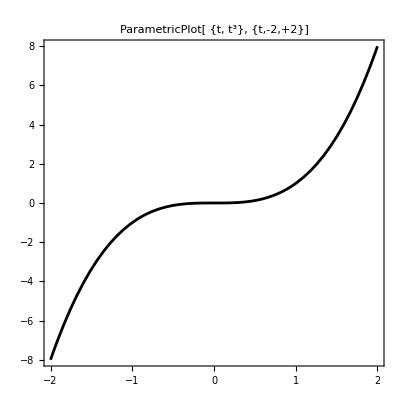

```mathematica
ParametricPlot[{t,t^3},{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {t, t^3}, {t,-2,+2}]"],16]]
```

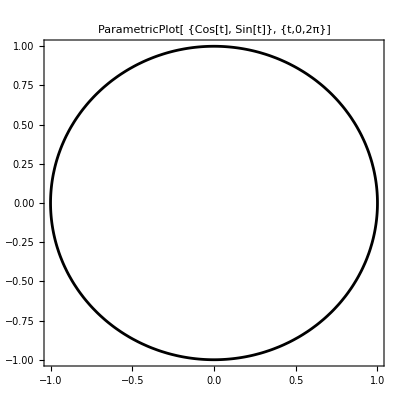

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {Cos[t], Sin[t]}, {t,0,2π}]"],16]]
```

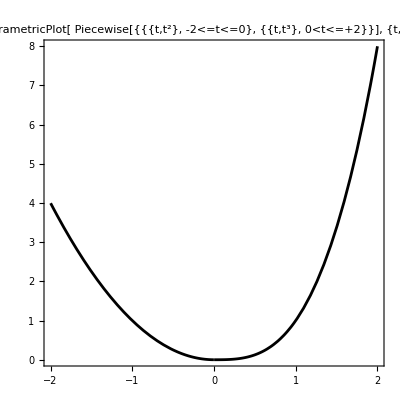

```mathematica
ParametricPlot[Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}], {t,-2,+2}]"],16]]
```

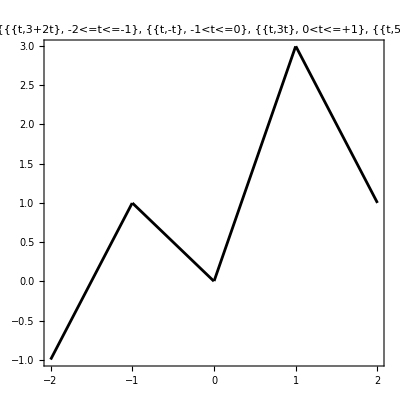

```mathematica
ParametricPlot[Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}], {t,-2,+2}]"],16]]
```

### 1.1.2 Path integrals

The scalar line integral of the function f along a curve C={r(u)∈ℝ^n,a≤u≤b} is given by:

-Graphics-"∮_C f(x)ⅆx=∫_a^b f(r(u)) Norm[r'(u)]ⅆu"

∫_a^b f(X_t) ⅆ X_t=∫_a^b f(X_t) ⅆt=∫_a^b f(X_t)dX_t/dt ⅆt

```mathematica
LineIntegrate[t^2,{x}∈ParametricRegion[{t^3},{{t,0,1}}]]
```

3/5

### 1.2.2 Examples

```mathematica
Table[nrsign[2,k],{k,1,12}]
```

{2,6,14,30,62,126,254,510,1022,2046,4094,8190}

```mathematica
nrsign[5,9]
```

2441405

```mathematica
Map[tensorfold,{{1},{5,55},{25/2,475/3,350/3,3025/2},{125/6,1125/4,1375/6,18875/6,2125/12,7250/3,2000,166375/6}}]
```

{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}}

```mathematica
Map[tensorfold[#,3]&,{{1},Range[3],Range[9],Range[27]}]
```

{{1},{1,2,3},{{1,2,3},{4,5,6},{7,8,9}},{{{1,2,3},{4,5,6},{7,8,9}},{{10,11,12},{13,14,15},{16,17,18}},{{19,20,21},{22,23,24},{25,26,27}}}}

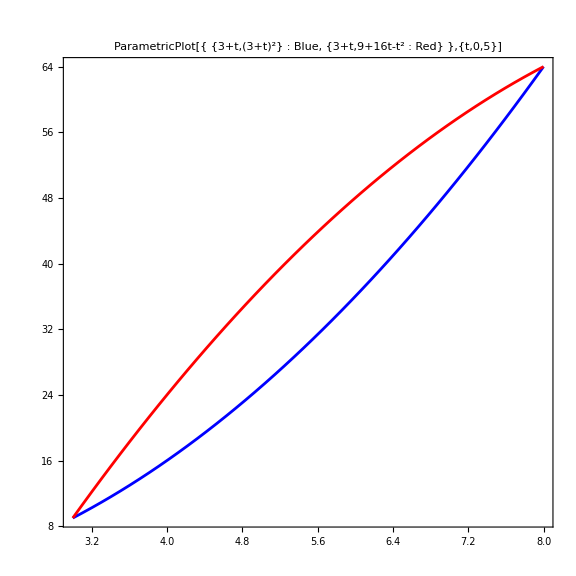

```mathematica
ParametricPlot[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{t,0,5},
Frame->True,AspectRatio->1,(*PlotLegends->"Expressions",*)
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
AxesOrigin->{3,9},PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"ParametricPlot[{
{3+t,(3+t)^2} : Blue,
{3+t,9+16t-t^2 : Red}
},{t,0,5}]"],16]]
```

```mathematica
signat[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{0,5}]
```

{{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}},{{1},{5,55},{{25/2,350/3},{475/3,3025/2}},{{{125/6,2125/12},{1375/6,2000}},{{1125/4,7250/3},{18875/6,166375/6}}}}}

## Sin

## Sin[k π t]

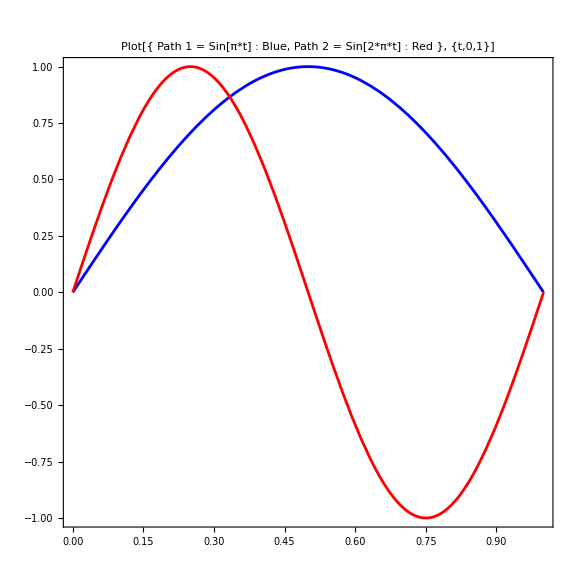

```mathematica
Plot[{Sin[π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,(*PlotLegends->"Expressions",*)AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π*t] : Blue,
Path 2 = Sin[2*π*t] : Red
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins=signat[{{t,Sin[π t]},{t,Sin[2π t]}},{0,1},5];]
```

{118.253,Null}

```mathematica
{sigsins1f,sigsins2f}=sigsins;
```

```mathematica
sigsins1f
```

{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}}

```mathematica
sigsins2f
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}

```mathematica
getcore6[sigsins1f,5]
```

{{1,0},{-2/π},{-1/π,1/4},{-(-4+π^2)/(2 π^3),1/8,-2/(9 π)},{1/π^3-1/(6 π),1/48 (2-3/π^2),-1/12+7/(8 π^2),-1/(9 π),1/(12 π),1/64}}

```mathematica
getcore6[sigsins2f,5]
```

{{1,0},{0},{1/(2 π),1/4},{1/(4 π),1/8,0},{(-3+2 π^2)/(24 π^3),1/24-1/(64 π^2),-1/12+7/(32 π^2),1/(18 π),-7/(24 π),1/64}}

## Sin[k π t^2]

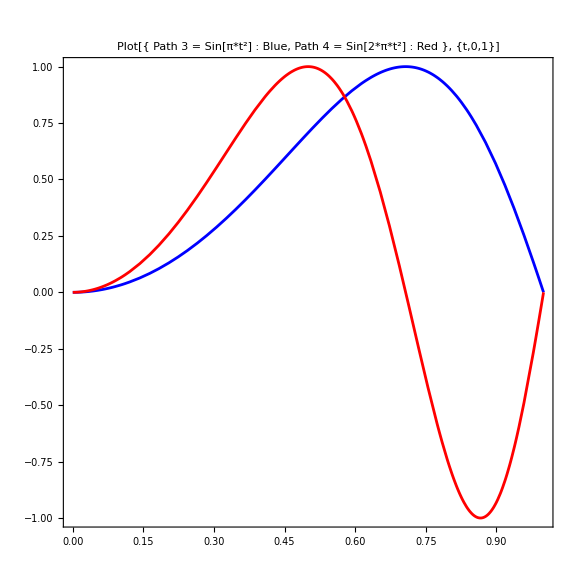

```mathematica
Plot[{Sin[π t^2],Sin[2π t^2]},{t,0,1},Frame->True,
PlotRange->All,(*PlotLegends->"Expressions",*)AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 3 = Sin[π*t^2] : Blue,
Path 4 = Sin[2*π*t^2] : Red
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins2=signat[{{t,Sin[π t^2]},{t,Sin[2π t^2]}},{0,1},5];]
```

{189.213,Null}

```mathematica
{sigsins1f2,sigsins2f2}={Append[Most[sigsins2[[1]]],N[Last[sigsins2[[1]]]]],Append[Most[sigsins2[[2]]],N[Last[sigsins2[[2]]]]]};
```

```mathematica
sigsins1f2
```

{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}},{{{{{0.00833333,-0.0265258},{-0.00323478,0.0433747}},{{0.00970435,-0.0200633},{0.0149393,-0.0353678}}},{{{0.0122565,-0.0393579},{-0.00371852,0.0546304}},{{0.0176846,-0.0470862},{0.010783,0.0114517}}}},{{{{0.00779975,-0.0273282},{-0.00609675,0.0514729}},{{0.00770722,-0.0150884},{0.0147373,-0.0458067}}},{{{0.0128588,-0.0439287},{-0.00719308,0.06871}},{{0.0170406,-0.0458067},{0.0114517,0.}}}}}}

```mathematica
sigsins2f2
```

{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}},{{{{{0.00833333,0.0132629},{-0.0229764,0.0423489}},{{-0.0106483,-0.0764914},{0.0744448,0.}}},{{{0.00855611,-0.024619},{-0.0330373,-0.0448062}},{{0.0377995,0.0990138},{-0.0707599,0.0126234}}}},{{{{0.0118056,0.0164127},{-0.0393608,0.0448062}},{{-0.0179426,-0.108415},{0.113266,-0.0504936}}},{{{0.0204454,0.00940129},{-0.0590584,0.0757405}},{{0.0165524,-0.0504936},{0.0126234,0.}}}}}}

## Sin[4 π t^k]

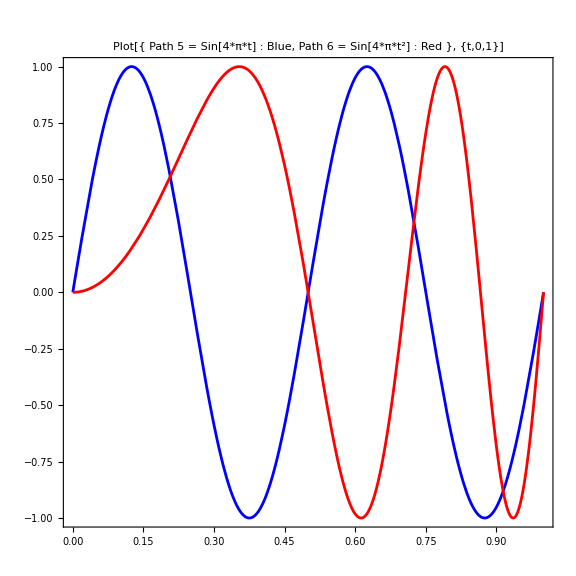

```mathematica
Plot[{Sin[4π t],Sin[4π t^2]},{t,0,1},Frame->True,
PlotRange->All,(*PlotLegends->"Expressions",*)AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 5 = Sin[4*π*t] : Blue,
Path 6 = Sin[4*π*t^2] : Red
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins42=signat[{{t,Sin[4π t]},{t,Sin[4π t^2]}},{0,1},4]]
```

{48.6126,{{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}},{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}},{{1},{1,0},{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}},{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/16 (4-FresnelC[4])}},{{FresnelS[2 √2]/(2 √2),1/8 (-4+FresnelC[4])},{1/16 (4-FresnelC[4]),0}}},{{{{1/24,(4-√2 FresnelC[2 √2])/(64 π)},{(3 (-4+√2 FresnelC[2 √2]))/(64 π),1/8}},{{(12-3 √2 FresnelC[2 √2]-8 √2 π FresnelS[2 √2])/(64 π),1/16 (-4+FresnelS[2 √2]^2)},{1/16 (4-FresnelC[4]-FresnelS[2 √2]^2),1/288 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])}}},{{{(-4+√2 FresnelC[2 √2]+8 √2 π FresnelS[2 √2])/(64 π),-1/16 FresnelS[2 √2]^2},{1/16 (-4+2 FresnelC[4]+FresnelS[2 √2]^2),1/96 (9 √2 FresnelS[2 √2]-√6 FresnelS[2 √6])}},{{1/16 (2-FresnelC[4]),1/96 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])},{(3 √3 FresnelS[2 √2]-FresnelS[2 √6])/(48 √6),0}}}}}}}

```mathematica
{sigsins1f42,sigsins2f42}=sigsins42;
```

```mathematica
Grid[{{sigsins1f[[2]]},{sigsins2f[[2]]},{sigsins1f2[[2]]},{sigsins2f2[[2]]},{sigsins1f42[[2]]},{sigsins2f42[[2]]}}]
```

{1,0}
{1,0}
{1,0}
{1,0}
{1,0}
{1,0}

```mathematica
Grid[{{sigsins1f[[3]]},{sigsins2f[[3]]},{sigsins1f2[[3]]},{sigsins2f2[[3]]},{sigsins1f42[[3]]},{sigsins2f42[[3]]}},Frame->All]
```

{{1/2,-2/π},{2/π,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}}
{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}}

```mathematica
Grid[Expand[{{sigsins1f[[4]]},{sigsins2f[[4]]},{sigsins1f2[[4]]},{sigsins2f2[[4]]},{sigsins1f42[[4]]},{sigsins2f42[[4]]}}],Frame->All]
```

{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}}
{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}}
{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/4-FresnelC[2]/8}},{{-1/π+FresnelS[√2]/(√2),-1/2+FresnelC[2]/4},{1/4-FresnelC[2]/8,0}}}
{{{1/6,0},{-FresnelS[2]/2,1/4-FresnelC[2 √2]/(8 √2)}},{{FresnelS[2]/2,-1/2+FresnelC[2 √2]/(4 √2)},{1/4-FresnelC[2 √2]/(8 √2),0}}}
{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}}
{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/4-FresnelC[4]/16}},{{FresnelS[2 √2]/(2 √2),-1/2+FresnelC[4]/8},{1/4-FresnelC[4]/16,0}}}

```mathematica
Grid[Expand[{{sigsins1f[[5]]},{sigsins2f[[5]]},{sigsins1f2[[5]]},{sigsins2f2[[5]]},{sigsins1f42[[5]]},{sigsins2f42[[5]]}}],Frame->All]
```

{{{{1/24,2/π^3-1/(2 π)},{-6/π^3+1/(2 π),1/8}},{{6/π^3-1/(2 π),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{-2/π^3+1/(2 π),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}}
{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,-1/(4 π)-FresnelC[√2]/(4 √2 π)},{-1/(4 π)+(3 FresnelC[√2])/(4 √2 π),1/8}},{{5/(4 π)-(3 FresnelC[√2])/(4 √2 π)-FresnelS[√2]/(2 √2),-1/4+1/4 FresnelS[√2]^2},{1/4-FresnelC[2]/8-1/4 FresnelS[√2]^2,-FresnelS[√2]/(8 √2)+FresnelS[√6]/(24 √6)}}},{{{-3/(4 π)+FresnelC[√2]/(4 √2 π)+FresnelS[√2]/(2 √2),-1/4 FresnelS[√2]^2},{-1/4+FresnelC[2]/4+1/4 FresnelS[√2]^2,(3 FresnelS[√2])/(8 √2)-FresnelS[√6]/(8 √6)}},{{1/8-FresnelC[2]/8,-(3 FresnelS[√2])/(8 √2)+FresnelS[√6]/(8 √6)},{FresnelS[√2]/(8 √2)-FresnelS[√6]/(24 √6),0}}}}
{{{{1/24,1/(8 π)-FresnelC[2]/(16 π)},{-3/(8 π)+(3 FresnelC[2])/(16 π),1/8}},{{3/(8 π)-(3 FresnelC[2])/(16 π)-FresnelS[2]/4,-1/4+FresnelS[2]^2/8},{1/4-FresnelC[2 √2]/(8 √2)-FresnelS[2]^2/8,-FresnelS[2]/16+FresnelS[2 √3]/(48 √3)}}},{{{-1/(8 π)+FresnelC[2]/(16 π)+FresnelS[2]/4,-1/8 FresnelS[2]^2},{-1/4+FresnelC[2 √2]/(4 √2)+FresnelS[2]^2/8,(3 FresnelS[2])/16-FresnelS[2 √3]/(16 √3)}},{{1/8-FresnelC[2 √2]/(8 √2),-(3 FresnelS[2])/16+FresnelS[2 √3]/(16 √3)},{FresnelS[2]/16-FresnelS[2 √3]/(48 √3),0}}}}
{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,1/(16 π)-FresnelC[2 √2]/(32 √2 π)},{-3/(16 π)+(3 FresnelC[2 √2])/(32 √2 π),1/8}},{{3/(16 π)-(3 FresnelC[2 √2])/(32 √2 π)-FresnelS[2 √2]/(4 √2),-1/4+1/16 FresnelS[2 √2]^2},{1/4-FresnelC[4]/16-1/16 FresnelS[2 √2]^2,-FresnelS[2 √2]/(16 √2)+FresnelS[2 √6]/(48 √6)}}},{{{-1/(16 π)+FresnelC[2 √2]/(32 √2 π)+FresnelS[2 √2]/(4 √2),-1/16 FresnelS[2 √2]^2},{-1/4+FresnelC[4]/8+1/16 FresnelS[2 √2]^2,(3 FresnelS[2 √2])/(16 √2)-FresnelS[2 √6]/(16 √6)}},{{1/8-FresnelC[4]/16,-(3 FresnelS[2 √2])/(16 √2)+FresnelS[2 √6]/(16 √6)},{FresnelS[2 √2]/(16 √2)-FresnelS[2 √6]/(48 √6),0}}}}

```mathematica
Timing[sigline=signat[{{Subscript[a, 1]+Subscript[b, 1]*t,Subscript[a, 2]+Subscript[b, 2]*t}},{0,T},3]]
```

{0.001466,{{{1},{T b_1,T b_2},{{1/2 T^2 b_1^2,1/2 T^2 b_1 b_2},{1/2 T^2 b_1 b_2,1/2 T^2 b_2^2}},{{{1/6 T^3 b_1^3,1/6 T^3 b_1^2 b_2},{1/6 T^3 b_1^2 b_2,1/6 T^3 b_1 b_2^2}},{{1/6 T^3 b_1^2 b_2,1/6 T^3 b_1 b_2^2},{1/6 T^3 b_1 b_2^2,1/6 T^3 b_2^3}}}}}}

## Tensor Rank

```mathematica
MatrixRank
```

```mathematica
TensorRank[Table[sind[{i}],{i,1,2}]]
```

1

```mathematica
TensorRank[Table[sind[{i,j}],{i,1,2},{j,1,2}]]
```

2

```mathematica
TensorRank[Table[sind[{i,j,k}],{i,1,2},{j,1,2},{k,1,2}]]
```

3

```mathematica
Table[sind[{i,j}],{i,1,2},{j,1,2}]
```

{{s_(1,1),s_(1,2)},{s_(2,1),s_(2,2)}}

```mathematica
{{Subscript[s, 1,1]->Subscript[s, 1]^2/2},{Subscript[s, 2,1]->Subscript[s, 1] Subscript[s, 2]-Subscript[s, 1,2]},{Subscript[s, 2,2]->Subscript[s, 2]^2/2}}
```

```mathematica
sl2={{Subscript[s, 1]^2/2,Subscript[s, 1,2]},{Subscript[s, 1] Subscript[s, 2]-Subscript[s, 1,2],Subscript[s, 2]^2/2}}
```

{{s_1^2/2,s_(1,2)},{s_1 s_2-s_(1,2),s_2^2/2}}

```mathematica
Table[sind[{i,j,k}],{i,1,2},{j,1,2},{k,1,2}]
```

{{{s_(1,1,1),s_(1,1,2)},{s_(1,2,1),s_(1,2,2)}},{{s_(2,1,1),s_(2,1,2)},{s_(2,2,1),s_(2,2,2)}}}

```mathematica
{{Subscript[s, 1,1,1]->Subscript[s, 1]^3/6},{Subscript[s, 1,2,1]->Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2]},{Subscript[s, 2,1,1]->1/2 (Subscript[s, 1]^2 Subscript[s, 2]-2 Subscript[s, 1] Subscript[s, 1,2])+Subscript[s, 1,1,2]},{Subscript[s, 2,1,2]->Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{Subscript[s, 2,2,1]->1/2 (Subscript[s, 1] Subscript[s, 2]^2-2 Subscript[s, 2] Subscript[s, 1,2])+Subscript[s, 1,2,2]},{Subscript[s, 2,2,2]->Subscript[s, 2]^3/6}}
```

```mathematica
sl3={{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 (Subscript[s, 1]^2 Subscript[s, 2]-2 Subscript[s, 1] Subscript[s, 1,2])+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 (Subscript[s, 1] Subscript[s, 2]^2-2 Subscript[s, 2] Subscript[s, 1,2])+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

{{{s_1^3/6,s_(1,1,2)},{s_1 s_(1,2)-2 s_(1,1,2),s_(1,2,2)}},{{1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2),s_2 s_(1,2)-2 s_(1,2,2)},{1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2),s_2^3/6}}}

```mathematica
TensorRank[sl3]
```

3

```mathematica
sl2-1/2 TensorProduct[{Subscript[s, 1] ,Subscript[s, 2]},{Subscript[s, 1] ,Subscript[s, 2]}]
```

{{0,-1/2 s_1 s_2+s_(1,2)},{(s_1 s_2)/2-s_(1,2),0}}

```mathematica
TensorProduct[{1 ,Subscript[s, 1,2]},{Subscript[s, 1] ,Subscript[s, 2]}]
```

{{s_1,s_2},{s_1 s_(1,2),s_2 s_(1,2)}}

## Polynomials

## D=1

```mathematica
Timing[sigpols1a=signat[{{x11*t,x21*t}},{0,1},5][[1]];]
```

{0.009877,Null}

```mathematica
sigpols1a
```

{{1},{x11,x21},{{x11^2/2,(x11 x21)/2},{(x11 x21)/2,x21^2/2}},{{{x11^3/6,(x11^2 x21)/6},{(x11^2 x21)/6,(x11 x21^2)/6}},{{(x11^2 x21)/6,(x11 x21^2)/6},{(x11 x21^2)/6,x21^3/6}}},{{{{x11^4/24,(x11^3 x21)/24},{(x11^3 x21)/24,(x11^2 x21^2)/24}},{{(x11^3 x21)/24,(x11^2 x21^2)/24},{(x11^2 x21^2)/24,(x11 x21^3)/24}}},{{{(x11^3 x21)/24,(x11^2 x21^2)/24},{(x11^2 x21^2)/24,(x11 x21^3)/24}},{{(x11^2 x21^2)/24,(x11 x21^3)/24},{(x11 x21^3)/24,x21^4/24}}}},{{{{{x11^5/120,(x11^4 x21)/120},{(x11^4 x21)/120,(x11^3 x21^2)/120}},{{(x11^4 x21)/120,(x11^3 x21^2)/120},{(x11^3 x21^2)/120,(x11^2 x21^3)/120}}},{{{(x11^4 x21)/120,(x11^3 x21^2)/120},{(x11^3 x21^2)/120,(x11^2 x21^3)/120}},{{(x11^3 x21^2)/120,(x11^2 x21^3)/120},{(x11^2 x21^3)/120,(x11 x21^4)/120}}}},{{{{(x11^4 x21)/120,(x11^3 x21^2)/120},{(x11^3 x21^2)/120,(x11^2 x21^3)/120}},{{(x11^3 x21^2)/120,(x11^2 x21^3)/120},{(x11^2 x21^3)/120,(x11 x21^4)/120}}},{{{(x11^3 x21^2)/120,(x11^2 x21^3)/120},{(x11^2 x21^3)/120,(x11 x21^4)/120}},{{(x11^2 x21^3)/120,(x11 x21^4)/120},{(x11 x21^4)/120,x21^5/120}}}}}}

```mathematica
getcore6[sigpols1a,5]
```

{{x11,x21},{(x11 x21)/2},{(x11^2 x21)/6,(x11 x21^2)/6},{(x11^3 x21)/24,(x11^2 x21^2)/24,(x11 x21^3)/24},{(x11^4 x21)/120,(x11^3 x21^2)/120,(x11^3 x21^2)/120,(x11^2 x21^3)/120,(x11^2 x21^3)/120,(x11 x21^4)/120}}

## D=2

```mathematica
Timing[sigpols2ab=signat[{{x11*t+x12*t^2,x21*t+x22*t^2}},{0,1},5][[1]];]
```

{120.015,Null}

```mathematica
sigpols2ab
```

{{1},{x11+x12,x21+x22},{{x11^2/2+x11 x12+x12^2/2,(x11 x21)/2+(x12 x21)/3+(2 x11 x22)/3+(x12 x22)/2},{(x11 x21)/2+(2 x12 x21)/3+(x11 x22)/3+(x12 x22)/2,x21^2/2+x21 x22+x22^2/2}},{{{x11^3/6+(x11^2 x12)/2+(x11 x12^2)/2+x12^3/6,(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6},{(x11^2 x21)/6+(x11 x12 x21)/3+(2 x12^2 x21)/15+(x11^2 x22)/6+(11 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6}},{{(x11^2 x21)/6+(5 x11 x12 x21)/12+(4 x12^2 x21)/15+(x11^2 x22)/12+(7 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/6+(x11 x21 x22)/3+(11 x12 x21 x22)/30+(2 x11 x22^2)/15+(x12 x22^2)/6},{(x11 x21^2)/6+(x12 x21^2)/4+(x11 x21 x22)/4+(2 x12 x21 x22)/5+(x11 x22^2)/10+(x12 x22^2)/6,x21^3/6+(x21^2 x22)/2+(x21 x22^2)/2+x22^3/6}}},{{{{x11^4/24+(x11^3 x12)/6+(x11^2 x12^2)/4+(x11 x12^3)/6+x12^4/24,(x11^3 x21)/24+1/10 x11^2 x12 x21+1/12 x11 x12^2 x21+(x12^3 x21)/42+(x11^3 x22)/15+1/6 x11^2 x12 x22+1/7 x11 x12^2 x22+(x12^3 x22)/24},{(x11^3 x21)/24+7/60 x11^2 x12 x21+1/10 x11 x12^2 x21+(x12^3 x21)/35+(x11^3 x22)/20+3/20 x11^2 x12 x22+29/210 x11 x12^2 x22+(x12^3 x22)/24,(x11^2 x21^2)/24+1/20 x11 x12 x21^2+(x12^2 x21^2)/60+7/60 x11^2 x21 x22+3/20 x11 x12 x21 x22+11/210 x12^2 x21 x22+(x11^2 x22^2)/12+4/35 x11 x12 x22^2+(x12^2 x22^2)/24}},{{(x11^3 x21)/24+2/15 x11^2 x12 x21+2/15 x11 x12^2 x21+(4 x12^3 x21)/105+(x11^3 x22)/30+7/60 x11^2 x12 x22+9/70 x11 x12^2 x22+(x12^3 x22)/24,(x11^2 x21^2)/24+1/15 x11 x12 x21^2+(x12^2 x21^2)/45+1/10 x11^2 x21 x22+31/180 x11 x12 x21 x22+13/210 x12^2 x21 x22+(x11^2 x22^2)/18+11/105 x11 x12 x22^2+(x12^2 x22^2)/24},{(x11^2 x21^2)/24+1/12 x11 x12 x21^2+(x12^2 x21^2)/36+1/12 x11^2 x21 x22+8/45 x11 x12 x21 x22+1/15 x12^2 x21 x22+(2 x11^2 x22^2)/45+1/10 x11 x12 x22^2+(x12^2 x22^2)/24,(x11 x21^3)/24+(x12 x21^3)/60+3/20 x11 x21^2 x22+1/15 x12 x21^2 x22+11/60 x11 x21 x22^2+19/210 x12 x21 x22^2+(8 x11 x22^3)/105+(x12 x22^3)/24}}},{{{(x11^3 x21)/24+3/20 x11^2 x12 x21+11/60 x11 x12^2 x21+(8 x12^3 x21)/105+(x11^3 x22)/60+1/15 x11^2 x12 x22+19/210 x11 x12^2 x22+(x12^3 x22)/24,(x11^2 x21^2)/24+1/12 x11 x12 x21^2+(2 x12^2 x21^2)/45+1/12 x11^2 x21 x22+8/45 x11 x12 x21 x22+1/10 x12^2 x21 x22+(x11^2 x22^2)/36+1/15 x11 x12 x22^2+(x12^2 x22^2)/24},{(x11^2 x21^2)/24+1/10 x11 x12 x21^2+(x12^2 x21^2)/18+1/15 x11^2 x21 x22+31/180 x11 x12 x21 x22+11/105 x12^2 x21 x22+(x11^2 x22^2)/45+13/210 x11 x12 x22^2+(x12^2 x22^2)/24,(x11 x21^3)/24+(x12 x21^3)/30+2/15 x11 x21^2 x22+7/60 x12 x21^2 x22+2/15 x11 x21 x22^2+9/70 x12 x21 x22^2+(4 x11 x22^3)/105+(x12 x22^3)/24}},{{(x11^2 x21^2)/24+7/60 x11 x12 x21^2+(x12^2 x21^2)/12+1/20 x11^2 x21 x22+3/20 x11 x12 x21 x22+4/35 x12^2 x21 x22+(x11^2 x22^2)/60+11/210 x11 x12 x22^2+(x12^2 x22^2)/24,(x11 x21^3)/24+(x12 x21^3)/20+7/60 x11 x21^2 x22+3/20 x12 x21^2 x22+1/10 x11 x21 x22^2+29/210 x12 x21 x22^2+(x11 x22^3)/35+(x12 x22^3)/24},{(x11 x21^3)/24+(x12 x21^3)/15+1/10 x11 x21^2 x22+1/6 x12 x21^2 x22+1/12 x11 x21 x22^2+1/7 x12 x21 x22^2+(x11 x22^3)/42+(x12 x22^3)/24,x21^4/24+(x21^3 x22)/6+(x21^2 x22^2)/4+(x21 x22^3)/6+x22^4/24}}}},{{{{{x11^5/120+(x11^4 x12)/24+(x11^3 x12^2)/12+(x11^2 x12^3)/12+(x11 x12^4)/24+x12^5/120,(x11^4 x21)/120+1/36 x11^3 x12 x21+1/28 x11^2 x12^2 x21+1/48 x11 x12^3 x21+(x12^4 x21)/216+(x11^4 x22)/72+1/21 x11^3 x12 x22+1/16 x11^2 x12^2 x22+1/27 x11 x12^3 x22+(x12^4 x22)/120},{(x11^4 x21)/120+11/360 x11^3 x12 x21+17/420 x11^2 x12^2 x21+1/42 x11 x12^3 x21+(x12^4 x21)/189+(x11^4 x22)/90+3/70 x11^3 x12 x22+5/84 x11^2 x12^2 x22+(55 x11 x12^3 x22)/1512+(x12^4 x22)/120,(x11^3 x21^2)/120+1/60 x11^2 x12 x21^2+1/84 x11 x12^2 x21^2+(x12^3 x21^2)/336+1/40 x11^3 x21 x22+11/210 x11^2 x12 x21 x22+13/336 x11 x12^2 x21 x22+5/504 x12^3 x21 x22+(2 x11^3 x22^2)/105+1/24 x11^2 x12 x22^2+2/63 x11 x12^2 x22^2+(x12^3 x22^2)/120}},{{(x11^4 x21)/120+1/30 x11^3 x12 x21+1/21 x11^2 x12^2 x21+1/35 x11 x12^3 x21+(2 x12^4 x21)/315+(x11^4 x22)/120+1/28 x11^3 x12 x22+23/420 x11^2 x12^2 x22+(89 x11 x12^3 x22)/2520+(x12^4 x22)/120,(x11^3 x21^2)/120+7/360 x11^2 x12 x21^2+1/70 x11 x12^2 x21^2+(x12^3 x21^2)/280+1/45 x11^3 x21 x22+23/420 x11^2 x12 x21 x22+(71 x11 x12^2 x21 x22)/1680+(83 x12^3 x21 x22)/7560+(x11^3 x22^2)/70+3/80 x11^2 x12 x22^2+29/945 x11 x12^2 x22^2+(x12^3 x22^2)/120},{(x11^3 x21^2)/120+1/45 x11^2 x12 x21^2+1/60 x11 x12^2 x21^2+(x12^3 x21^2)/240+7/360 x11^3 x21 x22+23/420 x11^2 x12 x21 x22+37/840 x11 x12^2 x21 x22+11/945 x12^3 x21 x22+(x11^3 x22^2)/84+(59 x11^2 x12 x22^2)/1680+(227 x11 x12^2 x22^2)/7560+(x12^3 x22^2)/120,(x11^2 x21^3)/120+1/120 x11 x12 x21^3+(x12^2 x21^3)/420+1/30 x11^2 x21^2 x22+1/28 x11 x12 x21^2 x22+3/280 x12^2 x21^2 x22+19/420 x11^2 x21 x22^2+29/560 x11 x12 x21 x22^2+(41 x12^2 x21 x22^2)/2520+(x11^2 x22^3)/48+8/315 x11 x12 x22^3+(x12^2 x22^3)/120}}},{{{(x11^4 x21)/120+13/360 x11^3 x12 x21+2/35 x11^2 x12^2 x21+4/105 x11 x12^3 x21+(8 x12^4 x21)/945+(x11^4 x22)/180+11/420 x11^3 x12 x22+19/420 x11^2 x12^2 x22+(251 x11 x12^3 x22)/7560+(x12^4 x22)/120,(x11^3 x21^2)/120+1/45 x11^2 x12 x21^2+2/105 x11 x12^2 x21^2+(x12^3 x21^2)/210+7/360 x11^3 x21 x22+23/420 x11^2 x12 x21 x22+(83 x11 x12^2 x21 x22)/1680+11/840 x12^3 x21 x22+(x11^3 x22^2)/105+7/240 x11^2 x12 x22^2+1/35 x11 x12^2 x22^2+(x12^3 x22^2)/120},{(x11^3 x21^2)/120+1/40 x11^2 x12 x21^2+1/45 x11 x12^2 x21^2+(x12^3 x21^2)/180+1/60 x11^3 x21 x22+(67 x11^2 x12 x21 x22)/1260+16/315 x11 x12^2 x21 x22+13/945 x12^3 x21 x22+(x11^3 x22^2)/126+17/630 x11^2 x12 x22^2+(211 x11 x12^2 x22^2)/7560+(x12^3 x22^2)/120,(x11^2 x21^3)/120+1/90 x11 x12 x21^3+(x12^2 x21^3)/315+11/360 x11^2 x21^2 x22+11/252 x11 x12 x21^2 x22+(67 x12^2 x21^2 x22)/5040+23/630 x11^2 x21 x22^2+(283 x11 x12 x21 x22^2)/5040+(139 x12^2 x21 x22^2)/7560+(x11^2 x22^3)/72+22/945 x11 x12 x22^3+(x12^2 x22^3)/120}},{{(x11^3 x21^2)/120+1/36 x11^2 x12 x21^2+1/36 x11 x12^2 x21^2+(x12^3 x21^2)/144+1/72 x11^3 x21 x22+31/630 x11^2 x12 x21 x22+19/360 x11 x12^2 x21 x22+2/135 x12^3 x21 x22+(2 x11^3 x22^2)/315+17/720 x11^2 x12 x22^2+(29 x11 x12^2 x22^2)/1080+(x12^3 x22^2)/120,(x11^2 x21^3)/120+1/72 x11 x12 x21^3+(x12^2 x21^3)/252+1/36 x11^2 x21^2 x22+31/630 x11 x12 x21^2 x22+11/720 x12^2 x21^2 x22+19/630 x11^2 x21 x22^2+41/720 x11 x12 x21 x22^2+7/360 x12^2 x21 x22^2+(x11^2 x22^3)/90+1/45 x11 x12 x22^3+(x12^2 x22^3)/120},{(x11^2 x21^3)/120+1/60 x11 x12 x21^3+(x12^2 x21^3)/210+1/40 x11^2 x21^2 x22+11/210 x11 x12 x21^2 x22+1/60 x12^2 x21^2 x22+11/420 x11^2 x21 x22^2+2/35 x11 x12 x21 x22^2+19/945 x12^2 x21 x22^2+(x11^2 x22^3)/105+(163 x11 x12 x22^3)/7560+(x12^2 x22^3)/120,(x11 x21^4)/120+(x12 x21^4)/360+7/180 x11 x21^3 x22+1/70 x12 x21^3 x22+29/420 x11 x21^2 x22^2+(47 x12 x21^2 x22^2)/1680+31/560 x11 x21 x22^3+(187 x12 x21 x22^3)/7560+(16 x11 x22^4)/945+(x12 x22^4)/120}}}},{{{{(x11^4 x21)/120+7/180 x11^3 x12 x21+29/420 x11^2 x12^2 x21+31/560 x11 x12^3 x21+(16 x12^4 x21)/945+(x11^4 x22)/360+1/70 x11^3 x12 x22+(47 x11^2 x12^2 x22)/1680+(187 x11 x12^3 x22)/7560+(x12^4 x22)/120,(x11^3 x21^2)/120+1/40 x11^2 x12 x21^2+11/420 x11 x12^2 x21^2+(x12^3 x21^2)/105+1/60 x11^3 x21 x22+11/210 x11^2 x12 x21 x22+2/35 x11 x12^2 x21 x22+(163 x12^3 x21 x22)/7560+(x11^3 x22^2)/210+1/60 x11^2 x12 x22^2+19/945 x11 x12^2 x22^2+(x12^3 x22^2)/120},{(x11^3 x21^2)/120+1/36 x11^2 x12 x21^2+19/630 x11 x12^2 x21^2+(x12^3 x21^2)/90+1/72 x11^3 x21 x22+31/630 x11^2 x12 x21 x22+41/720 x11 x12^2 x21 x22+1/45 x12^3 x21 x22+(x11^3 x22^2)/252+11/720 x11^2 x12 x22^2+7/360 x11 x12^2 x22^2+(x12^3 x22^2)/120,(x11^2 x21^3)/120+1/72 x11 x12 x21^3+(2 x12^2 x21^3)/315+1/36 x11^2 x21^2 x22+31/630 x11 x12 x21^2 x22+17/720 x12^2 x21^2 x22+1/36 x11^2 x21 x22^2+19/360 x11 x12 x21 x22^2+(29 x12^2 x21 x22^2)/1080+(x11^2 x22^3)/144+2/135 x11 x12 x22^3+(x12^2 x22^3)/120}},{{(x11^3 x21^2)/120+11/360 x11^2 x12 x21^2+23/630 x11 x12^2 x21^2+(x12^3 x21^2)/72+1/90 x11^3 x21 x22+11/252 x11^2 x12 x21 x22+(283 x11 x12^2 x21 x22)/5040+22/945 x12^3 x21 x22+(x11^3 x22^2)/315+(67 x11^2 x12 x22^2)/5040+(139 x11 x12^2 x22^2)/7560+(x12^3 x22^2)/120,(x11^2 x21^3)/120+1/60 x11 x12 x21^3+(x12^2 x21^3)/126+1/40 x11^2 x21^2 x22+(67 x11 x12 x21^2 x22)/1260+17/630 x12^2 x21^2 x22+1/45 x11^2 x21 x22^2+16/315 x11 x12 x21 x22^2+(211 x12^2 x21 x22^2)/7560+(x11^2 x22^3)/180+13/945 x11 x12 x22^3+(x12^2 x22^3)/120},{(x11^2 x21^3)/120+7/360 x11 x12 x21^3+(x12^2 x21^3)/105+1/45 x11^2 x21^2 x22+23/420 x11 x12 x21^2 x22+7/240 x12^2 x21^2 x22+2/105 x11^2 x21 x22^2+(83 x11 x12 x21 x22^2)/1680+1/35 x12^2 x21 x22^2+(x11^2 x22^3)/210+11/840 x11 x12 x22^3+(x12^2 x22^3)/120,(x11 x21^4)/120+(x12 x21^4)/180+13/360 x11 x21^3 x22+11/420 x12 x21^3 x22+2/35 x11 x21^2 x22^2+19/420 x12 x21^2 x22^2+4/105 x11 x21 x22^3+(251 x12 x21 x22^3)/7560+(8 x11 x22^4)/945+(x12 x22^4)/120}}},{{{(x11^3 x21^2)/120+1/30 x11^2 x12 x21^2+19/420 x11 x12^2 x21^2+(x12^3 x21^2)/48+1/120 x11^3 x21 x22+1/28 x11^2 x12 x21 x22+29/560 x11 x12^2 x21 x22+8/315 x12^3 x21 x22+(x11^3 x22^2)/420+3/280 x11^2 x12 x22^2+(41 x11 x12^2 x22^2)/2520+(x12^3 x22^2)/120,(x11^2 x21^3)/120+7/360 x11 x12 x21^3+(x12^2 x21^3)/84+1/45 x11^2 x21^2 x22+23/420 x11 x12 x21^2 x22+(59 x12^2 x21^2 x22)/1680+1/60 x11^2 x21 x22^2+37/840 x11 x12 x21 x22^2+(227 x12^2 x21 x22^2)/7560+(x11^2 x22^3)/240+11/945 x11 x12 x22^3+(x12^2 x22^3)/120},{(x11^2 x21^3)/120+1/45 x11 x12 x21^3+(x12^2 x21^3)/70+7/360 x11^2 x21^2 x22+23/420 x11 x12 x21^2 x22+3/80 x12^2 x21^2 x22+1/70 x11^2 x21 x22^2+(71 x11 x12 x21 x22^2)/1680+29/945 x12^2 x21 x22^2+(x11^2 x22^3)/280+(83 x11 x12 x22^3)/7560+(x12^2 x22^3)/120,(x11 x21^4)/120+(x12 x21^4)/120+1/30 x11 x21^3 x22+1/28 x12 x21^3 x22+1/21 x11 x21^2 x22^2+23/420 x12 x21^2 x22^2+1/35 x11 x21 x22^3+(89 x12 x21 x22^3)/2520+(2 x11 x22^4)/315+(x12 x22^4)/120}},{{(x11^2 x21^3)/120+1/40 x11 x12 x21^3+(2 x12^2 x21^3)/105+1/60 x11^2 x21^2 x22+11/210 x11 x12 x21^2 x22+1/24 x12^2 x21^2 x22+1/84 x11^2 x21 x22^2+13/336 x11 x12 x21 x22^2+2/63 x12^2 x21 x22^2+(x11^2 x22^3)/336+5/504 x11 x12 x22^3+(x12^2 x22^3)/120,(x11 x21^4)/120+(x12 x21^4)/90+11/360 x11 x21^3 x22+3/70 x12 x21^3 x22+17/420 x11 x21^2 x22^2+5/84 x12 x21^2 x22^2+1/42 x11 x21 x22^3+(55 x12 x21 x22^3)/1512+(x11 x22^4)/189+(x12 x22^4)/120},{(x11 x21^4)/120+(x12 x21^4)/72+1/36 x11 x21^3 x22+1/21 x12 x21^3 x22+1/28 x11 x21^2 x22^2+1/16 x12 x21^2 x22^2+1/48 x11 x21 x22^3+1/27 x12 x21 x22^3+(x11 x22^4)/216+(x12 x22^4)/120,x21^5/120+(x21^4 x22)/24+(x21^3 x22^2)/12+(x21^2 x22^3)/12+(x21 x22^4)/24+x22^5/120}}}}}}

```mathematica
sigpols2ab[[4]]
```

{{{x11^3/6+(x11^2 x12)/2+(x11 x12^2)/2+x12^3/6,(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6},{(x11^2 x21)/6+(x11 x12 x21)/3+(2 x12^2 x21)/15+(x11^2 x22)/6+(11 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6}},{{(x11^2 x21)/6+(5 x11 x12 x21)/12+(4 x12^2 x21)/15+(x11^2 x22)/12+(7 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/6+(x11 x21 x22)/3+(11 x12 x21 x22)/30+(2 x11 x22^2)/15+(x12 x22^2)/6},{(x11 x21^2)/6+(x12 x21^2)/4+(x11 x21 x22)/4+(2 x12 x21 x22)/5+(x11 x22^2)/10+(x12 x22^2)/6,x21^3/6+(x21^2 x22)/2+(x21 x22^2)/2+x22^3/6}}}

```mathematica
TensorRank[sigpols2ab[[3]]]
```

2

```mathematica
sigpols2ab[[3]]//.{x11->0,x12->0,x21->0,x22->0}
```

{{0,0},{0,0}}

```mathematica
TensorRank[sigpols2ab[[3]]//.{x11->0,x12->0,x21->0,x22->0}]
```

2

```mathematica
getcore6[sigpols2ab,5]
```

{{x11+x12,x21+x22},{(x11 x21)/2+(x12 x21)/3+(2 x11 x22)/3+(x12 x22)/2},{(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6},{(x11^3 x21)/24+1/10 x11^2 x12 x21+1/12 x11 x12^2 x21+(x12^3 x21)/42+(x11^3 x22)/15+1/6 x11^2 x12 x22+1/7 x11 x12^2 x22+(x12^3 x22)/24,(x11^2 x21^2)/24+1/20 x11 x12 x21^2+(x12^2 x21^2)/60+7/60 x11^2 x21 x22+3/20 x11 x12 x21 x22+11/210 x12^2 x21 x22+(x11^2 x22^2)/12+4/35 x11 x12 x22^2+(x12^2 x22^2)/24,(x11 x21^3)/24+(x12 x21^3)/60+3/20 x11 x21^2 x22+1/15 x12 x21^2 x22+11/60 x11 x21 x22^2+19/210 x12 x21 x22^2+(8 x11 x22^3)/105+(x12 x22^3)/24},{(x11^4 x21)/120+1/36 x11^3 x12 x21+1/28 x11^2 x12^2 x21+1/48 x11 x12^3 x21+(x12^4 x21)/216+(x11^4 x22)/72+1/21 x11^3 x12 x22+1/16 x11^2 x12^2 x22+1/27 x11 x12^3 x22+(x12^4 x22)/120,(x11^3 x21^2)/120+1/60 x11^2 x12 x21^2+1/84 x11 x12^2 x21^2+(x12^3 x21^2)/336+1/40 x11^3 x21 x22+11/210 x11^2 x12 x21 x22+13/336 x11 x12^2 x21 x22+5/504 x12^3 x21 x22+(2 x11^3 x22^2)/105+1/24 x11^2 x12 x22^2+2/63 x11 x12^2 x22^2+(x12^3 x22^2)/120,(x11^3 x21^2)/120+7/360 x11^2 x12 x21^2+1/70 x11 x12^2 x21^2+(x12^3 x21^2)/280+1/45 x11^3 x21 x22+23/420 x11^2 x12 x21 x22+(71 x11 x12^2 x21 x22)/1680+(83 x12^3 x21 x22)/7560+(x11^3 x22^2)/70+3/80 x11^2 x12 x22^2+29/945 x11 x12^2 x22^2+(x12^3 x22^2)/120,(x11^2 x21^3)/120+1/120 x11 x12 x21^3+(x12^2 x21^3)/420+1/30 x11^2 x21^2 x22+1/28 x11 x12 x21^2 x22+3/280 x12^2 x21^2 x22+19/420 x11^2 x21 x22^2+29/560 x11 x12 x21 x22^2+(41 x12^2 x21 x22^2)/2520+(x11^2 x22^3)/48+8/315 x11 x12 x22^3+(x12^2 x22^3)/120,(x11^2 x21^3)/120+1/90 x11 x12 x21^3+(x12^2 x21^3)/315+11/360 x11^2 x21^2 x22+11/252 x11 x12 x21^2 x22+(67 x12^2 x21^2 x22)/5040+23/630 x11^2 x21 x22^2+(283 x11 x12 x21 x22^2)/5040+(139 x12^2 x21 x22^2)/7560+(x11^2 x22^3)/72+22/945 x11 x12 x22^3+(x12^2 x22^3)/120,(x11 x21^4)/120+(x12 x21^4)/360+7/180 x11 x21^3 x22+1/70 x12 x21^3 x22+29/420 x11 x21^2 x22^2+(47 x12 x21^2 x22^2)/1680+31/560 x11 x21 x22^3+(187 x12 x21 x22^3)/7560+(16 x11 x22^4)/945+(x12 x22^4)/120}}

```mathematica
getcore6[sigpols2ab,3]
```

{{x11+x12,x21+x22},{(x11 x21)/2+(x12 x21)/3+(2 x11 x22)/3+(x12 x22)/2},{(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6}}

## Shuffle Product

### Typesetting

Enter ⧢

```mathematica
{1,2}⧢{a}={{a,1,2},{1,a,2},{1,2,a}}
```

### Functions

#### Much better shuffle product (Mathematica Stack Exchange)

```mathematica
shp[u:{a_,x___},v:{b_,y___},c___]:=Join[shp[{x},v,c,a],shp[u,{y},c,b]];
shp[{x___},{y___},c___]:={{c,x,y}} ;(*rule for empty-set termination*)
```

```mathematica
shp[{1,2},{3}]
```

{{1,2,3},{1,3,2},{3,1,2}}

```mathematica
shp[{1,2},{2,1}]
```

{{1,2,2,1},{1,2,2,1},{1,2,1,2},{2,1,2,1},{2,1,1,2},{2,1,1,2}}

```mathematica
shp[{2},{1,2}]
```

{{2,1,2},{1,2,2},{1,2,2}}

```mathematica
55 475/3
```

26125/3

```mathematica
7250/3+18875/6+18875/6
```

26125/3

```mathematica
Timing[Map[Length,
{shp[{a},{f}],
shp[{a,b},{f,g}],
shp[{a,b,c},{f,g,h}],
shp[{a,b,c,d},{f,g,h,i}],
shp[{a,b,c,d,e},{f,g,h,i,j}]}]]
```

{0.001594,{2,6,20,70,252}}

#### Subscript manipulation

```mathematica
inds[s_]:=Rest[Apply[List,s]];
```

```mathematica
sind[list_]:=Apply[Subscript,Prepend[list,s]];
```

#### Shuffle product identity

```mathematica
shuffles[set1_,set2_]:=Flatten[Table[Total[Map[sind,shp[inds[w1],inds[w2]]]]==w1 w2,{w1,set1},{w2,set2}]];
```

```mathematica
shuffles[{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1,1],Subscript[s, 1,2],Subscript[s, 2,1],Subscript[s, 2,2]}]
```

{3 s_(1,1,1)==s_1 s_(1,1),2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2),s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1),s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2),s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1),2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2),s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1),3 s_(2,2,2)==s_2 s_(2,2)}

```mathematica
shufflespol[set1_,set2_]:=Flatten[Table[Total[Map[sind,shp[inds[w1],inds[w2]]]]-w1 w2,{w1,set1},{w2,set2}]];
```

```mathematica
shufflespol[{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1,1],Subscript[s, 1,2],Subscript[s, 2,1],Subscript[s, 2,2]}]
```

{-s_1 s_(1,1)+3 s_(1,1,1),-s_1 s_(1,2)+2 s_(1,1,2)+s_(1,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_1 s_(2,2)+s_(1,2,2)+s_(2,1,2)+s_(2,2,1),-s_2 s_(1,1)+s_(1,1,2)+s_(1,2,1)+s_(2,1,1),-s_2 s_(1,2)+2 s_(1,2,2)+s_(2,1,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(2,2)+3 s_(2,2,2)}

## Concatenation of Signatures (Chen)

### Exploring

```mathematica
vind[list_,var_:s]:=Apply[Subscript,Prepend[list,var]];
```

```mathematica
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]]
```

{x_(1,1),x_(1,2),x_(2,1),x_(2,2)}

```mathematica
Table[vind[{i,j,k},x],{i,1,2},{j,1,2},{k,1,2}]
```

{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k},x],{i,1,2},{j,1,2},{k,1,2}]]]
```

{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k},y],{i,1,2},{j,1,2},{k,1,2}]]]
```

{{{y_(1,1,1),y_(1,1,2)},{y_(1,2,1),y_(1,2,2)}},{{y_(2,1,1),y_(2,1,2)},{y_(2,2,1),y_(2,2,2)}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k,l},x],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]]
```

{{{{x_(1,1,1,1),x_(1,1,1,2)},{x_(1,1,2,1),x_(1,1,2,2)}},{{x_(1,2,1,1),x_(1,2,1,2)},{x_(1,2,2,1),x_(1,2,2,2)}}},{{{x_(2,1,1,1),x_(2,1,1,2)},{x_(2,1,2,1),x_(2,1,2,2)}},{{x_(2,2,1,1),x_(2,2,1,2)},{x_(2,2,2,1),x_(2,2,2,2)}}}}

```mathematica
tensorfold[Flatten[Table[vind[{i,j,k,l},y],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]]
```

{{{{y_(1,1,1,1),y_(1,1,1,2)},{y_(1,1,2,1),y_(1,1,2,2)}},{{y_(1,2,1,1),y_(1,2,1,2)},{y_(1,2,2,1),y_(1,2,2,2)}}},{{{y_(2,1,1,1),y_(2,1,1,2)},{y_(2,1,2,1),y_(2,1,2,2)}},{{y_(2,2,1,1),y_(2,2,1,2)},{y_(2,2,2,1),y_(2,2,2,2)}}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i},x],{i,1,2}]],
Flatten[Table[vind[{i},y],{i,1,2}]]]]]
```

{{x_1 y_1,x_1 y_2},{x_2 y_1,x_2 y_2}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]],
Flatten[Table[vind[{i},y],{i,1,2}]]]]]
```

{{{y_1 x_(1,1),y_2 x_(1,1)},{y_1 x_(1,2),y_2 x_(1,2)}},{{y_1 x_(2,1),y_2 x_(2,1)},{y_1 x_(2,2),y_2 x_(2,2)}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i},x],{i,1,2}]],
Flatten[Table[vind[{i,j},y],{i,1,2},{j,1,2}]]]]]
```

{{{x_1 y_(1,1),x_1 y_(1,2)},{x_1 y_(2,1),x_1 y_(2,2)}},{{x_2 y_(1,1),x_2 y_(1,2)},{x_2 y_(2,1),x_2 y_(2,2)}}}

```mathematica
tensorfold[Flatten[TensorProduct[
Flatten[Table[vind[{i,j},x],{i,1,2},{j,1,2}]],
Flatten[Table[vind[{i,j},y],{i,1,2},{j,1,2}]]]]]
```

{{{{x_(1,1) y_(1,1),x_(1,1) y_(1,2)},{x_(1,1) y_(2,1),x_(1,1) y_(2,2)}},{{x_(1,2) y_(1,1),x_(1,2) y_(1,2)},{x_(1,2) y_(2,1),x_(1,2) y_(2,2)}}},{{{x_(2,1) y_(1,1),x_(2,1) y_(1,2)},{x_(2,1) y_(2,1),x_(2,1) y_(2,2)}},{{x_(2,2) y_(1,1),x_(2,2) y_(1,2)},{x_(2,2) y_(2,1),x_(2,2) y_(2,2)}}}}

### Functions

```mathematica
sigchen[sig1_,sig2_,levelout_:4,dim_:2]:=
Take[
Table[tensorfold[Sum[Flatten[TensorProduct[sig1[[k]],sig2[[j+1-k]]]],
{k,1,j}],dim],{j,1,Length[sig1]}]
,levelout+1];
```

```mathematica
chainchen[sigs_,levelout_:4,dim_:2]:=
Fold[sigchen[#1,#2,levelout,dim]&,sigs[[1]],Rest[sigs]];
```

```mathematica
chainchenN[sigs_,levelout_:4,dim_:2]:=
Fold[sigchen[#1,#2,levelout,dim]&,sigs[[1]],Rest[sigs]];
```

```mathematica
chen2[sig1_,sig2_,index_]:=Module[{level,parts},
level=Length[index];
(*parts=Table[{sigtake[sig1,Take[index,j]],sigtake[sig2,Drop[index,j]]},{j,0,level}];*)
Sum[sigtake[sig1,Take[index,j]]*sigtake[sig2,Drop[index,j]],{j,0,level}]];
```

### Examples

```mathematica
dinv=3;
```

```mathematica
sigx4={{{1}},
Table[{vind[{i},x]},{i,1,dinv}],
tensorfold[Flatten[Table[vind[{i,j},x],{i,1,dinv},{j,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k},x],{i,1,dinv},{j,1,dinv},{k,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k,l},x],{i,1,dinv},{j,1,dinv},{k,1,dinv},{l,1,dinv}]],dinv]};
```

```mathematica
sigy4={{{1}},
Table[{vind[{i},y]},{i,1,dinv}],
tensorfold[Flatten[Table[vind[{i,j},y],{i,1,dinv},{j,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k},y],{i,1,dinv},{j,1,dinv},{k,1,dinv}]],dinv],
tensorfold[Flatten[Table[vind[{i,j,k,l},y],{i,1,dinv},{j,1,dinv},{k,1,dinv},{l,1,dinv}]],dinv]};
```

```mathematica
chenz4=sigchen[sigx4,sigy4,4,dinv]
```

{{1},{x_1+y_1,x_2+y_2,x_3+y_3},{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2),x_1 y_3+x_(1,3)+y_(1,3)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2),x_2 y_3+x_(2,3)+y_(2,3)},{x_3 y_1+x_(3,1)+y_(3,1),x_3 y_2+x_(3,2)+y_(3,2),x_3 y_3+x_(3,3)+y_(3,3)}},{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2),y_3 x_(1,1)+x_1 y_(1,3)+x_(1,1,3)+y_(1,1,3)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2),y_3 x_(1,2)+x_1 y_(2,3)+x_(1,2,3)+y_(1,2,3)},{y_1 x_(1,3)+x_1 y_(3,1)+x_(1,3,1)+y_(1,3,1),y_2 x_(1,3)+x_1 y_(3,2)+x_(1,3,2)+y_(1,3,2),y_3 x_(1,3)+x_1 y_(3,3)+x_(1,3,3)+y_(1,3,3)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2),y_3 x_(2,1)+x_2 y_(1,3)+x_(2,1,3)+y_(2,1,3)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2),y_3 x_(2,2)+x_2 y_(2,3)+x_(2,2,3)+y_(2,2,3)},{y_1 x_(2,3)+x_2 y_(3,1)+x_(2,3,1)+y_(2,3,1),y_2 x_(2,3)+x_2 y_(3,2)+x_(2,3,2)+y_(2,3,2),y_3 x_(2,3)+x_2 y_(3,3)+x_(2,3,3)+y_(2,3,3)}},{{y_1 x_(3,1)+x_3 y_(1,1)+x_(3,1,1)+y_(3,1,1),y_2 x_(3,1)+x_3 y_(1,2)+x_(3,1,2)+y_(3,1,2),y_3 x_(3,1)+x_3 y_(1,3)+x_(3,1,3)+y_(3,1,3)},{y_1 x_(3,2)+x_3 y_(2,1)+x_(3,2,1)+y_(3,2,1),y_2 x_(3,2)+x_3 y_(2,2)+x_(3,2,2)+y_(3,2,2),y_3 x_(3,2)+x_3 y_(2,3)+x_(3,2,3)+y_(3,2,3)},{y_1 x_(3,3)+x_3 y_(3,1)+x_(3,3,1)+y_(3,3,1),y_2 x_(3,3)+x_3 y_(3,2)+x_(3,3,2)+y_(3,3,2),y_3 x_(3,3)+x_3 y_(3,3)+x_(3,3,3)+y_(3,3,3)}}},{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2),x_(1,1) y_(1,3)+y_3 x_(1,1,1)+x_1 y_(1,1,3)+x_(1,1,1,3)+y_(1,1,1,3)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2),x_(1,1) y_(2,3)+y_3 x_(1,1,2)+x_1 y_(1,2,3)+x_(1,1,2,3)+y_(1,1,2,3)},{x_(1,1) y_(3,1)+y_1 x_(1,1,3)+x_1 y_(1,3,1)+x_(1,1,3,1)+y_(1,1,3,1),x_(1,1) y_(3,2)+y_2 x_(1,1,3)+x_1 y_(1,3,2)+x_(1,1,3,2)+y_(1,1,3,2),x_(1,1) y_(3,3)+y_3 x_(1,1,3)+x_1 y_(1,3,3)+x_(1,1,3,3)+y_(1,1,3,3)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2),x_(1,2) y_(1,3)+y_3 x_(1,2,1)+x_1 y_(2,1,3)+x_(1,2,1,3)+y_(1,2,1,3)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2),x_(1,2) y_(2,3)+y_3 x_(1,2,2)+x_1 y_(2,2,3)+x_(1,2,2,3)+y_(1,2,2,3)},{x_(1,2) y_(3,1)+y_1 x_(1,2,3)+x_1 y_(2,3,1)+x_(1,2,3,1)+y_(1,2,3,1),x_(1,2) y_(3,2)+y_2 x_(1,2,3)+x_1 y_(2,3,2)+x_(1,2,3,2)+y_(1,2,3,2),x_(1,2) y_(3,3)+y_3 x_(1,2,3)+x_1 y_(2,3,3)+x_(1,2,3,3)+y_(1,2,3,3)}},{{x_(1,3) y_(1,1)+y_1 x_(1,3,1)+x_1 y_(3,1,1)+x_(1,3,1,1)+y_(1,3,1,1),x_(1,3) y_(1,2)+y_2 x_(1,3,1)+x_1 y_(3,1,2)+x_(1,3,1,2)+y_(1,3,1,2),x_(1,3) y_(1,3)+y_3 x_(1,3,1)+x_1 y_(3,1,3)+x_(1,3,1,3)+y_(1,3,1,3)},{x_(1,3) y_(2,1)+y_1 x_(1,3,2)+x_1 y_(3,2,1)+x_(1,3,2,1)+y_(1,3,2,1),x_(1,3) y_(2,2)+y_2 x_(1,3,2)+x_1 y_(3,2,2)+x_(1,3,2,2)+y_(1,3,2,2),x_(1,3) y_(2,3)+y_3 x_(1,3,2)+x_1 y_(3,2,3)+x_(1,3,2,3)+y_(1,3,2,3)},{x_(1,3) y_(3,1)+y_1 x_(1,3,3)+x_1 y_(3,3,1)+x_(1,3,3,1)+y_(1,3,3,1),x_(1,3) y_(3,2)+y_2 x_(1,3,3)+x_1 y_(3,3,2)+x_(1,3,3,2)+y_(1,3,3,2),x_(1,3) y_(3,3)+y_3 x_(1,3,3)+x_1 y_(3,3,3)+x_(1,3,3,3)+y_(1,3,3,3)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2),x_(2,1) y_(1,3)+y_3 x_(2,1,1)+x_2 y_(1,1,3)+x_(2,1,1,3)+y_(2,1,1,3)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2),x_(2,1) y_(2,3)+y_3 x_(2,1,2)+x_2 y_(1,2,3)+x_(2,1,2,3)+y_(2,1,2,3)},{x_(2,1) y_(3,1)+y_1 x_(2,1,3)+x_2 y_(1,3,1)+x_(2,1,3,1)+y_(2,1,3,1),x_(2,1) y_(3,2)+y_2 x_(2,1,3)+x_2 y_(1,3,2)+x_(2,1,3,2)+y_(2,1,3,2),x_(2,1) y_(3,3)+y_3 x_(2,1,3)+x_2 y_(1,3,3)+x_(2,1,3,3)+y_(2,1,3,3)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2),x_(2,2) y_(1,3)+y_3 x_(2,2,1)+x_2 y_(2,1,3)+x_(2,2,1,3)+y_(2,2,1,3)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2),x_(2,2) y_(2,3)+y_3 x_(2,2,2)+x_2 y_(2,2,3)+x_(2,2,2,3)+y_(2,2,2,3)},{x_(2,2) y_(3,1)+y_1 x_(2,2,3)+x_2 y_(2,3,1)+x_(2,2,3,1)+y_(2,2,3,1),x_(2,2) y_(3,2)+y_2 x_(2,2,3)+x_2 y_(2,3,2)+x_(2,2,3,2)+y_(2,2,3,2),x_(2,2) y_(3,3)+y_3 x_(2,2,3)+x_2 y_(2,3,3)+x_(2,2,3,3)+y_(2,2,3,3)}},{{x_(2,3) y_(1,1)+y_1 x_(2,3,1)+x_2 y_(3,1,1)+x_(2,3,1,1)+y_(2,3,1,1),x_(2,3) y_(1,2)+y_2 x_(2,3,1)+x_2 y_(3,1,2)+x_(2,3,1,2)+y_(2,3,1,2),x_(2,3) y_(1,3)+y_3 x_(2,3,1)+x_2 y_(3,1,3)+x_(2,3,1,3)+y_(2,3,1,3)},{x_(2,3) y_(2,1)+y_1 x_(2,3,2)+x_2 y_(3,2,1)+x_(2,3,2,1)+y_(2,3,2,1),x_(2,3) y_(2,2)+y_2 x_(2,3,2)+x_2 y_(3,2,2)+x_(2,3,2,2)+y_(2,3,2,2),x_(2,3) y_(2,3)+y_3 x_(2,3,2)+x_2 y_(3,2,3)+x_(2,3,2,3)+y_(2,3,2,3)},{x_(2,3) y_(3,1)+y_1 x_(2,3,3)+x_2 y_(3,3,1)+x_(2,3,3,1)+y_(2,3,3,1),x_(2,3) y_(3,2)+y_2 x_(2,3,3)+x_2 y_(3,3,2)+x_(2,3,3,2)+y_(2,3,3,2),x_(2,3) y_(3,3)+y_3 x_(2,3,3)+x_2 y_(3,3,3)+x_(2,3,3,3)+y_(2,3,3,3)}}},{{{x_(3,1) y_(1,1)+y_1 x_(3,1,1)+x_3 y_(1,1,1)+x_(3,1,1,1)+y_(3,1,1,1),x_(3,1) y_(1,2)+y_2 x_(3,1,1)+x_3 y_(1,1,2)+x_(3,1,1,2)+y_(3,1,1,2),x_(3,1) y_(1,3)+y_3 x_(3,1,1)+x_3 y_(1,1,3)+x_(3,1,1,3)+y_(3,1,1,3)},{x_(3,1) y_(2,1)+y_1 x_(3,1,2)+x_3 y_(1,2,1)+x_(3,1,2,1)+y_(3,1,2,1),x_(3,1) y_(2,2)+y_2 x_(3,1,2)+x_3 y_(1,2,2)+x_(3,1,2,2)+y_(3,1,2,2),x_(3,1) y_(2,3)+y_3 x_(3,1,2)+x_3 y_(1,2,3)+x_(3,1,2,3)+y_(3,1,2,3)},{x_(3,1) y_(3,1)+y_1 x_(3,1,3)+x_3 y_(1,3,1)+x_(3,1,3,1)+y_(3,1,3,1),x_(3,1) y_(3,2)+y_2 x_(3,1,3)+x_3 y_(1,3,2)+x_(3,1,3,2)+y_(3,1,3,2),x_(3,1) y_(3,3)+y_3 x_(3,1,3)+x_3 y_(1,3,3)+x_(3,1,3,3)+y_(3,1,3,3)}},{{x_(3,2) y_(1,1)+y_1 x_(3,2,1)+x_3 y_(2,1,1)+x_(3,2,1,1)+y_(3,2,1,1),x_(3,2) y_(1,2)+y_2 x_(3,2,1)+x_3 y_(2,1,2)+x_(3,2,1,2)+y_(3,2,1,2),x_(3,2) y_(1,3)+y_3 x_(3,2,1)+x_3 y_(2,1,3)+x_(3,2,1,3)+y_(3,2,1,3)},{x_(3,2) y_(2,1)+y_1 x_(3,2,2)+x_3 y_(2,2,1)+x_(3,2,2,1)+y_(3,2,2,1),x_(3,2) y_(2,2)+y_2 x_(3,2,2)+x_3 y_(2,2,2)+x_(3,2,2,2)+y_(3,2,2,2),x_(3,2) y_(2,3)+y_3 x_(3,2,2)+x_3 y_(2,2,3)+x_(3,2,2,3)+y_(3,2,2,3)},{x_(3,2) y_(3,1)+y_1 x_(3,2,3)+x_3 y_(2,3,1)+x_(3,2,3,1)+y_(3,2,3,1),x_(3,2) y_(3,2)+y_2 x_(3,2,3)+x_3 y_(2,3,2)+x_(3,2,3,2)+y_(3,2,3,2),x_(3,2) y_(3,3)+y_3 x_(3,2,3)+x_3 y_(2,3,3)+x_(3,2,3,3)+y_(3,2,3,3)}},{{x_(3,3) y_(1,1)+y_1 x_(3,3,1)+x_3 y_(3,1,1)+x_(3,3,1,1)+y_(3,3,1,1),x_(3,3) y_(1,2)+y_2 x_(3,3,1)+x_3 y_(3,1,2)+x_(3,3,1,2)+y_(3,3,1,2),x_(3,3) y_(1,3)+y_3 x_(3,3,1)+x_3 y_(3,1,3)+x_(3,3,1,3)+y_(3,3,1,3)},{x_(3,3) y_(2,1)+y_1 x_(3,3,2)+x_3 y_(3,2,1)+x_(3,3,2,1)+y_(3,3,2,1),x_(3,3) y_(2,2)+y_2 x_(3,3,2)+x_3 y_(3,2,2)+x_(3,3,2,2)+y_(3,3,2,2),x_(3,3) y_(2,3)+y_3 x_(3,3,2)+x_3 y_(3,2,3)+x_(3,3,2,3)+y_(3,3,2,3)},{x_(3,3) y_(3,1)+y_1 x_(3,3,3)+x_3 y_(3,3,1)+x_(3,3,3,1)+y_(3,3,3,1),x_(3,3) y_(3,2)+y_2 x_(3,3,3)+x_3 y_(3,3,2)+x_(3,3,3,2)+y_(3,3,3,2),x_(3,3) y_(3,3)+y_3 x_(3,3,3)+x_3 y_(3,3,3)+x_(3,3,3,3)+y_(3,3,3,3)}}}}}

```mathematica
z3=sigchen[
{{{1}},{{Subscript[x, 1]},{Subscript[x, 2]}},{{Subscript[x, 1,1],Subscript[x, 1,2]},{Subscript[x, 2,1],Subscript[x, 2,2]}},{{{Subscript[x, 1,1,1],Subscript[x, 1,1,2]},{Subscript[x, 1,2,1],Subscript[x, 1,2,2]}},{{Subscript[x, 2,1,1],Subscript[x, 2,1,2]},{Subscript[x, 2,2,1],Subscript[x, 2,2,2]}}},
{{{{Subscript[x, 1,1,1,1],Subscript[x, 1,1,1,2]},{Subscript[x, 1,1,2,1],Subscript[x, 1,1,2,2]}},{{Subscript[x, 1,2,1,1],Subscript[x, 1,2,1,2]},{Subscript[x, 1,2,2,1],Subscript[x, 1,2,2,2]}}},{{{Subscript[x, 2,1,1,1],Subscript[x, 2,1,1,2]},{Subscript[x, 2,1,2,1],Subscript[x, 2,1,2,2]}},{{Subscript[x, 2,2,1,1],Subscript[x, 2,2,1,2]},{Subscript[x, 2,2,2,1],Subscript[x, 2,2,2,2]}}}}},
{{{1}},{{Subscript[y, 1]},{Subscript[y, 2]}},{{Subscript[y, 1,1],Subscript[y, 1,2]},{Subscript[y, 2,1],Subscript[y, 2,2]}},
{{{Subscript[y, 1,1,1],Subscript[y, 1,1,2]},{Subscript[y, 1,2,1],Subscript[y, 1,2,2]}},{{Subscript[y, 2,1,1],Subscript[y, 2,1,2]},{Subscript[y, 2,2,1],Subscript[y, 2,2,2]}}},
{{{{Subscript[y, 1,1,1,1],Subscript[y, 1,1,1,2]},{Subscript[y, 1,1,2,1],Subscript[y, 1,1,2,2]}},{{Subscript[y, 1,2,1,1],Subscript[y, 1,2,1,2]},{Subscript[y, 1,2,2,1],Subscript[y, 1,2,2,2]}}},{{{Subscript[y, 2,1,1,1],Subscript[y, 2,1,1,2]},{Subscript[y, 2,1,2,1],Subscript[y, 2,1,2,2]}},{{Subscript[y, 2,2,1,1],Subscript[y, 2,2,1,2]},{Subscript[y, 2,2,2,1],Subscript[y, 2,2,2,2]}}}}},4]
```

{{1},{x_1+y_1,x_2+y_2},{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2)}},{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2)}}},{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2)}}}}}

```mathematica
z3[[2]]
```

{x_1+y_1,x_2+y_2}

```mathematica
z3[[3]]
```

{{x_1 y_1+x_(1,1)+y_(1,1),x_1 y_2+x_(1,2)+y_(1,2)},{x_2 y_1+x_(2,1)+y_(2,1),x_2 y_2+x_(2,2)+y_(2,2)}}

```mathematica
z3[[4]]
```

{{{y_1 x_(1,1)+x_1 y_(1,1)+x_(1,1,1)+y_(1,1,1),y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2)},{y_1 x_(1,2)+x_1 y_(2,1)+x_(1,2,1)+y_(1,2,1),y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2)}},{{y_1 x_(2,1)+x_2 y_(1,1)+x_(2,1,1)+y_(2,1,1),y_2 x_(2,1)+x_2 y_(1,2)+x_(2,1,2)+y_(2,1,2)},{y_1 x_(2,2)+x_2 y_(2,1)+x_(2,2,1)+y_(2,2,1),y_2 x_(2,2)+x_2 y_(2,2)+x_(2,2,2)+y_(2,2,2)}}}

```mathematica
z3[[5]]
```

{{{{x_(1,1) y_(1,1)+y_1 x_(1,1,1)+x_1 y_(1,1,1)+x_(1,1,1,1)+y_(1,1,1,1),x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2)},{x_(1,1) y_(2,1)+y_1 x_(1,1,2)+x_1 y_(1,2,1)+x_(1,1,2,1)+y_(1,1,2,1),x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2)}},{{x_(1,2) y_(1,1)+y_1 x_(1,2,1)+x_1 y_(2,1,1)+x_(1,2,1,1)+y_(1,2,1,1),x_(1,2) y_(1,2)+y_2 x_(1,2,1)+x_1 y_(2,1,2)+x_(1,2,1,2)+y_(1,2,1,2)},{x_(1,2) y_(2,1)+y_1 x_(1,2,2)+x_1 y_(2,2,1)+x_(1,2,2,1)+y_(1,2,2,1),x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)}}},{{{x_(2,1) y_(1,1)+y_1 x_(2,1,1)+x_2 y_(1,1,1)+x_(2,1,1,1)+y_(2,1,1,1),x_(2,1) y_(1,2)+y_2 x_(2,1,1)+x_2 y_(1,1,2)+x_(2,1,1,2)+y_(2,1,1,2)},{x_(2,1) y_(2,1)+y_1 x_(2,1,2)+x_2 y_(1,2,1)+x_(2,1,2,1)+y_(2,1,2,1),x_(2,1) y_(2,2)+y_2 x_(2,1,2)+x_2 y_(1,2,2)+x_(2,1,2,2)+y_(2,1,2,2)}},{{x_(2,2) y_(1,1)+y_1 x_(2,2,1)+x_2 y_(2,1,1)+x_(2,2,1,1)+y_(2,2,1,1),x_(2,2) y_(1,2)+y_2 x_(2,2,1)+x_2 y_(2,1,2)+x_(2,2,1,2)+y_(2,2,1,2)},{x_(2,2) y_(2,1)+y_1 x_(2,2,2)+x_2 y_(2,2,1)+x_(2,2,2,1)+y_(2,2,2,1),x_(2,2) y_(2,2)+y_2 x_(2,2,2)+x_2 y_(2,2,2)+x_(2,2,2,2)+y_(2,2,2,2)}}}}

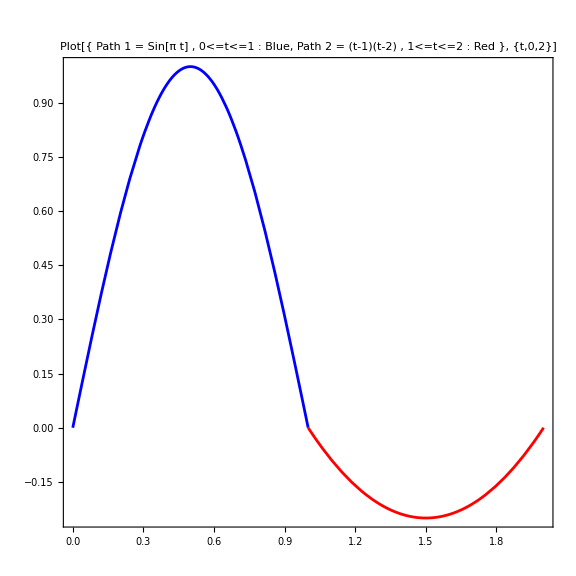

```mathematica
Plot[{If[0<=t<=1,Sin[π t]],If[1<=t<=2,(t-1)(t-2)]},{t,0,2},Frame->True,
PlotRange->All,(*PlotLegends->"Expressions",*)AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π t] , 0<=t<=1 : Blue,
Path 2 = (t-1)(t-2) , 1<=t<=2 : Red
}, {t,0,2}]"],16]]
```

```mathematica
Timing[spath01=signat[{{t,Sin[π t]}},{0,1},5][[1]]]
```

{67.9748,{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}}}

```mathematica
Timing[spath12=signat[{{t,(t-1)(t-2)}},{1,2},5][[1]]]
```

{73.3911,{{1},{1,0},{{1/2,1/6},{-1/6,0}},{{{1/6,1/12},{0,1/60}},{{-1/12,-1/30},{1/60,0}}},{{{{1/24,1/40},{1/120,1/120}},{{-1/120,-1/360},{1/360,1/840}}},{{{-1/40,-1/72},{-1/360,-1/280}},{{1/120,1/280},{-1/840,0}}}},{{{{{1/120,1/180},{1/360,1/420}},{{0,1/2520},{1/1260,1/1680}}},{{{-1/360,-1/630},{-1/2520,-1/2520}},{{1/1260,1/2520},{0,1/15120}}}},{{{{-1/180,-1/280},{-1/630,-1/720}},{{1/2520,0},{-1/2520,-1/3780}}},{{{1/420,1/720},{1/2520,1/2520}},{{-1/1680,-1/3780},{1/15120,0}}}}}}}

```mathematica
Timing[spath02=signat[{{t,Piecewise[{{Sin[π t], 0<=t<=1}, {(t-1)(t-2), 1<=t<=2}}]}},{0,2},5][[1]]]
```

{207.914,{{1},{2,0},{{2,(-12+π)/(6 π)},{(12-π)/(6 π),0}},{{{4/3,(-4+π)/(4 π)},{(-12-π)/(6 π),4/15}},{{(36-π)/(12 π),-8/15},{4/15,0}}},{{{{2/3,(240-60 π^2+23 π^3)/(120 π^3)},{(-240-20 π^2-3 π^3)/(40 π^3),3/20}},{{(720-180 π^2-11 π^3)/(120 π^3),(720-120 π-103 π^2)/(360 π^2)},{(-720+120 π+187 π^2)/(360 π^2),(-560+3 π)/(2520 π)}}},{{{(-80+100 π^2-π^3)/(40 π^3),(-144+24 π-π^2)/(72 π^2)},{(720-120 π-271 π^2)/(360 π^2),(560-3 π)/(840 π)}},{{23/60,(-560+3 π)/(840 π)},{(560-3 π)/(2520 π),0}}}},{{{{{4/15,(30-5 π^2+3 π^3)/(30 π^3)},{(-20-π)/(60 π),(-35+34 π^2)/(560 π^2)}},{{(-120-π^3)/(20 π^3),(735-140 π-86 π^2)/(840 π^2)},{(-231+56 π+74 π^2)/(336 π^2),(-560+9 π)/(5040 π)}}},{{{(288-36 π^2-π^3)/(36 π^3),(-210-140 π-13 π^2)/(840 π^2)},{(3465-424 π^2)/(1260 π^2),(63-5 π)/(1260 π)}},{{(-13545+840 π+2356 π^2)/(5040 π^2),(-42+115 π)/(2520 π)},{(-161-27 π)/(630 π),949/60480}}}},{{{{(-540+270 π^2-π^3)/(180 π^3),(-420+280 π-3 π^2)/(840 π^2)},{(-2835-210 π-2 π^2)/(1260 π^2),(204-π)/(720 π)}},{{(7245-420 π-1469 π^2)/(2520 π^2),(-4-5 π)/(60 π)},{(1974+209 π)/(2520 π),-949/15120}}},{{{(-105+494 π^2)/(1680 π^2),(-180+31 π)/(720 π)},{(-945-52 π)/(1260 π),949/10080}},{{(560-π)/(1680 π),-949/15120},{949/60480,0}}}}}}}

```mathematica
sigtake[spath01,{1,1,2}]
```

-1/π

```mathematica
sigtake[spath01,{}]
```

1

```mathematica
FullSimplify[{chen2[spath01,spath12,{1,1,2}],sigtake[spath02,{1,1,2}]}]
```

{1/4-1/π,1/4-1/π}

```mathematica
Expand[{chen2[spath01,spath12,{2,1,1,2}],sigtake[spath02,{2,1,1,2}]}]
```

{-1/72-2/π^2+1/(3 π),-1/72-2/π^2+1/(3 π)}

## Solving the sparse linear systems

### Functions

```mathematica
netgroebner[pols_,vars_,method_:"Buchberger"]:=Module[{basis,basisv},
basis=GroebnerBasis[pols,vars,Method->method];
basisv=Map[(Length[Intersection[vars,Variables[#]]]>0)&,basis];
Pick[basis,basisv]];
```

```mathematica
pickvars[pol_,level_]:=Module[{polvars,mask},
polvars=Variables[pol];
mask=Map[(Length[inds[#]]==level)&,polvars];
Pick[polvars,mask]];
```

```mathematica
graphgroebner[vars_,level_,grbasis_]:=Module[{groups,pairs},
groups=Select[Map[pickvars[#,level]&,grbasis],(Length[#]>1)&];
pairs=Union[Flatten[Map[Subsets[#,{2}]&,groups],1]];
Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name",GraphLayout->"RadialEmbedding",ImageSize->Large]];
```

```mathematica
graphgroebner2[vars_,level_,grbasis_]:=Module[{pairs},
pairs=Select[Map[pickvars[#,level]&,grbasis],(Length[#]==2)&];
Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name",GraphLayout->"RadialEmbedding",ImageSize->Large]];
```

```mathematica
adjgroebner[vars_,level_,grbasis_]:=Module[{groups,pairs},
groups=Select[Map[pickvars[#,level]&,grbasis],(Length[#]>1)&];
pairs=Union[Flatten[Map[Subsets[#,{2}]&,groups],1]];
AdjacencyMatrix[Graph[vars,
Map[Apply[UndirectedEdge,#]&,pairs],
VertexLabels->"Name"]]];
```

### d=2

#### Level 1

```mathematica
vars1=Flatten[Table[sind[{i}],{i,1,2}]]
```

{s_1,s_2}

```mathematica
fund1=vars1
```

{s_1,s_2}

#### Level 2

```mathematica
vars2=Flatten[Table[sind[{i,j}],{i,1,2},{j,1,2}]]
```

{s_(1,1),s_(1,2),s_(2,1),s_(2,2)}

```mathematica
eqs2=shuffles[vars1,vars1]
```

{2 s_(1,1)==s_1^2,s_(1,2)+s_(2,1)==s_1 s_2,s_(1,2)+s_(2,1)==s_1 s_2,2 s_(2,2)==s_2^2}

```mathematica
Transpose[{eqs2}]
```

{{2 s_(1,1)==s_1^2},{s_(1,2)+s_(2,1)==s_1 s_2},{s_(1,2)+s_(2,1)==s_1 s_2},{2 s_(2,2)==s_2^2}}

```mathematica
TableForm[netgroebner[shufflespol[vars1,vars1],vars2]]
```

-s_2^2+2 s_(2,2)
-s_1 s_2+s_(1,2)+s_(2,1)
-s_1^2+2 s_(1,1)

```mathematica
sols2=First[Solve[eqs2,vars2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2}

```mathematica
Transpose[{sols2}]
```

{{s_(1,1)→s_1^2/2},{s_(2,1)→s_1 s_2-s_(1,2)},{s_(2,2)→s_2^2/2}}

```mathematica
fund2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols2]]]
```

{s_1,s_2,s_(1,2)}

#### Level 3

```mathematica
vars3=Flatten[Table[sind[{i,j,k}],{i,1,2},{j,1,2},{k,1,2}]]
```

{s_(1,1,1),s_(1,1,2),s_(1,2,1),s_(1,2,2),s_(2,1,1),s_(2,1,2),s_(2,2,1),s_(2,2,2)}

```mathematica
eqs3=shuffles[vars1,vars2]
```

{3 s_(1,1,1)==s_1 s_(1,1),2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2),s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1),s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2),s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1),2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2),s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1),3 s_(2,2,2)==s_2 s_(2,2)}

```mathematica
Transpose[{eqs3}]
```

{{3 s_(1,1,1)==s_1 s_(1,1)},{2 s_(1,1,2)+s_(1,2,1)==s_1 s_(1,2)},{s_(1,2,1)+2 s_(2,1,1)==s_1 s_(2,1)},{s_(1,2,2)+s_(2,1,2)+s_(2,2,1)==s_1 s_(2,2)},{s_(1,1,2)+s_(1,2,1)+s_(2,1,1)==s_2 s_(1,1)},{2 s_(1,2,2)+s_(2,1,2)==s_2 s_(1,2)},{s_(2,1,2)+2 s_(2,2,1)==s_2 s_(2,1)},{3 s_(2,2,2)==s_2 s_(2,2)}}

```mathematica
Length[eqs3]
```

8

```mathematica
Timing[netgroebner[shufflespol[vars1,vars2],vars3,"GroebnerWalk"]]
```

{0.086945,{-s_2 s_(2,2)+3 s_(2,2,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1),-s_1 s_(1,1)+3 s_(1,1,1)}}

```mathematica
Timing[ngb3=netgroebner[shufflespol[vars1,vars2],vars3,"Buchberger"]]
```

{0.005362,{-s_2 s_(2,2)+3 s_(2,2,2),-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1),-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1),-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1),-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1),-s_1 s_(1,1)+3 s_(1,1,1)}}

```mathematica
TableForm[ngb3]
```

-s_2 s_(2,2)+3 s_(2,2,2)
-s_2 s_(2,1)+s_(2,1,2)+2 s_(2,2,1)
-s_2 s_(1,2)+s_2 s_(2,1)+2 s_(1,2,2)-2 s_(2,2,1)
-s_1 s_(2,1)+s_(1,2,1)+2 s_(2,1,1)
-s_2 s_(1,1)+s_1 s_(2,1)+s_(1,1,2)-s_(2,1,1)
-s_1 s_(1,1)+3 s_(1,1,1)

```mathematica
Map[pickvars[#,3]&,ngb3]
```

{{s_(2,2,2)},{s_(2,1,2),s_(2,2,1)},{s_(1,2,2),s_(2,2,1)},{s_(1,2,1),s_(2,1,1)},{s_(1,1,2),s_(2,1,1)},{s_(1,1,1)}}

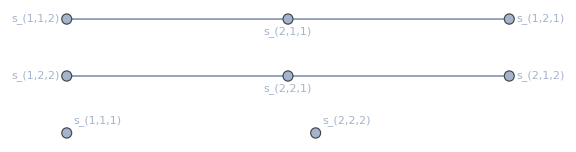

```mathematica
graphgroebner[vars3,3,ngb3]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars3,3,ngb3]]]
```

{3,3,1,1}

```mathematica
shp[{1,1},{2}]
```

{{1,1,2},{1,2,1},{2,1,1}}

```mathematica
shp[{1},{2,2}]
```

{{1,2,2},{2,1,2},{2,2,1}}

```mathematica
sols3new=First[Solve[eqs3/.sols2,vars3]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1,1)→s_1^3/6,s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2),s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2),s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2),s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2),s_(2,2,2)→s_2^3/6}

```mathematica
Transpose[{sols3new}]
```

{{s_(1,1,1)→s_1^3/6},{s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2)},{s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2)},{s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2)},{s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2)},{s_(2,2,2)→s_2^3/6}}

```mathematica
sols3=Join[sols2,sols3new];
```

```mathematica
fund3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2)}

#### Level 4

```mathematica
vars4=Flatten[Table[sind[{i,j,k,l}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2}]];
```

```mathematica
eqs4s13=shuffles[vars1,vars3];
```

```mathematica
sols4news13=First[Solve[eqs4s13/.sols3,vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4news13]
```

12

```mathematica
eqs4s22=shuffles[vars2,vars2];
```

```mathematica
Length[Join[eqs4s13,eqs4s22]]
```

32

```mathematica
Timing[ngb4=netgroebner[Join[shufflespol[vars1,vars3],shufflespol[vars2,vars2]],vars4]]
```

{0.036374,{-s_(2,2)^2+6 s_(2,2,2,2),-s_2 s_(2,2,1)+s_(2,2,1,2)+3 s_(2,2,2,1),-s_(2,1) s_(2,2)+2 s_2 s_(2,2,1)+s_(2,1,2,2)-3 s_(2,2,2,1),-s_(2,1)^2+2 s_(2,1,2,1)+4 s_(2,2,1,1),s_(2,1)^2-2 s_2 s_(2,1,1)+2 s_(2,1,1,2),-s_(1,2) s_(2,2)+2 s_(2,1) s_(2,2)-3 s_2 s_(2,2,1)+3 s_(1,2,2,2)+3 s_(2,2,2,1),s_(2,1)^2-2 s_1 s_(2,2,1)+2 s_(1,2,2,1),-2 s_(1,2) s_(2,1)-3 s_(2,1)^2+4 s_2 s_(2,1,1)+4 s_1 s_(2,2,1)+2 s_(1,2,1,2)-4 s_(2,2,1,1),-s_1 s_(2,1,1)+s_(1,2,1,1)+3 s_(2,1,1,1),-s_(1,2)^2+2 s_(1,2) s_(2,1)+3 s_(2,1)^2-4 s_2 s_(2,1,1)-4 s_1 s_(2,2,1)+4 s_(1,1,2,2)+4 s_(2,2,1,1),-s_(1,1) s_(2,1)+2 s_1 s_(2,1,1)+s_(1,1,2,1)-3 s_(2,1,1,1),-s_(1,1) s_(1,2)+2 s_(1,1) s_(2,1)-3 s_1 s_(2,1,1)+3 s_(1,1,1,2)+3 s_(2,1,1,1),-s_(1,1)^2+6 s_(1,1,1,1)}}

```mathematica
TableForm[ngb4]
```

-s_(2,2)^2+6 s_(2,2,2,2)
-s_2 s_(2,2,1)+s_(2,2,1,2)+3 s_(2,2,2,1)
-s_(2,1) s_(2,2)+2 s_2 s_(2,2,1)+s_(2,1,2,2)-3 s_(2,2,2,1)
-s_(2,1)^2+2 s_(2,1,2,1)+4 s_(2,2,1,1)
s_(2,1)^2-2 s_2 s_(2,1,1)+2 s_(2,1,1,2)
-s_(1,2) s_(2,2)+2 s_(2,1) s_(2,2)-3 s_2 s_(2,2,1)+3 s_(1,2,2,2)+3 s_(2,2,2,1)
s_(2,1)^2-2 s_1 s_(2,2,1)+2 s_(1,2,2,1)
-2 s_(1,2) s_(2,1)-3 s_(2,1)^2+4 s_2 s_(2,1,1)+4 s_1 s_(2,2,1)+2 s_(1,2,1,2)-4 s_(2,2,1,1)
-s_1 s_(2,1,1)+s_(1,2,1,1)+3 s_(2,1,1,1)
-s_(1,2)^2+2 s_(1,2) s_(2,1)+3 s_(2,1)^2-4 s_2 s_(2,1,1)-4 s_1 s_(2,2,1)+4 s_(1,1,2,2)+4 s_(2,2,1,1)
-s_(1,1) s_(2,1)+2 s_1 s_(2,1,1)+s_(1,1,2,1)-3 s_(2,1,1,1)
-s_(1,1) s_(1,2)+2 s_(1,1) s_(2,1)-3 s_1 s_(2,1,1)+3 s_(1,1,1,2)+3 s_(2,1,1,1)
-s_(1,1)^2+6 s_(1,1,1,1)

```mathematica
Length[ngb4]
```

13

```mathematica
Map[pickvars[#,4]&,ngb4]
```

{{s_(2,2,2,2)},{s_(2,2,1,2),s_(2,2,2,1)},{s_(2,1,2,2),s_(2,2,2,1)},{s_(2,1,2,1),s_(2,2,1,1)},{s_(2,1,1,2)},{s_(1,2,2,2),s_(2,2,2,1)},{s_(1,2,2,1)},{s_(1,2,1,2),s_(2,2,1,1)},{s_(1,2,1,1),s_(2,1,1,1)},{s_(1,1,2,2),s_(2,2,1,1)},{s_(1,1,2,1),s_(2,1,1,1)},{s_(1,1,1,2),s_(2,1,1,1)},{s_(1,1,1,1)}}

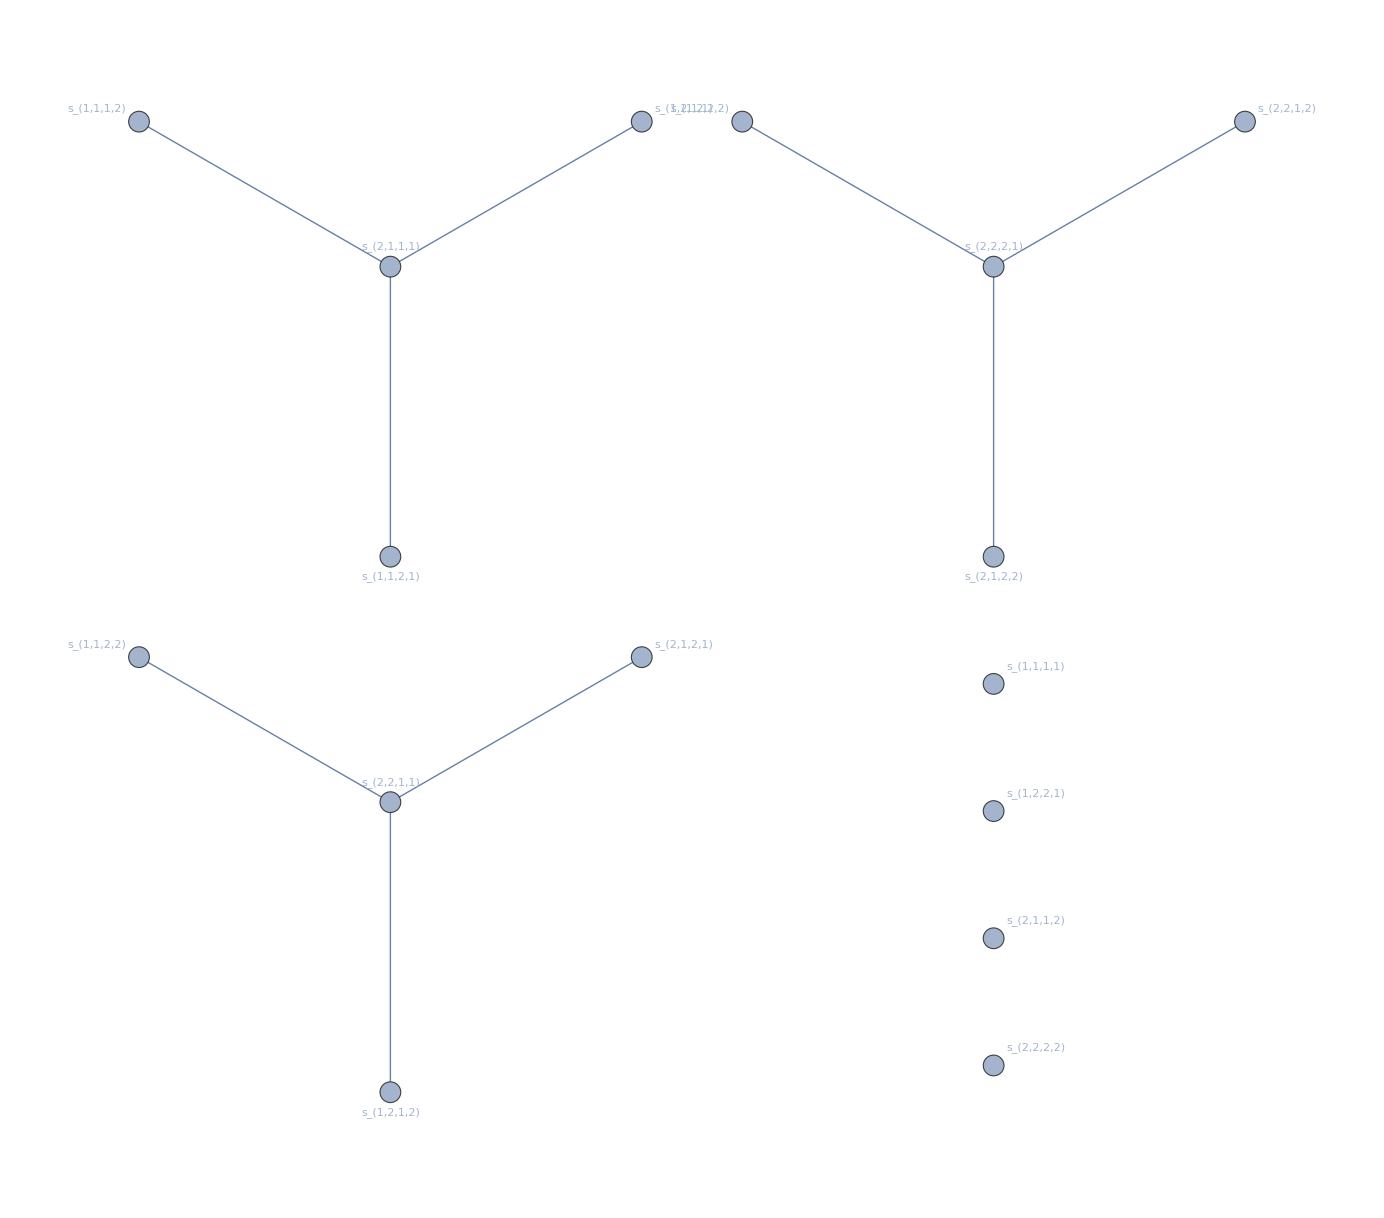

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graphgroebner[vars4,4,ngb4]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars4,4,ngb4]]]
```

{4,4,4,1,1,1,1}

```mathematica
shp[{1,1,1},{2}]
```

{{1,1,1,2},{1,1,2,1},{1,2,1,1},{2,1,1,1}}

```mathematica
shp[{1,1},{2,2}]
```

{{1,1,2,2},{1,2,1,2},{1,2,2,1},{2,1,1,2},{2,1,2,1},{2,2,1,1}}

```mathematica
shp[{1},{2,2,2}]
```

{{1,2,2,2},{2,1,2,2},{2,2,1,2},{2,2,2,1}}

```mathematica
sols4news22=First[Solve[eqs4s22/.Join[sols3,sols4news13],vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4news22]
```

1

```mathematica
Length[Join[sols4news13/.sols4news22,sols4news22]]
```

13

```mathematica
sols4=Join[sols3,sols4news13/.sols4news22,sols4news22];
```

```mathematica
fund4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols4]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2)}

#### Level 5

```mathematica
vars5=Flatten[Table[sind[{i,j,k,l,m}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2}]];
```

```mathematica
eqs5s14=shuffles[vars1,vars4];
```

```mathematica
Timing[sols5news14=First[Solve[eqs5s14/.sols4,vars5]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.021963,Null}

```mathematica
Length[sols5news14]
```

24

```mathematica
eqs5s23=shuffles[vars2,vars3];
```

```mathematica
Length[Join[eqs5s14,eqs5s23]]
```

64

```mathematica
Timing[ngb5=netgroebner[Join[shufflespol[vars1,vars4],shufflespol[vars2,vars3]],vars5]]
```

{8.22984,{-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2),-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1),-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1),-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1),2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1),-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1),-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1),-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1),-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1),s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1),-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1),s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1),s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1),-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1),4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1),-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1),s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1),-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1),-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1),s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1),-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1),-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1),-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1),-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1),-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1),-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)}}

```mathematica
TableForm[ngb5]
```

-s_(2,2) s_(2,2,2)+10 s_(2,2,2,2,2)
-s_2 s_(2,2,2,1)+s_(2,2,2,1,2)+4 s_(2,2,2,2,1)
-s_(2,2) s_(2,2,1)+3 s_2 s_(2,2,2,1)+s_(2,2,1,2,2)-6 s_(2,2,2,2,1)
-s_2 s_(2,2,1,1)+s_(2,2,1,1,2)+s_(2,2,1,2,1)+3 s_(2,2,2,1,1)
2 s_(2,2) s_(2,2,1)-s_(2,1) s_(2,2,2)-3 s_2 s_(2,2,2,1)+s_(2,1,2,2,2)+4 s_(2,2,2,2,1)
-s_(2,1) s_(2,2,1)+s_(2,1,2,2,1)+3 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,2)+2 s_(2,1) s_(2,2,1)+4 s_2 s_(2,2,1,1)+2 s_(2,1,2,1,2)-8 s_(2,2,1,2,1)-24 s_(2,2,2,1,1)
-2 s_(2,2) s_(2,1,1)+s_(2,1) s_(2,1,2)+2 s_(2,1,1,2,2)+2 s_(2,2,1,2,1)+6 s_(2,2,2,1,1)
-s_(2,1) s_(2,1,1)+s_(2,1,1,2,1)+3 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
s_(2,1) s_(2,1,1)-s_2 s_(2,1,1,1)+s_(2,1,1,1,2)-2 s_(2,1,2,1,1)-4 s_(2,2,1,1,1)
-4 s_(2,2) s_(2,2,1)-s_(1,2) s_(2,2,2)+3 s_(2,1) s_(2,2,2)+4 s_2 s_(2,2,2,1)+4 s_(1,2,2,2,2)-4 s_(2,2,2,2,1)
s_(2,1) s_(2,2,1)-s_1 s_(2,2,2,1)+s_(1,2,2,2,1)-2 s_(2,2,1,2,1)-4 s_(2,2,2,1,1)
s_(2,1) s_(2,1,2)-2 s_(1,2) s_(2,2,1)-4 s_(2,1) s_(2,2,1)+6 s_1 s_(2,2,2,1)+2 s_(1,2,2,1,2)+6 s_(2,2,1,2,1)+12 s_(2,2,2,1,1)
-s_1 s_(2,2,1,1)+s_(1,2,2,1,1)+s_(2,1,2,1,1)+3 s_(2,2,1,1,1)
4 s_(2,2) s_(2,1,1)-s_(1,2) s_(2,1,2)-2 s_(2,1) s_(2,1,2)+2 s_(1,2) s_(2,2,1)+2 s_(2,1) s_(2,2,1)-4 s_2 s_(2,2,1,1)-6 s_1 s_(2,2,2,1)+2 s_(1,2,1,2,2)-2 s_(2,2,1,2,1)
-s_(2,1) s_(1,2,1)+2 s_(2,1) s_(2,1,1)+4 s_1 s_(2,2,1,1)+2 s_(1,2,1,2,1)-8 s_(2,1,2,1,1)-24 s_(2,2,1,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,2) s_(2,1,1)-4 s_(2,1) s_(2,1,1)+6 s_2 s_(2,1,1,1)+2 s_(1,2,1,1,2)+6 s_(2,1,2,1,1)+12 s_(2,2,1,1,1)
-s_1 s_(2,1,1,1)+s_(1,2,1,1,1)+4 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,2,2)-12 s_(2,2) s_(2,1,1)+3 s_(1,2) s_(2,1,2)+5 s_(2,1) s_(2,1,2)-4 s_(1,2) s_(2,2,1)-2 s_(2,1) s_(2,2,1)+12 s_2 s_(2,2,1,1)+12 s_1 s_(2,2,2,1)+12 s_(1,1,2,2,2)-12 s_(2,2,2,1,1)
s_(2,1) s_(1,2,1)-2 s_(1,1) s_(2,2,1)+2 s_(1,1,2,2,1)+2 s_(2,1,2,1,1)+6 s_(2,2,1,1,1)
-s_(1,2) s_(1,2,1)-2 s_(2,1) s_(1,2,1)+2 s_(1,2) s_(2,1,1)+2 s_(2,1) s_(2,1,1)+4 s_(1,1) s_(2,2,1)-6 s_2 s_(2,1,1,1)-4 s_1 s_(2,2,1,1)+2 s_(1,1,2,1,2)-2 s_(2,1,2,1,1)
-s_(1,1) s_(2,1,1)+3 s_1 s_(2,1,1,1)+s_(1,1,2,1,1)-6 s_(2,1,1,1,1)
-2 s_(1,2) s_(1,1,2)+3 s_(1,2) s_(1,2,1)+5 s_(2,1) s_(1,2,1)-4 s_(1,2) s_(2,1,1)-2 s_(2,1) s_(2,1,1)-12 s_(1,1) s_(2,2,1)+12 s_2 s_(2,1,1,1)+12 s_1 s_(2,2,1,1)+12 s_(1,1,1,2,2)-12 s_(2,2,1,1,1)
-s_(2,1) s_(1,1,1)+2 s_(1,1) s_(2,1,1)-3 s_1 s_(2,1,1,1)+s_(1,1,1,2,1)+4 s_(2,1,1,1,1)
-s_(1,2) s_(1,1,1)+3 s_(2,1) s_(1,1,1)-4 s_(1,1) s_(2,1,1)+4 s_1 s_(2,1,1,1)+4 s_(1,1,1,1,2)-4 s_(2,1,1,1,1)
-s_(1,1) s_(1,1,1)+10 s_(1,1,1,1,1)

```mathematica
Map[pickvars[#,5]&,ngb5]
```

{{s_(2,2,2,2,2)},{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,1,1)}}

```mathematica
groups5=Select[Map[pickvars[#,5]&,ngb5],(Length[#]>1)&]
```

{{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)}}

```mathematica
Select[Map[pickvars[#,5]&,ngb5],(Length[#]==2)&]
```

{{s_(2,2,2,1,2),s_(2,2,2,2,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,1,2),s_(2,1,1,1,1)}}

```mathematica
Select[Map[pickvars[#,5]&,ngb5],(Length[#]==3)&]
```

{{s_(2,2,1,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1),s_(2,2,1,1,1)}}

```mathematica
pairs5=Union[Flatten[Map[Subsets[#,{2}]&,groups5],1]]
```

{{s_(1,1,1,1,2),s_(2,1,1,1,1)},{s_(1,1,1,2,1),s_(2,1,1,1,1)},{s_(1,1,1,2,2),s_(2,2,1,1,1)},{s_(1,1,2,1,1),s_(2,1,1,1,1)},{s_(1,1,2,1,2),s_(2,1,2,1,1)},{s_(1,1,2,2,1),s_(2,1,2,1,1)},{s_(1,1,2,2,1),s_(2,2,1,1,1)},{s_(1,1,2,2,2),s_(2,2,2,1,1)},{s_(1,2,1,1,1),s_(2,1,1,1,1)},{s_(1,2,1,1,2),s_(2,1,2,1,1)},{s_(1,2,1,1,2),s_(2,2,1,1,1)},{s_(1,2,1,2,1),s_(2,1,2,1,1)},{s_(1,2,1,2,1),s_(2,2,1,1,1)},{s_(1,2,1,2,2),s_(2,2,1,2,1)},{s_(1,2,2,1,1),s_(2,1,2,1,1)},{s_(1,2,2,1,1),s_(2,2,1,1,1)},{s_(1,2,2,1,2),s_(2,2,1,2,1)},{s_(1,2,2,1,2),s_(2,2,2,1,1)},{s_(1,2,2,2,1),s_(2,2,1,2,1)},{s_(1,2,2,2,1),s_(2,2,2,1,1)},{s_(1,2,2,2,2),s_(2,2,2,2,1)},{s_(2,1,1,1,2),s_(2,1,2,1,1)},{s_(2,1,1,1,2),s_(2,2,1,1,1)},{s_(2,1,1,2,1),s_(2,1,2,1,1)},{s_(2,1,1,2,1),s_(2,2,1,1,1)},{s_(2,1,1,2,2),s_(2,2,1,2,1)},{s_(2,1,1,2,2),s_(2,2,2,1,1)},{s_(2,1,2,1,1),s_(2,2,1,1,1)},{s_(2,1,2,1,2),s_(2,2,1,2,1)},{s_(2,1,2,1,2),s_(2,2,2,1,1)},{s_(2,1,2,2,1),s_(2,2,1,2,1)},{s_(2,1,2,2,1),s_(2,2,2,1,1)},{s_(2,1,2,2,2),s_(2,2,2,2,1)},{s_(2,2,1,1,2),s_(2,2,1,2,1)},{s_(2,2,1,1,2),s_(2,2,2,1,1)},{s_(2,2,1,2,1),s_(2,2,2,1,1)},{s_(2,2,1,2,2),s_(2,2,2,2,1)},{s_(2,2,2,1,2),s_(2,2,2,2,1)}}

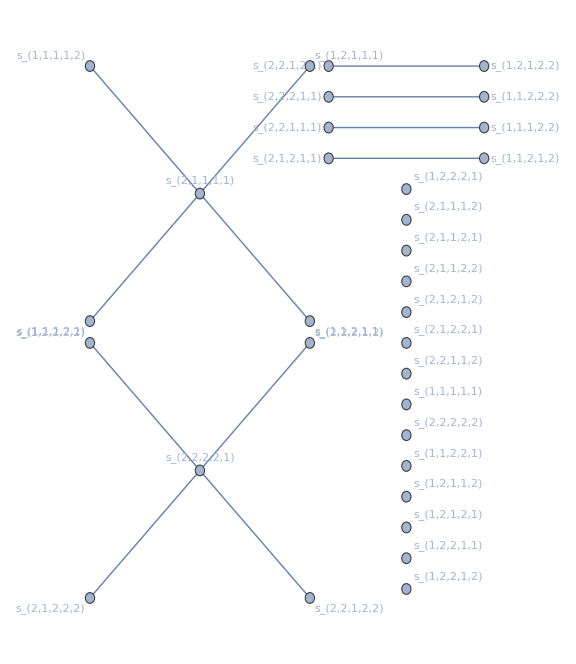

```mathematica
graphgroebner2[vars5,5,ngb5]
```

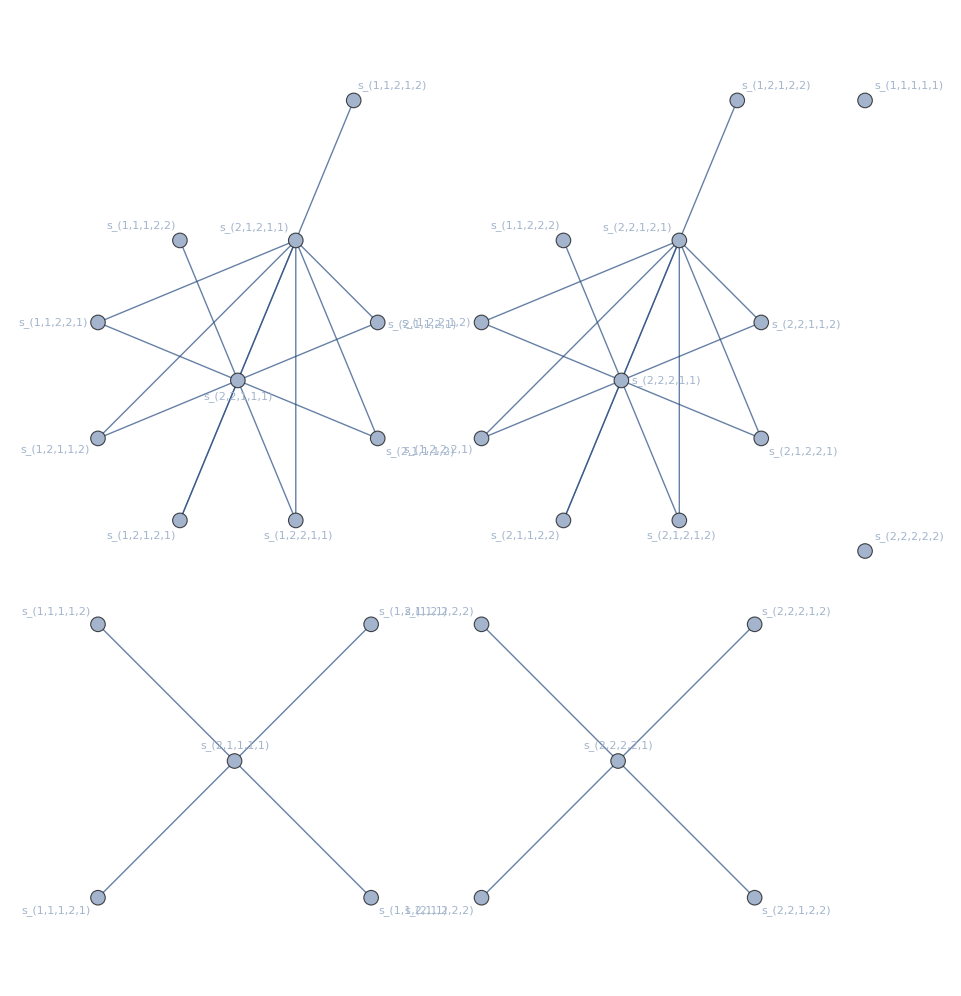

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graphgroebner[vars5,5,ngb5]
```

```mathematica
ArrayPlot[adjgroebner[vars5,5,ngb5],Mesh->True]
```

-Graphics-

```mathematica
Transpose[{vars5,Map[Total,adjgroebner[vars5,5,ngb5]]}]
```

{{s_(1,1,1,1,1),0},{s_(1,1,1,1,2),1},{s_(1,1,1,2,1),1},{s_(1,1,1,2,2),1},{s_(1,1,2,1,1),1},{s_(1,1,2,1,2),1},{s_(1,1,2,2,1),2},{s_(1,1,2,2,2),1},{s_(1,2,1,1,1),1},{s_(1,2,1,1,2),2},{s_(1,2,1,2,1),2},{s_(1,2,1,2,2),1},{s_(1,2,2,1,1),2},{s_(1,2,2,1,2),2},{s_(1,2,2,2,1),2},{s_(1,2,2,2,2),1},{s_(2,1,1,1,1),4},{s_(2,1,1,1,2),2},{s_(2,1,1,2,1),2},{s_(2,1,1,2,2),2},{s_(2,1,2,1,1),8},{s_(2,1,2,1,2),2},{s_(2,1,2,2,1),2},{s_(2,1,2,2,2),1},{s_(2,2,1,1,1),8},{s_(2,2,1,1,2),2},{s_(2,2,1,2,1),8},{s_(2,2,1,2,2),1},{s_(2,2,2,1,1),8},{s_(2,2,2,1,2),1},{s_(2,2,2,2,1),4},{s_(2,2,2,2,2),0}}

```mathematica
Transpose[{vars5,VertexDegree[graphgroebner[vars5,5,ngb5]]}]
```

{{s_(1,1,1,1,1),0},{s_(1,1,1,1,2),1},{s_(1,1,1,2,1),1},{s_(1,1,1,2,2),1},{s_(1,1,2,1,1),1},{s_(1,1,2,1,2),1},{s_(1,1,2,2,1),2},{s_(1,1,2,2,2),1},{s_(1,2,1,1,1),1},{s_(1,2,1,1,2),2},{s_(1,2,1,2,1),2},{s_(1,2,1,2,2),1},{s_(1,2,2,1,1),2},{s_(1,2,2,1,2),2},{s_(1,2,2,2,1),2},{s_(1,2,2,2,2),1},{s_(2,1,1,1,1),4},{s_(2,1,1,1,2),2},{s_(2,1,1,2,1),2},{s_(2,1,1,2,2),2},{s_(2,1,2,1,1),8},{s_(2,1,2,1,2),2},{s_(2,1,2,2,1),2},{s_(2,1,2,2,2),1},{s_(2,2,1,1,1),8},{s_(2,2,1,1,2),2},{s_(2,2,1,2,1),8},{s_(2,2,1,2,2),1},{s_(2,2,2,1,1),8},{s_(2,2,2,1,2),1},{s_(2,2,2,2,1),4},{s_(2,2,2,2,2),0}}

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]]]
```

{10,10,5,5,1,1}

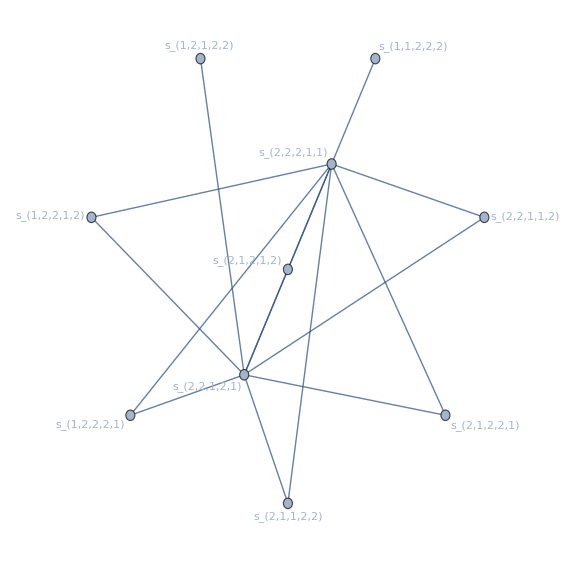

```mathematica
ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]][[1]]
```

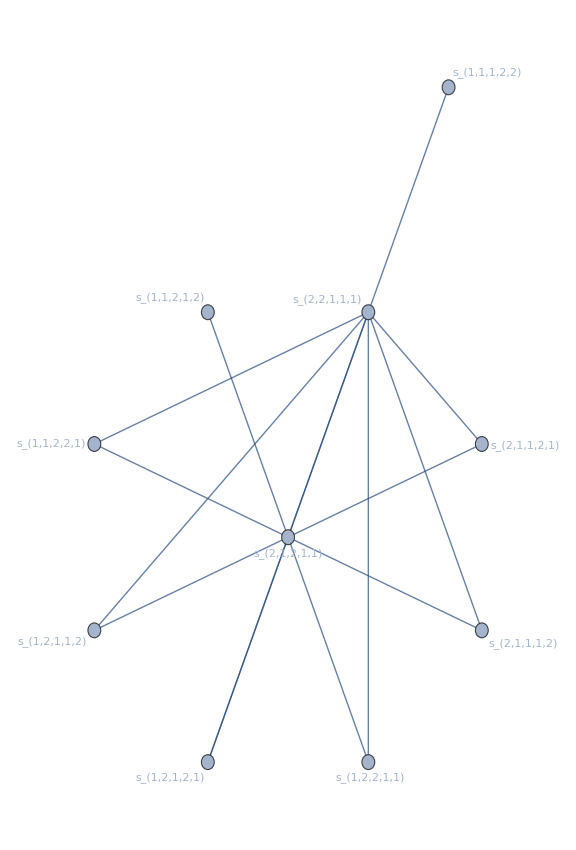

```mathematica
ConnectedGraphComponents[graphgroebner[vars5,5,ngb5]][[2]]
```

```mathematica
sols5news23=First[Solve[eqs5s23/.Join[sols4,sols5news14],vars5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols5news23]
```

2

```mathematica
sols5=Join[sols4,sols5news14/.sols5news23,sols5news23];
```

```mathematica
Length[Join[sols5news14/.sols5news23,sols5news23]]
```

26

```mathematica
fund5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols5]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2),s_(1,1,1,1,2),s_(1,1,1,2,2),s_(1,1,2,1,2),s_(1,1,2,2,2),s_(1,2,1,2,2),s_(1,2,2,2,2)}

#### Level 6

```mathematica
vars6=Flatten[Table[sind[{i,j,k,l,m,n}],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2}]];
```

```mathematica
eqs6s15=shuffles[vars1,vars5];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s15]]]],vars6]]],
ImageSize->Large]
```

-Graphics-

```mathematica
sols6news15=First[Solve[eqs6s15/.sols5,vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news15]
```

48

```mathematica
eqs6s24=shuffles[vars2,vars4];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s24]]]],vars6]]]]
```

-Graphics-

```mathematica
Timing[sols6news24=First[Solve[eqs6s24/.Join[sols5,sols6news15],vars6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.180234,Null}

```mathematica
Length[sols6news24]
```

4

```mathematica
eqs6s33=shuffles[vars3,vars3];
```

```mathematica
ArrayPlot[Last[Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs6s33]]]],vars6]]]]
```

-Graphics-

```mathematica
sols6news33=First[Solve[eqs6s33/.Join[sols5,sols6news15/.sols6news24,sols6news24],vars6]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols6news33]
```

3

```mathematica
{{Length[shufflespol[vars1,vars5]],Length[DeleteDuplicates[shufflespol[vars1,vars5]]]},
{Length[shufflespol[vars2,vars4]],Length[DeleteDuplicates[shufflespol[vars2,vars4]]]},
{Length[shufflespol[vars3,vars3]],Length[DeleteDuplicates[shufflespol[vars3,vars3]]]}}
```

{{64,64},{64,64},{64,36}}

```mathematica
Timing[ngb6s15=netgroebner[shufflespol[vars1,vars5],vars6];]
```

{9.46901,Null}

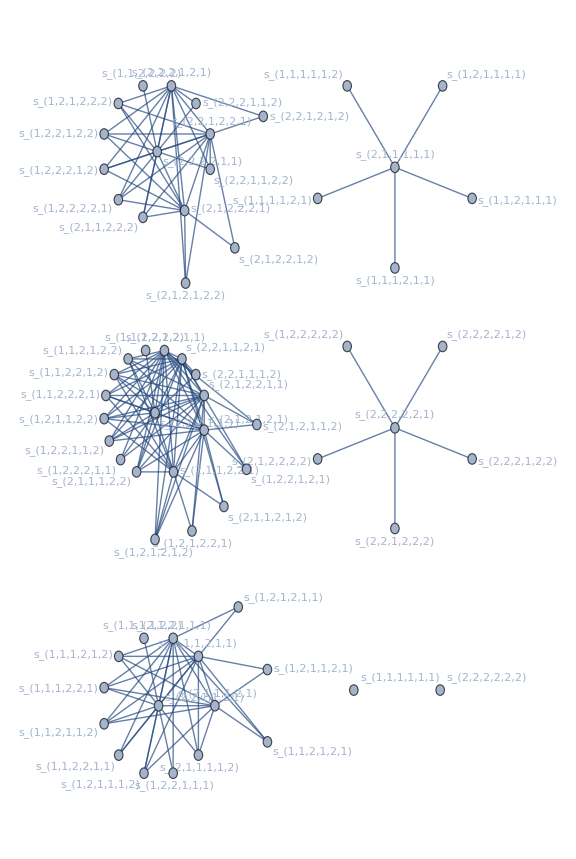

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
graphgroebner[vars6,6,ngb6s15]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s15]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6s24=netgroebner[shufflespol[vars2,vars4],vars6];]
```

{0.706315,Null}

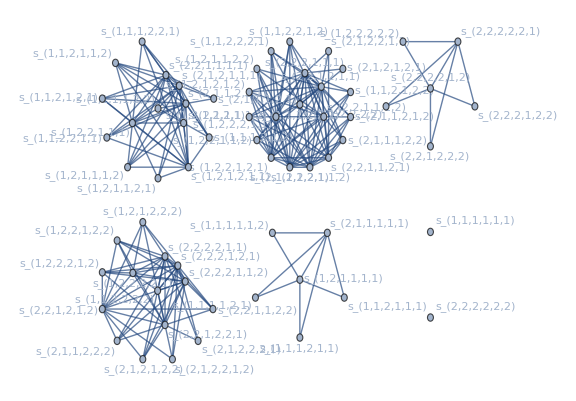

```mathematica
graphgroebner[vars6,6,ngb6s24]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s24]]]
```

{20,15,15,6,6,1,1}

```mathematica
Timing[ngb6s33=netgroebner[DeleteDuplicates[shufflespol[vars3,vars3]],vars6];]
```

{0.025654,Null}

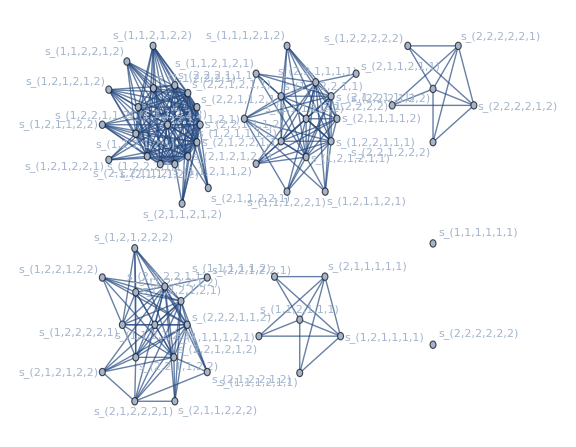

```mathematica
graphgroebner[vars6,6,ngb6s33]
```

```mathematica
Map[Length[VertexList[#]]&,ConnectedGraphComponents[graphgroebner[vars6,6,ngb6s33]]]
```

{20,15,15,6,6,1,1}

```mathematica
Length[Join[sols6news15/.sols6news24/.sols6news33,sols6news24/.sols6news33,sols6news33]]
```

55

```mathematica
sols6=Join[sols5,sols6news15/.sols6news24/.sols6news33,sols6news24/.sols6news33,sols6news33];
```

```mathematica
fund6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6]]]
```

{s_1,s_2,s_(1,2),s_(1,1,2),s_(1,2,2),s_(1,1,1,2),s_(1,1,2,2),s_(1,2,2,2),s_(1,1,1,1,2),s_(1,1,1,2,2),s_(1,1,2,1,2),s_(1,1,2,2,2),s_(1,2,1,2,2),s_(1,2,2,2,2),s_(1,1,1,1,1,2),s_(1,1,1,1,2,2),s_(1,1,1,2,1,2),s_(1,1,1,2,2,2),s_(1,1,2,1,2,2),s_(1,1,2,2,1,2),s_(1,1,2,2,2,2),s_(1,2,1,2,2,2),s_(1,2,2,2,2,2)}

```mathematica
Take[sols6,3]
```

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2}

```mathematica
Expand[Take[sols6,{4,9}]]
```

{s_(1,1,1)→s_1^3/6,s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2),s_(2,1,1)→1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2),s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2),s_(2,2,1)→1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2),s_(2,2,2)→s_2^3/6}

```mathematica
Expand[Take[sols6,{10,22}]]
```

{s_(1,1,1,1)→s_1^4/24,s_(1,1,2,1)→s_1 s_(1,1,2)-3 s_(1,1,1,2),s_(1,2,1,1)→1/2 s_1^2 s_(1,2)-2 s_1 s_(1,1,2)+3 s_(1,1,1,2),s_(1,2,2,1)→-1/2 s_(1,2)^2+s_1 s_(1,2,2),s_(2,1,1,1)→1/6 s_1^3 s_2-1/2 s_1^2 s_(1,2)+s_1 s_(1,1,2)-s_(1,1,1,2),s_(2,1,1,2)→-1/2 s_(1,2)^2+s_2 s_(1,1,2),s_(2,1,2,1)→s_1 s_2 s_(1,2)+(s_(1,2)^2)/2-2 s_2 s_(1,1,2)-2 s_1 s_(1,2,2)+2 s_(1,1,2,2),s_(2,1,2,2)→s_2 s_(1,2,2)-3 s_(1,2,2,2),s_(2,2,1,1)→1/4 s_1^2 s_2^2-s_1 s_2 s_(1,2)+s_2 s_(1,1,2)+s_1 s_(1,2,2)-s_(1,1,2,2),s_(2,2,1,2)→1/2 s_2^2 s_(1,2)-2 s_2 s_(1,2,2)+3 s_(1,2,2,2),s_(2,2,2,1)→1/6 s_1 s_2^3-1/2 s_2^2 s_(1,2)+s_2 s_(1,2,2)-s_(1,2,2,2),s_(2,2,2,2)→s_2^4/24,s_(1,2,1,2)→(s_(1,2)^2)/2-2 s_(1,1,2,2)}

```mathematica
TableForm[Transpose[{Expand[Take[sols6,{23,48}]]}]]
```

s_(1,1,1,1,1)→s_1^5/120
s_(1,1,1,2,1)→s_1 s_(1,1,1,2)-4 s_(1,1,1,1,2)
s_(1,1,2,1,1)→1/2 s_1^2 s_(1,1,2)-3 s_1 s_(1,1,1,2)+6 s_(1,1,1,1,2)
s_(1,1,2,2,1)→s_1 s_(1,1,2,2)-3 s_(1,1,1,2,2)-s_(1,1,2,1,2)
s_(1,2,1,1,1)→1/6 s_1^3 s_(1,2)-s_1^2 s_(1,1,2)+3 s_1 s_(1,1,1,2)-4 s_(1,1,1,1,2)
s_(1,2,1,2,1)→1/2 s_1 s_(1,2)^2-2 s_(1,2) s_(1,1,2)-2 s_1 s_(1,1,2,2)+12 s_(1,1,1,2,2)+4 s_(1,1,2,1,2)
s_(1,2,2,1,1)→-1/2 s_1 s_(1,2)^2+s_(1,2) s_(1,1,2)+1/2 s_1^2 s_(1,2,2)-3 s_(1,1,1,2,2)-s_(1,1,2,1,2)
s_(1,2,2,2,1)→-s_(1,2) s_(1,2,2)+s_1 s_(1,2,2,2)+4 s_(1,1,2,2,2)+2 s_(1,2,1,2,2)
s_(2,1,1,1,1)→1/24 s_1^4 s_2-1/6 s_1^3 s_(1,2)+1/2 s_1^2 s_(1,1,2)-s_1 s_(1,1,1,2)+s_(1,1,1,1,2)
s_(2,1,1,1,2)→-s_(1,2) s_(1,1,2)+s_2 s_(1,1,1,2)+4 s_(1,1,1,2,2)+2 s_(1,1,2,1,2)
s_(2,1,1,2,1)→-1/2 s_1 s_(1,2)^2+s_1 s_2 s_(1,1,2)+2 s_(1,2) s_(1,1,2)-3 s_2 s_(1,1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2)
s_(2,1,1,2,2)→s_2 s_(1,1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2)
s_(2,1,2,1,1)→1/2 s_1^2 s_2 s_(1,2)+1/2 s_1 s_(1,2)^2-2 s_1 s_2 s_(1,1,2)-s_(1,2) s_(1,1,2)-s_1^2 s_(1,2,2)+3 s_2 s_(1,1,1,2)+2 s_1 s_(1,1,2,2)+s_(1,1,2,1,2)
s_(2,1,2,1,2)→1/2 s_2 s_(1,2)^2-2 s_(1,2) s_(1,2,2)-2 s_2 s_(1,1,2,2)+12 s_(1,1,2,2,2)+4 s_(1,2,1,2,2)
s_(2,1,2,2,1)→-1/2 s_2 s_(1,2)^2+s_1 s_2 s_(1,2,2)+2 s_(1,2) s_(1,2,2)-3 s_1 s_(1,2,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2)
s_(2,1,2,2,2)→s_2 s_(1,2,2,2)-4 s_(1,2,2,2,2)
s_(2,2,1,1,1)→1/12 s_1^3 s_2^2-1/2 s_1^2 s_2 s_(1,2)+s_1 s_2 s_(1,1,2)+1/2 s_1^2 s_(1,2,2)-s_2 s_(1,1,1,2)-s_1 s_(1,1,2,2)+s_(1,1,1,2,2)
s_(2,2,1,1,2)→-1/2 s_2 s_(1,2)^2+1/2 s_2^2 s_(1,1,2)+s_(1,2) s_(1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2)
s_(2,2,1,2,1)→1/2 s_1 s_2^2 s_(1,2)+1/2 s_2 s_(1,2)^2-s_2^2 s_(1,1,2)-2 s_1 s_2 s_(1,2,2)-s_(1,2) s_(1,2,2)+2 s_2 s_(1,1,2,2)+3 s_1 s_(1,2,2,2)+s_(1,2,1,2,2)
s_(2,2,1,2,2)→1/2 s_2^2 s_(1,2,2)-3 s_2 s_(1,2,2,2)+6 s_(1,2,2,2,2)
s_(2,2,2,1,1)→1/12 s_1^2 s_2^3-1/2 s_1 s_2^2 s_(1,2)+1/2 s_2^2 s_(1,1,2)+s_1 s_2 s_(1,2,2)-s_2 s_(1,1,2,2)-s_1 s_(1,2,2,2)+s_(1,1,2,2,2)
s_(2,2,2,1,2)→1/6 s_2^3 s_(1,2)-s_2^2 s_(1,2,2)+3 s_2 s_(1,2,2,2)-4 s_(1,2,2,2,2)
s_(2,2,2,2,1)→1/24 s_1 s_2^4-1/6 s_2^3 s_(1,2)+1/2 s_2^2 s_(1,2,2)-s_2 s_(1,2,2,2)+s_(1,2,2,2,2)
s_(2,2,2,2,2)→s_2^5/120
s_(1,2,1,1,2)→s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2)
s_(1,2,2,1,2)→s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2)

```mathematica
Map[Count[Rest[Apply[List,First[#]]],1]&,Take[sols6,{23,48}]]
```

{5,4,4,3,4,3,3,2,4,3,3,2,3,2,2,1,3,2,2,1,2,1,1,0,3,2}

```mathematica
TableForm[Transpose[{Pick[Expand[Take[sols6,{23,48}]],Map[(Count[Rest[Apply[List,First[#]]],1]==2)&,Take[sols6,{23,48}]]]}]]
```

s_(1,2,2,2,1)→-s_(1,2) s_(1,2,2)+s_1 s_(1,2,2,2)+4 s_(1,1,2,2,2)+2 s_(1,2,1,2,2)
s_(2,1,1,2,2)→s_2 s_(1,1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2)
s_(2,1,2,1,2)→1/2 s_2 s_(1,2)^2-2 s_(1,2) s_(1,2,2)-2 s_2 s_(1,1,2,2)+12 s_(1,1,2,2,2)+4 s_(1,2,1,2,2)
s_(2,1,2,2,1)→-1/2 s_2 s_(1,2)^2+s_1 s_2 s_(1,2,2)+2 s_(1,2) s_(1,2,2)-3 s_1 s_(1,2,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2)
s_(2,2,1,1,2)→-1/2 s_2 s_(1,2)^2+1/2 s_2^2 s_(1,1,2)+s_(1,2) s_(1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2)
s_(2,2,1,2,1)→1/2 s_1 s_2^2 s_(1,2)+1/2 s_2 s_(1,2)^2-s_2^2 s_(1,1,2)-2 s_1 s_2 s_(1,2,2)-s_(1,2) s_(1,2,2)+2 s_2 s_(1,1,2,2)+3 s_1 s_(1,2,2,2)+s_(1,2,1,2,2)
s_(2,2,2,1,1)→1/12 s_1^2 s_2^3-1/2 s_1 s_2^2 s_(1,2)+1/2 s_2^2 s_(1,1,2)+s_1 s_2 s_(1,2,2)-s_2 s_(1,1,2,2)-s_1 s_(1,2,2,2)+s_(1,1,2,2,2)
s_(1,2,2,1,2)→s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2)

#### Q_6

```mathematica
Grid[Transpose[{sols6}],Frame->All]
```

s_(1,1)→s_1^2/2
s_(2,1)→s_1 s_2-s_(1,2)
s_(2,2)→s_2^2/2
s_(1,1,1)→s_1^3/6
s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2)
s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2)
s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2)
s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2)
s_(2,2,2)→s_2^3/6
s_(1,1,1,1)→s_1^4/24
s_(1,1,2,1)→s_1 s_(1,1,2)-3 s_(1,1,1,2)
s_(1,2,1,1)→1/2 (s_1^2 s_(1,2)-4 s_1 s_(1,1,2))+3 s_(1,1,1,2)
s_(1,2,2,1)→-1/2 s_(1,2)^2+s_1 s_(1,2,2)
s_(2,1,1,1)→1/6 (s_1^3 s_2-3 s_1^2 s_(1,2)+6 s_1 s_(1,1,2))-s_(1,1,1,2)
s_(2,1,1,2)→-1/2 s_(1,2)^2+s_2 s_(1,1,2)
s_(2,1,2,1)→s_1 s_2 s_(1,2)+(s_(1,2)^2)/2-2 s_2 s_(1,1,2)-2 s_1 s_(1,2,2)+2 s_(1,1,2,2)
s_(2,1,2,2)→s_2 s_(1,2,2)-3 s_(1,2,2,2)
s_(2,2,1,1)→1/4 (s_1^2 s_2^2-4 s_1 s_2 s_(1,2)+4 s_2 s_(1,1,2)+4 s_1 s_(1,2,2))-s_(1,1,2,2)
s_(2,2,1,2)→1/2 (s_2^2 s_(1,2)-4 s_2 s_(1,2,2))+3 s_(1,2,2,2)
s_(2,2,2,1)→1/6 (s_1 s_2^3-3 s_2^2 s_(1,2)+6 s_2 s_(1,2,2))-s_(1,2,2,2)
s_(2,2,2,2)→s_2^4/24
s_(1,2,1,2)→(s_(1,2)^2)/2-2 s_(1,1,2,2)
s_(1,1,1,1,1)→s_1^5/120
s_(1,1,1,2,1)→s_1 s_(1,1,1,2)-4 s_(1,1,1,1,2)
s_(1,1,2,1,1)→1/2 (s_1^2 s_(1,1,2)-6 s_1 s_(1,1,1,2))+6 s_(1,1,1,1,2)
s_(1,1,2,2,1)→s_1 s_(1,1,2,2)-3 s_(1,1,1,2,2)-s_(1,1,2,1,2)
s_(1,2,1,1,1)→1/6 (s_1^3 s_(1,2)-6 s_1^2 s_(1,1,2)+18 s_1 s_(1,1,1,2))-4 s_(1,1,1,1,2)
s_(1,2,1,2,1)→1/2 (s_1 s_(1,2)^2-4 s_1 s_(1,1,2,2))-2 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))-2 s_(1,1,2,1,2)
s_(1,2,2,1,1)→s_(1,2) s_(1,1,2)+1/2 (-s_1 s_(1,2)^2+s_1^2 s_(1,2,2))-3 s_(1,1,1,2,2)-s_(1,1,2,1,2)
s_(1,2,2,2,1)→-s_(1,2) s_(1,2,2)+s_1 s_(1,2,2,2)+4 s_(1,1,2,2,2)+2 s_(1,2,1,2,2)
s_(2,1,1,1,1)→1/24 (s_1^4 s_2-4 s_1^3 s_(1,2)+12 s_1^2 s_(1,1,2)-24 s_1 s_(1,1,1,2))+s_(1,1,1,1,2)
s_(2,1,1,1,2)→-s_(1,2) s_(1,1,2)+s_2 s_(1,1,1,2)+4 s_(1,1,1,2,2)+2 s_(1,1,2,1,2)
s_(2,1,1,2,1)→1/2 (-s_1 s_(1,2)^2+2 s_1 s_2 s_(1,1,2)-6 s_2 s_(1,1,1,2))+6 s_(1,1,1,2,2)+2 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))+3 s_(1,1,2,1,2)
s_(2,1,1,2,2)→s_2 s_(1,1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2)
s_(2,1,2,1,1)→-s_(1,2) s_(1,1,2)+1/2 (s_1^2 s_2 s_(1,2)+s_1 s_(1,2)^2-4 s_1 s_2 s_(1,1,2)-2 s_1^2 s_(1,2,2)+6 s_2 s_(1,1,1,2)+4 s_1 s_(1,1,2,2))+s_(1,1,2,1,2)
s_(2,1,2,1,2)→1/2 (s_2 s_(1,2)^2-4 s_2 s_(1,1,2,2))-2 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-2 s_(1,2,1,2,2)
s_(2,1,2,2,1)→1/2 (-s_2 s_(1,2)^2+2 s_1 s_2 s_(1,2,2)-6 s_1 s_(1,2,2,2))+6 s_(1,1,2,2,2)+2 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))+3 s_(1,2,1,2,2)
s_(2,1,2,2,2)→s_2 s_(1,2,2,2)-4 s_(1,2,2,2,2)
s_(2,2,1,1,1)→1/12 (s_1^3 s_2^2-6 s_1^2 s_2 s_(1,2)+12 s_1 s_2 s_(1,1,2)+6 s_1^2 s_(1,2,2)-12 s_2 s_(1,1,1,2)-12 s_1 s_(1,1,2,2))+s_(1,1,1,2,2)
s_(2,2,1,1,2)→1/2 (-s_2 s_(1,2)^2+s_2^2 s_(1,1,2))+s_(1,2) s_(1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2)
s_(2,2,1,2,1)→-s_(1,2) s_(1,2,2)+1/2 (s_1 s_2^2 s_(1,2)+s_2 s_(1,2)^2-2 s_2^2 s_(1,1,2)-4 s_1 s_2 s_(1,2,2)+4 s_2 s_(1,1,2,2)+6 s_1 s_(1,2,2,2))+s_(1,2,1,2,2)
s_(2,2,1,2,2)→1/2 (s_2^2 s_(1,2,2)-6 s_2 s_(1,2,2,2))+6 s_(1,2,2,2,2)
s_(2,2,2,1,1)→1/12 (s_1^2 s_2^3-6 s_1 s_2^2 s_(1,2)+6 s_2^2 s_(1,1,2)+12 s_1 s_2 s_(1,2,2)-12 s_2 s_(1,1,2,2)-12 s_1 s_(1,2,2,2))+s_(1,1,2,2,2)
s_(2,2,2,1,2)→1/6 (s_2^3 s_(1,2)-6 s_2^2 s_(1,2,2)+18 s_2 s_(1,2,2,2))-4 s_(1,2,2,2,2)
s_(2,2,2,2,1)→1/24 (s_1 s_2^4-4 s_2^3 s_(1,2)+12 s_2^2 s_(1,2,2)-24 s_2 s_(1,2,2,2))+s_(1,2,2,2,2)
s_(2,2,2,2,2)→s_2^5/120
s_(1,2,1,1,2)→s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2)
s_(1,2,2,1,2)→s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2)
s_(1,1,1,1,1,1)→s_1^6/720
s_(1,1,1,1,2,1)→s_1 s_(1,1,1,1,2)-5 s_(1,1,1,1,1,2)
s_(1,1,1,2,1,1)→1/2 (s_1^2 s_(1,1,1,2)-8 s_1 s_(1,1,1,1,2))+10 s_(1,1,1,1,1,2)
s_(1,1,1,2,2,1)→s_1 s_(1,1,1,2,2)-4 s_(1,1,1,1,2,2)-s_(1,1,1,2,1,2)
s_(1,1,2,1,1,1)→1/6 (s_1^3 s_(1,1,2)-9 s_1^2 s_(1,1,1,2)+36 s_1 s_(1,1,1,1,2))-10 s_(1,1,1,1,1,2)
s_(1,1,2,1,2,1)→s_1 s_(1,1,2,1,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-3 s_(1,1,1,2,1,2)
s_(1,1,2,2,1,1)→1/2 s_(1,1,2)^2+1/2 (s_1^2 s_(1,1,2,2)-6 s_1 s_(1,1,1,2,2)-2 s_1 s_(1,1,2,1,2))
s_(1,1,2,2,2,1)→s_1 s_(1,1,2,2,2)-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2)
s_(1,2,1,1,1,1)→1/24 (s_1^4 s_(1,2)-8 s_1^3 s_(1,1,2)+36 s_1^2 s_(1,1,1,2)-96 s_1 s_(1,1,1,1,2))+5 s_(1,1,1,1,1,2)
s_(1,2,1,1,2,1)→s_1 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))-3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))
s_(1,2,1,2,1,1)→1/4 (s_1^2 s_(1,2)^2-8 s_1 s_(1,2) s_(1,1,2)-4 s_1^2 s_(1,1,2,2)+48 s_1 s_(1,1,1,2,2)+16 s_1 s_(1,1,2,1,2))+3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))+4 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))+3 s_(1,1,1,2,1,2)
s_(1,2,1,2,2,1)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_1 s_(1,2,1,2,2)-12 s_(1,1,1,2,2,2)-6 s_(1,1,2,1,2,2)-2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))
s_(1,2,2,1,1,1)→-s_(1,2) s_(1,1,1,2)+1/12 (-3 s_1^2 s_(1,2)^2+12 s_1 s_(1,2) s_(1,1,2)+2 s_1^3 s_(1,2,2)-36 s_1 s_(1,1,1,2,2)-12 s_1 s_(1,1,2,1,2))+4 s_(1,1,1,1,2,2)+s_(1,1,1,2,1,2)
s_(1,2,2,1,2,1)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_1 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-12 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-4 s_(1,1,2,1,2,2)-2 s_(1,1,2,2,1,2)
s_(1,2,2,2,1,1)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))+s_(1,2) s_(1,1,2,2)+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+1/2 (-2 s_1 s_(1,2) s_(1,2,2)+s_1^2 s_(1,2,2,2)+8 s_1 s_(1,1,2,2,2)+4 s_1 s_(1,2,1,2,2))+3 s_(1,1,1,2,2,2)+s_(1,1,2,1,2,2)+s_(1,1,2,2,1,2)
s_(1,2,2,2,2,1)→1/2 s_(1,2,2)^2-s_(1,2) s_(1,2,2,2)+s_1 s_(1,2,2,2,2)
s_(2,1,1,1,1,1)→1/120 (s_1^5 s_2-5 s_1^4 s_(1,2)+20 s_1^3 s_(1,1,2)-60 s_1^2 s_(1,1,1,2)+120 s_1 s_(1,1,1,1,2))-s_(1,1,1,1,1,2)
s_(2,1,1,1,1,2)→1/2 s_(1,1,2)^2-s_(1,2) s_(1,1,1,2)+s_2 s_(1,1,1,1,2)
s_(2,1,1,1,2,1)→-s_1 s_(1,2) s_(1,1,2)+s_1 s_2 s_(1,1,1,2)-4 s_2 s_(1,1,1,1,2)+4 s_1 s_(1,1,1,2,2)+2 s_1 s_(1,1,2,1,2)+8 s_(1,1,1,1,2,2)+3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))+4 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))+4 s_(1,1,1,2,1,2)
s_(2,1,1,1,2,2)→-s_(1,2) s_(1,1,2,2)+s_2 s_(1,1,1,2,2)+6 s_(1,1,1,2,2,2)+3 s_(1,1,2,1,2,2)+s_(1,1,2,2,1,2)
s_(2,1,1,2,1,1)→1/4 (-s_1^2 s_(1,2)^2+2 s_1^2 s_2 s_(1,1,2)+8 s_1 s_(1,2) s_(1,1,2)-12 s_1 s_2 s_(1,1,1,2)+24 s_2 s_(1,1,1,1,2)-24 s_1 s_(1,1,1,2,2)-12 s_1 s_(1,1,2,1,2))-12 s_(1,1,1,1,2,2)-3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))-5 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-6 s_(1,1,1,2,1,2)
s_(2,1,1,2,1,2)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_2 s_(1,1,2,1,2)-12 s_(1,1,1,2,2,2)-6 s_(1,1,2,1,2,2)-2 s_(1,1,2,2,1,2)
s_(2,1,1,2,2,1)→s_1 s_2 s_(1,1,2,2)+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))-3 s_2 s_(1,1,1,2,2)-s_2 s_(1,1,2,1,2)-3 s_1 s_(1,1,2,2,2)-s_1 s_(1,2,1,2,2)+21 s_(1,1,1,2,2,2)+9 s_(1,1,2,1,2,2)+2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+2 s_(1,1,2,2,1,2)
s_(2,1,1,2,2,2)→s_2 s_(1,1,2,2,2)-4 s_(1,1,2,2,2,2)-s_(1,2,1,2,2,2)
s_(2,1,2,1,1,1)→s_(1,2) s_(1,1,1,2)+1/12 (2 s_1^3 s_2 s_(1,2)+3 s_1^2 s_(1,2)^2-12 s_1^2 s_2 s_(1,1,2)-12 s_1 s_(1,2) s_(1,1,2)-4 s_1^3 s_(1,2,2)+36 s_1 s_2 s_(1,1,1,2)+12 s_1^2 s_(1,1,2,2)-48 s_2 s_(1,1,1,1,2)+12 s_1 s_(1,1,2,1,2))-s_(1,1,1,2,1,2)
s_(2,1,2,1,1,2)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_2 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))-12 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-4 s_(1,1,2,1,2,2)-2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))
s_(2,1,2,1,2,1)→1/2 (s_1 s_2 s_(1,2)^2-4 s_2 s_(1,2) s_(1,1,2)-4 s_1 s_(1,2) s_(1,2,2)-4 s_1 s_2 s_(1,1,2,2)+24 s_2 s_(1,1,1,2,2)+8 s_2 s_(1,1,2,1,2)+24 s_1 s_(1,1,2,2,2)+8 s_1 s_(1,2,1,2,2))+4 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))+4 s_(1,1,2,1,2,2)+3 (1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2))+4 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+4 s_(1,1,2,2,1,2)
s_(2,1,2,1,2,2)→s_2 s_(1,2,1,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-3 s_(1,2,1,2,2,2)
s_(2,1,2,2,1,1)→1/2 (-s_1 s_2 s_(1,2)^2+2 s_2 s_(1,2) s_(1,1,2)+s_1^2 s_2 s_(1,2,2)+4 s_1 s_(1,2) s_(1,2,2)-3 s_1^2 s_(1,2,2,2)-6 s_2 s_(1,1,1,2,2)-2 s_2 s_(1,1,2,1,2)-12 s_1 s_(1,1,2,2,2)-6 s_1 s_(1,2,1,2,2))-9 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-6 s_(1,1,2,1,2,2)-2 (1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2))-3 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))-4 s_(1,1,2,2,1,2)
s_(2,1,2,2,1,2)→s_2 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))
s_(2,1,2,2,2,1)→-s_2 (s_(1,2) s_(1,2,2)-s_1 s_(1,2,2,2)-4 s_(1,1,2,2,2)-2 s_(1,2,1,2,2))-4 s_1 s_(1,2,2,2,2)+8 s_(1,1,2,2,2,2)+3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))+4 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))+4 s_(1,2,1,2,2,2)
s_(2,1,2,2,2,2)→s_2 s_(1,2,2,2,2)-5 s_(1,2,2,2,2,2)
s_(2,2,1,1,1,1)→1/48 (s_1^4 s_2^2-8 s_1^3 s_2 s_(1,2)+24 s_1^2 s_2 s_(1,1,2)+8 s_1^3 s_(1,2,2)-48 s_1 s_2 s_(1,1,1,2)-24 s_1^2 s_(1,1,2,2)+48 s_2 s_(1,1,1,1,2)+48 s_1 s_(1,1,1,2,2))-s_(1,1,1,1,2,2)
s_(2,2,1,1,1,2)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+1/2 (-2 s_2 s_(1,2) s_(1,1,2)+s_2^2 s_(1,1,1,2)+8 s_2 s_(1,1,1,2,2)+4 s_2 s_(1,1,2,1,2))+12 s_(1,1,1,2,2,2)+5 s_(1,1,2,1,2,2)+2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+s_(1,1,2,2,1,2)
s_(2,2,1,1,2,1)→1/2 (-s_1 s_2 s_(1,2)^2+s_1 s_2^2 s_(1,1,2)+4 s_2 s_(1,2) s_(1,1,2)+2 s_1 s_(1,2) s_(1,2,2)-3 s_2^2 s_(1,1,1,2)-12 s_2 s_(1,1,1,2,2)-6 s_2 s_(1,1,2,1,2)-6 s_1 s_(1,1,2,2,2)-2 s_1 s_(1,2,1,2,2))-9 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-6 s_(1,1,2,1,2,2)-2 (1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2))-4 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))-3 s_(1,1,2,2,1,2)
s_(2,2,1,1,2,2)→1/2 s_(1,2,2)^2+1/2 (s_2^2 s_(1,1,2,2)-6 s_2 s_(1,1,2,2,2)-2 s_2 s_(1,2,1,2,2))
s_(2,2,1,2,1,1)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+1/4 (s_1^2 s_2^2 s_(1,2)+2 s_1 s_2 s_(1,2)^2-4 s_1 s_2^2 s_(1,1,2)-4 s_2 s_(1,2) s_(1,1,2)-4 s_1^2 s_2 s_(1,2,2)-4 s_1 s_(1,2) s_(1,2,2)+6 s_2^2 s_(1,1,1,2)+8 s_1 s_2 s_(1,1,2,2)+6 s_1^2 s_(1,2,2,2)+4 s_2 s_(1,1,2,1,2)+4 s_1 s_(1,2,1,2,2))+18 s_(1,1,1,2,2,2)+7 s_(1,1,2,1,2,2)+2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+2 s_(1,1,2,2,1,2)
s_(2,2,1,2,1,2)→1/4 (s_2^2 s_(1,2)^2-8 s_2 s_(1,2) s_(1,2,2)-4 s_2^2 s_(1,1,2,2)+48 s_2 s_(1,1,2,2,2)+16 s_2 s_(1,2,1,2,2))+3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))+4 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))+3 s_(1,2,1,2,2,2)
s_(2,2,1,2,2,1)→1/4 (-s_2^2 s_(1,2)^2+2 s_1 s_2^2 s_(1,2,2)+8 s_2 s_(1,2) s_(1,2,2)-12 s_1 s_2 s_(1,2,2,2)-24 s_2 s_(1,1,2,2,2)-12 s_2 s_(1,2,1,2,2)+24 s_1 s_(1,2,2,2,2))-12 s_(1,1,2,2,2,2)-3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))-5 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-6 s_(1,2,1,2,2,2)
s_(2,2,1,2,2,2)→1/2 (s_2^2 s_(1,2,2,2)-8 s_2 s_(1,2,2,2,2))+10 s_(1,2,2,2,2,2)
s_(2,2,2,1,1,1)→1/36 (s_1^3 s_2^3-9 s_1^2 s_2^2 s_(1,2)+18 s_1 s_2^2 s_(1,1,2)+18 s_1^2 s_2 s_(1,2,2)-18 s_2^2 s_(1,1,1,2)-36 s_1 s_2 s_(1,1,2,2)-18 s_1^2 s_(1,2,2,2)+36 s_2 s_(1,1,1,2,2)+36 s_1 s_(1,1,2,2,2))-s_(1,1,1,2,2,2)
s_(2,2,2,1,1,2)→-s_(1,2) s_(1,2,2,2)+1/12 (-3 s_2^2 s_(1,2)^2+2 s_2^3 s_(1,1,2)+12 s_2 s_(1,2) s_(1,2,2)-36 s_2 s_(1,1,2,2,2)-12 s_2 s_(1,2,1,2,2))+4 s_(1,1,2,2,2,2)+s_(1,2,1,2,2,2)
s_(2,2,2,1,2,1)→s_(1,2) s_(1,2,2,2)+1/12 (2 s_1 s_2^3 s_(1,2)+3 s_2^2 s_(1,2)^2-4 s_2^3 s_(1,1,2)-12 s_1 s_2^2 s_(1,2,2)-12 s_2 s_(1,2) s_(1,2,2)+12 s_2^2 s_(1,1,2,2)+36 s_1 s_2 s_(1,2,2,2)+12 s_2 s_(1,2,1,2,2)-48 s_1 s_(1,2,2,2,2))-s_(1,2,1,2,2,2)
s_(2,2,2,1,2,2)→1/6 (s_2^3 s_(1,2,2)-9 s_2^2 s_(1,2,2,2)+36 s_2 s_(1,2,2,2,2))-10 s_(1,2,2,2,2,2)
s_(2,2,2,2,1,1)→1/48 (s_1^2 s_2^4-8 s_1 s_2^3 s_(1,2)+8 s_2^3 s_(1,1,2)+24 s_1 s_2^2 s_(1,2,2)-24 s_2^2 s_(1,1,2,2)-48 s_1 s_2 s_(1,2,2,2)+48 s_2 s_(1,1,2,2,2)+48 s_1 s_(1,2,2,2,2))-s_(1,1,2,2,2,2)
s_(2,2,2,2,1,2)→1/24 (s_2^4 s_(1,2)-8 s_2^3 s_(1,2,2)+36 s_2^2 s_(1,2,2,2)-96 s_2 s_(1,2,2,2,2))+5 s_(1,2,2,2,2,2)
s_(2,2,2,2,2,1)→1/120 (s_1 s_2^5-5 s_2^4 s_(1,2)+20 s_2^3 s_(1,2,2)-60 s_2^2 s_(1,2,2,2)+120 s_2 s_(1,2,2,2,2))-s_(1,2,2,2,2,2)
s_(2,2,2,2,2,2)→s_2^6/720
s_(1,2,1,1,1,2)→s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2)
s_(1,2,1,1,2,2)→s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2)
s_(1,2,1,2,1,2)→1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2)
s_(1,2,2,2,1,2)→s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2)
s_(1,1,2,1,1,2)→1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2)
s_(1,2,2,1,1,2)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2)
s_(1,2,2,1,2,2)→1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2)

#### Size of core

```mathematica
Map[Length,{fund1,fund2,fund3,fund4,fund5,fund6}]
```

{2,3,5,8,14,23}

```mathematica
TableForm[Table[Binomial[n,m],{n,0,10},{m,0,n}]]
```

1 |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  |  |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 |  |  | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 |  | 
1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 
1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1

```mathematica
TableForm[Table[Quotient[Binomial[n,m],n],{n,2,10},{m,1,n-1}]]
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 1 | 1 |  |  |  |  |  | 
1 | 2 | 2 | 1 |  |  |  |  | 
1 | 2 | 3 | 2 | 1 |  |  |  | 
1 | 3 | 5 | 5 | 3 | 1 |  |  | 
1 | 3 | 7 | 8 | 7 | 3 | 1 |  | 
1 | 4 | 9 | 14 | 14 | 9 | 4 | 1 | 
1 | 4 | 12 | 21 | 25 | 21 | 12 | 4 | 1

```mathematica
Map[Total,Table[Quotient[Binomial[n,m],n],{n,2,10},{m,1,n-1}]]
```

{1,2,3,6,9,18,30,56,101}

```mathematica
2+Accumulate[Map[Total,Table[Quotient[Binomial[n,m],n],{n,2,12},{m,1,n-1}]]]
```

{3,5,8,14,23,41,71,127,228,414,753}

```mathematica
2+∑_(n=2)^12 ∑_(k=1)^(n-1) ⌊Binomial[n,k]/n⌋
```

753

```mathematica
2+∑_(n=2)^m ∑_(k=1)^(n-1) ⌊1/n Binomial[n,k]⌋
```

### d=3

#### Level 1

```mathematica
vars3d1=Flatten[Table[sind[{i}],{i,1,3}]]
```

{s_1,s_2,s_3}

```mathematica
fund3d1=vars3d1
```

{s_1,s_2,s_3}

#### Level 2

```mathematica
vars3d2=Flatten[Table[sind[{i,j}],{i,1,3},{j,1,3}]]
```

{s_(1,1),s_(1,2),s_(1,3),s_(2,1),s_(2,2),s_(2,3),s_(3,1),s_(3,2),s_(3,3)}

```mathematica
eqs3d2=shuffles[vars3d1,vars3d1]
```

{2 s_(1,1)==s_1^2,s_(1,2)+s_(2,1)==s_1 s_2,s_(1,3)+s_(3,1)==s_1 s_3,s_(1,2)+s_(2,1)==s_1 s_2,2 s_(2,2)==s_2^2,s_(2,3)+s_(3,2)==s_2 s_3,s_(1,3)+s_(3,1)==s_1 s_3,s_(2,3)+s_(3,2)==s_2 s_3,2 s_(3,3)==s_3^2}

```mathematica
sols3d2=First[Solve[eqs3d2,vars3d2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2,s_(3,1)→s_1 s_3-s_(1,3),s_(3,2)→s_2 s_3-s_(2,3),s_(3,3)→s_3^2/2}

```mathematica
fund3d2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d2]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3)}

#### Level 3

```mathematica
vars3d3=Flatten[Table[sind[{i,j,k}],{i,1,3},{j,1,3},{k,1,3}]];
```

```mathematica
eqs3d3=shuffles[vars3d1,vars3d2];
```

```mathematica
sols3d3new=First[Solve[eqs3d3/.sols3d2,vars3d3]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
sols3d3=Join[sols3d2,sols3d3new];
```

```mathematica
fund3d3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d3]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3)}

#### Level 4

```mathematica
vars3d4=Flatten[Table[sind[{i,j,k,l}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3}]];
```

```mathematica
eqs3d4s13=shuffles[vars3d1,vars3d3];
```

```mathematica
sols3d4news13=First[Solve[eqs3d4s13/.sols3d3,vars3d4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d4news13]
```

57

```mathematica
eqs3d4s22=shuffles[vars3d2,vars3d2];
```

```mathematica
sols3d4news22=First[Solve[eqs3d4s22/.Join[sols3d3,sols3d4news13],vars3d4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d4news22]
```

6

```mathematica
sols3d4=Join[sols3d3,sols3d4news13/.sols3d4news22,sols3d4news22];
```

```mathematica
fund3d4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d4]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3)}

#### Level 5

```mathematica
vars3d5=Flatten[Table[sind[{i,j,k,l,m}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3}]];
```

```mathematica
eqs3d5s14=shuffles[vars3d1,vars3d4];
```

```mathematica
sols3d5news14=First[Solve[eqs3d5s14/.sols3d4,vars3d5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d5news14]
```

171

```mathematica
eqs3d5s23=shuffles[vars3d2,vars3d3];
```

```mathematica
sols3d5news23=First[Solve[eqs3d5s23/.Join[sols3d4,sols3d5news14],vars3d5]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols3d5news23]
```

24

```mathematica
sols3d5=Join[sols3d4,sols3d5news14/.sols3d5news23,sols3d5news23];
```

```mathematica
fund3d5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d5]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3),s_(1,1,1,1,2),s_(1,1,1,1,3),s_(1,1,1,2,2),s_(1,1,1,2,3),s_(1,1,1,3,2),s_(1,1,1,3,3),s_(1,1,2,1,2),s_(1,1,2,1,3),s_(1,1,2,2,2),s_(1,1,2,2,3),s_(1,1,2,3,2),s_(1,1,2,3,3),s_(1,1,3,1,2),s_(1,1,3,1,3),s_(1,1,3,2,2),s_(1,1,3,2,3),s_(1,1,3,3,2),s_(1,1,3,3,3),s_(1,2,1,2,2),s_(1,2,1,2,3),s_(1,2,1,3,2),s_(1,2,1,3,3),s_(1,2,2,1,3),s_(1,2,2,2,2),s_(1,2,2,2,3),s_(1,2,2,3,2),s_(1,2,2,3,3),s_(1,2,3,1,3),s_(1,2,3,2,2),s_(1,2,3,2,3),s_(1,2,3,3,2),s_(1,2,3,3,3),s_(1,3,1,3,2),s_(1,3,1,3,3),s_(1,3,2,2,2),s_(1,3,2,2,3),s_(1,3,2,3,2),s_(1,3,2,3,3),s_(1,3,3,2,2),s_(1,3,3,2,3),s_(1,3,3,3,2),s_(1,3,3,3,3),s_(2,2,2,2,3),s_(2,2,2,3,3),s_(2,2,3,2,3),s_(2,2,3,3,3),s_(2,3,2,3,3),s_(2,3,3,3,3)}

#### Level 6

```mathematica
vars3d6=Flatten[Table[sind[{i,j,k,l,m,n}],
{i,1,3},{j,1,3},{k,1,3},{l,1,3},{m,1,3},{n,1,3}]];
```

```mathematica
eqs3d6s15=shuffles[vars3d1,vars3d5];
```

```mathematica
Timing[sols3d6news15=First[Solve[eqs3d6s15/.sols3d5,vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.5933,Null}

```mathematica
Length[sols3d6news15]
```

513

```mathematica
eqs3d6s24=shuffles[vars3d2,vars3d4];
```

```mathematica
Length[eqs3d6s24]
```

729

```mathematica
Length[DeleteDuplicates[Map[Expand,eqs3d6s24/.Join[sols3d5,sols3d6news15]]]]
```

469

```mathematica
Timing[sols3d6news24=First[Solve[DeleteDuplicates[Map[Expand,eqs3d6s24/.Join[sols3d5,sols3d6news15]]],vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.554852,Null}

```mathematica
Length[sols3d6news24]
```

64

```mathematica
eqs3d6s33=shuffles[vars3d3,vars3d3];
```

```mathematica
Length[eqs3d6s33]
```

729

```mathematica
Length[DeleteDuplicates[Map[Expand,eqs3d6s33/.Join[sols3d5,sols3d6news15/.sols3d6news24,sols3d6news24]]]]
```

301

```mathematica
Timing[sols3d6news33=First[Solve[DeleteDuplicates[Map[Expand,eqs3d6s33/.Join[sols3d5,sols3d6news15/.sols3d6news24,sols3d6news24]]],vars3d6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.971989,Null}

```mathematica
Length[sols3d6news33]
```

36

```mathematica
sols3d6=Join[sols3d5,sols3d6news15/.sols3d6news24/.sols3d6news33,sols3d6news24/.sols3d6news33,sols3d6news33];
```

```mathematica
fund3d6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3d6]]]
```

{s_1,s_2,s_3,s_(1,2),s_(1,3),s_(2,3),s_(1,1,2),s_(1,1,3),s_(1,2,2),s_(1,2,3),s_(1,3,2),s_(1,3,3),s_(2,2,3),s_(2,3,3),s_(1,1,1,2),s_(1,1,1,3),s_(1,1,2,2),s_(1,1,2,3),s_(1,1,3,2),s_(1,1,3,3),s_(1,2,1,3),s_(1,2,2,2),s_(1,2,2,3),s_(1,2,3,2),s_(1,2,3,3),s_(1,3,2,2),s_(1,3,2,3),s_(1,3,3,2),s_(1,3,3,3),s_(2,2,2,3),s_(2,2,3,3),s_(2,3,3,3),s_(1,1,1,1,2),s_(1,1,1,1,3),s_(1,1,1,2,2),s_(1,1,1,2,3),s_(1,1,1,3,2),s_(1,1,1,3,3),s_(1,1,2,1,2),s_(1,1,2,1,3),s_(1,1,2,2,2),s_(1,1,2,2,3),s_(1,1,2,3,2),s_(1,1,2,3,3),s_(1,1,3,1,2),s_(1,1,3,1,3),s_(1,1,3,2,2),s_(1,1,3,2,3),s_(1,1,3,3,2),s_(1,1,3,3,3),s_(1,2,1,2,2),s_(1,2,1,2,3),s_(1,2,1,3,2),s_(1,2,1,3,3),s_(1,2,2,1,3),s_(1,2,2,2,2),s_(1,2,2,2,3),s_(1,2,2,3,2),s_(1,2,2,3,3),s_(1,2,3,1,3),s_(1,2,3,2,2),s_(1,2,3,2,3),s_(1,2,3,3,2),s_(1,2,3,3,3),s_(1,3,1,3,2),s_(1,3,1,3,3),s_(1,3,2,2,2),s_(1,3,2,2,3),s_(1,3,2,3,2),s_(1,3,2,3,3),s_(1,3,3,2,2),s_(1,3,3,2,3),s_(1,3,3,3,2),s_(1,3,3,3,3),s_(2,2,2,2,3),s_(2,2,2,3,3),s_(2,2,3,2,3),s_(2,2,3,3,3),s_(2,3,2,3,3),s_(2,3,3,3,3),s_(1,1,1,1,1,2),s_(1,1,1,1,1,3),s_(1,1,1,1,2,2),s_(1,1,1,1,2,3),s_(1,1,1,1,3,2),s_(1,1,1,1,3,3),s_(1,1,1,2,1,2),s_(1,1,1,2,1,3),s_(1,1,1,2,2,2),s_(1,1,1,2,2,3),s_(1,1,1,2,3,2),s_(1,1,1,2,3,3),s_(1,1,1,3,1,2),s_(1,1,1,3,1,3),s_(1,1,1,3,2,2),s_(1,1,1,3,2,3),s_(1,1,1,3,3,2),s_(1,1,1,3,3,3),s_(1,1,2,1,1,3),s_(1,1,2,1,2,2),s_(1,1,2,1,2,3),s_(1,1,2,1,3,2),s_(1,1,2,1,3,3),s_(1,1,2,2,1,2),s_(1,1,2,2,1,3),s_(1,1,2,2,2,2),s_(1,1,2,2,2,3),s_(1,1,2,2,3,2),s_(1,1,2,2,3,3),s_(1,1,2,3,1,2),s_(1,1,2,3,1,3),s_(1,1,2,3,2,2),s_(1,1,2,3,2,3),s_(1,1,2,3,3,2),s_(1,1,2,3,3,3),s_(1,1,3,1,2,2),s_(1,1,3,1,2,3),s_(1,1,3,1,3,2),s_(1,1,3,1,3,3),s_(1,1,3,2,1,2),s_(1,1,3,2,1,3),s_(1,1,3,2,2,2),s_(1,1,3,2,2,3),s_(1,1,3,2,3,2),s_(1,1,3,2,3,3),s_(1,1,3,3,1,2),s_(1,1,3,3,1,3),s_(1,1,3,3,2,2),s_(1,1,3,3,2,3),s_(1,1,3,3,3,2),s_(1,1,3,3,3,3),s_(1,2,1,2,1,3),s_(1,2,1,2,2,2),s_(1,2,1,2,2,3),s_(1,2,1,2,3,2),s_(1,2,1,2,3,3),s_(1,2,1,3,1,3),s_(1,2,1,3,2,2),s_(1,2,1,3,2,3),s_(1,2,1,3,3,2),s_(1,2,1,3,3,3),s_(1,2,2,1,2,3),s_(1,2,2,1,3,2),s_(1,2,2,1,3,3),s_(1,2,2,2,1,3),s_(1,2,2,2,2,2),s_(1,2,2,2,2,3),s_(1,2,2,2,3,2),s_(1,2,2,2,3,3),s_(1,2,2,3,1,3),s_(1,2,2,3,2,2),s_(1,2,2,3,2,3),s_(1,2,2,3,3,2),s_(1,2,2,3,3,3),s_(1,2,3,1,3,2),s_(1,2,3,1,3,3),s_(1,2,3,2,1,3),s_(1,2,3,2,2,2),s_(1,2,3,2,2,3),s_(1,2,3,2,3,2),s_(1,2,3,2,3,3),s_(1,2,3,3,1,3),s_(1,2,3,3,2,2),s_(1,2,3,3,2,3),s_(1,2,3,3,3,2),s_(1,2,3,3,3,3),s_(1,3,1,3,2,2),s_(1,3,1,3,2,3),s_(1,3,1,3,3,2),s_(1,3,1,3,3,3),s_(1,3,2,1,3,3),s_(1,3,2,2,2,2),s_(1,3,2,2,2,3),s_(1,3,2,2,3,2),s_(1,3,2,2,3,3),s_(1,3,2,3,2,2),s_(1,3,2,3,2,3),s_(1,3,2,3,3,2),s_(1,3,2,3,3,3),s_(1,3,3,2,2,2),s_(1,3,3,2,2,3),s_(1,3,3,2,3,2),s_(1,3,3,2,3,3),s_(1,3,3,3,2,2),s_(1,3,3,3,2,3),s_(1,3,3,3,3,2),s_(1,3,3,3,3,3),s_(2,2,2,2,2,3),s_(2,2,2,2,3,3),s_(2,2,2,3,2,3),s_(2,2,2,3,3,3),s_(2,2,3,2,3,3),s_(2,2,3,3,2,3),s_(2,2,3,3,3,3),s_(2,3,2,3,3,3),s_(2,3,3,3,3,3)}

#### Q_6

```mathematica
sols3d6
```

{s_(1,1)→s_1^2/2,s_(2,1)→s_1 s_2-s_(1,2),s_(2,2)→s_2^2/2,s_(3,1)→s_1 s_3-s_(1,3),s_(3,2)→s_2 s_3-s_(2,3),s_(3,3)→s_3^2/2,s_(1,1,1)→s_1^3/6,s_(1,2,1)→s_1 s_(1,2)-2 s_(1,1,2),s_(1,3,1)→s_1 s_(1,3)-2 s_(1,1,3),s_(2,1,1)→1/2 (s_1^2 s_2-2 s_1 s_(1,2))+s_(1,1,2),s_(2,1,2)→s_2 s_(1,2)-2 s_(1,2,2),s_(2,1,3)→s_2 s_(1,3)-s_(1,2,3)-s_(1,3,2),s_(2,2,1)→1/2 (s_1 s_2^2-2 s_2 s_(1,2))+s_(1,2,2),s_(2,2,2)→s_2^3/6,s_(2,3,1)→-s_2 s_(1,3)+s_1 s_(2,3)+s_(1,3,2),s_(2,3,2)→s_2 s_(2,3)-2 s_(2,2,3),s_(3,1,1)→1/2 (s_1^2 s_3-2 s_1 s_(1,3))+s_(1,1,3),s_(3,1,2)→s_3 s_(1,2)-s_(1,2,3)-s_(1,3,2),s_(3,1,3)→s_3 s_(1,3)-2 s_(1,3,3),s_(3,2,1)→s_1 s_2 s_3-s_3 s_(1,2)-s_1 s_(2,3)+s_(1,2,3),s_(3,2,2)→1/2 (s_2^2 s_3-2 s_2 s_(2,3))+s_(2,2,3),s_(3,2,3)→s_3 s_(2,3)-2 s_(2,3,3),s_(3,3,1)→1/2 (s_1 s_3^2-2 s_3 s_(1,3))+s_(1,3,3),s_(3,3,2)→1/2 (s_2 s_3^2-2 s_3 s_(2,3))+s_(2,3,3),s_(3,3,3)→s_3^3/6,s_(1,1,1,1)→s_1^4/24,s_(1,1,2,1)→s_1 s_(1,1,2)-3 s_(1,1,1,2),s_(1,1,3,1)→s_1 s_(1,1,3)-3 s_(1,1,1,3),s_(1,2,1,1)→1/2 (s_1^2 s_(1,2)-4 s_1 s_(1,1,2))+3 s_(1,1,1,2),s_(1,2,2,1)→-1/2 s_(1,2)^2+s_1 s_(1,2,2),s_(1,2,3,1)→s_1 s_(1,2,3)-2 s_(1,1,2,3)-s_(1,2,1,3),s_(1,3,1,1)→1/2 (s_1^2 s_(1,3)-4 s_1 s_(1,1,3))+3 s_(1,1,1,3),s_(1,3,2,1)→-s_(1,2) s_(1,3)+s_1 s_(1,3,2)+2 s_(1,1,2,3)+s_(1,2,1,3),s_(1,3,3,1)→-1/2 s_(1,3)^2+s_1 s_(1,3,3),s_(2,1,1,1)→1/6 (s_1^3 s_2-3 s_1^2 s_(1,2)+6 s_1 s_(1,1,2))-s_(1,1,1,2),s_(2,1,1,2)→-1/2 s_(1,2)^2+s_2 s_(1,1,2),s_(2,1,1,3)→s_2 s_(1,1,3)-s_(1,1,2,3)-s_(1,1,3,2)-s_(1,2,1,3),s_(2,1,2,1)→s_1 s_2 s_(1,2)+(s_(1,2)^2)/2-2 s_2 s_(1,1,2)-2 s_1 s_(1,2,2)+2 s_(1,1,2,2),s_(2,1,2,2)→s_2 s_(1,2,2)-3 s_(1,2,2,2),s_(2,1,2,3)→s_2 s_(1,2,3)-2 s_(1,2,2,3)-s_(1,2,3,2),s_(2,1,3,1)→s_1 s_2 s_(1,3)-2 s_2 s_(1,1,3)-s_1 s_(1,2,3)-s_1 s_(1,3,2)+2 s_(1,1,2,3)+2 s_(1,1,3,2)+s_(1,2,1,3),s_(2,1,3,2)→s_2 s_(1,3,2)-s_(1,2,3,2)-2 s_(1,3,2,2),s_(2,1,3,3)→s_2 s_(1,3,3)-s_(1,2,3,3)-s_(1,3,2,3)-s_(1,3,3,2),s_(2,2,1,1)→1/4 (s_1^2 s_2^2-4 s_1 s_2 s_(1,2)+4 s_2 s_(1,1,2)+4 s_1 s_(1,2,2))-s_(1,1,2,2),s_(2,2,1,2)→1/2 (s_2^2 s_(1,2)-4 s_2 s_(1,2,2))+3 s_(1,2,2,2),s_(2,2,1,3)→1/2 (s_2^2 s_(1,3)-2 s_2 s_(1,2,3)-2 s_2 s_(1,3,2))+s_(1,2,2,3)+s_(1,2,3,2)+s_(1,3,2,2),s_(2,2,2,1)→1/6 (s_1 s_2^3-3 s_2^2 s_(1,2)+6 s_2 s_(1,2,2))-s_(1,2,2,2),s_(2,2,2,2)→s_2^4/24,s_(2,2,3,1)→1/2 (-s_2^2 s_(1,3)+2 s_2 s_(1,3,2)+2 s_1 s_(2,2,3))-s_(1,3,2,2),s_(2,2,3,2)→s_2 s_(2,2,3)-3 s_(2,2,2,3),s_(2,3,1,1)→1/2 (-2 s_1 s_2 s_(1,3)+s_1^2 s_(2,3)+2 s_2 s_(1,1,3)+2 s_1 s_(1,3,2))-s_(1,1,3,2),s_(2,3,2,1)→s_1 s_2 s_(2,3)-s_(1,2) s_(2,3)+s_2 s_(1,2,3)-2 s_1 s_(2,2,3)-s_(1,2,3,2),s_(2,3,2,2)→1/2 (s_2^2 s_(2,3)-4 s_2 s_(2,2,3))+3 s_(2,2,2,3),s_(2,3,3,1)→-s_(1,3) s_(2,3)+s_2 s_(1,3,3)+s_1 s_(2,3,3)-s_(1,3,3,2),s_(2,3,3,2)→-1/2 s_(2,3)^2+s_2 s_(2,3,3),s_(3,1,1,1)→1/6 (s_1^3 s_3-3 s_1^2 s_(1,3)+6 s_1 s_(1,1,3))-s_(1,1,1,3),s_(3,1,1,2)→-s_(1,2) s_(1,3)+s_3 s_(1,1,2)+s_(1,1,2,3)+s_(1,1,3,2)+s_(1,2,1,3),s_(3,1,1,3)→-1/2 s_(1,3)^2+s_3 s_(1,1,3),s_(3,1,2,1)→s_1 s_3 s_(1,2)+s_(1,2) s_(1,3)-2 s_3 s_(1,1,2)-s_1 s_(1,2,3)-s_1 s_(1,3,2)-s_(1,2,1,3),s_(3,1,2,2)→s_3 s_(1,2,2)-s_(1,2,2,3)-s_(1,2,3,2)-s_(1,3,2,2),s_(3,1,2,3)→s_3 s_(1,2,3)-2 s_(1,2,3,3)-s_(1,3,2,3),s_(3,1,3,1)→s_1 s_3 s_(1,3)+(s_(1,3)^2)/2-2 s_3 s_(1,1,3)-2 s_1 s_(1,3,3)+2 s_(1,1,3,3),s_(3,1,3,2)→s_3 s_(1,3,2)-s_(1,3,2,3)-2 s_(1,3,3,2),s_(3,1,3,3)→s_3 s_(1,3,3)-3 s_(1,3,3,3),s_(3,2,1,1)→1/2 (s_1^2 s_2 s_3-2 s_1 s_3 s_(1,2)-s_1^2 s_(2,3)+2 s_3 s_(1,1,2)+2 s_1 s_(1,2,3))-s_(1,1,2,3),s_(3,2,1,2)→s_2 s_3 s_(1,2)-s_(1,2) s_(2,3)-2 s_3 s_(1,2,2)+2 s_(1,2,2,3)+s_(1,2,3,2),s_(3,2,1,3)→s_2 s_3 s_(1,3)-s_(1,3) s_(2,3)-s_3 s_(1,2,3)-s_3 s_(1,3,2)+2 s_(1,2,3,3)+s_(1,3,2,3),s_(3,2,2,1)→s_(1,2) s_(2,3)-s_2 s_(1,2,3)-s_2 s_(1,3,2)+1/2 (s_1 s_2^2 s_3-2 s_2 s_3 s_(1,2)-2 s_1 s_2 s_(2,3)+2 s_3 s_(1,2,2)+2 s_2 s_(1,2,3)+2 s_2 s_(1,3,2)+2 s_1 s_(2,2,3))-s_(1,2,2,3),s_(3,2,2,2)→1/6 (s_2^3 s_3-3 s_2^2 s_(2,3)+6 s_2 s_(2,2,3))-s_(2,2,2,3),s_(3,2,2,3)→-1/2 s_(2,3)^2+s_3 s_(2,2,3),s_(3,2,3,1)→s_(1,3) s_(2,3)-s_3 (s_2 s_(1,3)-s_1 s_(2,3)-s_(1,3,2))-2 s_1 s_(2,3,3)-s_(1,3,2,3),s_(3,2,3,2)→s_2 s_3 s_(2,3)+(s_(2,3)^2)/2-2 s_3 s_(2,2,3)-2 s_2 s_(2,3,3)+2 s_(2,2,3,3),s_(3,2,3,3)→s_3 s_(2,3,3)-3 s_(2,3,3,3),s_(3,3,1,1)→1/4 (s_1^2 s_3^2-4 s_1 s_3 s_(1,3)+4 s_3 s_(1,1,3)+4 s_1 s_(1,3,3))-s_(1,1,3,3),s_(3,3,1,2)→1/2 (s_3^2 s_(1,2)-2 s_3 s_(1,2,3)-2 s_3 s_(1,3,2))+s_(1,2,3,3)+s_(1,3,2,3)+s_(1,3,3,2),s_(3,3,1,3)→1/2 (s_3^2 s_(1,3)-4 s_3 s_(1,3,3))+3 s_(1,3,3,3),s_(3,3,2,1)→1/2 (s_1 s_2 s_3^2-s_3^2 s_(1,2)-2 s_1 s_3 s_(2,3)+2 s_3 s_(1,2,3)+2 s_1 s_(2,3,3))-s_(1,2,3,3),s_(3,3,2,2)→1/4 (s_2^2 s_3^2-4 s_2 s_3 s_(2,3)+4 s_3 s_(2,2,3)+4 s_2 s_(2,3,3))-s_(2,2,3,3),s_(3,3,2,3)→1/2 (s_3^2 s_(2,3)-4 s_3 s_(2,3,3))+3 s_(2,3,3,3),s_(3,3,3,1)→1/6 (s_1 s_3^3-3 s_3^2 s_(1,3)+6 s_3 s_(1,3,3))-s_(1,3,3,3),s_(3,3,3,2)→1/6 (s_2 s_3^3-3 s_3^2 s_(2,3)+6 s_3 s_(2,3,3))-s_(2,3,3,3),s_(3,3,3,3)→s_3^4/24,s_(1,2,1,2)→(s_(1,2)^2)/2-2 s_(1,1,2,2),s_(1,3,1,2)→s_(1,2) s_(1,3)-2 s_(1,1,2,3)-2 s_(1,1,3,2)-s_(1,2,1,3),s_(1,3,1,3)→(s_(1,3)^2)/2-2 s_(1,1,3,3),s_(2,3,1,2)→s_(1,2) s_(2,3)-s_2 s_(1,2,3)-s_2 s_(1,3,2)+s_(1,2,3,2)+2 s_(1,3,2,2),s_(2,3,1,3)→s_(1,3) s_(2,3)-2 s_2 s_(1,3,3)+s_(1,3,2,3)+2 s_(1,3,3,2),s_(2,3,2,3)→(s_(2,3)^2)/2-2 s_(2,2,3,3),s_(1,1,1,1,1)→s_1^5/120,s_(1,1,1,2,1)→s_1 s_(1,1,1,2)-4 s_(1,1,1,1,2),s_(1,1,1,3,1)→s_1 s_(1,1,1,3)-4 s_(1,1,1,1,3),s_(1,1,2,1,1)→1/2 (s_1^2 s_(1,1,2)-6 s_1 s_(1,1,1,2))+6 s_(1,1,1,1,2),s_(1,1,2,2,1)→s_1 s_(1,1,2,2)-3 s_(1,1,1,2,2)-s_(1,1,2,1,2),s_(1,1,2,3,1)→s_1 s_(1,1,2,3)-3 s_(1,1,1,2,3)-s_(1,1,2,1,3),s_(1,1,3,1,1)→1/2 (s_1^2 s_(1,1,3)-6 s_1 s_(1,1,1,3))+6 s_(1,1,1,1,3),s_(1,1,3,2,1)→s_1 s_(1,1,3,2)-3 s_(1,1,1,3,2)-s_(1,1,3,1,2),s_(1,1,3,3,1)→s_1 s_(1,1,3,3)-3 s_(1,1,1,3,3)-s_(1,1,3,1,3),s_(1,2,1,1,1)→1/6 (s_1^3 s_(1,2)-6 s_1^2 s_(1,1,2)+18 s_1 s_(1,1,1,2))-4 s_(1,1,1,1,2),s_(1,2,1,2,1)→1/2 (s_1 s_(1,2)^2-4 s_1 s_(1,1,2,2))-2 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))-2 s_(1,1,2,1,2),s_(1,2,1,3,1)→s_1 s_(1,2,1,3)-2 s_(1,1,2,1,3)-2 (s_(1,2) s_(1,1,3)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-2 s_(1,1,2,1,3)-s_(1,1,3,1,2)),s_(1,2,2,1,1)→s_(1,2) s_(1,1,2)+1/2 (-s_1 s_(1,2)^2+s_1^2 s_(1,2,2))-3 s_(1,1,1,2,2)-s_(1,1,2,1,2),s_(1,2,2,2,1)→-s_(1,2) s_(1,2,2)+s_1 s_(1,2,2,2)+4 s_(1,1,2,2,2)+2 s_(1,2,1,2,2),s_(1,2,2,3,1)→s_1 s_(1,2,2,3)-2 s_(1,1,2,2,3)-s_(1,2,1,2,3)-s_(1,2,2,1,3),s_(1,2,3,1,1)→s_(1,2) s_(1,1,3)+1/2 (s_1^2 s_(1,2,3)-4 s_1 s_(1,1,2,3)-2 s_1 s_(1,2,1,3))-3 s_(1,1,1,3,2)-s_(1,1,3,1,2),s_(1,2,3,2,1)→-s_(1,2) s_(1,2,3)+s_1 s_(1,2,3,2)+4 s_(1,1,2,2,3)+2 s_(1,2,1,2,3),s_(1,2,3,3,1)→s_1 s_(1,2,3,3)-2 s_(1,1,2,3,3)-s_(1,2,1,3,3)-s_(1,2,3,1,3),s_(1,3,1,1,1)→1/6 (s_1^3 s_(1,3)-6 s_1^2 s_(1,1,3)+18 s_1 s_(1,1,1,3))-4 s_(1,1,1,1,3),s_(1,3,1,2,1)→s_1 (s_(1,2) s_(1,3)-2 s_(1,1,2,3)-2 s_(1,1,3,2)-s_(1,2,1,3))-2 (s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2))-2 s_(1,1,3,1,2),s_(1,3,1,3,1)→1/2 (s_1 s_(1,3)^2-4 s_1 s_(1,1,3,3))-2 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))-2 s_(1,1,3,1,3),s_(1,3,2,1,1)→s_(1,3) s_(1,1,2)+1/2 (-2 s_1 s_(1,2) s_(1,3)+s_1^2 s_(1,3,2)+4 s_1 s_(1,1,2,3)+2 s_1 s_(1,2,1,3))-3 s_(1,1,1,2,3)-s_(1,1,2,1,3),s_(1,3,2,2,1)→s_(1,3) s_(1,2,2)-s_(1,2) s_(1,3,2)+s_1 s_(1,3,2,2)-2 s_(1,1,2,2,3)-s_(1,2,1,2,3)-s_(1,2,2,1,3),s_(1,3,2,3,1)→-s_(1,3) s_(1,3,2)+s_1 s_(1,3,2,3)+4 s_(1,1,3,3,2)+2 s_(1,3,1,3,2),s_(1,3,3,1,1)→s_(1,3) s_(1,1,3)+1/2 (-s_1 s_(1,3)^2+s_1^2 s_(1,3,3))-3 s_(1,1,1,3,3)-s_(1,1,3,1,3),s_(1,3,3,2,1)→s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)+s_1 s_(1,3,3,2)-2 s_(1,1,2,3,3)-s_(1,2,1,3,3)-s_(1,2,3,1,3),s_(1,3,3,3,1)→-s_(1,3) s_(1,3,3)+s_1 s_(1,3,3,3)+4 s_(1,1,3,3,3)+2 s_(1,3,1,3,3),s_(2,1,1,1,1)→1/24 (s_1^4 s_2-4 s_1^3 s_(1,2)+12 s_1^2 s_(1,1,2)-24 s_1 s_(1,1,1,2))+s_(1,1,1,1,2),s_(2,1,1,1,2)→-s_(1,2) s_(1,1,2)+s_2 s_(1,1,1,2)+4 s_(1,1,1,2,2)+2 s_(1,1,2,1,2),s_(2,1,1,1,3)→-s_(1,2) s_(1,1,3)+s_2 s_(1,1,1,3)+2 s_(1,1,1,2,3)+2 s_(1,1,1,3,2)+s_(1,1,2,1,3)+s_(1,1,3,1,2),s_(2,1,1,2,1)→1/2 (-s_1 s_(1,2)^2+2 s_1 s_2 s_(1,1,2)-6 s_2 s_(1,1,1,2))+6 s_(1,1,1,2,2)+2 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))+3 s_(1,1,2,1,2),s_(2,1,1,2,2)→s_2 s_(1,1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2),s_(2,1,1,2,3)→s_2 s_(1,1,2,3)-2 s_(1,1,2,2,3)-s_(1,1,2,3,2)-s_(1,2,1,2,3),s_(2,1,1,3,1)→s_1 s_2 s_(1,1,3)-3 s_2 s_(1,1,1,3)-s_1 s_(1,1,2,3)-s_1 s_(1,1,3,2)-s_1 s_(1,2,1,3)+3 s_(1,1,1,2,3)+3 s_(1,1,1,3,2)+3 s_(1,1,2,1,3)+2 (s_(1,2) s_(1,1,3)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-2 s_(1,1,2,1,3)-s_(1,1,3,1,2)),s_(2,1,1,3,2)→s_2 s_(1,1,3,2)-s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,3,2),s_(2,1,1,3,3)→s_2 s_(1,1,3,3)-s_(1,1,2,3,3)-s_(1,1,3,2,3)-s_(1,1,3,3,2)-s_(1,2,1,3,3),s_(2,1,2,1,1)→-s_(1,2) s_(1,1,2)+1/2 (s_1^2 s_2 s_(1,2)+s_1 s_(1,2)^2-4 s_1 s_2 s_(1,1,2)-2 s_1^2 s_(1,2,2)+6 s_2 s_(1,1,1,2)+4 s_1 s_(1,1,2,2))+s_(1,1,2,1,2),s_(2,1,2,1,2)→1/2 (s_2 s_(1,2)^2-4 s_2 s_(1,1,2,2))-2 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-2 s_(1,2,1,2,2),s_(2,1,2,1,3)→s_2 s_(1,2,1,3)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-2 s_(1,2,2,1,3),s_(2,1,2,2,1)→1/2 (-s_2 s_(1,2)^2+2 s_1 s_2 s_(1,2,2)-6 s_1 s_(1,2,2,2))+6 s_(1,1,2,2,2)+2 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))+3 s_(1,2,1,2,2),s_(2,1,2,2,2)→s_2 s_(1,2,2,2)-4 s_(1,2,2,2,2),s_(2,1,2,2,3)→s_2 s_(1,2,2,3)-3 s_(1,2,2,2,3)-s_(1,2,2,3,2),s_(2,1,2,3,1)→s_1 s_2 s_(1,2,3)-2 s_2 s_(1,1,2,3)-s_2 s_(1,2,1,3)-2 s_1 s_(1,2,2,3)-s_1 s_(1,2,3,2)+4 s_(1,1,2,2,3)+2 s_(1,1,2,3,2)+2 s_(1,2,1,2,3)+s_(1,2,1,3,2)+2 s_(1,2,2,1,3),s_(2,1,2,3,2)→s_2 s_(1,2,3,2)-2 s_(1,2,2,3,2)-2 s_(1,2,3,2,2),s_(2,1,2,3,3)→s_2 s_(1,2,3,3)-2 s_(1,2,2,3,3)-s_(1,2,3,2,3)-s_(1,2,3,3,2),s_(2,1,3,1,1)→-s_(1,2) s_(1,1,3)+1/2 (s_1^2 s_2 s_(1,3)-4 s_1 s_2 s_(1,1,3)-s_1^2 s_(1,2,3)-s_1^2 s_(1,3,2)+6 s_2 s_(1,1,1,3)+4 s_1 s_(1,1,2,3)+4 s_1 s_(1,1,3,2)+2 s_1 s_(1,2,1,3))+s_(1,1,3,1,2),s_(2,1,3,1,2)→2 s_(1,3) s_(1,2,2)-s_(1,2) s_(1,2,3)-s_(1,2) s_(1,3,2)+s_2 (s_(1,2) s_(1,3)-2 s_(1,1,2,3)-2 s_(1,1,3,2)-s_(1,2,1,3))-2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))-2 s_(1,2,2,1,3),s_(2,1,3,1,3)→-s_(1,3) s_(1,3,2)+1/2 (s_2 s_(1,3)^2-4 s_2 s_(1,1,3,3))+2 s_(1,1,3,2,3)+4 s_(1,1,3,3,2)-s_(1,2,3,1,3)+s_(1,3,1,3,2),s_(2,1,3,2,1)→-2 s_(1,3) s_(1,2,2)+s_(1,2) s_(1,2,3)+s_(1,2) s_(1,3,2)-s_2 (s_(1,2) s_(1,3)-s_1 s_(1,3,2)-2 s_(1,1,2,3)-s_(1,2,1,3))-s_1 s_(1,2,3,2)-2 s_1 s_(1,3,2,2)+2 s_(1,1,2,3,2)+4 s_(1,1,3,2,2)+s_(1,2,1,3,2)+2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))+2 s_(1,2,2,1,3),s_(2,1,3,2,2)→s_2 s_(1,3,2,2)-s_(1,2,3,2,2)-3 s_(1,3,2,2,2),s_(2,1,3,2,3)→s_2 s_(1,3,2,3)-s_(1,2,3,2,3)-2 s_(1,3,2,2,3)-s_(1,3,2,3,2),s_(2,1,3,3,1)→s_(1,3) s_(1,3,2)+1/2 (-s_2 s_(1,3)^2+2 s_1 s_2 s_(1,3,3)-2 s_1 s_(1,2,3,3)-2 s_1 s_(1,3,2,3)-2 s_1 s_(1,3,3,2))+2 s_(1,1,2,3,3)-2 s_(1,1,3,3,2)+s_(1,2,1,3,3)+s_(1,2,3,1,3)-s_(1,3,1,3,2),s_(2,1,3,3,2)→s_2 s_(1,3,3,2)-s_(1,2,3,3,2)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2),s_(2,1,3,3,3)→s_2 s_(1,3,3,3)-s_(1,2,3,3,3)-s_(1,3,2,3,3)-s_(1,3,3,2,3)-s_(1,3,3,3,2),s_(2,2,1,1,1)→1/12 (s_1^3 s_2^2-6 s_1^2 s_2 s_(1,2)+12 s_1 s_2 s_(1,1,2)+6 s_1^2 s_(1,2,2)-12 s_2 s_(1,1,1,2)-12 s_1 s_(1,1,2,2))+s_(1,1,1,2,2),s_(2,2,1,1,2)→1/2 (-s_2 s_(1,2)^2+s_2^2 s_(1,1,2))+s_(1,2) s_(1,2,2)-3 s_(1,1,2,2,2)-s_(1,2,1,2,2),s_(2,2,1,1,3)→1/2 (s_2^2 s_(1,1,3)-2 s_2 s_(1,1,2,3)-2 s_2 s_(1,1,3,2)-2 s_2 s_(1,2,1,3))+s_(1,1,2,2,3)+s_(1,1,2,3,2)+s_(1,1,3,2,2)+s_(1,2,1,2,3)+s_(1,2,1,3,2)+s_(1,2,2,1,3),s_(2,2,1,2,1)→-s_(1,2) s_(1,2,2)+1/2 (s_1 s_2^2 s_(1,2)+s_2 s_(1,2)^2-2 s_2^2 s_(1,1,2)-4 s_1 s_2 s_(1,2,2)+4 s_2 s_(1,1,2,2)+6 s_1 s_(1,2,2,2))+s_(1,2,1,2,2),s_(2,2,1,2,2)→1/2 (s_2^2 s_(1,2,2)-6 s_2 s_(1,2,2,2))+6 s_(1,2,2,2,2),s_(2,2,1,2,3)→1/2 (s_2^2 s_(1,2,3)-4 s_2 s_(1,2,2,3)-2 s_2 s_(1,2,3,2))+3 s_(1,2,2,2,3)+2 s_(1,2,2,3,2)+s_(1,2,3,2,2),s_(2,2,1,3,1)→-s_2^2 s_(1,1,3)+2 s_2 s_(1,1,2,3)+2 s_2 s_(1,1,3,2)+s_2 s_(1,2,1,3)+1/2 s_1 (s_2^2 s_(1,3)-2 s_2 s_(1,2,3)-2 s_2 s_(1,3,2)+2 s_(1,2,2,3)+2 s_(1,2,3,2)+2 s_(1,3,2,2))-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3),s_(2,2,1,3,2)→1/2 (s_2^2 s_(1,3,2)-2 s_2 s_(1,2,3,2)-4 s_2 s_(1,3,2,2))+s_(1,2,2,3,2)+2 s_(1,2,3,2,2)+3 s_(1,3,2,2,2),s_(2,2,1,3,3)→1/2 (s_2^2 s_(1,3,3)-2 s_2 s_(1,2,3,3)-2 s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2))+s_(1,2,2,3,3)+s_(1,2,3,2,3)+s_(1,2,3,3,2)+s_(1,3,2,2,3)+s_(1,3,2,3,2)+s_(1,3,3,2,2),s_(2,2,2,1,1)→1/12 (s_1^2 s_2^3-6 s_1 s_2^2 s_(1,2)+6 s_2^2 s_(1,1,2)+12 s_1 s_2 s_(1,2,2)-12 s_2 s_(1,1,2,2)-12 s_1 s_(1,2,2,2))+s_(1,1,2,2,2),s_(2,2,2,1,2)→1/6 (s_2^3 s_(1,2)-6 s_2^2 s_(1,2,2)+18 s_2 s_(1,2,2,2))-4 s_(1,2,2,2,2),s_(2,2,2,1,3)→1/6 (s_2^3 s_(1,3)-3 s_2^2 s_(1,2,3)-3 s_2^2 s_(1,3,2)+6 s_2 s_(1,2,2,3)+6 s_2 s_(1,2,3,2)+6 s_2 s_(1,3,2,2))-s_(1,2,2,2,3)-s_(1,2,2,3,2)-s_(1,2,3,2,2)-s_(1,3,2,2,2),s_(2,2,2,2,1)→1/24 (s_1 s_2^4-4 s_2^3 s_(1,2)+12 s_2^2 s_(1,2,2)-24 s_2 s_(1,2,2,2))+s_(1,2,2,2,2),s_(2,2,2,2,2)→s_2^5/120,s_(2,2,2,3,1)→1/6 (-s_2^3 s_(1,3)+3 s_2^2 s_(1,3,2)-6 s_2 s_(1,3,2,2)+6 s_1 s_(2,2,2,3))+s_(1,3,2,2,2),s_(2,2,2,3,2)→s_2 s_(2,2,2,3)-4 s_(2,2,2,2,3),s_(2,2,3,1,1)→1/2 (-s_1 s_2^2 s_(1,3)+s_2^2 s_(1,1,3)+2 s_1 s_2 s_(1,3,2)+s_1^2 s_(2,2,3)-2 s_2 s_(1,1,3,2)-2 s_1 s_(1,3,2,2))+s_(1,1,3,2,2),s_(2,2,3,2,1)→1/2 (s_2^2 s_(1,2,3)+s_2^2 s_(1,3,2)-2 s_(1,2) s_(2,2,3)-2 s_2 s_(1,2,3,2)-4 s_2 s_(1,3,2,2))+1/2 (-s_2^2 s_(1,3,2)+2 s_1 s_2 s_(2,2,3)+4 s_2 s_(1,3,2,2)-6 s_1 s_(2,2,2,3))+s_(1,2,3,2,2),s_(2,2,3,2,2)→1/2 (s_2^2 s_(2,2,3)-6 s_2 s_(2,2,2,3))+6 s_(2,2,2,2,3),s_(2,2,3,3,1)→s_2^2 s_(1,3,3)-s_(1,3) s_(2,2,3)-s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2)+1/2 (-s_2^2 s_(1,3,3)+2 s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2)+2 s_1 s_(2,2,3,3))+s_(1,3,3,2,2),s_(2,2,3,3,2)→s_2 s_(2,2,3,3)-3 s_(2,2,2,3,3)-s_(2,2,3,2,3),s_(2,3,1,1,1)→1/6 (-3 s_1^2 s_2 s_(1,3)+s_1^3 s_(2,3)+6 s_1 s_2 s_(1,1,3)+3 s_1^2 s_(1,3,2)-6 s_2 s_(1,1,1,3)-6 s_1 s_(1,1,3,2))+s_(1,1,1,3,2),s_(2,3,1,2,1)→-2 s_(1,3) s_(1,2,2)+s_(1,2) s_(1,3,2)-s_2 (s_(1,2) s_(1,3)-2 s_(1,1,2,3)-2 s_(1,1,3,2)-s_(1,2,1,3))+s_1 (s_(1,2) s_(2,3)-s_2 s_(1,2,3)-s_2 s_(1,3,2)+s_(1,2,3,2)+2 s_(1,3,2,2))+4 s_(1,1,2,2,3)+2 s_(1,1,2,3,2)+2 s_(1,2,1,2,3)-2 (-s_2 s_(1,2) s_(1,3)+s_(2,3) s_(1,1,2)+s_(1,2) s_(1,3,2)+s_2 s_(1,1,2,3)+s_2 s_(1,1,3,2)+s_2 s_(1,2,1,3)-s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,3,2))+s_(1,2,1,3,2)+2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))+2 s_(1,2,2,1,3),s_(2,3,1,3,1)→s_(1,3) s_(1,3,2)+1/2 (-s_2 s_(1,3)^2+4 s_2 s_(1,1,3,3))+s_1 (s_(1,3) s_(2,3)-2 s_2 s_(1,3,3)+s_(1,3,2,3)+2 s_(1,3,3,2))-2 s_(1,1,3,2,3)-4 s_(1,1,3,3,2)-2 (1/2 (-s_2 s_(1,3)^2+2 s_(2,3) s_(1,1,3)+2 s_(1,3) s_(1,3,2))-s_(1,1,3,2,3)-2 s_(1,1,3,3,2)-s_(1,3,1,3,2))-s_(1,3,1,3,2),s_(2,3,2,1,1)→-s_2 s_(1,2) s_(1,3)+s_(2,3) s_(1,1,2)+2 s_(1,3) s_(1,2,2)+s_2 s_(1,1,2,3)+s_2 s_(1,1,3,2)+s_2 s_(1,2,1,3)+1/2 (2 s_2 s_(1,2) s_(1,3)+s_1^2 s_2 s_(2,3)-2 s_1 s_(1,2) s_(2,3)+2 s_1 s_2 s_(1,2,3)-2 s_1^2 s_(2,2,3)-4 s_2 s_(1,1,2,3)-2 s_2 s_(1,1,3,2)-2 s_2 s_(1,2,1,3)-2 s_1 s_(1,2,3,2))-4 s_(1,1,2,2,3)-3 s_(1,1,2,3,2)-4 s_(1,1,3,2,2)-2 s_(1,2,1,2,3)-2 s_(1,2,1,3,2)-2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))-2 s_(1,2,2,1,3),s_(2,3,2,1,2)→-s_2 (-s_(1,2) s_(2,3)+s_2 s_(1,2,3)+s_2 s_(1,3,2)-s_(1,2,3,2)-2 s_(1,3,2,2))-2 (1/2 (-s_2^2 s_(1,2,3)-s_2^2 s_(1,3,2)+2 s_(1,2) s_(2,2,3)+2 s_2 s_(1,2,3,2)+4 s_2 s_(1,3,2,2))-s_(1,2,3,2,2)-3 s_(1,3,2,2,2))-2 (s_(2,3) s_(1,2,2)-s_2 s_(1,2,2,3)-s_2 s_(1,2,3,2)-s_2 s_(1,3,2,2)+s_(1,2,2,3,2)+2 s_(1,2,3,2,2)+3 s_(1,3,2,2,2)),s_(2,3,2,1,3)→-s_(2,3) s_(1,2,3)-s_(2,3) s_(1,3,2)+2 s_2 s_(1,2,3,3)+2 s_2 s_(1,3,2,3)-s_2 (-s_(1,3) s_(2,3)+2 s_2 s_(1,3,3)-s_(1,3,2,3)-2 s_(1,3,3,2))+2 s_2 s_(1,3,3,2)-s_(1,2,3,2,3)-2 s_(1,2,3,3,2)-2 s_(1,3,2,2,3)-3 s_(1,3,2,3,2)-2 (-s_2^2 s_(1,3,3)+s_(1,3) s_(2,2,3)+s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2)-s_(1,3,2,2,3)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2))-4 s_(1,3,3,2,2),s_(2,3,2,2,1)→s_(2,3) s_(1,2,2)-s_2 s_(1,2,2,3)-s_2 s_(1,2,3,2)-s_2 s_(1,3,2,2)+1/2 (s_1 s_2^2 s_(2,3)-2 s_2 s_(1,2) s_(2,3)+2 s_2^2 s_(1,2,3)+2 s_2^2 s_(1,3,2)-4 s_1 s_2 s_(2,2,3)-2 s_2 s_(1,2,3,2)-6 s_2 s_(1,3,2,2)+6 s_1 s_(2,2,2,3))+s_(1,2,2,3,2)+2 s_(1,2,3,2,2)+2 (1/2 (-s_2^2 s_(1,2,3)-s_2^2 s_(1,3,2)+2 s_(1,2) s_(2,2,3)+2 s_2 s_(1,2,3,2)+4 s_2 s_(1,3,2,2))-s_(1,2,3,2,2)-3 s_(1,3,2,2,2))+6 s_(1,3,2,2,2),s_(2,3,2,2,2)→1/6 (s_2^3 s_(2,3)-6 s_2^2 s_(2,2,3)+18 s_2 s_(2,2,2,3))-4 s_(2,2,2,2,3),s_(2,3,2,3,1)→s_(2,3) s_(1,3,2)-s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2)+1/2 (-2 s_2 s_(1,3) s_(2,3)+s_1 s_(2,3)^2+4 s_2^2 s_(1,3,3)-4 s_2 s_(1,3,2,3)-4 s_2 s_(1,3,3,2)-4 s_1 s_(2,2,3,3))+2 s_(1,3,2,2,3)+3 s_(1,3,2,3,2)+2 (-s_2^2 s_(1,3,3)+s_(1,3) s_(2,2,3)+s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2)-s_(1,3,2,2,3)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2))+4 s_(1,3,3,2,2),s_(2,3,2,3,2)→1/2 (s_2 s_(2,3)^2-4 s_2 s_(2,2,3,3))-2 (s_(2,3) s_(2,2,3)-6 s_(2,2,2,3,3)-3 s_(2,2,3,2,3))-2 s_(2,2,3,2,3),s_(2,3,3,1,1)→-s_(1,3) s_(1,3,2)+1/2 (-s_2 s_(1,3)^2+2 s_(2,3) s_(1,1,3)+2 s_(1,3) s_(1,3,2))+1/2 (s_2 s_(1,3)^2-2 s_1 s_(1,3) s_(2,3)+2 s_1 s_2 s_(1,3,3)+s_1^2 s_(2,3,3)-2 s_2 s_(1,1,3,3)-2 s_1 s_(1,3,3,2))+s_(1,1,3,3,2),s_(2,3,3,2,1)→s_(2,3) s_(1,2,3)-s_(1,2) s_(2,3,3)-s_2 s_(1,2,3,3)+s_2 s_(1,3,3,2)+1/2 (-s_1 s_(2,3)^2+2 s_1 s_2 s_(2,3,3)-2 s_2 s_(1,3,3,2))+s_(1,2,3,3,2),s_(2,3,3,2,2)→s_(2,3) s_(2,2,3)+1/2 (-s_2 s_(2,3)^2+s_2^2 s_(2,3,3))-3 s_(2,2,2,3,3)-s_(2,2,3,2,3),s_(2,3,3,3,1)→s_(2,3) s_(1,3,3)-s_(1,3) s_(2,3,3)-s_2 s_(1,3,3,3)+s_1 s_(2,3,3,3)+s_(1,3,3,3,2),s_(2,3,3,3,2)→-s_(2,3) s_(2,3,3)+s_2 s_(2,3,3,3)+4 s_(2,2,3,3,3)+2 s_(2,3,2,3,3),s_(3,1,1,1,1)→1/24 (s_1^4 s_3-4 s_1^3 s_(1,3)+12 s_1^2 s_(1,1,3)-24 s_1 s_(1,1,1,3))+s_(1,1,1,1,3),s_(3,1,1,1,2)→-s_(1,3) s_(1,1,2)+s_3 s_(1,1,1,2)+2 s_(1,1,1,2,3)+2 s_(1,1,1,3,2)+s_(1,1,2,1,3)+s_(1,1,3,1,2),s_(3,1,1,1,3)→-s_(1,3) s_(1,1,3)+s_3 s_(1,1,1,3)+4 s_(1,1,1,3,3)+2 s_(1,1,3,1,3),s_(3,1,1,2,1)→-s_1 s_(1,2) s_(1,3)+s_1 s_3 s_(1,1,2)-3 s_3 s_(1,1,1,2)+s_1 s_(1,1,2,3)+s_1 s_(1,1,3,2)+s_1 s_(1,2,1,3)+3 s_(1,1,1,2,3)+3 s_(1,1,1,3,2)+2 (s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2))+3 s_(1,1,3,1,2),s_(3,1,1,2,2)→-s_(1,3) s_(1,2,2)+s_3 s_(1,1,2,2)+s_(1,1,2,2,3)+s_(1,1,2,3,2)+s_(1,1,3,2,2)+s_(1,2,1,2,3)+s_(1,2,1,3,2)+s_(1,2,2,1,3),s_(3,1,1,2,3)→-s_(1,3) s_(1,2,3)+s_3 s_(1,1,2,3)+2 s_(1,1,2,3,3)+s_(1,1,3,2,3)+2 s_(1,2,1,3,3)+s_(1,2,3,1,3),s_(3,1,1,3,1)→1/2 (-s_1 s_(1,3)^2+2 s_1 s_3 s_(1,1,3)-6 s_3 s_(1,1,1,3))+6 s_(1,1,1,3,3)+2 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))+3 s_(1,1,3,1,3),s_(3,1,1,3,2)→s_3 s_(1,1,3,2)-s_(1,1,3,2,3)-2 s_(1,1,3,3,2)-s_(1,3,1,3,2),s_(3,1,1,3,3)→s_3 s_(1,1,3,3)-3 s_(1,1,3,3,3)-s_(1,3,1,3,3),s_(3,1,2,1,1)→-s_(1,3) s_(1,1,2)+1/2 (s_1^2 s_3 s_(1,2)+2 s_1 s_(1,2) s_(1,3)-4 s_1 s_3 s_(1,1,2)-s_1^2 s_(1,2,3)-s_1^2 s_(1,3,2)+6 s_3 s_(1,1,1,2)-2 s_1 s_(1,2,1,3))+s_(1,1,2,1,3),s_(3,1,2,1,2)→2 s_(1,3) s_(1,2,2)-s_(1,2) s_(1,2,3)-s_(1,2) s_(1,3,2)+1/2 (s_3 s_(1,2)^2-4 s_3 s_(1,1,2,2))-s_(1,2,1,2,3)-s_(1,2,1,3,2)-2 s_(1,2,2,1,3),s_(3,1,2,1,3)→s_(1,3) s_(1,2,3)-s_(1,3) s_(1,3,2)+s_3 s_(1,2,1,3)-4 s_(1,1,2,3,3)+4 s_(1,1,3,3,2)-4 s_(1,2,1,3,3)-2 s_(1,2,3,1,3)+2 s_(1,3,1,3,2),s_(3,1,2,2,1)→-s_(1,3) s_(1,2,2)+s_(1,2) s_(1,2,3)+s_(1,2) s_(1,3,2)+1/2 (-s_3 s_(1,2)^2+2 s_1 s_3 s_(1,2,2)-2 s_1 s_(1,2,2,3)-2 s_1 s_(1,2,3,2)-2 s_1 s_(1,3,2,2))+s_(1,2,2,1,3),s_(3,1,2,2,2)→s_3 s_(1,2,2,2)-s_(1,2,2,2,3)-s_(1,2,2,3,2)-s_(1,2,3,2,2)-s_(1,3,2,2,2),s_(3,1,2,2,3)→s_3 s_(1,2,2,3)-2 s_(1,2,2,3,3)-s_(1,2,3,2,3)-s_(1,3,2,2,3),s_(3,1,2,3,1)→s_1 s_3 s_(1,2,3)+s_(1,3) s_(1,3,2)-2 s_3 s_(1,1,2,3)-s_3 s_(1,2,1,3)-2 s_1 s_(1,2,3,3)-s_1 s_(1,3,2,3)+4 s_(1,1,2,3,3)-4 s_(1,1,3,3,2)+2 s_(1,2,1,3,3)+s_(1,2,3,1,3)-2 s_(1,3,1,3,2),s_(3,1,2,3,2)→s_3 s_(1,2,3,2)-s_(1,2,3,2,3)-2 s_(1,2,3,3,2)-s_(1,3,2,3,2),s_(3,1,2,3,3)→s_3 s_(1,2,3,3)-3 s_(1,2,3,3,3)-s_(1,3,2,3,3),s_(3,1,3,1,1)→-s_(1,3) s_(1,1,3)+1/2 (s_1^2 s_3 s_(1,3)+s_1 s_(1,3)^2-4 s_1 s_3 s_(1,1,3)-2 s_1^2 s_(1,3,3)+6 s_3 s_(1,1,1,3)+4 s_1 s_(1,1,3,3))+s_(1,1,3,1,3),s_(3,1,3,1,2)→-s_(1,3) s_(1,2,3)+s_3 (s_(1,2) s_(1,3)-2 s_(1,1,2,3)-2 s_(1,1,3,2)-s_(1,2,1,3))+4 s_(1,1,2,3,3)+2 s_(1,1,3,2,3)+2 s_(1,2,1,3,3)+s_(1,2,3,1,3)-2 (-s_(1,3) s_(1,2,3)+s_(1,2) s_(1,3,3)+2 s_(1,1,2,3,3)-2 s_(1,1,3,3,2)+s_(1,2,1,3,3)+s_(1,2,3,1,3)-s_(1,3,1,3,2))-s_(1,3,1,3,2),s_(3,1,3,1,3)→1/2 (s_3 s_(1,3)^2-4 s_3 s_(1,1,3,3))-2 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))-2 s_(1,3,1,3,3),s_(3,1,3,2,1)→s_(1,3) s_(1,2,3)-s_3 (s_(1,2) s_(1,3)-s_1 s_(1,3,2)-2 s_(1,1,2,3)-s_(1,2,1,3))-s_1 s_(1,3,2,3)-2 s_1 s_(1,3,3,2)-4 s_(1,1,2,3,3)+4 s_(1,1,3,3,2)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3)+2 (-s_(1,3) s_(1,2,3)+s_(1,2) s_(1,3,3)+2 s_(1,1,2,3,3)-2 s_(1,1,3,3,2)+s_(1,2,1,3,3)+s_(1,2,3,1,3)-s_(1,3,1,3,2))+2 s_(1,3,1,3,2),s_(3,1,3,2,2)→s_3 s_(1,3,2,2)-s_(1,3,2,2,3)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2),s_(3,1,3,2,3)→s_3 s_(1,3,2,3)-2 s_(1,3,2,3,3)-2 s_(1,3,3,2,3),s_(3,1,3,3,1)→1/2 (-s_3 s_(1,3)^2+2 s_1 s_3 s_(1,3,3)-6 s_1 s_(1,3,3,3))+6 s_(1,1,3,3,3)+2 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))+3 s_(1,3,1,3,3),s_(3,1,3,3,2)→s_3 s_(1,3,3,2)-s_(1,3,3,2,3)-3 s_(1,3,3,3,2),s_(3,1,3,3,3)→s_3 s_(1,3,3,3)-4 s_(1,3,3,3,3),s_(3,2,1,1,1)→1/6 (s_1^3 s_2 s_3-3 s_1^2 s_3 s_(1,2)-s_1^3 s_(2,3)+6 s_1 s_3 s_(1,1,2)+3 s_1^2 s_(1,2,3)-6 s_3 s_(1,1,1,2)-6 s_1 s_(1,1,2,3))+s_(1,1,1,2,3),s_(3,2,1,1,2)→s_2 s_(1,2) s_(1,3)-s_(2,3) s_(1,1,2)-2 s_(1,3) s_(1,2,2)+s_(1,2) s_(1,2,3)-s_2 s_(1,1,2,3)-s_2 s_(1,1,3,2)-s_2 s_(1,2,1,3)+1/2 (-s_3 s_(1,2)^2-2 s_2 s_(1,2) s_(1,3)+2 s_2 s_3 s_(1,1,2)+2 s_2 s_(1,1,2,3)+2 s_2 s_(1,1,3,2)+2 s_2 s_(1,2,1,3))+2 s_(1,1,2,2,3)+3 s_(1,1,2,3,2)+4 s_(1,1,3,2,2)+s_(1,2,1,2,3)+2 s_(1,2,1,3,2)+2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))+2 s_(1,2,2,1,3),s_(3,2,1,1,3)→s_(1,3) s_(1,3,2)+1/2 (s_2 s_(1,3)^2-2 s_(2,3) s_(1,1,3)-2 s_(1,3) s_(1,3,2))+1/2 (-s_2 s_(1,3)^2+2 s_2 s_3 s_(1,1,3)-2 s_3 s_(1,1,2,3)-2 s_3 s_(1,1,3,2)-2 s_3 s_(1,2,1,3))+2 s_(1,1,2,3,3)+s_(1,1,3,2,3)+2 s_(1,2,1,3,3)+s_(1,2,3,1,3),s_(3,2,1,2,1)→-s_(1,2) s_(1,2,3)+1/2 (2 s_1 s_2 s_3 s_(1,2)+s_3 s_(1,2)^2+4 s_2 s_(1,2) s_(1,3)-2 s_1 s_(1,2) s_(2,3)-4 s_2 s_3 s_(1,1,2)-4 s_1 s_3 s_(1,2,2)+4 s_3 s_(1,1,2,2)-4 s_2 s_(1,1,2,3)-4 s_2 s_(1,1,3,2)-4 s_2 s_(1,2,1,3)+4 s_1 s_(1,2,2,3)+2 s_1 s_(1,2,3,2))-2 s_(1,1,2,3,2)-4 s_(1,1,3,2,2)+s_(1,2,1,2,3)+2 (-s_2 s_(1,2) s_(1,3)+s_(2,3) s_(1,1,2)+s_(1,2) s_(1,3,2)+s_2 s_(1,1,2,3)+s_2 s_(1,1,3,2)+s_2 s_(1,2,1,3)-s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,3,2))-4 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))-2 (-2 s_(1,3) s_(1,2,2)+s_(1,2) s_(1,3,2)+4 s_(1,1,2,2,3)+2 s_(1,1,2,3,2)+2 s_(1,2,1,2,3)+s_(1,2,1,3,2)+2 s_(1,2,2,1,3)),s_(3,2,1,2,2)→-s_(2,3) s_(1,2,2)-3 s_3 s_(1,2,2,2)+s_2 s_(1,2,2,3)+s_2 s_(1,2,3,2)+s_2 (s_3 s_(1,2,2)-s_(1,2,2,3)-s_(1,2,3,2)-s_(1,3,2,2))+s_2 s_(1,3,2,2)+3 s_(1,2,2,2,3)+2 s_(1,2,2,3,2)+s_(1,2,3,2,2),s_(3,2,1,2,3)→s_2 s_3 s_(1,2,3)-s_(2,3) s_(1,2,3)-2 s_3 s_(1,2,2,3)-s_3 s_(1,2,3,2)+4 s_(1,2,2,3,3)+2 s_(1,2,3,2,3),s_(3,2,1,3,1)→s_1 s_2 s_3 s_(1,3)+s_2 s_(1,3)^2-s_1 s_(1,3) s_(2,3)-2 s_2 s_3 s_(1,1,3)-s_1 s_3 s_(1,2,3)-s_1 s_3 s_(1,3,2)+2 s_3 s_(1,1,2,3)+2 s_3 s_(1,1,3,2)+s_3 s_(1,2,1,3)+2 s_1 s_(1,2,3,3)+s_1 s_(1,3,2,3)-4 s_(1,1,2,3,3)-4 s_(1,1,3,2,3)-4 s_(1,1,3,3,2)-2 s_(1,2,1,3,3)-2 (s_(1,3) s_(1,2,3)-4 s_(1,1,2,3,3)-2 s_(1,1,3,2,3)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3))-s_(1,2,3,1,3)-2 (-s_(1,3) s_(1,2,3)+s_(1,3) s_(1,3,2)+4 s_(1,1,2,3,3)-4 s_(1,1,3,3,2)+2 s_(1,2,1,3,3)+s_(1,2,3,1,3)-2 s_(1,3,1,3,2))+2 (1/2 (-s_2 s_(1,3)^2+2 s_(2,3) s_(1,1,3)+2 s_(1,3) s_(1,3,2))-s_(1,1,3,2,3)-2 s_(1,1,3,3,2)-s_(1,3,1,3,2))-2 s_(1,3,1,3,2),s_(3,2,1,3,2)→s_2 s_3 s_(1,3,2)-s_(2,3) s_(1,3,2)-s_3 s_(1,2,3,2)-2 s_3 s_(1,3,2,2)+s_(1,2,3,2,3)+2 s_(1,2,3,3,2)+2 s_(1,3,2,2,3)+s_(1,3,2,3,2),s_(3,2,1,3,3)→-s_(2,3) s_(1,3,3)+s_3 (s_2 s_(1,3,3)-s_(1,2,3,3)-s_(1,3,2,3)-s_(1,3,3,2))+3 s_(1,2,3,3,3)+2 s_(1,3,2,3,3)+s_(1,3,3,2,3),s_(3,2,2,1,1)→s_2 s_(1,2) s_(1,3)-s_(2,3) s_(1,1,2)-2 s_(1,3) s_(1,2,2)-s_2 s_(1,1,2,3)-s_2 s_(1,1,3,2)-s_2 s_(1,2,1,3)+1/4 (s_1^2 s_2^2 s_3-4 s_1 s_2 s_3 s_(1,2)-4 s_2 s_(1,2) s_(1,3)-2 s_1^2 s_2 s_(2,3)+4 s_1 s_(1,2) s_(2,3)+4 s_2 s_3 s_(1,1,2)+4 s_1 s_3 s_(1,2,2)+2 s_1^2 s_(2,2,3)-4 s_3 s_(1,1,2,2)+4 s_2 s_(1,1,2,3)+4 s_2 s_(1,1,3,2)+4 s_2 s_(1,2,1,3)-4 s_1 s_(1,2,2,3))+5 s_(1,1,2,2,3)+4 s_(1,1,2,3,2)+4 s_(1,1,3,2,2)+2 s_(1,2,1,2,3)+2 s_(1,2,1,3,2)+2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))+2 s_(1,2,2,1,3),s_(3,2,2,1,2)→1/2 (s_2^2 s_3 s_(1,2)-2 s_2 s_(1,2) s_(2,3)-4 s_2 s_3 s_(1,2,2)+s_2^2 s_(1,2,3)+s_2^2 s_(1,3,2)+6 s_3 s_(1,2,2,2)+4 s_2 s_(1,2,2,3)+2 s_2 s_(1,2,3,2))+1/2 (-s_2^2 s_(1,2,3)-s_2^2 s_(1,3,2)+2 s_(1,2) s_(2,2,3)+2 s_2 s_(1,2,3,2)+4 s_2 s_(1,3,2,2))-3 s_(1,2,2,2,3)-3 s_(1,2,2,3,2)-4 s_(1,2,3,2,2)-6 s_(1,3,2,2,2)+2 (s_(2,3) s_(1,2,2)-s_2 s_(1,2,2,3)-s_2 s_(1,2,3,2)-s_2 s_(1,3,2,2)+s_(1,2,2,3,2)+2 s_(1,2,3,2,2)+3 s_(1,3,2,2,2)),s_(3,2,2,1,3)→s_(2,3) s_(1,2,3)+s_(2,3) s_(1,3,2)-s_2^2 s_(1,3,3)+s_(1,3) s_(2,2,3)-2 s_2 s_(1,2,3,3)-s_2 s_(1,3,2,3)+1/2 (s_2^2 s_3 s_(1,3)-2 s_2 s_(1,3) s_(2,3)-2 s_2 s_3 s_(1,2,3)-2 s_2 s_3 s_(1,3,2)+2 s_2^2 s_(1,3,3)+2 s_3 s_(1,2,2,3)+2 s_3 s_(1,2,3,2)+4 s_2 s_(1,2,3,3)+2 s_3 s_(1,3,2,2)+2 s_2 s_(1,3,2,3))-2 s_(1,2,2,3,3)-s_(1,2,3,2,3)-s_(1,3,2,2,3),s_(3,2,2,2,1)→-s_(2,3) s_(1,2,2)+s_2 s_(1,2,2,3)+s_2 s_(1,2,3,2)+s_2 s_(1,3,2,2)+1/2 (s_2^2 s_(1,2,3)+s_2^2 s_(1,3,2)-2 s_(1,2) s_(2,2,3)-2 s_2 s_(1,2,3,2)-4 s_2 s_(1,3,2,2))+1/6 (s_1 s_2^3 s_3-3 s_2^2 s_3 s_(1,2)-3 s_1 s_2^2 s_(2,3)+6 s_2 s_(1,2) s_(2,3)+6 s_2 s_3 s_(1,2,2)-3 s_2^2 s_(1,2,3)-3 s_2^2 s_(1,3,2)+6 s_1 s_2 s_(2,2,3)-6 s_3 s_(1,2,2,2)-6 s_2 s_(1,2,2,3)+6 s_2 s_(1,3,2,2)-6 s_1 s_(2,2,2,3))+s_(1,2,2,2,3),s_(3,2,2,2,2)→1/24 (s_2^4 s_3-4 s_2^3 s_(2,3)+12 s_2^2 s_(2,2,3)-24 s_2 s_(2,2,2,3))+s_(2,2,2,2,3),s_(3,2,2,2,3)→-s_(2,3) s_(2,2,3)+s_3 s_(2,2,2,3)+4 s_(2,2,2,3,3)+2 s_(2,2,3,2,3),s_(3,2,2,3,1)→-s_(2,3) s_(1,3,2)+s_2^2 s_(1,3,3)-s_(1,3) s_(2,2,3)+1/2 (-s_2^2 s_3 s_(1,3)+2 s_2 s_(1,3) s_(2,3)-s_1 s_(2,3)^2+2 s_2 s_3 s_(1,3,2)-2 s_2^2 s_(1,3,3)+2 s_1 s_3 s_(2,2,3)-2 s_3 s_(1,3,2,2))+s_(1,3,2,2,3),s_(3,2,2,3,2)→1/2 (-s_2 s_(2,3)^2+2 s_2 s_3 s_(2,2,3)-6 s_3 s_(2,2,2,3))+6 s_(2,2,2,3,3)+2 (s_(2,3) s_(2,2,3)-6 s_(2,2,2,3,3)-3 s_(2,2,3,2,3))+3 s_(2,2,3,2,3),s_(3,2,2,3,3)→s_3 s_(2,2,3,3)-3 s_(2,2,3,3,3)-s_(2,3,2,3,3),s_(3,2,3,1,1)→s_(1,3) s_(1,3,2)+1/2 (s_2 s_(1,3)^2-2 s_(2,3) s_(1,1,3)-2 s_(1,3) s_(1,3,2))+1/2 (-2 s_1 s_2 s_3 s_(1,3)-s_2 s_(1,3)^2+s_1^2 s_3 s_(2,3)+2 s_1 s_(1,3) s_(2,3)+2 s_2 s_3 s_(1,1,3)+2 s_1 s_3 s_(1,3,2)-2 s_1^2 s_(2,3,3)-2 s_3 s_(1,1,3,2)-2 s_1 s_(1,3,2,3))+s_(1,1,3,2,3),s_(3,2,3,1,2)→-s_(2,3) s_(1,2,3)-s_(2,3) s_(1,3,2)+2 s_2 s_(1,2,3,3)+s_3 (s_(1,2) s_(2,3)-s_2 s_(1,2,3)-s_2 s_(1,3,2)+s_(1,2,3,2)+2 s_(1,3,2,2))+2 s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2)-s_(1,2,3,2,3)-2 s_(1,2,3,3,2)-2 s_(1,3,2,2,3)-3 s_(1,3,2,3,2)-2 (-s_(2,3) s_(1,2,3)-s_(2,3) s_(1,3,2)+s_(1,2) s_(2,3,3)+s_2 s_(1,2,3,3)+s_2 s_(1,3,2,3)+s_2 s_(1,3,3,2)-s_(1,2,3,3,2)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2))-4 s_(1,3,3,2,2),s_(3,2,3,1,3)→s_3 (s_(1,3) s_(2,3)-2 s_2 s_(1,3,3)+s_(1,3,2,3)+2 s_(1,3,3,2))-2 (-2 s_(2,3) s_(1,3,3)+s_(1,3) s_(2,3,3)+3 s_2 s_(1,3,3,3)-s_(1,3,3,2,3)-3 s_(1,3,3,3,2))-2 (s_(2,3) s_(1,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2)),s_(3,2,3,2,1)→s_(2,3) s_(1,2,3)-2 s_2 s_(1,2,3,3)-s_2 s_(1,3,2,3)+1/2 (2 s_1 s_2 s_3 s_(2,3)-2 s_3 s_(1,2) s_(2,3)+s_1 s_(2,3)^2+2 s_2 s_3 s_(1,2,3)-4 s_1 s_3 s_(2,2,3)-4 s_1 s_2 s_(2,3,3)-2 s_3 s_(1,2,3,2)+2 s_2 s_(1,3,2,3)+4 s_2 s_(1,3,3,2)+4 s_1 s_(2,2,3,3))+s_(1,2,3,2,3)+2 s_(1,2,3,3,2)-2 s_(1,3,2,3,2)+2 (-s_(2,3) s_(1,2,3)-s_(2,3) s_(1,3,2)+s_(1,2) s_(2,3,3)+s_2 s_(1,2,3,3)+s_2 s_(1,3,2,3)+s_2 s_(1,3,3,2)-s_(1,2,3,3,2)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2))-4 s_(1,3,3,2,2)+2 (s_(2,3) s_(1,3,2)-s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2)+2 s_(1,3,2,3,2)+4 s_(1,3,3,2,2)),s_(3,2,3,2,2)→-s_(2,3) s_(2,2,3)+1/2 (s_2^2 s_3 s_(2,3)+s_2 s_(2,3)^2-4 s_2 s_3 s_(2,2,3)-2 s_2^2 s_(2,3,3)+6 s_3 s_(2,2,2,3)+4 s_2 s_(2,2,3,3))+s_(2,2,3,2,3),s_(3,2,3,2,3)→1/2 (s_3 s_(2,3)^2-4 s_3 s_(2,2,3,3))-2 (s_(2,3) s_(2,3,3)-6 s_(2,2,3,3,3)-3 s_(2,3,2,3,3))-2 s_(2,3,2,3,3),s_(3,2,3,3,1)→-s_3 (s_(1,3) s_(2,3)-s_2 s_(1,3,3)-s_1 s_(2,3,3)+s_(1,3,3,2))+3 s_2 s_(1,3,3,3)-3 s_1 s_(2,3,3,3)-3 s_(1,3,2,3,3)-3 s_(1,3,3,2,3)+2 (-2 s_(2,3) s_(1,3,3)+s_(1,3) s_(2,3,3)+3 s_2 s_(1,3,3,3)-s_(1,3,3,2,3)-3 s_(1,3,3,3,2))-3 s_(1,3,3,3,2)+3 (s_(2,3) s_(1,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2)),s_(3,2,3,3,2)→1/2 (-s_3 s_(2,3)^2+2 s_2 s_3 s_(2,3,3)-6 s_2 s_(2,3,3,3))+6 s_(2,2,3,3,3)+2 (s_(2,3) s_(2,3,3)-6 s_(2,2,3,3,3)-3 s_(2,3,2,3,3))+3 s_(2,3,2,3,3),s_(3,2,3,3,3)→s_3 s_(2,3,3,3)-4 s_(2,3,3,3,3),s_(3,3,1,1,1)→1/12 (s_1^3 s_3^2-6 s_1^2 s_3 s_(1,3)+12 s_1 s_3 s_(1,1,3)+6 s_1^2 s_(1,3,3)-12 s_3 s_(1,1,1,3)-12 s_1 s_(1,1,3,3))+s_(1,1,1,3,3),s_(3,3,1,1,2)→s_(1,2) s_(1,3,3)+1/2 (-2 s_3 s_(1,2) s_(1,3)+s_3^2 s_(1,1,2)+2 s_3 s_(1,1,2,3)+2 s_3 s_(1,1,3,2)+2 s_3 s_(1,2,1,3))-s_(1,1,2,3,3)-s_(1,1,3,2,3)-s_(1,1,3,3,2)-s_(1,2,1,3,3),s_(3,3,1,1,3)→1/2 (-s_3 s_(1,3)^2+s_3^2 s_(1,1,3))+s_(1,3) s_(1,3,3)-3 s_(1,1,3,3,3)-s_(1,3,1,3,3),s_(3,3,1,2,1)→s_3 s_(1,2) s_(1,3)-s_3^2 s_(1,1,2)-s_(1,2) s_(1,3,3)-s_3 s_(1,2,1,3)+1/2 s_1 (s_3^2 s_(1,2)-2 s_3 s_(1,2,3)-2 s_3 s_(1,3,2)+2 s_(1,2,3,3)+2 s_(1,3,2,3)+2 s_(1,3,3,2))+s_(1,2,1,3,3),s_(3,3,1,2,2)→1/2 (s_3^2 s_(1,2,2)-2 s_3 s_(1,2,2,3)-2 s_3 s_(1,2,3,2)-2 s_3 s_(1,3,2,2))+s_(1,2,2,3,3)+s_(1,2,3,2,3)+s_(1,2,3,3,2)+s_(1,3,2,2,3)+s_(1,3,2,3,2)+s_(1,3,3,2,2),s_(3,3,1,2,3)→1/2 (s_3^2 s_(1,2,3)-4 s_3 s_(1,2,3,3)-2 s_3 s_(1,3,2,3))+3 s_(1,2,3,3,3)+2 s_(1,3,2,3,3)+s_(1,3,3,2,3),s_(3,3,1,3,1)→-s_(1,3) s_(1,3,3)+1/2 (s_1 s_3^2 s_(1,3)+s_3 s_(1,3)^2-2 s_3^2 s_(1,1,3)-4 s_1 s_3 s_(1,3,3)+4 s_3 s_(1,1,3,3)+6 s_1 s_(1,3,3,3))+s_(1,3,1,3,3),s_(3,3,1,3,2)→1/2 (s_3^2 s_(1,3,2)-2 s_3 s_(1,3,2,3)-4 s_3 s_(1,3,3,2))+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2),s_(3,3,1,3,3)→1/2 (s_3^2 s_(1,3,3)-6 s_3 s_(1,3,3,3))+6 s_(1,3,3,3,3),s_(3,3,2,1,1)→1/4 (s_1^2 s_2 s_3^2-2 s_1 s_3^2 s_(1,2)-2 s_1^2 s_3 s_(2,3)+2 s_3^2 s_(1,1,2)+4 s_1 s_3 s_(1,2,3)+2 s_1^2 s_(2,3,3)-4 s_3 s_(1,1,2,3)-4 s_1 s_(1,2,3,3))+s_(1,1,2,3,3),s_(3,3,2,1,2)→s_(1,2) s_(2,3,3)-s_2 s_(1,2,3,3)-s_2 s_(1,3,2,3)-s_2 s_(1,3,3,2)+1/2 (s_2 s_3^2 s_(1,2)-2 s_3 s_(1,2) s_(2,3)-2 s_3^2 s_(1,2,2)+4 s_3 s_(1,2,2,3)+2 s_3 s_(1,2,3,2)+2 s_2 s_(1,2,3,3)+2 s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2))-2 s_(1,2,2,3,3)-s_(1,2,3,2,3)-s_(1,2,3,3,2),s_(3,3,2,1,3)→-2 s_(2,3) s_(1,3,3)+s_(1,3) s_(2,3,3)+3 s_2 s_(1,3,3,3)+1/2 (s_2 s_3^2 s_(1,3)-2 s_3 s_(1,3) s_(2,3)-s_3^2 s_(1,2,3)-s_3^2 s_(1,3,2)+4 s_3 s_(1,2,3,3)+2 s_3 s_(1,3,2,3)+6 s_2 s_(1,3,3,3))-3 s_(1,2,3,3,3)-3 s_(1,3,2,3,3)-4 s_(1,3,3,2,3)-6 s_(1,3,3,3,2)+2 (s_(2,3) s_(1,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2)),s_(3,3,2,2,1)→-s_(1,2) s_(2,3,3)+s_2 s_(1,2,3,3)+s_2 s_(1,3,2,3)+s_2 s_(1,3,3,2)+1/4 (s_1 s_2^2 s_3^2-2 s_2 s_3^2 s_(1,2)-4 s_1 s_2 s_3 s_(2,3)+4 s_3 s_(1,2) s_(2,3)+2 s_3^2 s_(1,2,2)+4 s_1 s_3 s_(2,2,3)+4 s_1 s_2 s_(2,3,3)-4 s_3 s_(1,2,2,3)-4 s_2 s_(1,2,3,3)-4 s_2 s_(1,3,2,3)-4 s_2 s_(1,3,3,2)-4 s_1 s_(2,2,3,3))+s_(1,2,2,3,3),s_(3,3,2,2,2)→1/12 (s_2^3 s_3^2-6 s_2^2 s_3 s_(2,3)+12 s_2 s_3 s_(2,2,3)+6 s_2^2 s_(2,3,3)-12 s_3 s_(2,2,2,3)-12 s_2 s_(2,2,3,3))+s_(2,2,2,3,3),s_(3,3,2,2,3)→1/2 (-s_3 s_(2,3)^2+s_3^2 s_(2,2,3))+s_(2,3) s_(2,3,3)-3 s_(2,2,3,3,3)-s_(2,3,2,3,3),s_(3,3,2,3,1)→2 s_(2,3) s_(1,3,3)-s_(1,3) s_(2,3,3)-3 s_2 s_(1,3,3,3)+1/2 (-s_2 s_3^2 s_(1,3)+s_1 s_3^2 s_(2,3)+2 s_3 s_(1,3) s_(2,3)+s_3^2 s_(1,3,2)-4 s_1 s_3 s_(2,3,3)-2 s_3 s_(1,3,2,3)-6 s_2 s_(1,3,3,3)+6 s_1 s_(2,3,3,3))+3 s_(1,3,2,3,3)+4 s_(1,3,3,2,3)+6 s_(1,3,3,3,2)-2 (s_(2,3) s_(1,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2)),s_(3,3,2,3,2)→-s_(2,3) s_(2,3,3)+1/2 (s_2 s_3^2 s_(2,3)+s_3 s_(2,3)^2-2 s_3^2 s_(2,2,3)-4 s_2 s_3 s_(2,3,3)+4 s_3 s_(2,2,3,3)+6 s_2 s_(2,3,3,3))+s_(2,3,2,3,3),s_(3,3,2,3,3)→1/2 (s_3^2 s_(2,3,3)-6 s_3 s_(2,3,3,3))+6 s_(2,3,3,3,3),s_(3,3,3,1,1)→1/12 (s_1^2 s_3^3-6 s_1 s_3^2 s_(1,3)+6 s_3^2 s_(1,1,3)+12 s_1 s_3 s_(1,3,3)-12 s_3 s_(1,1,3,3)-12 s_1 s_(1,3,3,3))+s_(1,1,3,3,3),s_(3,3,3,1,2)→1/6 (s_3^3 s_(1,2)-3 s_3^2 s_(1,2,3)-3 s_3^2 s_(1,3,2)+6 s_3 s_(1,2,3,3)+6 s_3 s_(1,3,2,3)+6 s_3 s_(1,3,3,2))-s_(1,2,3,3,3)-s_(1,3,2,3,3)-s_(1,3,3,2,3)-s_(1,3,3,3,2),s_(3,3,3,1,3)→1/6 (s_3^3 s_(1,3)-6 s_3^2 s_(1,3,3)+18 s_3 s_(1,3,3,3))-4 s_(1,3,3,3,3),s_(3,3,3,2,1)→1/6 (s_1 s_2 s_3^3-s_3^3 s_(1,2)-3 s_1 s_3^2 s_(2,3)+3 s_3^2 s_(1,2,3)+6 s_1 s_3 s_(2,3,3)-6 s_3 s_(1,2,3,3)-6 s_1 s_(2,3,3,3))+s_(1,2,3,3,3),s_(3,3,3,2,2)→1/12 (s_2^2 s_3^3-6 s_2 s_3^2 s_(2,3)+6 s_3^2 s_(2,2,3)+12 s_2 s_3 s_(2,3,3)-12 s_3 s_(2,2,3,3)-12 s_2 s_(2,3,3,3))+s_(2,2,3,3,3),s_(3,3,3,2,3)→1/6 (s_3^3 s_(2,3)-6 s_3^2 s_(2,3,3)+18 s_3 s_(2,3,3,3))-4 s_(2,3,3,3,3),s_(3,3,3,3,1)→1/24 (s_1 s_3^4-4 s_3^3 s_(1,3)+12 s_3^2 s_(1,3,3)-24 s_3 s_(1,3,3,3))+s_(1,3,3,3,3),s_(3,3,3,3,2)→1/24 (s_2 s_3^4-4 s_3^3 s_(2,3)+12 s_3^2 s_(2,3,3)-24 s_3 s_(2,3,3,3))+s_(2,3,3,3,3),s_(3,3,3,3,3)→s_3^5/120,s_(1,2,1,1,2)→s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2),s_(1,2,1,1,3)→s_(1,2) s_(1,1,3)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-2 s_(1,1,2,1,3)-s_(1,1,3,1,2),s_(1,2,2,1,2)→s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2),s_(1,2,3,1,2)→s_(1,2) s_(1,2,3)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2),s_(1,3,1,1,2)→s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2),s_(1,3,1,1,3)→s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3),s_(1,3,1,2,2)→s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3),s_(1,3,1,2,3)→s_(1,3) s_(1,2,3)-4 s_(1,1,2,3,3)-2 s_(1,1,3,2,3)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3),s_(1,3,2,1,2)→-2 s_(1,3) s_(1,2,2)+s_(1,2) s_(1,3,2)+4 s_(1,1,2,2,3)+2 s_(1,1,2,3,2)+2 s_(1,2,1,2,3)+s_(1,2,1,3,2)+2 s_(1,2,2,1,3),s_(1,3,2,1,3)→-s_(1,3) s_(1,2,3)+s_(1,3) s_(1,3,2)+4 s_(1,1,2,3,3)-4 s_(1,1,3,3,2)+2 s_(1,2,1,3,3)+s_(1,2,3,1,3)-2 s_(1,3,1,3,2),s_(1,3,3,1,2)→-s_(1,3) s_(1,2,3)+s_(1,2) s_(1,3,3)+2 s_(1,1,2,3,3)-2 s_(1,1,3,3,2)+s_(1,2,1,3,3)+s_(1,2,3,1,3)-s_(1,3,1,3,2),s_(1,3,3,1,3)→s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3),s_(2,2,3,1,2)→1/2 (-s_2^2 s_(1,2,3)-s_2^2 s_(1,3,2)+2 s_(1,2) s_(2,2,3)+2 s_2 s_(1,2,3,2)+4 s_2 s_(1,3,2,2))-s_(1,2,3,2,2)-3 s_(1,3,2,2,2),s_(2,2,3,1,3)→-s_2^2 s_(1,3,3)+s_(1,3) s_(2,2,3)+s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2)-s_(1,3,2,2,3)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2),s_(2,3,1,1,2)→-s_2 s_(1,2) s_(1,3)+s_(2,3) s_(1,1,2)+s_(1,2) s_(1,3,2)+s_2 s_(1,1,2,3)+s_2 s_(1,1,3,2)+s_2 s_(1,2,1,3)-s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,3,2),s_(2,3,1,1,3)→1/2 (-s_2 s_(1,3)^2+2 s_(2,3) s_(1,1,3)+2 s_(1,3) s_(1,3,2))-s_(1,1,3,2,3)-2 s_(1,1,3,3,2)-s_(1,3,1,3,2),s_(2,3,1,2,2)→s_(2,3) s_(1,2,2)-s_2 s_(1,2,2,3)-s_2 s_(1,2,3,2)-s_2 s_(1,3,2,2)+s_(1,2,2,3,2)+2 s_(1,2,3,2,2)+3 s_(1,3,2,2,2),s_(2,3,1,2,3)→s_(2,3) s_(1,2,3)-2 s_2 s_(1,2,3,3)-s_2 s_(1,3,2,3)+s_(1,2,3,2,3)+2 s_(1,2,3,3,2)+2 s_(1,3,2,2,3)+s_(1,3,2,3,2),s_(2,3,1,3,2)→s_(2,3) s_(1,3,2)-s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2)+2 s_(1,3,2,3,2)+4 s_(1,3,3,2,2),s_(2,3,1,3,3)→s_(2,3) s_(1,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2),s_(2,3,2,2,3)→s_(2,3) s_(2,2,3)-6 s_(2,2,2,3,3)-3 s_(2,2,3,2,3),s_(2,3,3,1,2)→-s_(2,3) s_(1,2,3)-s_(2,3) s_(1,3,2)+s_(1,2) s_(2,3,3)+s_2 s_(1,2,3,3)+s_2 s_(1,3,2,3)+s_2 s_(1,3,3,2)-s_(1,2,3,3,2)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2),s_(2,3,3,1,3)→-2 s_(2,3) s_(1,3,3)+s_(1,3) s_(2,3,3)+3 s_2 s_(1,3,3,3)-s_(1,3,3,2,3)-3 s_(1,3,3,3,2),s_(2,3,3,2,3)→s_(2,3) s_(2,3,3)-6 s_(2,2,3,3,3)-3 s_(2,3,2,3,3),s_(1,1,1,1,1,1)→s_1^6/720,s_(1,1,1,1,2,1)→s_1 s_(1,1,1,1,2)-5 s_(1,1,1,1,1,2),s_(1,1,1,1,3,1)→s_1 s_(1,1,1,1,3)-5 s_(1,1,1,1,1,3),s_(1,1,1,2,1,1)→1/2 (s_1^2 s_(1,1,1,2)-8 s_1 s_(1,1,1,1,2))+10 s_(1,1,1,1,1,2),s_(1,1,1,2,2,1)→s_1 s_(1,1,1,2,2)-4 s_(1,1,1,1,2,2)-s_(1,1,1,2,1,2),s_(1,1,1,2,3,1)→s_1 s_(1,1,1,2,3)-4 s_(1,1,1,1,2,3)-s_(1,1,1,2,1,3),s_(1,1,1,3,1,1)→1/2 (s_1^2 s_(1,1,1,3)-8 s_1 s_(1,1,1,1,3))+10 s_(1,1,1,1,1,3),s_(1,1,1,3,2,1)→s_1 s_(1,1,1,3,2)-4 s_(1,1,1,1,3,2)-s_(1,1,1,3,1,2),s_(1,1,1,3,3,1)→s_1 s_(1,1,1,3,3)-4 s_(1,1,1,1,3,3)-s_(1,1,1,3,1,3),s_(1,1,2,1,1,1)→1/6 (s_1^3 s_(1,1,2)-9 s_1^2 s_(1,1,1,2)+36 s_1 s_(1,1,1,1,2))-10 s_(1,1,1,1,1,2),s_(1,1,2,1,2,1)→s_1 s_(1,1,2,1,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-3 s_(1,1,1,2,1,2),s_(1,1,2,1,3,1)→s_1 s_(1,1,2,1,3)-3 s_(1,1,1,2,1,3)-2 s_(1,1,2,1,1,3),s_(1,1,2,2,1,1)→1/2 s_(1,1,2)^2+1/2 (s_1^2 s_(1,1,2,2)-6 s_1 s_(1,1,1,2,2)-2 s_1 s_(1,1,2,1,2)),s_(1,1,2,2,2,1)→s_1 s_(1,1,2,2,2)-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2),s_(1,1,2,2,3,1)→s_1 s_(1,1,2,2,3)-3 s_(1,1,1,2,2,3)-s_(1,1,2,1,2,3)-s_(1,1,2,2,1,3),s_(1,1,2,3,1,1)→1/2 (s_1^2 s_(1,1,2,3)-6 s_1 s_(1,1,1,2,3)-2 s_1 s_(1,1,2,1,3))+6 s_(1,1,1,1,2,3)+3 s_(1,1,1,2,1,3)+s_(1,1,2,1,1,3),s_(1,1,2,3,2,1)→s_1 s_(1,1,2,3,2)-3 s_(1,1,1,2,3,2)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2),s_(1,1,2,3,3,1)→s_1 s_(1,1,2,3,3)-3 s_(1,1,1,2,3,3)-s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3),s_(1,1,3,1,1,1)→1/6 (s_1^3 s_(1,1,3)-9 s_1^2 s_(1,1,1,3)+36 s_1 s_(1,1,1,1,3))-10 s_(1,1,1,1,1,3),s_(1,1,3,1,2,1)→s_1 s_(1,1,3,1,2)-3 s_(1,1,1,3,1,2)-2 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)),s_(1,1,3,1,3,1)→s_1 s_(1,1,3,1,3)-2 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))-3 s_(1,1,1,3,1,3),s_(1,1,3,2,1,1)→s_(1,1,2) s_(1,1,3)+1/2 (s_1^2 s_(1,1,3,2)-6 s_1 s_(1,1,1,3,2)-2 s_1 s_(1,1,3,1,2))-6 s_(1,1,1,1,2,3)-3 s_(1,1,1,2,1,3)-s_(1,1,2,1,1,3),s_(1,1,3,2,2,1)→s_1 s_(1,1,3,2,2)-3 s_(1,1,1,3,2,2)-s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2),s_(1,1,3,2,3,1)→s_1 s_(1,1,3,2,3)-3 s_(1,1,1,3,2,3)-s_(1,1,3,1,2,3)-s_(1,1,3,2,1,3),s_(1,1,3,3,1,1)→1/2 s_(1,1,3)^2+1/2 (s_1^2 s_(1,1,3,3)-6 s_1 s_(1,1,1,3,3)-2 s_1 s_(1,1,3,1,3)),s_(1,1,3,3,2,1)→s_1 s_(1,1,3,3,2)-3 s_(1,1,1,3,3,2)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2),s_(1,1,3,3,3,1)→s_1 s_(1,1,3,3,3)-3 s_(1,1,1,3,3,3)-s_(1,1,3,1,3,3)-s_(1,1,3,3,1,3),s_(1,2,1,1,1,1)→1/24 (s_1^4 s_(1,2)-8 s_1^3 s_(1,1,2)+36 s_1^2 s_(1,1,1,2)-96 s_1 s_(1,1,1,1,2))+5 s_(1,1,1,1,1,2),s_(1,2,1,1,2,1)→s_1 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))-3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2)),s_(1,2,1,1,3,1)→s_1 (s_(1,2) s_(1,1,3)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-2 s_(1,1,2,1,3)-s_(1,1,3,1,2))-3 (s_(1,2) s_(1,1,1,3)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-s_(1,1,1,3,1,2)-2 s_(1,1,2,1,1,3))-2 s_(1,1,2,1,1,3),s_(1,2,1,2,1,1)→1/4 (s_1^2 s_(1,2)^2-8 s_1 s_(1,2) s_(1,1,2)-4 s_1^2 s_(1,1,2,2)+48 s_1 s_(1,1,1,2,2)+16 s_1 s_(1,1,2,1,2))+3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))+4 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))+3 s_(1,1,1,2,1,2),s_(1,2,1,2,2,1)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_1 s_(1,2,1,2,2)-12 s_(1,1,1,2,2,2)-6 s_(1,1,2,1,2,2)-2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2)),s_(1,2,1,2,3,1)→s_1 s_(1,2,1,2,3)-2 s_(1,1,2,1,2,3)-2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))-s_(1,2,1,2,1,3),s_(1,2,1,3,1,1)→1/2 (-4 s_1 s_(1,2) s_(1,1,3)+s_1^2 s_(1,2,1,3)+12 s_1 s_(1,1,1,2,3)+12 s_1 s_(1,1,1,3,2)+4 s_1 s_(1,1,2,1,3)+4 s_1 s_(1,1,3,1,2))+3 s_(1,1,1,2,1,3)+3 (s_(1,2) s_(1,1,1,3)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-s_(1,1,1,3,1,2)-2 s_(1,1,2,1,1,3))+4 s_(1,1,2,1,1,3),s_(1,2,1,3,2,1)→2 s_(1,2) s_(1,1,2,3)+2 s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)+s_1 s_(1,2,1,3,2)-12 s_(1,1,1,2,2,3)-12 s_(1,1,1,2,3,2)-12 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-6 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-2 s_(1,1,2,3,1,2)-4 s_(1,1,3,1,2,2)-2 (s_(1,2) s_(1,1,3,2)-3 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))-2 s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3),s_(1,2,1,3,3,1)→s_1 s_(1,2,1,3,3)-2 s_(1,1,2,1,3,3)-2 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))-s_(1,2,1,3,1,3),s_(1,2,2,1,1,1)→-s_(1,2) s_(1,1,1,2)+1/12 (-3 s_1^2 s_(1,2)^2+12 s_1 s_(1,2) s_(1,1,2)+2 s_1^3 s_(1,2,2)-36 s_1 s_(1,1,1,2,2)-12 s_1 s_(1,1,2,1,2))+4 s_(1,1,1,1,2,2)+s_(1,1,1,2,1,2),s_(1,2,2,1,2,1)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_1 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-12 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-4 s_(1,1,2,1,2,2)-2 s_(1,1,2,2,1,2),s_(1,2,2,1,3,1)→s_1 s_(1,2,2,1,3)-2 s_(1,1,2,2,1,3)-2 (s_(1,1,3) s_(1,2,2)-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+3 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+3 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+s_(1,1,2,3,1,2)+s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3))-s_(1,2,1,2,1,3),s_(1,2,2,2,1,1)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))+s_(1,2) s_(1,1,2,2)+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+1/2 (-2 s_1 s_(1,2) s_(1,2,2)+s_1^2 s_(1,2,2,2)+8 s_1 s_(1,1,2,2,2)+4 s_1 s_(1,2,1,2,2))+3 s_(1,1,1,2,2,2)+s_(1,1,2,1,2,2)+s_(1,1,2,2,1,2),s_(1,2,2,2,2,1)→1/2 s_(1,2,2)^2-s_(1,2) s_(1,2,2,2)+s_1 s_(1,2,2,2,2),s_(1,2,2,2,3,1)→s_1 s_(1,2,2,2,3)-2 s_(1,1,2,2,2,3)-s_(1,2,1,2,2,3)-s_(1,2,2,1,2,3)-s_(1,2,2,2,1,3),s_(1,2,2,3,1,1)→s_(1,1,3) s_(1,2,2)-s_(1,2) s_(1,1,3,2)+1/2 (s_1^2 s_(1,2,2,3)-4 s_1 s_(1,1,2,2,3)-2 s_1 s_(1,2,1,2,3)-2 s_1 s_(1,2,2,1,3))+3 s_(1,1,1,3,2,2)+s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2),s_(1,2,2,3,2,1)→-s_(1,2) s_(1,2,2,3)+s_1 s_(1,2,2,3,2)+6 s_(1,1,2,2,2,3)+3 s_(1,2,1,2,2,3)+s_(1,2,2,1,2,3),s_(1,2,2,3,3,1)→s_1 s_(1,2,2,3,3)-2 s_(1,1,2,2,3,3)-s_(1,2,1,2,3,3)-s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3),s_(1,2,3,1,1,1)→-s_(1,2) s_(1,1,1,3)+1/6 (6 s_1 s_(1,2) s_(1,1,3)+s_1^3 s_(1,2,3)-6 s_1^2 s_(1,1,2,3)-3 s_1^2 s_(1,2,1,3)-18 s_1 s_(1,1,1,3,2)-6 s_1 s_(1,1,3,1,2))+4 s_(1,1,1,1,3,2)+s_(1,1,1,3,1,2),s_(1,2,3,1,2,1)→2 s_(1,2) s_(1,1,2,3)+2 s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)+s_1 (s_(1,2) s_(1,2,3)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2))-12 s_(1,1,1,2,2,3)-12 s_(1,1,1,2,3,2)-12 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-4 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-4 s_(1,1,2,3,1,2)-4 s_(1,1,3,1,2,2)-2 s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3)-2 (s_(1,1,2) s_(1,2,3)+s_(1,2) s_(1,1,2,3)+s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)-12 s_(1,1,1,2,2,3)-9 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-3 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-3 s_(1,1,2,3,1,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3)),s_(1,2,3,1,3,1)→s_1 s_(1,2,3,1,3)-2 s_(1,1,2,3,1,3)-2 (s_(1,1,3) s_(1,2,3)-2 s_(1,2) s_(1,1,3,3)+3 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)-2 s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))-s_(1,2,1,3,1,3),s_(1,2,3,2,1,1)→s_(1,1,2) s_(1,2,3)-s_(1,2) s_(1,1,2,3)+1/2 (-2 s_1 s_(1,2) s_(1,2,3)+s_1^2 s_(1,2,3,2)+8 s_1 s_(1,1,2,2,3)+4 s_1 s_(1,2,1,2,3))+3 s_(1,1,1,2,3,2)+s_(1,1,2,1,3,2)+s_(1,1,2,3,1,2),s_(1,2,3,2,2,1)→s_(1,2,2) s_(1,2,3)-s_(1,2) s_(1,2,3,2)+s_1 s_(1,2,3,2,2)-6 s_(1,1,2,2,2,3)-3 s_(1,2,1,2,2,3)-s_(1,2,2,1,2,3),s_(1,2,3,2,3,1)→-1/2 s_(1,2,3)^2+s_1 s_(1,2,3,2,3)+4 s_(1,1,2,2,3,3)+2 s_(1,2,1,2,3,3)-s_(1,2,3,2,1,3),s_(1,2,3,3,1,1)→s_(1,1,3) s_(1,2,3)-s_(1,2) s_(1,1,3,3)+1/2 (s_1^2 s_(1,2,3,3)-4 s_1 s_(1,1,2,3,3)-2 s_1 s_(1,2,1,3,3)-2 s_1 s_(1,2,3,1,3))+3 s_(1,1,1,3,3,2)+s_(1,1,3,1,3,2)+s_(1,1,3,3,1,2),s_(1,2,3,3,2,1)→1/2 s_(1,2,3)^2-s_(1,2) s_(1,2,3,3)+s_1 s_(1,2,3,3,2),s_(1,2,3,3,3,1)→s_1 s_(1,2,3,3,3)-2 s_(1,1,2,3,3,3)-s_(1,2,1,3,3,3)-s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3),s_(1,3,1,1,1,1)→1/24 (s_1^4 s_(1,3)-8 s_1^3 s_(1,1,3)+36 s_1^2 s_(1,1,1,3)-96 s_1 s_(1,1,1,1,3))+5 s_(1,1,1,1,1,3),s_(1,3,1,1,2,1)→s_1 (s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2))-3 (s_(1,3) s_(1,1,1,2)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-2 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)))-2 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)),s_(1,3,1,1,3,1)→s_1 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))-3 (s_(1,3) s_(1,1,1,3)-8 s_(1,1,1,1,3,3)-2 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))-4 s_(1,1,1,3,1,3))-2 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3)),s_(1,3,1,2,1,1)→1/2 (s_1^2 s_(1,2) s_(1,3)-4 s_1 s_(1,3) s_(1,1,2)-2 s_1^2 s_(1,1,2,3)-2 s_1^2 s_(1,1,3,2)-s_1^2 s_(1,2,1,3)+12 s_1 s_(1,1,1,2,3)+12 s_1 s_(1,1,1,3,2)+4 s_1 s_(1,1,2,1,3)+4 s_1 s_(1,1,3,1,2))+3 s_(1,1,1,3,1,2)+3 (s_(1,3) s_(1,1,1,2)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-2 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)))+4 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)),s_(1,3,1,2,2,1)→1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))+s_1 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))-4 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))-2 s_(1,1,3,1,2,2)+2 s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3),s_(1,3,1,2,3,1)→4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)+s_1 (s_(1,3) s_(1,2,3)-4 s_(1,1,2,3,3)-2 s_(1,1,3,2,3)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3))-12 s_(1,1,1,2,3,3)-12 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-4 s_(1,1,2,1,3,3)+2 s_(1,1,2,3,1,3)-2 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))-6 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+2 s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3),s_(1,3,1,3,1,1)→1/4 (s_1^2 s_(1,3)^2-8 s_1 s_(1,3) s_(1,1,3)-4 s_1^2 s_(1,1,3,3)+48 s_1 s_(1,1,1,3,3)+16 s_1 s_(1,1,3,1,3))+3 (s_(1,3) s_(1,1,1,3)-8 s_(1,1,1,1,3,3)-2 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))-4 s_(1,1,1,3,1,3))+4 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))+3 s_(1,1,1,3,1,3),s_(1,3,1,3,2,1)→1/2 (-s_(1,2) s_(1,3)^2+4 s_(1,3) s_(1,1,2,3)+4 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+s_1 s_(1,3,1,3,2)-2 s_(1,1,2,3,1,3)-2 s_(1,1,3,1,3,2)-2 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))-2 s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3),s_(1,3,1,3,3,1)→1/6 (-s_(1,3)^3+12 s_(1,3) s_(1,1,3,3))+s_1 s_(1,3,1,3,3)-12 s_(1,1,1,3,3,3)-6 s_(1,1,3,1,3,3)-2 (s_(1,3) s_(1,1,3,3)-9 s_(1,1,1,3,3,3)-4 s_(1,1,3,1,3,3)-s_(1,1,3,3,1,3)),s_(1,3,2,1,1,1)→-s_(1,3) s_(1,1,1,2)+1/6 (-3 s_1^2 s_(1,2) s_(1,3)+6 s_1 s_(1,3) s_(1,1,2)+s_1^3 s_(1,3,2)+6 s_1^2 s_(1,1,2,3)+3 s_1^2 s_(1,2,1,3)-18 s_1 s_(1,1,1,2,3)-6 s_1 s_(1,1,2,1,3))+4 s_(1,1,1,1,2,3)+s_(1,1,1,2,1,3),s_(1,3,2,1,2,1)→1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))-s_1 (2 s_(1,3) s_(1,2,2)-s_(1,2) s_(1,3,2)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2)-2 s_(1,2,2,1,3))-4 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-2 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-s_(1,2,1,2,1,3))-s_(1,2,1,2,1,3),s_(1,3,2,1,3,1)→4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-s_1 (s_(1,3) s_(1,2,3)-s_(1,3) s_(1,3,2)-4 s_(1,1,2,3,3)+4 s_(1,1,3,3,2)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3)+2 s_(1,3,1,3,2))-12 s_(1,1,1,2,3,3)-12 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-4 s_(1,1,2,1,3,3)+2 s_(1,1,2,3,1,3)-4 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)-2 (s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-6 s_(1,1,1,2,3,3)-9 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)+3 s_(1,1,2,3,1,3)-3 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)),s_(1,3,2,2,1,1)→s_(1,3) s_(1,1,2,2)+1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (2 s_1 s_(1,3) s_(1,2,2)-2 s_1 s_(1,2) s_(1,3,2)+s_1^2 s_(1,3,2,2)-4 s_1 s_(1,1,2,2,3)-2 s_1 s_(1,2,1,2,3)-2 s_1 s_(1,2,2,1,3))+3 s_(1,1,1,2,2,3)+s_(1,1,2,1,2,3)+s_(1,1,2,2,1,3),s_(1,3,2,2,2,1)→s_(1,2,2) s_(1,3,2)-s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,3,2,2)+s_1 s_(1,3,2,2,2)+2 s_(1,1,2,2,2,3)+s_(1,2,1,2,2,3)+s_(1,2,2,1,2,3)+s_(1,2,2,2,1,3),s_(1,3,2,2,3,1)→-1/2 s_(1,2,3)^2+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-s_(1,3) s_(1,3,2,2)+s_1 s_(1,3,2,2,3),s_(1,3,2,3,1,1)→s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,3,2)+1/2 (-2 s_1 s_(1,3) s_(1,3,2)+s_1^2 s_(1,3,2,3)+8 s_1 s_(1,1,3,3,2)+4 s_1 s_(1,3,1,3,2))+3 s_(1,1,1,3,2,3)+s_(1,1,3,1,2,3)+s_(1,1,3,2,1,3),s_(1,3,2,3,2,1)→2 s_(1,3) s_(1,2,2,3)+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))-s_(1,2) s_(1,3,2,3)+s_1 s_(1,3,2,3,2)-4 s_(1,1,2,2,3,3)-2 s_(1,2,1,2,3,3)+s_(1,2,3,2,1,3),s_(1,3,2,3,3,1)→s_(1,3) s_(1,2,3,3)-s_(1,3) s_(1,3,2,3)+s_1 s_(1,3,2,3,3)-6 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+s_(1,3,2,1,3,3),s_(1,3,3,1,1,1)→-s_(1,3) s_(1,1,1,3)+1/12 (-3 s_1^2 s_(1,3)^2+12 s_1 s_(1,3) s_(1,1,3)+2 s_1^3 s_(1,3,3)-36 s_1 s_(1,1,1,3,3)-12 s_1 s_(1,1,3,1,3))+4 s_(1,1,1,1,3,3)+s_(1,1,1,3,1,3),s_(1,3,3,1,2,1)→1/2 (-s_(1,2) s_(1,3)^2+4 s_(1,3) s_(1,1,2,3)+4 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))-s_1 (s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)-2 s_(1,1,2,3,3)+2 s_(1,1,3,3,2)-s_(1,2,1,3,3)-s_(1,2,3,1,3)+s_(1,3,1,3,2))-2 s_(1,1,2,3,1,3)-2 s_(1,1,3,2,1,3)+2 s_(1,1,3,3,1,2)-2 (1/2 (-s_(1,2) s_(1,3)^2+2 s_(1,1,2) s_(1,3,3)+2 s_(1,3) s_(1,1,2,3)+2 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+3 s_(1,1,1,2,3,3)+3 s_(1,1,1,3,2,3)+3 s_(1,1,1,3,3,2)+s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))-s_(1,2,1,3,1,3),s_(1,3,3,1,3,1)→1/6 (-s_(1,3)^3+12 s_(1,3) s_(1,1,3,3))+s_1 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))-12 s_(1,1,1,3,3,3)-2 (1/6 (-s_(1,3)^3+6 s_(1,1,3) s_(1,3,3))-3 s_(1,1,1,3,3,3)-s_(1,1,3,1,3,3))-4 s_(1,1,3,1,3,3)-2 s_(1,1,3,3,1,3),s_(1,3,3,2,1,1)→s_(1,3) s_(1,1,3,2)+1/2 (s_(1,2) s_(1,3)^2-4 s_(1,3) s_(1,1,2,3)-4 s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-2 s_(1,3) s_(1,2,1,3))+1/2 (-s_(1,2) s_(1,3)^2+2 s_(1,1,2) s_(1,3,3)+2 s_(1,3) s_(1,1,2,3)+2 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+1/2 (2 s_1 s_(1,3) s_(1,2,3)-2 s_1 s_(1,2) s_(1,3,3)+s_1^2 s_(1,3,3,2)-4 s_1 s_(1,1,2,3,3)-2 s_1 s_(1,2,1,3,3)-2 s_1 s_(1,2,3,1,3))+3 s_(1,1,1,2,3,3)+s_(1,1,2,1,3,3)+s_(1,1,2,3,1,3),s_(1,3,3,2,2,1)→s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,2) s_(1,3,3,2)+s_1 s_(1,3,3,2,2)+2 s_(1,1,2,2,3,3)+s_(1,2,1,2,3,3)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3),s_(1,3,3,2,3,1)→s_(1,3,2) s_(1,3,3)-s_(1,3) s_(1,2,3,3)-s_(1,3) s_(1,3,3,2)+s_1 s_(1,3,3,2,3)+6 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)+3 s_(1,2,1,3,3,3)+2 s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-s_(1,3,2,1,3,3),s_(1,3,3,3,1,1)→1/6 (-s_(1,3)^3+6 s_(1,1,3) s_(1,3,3))+s_(1,3) s_(1,1,3,3)+1/6 (s_(1,3)^3-12 s_(1,3) s_(1,1,3,3))+1/2 (-2 s_1 s_(1,3) s_(1,3,3)+s_1^2 s_(1,3,3,3)+8 s_1 s_(1,1,3,3,3)+4 s_1 s_(1,3,1,3,3))+3 s_(1,1,1,3,3,3)+s_(1,1,3,1,3,3)+s_(1,1,3,3,1,3),s_(1,3,3,3,2,1)→s_(1,2,3) s_(1,3,3)-s_(1,3) s_(1,2,3,3)-s_(1,2) s_(1,3,3,3)+s_1 s_(1,3,3,3,2)+2 s_(1,1,2,3,3,3)+s_(1,2,1,3,3,3)+s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3),s_(1,3,3,3,3,1)→1/2 s_(1,3,3)^2-s_(1,3) s_(1,3,3,3)+s_1 s_(1,3,3,3,3),s_(2,1,1,1,1,1)→1/120 (s_1^5 s_2-5 s_1^4 s_(1,2)+20 s_1^3 s_(1,1,2)-60 s_1^2 s_(1,1,1,2)+120 s_1 s_(1,1,1,1,2))-s_(1,1,1,1,1,2),s_(2,1,1,1,1,2)→1/2 s_(1,1,2)^2-s_(1,2) s_(1,1,1,2)+s_2 s_(1,1,1,1,2),s_(2,1,1,1,1,3)→-s_(1,2) s_(1,1,1,3)+s_2 s_(1,1,1,1,3)+3 s_(1,1,1,1,2,3)+3 s_(1,1,1,1,3,2)+2 s_(1,1,1,2,1,3)+s_(1,1,1,3,1,2)+s_(1,1,2,1,1,3),s_(2,1,1,1,2,1)→-s_1 s_(1,2) s_(1,1,2)+s_1 s_2 s_(1,1,1,2)-4 s_2 s_(1,1,1,1,2)+4 s_1 s_(1,1,1,2,2)+2 s_1 s_(1,1,2,1,2)+8 s_(1,1,1,1,2,2)+3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))+4 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))+4 s_(1,1,1,2,1,2),s_(2,1,1,1,2,2)→-s_(1,2) s_(1,1,2,2)+s_2 s_(1,1,1,2,2)+6 s_(1,1,1,2,2,2)+3 s_(1,1,2,1,2,2)+s_(1,1,2,2,1,2),s_(2,1,1,1,2,3)→-s_(1,2) s_(1,1,2,3)+s_2 s_(1,1,1,2,3)+4 s_(1,1,1,2,2,3)+2 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)+s_(1,1,2,3,1,2),s_(2,1,1,1,3,1)→-s_1 s_(1,2) s_(1,1,3)+s_1 s_2 s_(1,1,1,3)-4 s_2 s_(1,1,1,1,3)+2 s_1 s_(1,1,1,2,3)+2 s_1 s_(1,1,1,3,2)+s_1 s_(1,1,2,1,3)+s_1 s_(1,1,3,1,2)+4 s_(1,1,1,1,2,3)+4 s_(1,1,1,1,3,2)+4 s_(1,1,1,2,1,3)+3 (s_(1,2) s_(1,1,1,3)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-s_(1,1,1,3,1,2)-2 s_(1,1,2,1,1,3))+4 s_(1,1,2,1,1,3),s_(2,1,1,1,3,2)→-s_(1,2) s_(1,1,3,2)+s_2 s_(1,1,1,3,2)+2 s_(1,1,1,2,3,2)+4 s_(1,1,1,3,2,2)+s_(1,1,2,1,3,2)+2 s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2),s_(2,1,1,1,3,3)→-s_(1,2) s_(1,1,3,3)+s_2 s_(1,1,1,3,3)+2 s_(1,1,1,2,3,3)+2 s_(1,1,1,3,2,3)+2 s_(1,1,1,3,3,2)+s_(1,1,2,1,3,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)+s_(1,1,3,3,1,2),s_(2,1,1,2,1,1)→1/4 (-s_1^2 s_(1,2)^2+2 s_1^2 s_2 s_(1,1,2)+8 s_1 s_(1,2) s_(1,1,2)-12 s_1 s_2 s_(1,1,1,2)+24 s_2 s_(1,1,1,1,2)-24 s_1 s_(1,1,1,2,2)-12 s_1 s_(1,1,2,1,2))-12 s_(1,1,1,1,2,2)-3 (s_(1,2) s_(1,1,1,2)-8 s_(1,1,1,1,2,2)-2 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-4 s_(1,1,1,2,1,2))-5 (1/2 s_(1,1,2)^2-6 s_(1,1,1,1,2,2)-3 s_(1,1,1,2,1,2))-6 s_(1,1,1,2,1,2),s_(2,1,1,2,1,2)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_2 s_(1,1,2,1,2)-12 s_(1,1,1,2,2,2)-6 s_(1,1,2,1,2,2)-2 s_(1,1,2,2,1,2),s_(2,1,1,2,1,3)→s_2 s_(1,1,2,1,3)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)-s_(1,2,1,2,1,3),s_(2,1,1,2,2,1)→s_1 s_2 s_(1,1,2,2)+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))-3 s_2 s_(1,1,1,2,2)-s_2 s_(1,1,2,1,2)-3 s_1 s_(1,1,2,2,2)-s_1 s_(1,2,1,2,2)+21 s_(1,1,1,2,2,2)+9 s_(1,1,2,1,2,2)+2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+2 s_(1,1,2,2,1,2),s_(2,1,1,2,2,2)→s_2 s_(1,1,2,2,2)-4 s_(1,1,2,2,2,2)-s_(1,2,1,2,2,2),s_(2,1,1,2,2,3)→s_2 s_(1,1,2,2,3)-3 s_(1,1,2,2,2,3)-s_(1,1,2,2,3,2)-s_(1,2,1,2,2,3),s_(2,1,1,2,3,1)→s_1 s_2 s_(1,1,2,3)-3 s_2 s_(1,1,1,2,3)-s_2 s_(1,1,2,1,3)-2 s_1 s_(1,1,2,2,3)-s_1 s_(1,1,2,3,2)-s_1 s_(1,2,1,2,3)+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+4 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)+2 s_(1,1,2,2,1,3)+2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))+s_(1,2,1,2,1,3),s_(2,1,1,2,3,2)→s_2 s_(1,1,2,3,2)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-s_(1,2,1,2,3,2),s_(2,1,1,2,3,3)→s_2 s_(1,1,2,3,3)-2 s_(1,1,2,2,3,3)-s_(1,1,2,3,2,3)-s_(1,1,2,3,3,2)-s_(1,2,1,2,3,3),s_(2,1,1,3,1,1)→1/2 (s_1^2 s_2 s_(1,1,3)+4 s_1 s_(1,2) s_(1,1,3)-6 s_1 s_2 s_(1,1,1,3)-s_1^2 s_(1,1,2,3)-s_1^2 s_(1,1,3,2)-s_1^2 s_(1,2,1,3)+12 s_2 s_(1,1,1,1,3)-6 s_1 s_(1,1,1,2,3)-6 s_1 s_(1,1,1,3,2)-2 s_1 s_(1,1,2,1,3)-4 s_1 s_(1,1,3,1,2))-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-6 s_(1,1,1,2,1,3)-3 (s_(1,2) s_(1,1,1,3)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-s_(1,1,1,3,1,2)-2 s_(1,1,2,1,1,3))-5 s_(1,1,2,1,1,3),s_(2,1,1,3,1,2)→2 s_(1,2) s_(1,1,2,3)+2 s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)+s_2 s_(1,1,3,1,2)-12 s_(1,1,1,2,2,3)-12 s_(1,1,1,2,3,2)-12 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-4 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-3 s_(1,1,2,3,1,2)-6 s_(1,1,3,1,2,2)-3 s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3),s_(2,1,1,3,1,3)→s_2 s_(1,1,3,1,3)-s_(1,1,2,3,1,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)-s_(1,2,1,3,1,3),s_(2,1,1,3,2,1)→-2 s_(1,2) s_(1,1,2,3)+s_1 s_2 s_(1,1,3,2)-2 s_(1,2) s_(1,1,3,2)+s_(1,2) s_(1,2,1,3)-3 s_2 s_(1,1,1,3,2)-s_1 s_(1,1,2,3,2)-s_2 s_(1,1,3,1,2)-2 s_1 s_(1,1,3,2,2)-s_1 s_(1,2,1,3,2)+12 s_(1,1,1,2,2,3)+15 s_(1,1,1,2,3,2)+18 s_(1,1,1,3,2,2)+4 s_(1,1,2,1,2,3)+7 s_(1,1,2,1,3,2)-4 s_(1,1,2,2,1,3)+3 s_(1,1,2,3,1,2)+6 s_(1,1,3,1,2,2)+2 (s_(1,2) s_(1,1,3,2)-3 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))+3 s_(1,1,3,2,1,2)-2 s_(1,2,1,2,1,3),s_(2,1,1,3,2,2)→s_2 s_(1,1,3,2,2)-s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,3,2,2),s_(2,1,1,3,2,3)→s_2 s_(1,1,3,2,3)-s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-s_(1,1,3,2,3,2)-s_(1,2,1,3,2,3),s_(2,1,1,3,3,1)→s_1 s_2 s_(1,1,3,3)-3 s_2 s_(1,1,1,3,3)-s_1 s_(1,1,2,3,3)-s_2 s_(1,1,3,1,3)-s_1 s_(1,1,3,2,3)-s_1 s_(1,1,3,3,2)-s_1 s_(1,2,1,3,3)+3 s_(1,1,1,2,3,3)+3 s_(1,1,1,3,2,3)+3 s_(1,1,1,3,3,2)+3 s_(1,1,2,1,3,3)+s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)+2 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))+s_(1,2,1,3,1,3),s_(2,1,1,3,3,2)→s_2 s_(1,1,3,3,2)-s_(1,1,2,3,3,2)-s_(1,1,3,2,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,3,3,2),s_(2,1,1,3,3,3)→s_2 s_(1,1,3,3,3)-s_(1,1,2,3,3,3)-s_(1,1,3,2,3,3)-s_(1,1,3,3,2,3)-s_(1,1,3,3,3,2)-s_(1,2,1,3,3,3),s_(2,1,2,1,1,1)→s_(1,2) s_(1,1,1,2)+1/12 (2 s_1^3 s_2 s_(1,2)+3 s_1^2 s_(1,2)^2-12 s_1^2 s_2 s_(1,1,2)-12 s_1 s_(1,2) s_(1,1,2)-4 s_1^3 s_(1,2,2)+36 s_1 s_2 s_(1,1,1,2)+12 s_1^2 s_(1,1,2,2)-48 s_2 s_(1,1,1,1,2)+12 s_1 s_(1,1,2,1,2))-s_(1,1,1,2,1,2),s_(2,1,2,1,1,2)→1/6 (-s_(1,2)^3+12 s_(1,2) s_(1,1,2,2))+s_2 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))-12 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-4 s_(1,1,2,1,2,2)-2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2)),s_(2,1,2,1,1,3)→-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+s_2 (s_(1,2) s_(1,1,3)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-2 s_(1,1,2,1,3)-s_(1,1,3,1,2))+6 s_(1,1,1,2,2,3)+6 s_(1,1,1,2,3,2)+6 s_(1,1,1,3,2,2)+3 s_(1,1,2,1,2,3)+3 s_(1,1,2,1,3,2)+s_(1,1,2,3,1,2)+2 s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-2 (s_(1,1,3) s_(1,2,2)-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+3 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+3 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+s_(1,1,2,3,1,2)+s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3))-s_(1,2,1,2,1,3),s_(2,1,2,1,2,1)→1/2 (s_1 s_2 s_(1,2)^2-4 s_2 s_(1,2) s_(1,1,2)-4 s_1 s_(1,2) s_(1,2,2)-4 s_1 s_2 s_(1,1,2,2)+24 s_2 s_(1,1,1,2,2)+8 s_2 s_(1,1,2,1,2)+24 s_1 s_(1,1,2,2,2)+8 s_1 s_(1,2,1,2,2))+4 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))+4 s_(1,1,2,1,2,2)+3 (1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2))+4 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+4 s_(1,1,2,2,1,2),s_(2,1,2,1,2,2)→s_2 s_(1,2,1,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-3 s_(1,2,1,2,2,2),s_(2,1,2,1,2,3)→s_2 s_(1,2,1,2,3)-2 s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-2 s_(1,2,2,1,2,3),s_(2,1,2,1,3,1)→-2 s_2 s_(1,2) s_(1,1,3)+s_1 s_2 s_(1,2,1,3)+6 s_2 s_(1,1,1,2,3)+6 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2)-s_1 s_(1,2,1,2,3)-s_1 s_(1,2,1,3,2)-2 s_1 s_(1,2,2,1,3)+2 s_(1,1,2,1,2,3)+2 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)+2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))+2 (s_(1,2) s_(1,1,3,2)-3 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))+4 (s_(1,1,3) s_(1,2,2)-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+3 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+3 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+s_(1,1,2,3,1,2)+s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3))+3 s_(1,2,1,2,1,3),s_(2,1,2,1,3,2)→s_2 s_(1,2,1,3,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-2 s_(1,2,2,1,3,2),s_(2,1,2,1,3,3)→s_2 s_(1,2,1,3,3)-s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-s_(1,2,1,3,3,2)-2 s_(1,2,2,1,3,3),s_(2,1,2,2,1,1)→1/2 (-s_1 s_2 s_(1,2)^2+2 s_2 s_(1,2) s_(1,1,2)+s_1^2 s_2 s_(1,2,2)+4 s_1 s_(1,2) s_(1,2,2)-3 s_1^2 s_(1,2,2,2)-6 s_2 s_(1,1,1,2,2)-2 s_2 s_(1,1,2,1,2)-12 s_1 s_(1,1,2,2,2)-6 s_1 s_(1,2,1,2,2))-9 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-6 s_(1,1,2,1,2,2)-2 (1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2))-3 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))-4 s_(1,1,2,2,1,2),s_(2,1,2,2,1,2)→s_2 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2)),s_(2,1,2,2,1,3)→s_2 s_(1,2,2,1,3)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-3 s_(1,2,2,2,1,3),s_(2,1,2,2,2,1)→-s_2 (s_(1,2) s_(1,2,2)-s_1 s_(1,2,2,2)-4 s_(1,1,2,2,2)-2 s_(1,2,1,2,2))-4 s_1 s_(1,2,2,2,2)+8 s_(1,1,2,2,2,2)+3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))+4 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))+4 s_(1,2,1,2,2,2),s_(2,1,2,2,2,2)→s_2 s_(1,2,2,2,2)-5 s_(1,2,2,2,2,2),s_(2,1,2,2,2,3)→s_2 s_(1,2,2,2,3)-4 s_(1,2,2,2,2,3)-s_(1,2,2,2,3,2),s_(2,1,2,2,3,1)→s_2 (s_1 s_(1,2,2,3)-2 s_(1,1,2,2,3)-s_(1,2,1,2,3)-s_(1,2,2,1,3))-3 s_1 s_(1,2,2,2,3)-s_1 s_(1,2,2,3,2)+6 s_(1,1,2,2,2,3)+2 s_(1,1,2,2,3,2)+3 s_(1,2,1,2,2,3)+s_(1,2,1,2,3,2)+3 s_(1,2,2,1,2,3)+s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3),s_(2,1,2,2,3,2)→s_2 s_(1,2,2,3,2)-3 s_(1,2,2,2,3,2)-2 s_(1,2,2,3,2,2),s_(2,1,2,2,3,3)→s_2 s_(1,2,2,3,3)-3 s_(1,2,2,2,3,3)-s_(1,2,2,3,2,3)-s_(1,2,2,3,3,2),s_(2,1,2,3,1,1)→-s_(1,2) s_(1,1,3,2)+1/2 (2 s_2 s_(1,2) s_(1,1,3)+s_1^2 s_2 s_(1,2,3)-4 s_1 s_2 s_(1,1,2,3)-2 s_1 s_2 s_(1,2,1,3)-2 s_1^2 s_(1,2,2,3)-s_1^2 s_(1,2,3,2)-6 s_2 s_(1,1,1,3,2)+8 s_1 s_(1,1,2,2,3)+4 s_1 s_(1,1,2,3,2)-2 s_2 s_(1,1,3,1,2)+4 s_1 s_(1,2,1,2,3)+2 s_1 s_(1,2,1,3,2)+4 s_1 s_(1,2,2,1,3))-6 s_(1,1,1,2,2,3)+6 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-4 s_(1,1,2,2,1,3)-2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))+2 s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-2 (s_(1,1,3) s_(1,2,2)-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+3 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+3 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+s_(1,1,2,3,1,2)+s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3))-2 s_(1,2,1,2,1,3),s_(2,1,2,3,1,2)→-s_(1,2) s_(1,2,3,2)+s_2 (s_(1,2) s_(1,2,3)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2))+4 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+2 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)-2 (s_(1,2) s_(1,2,2,3)-6 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-3 s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)),s_(2,1,2,3,1,3)→-1/2 s_(1,2,3)^2+s_2 s_(1,2,3,1,3)+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)-2 s_(1,2,2,3,1,3)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3),s_(2,1,2,3,2,1)→s_(1,2) s_(1,2,3,2)-s_2 (s_(1,2) s_(1,2,3)-s_1 s_(1,2,3,2)-4 s_(1,1,2,2,3)-2 s_(1,2,1,2,3))-2 s_1 s_(1,2,2,3,2)-2 s_1 s_(1,2,3,2,2)+2 (s_(1,2) s_(1,2,2,3)-6 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-3 s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2))+2 s_(1,2,2,1,3,2),s_(2,1,2,3,2,2)→s_2 s_(1,2,3,2,2)-2 s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2),s_(2,1,2,3,2,3)→s_2 s_(1,2,3,2,3)-2 s_(1,2,2,3,2,3)-2 s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2),s_(2,1,2,3,3,1)→1/2 s_(1,2,3)^2-2 s_1 s_(1,2,2,3,3)+s_2 (s_1 s_(1,2,3,3)-2 s_(1,1,2,3,3)-s_(1,2,1,3,3)-s_(1,2,3,1,3))-s_1 s_(1,2,3,2,3)-s_1 s_(1,2,3,3,2)+2 s_(1,1,2,3,3,2)+s_(1,2,1,3,3,2)+2 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3),s_(2,1,2,3,3,2)→s_2 s_(1,2,3,3,2)-2 s_(1,2,2,3,3,2)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2),s_(2,1,2,3,3,3)→s_2 s_(1,2,3,3,3)-2 s_(1,2,2,3,3,3)-s_(1,2,3,2,3,3)-s_(1,2,3,3,2,3)-s_(1,2,3,3,3,2),s_(2,1,3,1,1,1)→s_(1,2) s_(1,1,1,3)+1/6 (s_1^3 s_2 s_(1,3)-6 s_1^2 s_2 s_(1,1,3)-6 s_1 s_(1,2) s_(1,1,3)-s_1^3 s_(1,2,3)-s_1^3 s_(1,3,2)+18 s_1 s_2 s_(1,1,1,3)+6 s_1^2 s_(1,1,2,3)+6 s_1^2 s_(1,1,3,2)+3 s_1^2 s_(1,2,1,3)-24 s_2 s_(1,1,1,1,3)+6 s_1 s_(1,1,3,1,2))-s_(1,1,1,3,1,2),s_(2,1,3,1,1,2)→-s_(1,1,2) s_(1,2,3)-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+s_(1,2) s_(1,2,1,3)+1/2 (s_(1,2)^2 s_(1,3)-2 s_(1,1,2) s_(1,3,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))+s_2 (s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2))+6 s_(1,1,1,2,2,3)+6 s_(1,1,1,2,3,2)+6 s_(1,1,1,3,2,2)+2 s_(1,1,2,1,2,3)+2 s_(1,1,2,1,3,2)-6 s_(1,1,2,2,1,3)+3 s_(1,1,2,3,1,2)-2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))+2 s_(1,1,3,1,2,2)+3 s_(1,1,3,2,1,2)-2 s_(1,2,1,2,1,3),s_(2,1,3,1,1,3)→-s_(1,1,3) s_(1,2,3)-s_(1,1,3) s_(1,3,2)+2 s_(1,2) s_(1,1,3,3)+s_2 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))+2 s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)+2 s_(1,1,3,2,1,3)-2 s_(1,1,3,3,1,2)+s_(1,2,1,3,1,3),s_(2,1,3,1,2,1)→s_1 s_2 s_(1,2) s_(1,3)-2 s_2 s_(1,3) s_(1,1,2)-s_1 s_(1,2) s_(1,2,3)-s_1 s_(1,2) s_(1,3,2)-2 s_1 s_2 s_(1,1,2,3)-2 s_(1,2) s_(1,1,2,3)-2 s_1 s_2 s_(1,1,3,2)-2 s_(1,2) s_(1,1,3,2)-s_1 s_2 s_(1,2,1,3)+s_(1,2) s_(1,2,1,3)+6 s_2 s_(1,1,1,2,3)+6 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+4 s_1 s_(1,1,2,2,3)+4 s_1 s_(1,1,2,3,2)+2 s_2 s_(1,1,3,1,2)+4 s_1 s_(1,1,3,2,2)+2 s_1 s_(1,2,1,2,3)+2 s_1 s_(1,2,1,3,2)+12 s_(1,1,1,2,2,3)+12 s_(1,1,1,2,3,2)+12 s_(1,1,1,3,2,2)+4 s_(1,1,2,1,2,3)+4 s_(1,1,2,1,3,2)-4 s_(1,1,2,2,1,3)+4 s_(1,1,2,3,1,2)+4 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))+8 s_(1,1,3,1,2,2)+4 s_(1,1,3,2,1,2)+2 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-s_(1,2,1,2,1,3))-2 s_(1,2,1,2,1,3)+2 (1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+4 s_(1,1,2,2,1,3)-2 s_(1,1,2,3,1,2)-2 s_(1,1,3,2,1,2)+s_(1,2,1,2,1,3))+2 (s_(1,1,2) s_(1,2,3)+s_(1,2) s_(1,1,2,3)+s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)-12 s_(1,1,1,2,2,3)-9 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-3 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-3 s_(1,1,2,3,1,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3)),s_(2,1,3,1,2,2)→-s_(1,2,2) s_(1,2,3)-s_(1,2,2) s_(1,3,2)+3 s_(1,3) s_(1,2,2,2)+s_2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))-2 s_(1,2,2,1,2,3)-2 s_(1,2,2,1,3,2)-3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))-3 s_(1,2,2,2,1,3),s_(2,1,3,1,2,3)→-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_2 (s_(1,3) s_(1,2,3)-4 s_(1,1,2,3,3)-2 s_(1,1,3,2,3)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)+2 s_(1,1,3,2,3,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)-4 s_(1,2,2,1,3,3)-2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))-2 s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2),s_(2,1,3,1,3,1)→-2 s_2 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))-2 s_2 s_(1,1,3,1,3)+1/2 s_1 (s_2 s_(1,3)^2-2 s_(1,3) s_(1,3,2)-4 s_2 s_(1,1,3,3)+4 s_(1,1,3,2,3)+8 s_(1,1,3,3,2)-2 s_(1,2,3,1,3)+2 s_(1,3,1,3,2))+2 s_(1,1,2,3,1,3)+2 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))+2 s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))+2 s_(1,1,3,2,1,3)+2 (-4 s_(1,2) s_(1,1,3,3)+s_(1,3) s_(1,2,1,3)+12 s_(1,1,1,2,3,3)+12 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+4 s_(1,1,2,1,3,3)-2 s_(1,1,2,3,1,3)+4 s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)-2 s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-2 s_(1,2,1,3,1,3))+2 (s_(1,1,3) s_(1,2,3)-2 s_(1,2) s_(1,1,3,3)+3 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)-2 s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))+s_(1,2,1,3,1,3)+2 (s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-6 s_(1,1,1,2,3,3)-9 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)+3 s_(1,1,2,3,1,3)-3 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)),s_(2,1,3,1,3,2)→1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+s_2 s_(1,3,1,3,2)+2 s_(1,1,3,2,3,2)+4 s_(1,1,3,3,2,2)-s_(1,2,3,1,3,2),s_(2,1,3,1,3,3)→-s_(1,3) s_(1,2,3,3)+s_2 s_(1,3,1,3,3)+6 s_(1,1,2,3,3,3)+2 s_(1,1,3,2,3,3)+3 s_(1,2,1,3,3,3)+s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3)-s_(1,3,1,3,2,3)-s_(1,3,1,3,3,2)-s_(1,3,2,1,3,3),s_(2,1,3,2,1,1)→-s_(1,1,2) s_(1,2,3)+s_(1,2) s_(1,1,2,3)+1/2 (s_(1,2)^2 s_(1,3)-2 s_(1,1,2) s_(1,3,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (-2 s_1 s_2 s_(1,2) s_(1,3)+2 s_2 s_(1,3) s_(1,1,2)+2 s_1 s_(1,2) s_(1,2,3)+s_1^2 s_2 s_(1,3,2)+2 s_1 s_(1,2) s_(1,3,2)+4 s_1 s_2 s_(1,1,2,3)+2 s_1 s_2 s_(1,2,1,3)-s_1^2 s_(1,2,3,2)-2 s_1^2 s_(1,3,2,2)-6 s_2 s_(1,1,1,2,3)-2 s_2 s_(1,1,2,1,3)-8 s_1 s_(1,1,2,2,3)-4 s_1 s_(1,1,2,3,2)-4 s_1 s_(1,2,1,2,3)-2 s_1 s_(1,2,1,3,2))-6 s_(1,1,1,2,2,3)-6 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,2,3)-2 s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)-s_(1,1,2,3,1,2)-2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))-4 s_(1,1,3,1,2,2),s_(2,1,3,2,1,2)→-s_(1,2) s_(1,2,3,2)-s_2 (2 s_(1,3) s_(1,2,2)-s_(1,2) s_(1,3,2)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2)-2 s_(1,2,2,1,3))+4 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+2 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+2 (s_(1,2,2) s_(1,2,3)-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3))-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))-2 (-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))),s_(2,1,3,2,1,3)→1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))-s_2 (s_(1,3) s_(1,2,3)-s_(1,3) s_(1,3,2)-4 s_(1,1,2,3,3)+4 s_(1,1,3,3,2)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3)+2 s_(1,3,1,3,2))-2 s_(1,1,2,3,2,3)-4 s_(1,1,2,3,3,2)+4 s_(1,1,3,3,2,2)-s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-4 s_(1,2,2,1,3,3)-2 s_(1,2,2,3,1,3)-s_(1,2,3,1,3,2)-2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3))-3 s_(1,2,3,2,1,3)+2 s_(1,3,1,3,2,2),s_(2,1,3,2,2,1)→-s_(1,2,2) s_(1,2,3)+s_(1,2) s_(1,2,3,2)+s_2 (s_(1,3) s_(1,2,2)-s_(1,2) s_(1,3,2)+s_1 s_(1,3,2,2)-2 s_(1,1,2,2,3)-s_(1,2,1,2,3)-s_(1,2,2,1,3))-s_1 s_(1,2,3,2,2)-3 s_1 s_(1,3,2,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,3,2,2,2)+3 s_(1,2,1,2,2,3)+s_(1,2,2,1,2,3)+3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+3 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))+2 (-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))),s_(2,1,3,2,2,2)→s_2 s_(1,3,2,2,2)-s_(1,2,3,2,2,2)-4 s_(1,3,2,2,2,2),s_(2,1,3,2,2,3)→s_2 s_(1,3,2,2,3)-s_(1,2,3,2,2,3)-3 s_(1,3,2,2,2,3)-s_(1,3,2,2,3,2),s_(2,1,3,2,3,1)→s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-s_1 s_(1,2,3,2,3)-s_2 (s_(1,3) s_(1,3,2)-s_1 s_(1,3,2,3)-4 s_(1,1,3,3,2)-2 s_(1,3,1,3,2))-2 s_1 s_(1,3,2,2,3)-s_1 s_(1,3,2,3,2)-4 s_(1,1,2,2,3,3)+4 s_(1,1,3,2,2,3)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))+2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3))+s_(1,2,3,2,1,3)+2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))-2 s_(1,3,1,3,2,2),s_(2,1,3,2,3,2)→s_2 s_(1,3,2,3,2)-s_(1,2,3,2,3,2)-2 s_(1,3,2,2,3,2)-2 s_(1,3,2,3,2,2),s_(2,1,3,2,3,3)→s_2 s_(1,3,2,3,3)-s_(1,2,3,2,3,3)-2 s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2),s_(2,1,3,3,1,1)→-s_(1,1,3) s_(1,2,3)-s_(1,1,3) s_(1,3,2)+s_(1,2) s_(1,1,3,3)+1/2 (-s_1 s_2 s_(1,3)^2+2 s_2 s_(1,3) s_(1,1,3)+2 s_1 s_(1,3) s_(1,3,2)+s_1^2 s_2 s_(1,3,3)-s_1^2 s_(1,2,3,3)-s_1^2 s_(1,3,2,3)-s_1^2 s_(1,3,3,2)-6 s_2 s_(1,1,1,3,3)+4 s_1 s_(1,1,2,3,3)-2 s_2 s_(1,1,3,1,3)-4 s_1 s_(1,1,3,3,2)+2 s_1 s_(1,2,1,3,3)+2 s_1 s_(1,2,3,1,3)-2 s_1 s_(1,3,1,3,2))-s_(1,1,3,3,1,2),s_(2,1,3,3,1,2)→-1/2 s_(1,2,3)^2+2 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))-s_(1,2) s_(1,2,3,3)-s_(1,2) s_(1,3,2,3)-s_(1,2) s_(1,3,3,2)-s_2 (s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)-2 s_(1,1,2,3,3)+2 s_(1,1,3,3,2)-s_(1,2,1,3,3)-s_(1,2,3,1,3)+s_(1,3,1,3,2)),s_(2,1,3,3,1,3)→2 s_(1,3) s_(1,2,3,3)-s_(1,3) s_(1,3,2,3)-s_(1,3) s_(1,3,3,2)+s_2 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))-12 s_(1,1,2,3,3,3)+6 s_(1,1,3,3,2,3)+6 s_(1,1,3,3,3,2)-6 s_(1,2,1,3,3,3)-4 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+3 s_(1,3,1,3,2,3)+3 s_(1,3,1,3,3,2)+2 s_(1,3,2,1,3,3),s_(2,1,3,3,2,1)→-2 s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,2) s_(1,2,3,3)+s_(1,2) s_(1,3,2,3)+s_(1,2) s_(1,3,3,2)+s_2 (s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)+s_1 s_(1,3,3,2)-2 s_(1,1,2,3,3)-s_(1,2,1,3,3)-s_(1,2,3,1,3))-s_1 s_(1,2,3,3,2)-s_1 s_(1,3,2,3,2)-2 s_1 s_(1,3,3,2,2)+2 s_(1,1,2,3,3,2)+s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2),s_(2,1,3,3,2,2)→s_2 s_(1,3,3,2,2)-s_(1,2,3,3,2,2)-s_(1,3,2,3,2,2)-3 s_(1,3,3,2,2,2),s_(2,1,3,3,2,3)→s_2 s_(1,3,3,2,3)-s_(1,2,3,3,2,3)-s_(1,3,2,3,2,3)-2 s_(1,3,3,2,2,3)-s_(1,3,3,2,3,2),s_(2,1,3,3,3,1)→-s_2 s_(1,3) s_(1,3,3)-s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,2,3)+s_(1,3) s_(1,3,3,2)+s_1 s_2 s_(1,3,3,3)+4 s_2 s_(1,1,3,3,3)-s_1 s_(1,2,3,3,3)+2 s_2 s_(1,3,1,3,3)-s_1 s_(1,3,2,3,3)-s_1 s_(1,3,3,2,3)-s_1 s_(1,3,3,3,2)+8 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)-4 s_(1,1,3,3,3,2)+4 s_(1,2,1,3,3,3)+3 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-2 s_(1,3,1,3,3,2)-s_(1,3,2,1,3,3),s_(2,1,3,3,3,2)→s_2 s_(1,3,3,3,2)-s_(1,2,3,3,3,2)-s_(1,3,2,3,3,2)-s_(1,3,3,2,3,2)-2 s_(1,3,3,3,2,2),s_(2,1,3,3,3,3)→s_2 s_(1,3,3,3,3)-s_(1,2,3,3,3,3)-s_(1,3,2,3,3,3)-s_(1,3,3,2,3,3)-s_(1,3,3,3,2,3)-s_(1,3,3,3,3,2),s_(2,2,1,1,1,1)→1/48 (s_1^4 s_2^2-8 s_1^3 s_2 s_(1,2)+24 s_1^2 s_2 s_(1,1,2)+8 s_1^3 s_(1,2,2)-48 s_1 s_2 s_(1,1,1,2)-24 s_1^2 s_(1,1,2,2)+48 s_2 s_(1,1,1,1,2)+48 s_1 s_(1,1,1,2,2))-s_(1,1,1,1,2,2),s_(2,2,1,1,1,2)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+1/2 (-2 s_2 s_(1,2) s_(1,1,2)+s_2^2 s_(1,1,1,2)+8 s_2 s_(1,1,1,2,2)+4 s_2 s_(1,1,2,1,2))+12 s_(1,1,1,2,2,2)+5 s_(1,1,2,1,2,2)+2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+s_(1,1,2,2,1,2),s_(2,2,1,1,1,3)→s_(1,1,3) s_(1,2,2)+1/2 (-2 s_2 s_(1,2) s_(1,1,3)+s_2^2 s_(1,1,1,3)+4 s_2 s_(1,1,1,2,3)+4 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2))-2 s_(1,1,1,2,2,3)-2 s_(1,1,1,2,3,2)-2 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-s_(1,1,3,1,2,2),s_(2,2,1,1,2,1)→1/2 (-s_1 s_2 s_(1,2)^2+s_1 s_2^2 s_(1,1,2)+4 s_2 s_(1,2) s_(1,1,2)+2 s_1 s_(1,2) s_(1,2,2)-3 s_2^2 s_(1,1,1,2)-12 s_2 s_(1,1,1,2,2)-6 s_2 s_(1,1,2,1,2)-6 s_1 s_(1,1,2,2,2)-2 s_1 s_(1,2,1,2,2))-9 s_(1,1,1,2,2,2)-2 (1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))-3 s_(1,1,1,2,2,2)-s_(1,1,2,1,2,2))-6 s_(1,1,2,1,2,2)-2 (1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+12 s_(1,1,1,2,2,2)+4 s_(1,1,2,1,2,2))-4 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))-3 s_(1,1,2,2,1,2),s_(2,2,1,1,2,2)→1/2 s_(1,2,2)^2+1/2 (s_2^2 s_(1,1,2,2)-6 s_2 s_(1,1,2,2,2)-2 s_2 s_(1,2,1,2,2)),s_(2,2,1,1,2,3)→1/2 (s_2^2 s_(1,1,2,3)-4 s_2 s_(1,1,2,2,3)-2 s_2 s_(1,1,2,3,2)-2 s_2 s_(1,2,1,2,3))+3 s_(1,1,2,2,2,3)+2 s_(1,1,2,2,3,2)+s_(1,1,2,3,2,2)+2 s_(1,2,1,2,2,3)+s_(1,2,1,2,3,2)+s_(1,2,2,1,2,3),s_(2,2,1,1,3,1)→1/2 (s_1 s_2^2 s_(1,1,3)+4 s_2 s_(1,2) s_(1,1,3)-3 s_2^2 s_(1,1,1,3)-2 s_1 s_2 s_(1,1,2,3)-2 s_1 s_2 s_(1,1,3,2)-2 s_1 s_2 s_(1,2,1,3)-6 s_2 s_(1,1,1,2,3)-6 s_2 s_(1,1,1,3,2)-2 s_2 s_(1,1,2,1,3)+2 s_1 s_(1,1,2,2,3)+2 s_1 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,1,2)+2 s_1 s_(1,1,3,2,2)+2 s_1 s_(1,2,1,2,3)+2 s_1 s_(1,2,1,3,2)+2 s_1 s_(1,2,2,1,3))-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-3 s_(1,1,2,1,2,3)-3 s_(1,1,2,1,3,2)-3 s_(1,1,2,2,1,3)-2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))-2 (s_(1,2) s_(1,1,3,2)-3 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))-2 (s_(1,1,3) s_(1,2,2)-s_(1,2) s_(1,1,2,3)-s_(1,2) s_(1,1,3,2)+3 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+3 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+s_(1,1,2,3,1,2)+s_(1,1,3,1,2,2)+s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3))-2 s_(1,2,1,2,1,3),s_(2,2,1,1,3,2)→1/2 (s_2^2 s_(1,1,3,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,1,3,2,2,2)+s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+s_(1,2,2,1,3,2),s_(2,2,1,1,3,3)→1/2 (s_2^2 s_(1,1,3,3)-2 s_2 s_(1,1,2,3,3)-2 s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-2 s_2 s_(1,2,1,3,3))+s_(1,1,2,2,3,3)+s_(1,1,2,3,2,3)+s_(1,1,2,3,3,2)+s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+s_(1,1,3,3,2,2)+s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3),s_(2,2,1,2,1,1)→1/6 (-s_(1,2)^3+6 s_(1,1,2) s_(1,2,2))+1/6 (s_(1,2)^3-12 s_(1,2) s_(1,1,2,2))+1/4 (s_1^2 s_2^2 s_(1,2)+2 s_1 s_2 s_(1,2)^2-4 s_1 s_2^2 s_(1,1,2)-4 s_2 s_(1,2) s_(1,1,2)-4 s_1^2 s_2 s_(1,2,2)-4 s_1 s_(1,2) s_(1,2,2)+6 s_2^2 s_(1,1,1,2)+8 s_1 s_2 s_(1,1,2,2)+6 s_1^2 s_(1,2,2,2)+4 s_2 s_(1,1,2,1,2)+4 s_1 s_(1,2,1,2,2))+18 s_(1,1,1,2,2,2)+7 s_(1,1,2,1,2,2)+2 (s_(1,2) s_(1,1,2,2)-9 s_(1,1,1,2,2,2)-4 s_(1,1,2,1,2,2)-s_(1,1,2,2,1,2))+2 s_(1,1,2,2,1,2),s_(2,2,1,2,1,2)→1/4 (s_2^2 s_(1,2)^2-8 s_2 s_(1,2) s_(1,2,2)-4 s_2^2 s_(1,1,2,2)+48 s_2 s_(1,1,2,2,2)+16 s_2 s_(1,2,1,2,2))+3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))+4 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))+3 s_(1,2,1,2,2,2),s_(2,2,1,2,1,3)→1/2 (s_2^2 s_(1,2,1,3)-2 s_2 s_(1,2,1,2,3)-2 s_2 s_(1,2,1,3,2)-4 s_2 s_(1,2,2,1,3))+s_(1,2,1,2,2,3)+s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+2 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3),s_(2,2,1,2,2,1)→1/4 (-s_2^2 s_(1,2)^2+2 s_1 s_2^2 s_(1,2,2)+8 s_2 s_(1,2) s_(1,2,2)-12 s_1 s_2 s_(1,2,2,2)-24 s_2 s_(1,1,2,2,2)-12 s_2 s_(1,2,1,2,2)+24 s_1 s_(1,2,2,2,2))-12 s_(1,1,2,2,2,2)-3 (s_(1,2) s_(1,2,2,2)-8 s_(1,1,2,2,2,2)-2 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-4 s_(1,2,1,2,2,2))-5 (1/2 s_(1,2,2)^2-6 s_(1,1,2,2,2,2)-3 s_(1,2,1,2,2,2))-6 s_(1,2,1,2,2,2),s_(2,2,1,2,2,2)→1/2 (s_2^2 s_(1,2,2,2)-8 s_2 s_(1,2,2,2,2))+10 s_(1,2,2,2,2,2),s_(2,2,1,2,2,3)→1/2 (s_2^2 s_(1,2,2,3)-6 s_2 s_(1,2,2,2,3)-2 s_2 s_(1,2,2,3,2))+6 s_(1,2,2,2,2,3)+3 s_(1,2,2,2,3,2)+s_(1,2,2,3,2,2),s_(2,2,1,2,3,1)→1/2 (s_1 s_2^2 s_(1,2,3)-2 s_2^2 s_(1,1,2,3)-s_2^2 s_(1,2,1,3)-4 s_1 s_2 s_(1,2,2,3)-2 s_1 s_2 s_(1,2,3,2)+8 s_2 s_(1,1,2,2,3)+4 s_2 s_(1,1,2,3,2)+4 s_2 s_(1,2,1,2,3)+2 s_2 s_(1,2,1,3,2)+4 s_2 s_(1,2,2,1,3)+6 s_1 s_(1,2,2,2,3)+4 s_1 s_(1,2,2,3,2)+2 s_1 s_(1,2,3,2,2))-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-3 s_(1,2,2,1,2,3)-2 s_(1,2,2,1,3,2)-3 s_(1,2,2,2,1,3),s_(2,2,1,2,3,2)→1/2 (s_2^2 s_(1,2,3,2)-4 s_2 s_(1,2,2,3,2)-4 s_2 s_(1,2,3,2,2))+3 s_(1,2,2,2,3,2)+4 s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2),s_(2,2,1,2,3,3)→1/2 (s_2^2 s_(1,2,3,3)-4 s_2 s_(1,2,2,3,3)-2 s_2 s_(1,2,3,2,3)-2 s_2 s_(1,2,3,3,2))+3 s_(1,2,2,2,3,3)+2 s_(1,2,2,3,2,3)+2 s_(1,2,2,3,3,2)+s_(1,2,3,2,2,3)+s_(1,2,3,2,3,2)+s_(1,2,3,3,2,2),s_(2,2,1,3,1,1)→s_(1,1,3) s_(1,2,2)+1/4 (s_1^2 s_2^2 s_(1,3)-4 s_1 s_2^2 s_(1,1,3)-4 s_2 s_(1,2) s_(1,1,3)-2 s_1^2 s_2 s_(1,2,3)-2 s_1^2 s_2 s_(1,3,2)+6 s_2^2 s_(1,1,1,3)+8 s_1 s_2 s_(1,1,2,3)+8 s_1 s_2 s_(1,1,3,2)+4 s_1 s_2 s_(1,2,1,3)+2 s_1^2 s_(1,2,2,3)+2 s_1^2 s_(1,2,3,2)+2 s_1^2 s_(1,3,2,2)-8 s_1 s_(1,1,2,2,3)-8 s_1 s_(1,1,2,3,2)+4 s_2 s_(1,1,3,1,2)-8 s_1 s_(1,1,3,2,2)-4 s_1 s_(1,2,1,2,3)-4 s_1 s_(1,2,1,3,2)-4 s_1 s_(1,2,2,1,3))-s_(1,1,3,1,2,2),s_(2,2,1,3,1,2)→-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,2,2,3)+s_(1,2) s_(1,2,3,2)+s_(1,2) s_(1,3,2,2)+1/2 (s_2^2 s_(1,2) s_(1,3)-2 s_2 s_(1,2) s_(1,2,3)-2 s_2 s_(1,2) s_(1,3,2)-2 s_2^2 s_(1,1,2,3)-2 s_2^2 s_(1,1,3,2)-s_2^2 s_(1,2,1,3)+8 s_2 s_(1,1,2,2,3)+8 s_2 s_(1,1,2,3,2)+8 s_2 s_(1,1,3,2,2)+4 s_2 s_(1,2,1,2,3)+4 s_2 s_(1,2,1,3,2))+2 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+3 s_(1,2,2,2,1,3),s_(2,2,1,3,1,3)→1/2 s_(1,2,3)^2+s_(1,3) s_(1,3,2,2)+1/4 (s_2^2 s_(1,3)^2-4 s_2 s_(1,3) s_(1,3,2)-4 s_2^2 s_(1,1,3,3)+8 s_2 s_(1,1,3,2,3)+16 s_2 s_(1,1,3,3,2)-4 s_2 s_(1,2,3,1,3)+4 s_2 s_(1,3,1,3,2))-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,1,3,2,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2),s_(2,2,1,3,2,1)→3 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,2,2,3)-s_(1,2) s_(1,2,3,2)-s_(1,2) s_(1,3,2,2)+1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,2,3)+s_1 s_2^2 s_(1,3,2)+2 s_2 s_(1,2) s_(1,3,2)+2 s_2^2 s_(1,1,2,3)+s_2^2 s_(1,2,1,3)-2 s_1 s_2 s_(1,2,3,2)-4 s_1 s_2 s_(1,3,2,2)-8 s_2 s_(1,1,2,2,3)-4 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,2,1,2,3)-2 s_2 s_(1,2,1,3,2)+2 s_1 s_(1,2,2,3,2)+4 s_1 s_(1,2,3,2,2)+6 s_1 s_(1,3,2,2,2))-2 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-6 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-2 s_(1,2,2,1,2,3)-3 s_(1,2,2,1,3,2)-3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))-3 s_(1,2,2,2,1,3),s_(2,2,1,3,2,2)→1/2 (s_2^2 s_(1,3,2,2)-2 s_2 s_(1,2,3,2,2)-6 s_2 s_(1,3,2,2,2))+s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2)+6 s_(1,3,2,2,2,2),s_(2,2,1,3,2,3)→1/2 (s_2^2 s_(1,3,2,3)-2 s_2 s_(1,2,3,2,3)-4 s_2 s_(1,3,2,2,3)-2 s_2 s_(1,3,2,3,2))+s_(1,2,2,3,2,3)+2 s_(1,2,3,2,2,3)+s_(1,2,3,2,3,2)+3 s_(1,3,2,2,2,3)+2 s_(1,3,2,2,3,2)+s_(1,3,2,3,2,2),s_(2,2,1,3,3,1)→-1/2 s_(1,2,3)^2-s_(1,3) s_(1,3,2,2)+1/4 (-s_2^2 s_(1,3)^2+4 s_2 s_(1,3) s_(1,3,2)+2 s_1 s_2^2 s_(1,3,3)-4 s_1 s_2 s_(1,2,3,3)-4 s_1 s_2 s_(1,3,2,3)-4 s_1 s_2 s_(1,3,3,2)+8 s_2 s_(1,1,2,3,3)-8 s_2 s_(1,1,3,3,2)+4 s_2 s_(1,2,1,3,3)+4 s_1 s_(1,2,2,3,3)+4 s_2 s_(1,2,3,1,3)+4 s_1 s_(1,2,3,2,3)+4 s_1 s_(1,2,3,3,2)-4 s_2 s_(1,3,1,3,2)+4 s_1 s_(1,3,2,2,3)+4 s_1 s_(1,3,2,3,2)+4 s_1 s_(1,3,3,2,2))+2 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,3,2)+2 s_(1,1,3,3,2,2)+s_(1,2,1,2,3,3)-s_(1,2,1,3,3,2)-s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3)+s_(1,3,1,3,2,2),s_(2,2,1,3,3,2)→1/2 (s_2^2 s_(1,3,3,2)-2 s_2 s_(1,2,3,3,2)-2 s_2 s_(1,3,2,3,2)-4 s_2 s_(1,3,3,2,2))+s_(1,2,2,3,3,2)+s_(1,2,3,2,3,2)+2 s_(1,2,3,3,2,2)+s_(1,3,2,2,3,2)+2 s_(1,3,2,3,2,2)+3 s_(1,3,3,2,2,2),s_(2,2,1,3,3,3)→1/2 (s_2^2 s_(1,3,3,3)-2 s_2 s_(1,2,3,3,3)-2 s_2 s_(1,3,2,3,3)-2 s_2 s_(1,3,3,2,3)-2 s_2 s_(1,3,3,3,2))+s_(1,2,2,3,3,3)+s_(1,2,3,2,3,3)+s_(1,2,3,3,2,3)+s_(1,2,3,3,3,2)+s_(1,3,2,2,3,3)+s_(1,3,2,3,2,3)+s_(1,3,2,3,3,2)+s_(1,3,3,2,2,3)+s_(1,3,3,2,3,2)+s_(1,3,3,3,2,2),s_(2,2,2,1,1,1)→1/36 (s_1^3 s_2^3-9 s_1^2 s_2^2 s_(1,2)+18 s_1 s_2^2 s_(1,1,2)+18 s_1^2 s_2 s_(1,2,2)-18 s_2^2 s_(1,1,1,2)-36 s_1 s_2 s_(1,1,2,2)-18 s_1^2 s_(1,2,2,2)+36 s_2 s_(1,1,1,2,2)+36 s_1 s_(1,1,2,2,2))-s_(1,1,1,2,2,2),s_(2,2,2,1,1,2)→-s_(1,2) s_(1,2,2,2)+1/12 (-3 s_2^2 s_(1,2)^2+2 s_2^3 s_(1,1,2)+12 s_2 s_(1,2) s_(1,2,2)-36 s_2 s_(1,1,2,2,2)-12 s_2 s_(1,2,1,2,2))+4 s_(1,1,2,2,2,2)+s_(1,2,1,2,2,2),s_(2,2,2,1,1,3)→1/6 (s_2^3 s_(1,1,3)-3 s_2^2 s_(1,1,2,3)-3 s_2^2 s_(1,1,3,2)-3 s_2^2 s_(1,2,1,3)+6 s_2 s_(1,1,2,2,3)+6 s_2 s_(1,1,2,3,2)+6 s_2 s_(1,1,3,2,2)+6 s_2 s_(1,2,1,2,3)+6 s_2 s_(1,2,1,3,2)+6 s_2 s_(1,2,2,1,3))-s_(1,1,2,2,2,3)-s_(1,1,2,2,3,2)-s_(1,1,2,3,2,2)-s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3),s_(2,2,2,1,2,1)→s_(1,2) s_(1,2,2,2)+1/12 (2 s_1 s_2^3 s_(1,2)+3 s_2^2 s_(1,2)^2-4 s_2^3 s_(1,1,2)-12 s_1 s_2^2 s_(1,2,2)-12 s_2 s_(1,2) s_(1,2,2)+12 s_2^2 s_(1,1,2,2)+36 s_1 s_2 s_(1,2,2,2)+12 s_2 s_(1,2,1,2,2)-48 s_1 s_(1,2,2,2,2))-s_(1,2,1,2,2,2),s_(2,2,2,1,2,2)→1/6 (s_2^3 s_(1,2,2)-9 s_2^2 s_(1,2,2,2)+36 s_2 s_(1,2,2,2,2))-10 s_(1,2,2,2,2,2),s_(2,2,2,1,2,3)→1/6 (s_2^3 s_(1,2,3)-6 s_2^2 s_(1,2,2,3)-3 s_2^2 s_(1,2,3,2)+18 s_2 s_(1,2,2,2,3)+12 s_2 s_(1,2,2,3,2)+6 s_2 s_(1,2,3,2,2))-4 s_(1,2,2,2,2,3)-3 s_(1,2,2,2,3,2)-2 s_(1,2,2,3,2,2)-s_(1,2,3,2,2,2),s_(2,2,2,1,3,1)→1/6 (s_1 s_2^3 s_(1,3)-2 s_2^3 s_(1,1,3)-3 s_1 s_2^2 s_(1,2,3)-3 s_1 s_2^2 s_(1,3,2)+6 s_2^2 s_(1,1,2,3)+6 s_2^2 s_(1,1,3,2)+3 s_2^2 s_(1,2,1,3)+6 s_1 s_2 s_(1,2,2,3)+6 s_1 s_2 s_(1,2,3,2)+6 s_1 s_2 s_(1,3,2,2)-12 s_2 s_(1,1,2,2,3)-12 s_2 s_(1,1,2,3,2)-12 s_2 s_(1,1,3,2,2)-6 s_2 s_(1,2,1,2,3)-6 s_2 s_(1,2,1,3,2)-6 s_2 s_(1,2,2,1,3)-6 s_1 s_(1,2,2,2,3)-6 s_1 s_(1,2,2,3,2)-6 s_1 s_(1,2,3,2,2)-6 s_1 s_(1,3,2,2,2))+2 s_(1,1,2,2,2,3)+2 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+2 s_(1,1,3,2,2,2)+s_(1,2,1,2,2,3)+s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+s_(1,2,2,1,2,3)+s_(1,2,2,1,3,2)+s_(1,2,2,2,1,3),s_(2,2,2,1,3,2)→1/6 (s_2^3 s_(1,3,2)-3 s_2^2 s_(1,2,3,2)-6 s_2^2 s_(1,3,2,2)+6 s_2 s_(1,2,2,3,2)+12 s_2 s_(1,2,3,2,2)+18 s_2 s_(1,3,2,2,2))-s_(1,2,2,2,3,2)-2 s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-4 s_(1,3,2,2,2,2),s_(2,2,2,1,3,3)→1/6 (s_2^3 s_(1,3,3)-3 s_2^2 s_(1,2,3,3)-3 s_2^2 s_(1,3,2,3)-3 s_2^2 s_(1,3,3,2)+6 s_2 s_(1,2,2,3,3)+6 s_2 s_(1,2,3,2,3)+6 s_2 s_(1,2,3,3,2)+6 s_2 s_(1,3,2,2,3)+6 s_2 s_(1,3,2,3,2)+6 s_2 s_(1,3,3,2,2))-s_(1,2,2,2,3,3)-s_(1,2,2,3,2,3)-s_(1,2,2,3,3,2)-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-s_(1,2,3,3,2,2)-s_(1,3,2,2,2,3)-s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2)-s_(1,3,3,2,2,2),s_(2,2,2,2,1,1)→1/48 (s_1^2 s_2^4-8 s_1 s_2^3 s_(1,2)+8 s_2^3 s_(1,1,2)+24 s_1 s_2^2 s_(1,2,2)-24 s_2^2 s_(1,1,2,2)-48 s_1 s_2 s_(1,2,2,2)+48 s_2 s_(1,1,2,2,2)+48 s_1 s_(1,2,2,2,2))-s_(1,1,2,2,2,2),s_(2,2,2,2,1,2)→1/24 (s_2^4 s_(1,2)-8 s_2^3 s_(1,2,2)+36 s_2^2 s_(1,2,2,2)-96 s_2 s_(1,2,2,2,2))+5 s_(1,2,2,2,2,2),s_(2,2,2,2,1,3)→1/24 (s_2^4 s_(1,3)-4 s_2^3 s_(1,2,3)-4 s_2^3 s_(1,3,2)+12 s_2^2 s_(1,2,2,3)+12 s_2^2 s_(1,2,3,2)+12 s_2^2 s_(1,3,2,2)-24 s_2 s_(1,2,2,2,3)-24 s_2 s_(1,2,2,3,2)-24 s_2 s_(1,2,3,2,2)-24 s_2 s_(1,3,2,2,2))+s_(1,2,2,2,2,3)+s_(1,2,2,2,3,2)+s_(1,2,2,3,2,2)+s_(1,2,3,2,2,2)+s_(1,3,2,2,2,2),s_(2,2,2,2,2,1)→1/120 (s_1 s_2^5-5 s_2^4 s_(1,2)+20 s_2^3 s_(1,2,2)-60 s_2^2 s_(1,2,2,2)+120 s_2 s_(1,2,2,2,2))-s_(1,2,2,2,2,2),s_(2,2,2,2,2,2)→s_2^6/720,s_(2,2,2,2,3,1)→1/24 (-s_2^4 s_(1,3)+4 s_2^3 s_(1,3,2)-12 s_2^2 s_(1,3,2,2)+24 s_2 s_(1,3,2,2,2)+24 s_1 s_(2,2,2,2,3))-s_(1,3,2,2,2,2),s_(2,2,2,2,3,2)→s_2 s_(2,2,2,2,3)-5 s_(2,2,2,2,2,3),s_(2,2,2,3,1,1)→1/6 (-s_1 s_2^3 s_(1,3)+s_2^3 s_(1,1,3)+3 s_1 s_2^2 s_(1,3,2)-3 s_2^2 s_(1,1,3,2)-6 s_1 s_2 s_(1,3,2,2)+3 s_1^2 s_(2,2,2,3)+6 s_2 s_(1,1,3,2,2)+6 s_1 s_(1,3,2,2,2))-s_(1,1,3,2,2,2),s_(2,2,2,3,2,1)→1/6 (s_2^3 s_(1,2,3)+s_2^3 s_(1,3,2)-3 s_2^2 s_(1,2,3,2)-6 s_2^2 s_(1,3,2,2)-6 s_(1,2) s_(2,2,2,3)+6 s_2 s_(1,2,3,2,2)+18 s_2 s_(1,3,2,2,2))+1/6 (-s_2^3 s_(1,3,2)+6 s_2^2 s_(1,3,2,2)+6 s_1 s_2 s_(2,2,2,3)-18 s_2 s_(1,3,2,2,2)-24 s_1 s_(2,2,2,2,3))-s_(1,2,3,2,2,2),s_(2,2,2,3,2,2)→1/2 (s_2^2 s_(2,2,2,3)-8 s_2 s_(2,2,2,2,3))+10 s_(2,2,2,2,2,3),s_(2,2,2,3,3,1)→1/6 (2 s_2^3 s_(1,3,3)-3 s_2^2 s_(1,3,2,3)-6 s_2^2 s_(1,3,3,2)-6 s_(1,3) s_(2,2,2,3)+6 s_2 s_(1,3,2,2,3)+6 s_2 s_(1,3,2,3,2)+12 s_2 s_(1,3,3,2,2))+1/6 (-s_2^3 s_(1,3,3)+3 s_2^2 s_(1,3,2,3)+3 s_2^2 s_(1,3,3,2)-6 s_2 s_(1,3,2,2,3)-6 s_2 s_(1,3,2,3,2)-6 s_2 s_(1,3,3,2,2)+6 s_1 s_(2,2,2,3,3))-s_(1,3,3,2,2,2),s_(2,2,2,3,3,2)→s_2 s_(2,2,2,3,3)-4 s_(2,2,2,2,3,3)-s_(2,2,2,3,2,3),s_(2,2,3,1,1,1)→1/12 (-3 s_1^2 s_2^2 s_(1,3)+6 s_1 s_2^2 s_(1,1,3)+6 s_1^2 s_2 s_(1,3,2)+2 s_1^3 s_(2,2,3)-6 s_2^2 s_(1,1,1,3)-12 s_1 s_2 s_(1,1,3,2)-6 s_1^2 s_(1,3,2,2)+12 s_2 s_(1,1,1,3,2)+12 s_1 s_(1,1,3,2,2))-s_(1,1,1,3,2,2),s_(2,2,3,1,2,1)→3 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,3,2,2)+1/2 (-s_2^2 s_(1,2) s_(1,3)-s_1 s_2^2 s_(1,2,3)-s_1 s_2^2 s_(1,3,2)+2 s_2 s_(1,2) s_(1,3,2)+2 s_1 s_(1,2) s_(2,2,3)+2 s_2^2 s_(1,1,2,3)+2 s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)+2 s_1 s_2 s_(1,2,3,2)+4 s_1 s_2 s_(1,3,2,2)-4 s_2 s_(1,1,2,3,2)-8 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2)-2 s_1 s_(1,2,3,2,2)-6 s_1 s_(1,3,2,2,2))-6 s_(1,1,2,2,2,3)-6 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-3 s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-2 (1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_(1,1,2,3,2,2)+3 s_(1,1,3,2,2,2)+s_(1,2,1,3,2,2))-3 s_(1,2,2,1,2,3)-3 s_(1,2,2,1,3,2)-3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))-3 s_(1,2,2,2,1,3),s_(2,2,3,1,3,1)→-s_(1,3) s_(1,3,2,2)+1/4 (-s_2^2 s_(1,3)^2+4 s_2 s_(1,3) s_(1,3,2)-4 s_1 s_2^2 s_(1,3,3)+4 s_1 s_(1,3) s_(2,2,3)+4 s_2^2 s_(1,1,3,3)+4 s_1 s_2 s_(1,3,2,3)+8 s_1 s_2 s_(1,3,3,2)-8 s_2 s_(1,1,3,2,3)-16 s_2 s_(1,1,3,3,2)-4 s_2 s_(1,3,1,3,2)-4 s_1 s_(1,3,2,2,3)-4 s_1 s_(1,3,2,3,2)-8 s_1 s_(1,3,3,2,2))+2 s_(1,1,3,2,2,3)+2 s_(1,1,3,2,3,2)+4 s_(1,1,3,3,2,2)+s_(1,3,1,3,2,2)-2 (-1/4 s_2^2 s_(1,3)^2+s_2 s_(1,3) s_(1,3,2)+s_(1,1,3) s_(2,2,3)-s_(1,3) s_(1,3,2,2)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2)+s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+2 s_(1,1,3,3,2,2)+s_(1,3,1,3,2,2)),s_(2,2,3,2,1,1)→-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+1/2 (s_2^2 s_(1,2) s_(1,3)+s_1 s_2^2 s_(1,2,3)-2 s_2 s_(1,2) s_(1,3,2)+s_1^2 s_2 s_(2,2,3)-2 s_1 s_(1,2) s_(2,2,3)-2 s_2^2 s_(1,1,2,3)-s_2^2 s_(1,1,3,2)-s_2^2 s_(1,2,1,3)-2 s_1 s_2 s_(1,2,3,2)-3 s_1^2 s_(2,2,2,3)+4 s_2 s_(1,1,2,3,2)+4 s_2 s_(1,1,3,2,2)+2 s_2 s_(1,2,1,3,2)+2 s_1 s_(1,2,3,2,2))+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+5 s_(1,1,2,3,2,2)+6 s_(1,1,3,2,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+3 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+3 s_(1,2,2,2,1,3),s_(2,2,3,2,1,2)→-1/2 s_2 (s_2^2 s_(1,2,3)+s_2^2 s_(1,3,2)-2 s_(1,2) s_(2,2,3)-2 s_2 s_(1,2,3,2)-4 s_2 s_(1,3,2,2)+2 s_(1,2,3,2,2)+6 s_(1,3,2,2,2))-2 (1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))-s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-6 s_(1,3,2,2,2,2))-3 (1/6 (-s_2^3 s_(1,2,3)-s_2^3 s_(1,3,2)+3 s_2^2 s_(1,2,3,2)+6 s_2^2 s_(1,3,2,2)+6 s_(1,2) s_(2,2,2,3)-6 s_2 s_(1,2,3,2,2)-18 s_2 s_(1,3,2,2,2))+s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(2,2,3,2,1,3)→1/2 (-2 s_(1,2,3) s_(2,2,3)+2 s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)-2 s_2 s_(1,2,3,2,3)-4 s_2 s_(1,2,3,3,2)-4 s_2 s_(1,3,2,2,3)-2 s_2 s_(1,3,2,3,2))-s_2 (s_2^2 s_(1,3,3)-s_(1,3) s_(2,2,3)-s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2)+s_(1,3,2,2,3)+s_(1,3,2,3,2)+2 s_(1,3,3,2,2))+1/2 (-2 s_(1,3,2) s_(2,2,3)+s_2^2 s_(1,3,2,3)+2 s_2^2 s_(1,3,3,2)-4 s_2 s_(1,3,2,3,2)-8 s_2 s_(1,3,3,2,2))+s_(1,2,3,2,2,3)+s_(1,2,3,2,3,2)+2 s_(1,2,3,3,2,2)+3 s_(1,3,2,2,2,3)+3 s_(1,3,2,2,3,2)+4 s_(1,3,2,3,2,2)+6 s_(1,3,3,2,2,2)-3 (1/6 (-2 s_2^3 s_(1,3,3)+3 s_2^2 s_(1,3,2,3)+6 s_2^2 s_(1,3,3,2)+6 s_(1,3) s_(2,2,2,3)-6 s_2 s_(1,3,2,2,3)-6 s_2 s_(1,3,2,3,2)-12 s_2 s_(1,3,3,2,2))+s_(1,3,2,2,2,3)+s_(1,3,2,2,3,2)+s_(1,3,2,3,2,2)+2 s_(1,3,3,2,2,2)),s_(2,2,3,2,2,1)→1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))+1/2 (s_2^3 s_(1,2,3)+s_2^3 s_(1,3,2)+s_1 s_2^2 s_(2,2,3)-2 s_2 s_(1,2) s_(2,2,3)-2 s_2^2 s_(1,2,3,2)-5 s_2^2 s_(1,3,2,2)-6 s_1 s_2 s_(2,2,2,3)+2 s_2 s_(1,2,3,2,2)+12 s_2 s_(1,3,2,2,2)+12 s_1 s_(2,2,2,2,3))-s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-12 s_(1,3,2,2,2,2)+3 (1/6 (-s_2^3 s_(1,2,3)-s_2^3 s_(1,3,2)+3 s_2^2 s_(1,2,3,2)+6 s_2^2 s_(1,3,2,2)+6 s_(1,2) s_(2,2,2,3)-6 s_2 s_(1,2,3,2,2)-18 s_2 s_(1,3,2,2,2))+s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(2,2,3,2,2,2)→1/6 (s_2^3 s_(2,2,3)-9 s_2^2 s_(2,2,2,3)+36 s_2 s_(2,2,2,2,3))-10 s_(2,2,2,2,2,3),s_(2,2,3,2,3,1)→1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))+1/2 (2 s_2^3 s_(1,3,3)-2 s_2 s_(1,3) s_(2,2,3)-3 s_2^2 s_(1,3,2,3)-4 s_2^2 s_(1,3,3,2)+6 s_2 s_(1,3,2,2,3)+4 s_2 s_(1,3,2,3,2)+4 s_2 s_(1,3,3,2,2)+2 s_1 s_(2,2,3,2,3))-3 s_(1,3,2,2,2,3)-3 s_(1,3,2,2,3,2)-4 s_(1,3,2,3,2,2)-6 s_(1,3,3,2,2,2)+3 (1/6 (-2 s_2^3 s_(1,3,3)+3 s_2^2 s_(1,3,2,3)+6 s_2^2 s_(1,3,3,2)+6 s_(1,3) s_(2,2,2,3)-6 s_2 s_(1,3,2,2,3)-6 s_2 s_(1,3,2,3,2)-12 s_2 s_(1,3,3,2,2))+s_(1,3,2,2,2,3)+s_(1,3,2,2,3,2)+s_(1,3,2,3,2,2)+2 s_(1,3,3,2,2,2)),s_(2,2,3,2,3,2)→s_2 s_(2,2,3,2,3)-2 (1/2 s_(2,2,3)^2-6 s_(2,2,2,2,3,3)-3 s_(2,2,2,3,2,3))-3 s_(2,2,2,3,2,3),s_(2,2,3,3,1,1)→-1/4 s_2^2 s_(1,3)^2+s_2 s_(1,3) s_(1,3,2)+s_(1,1,3) s_(2,2,3)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2)+1/4 (s_2^2 s_(1,3)^2-4 s_2 s_(1,3) s_(1,3,2)+2 s_1 s_2^2 s_(1,3,3)-4 s_1 s_(1,3) s_(2,2,3)-2 s_2^2 s_(1,1,3,3)-4 s_1 s_2 s_(1,3,3,2)+2 s_1^2 s_(2,2,3,3)+4 s_2 s_(1,1,3,2,3)+12 s_2 s_(1,1,3,3,2)+4 s_2 s_(1,3,1,3,2)+4 s_1 s_(1,3,3,2,2))-s_(1,1,3,3,2,2),s_(2,2,3,3,2,1)→1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))+1/2 (s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)+s_2^2 s_(1,3,3,2)-2 s_(1,2) s_(2,2,3,3)-2 s_2 s_(1,2,3,2,3)-2 s_2 s_(1,2,3,3,2)-4 s_2 s_(1,3,2,2,3)-4 s_2 s_(1,3,2,3,2)-4 s_2 s_(1,3,3,2,2))+1/2 (-s_2^2 s_(1,3,3,2)+2 s_1 s_2 s_(2,2,3,3)+2 s_2 s_(1,3,2,3,2)+4 s_2 s_(1,3,3,2,2)-6 s_1 s_(2,2,2,3,3)-2 s_1 s_(2,2,3,2,3))-s_(1,2,3,3,2,2),s_(2,2,3,3,2,2)→1/2 s_(2,2,3)^2+1/2 (s_2^2 s_(2,2,3,3)-6 s_2 s_(2,2,2,3,3)-2 s_2 s_(2,2,3,2,3)),s_(2,2,3,3,3,1)→1/2 (3 s_2^2 s_(1,3,3,3)-2 s_(1,3) s_(2,2,3,3)-4 s_2 s_(1,3,2,3,3)-6 s_2 s_(1,3,3,2,3)-6 s_2 s_(1,3,3,3,2))+1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))+1/2 (-s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+2 s_2 s_(1,3,3,2,3)+2 s_2 s_(1,3,3,3,2)+2 s_1 s_(2,2,3,3,3))-s_(1,3,3,3,2,2),s_(2,2,3,3,3,2)→s_2 s_(2,2,3,3,3)-3 s_(2,2,2,3,3,3)-s_(2,2,3,2,3,3)-s_(2,2,3,3,2,3),s_(2,3,1,1,1,1)→1/24 (-4 s_1^3 s_2 s_(1,3)+s_1^4 s_(2,3)+12 s_1^2 s_2 s_(1,1,3)+4 s_1^3 s_(1,3,2)-24 s_1 s_2 s_(1,1,1,3)-12 s_1^2 s_(1,1,3,2)+24 s_2 s_(1,1,1,1,3)+24 s_1 s_(1,1,1,3,2))-s_(1,1,1,1,3,2),s_(2,3,1,1,2,1)→1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))-s_2 (s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2))-s_1 (s_2 s_(1,2) s_(1,3)-s_(2,3) s_(1,1,2)-s_(1,2) s_(1,3,2)-s_2 s_(1,1,2,3)-s_2 s_(1,1,3,2)-s_2 s_(1,2,1,3)+s_(1,1,2,3,2)+2 s_(1,1,3,2,2)+s_(1,2,1,3,2))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)+2 s_(1,1,2,2,1,3)+2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))-3 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (s_(1,2)^2 s_(1,3)-2 s_2 s_(1,3) s_(1,1,2)+2 s_(2,3) s_(1,1,1,2)-2 s_(1,2) s_(1,2,1,3)+4 s_2 s_(1,1,1,2,3)+4 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2))-2 s_(1,1,1,2,3,2)-4 s_(1,1,1,3,2,2)-s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))-2 s_(1,1,3,2,1,2),s_(2,3,1,1,3,1)→s_(1,1,3) s_(1,3,2)-s_2 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))-1/2 s_1 (s_2 s_(1,3)^2-2 s_(2,3) s_(1,1,3)-2 s_(1,3) s_(1,3,2)+2 s_(1,1,3,2,3)+4 s_(1,1,3,3,2)+2 s_(1,3,1,3,2))-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-2 s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-3 (-s_2 s_(1,3) s_(1,1,3)+s_(1,1,3) s_(1,3,2)+s_(2,3) s_(1,1,1,3)+4 s_2 s_(1,1,1,3,3)+2 s_2 s_(1,1,3,1,3)-2 s_(1,1,1,3,2,3)-4 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-2 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))-2 s_(1,1,3,2,1,3),s_(2,3,1,2,1,1)→1/2 (2 s_1 s_2 s_(1,2) s_(1,3)+s_1^2 s_(1,2) s_(2,3)+4 s_2 s_(1,3) s_(1,1,2)-4 s_1 s_(2,3) s_(1,1,2)-s_1^2 s_2 s_(1,2,3)-s_1^2 s_2 s_(1,3,2)-2 s_1 s_(1,2) s_(1,3,2)-2 s_1 s_2 s_(1,2,1,3)+s_1^2 s_(1,2,3,2)+2 s_1^2 s_(1,3,2,2)-12 s_2 s_(1,1,1,2,3)-12 s_2 s_(1,1,1,3,2)-4 s_2 s_(1,1,2,1,3)-6 s_2 s_(1,1,3,1,2)+2 s_1 s_(1,2,1,3,2))-4 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))-2 s_(1,1,3,1,2,2)+3 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (s_(1,2)^2 s_(1,3)-2 s_2 s_(1,3) s_(1,1,2)+2 s_(2,3) s_(1,1,1,2)-2 s_(1,2) s_(1,2,1,3)+4 s_2 s_(1,1,1,2,3)+4 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2))-2 s_(1,1,1,2,3,2)-4 s_(1,1,1,3,2,2)-s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))-s_(1,1,3,2,1,2)-2 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-s_(1,2,1,2,1,3))-2 (1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+4 s_(1,1,2,2,1,3)-2 s_(1,1,2,3,1,2)-2 s_(1,1,3,2,1,2)+s_(1,2,1,2,1,3)),s_(2,3,1,2,2,1)→-1/2 s_(1,2)^2 s_(2,3)-2 s_2 s_(1,3) s_(1,2,2)+s_2 s_(1,2) s_(1,2,3)+s_2 s_(1,2) s_(1,3,2)+2 s_(2,3) s_(1,1,2,2)+6 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,2,3,2)-2 s_(1,2) s_(1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)-s_2 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))+2 s_2 s_(1,2,2,1,3)+s_1 (s_(2,3) s_(1,2,2)-s_2 s_(1,2,2,3)-s_2 s_(1,2,3,2)-s_2 s_(1,3,2,2)+s_(1,2,2,3,2)+2 s_(1,2,3,2,2)+3 s_(1,3,2,2,2))-12 s_(1,1,2,2,2,3)-8 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-6 s_(1,2,1,2,2,3)-5 s_(1,2,1,2,3,2)-4 s_(1,2,1,3,2,2)-6 s_(1,2,2,1,2,3)-2 (-s_2 s_(1,3) s_(1,2,2)+s_(1,2,2) s_(1,3,2)+s_(2,3) s_(1,1,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+s_2 s_(1,2,2,1,3)-s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-s_(1,2,2,1,3,2))-6 s_(1,2,2,1,3,2)+3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))-6 s_(1,2,2,2,1,3)+3 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)),s_(2,3,1,2,3,1)→-s_2 s_(1,3) s_(1,2,3)+s_2 s_(1,3) s_(1,3,2)-s_(2,3) s_(1,2,1,3)+2 s_(1,3) s_(1,2,2,3)+3 s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-2 s_(1,3) s_(1,3,2,2)+4 s_2 s_(1,1,2,3,3)-4 s_2 s_(1,1,3,3,2)+4 s_2 s_(1,2,1,3,3)-s_2 (s_(1,3) s_(1,2,3)-4 s_(1,1,2,3,3)-2 s_(1,1,3,2,3)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3))+2 s_2 s_(1,2,3,1,3)-2 s_2 s_(1,3,1,3,2)+s_1 (s_(2,3) s_(1,2,3)-2 s_2 s_(1,2,3,3)-s_2 s_(1,3,2,3)+s_(1,2,3,2,3)+2 s_(1,2,3,3,2)+2 s_(1,3,2,2,3)+s_(1,3,2,3,2))-12 s_(1,1,2,2,3,3)-10 s_(1,1,2,3,2,3)-8 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,3,2)+4 s_(1,1,3,3,2,2)-6 s_(1,2,1,2,3,3)-4 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))-6 s_(1,2,1,3,2,3)-6 s_(1,2,1,3,3,2)-4 s_(1,2,2,1,3,3)+2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))-2 s_(1,2,2,3,1,3)-2 (-s_2 s_(1,3) s_(1,2,3)-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,2,3)+2 s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+2 s_2 s_(1,1,2,3,3)+s_2 s_(1,1,3,2,3)+2 s_2 s_(1,2,1,3,3)+s_2 s_(1,2,3,1,3)-s_(1,1,2,3,2,3)-2 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,2,3)-s_(1,1,3,2,3,2)-s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))-3 s_(1,2,3,1,3,2)-3 s_(1,2,3,2,1,3)+2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))+2 s_(1,3,1,3,2,2),s_(2,3,1,3,1,1)→1/2 (s_1 s_2 s_(1,3)^2+s_1^2 s_(1,3) s_(2,3)+4 s_2 s_(1,3) s_(1,1,3)-4 s_1 s_(2,3) s_(1,1,3)-2 s_1 s_(1,3) s_(1,3,2)-2 s_1^2 s_2 s_(1,3,3)+4 s_1 s_2 s_(1,1,3,3)+s_1^2 s_(1,3,2,3)+2 s_1^2 s_(1,3,3,2)-24 s_2 s_(1,1,1,3,3)-10 s_2 s_(1,1,3,1,3)+2 s_1 s_(1,3,1,3,2))-2 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-2 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))+3 (-s_2 s_(1,3) s_(1,1,3)+s_(1,1,3) s_(1,3,2)+s_(2,3) s_(1,1,1,3)+4 s_2 s_(1,1,1,3,3)+2 s_2 s_(1,1,3,1,3)-2 s_(1,1,1,3,2,3)-4 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-2 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))-s_(1,1,3,2,1,3)-2 (-4 s_(1,2) s_(1,1,3,3)+s_(1,3) s_(1,2,1,3)+12 s_(1,1,1,2,3,3)+12 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+4 s_(1,1,2,1,3,3)-2 s_(1,1,2,3,1,3)+4 s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)-2 s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-2 s_(1,2,1,3,1,3))-2 (s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-6 s_(1,1,1,2,3,3)-9 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)+3 s_(1,1,2,3,1,3)-3 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)),s_(2,3,1,3,2,1)→-s_(1,2) s_(1,3) s_(2,3)-s_2 s_(1,3) s_(1,2,3)+2 s_2 s_(1,2) s_(1,3,3)+2 s_(2,3) s_(1,1,2,3)+2 s_(2,3) s_(1,1,3,2)+s_(2,3) s_(1,2,1,3)+2 s_(1,3) s_(1,2,2,3)+3 s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))-s_(1,2) s_(1,3,2,3)-2 s_(1,2) s_(1,3,3,2)-2 s_2 s_(1,1,3,2,3)-4 s_2 s_(1,1,3,3,2)+s_2 s_(1,2,3,1,3)-2 s_2 s_(1,3,1,3,2)-2 (-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,3,2)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2))+s_1 (s_(2,3) s_(1,3,2)-s_2 s_(1,3,2,3)-2 s_2 s_(1,3,3,2)+2 s_(1,3,2,3,2)+4 s_(1,3,3,2,2))-4 s_(1,1,2,2,3,3)-6 s_(1,1,2,3,2,3)-8 s_(1,1,2,3,3,2)+8 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)-3 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))-3 s_(1,2,1,3,2,3)-4 s_(1,2,1,3,3,2)-3 s_(1,2,3,1,3,2)-2 s_(1,2,3,2,1,3)+2 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))+4 s_(1,3,1,3,2,2),s_(2,3,1,3,3,1)→s_(1,3) s_(1,2,3,3)-s_2 s_(1,3,1,3,3)+1/2 (-s_(1,3)^2 s_(2,3)+4 s_2 s_(1,3) s_(1,3,3)+4 s_(2,3) s_(1,1,3,3)+4 s_(1,3) s_(1,2,3,3)-2 s_(1,3) s_(1,3,2,3)-4 s_(1,3) s_(1,3,3,2)-24 s_2 s_(1,1,3,3,3)-8 s_2 s_(1,3,1,3,3))+s_1 (s_(2,3) s_(1,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,2,3,3)+2 s_(1,3,3,2,3)+3 s_(1,3,3,3,2))-18 s_(1,1,2,3,3,3)-2 s_(1,1,3,2,3,3)+8 s_(1,1,3,3,2,3)+12 s_(1,1,3,3,3,2)-9 s_(1,2,1,3,3,3)-6 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+4 s_(1,3,1,3,2,3)+5 s_(1,3,1,3,3,2)+3 s_(1,3,2,1,3,3)-2 (s_(2,3) s_(1,1,3,3)+s_(1,3) s_(1,2,3,3)-3 s_2 s_(1,1,3,3,3)-s_2 s_(1,3,1,3,3)-6 s_(1,1,2,3,3,3)-s_(1,1,3,2,3,3)+2 s_(1,1,3,3,2,3)+3 s_(1,1,3,3,3,2)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3)+s_(1,3,1,3,2,3)+s_(1,3,1,3,3,2)+s_(1,3,2,1,3,3)),s_(2,3,2,1,1,1)→1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (-s_(1,2)^2 s_(1,3)+2 s_2 s_(1,3) s_(1,1,2)-2 s_(2,3) s_(1,1,1,2)+2 s_(1,2) s_(1,2,1,3)-4 s_2 s_(1,1,1,2,3)-4 s_2 s_(1,1,1,3,2)-2 s_2 s_(1,1,2,1,3)-2 s_2 s_(1,1,3,1,2))+1/6 (s_1^3 s_2 s_(2,3)-3 s_1^2 s_(1,2) s_(2,3)-6 s_2 s_(1,3) s_(1,1,2)+6 s_1 s_(2,3) s_(1,1,2)+3 s_1^2 s_2 s_(1,2,3)-2 s_1^3 s_(2,2,3)-6 s_1 s_2 s_(1,1,2,3)-3 s_1^2 s_(1,2,3,2)+18 s_2 s_(1,1,1,2,3)+12 s_2 s_(1,1,1,3,2)+6 s_2 s_(1,1,2,1,3)+6 s_1 s_(1,1,2,3,2)+6 s_2 s_(1,1,3,1,2))+6 s_(1,1,1,2,2,3)+5 s_(1,1,1,2,3,2)+6 s_(1,1,1,3,2,2)+2 s_(1,1,2,1,2,3)+2 s_(1,1,2,1,3,2)+2 s_(1,1,2,2,1,3)+2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))+4 s_(1,1,3,1,2,2),s_(2,3,2,1,1,2)→-1/2 s_(1,2)^2 s_(2,3)-2 s_2 s_(1,3) s_(1,2,2)+s_2 s_(1,2) s_(1,2,3)+s_2 s_(1,2) s_(1,3,2)+2 s_(2,3) s_(1,1,2,2)+6 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,2,3,2)-2 s_(1,2) s_(1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)-s_2 (s_2 s_(1,2) s_(1,3)-s_(2,3) s_(1,1,2)-s_(1,2) s_(1,3,2)-s_2 s_(1,1,2,3)-s_2 s_(1,1,3,2)-s_2 s_(1,2,1,3)+s_(1,1,2,3,2)+2 s_(1,1,3,2,2)+s_(1,2,1,3,2))+2 s_2 s_(1,2,2,1,3)-12 s_(1,1,2,2,2,3)-8 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-6 s_(1,2,1,2,2,3)-5 s_(1,2,1,2,3,2)-4 s_(1,2,1,3,2,2)-2 (1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_(1,1,2,3,2,2)+3 s_(1,1,3,2,2,2)+s_(1,2,1,3,2,2))-6 s_(1,2,2,1,2,3)-2 (-s_2 s_(1,3) s_(1,2,2)+s_(1,2,2) s_(1,3,2)+s_(2,3) s_(1,1,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+s_2 s_(1,2,2,1,3)-s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-s_(1,2,2,1,3,2))-6 s_(1,2,2,1,3,2)-6 s_(1,2,2,2,1,3)+2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)),s_(2,3,2,1,1,3)→-1/2 s_(1,2,3)^2+s_2 s_(1,3) s_(1,3,2)-s_(2,3) s_(1,1,2,3)-s_(2,3) s_(1,1,3,2)-s_(2,3) s_(1,2,1,3)-2 s_(1,3) s_(1,3,2,2)+2 s_2 s_(1,1,2,3,3)-2 s_2 s_(1,1,3,3,2)+2 s_2 s_(1,2,1,3,3)+s_2 s_(1,2,3,1,3)-s_2 s_(1,3,1,3,2)-1/2 s_2 (s_2 s_(1,3)^2-2 s_(2,3) s_(1,1,3)-2 s_(1,3) s_(1,3,2)+2 s_(1,1,3,2,3)+4 s_(1,1,3,3,2)+2 s_(1,3,1,3,2))+4 s_(1,1,2,2,3,3)+s_(1,1,2,3,2,3)-2 s_(1,1,2,3,3,2)+2 s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+4 s_(1,1,3,3,2,2)+2 s_(1,2,1,2,3,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3)+2 s_(1,3,1,3,2,2)-2 (-1/4 s_2^2 s_(1,3)^2+s_2 s_(1,3) s_(1,3,2)+s_(1,1,3) s_(2,2,3)-s_(1,3) s_(1,3,2,2)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2)+s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+2 s_(1,1,3,3,2,2)+s_(1,3,1,3,2,2)),s_(2,3,2,1,2,1)→2 s_2^2 s_(1,2) s_(1,3)+s_1 s_2 s_(1,2) s_(2,3)+1/2 s_(1,2)^2 s_(2,3)-2 s_2 s_(2,3) s_(1,1,2)+4 s_2 s_(1,3) s_(1,2,2)-2 s_1 s_(2,3) s_(1,2,2)-s_2 s_(1,2) s_(1,2,3)-4 s_2 s_(1,2) s_(1,3,2)-2 s_1 s_(1,2) s_(2,2,3)-2 s_(2,3) s_(1,1,2,2)-2 s_2^2 s_(1,1,2,3)-2 s_2^2 s_(1,1,3,2)-2 s_2^2 s_(1,2,1,3)-6 s_(1,3) s_(1,2,2,2)+2 s_1 s_2 s_(1,2,2,3)+s_1 s_2 s_(1,2,3,2)+s_(1,2) s_(1,2,3,2)+2 s_(1,2) s_(1,3,2,2)-4 s_2 s_(1,1,2,2,3)+4 s_2 s_(1,1,3,2,2)-3 s_2 s_(1,2,1,2,3)-4 s_2 s_(1,2,2,1,3)-2 s_1 s_(1,2,2,3,2)-2 s_1 s_(1,2,3,2,2)+12 s_(1,1,2,2,2,3)+8 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+6 s_(1,2,1,2,2,3)+5 s_(1,2,1,2,3,2)+4 s_(1,2,1,3,2,2)+4 (1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_(1,1,2,3,2,2)+3 s_(1,1,3,2,2,2)+s_(1,2,1,3,2,2))+6 s_(1,2,2,1,2,3)+4 (-s_2 s_(1,3) s_(1,2,2)+s_(1,2,2) s_(1,3,2)+s_(2,3) s_(1,1,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+s_2 s_(1,2,2,1,3)-s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-s_(1,2,2,1,3,2))+6 s_(1,2,2,1,3,2)+6 s_(1,2,2,2,1,3)+2 (-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))),s_(2,3,2,1,2,2)→-s_2 (-s_(2,3) s_(1,2,2)+s_2 s_(1,2,2,3)+s_2 s_(1,2,3,2)+s_2 s_(1,3,2,2)-s_(1,2,2,3,2)-2 s_(1,2,3,2,2)-3 s_(1,3,2,2,2))-2 (1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))-s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-6 s_(1,3,2,2,2,2))-3 (s_(2,3) s_(1,2,2,2)-s_2 s_(1,2,2,2,3)-s_2 s_(1,2,2,3,2)-s_2 s_(1,2,3,2,2)-s_2 s_(1,3,2,2,2)+s_(1,2,2,2,3,2)+2 s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(2,3,2,1,2,3)→-s_(2,3) s_(1,2,3,2)+s_2 s_(1,2,3,2,3)+2 s_2 s_(1,2,3,3,2)-s_2 (-s_(2,3) s_(1,2,3)+2 s_2 s_(1,2,3,3)+s_2 s_(1,3,2,3)-s_(1,2,3,2,3)-2 s_(1,2,3,3,2)-2 s_(1,3,2,2,3)-s_(1,3,2,3,2))+s_2 s_(1,3,2,3,2)-2 s_(1,2,3,2,3,2)-4 s_(1,2,3,3,2,2)-2 s_(1,3,2,2,3,2)-2 (s_(2,3) s_(1,2,2,3)-2 s_2 s_(1,2,2,3,3)-s_2 s_(1,2,3,2,3)-s_2 s_(1,3,2,2,3)+s_(1,2,2,3,2,3)+2 s_(1,2,2,3,3,2)+2 s_(1,2,3,2,2,3)+s_(1,2,3,2,3,2)+3 s_(1,3,2,2,2,3)+s_(1,3,2,2,3,2))-2 (1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-3 s_(1,3,2,2,2,3)-2 s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2))-2 s_(1,3,2,3,2,2),s_(2,3,2,1,3,1)→s_2^2 s_(1,3)^2+s_1 s_2 s_(1,3) s_(2,3)-2 s_2 s_(2,3) s_(1,1,3)+2 s_2 s_(1,3) s_(1,2,3)-s_1 s_(2,3) s_(1,2,3)-4 s_2 s_(1,3) s_(1,3,2)-s_1 s_(2,3) s_(1,3,2)-2 s_1 s_(1,3) s_(2,2,3)+s_(2,3) s_(1,2,1,3)-2 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2)+2 s_1 s_2 s_(1,2,3,3)+2 s_(1,3) s_(1,3,2,2)+s_1 s_2 s_(1,3,2,3)-8 s_2 s_(1,1,2,3,3)+2 s_2 s_(1,1,3,2,3)+12 s_2 s_(1,1,3,3,2)-6 s_2 s_(1,2,1,3,3)-3 s_2 s_(1,2,3,1,3)-s_1 s_(1,2,3,2,3)-2 s_1 s_(1,2,3,3,2)+6 s_2 s_(1,3,1,3,2)+2 (-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,3,2)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2))-s_1 s_(1,3,2,3,2)+8 s_(1,1,2,2,3,3)+8 s_(1,1,2,3,2,3)+8 s_(1,1,2,3,3,2)-8 s_(1,1,3,3,2,2)+4 s_(1,2,1,2,3,3)+3 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))+5 s_(1,2,1,3,2,3)+6 s_(1,2,1,3,3,2)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+2 (-s_2 s_(1,3) s_(1,2,3)-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,2,3)+2 s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+2 s_2 s_(1,1,2,3,3)+s_2 s_(1,1,3,2,3)+2 s_2 s_(1,2,1,3,3)+s_2 s_(1,2,3,1,3)-s_(1,1,2,3,2,3)-2 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,2,3)-s_(1,1,3,2,3,2)-s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))+3 s_(1,2,3,1,3,2)+2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3))+3 s_(1,2,3,2,1,3)-4 s_(1,3,1,3,2,2)+4 (-1/4 s_2^2 s_(1,3)^2+s_2 s_(1,3) s_(1,3,2)+s_(1,1,3) s_(2,2,3)-s_(1,3) s_(1,3,2,2)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2)+s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+2 s_(1,1,3,3,2,2)+s_(1,3,1,3,2,2)),s_(2,3,2,1,3,2)→-s_(2,3) s_(1,2,3,2)+s_2 s_(1,2,3,2,3)+2 s_2 s_(1,2,3,3,2)+s_2 s_(1,3,2,3,2)-s_2 (-s_(2,3) s_(1,3,2)+s_2 s_(1,3,2,3)+2 s_2 s_(1,3,3,2)-2 s_(1,3,2,3,2)-4 s_(1,3,3,2,2))-2 s_(1,2,3,2,3,2)-4 s_(1,2,3,3,2,2)-2 s_(1,3,2,2,3,2)-2 s_(1,3,2,3,2,2)-2 (1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))-s_(1,3,2,2,3,2)-3 s_(1,3,2,3,2,2)-6 s_(1,3,3,2,2,2))-2 (s_(2,3) s_(1,3,2,2)-s_2 s_(1,3,2,2,3)-s_2 s_(1,3,2,3,2)-2 s_2 s_(1,3,3,2,2)+s_(1,3,2,2,3,2)+3 s_(1,3,2,3,2,2)+6 s_(1,3,3,2,2,2)),s_(2,3,2,1,3,3)→-s_(2,3) s_(1,2,3,3)-s_(2,3) s_(1,3,2,3)-s_(2,3) s_(1,3,3,2)+3 s_2 s_(1,2,3,3,3)+3 s_2 s_(1,3,2,3,3)+3 s_2 s_(1,3,3,2,3)-s_2 (-s_(2,3) s_(1,3,3)+3 s_2 s_(1,3,3,3)-s_(1,3,2,3,3)-2 s_(1,3,3,2,3)-3 s_(1,3,3,3,2))+3 s_2 s_(1,3,3,3,2)-s_(1,2,3,2,3,3)-2 s_(1,2,3,3,2,3)-3 s_(1,2,3,3,3,2)-2 s_(1,3,2,2,3,3)-3 s_(1,3,2,3,2,3)-4 s_(1,3,2,3,3,2)-4 s_(1,3,3,2,2,3)-5 s_(1,3,3,2,3,2)-2 (1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2)-2 s_(1,3,3,2,2,3)-2 s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2))-6 s_(1,3,3,3,2,2),s_(2,3,2,2,1,1)→s_2 s_(1,3) s_(1,2,2)-s_(2,3) s_(1,1,2,2)-3 s_(1,3) s_(1,2,2,2)-s_2 s_(1,1,2,2,3)-s_2 s_(1,1,2,3,2)-s_2 s_(1,1,3,2,2)-s_2 s_(1,2,1,2,3)-s_2 s_(1,2,1,3,2)-s_2 s_(1,2,2,1,3)+1/4 (-4 s_2^2 s_(1,2) s_(1,3)+s_1^2 s_2^2 s_(2,3)-4 s_1 s_2 s_(1,2) s_(2,3)+4 s_2 s_(2,3) s_(1,1,2)-4 s_2 s_(1,3) s_(1,2,2)+4 s_1 s_(2,3) s_(1,2,2)+8 s_2 s_(1,2) s_(1,3,2)-4 s_1^2 s_2 s_(2,2,3)+8 s_1 s_(1,2) s_(2,2,3)+4 s_2^2 s_(1,1,2,3)+4 s_2^2 s_(1,1,3,2)+4 s_2^2 s_(1,2,1,3)-4 s_1 s_2 s_(1,2,2,3)+6 s_1^2 s_(2,2,2,3)+8 s_2 s_(1,1,2,2,3)-4 s_2 s_(1,1,2,3,2)-12 s_2 s_(1,1,3,2,2)+4 s_2 s_(1,2,1,2,3)-4 s_2 s_(1,2,1,3,2)+4 s_2 s_(1,2,2,1,3)+4 s_1 s_(1,2,2,3,2))+6 s_(1,1,2,2,2,3)+5 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+3 s_(1,2,1,3,2,2)-2 (1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_(1,1,2,3,2,2)+3 s_(1,1,3,2,2,2)+s_(1,2,1,3,2,2))+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)-3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+3 s_(1,2,2,2,1,3)-4 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))-2 (-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))),s_(2,3,2,2,1,2)→1/2 (s_2^2 s_(1,2) s_(2,3)-4 s_2 s_(2,3) s_(1,2,2)+s_2^3 s_(1,2,3)+s_2^3 s_(1,3,2)-4 s_2 s_(1,2) s_(2,2,3)+4 s_2^2 s_(1,2,2,3)+s_2^2 s_(1,2,3,2)-2 s_2^2 s_(1,3,2,2)-4 s_2 s_(1,2,2,3,2)-4 s_2 s_(1,2,3,2,2))+4 (1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))-s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-6 s_(1,3,2,2,2,2))+3 (1/6 (-s_2^3 s_(1,2,3)-s_2^3 s_(1,3,2)+3 s_2^2 s_(1,2,3,2)+6 s_2^2 s_(1,3,2,2)+6 s_(1,2) s_(2,2,2,3)-6 s_2 s_(1,2,3,2,2)-18 s_2 s_(1,3,2,2,2))+s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2))+3 (s_(2,3) s_(1,2,2,2)-s_2 s_(1,2,2,2,3)-s_2 s_(1,2,2,3,2)-s_2 s_(1,2,3,2,2)-s_2 s_(1,3,2,2,2)+s_(1,2,2,2,3,2)+2 s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(2,3,2,2,1,3)→s_(2,3) s_(1,2,2,3)+s_(2,3) s_(1,2,3,2)+s_(2,3) s_(1,3,2,2)-2 s_2 s_(1,2,2,3,3)-2 s_2 s_(1,2,3,2,3)-2 s_2 s_(1,2,3,3,2)-2 s_2 s_(1,3,2,2,3)-2 s_2 s_(1,3,2,3,2)+1/2 (s_2^2 s_(1,3) s_(2,3)-2 s_2 s_(2,3) s_(1,2,3)-2 s_2 s_(2,3) s_(1,3,2)+2 s_2^3 s_(1,3,3)-4 s_2 s_(1,3) s_(2,2,3)+4 s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)-2 s_2 s_(1,2,3,2,3)-4 s_2 s_(1,2,3,3,2)-2 s_2 s_(1,3,2,3,2))-2 s_2 s_(1,3,3,2,2)+s_(1,2,2,3,2,3)+2 s_(1,2,2,3,3,2)+2 s_(1,2,3,2,2,3)+3 s_(1,2,3,2,3,2)+4 s_(1,2,3,3,2,2)+3 s_(1,3,2,2,2,3)+4 s_(1,3,2,2,3,2)+2 (1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-3 s_(1,3,2,2,2,3)-2 s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2))+5 s_(1,3,2,3,2,2)+2 (1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))-s_(1,3,2,2,3,2)-3 s_(1,3,2,3,2,2)-6 s_(1,3,3,2,2,2))+6 s_(1,3,3,2,2,2)+3 (1/6 (-2 s_2^3 s_(1,3,3)+3 s_2^2 s_(1,3,2,3)+6 s_2^2 s_(1,3,3,2)+6 s_(1,3) s_(2,2,2,3)-6 s_2 s_(1,3,2,2,3)-6 s_2 s_(1,3,2,3,2)-12 s_2 s_(1,3,3,2,2))+s_(1,3,2,2,2,3)+s_(1,3,2,2,3,2)+s_(1,3,2,3,2,2)+2 s_(1,3,3,2,2,2)),s_(2,3,2,2,2,1)→-s_(2,3) s_(1,2,2,2)+s_2 s_(1,2,2,2,3)+s_2 s_(1,2,2,3,2)+s_2 s_(1,2,3,2,2)+s_2 s_(1,3,2,2,2)+1/6 (s_1 s_2^3 s_(2,3)-3 s_2^2 s_(1,2) s_(2,3)+6 s_2 s_(2,3) s_(1,2,2)-3 s_2^3 s_(1,2,3)-3 s_2^3 s_(1,3,2)-6 s_1 s_2^2 s_(2,2,3)+12 s_2 s_(1,2) s_(2,2,3)-6 s_2^2 s_(1,2,2,3)+3 s_2^2 s_(1,2,3,2)+12 s_2^2 s_(1,3,2,2)+18 s_1 s_2 s_(2,2,2,3)+6 s_2 s_(1,2,2,3,2)-24 s_2 s_(1,3,2,2,2)-24 s_1 s_(2,2,2,2,3))-s_(1,2,2,2,3,2)-2 s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-2 (1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))-s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-6 s_(1,3,2,2,2,2))-3 (1/6 (-s_2^3 s_(1,2,3)-s_2^3 s_(1,3,2)+3 s_2^2 s_(1,2,3,2)+6 s_2^2 s_(1,3,2,2)+6 s_(1,2) s_(2,2,2,3)-6 s_2 s_(1,2,3,2,2)-18 s_2 s_(1,3,2,2,2))+s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(2,3,2,2,2,2)→1/24 (s_2^4 s_(2,3)-8 s_2^3 s_(2,2,3)+36 s_2^2 s_(2,2,2,3)-96 s_2 s_(2,2,2,2,3))+5 s_(2,2,2,2,2,3),s_(2,3,2,2,3,1)→-s_(2,3) s_(1,3,2,2)+s_2 s_(1,3,2,2,3)+s_2 s_(1,3,2,3,2)+2 s_2 s_(1,3,3,2,2)+1/2 (-s_2^2 s_(1,3) s_(2,3)+2 s_2 s_(2,3) s_(1,3,2)-2 s_2^3 s_(1,3,3)+4 s_2 s_(1,3) s_(2,2,3)+2 s_1 s_(2,3) s_(2,2,3)+s_2^2 s_(1,3,2,3)+2 s_2^2 s_(1,3,3,2)-6 s_2 s_(1,3,2,2,3)-12 s_1 s_(2,2,2,3,3)-6 s_1 s_(2,2,3,2,3))+3 s_(1,3,2,2,2,3)-3 s_(1,3,2,3,2,2)-2 (1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))-s_(1,3,2,2,3,2)-3 s_(1,3,2,3,2,2)-6 s_(1,3,3,2,2,2))-6 s_(1,3,3,2,2,2)-3 (1/6 (-2 s_2^3 s_(1,3,3)+3 s_2^2 s_(1,3,2,3)+6 s_2^2 s_(1,3,3,2)+6 s_(1,3) s_(2,2,2,3)-6 s_2 s_(1,3,2,2,3)-6 s_2 s_(1,3,2,3,2)-12 s_2 s_(1,3,3,2,2))+s_(1,3,2,2,2,3)+s_(1,3,2,2,3,2)+s_(1,3,2,3,2,2)+2 s_(1,3,3,2,2,2)),s_(2,3,2,2,3,2)→s_2 (s_(2,3) s_(2,2,3)-6 s_(2,2,2,3,3)-3 s_(2,2,3,2,3))-3 (s_(2,3) s_(2,2,2,3)-8 s_(2,2,2,2,3,3)-2 (1/2 s_(2,2,3)^2-6 s_(2,2,2,2,3,3)-3 s_(2,2,2,3,2,3))-4 s_(2,2,2,3,2,3))-2 (1/2 s_(2,2,3)^2-6 s_(2,2,2,2,3,3)-3 s_(2,2,2,3,2,3)),s_(2,3,2,3,1,1)→-s_(2,3) s_(1,1,3,2)-2 s_(1,3) s_(1,2,3,2)+s_2 s_(1,1,3,2,3)+2 s_2 s_(1,1,3,3,2)+s_2 s_(1,3,1,3,2)+1/4 (-2 s_2^2 s_(1,3)^2-4 s_1 s_2 s_(1,3) s_(2,3)+s_1^2 s_(2,3)^2+4 s_2 s_(2,3) s_(1,1,3)+8 s_2 s_(1,3) s_(1,3,2)+4 s_1 s_(2,3) s_(1,3,2)+8 s_1 s_(1,3) s_(2,2,3)-4 s_1 s_2 s_(1,3,2,3)-4 s_1^2 s_(2,2,3,3)-8 s_2 s_(1,1,3,2,3)-24 s_2 s_(1,1,3,3,2)-12 s_2 s_(1,3,1,3,2)+4 s_1 s_(1,3,2,3,2))+4 s_(1,1,2,3,2,3)+8 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)-4 s_(1,1,3,3,2,2)+2 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))+2 s_(1,2,1,3,2,3)+4 s_(1,2,1,3,3,2)-2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))+2 s_(1,2,3,1,3,2)-2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3))+2 s_(1,2,3,2,1,3)-2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))-2 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))-2 s_(1,3,1,3,2,2)-2 (-1/4 s_2^2 s_(1,3)^2+s_2 s_(1,3) s_(1,3,2)+s_(1,1,3) s_(2,2,3)-s_(1,3) s_(1,3,2,2)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2)+s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+2 s_(1,1,3,3,2,2)+s_(1,3,1,3,2,2)),s_(2,3,2,3,2,1)→1/2 (-s_(1,2) s_(2,3)^2+2 s_2 s_(2,3) s_(1,2,3)+2 s_2 s_(2,3) s_(1,3,2)-2 s_(2,3) s_(1,2,3,2)-4 s_2^2 s_(1,2,3,3)-4 s_(2,3) s_(1,3,2,2)-4 s_2^2 s_(1,3,2,3)-4 s_2^2 s_(1,3,3,2)+4 s_(1,2) s_(2,2,3,3)+6 s_2 s_(1,2,3,2,3)+8 s_2 s_(1,2,3,3,2)+12 s_2 s_(1,3,2,2,3)+14 s_2 s_(1,3,2,3,2)+16 s_2 s_(1,3,3,2,2))+1/2 (s_1 s_2 s_(2,3)^2-2 s_2 s_(2,3) s_(1,3,2)-4 s_1 s_(2,3) s_(2,2,3)+2 s_2^2 s_(1,3,2,3)+4 s_2^2 s_(1,3,3,2)-4 s_1 s_2 s_(2,2,3,3)-6 s_2 s_(1,3,2,3,2)-8 s_2 s_(1,3,3,2,2)+24 s_1 s_(2,2,2,3,3)+8 s_1 s_(2,2,3,2,3))-2 s_(1,2,3,2,2,3)-3 s_(1,2,3,2,3,2)-4 s_(1,2,3,3,2,2)-6 s_(1,3,2,2,2,3)-6 s_(1,3,2,2,3,2)-2 (1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-3 s_(1,3,2,2,2,3)-2 s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2))-8 s_(1,3,2,3,2,2)-12 s_(1,3,3,2,2,2)+2 (s_(2,3) s_(1,3,2,2)-s_2 s_(1,3,2,2,3)-s_2 s_(1,3,2,3,2)-2 s_2 s_(1,3,3,2,2)+s_(1,3,2,2,3,2)+3 s_(1,3,2,3,2,2)+6 s_(1,3,3,2,2,2)),s_(2,3,2,3,2,2)→1/4 (s_2^2 s_(2,3)^2-8 s_2 s_(2,3) s_(2,2,3)-4 s_2^2 s_(2,2,3,3)+48 s_2 s_(2,2,2,3,3)+16 s_2 s_(2,2,3,2,3))+3 (s_(2,3) s_(2,2,2,3)-8 s_(2,2,2,2,3,3)-2 (1/2 s_(2,2,3)^2-6 s_(2,2,2,2,3,3)-3 s_(2,2,2,3,2,3))-4 s_(2,2,2,3,2,3))+4 (1/2 s_(2,2,3)^2-6 s_(2,2,2,2,3,3)-3 s_(2,2,2,3,2,3))+3 s_(2,2,2,3,2,3),s_(2,3,2,3,3,1)→-s_2 s_(2,3) s_(1,3,3)+s_(2,3) s_(1,3,2,3)+s_(2,3) s_(1,3,3,2)+3 s_2^2 s_(1,3,3,3)-4 s_2 s_(1,3,2,3,3)-5 s_2 s_(1,3,3,2,3)-6 s_2 s_(1,3,3,3,2)+1/2 (-s_(1,3) s_(2,3)^2+4 s_2 s_(2,3) s_(1,3,3)-2 s_(2,3) s_(1,3,2,3)-4 s_(2,3) s_(1,3,3,2)-12 s_2^2 s_(1,3,3,3)+4 s_(1,3) s_(2,2,3,3)+12 s_2 s_(1,3,2,3,3)+20 s_2 s_(1,3,3,2,3)+24 s_2 s_(1,3,3,3,2))+s_1 s_(2,3,2,3,3)-2 s_(1,3,2,2,3,3)-2 s_(1,3,2,3,2,3)-2 s_(1,3,2,3,3,2)-4 s_(1,3,3,2,2,3)-5 s_(1,3,3,2,3,2)-2 (1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2)-2 s_(1,3,3,2,2,3)-2 s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2))-6 s_(1,3,3,3,2,2),s_(2,3,2,3,3,2)→1/6 (-s_(2,3)^3+12 s_(2,3) s_(2,2,3,3))+s_2 s_(2,3,2,3,3)-12 s_(2,2,2,3,3,3)-6 s_(2,2,3,2,3,3)-2 (s_(2,3) s_(2,2,3,3)-9 s_(2,2,2,3,3,3)-4 s_(2,2,3,2,3,3)-s_(2,2,3,3,2,3)),s_(2,3,3,1,1,1)→s_2 s_(1,3) s_(1,1,3)-s_(2,3) s_(1,1,1,3)-4 s_2 s_(1,1,1,3,3)-2 s_2 s_(1,1,3,1,3)+1/6 (-3 s_1^2 s_(1,3) s_(2,3)-6 s_2 s_(1,3) s_(1,1,3)+6 s_1 s_(2,3) s_(1,1,3)+3 s_1^2 s_2 s_(1,3,3)+s_1^3 s_(2,3,3)-6 s_1 s_2 s_(1,1,3,3)-3 s_1^2 s_(1,3,3,2)+30 s_2 s_(1,1,1,3,3)+12 s_2 s_(1,1,3,1,3)+6 s_1 s_(1,1,3,3,2))-s_(1,1,1,3,3,2),s_(2,3,3,1,2,1)→-s_(1,2) s_(1,3) s_(2,3)-s_2 s_(1,3) s_(1,2,3)+2 s_2 s_(1,2) s_(1,3,3)+2 s_(2,3) s_(1,1,2,3)+2 s_(2,3) s_(1,1,3,2)+s_(2,3) s_(1,2,1,3)-s_(1,2) s_(1,3,3,2)-2 s_2 s_(1,1,3,2,3)-4 s_2 s_(1,1,3,3,2)+s_2 s_(1,2,3,1,3)-s_2 s_(1,3,1,3,2)+s_2 (s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)-2 s_(1,1,2,3,3)+2 s_(1,1,3,3,2)-s_(1,2,1,3,3)-s_(1,2,3,1,3)+s_(1,3,1,3,2))-s_1 (s_(2,3) s_(1,2,3)+s_(2,3) s_(1,3,2)-s_(1,2) s_(2,3,3)-s_2 s_(1,2,3,3)-s_2 s_(1,3,2,3)-s_2 s_(1,3,3,2)+s_(1,2,3,3,2)+s_(1,3,2,3,2)+2 s_(1,3,3,2,2))+2 s_(1,1,2,3,3,2)+2 s_(1,1,3,2,3,2)+4 s_(1,1,3,3,2,2)+s_(1,2,1,3,3,2)-2 (-s_(1,2) s_(1,3) s_(2,3)+s_2 s_(1,2) s_(1,3,3)+s_(1,1,2) s_(2,3,3)+s_(2,3) s_(1,1,2,3)+s_(2,3) s_(1,1,3,2)+s_(2,3) s_(1,2,1,3)-s_(1,2) s_(1,3,3,2)-s_2 s_(1,1,2,3,3)-s_2 s_(1,1,3,2,3)-s_2 s_(1,1,3,3,2)-s_2 s_(1,2,1,3,3)+s_(1,1,2,3,3,2)+s_(1,1,3,2,3,2)+2 s_(1,1,3,3,2,2)+s_(1,2,1,3,3,2)),s_(2,3,3,1,3,1)→-2 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,2,3)+s_(1,3) s_(1,3,3,2)-s_2 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))+1/2 (-s_(1,3)^2 s_(2,3)+4 s_2 s_(1,3) s_(1,3,3)+4 s_(2,3) s_(1,1,3,3)+4 s_(1,3) s_(1,2,3,3)-2 s_(1,3) s_(1,3,2,3)-4 s_(1,3) s_(1,3,3,2)-24 s_2 s_(1,1,3,3,3)-8 s_2 s_(1,3,1,3,3))-s_1 (2 s_(2,3) s_(1,3,3)-s_(1,3) s_(2,3,3)-3 s_2 s_(1,3,3,3)+s_(1,3,3,2,3)+3 s_(1,3,3,3,2))+2 s_(1,1,3,3,2,3)+6 s_(1,1,3,3,3,2)+s_(1,3,1,3,3,2)-2 (1/2 (-s_(1,3)^2 s_(2,3)+2 s_2 s_(1,3) s_(1,3,3)+2 s_(1,1,3) s_(2,3,3)-2 s_(1,3) s_(1,3,3,2)-6 s_2 s_(1,1,3,3,3)-2 s_2 s_(1,3,1,3,3))+s_(1,1,3,3,2,3)+3 s_(1,1,3,3,3,2)+s_(1,3,1,3,3,2)),s_(2,3,3,2,1,1)→s_2 s_(1,3) s_(1,2,3)-s_2 s_(1,2) s_(1,3,3)+s_(1,1,2) s_(2,3,3)-s_(2,3) s_(1,1,2,3)-s_2 s_(1,1,2,3,3)+s_2 s_(1,1,3,3,2)-s_2 s_(1,2,1,3,3)-s_2 s_(1,2,3,1,3)+1/4 (-s_1^2 s_(2,3)^2-4 s_2 s_(1,3) s_(1,2,3)+4 s_1 s_(2,3) s_(1,2,3)+4 s_2 s_(1,2) s_(1,3,3)+2 s_1^2 s_2 s_(2,3,3)-4 s_1 s_(1,2) s_(2,3,3)-4 s_1 s_2 s_(1,2,3,3)+8 s_2 s_(1,1,2,3,3)-4 s_2 s_(1,1,3,3,2)+4 s_2 s_(1,2,1,3,3)+4 s_2 s_(1,2,3,1,3)+4 s_1 s_(1,2,3,3,2))-s_(1,1,2,3,3,2),s_(2,3,3,2,1,2)→s_2 (-s_(2,3) s_(1,2,3)-s_(2,3) s_(1,3,2)+s_(1,2) s_(2,3,3)+s_2 s_(1,2,3,3)+s_2 s_(1,3,2,3)+s_2 s_(1,3,3,2)-s_(1,2,3,3,2)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2))+1/2 (-s_(1,2) s_(2,3)^2+2 s_2 s_(2,3) s_(1,2,3)+2 s_2 s_(2,3) s_(1,3,2)-2 s_(2,3) s_(1,2,3,2)-4 s_2^2 s_(1,2,3,3)-4 s_(2,3) s_(1,3,2,2)-4 s_2^2 s_(1,3,2,3)-4 s_2^2 s_(1,3,3,2)+4 s_(1,2) s_(2,2,3,3)+6 s_2 s_(1,2,3,2,3)+8 s_2 s_(1,2,3,3,2)+12 s_2 s_(1,3,2,2,3)+14 s_2 s_(1,3,2,3,2)+16 s_2 s_(1,3,3,2,2))-2 s_(1,2,3,2,2,3)-3 s_(1,2,3,2,3,2)-4 s_(1,2,3,3,2,2)-6 s_(1,3,2,2,2,3)-8 s_(1,3,2,2,3,2)-2 (1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-3 s_(1,3,2,2,2,3)-2 s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2))-10 s_(1,3,2,3,2,2)-2 (1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))-s_(1,3,2,2,3,2)-3 s_(1,3,2,3,2,2)-6 s_(1,3,3,2,2,2))-2 (s_(1,2,2) s_(2,3,3)-s_(2,3) s_(1,2,2,3)-s_(2,3) s_(1,2,3,2)-s_(2,3) s_(1,3,2,2)+s_2 s_(1,2,2,3,3)+s_2 s_(1,2,3,2,3)+s_2 s_(1,2,3,3,2)+s_2 s_(1,3,2,2,3)+s_2 s_(1,3,2,3,2)+s_2 s_(1,3,3,2,2)-s_(1,2,2,3,3,2)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-s_(1,3,2,2,3,2)-2 s_(1,3,2,3,2,2)-3 s_(1,3,3,2,2,2))-12 s_(1,3,3,2,2,2)-2 (1/2 (-2 s_(1,2,3) s_(2,2,3)+2 s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)-2 s_2 s_(1,2,3,2,3)-4 s_2 s_(1,2,3,3,2)-4 s_2 s_(1,3,2,2,3)-2 s_2 s_(1,3,2,3,2))+1/2 (-2 s_(1,3,2) s_(2,2,3)+s_2^2 s_(1,3,2,3)+2 s_2^2 s_(1,3,3,2)-4 s_2 s_(1,3,2,3,2)-8 s_2 s_(1,3,3,2,2))+1/2 (-s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)-s_2^2 s_(1,3,3,2)+2 s_(1,2) s_(2,2,3,3)+2 s_2 s_(1,2,3,2,3)+2 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+4 s_2 s_(1,3,2,3,2)+4 s_2 s_(1,3,3,2,2))+s_(1,2,3,3,2,2)+s_(1,3,2,3,2,2)+3 s_(1,3,3,2,2,2)),s_(2,3,3,2,1,3)→-s_(1,2,3) s_(2,3,3)-s_(1,3,2) s_(2,3,3)+2 s_(2,3) s_(1,2,3,3)+2 s_(2,3) s_(1,3,2,3)+2 s_(2,3) s_(1,3,3,2)-3 s_2 s_(1,2,3,3,3)-3 s_2 s_(1,3,2,3,3)-3 s_2 s_(1,3,3,2,3)+s_2 (-2 s_(2,3) s_(1,3,3)+s_(1,3) s_(2,3,3)+3 s_2 s_(1,3,3,3)-s_(1,3,3,2,3)-3 s_(1,3,3,3,2))-3 s_2 s_(1,3,3,3,2)+1/2 (-s_(1,3) s_(2,3)^2+4 s_2 s_(2,3) s_(1,3,3)-2 s_(2,3) s_(1,3,2,3)-4 s_(2,3) s_(1,3,3,2)-12 s_2^2 s_(1,3,3,3)+4 s_(1,3) s_(2,2,3,3)+12 s_2 s_(1,3,2,3,3)+20 s_2 s_(1,3,3,2,3)+24 s_2 s_(1,3,3,3,2))+s_(1,2,3,3,2,3)+3 s_(1,2,3,3,3,2)-4 s_(1,3,2,2,3,3)-4 s_(1,3,2,3,2,3)-3 s_(1,3,2,3,3,2)-6 s_(1,3,3,2,2,3)-6 s_(1,3,3,2,3,2)-4 (1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2)-2 s_(1,3,3,2,2,3)-2 s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2))-2 (1/2 (-3 s_2^2 s_(1,3,3,3)+2 s_(1,3) s_(2,2,3,3)+4 s_2 s_(1,3,2,3,3)+6 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-2 s_(1,3,2,2,3,3)-2 s_(1,3,2,3,2,3)-2 s_(1,3,2,3,3,2)-3 s_(1,3,3,2,2,3)-3 s_(1,3,3,2,3,2)-2 (1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2)-2 s_(1,3,3,2,2,3)-2 s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2))-3 s_(1,3,3,3,2,2))-6 s_(1,3,3,3,2,2),s_(2,3,3,2,2,1)→s_(1,2,2) s_(2,3,3)-s_(2,3) s_(1,2,2,3)-s_(2,3) s_(1,2,3,2)-2 s_(2,3) s_(1,3,2,2)+s_2 s_(1,2,2,3,3)+s_2 s_(1,2,3,2,3)+s_2 s_(1,2,3,3,2)+2 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2)+3 s_2 s_(1,3,3,2,2)+1/2 (s_(1,2) s_(2,3)^2-2 s_2 s_(2,3) s_(1,2,3)-2 s_2 s_(2,3) s_(1,3,2)+2 s_(2,3) s_(1,2,3,2)+4 s_2^2 s_(1,2,3,3)+4 s_(2,3) s_(1,3,2,2)+4 s_2^2 s_(1,3,2,3)+4 s_2^2 s_(1,3,3,2)-4 s_(1,2) s_(2,2,3,3)-6 s_2 s_(1,2,3,2,3)-8 s_2 s_(1,2,3,3,2)-12 s_2 s_(1,3,2,2,3)-14 s_2 s_(1,3,2,3,2)-16 s_2 s_(1,3,3,2,2))+1/2 (-s_1 s_2 s_(2,3)^2+2 s_2 s_(2,3) s_(1,2,3)+2 s_2 s_(2,3) s_(1,3,2)+2 s_1 s_(2,3) s_(2,2,3)+s_1 s_2^2 s_(2,3,3)-2 s_2 s_(1,2) s_(2,3,3)-2 s_2^2 s_(1,2,3,3)-2 s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+2 s_2 s_(1,2,3,3,2)+2 s_2 s_(1,3,2,3,2)+2 s_2 s_(1,3,3,2,2)-6 s_1 s_(2,2,2,3,3)-2 s_1 s_(2,2,3,2,3))-s_(1,2,2,3,3,2)+2 s_(1,2,3,2,2,3)+2 s_(1,2,3,2,3,2)+2 s_(1,2,3,3,2,2)+6 s_(1,3,2,2,2,3)+6 s_(1,3,2,2,3,2)+2 (1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-3 s_(1,3,2,2,2,3)-2 s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2))+6 s_(1,3,2,3,2,2)+2 (1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))-s_(1,3,2,2,3,2)-3 s_(1,3,2,3,2,2)-6 s_(1,3,3,2,2,2))+6 s_(1,3,3,2,2,2)+2 (1/2 (-2 s_(1,2,3) s_(2,2,3)+2 s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)-2 s_2 s_(1,2,3,2,3)-4 s_2 s_(1,2,3,3,2)-4 s_2 s_(1,3,2,2,3)-2 s_2 s_(1,3,2,3,2))+1/2 (-2 s_(1,3,2) s_(2,2,3)+s_2^2 s_(1,3,2,3)+2 s_2^2 s_(1,3,3,2)-4 s_2 s_(1,3,2,3,2)-8 s_2 s_(1,3,3,2,2))+1/2 (-s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)-s_2^2 s_(1,3,3,2)+2 s_(1,2) s_(2,2,3,3)+2 s_2 s_(1,2,3,2,3)+2 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+4 s_2 s_(1,3,2,3,2)+4 s_2 s_(1,3,3,2,2))+s_(1,2,3,3,2,2)+s_(1,3,2,3,2,2)+3 s_(1,3,3,2,2,2)),s_(2,3,3,2,2,2)→-s_(2,3) s_(2,2,2,3)+1/12 (-3 s_2^2 s_(2,3)^2+12 s_2 s_(2,3) s_(2,2,3)+2 s_2^3 s_(2,3,3)-36 s_2 s_(2,2,2,3,3)-12 s_2 s_(2,2,3,2,3))+4 s_(2,2,2,2,3,3)+s_(2,2,2,3,2,3),s_(2,3,3,2,3,1)→2 s_2 s_(2,3) s_(1,3,3)-s_2 s_(1,3) s_(2,3,3)+s_1 s_(2,3) s_(2,3,3)+s_(1,3,2) s_(2,3,3)-2 s_(2,3) s_(1,3,2,3)-2 s_(2,3) s_(1,3,3,2)-3 s_2^2 s_(1,3,3,3)+3 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2)+1/2 (s_(1,3) s_(2,3)^2-4 s_2 s_(2,3) s_(1,3,3)+2 s_(2,3) s_(1,3,2,3)+4 s_(2,3) s_(1,3,3,2)+12 s_2^2 s_(1,3,3,3)-4 s_(1,3) s_(2,2,3,3)-12 s_2 s_(1,3,2,3,3)-20 s_2 s_(1,3,3,2,3)-24 s_2 s_(1,3,3,3,2))-6 s_1 s_(2,2,3,3,3)-3 s_1 s_(2,3,2,3,3)+4 s_(1,3,2,2,3,3)+4 s_(1,3,2,3,2,3)+3 s_(1,3,2,3,3,2)+6 s_(1,3,3,2,2,3)+6 s_(1,3,3,2,3,2)+4 (1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2)-2 s_(1,3,3,2,2,3)-2 s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2))+2 (1/2 (-3 s_2^2 s_(1,3,3,3)+2 s_(1,3) s_(2,2,3,3)+4 s_2 s_(1,3,2,3,3)+6 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-2 s_(1,3,2,2,3,3)-2 s_(1,3,2,3,2,3)-2 s_(1,3,2,3,3,2)-3 s_(1,3,3,2,2,3)-3 s_(1,3,3,2,3,2)-2 (1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,2,3,3,2)-2 s_(1,3,3,2,2,3)-2 s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2))-3 s_(1,3,3,3,2,2))+6 s_(1,3,3,3,2,2),s_(2,3,3,2,3,2)→1/6 (-s_(2,3)^3+12 s_(2,3) s_(2,2,3,3))+s_2 (s_(2,3) s_(2,3,3)-6 s_(2,2,3,3,3)-3 s_(2,3,2,3,3))-12 s_(2,2,2,3,3,3)-2 (1/6 (-s_(2,3)^3+6 s_(2,2,3) s_(2,3,3))-3 s_(2,2,2,3,3,3)-s_(2,2,3,2,3,3))-4 s_(2,2,3,2,3,3)-2 s_(2,2,3,3,2,3),s_(2,3,3,3,1,1)→s_(2,3) s_(1,1,3,3)+2 s_(1,3) s_(1,2,3,3)-s_(1,3) s_(1,3,2,3)-s_(1,3) s_(1,3,3,2)-3 s_2 s_(1,1,3,3,3)-s_2 s_(1,3,1,3,3)+1/2 (-s_(1,3)^2 s_(2,3)+2 s_2 s_(1,3) s_(1,3,3)+2 s_(1,1,3) s_(2,3,3)-2 s_(1,3) s_(1,3,3,2)-6 s_2 s_(1,1,3,3,3)-2 s_2 s_(1,3,1,3,3))+1/2 (s_(1,3)^2 s_(2,3)-4 s_2 s_(1,3) s_(1,3,3)-4 s_(2,3) s_(1,1,3,3)-4 s_(1,3) s_(1,2,3,3)+2 s_(1,3) s_(1,3,2,3)+4 s_(1,3) s_(1,3,3,2)+24 s_2 s_(1,1,3,3,3)+8 s_2 s_(1,3,1,3,3))+1/2 (2 s_2 s_(1,3) s_(1,3,3)+2 s_1 s_(2,3) s_(1,3,3)-2 s_1 s_(1,3) s_(2,3,3)-2 s_1 s_2 s_(1,3,3,3)+s_1^2 s_(2,3,3,3)-10 s_2 s_(1,1,3,3,3)-4 s_2 s_(1,3,1,3,3)+2 s_1 s_(1,3,3,3,2))-s_(1,1,3,3,3,2),s_(2,3,3,3,2,1)→-s_1 s_(2,3) s_(2,3,3)+s_(1,2,3) s_(2,3,3)-s_(2,3) s_(1,2,3,3)+s_1 s_2 s_(2,3,3,3)-s_(1,2) s_(2,3,3,3)+s_2 s_(1,2,3,3,3)+4 s_1 s_(2,2,3,3,3)+2 s_1 s_(2,3,2,3,3)-s_(1,2,3,3,3,2),s_(2,3,3,3,2,2)→1/6 (-s_(2,3)^3+6 s_(2,2,3) s_(2,3,3))+s_(2,3) s_(2,2,3,3)+1/6 (s_(2,3)^3-12 s_(2,3) s_(2,2,3,3))+1/2 (-2 s_2 s_(2,3) s_(2,3,3)+s_2^2 s_(2,3,3,3)+8 s_2 s_(2,2,3,3,3)+4 s_2 s_(2,3,2,3,3))+3 s_(2,2,2,3,3,3)+s_(2,2,3,2,3,3)+s_(2,2,3,3,2,3),s_(2,3,3,3,3,1)→s_(1,3,3) s_(2,3,3)-s_(2,3) s_(1,3,3,3)-s_(1,3) s_(2,3,3,3)+s_2 s_(1,3,3,3,3)+s_1 s_(2,3,3,3,3)-s_(1,3,3,3,3,2),s_(2,3,3,3,3,2)→1/2 s_(2,3,3)^2-s_(2,3) s_(2,3,3,3)+s_2 s_(2,3,3,3,3),s_(3,1,1,1,1,1)→1/120 (s_1^5 s_3-5 s_1^4 s_(1,3)+20 s_1^3 s_(1,1,3)-60 s_1^2 s_(1,1,1,3)+120 s_1 s_(1,1,1,1,3))-s_(1,1,1,1,1,3),s_(3,1,1,1,1,2)→s_(1,1,2) s_(1,1,3)-s_(1,3) s_(1,1,1,2)+s_3 s_(1,1,1,1,2)-3 s_(1,1,1,1,2,3)-3 s_(1,1,1,1,3,2)-2 s_(1,1,1,2,1,3)-s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3),s_(3,1,1,1,1,3)→1/2 s_(1,1,3)^2-s_(1,3) s_(1,1,1,3)+s_3 s_(1,1,1,1,3),s_(3,1,1,1,2,1)→-s_1 s_(1,3) s_(1,1,2)+s_1 s_3 s_(1,1,1,2)-4 s_3 s_(1,1,1,1,2)+2 s_1 s_(1,1,1,2,3)+2 s_1 s_(1,1,1,3,2)+s_1 s_(1,1,2,1,3)+s_1 s_(1,1,3,1,2)+4 s_(1,1,1,1,2,3)+4 s_(1,1,1,1,3,2)+4 s_(1,1,1,3,1,2)+3 (s_(1,3) s_(1,1,1,2)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-2 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)))+4 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)),s_(3,1,1,1,2,2)→-s_(1,3) s_(1,1,2,2)+s_3 s_(1,1,1,2,2)+2 s_(1,1,1,2,2,3)+2 s_(1,1,1,2,3,2)+2 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)+s_(1,1,2,2,1,3)+s_(1,1,3,1,2,2),s_(3,1,1,1,2,3)→-s_(1,3) s_(1,1,2,3)+s_3 s_(1,1,1,2,3)+4 s_(1,1,1,2,3,3)+2 s_(1,1,1,3,2,3)+2 s_(1,1,2,1,3,3)+s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3),s_(3,1,1,1,3,1)→-s_1 s_(1,3) s_(1,1,3)+s_1 s_3 s_(1,1,1,3)-4 s_3 s_(1,1,1,1,3)+4 s_1 s_(1,1,1,3,3)+2 s_1 s_(1,1,3,1,3)+8 s_(1,1,1,1,3,3)+3 (s_(1,3) s_(1,1,1,3)-8 s_(1,1,1,1,3,3)-2 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))-4 s_(1,1,1,3,1,3))+4 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))+4 s_(1,1,1,3,1,3),s_(3,1,1,1,3,2)→-s_(1,3) s_(1,1,3,2)+s_3 s_(1,1,1,3,2)+2 s_(1,1,1,3,2,3)+4 s_(1,1,1,3,3,2)+s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3),s_(3,1,1,1,3,3)→-s_(1,3) s_(1,1,3,3)+s_3 s_(1,1,1,3,3)+6 s_(1,1,1,3,3,3)+3 s_(1,1,3,1,3,3)+s_(1,1,3,3,1,3),s_(3,1,1,2,1,1)→1/2 (-s_1^2 s_(1,2) s_(1,3)+s_1^2 s_3 s_(1,1,2)+4 s_1 s_(1,3) s_(1,1,2)-6 s_1 s_3 s_(1,1,1,2)+s_1^2 s_(1,1,2,3)+s_1^2 s_(1,1,3,2)+s_1^2 s_(1,2,1,3)+12 s_3 s_(1,1,1,1,2)-6 s_1 s_(1,1,1,2,3)-6 s_1 s_(1,1,1,3,2)-4 s_1 s_(1,1,2,1,3)-2 s_1 s_(1,1,3,1,2))-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-6 s_(1,1,1,3,1,2)-3 (s_(1,3) s_(1,1,1,2)-4 s_(1,1,1,1,2,3)-4 s_(1,1,1,1,3,2)-s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-2 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)))-5 (s_(1,1,2) s_(1,1,3)-6 s_(1,1,1,1,2,3)-6 s_(1,1,1,1,3,2)-3 s_(1,1,1,2,1,3)-3 s_(1,1,1,3,1,2)-s_(1,1,2,1,1,3)),s_(3,1,1,2,1,2)→1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))+s_3 s_(1,1,2,1,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-4 s_(1,1,2,2,1,3)+s_(1,1,2,3,1,2)+s_(1,1,3,2,1,2)-s_(1,2,1,2,1,3),s_(3,1,1,2,1,3)→4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)+s_3 s_(1,1,2,1,3)-12 s_(1,1,1,2,3,3)-12 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-6 s_(1,1,2,1,3,3)+s_(1,1,2,3,1,3)-4 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3),s_(3,1,1,2,2,1)→-s_1 s_(1,3) s_(1,2,2)+s_1 s_3 s_(1,1,2,2)+1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))-3 s_3 s_(1,1,1,2,2)-s_3 s_(1,1,2,1,2)+s_1 s_(1,1,2,2,3)+s_1 s_(1,1,2,3,2)+s_1 s_(1,1,3,2,2)+s_1 s_(1,2,1,2,3)+s_1 s_(1,2,1,3,2)+s_1 s_(1,2,2,1,3)+3 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+3 s_(1,1,1,3,2,2)+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-s_(1,1,2,3,1,2)+2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))+3 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2)+s_(1,2,1,2,1,3),s_(3,1,1,2,2,2)→-s_(1,3) s_(1,2,2,2)+s_3 s_(1,1,2,2,2)+s_(1,1,2,2,2,3)+s_(1,1,2,2,3,2)+s_(1,1,2,3,2,2)+s_(1,1,3,2,2,2)+s_(1,2,1,2,2,3)+s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+s_(1,2,2,1,2,3)+s_(1,2,2,1,3,2)+s_(1,2,2,2,1,3),s_(3,1,1,2,2,3)→-s_(1,3) s_(1,2,2,3)+s_3 s_(1,1,2,2,3)+2 s_(1,1,2,2,3,3)+s_(1,1,2,3,2,3)+s_(1,1,3,2,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+2 s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3),s_(3,1,1,2,3,1)→-s_1 s_(1,3) s_(1,2,3)+s_1 s_3 s_(1,1,2,3)-4 s_(1,2) s_(1,1,3,3)+s_(1,3) s_(1,2,1,3)-3 s_3 s_(1,1,1,2,3)-s_3 s_(1,1,2,1,3)+2 s_1 s_(1,1,2,3,3)+s_1 s_(1,1,3,2,3)+2 s_1 s_(1,2,1,3,3)+s_1 s_(1,2,3,1,3)+18 s_(1,1,1,2,3,3)+15 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+6 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+2 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))+7 s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-2 s_(1,2,1,3,1,3),s_(3,1,1,2,3,2)→1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,3,2)+s_3 s_(1,1,2,3,2)-4 s_(1,1,2,2,3,3)-s_(1,1,2,3,2,3)+2 s_(1,1,2,3,3,2)+s_(1,1,3,2,3,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3),s_(3,1,1,2,3,3)→-s_(1,3) s_(1,2,3,3)+s_3 s_(1,1,2,3,3)+3 s_(1,1,2,3,3,3)+s_(1,1,3,2,3,3)+3 s_(1,2,1,3,3,3)+2 s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3),s_(3,1,1,3,1,1)→1/4 (-s_1^2 s_(1,3)^2+2 s_1^2 s_3 s_(1,1,3)+8 s_1 s_(1,3) s_(1,1,3)-12 s_1 s_3 s_(1,1,1,3)+24 s_3 s_(1,1,1,1,3)-24 s_1 s_(1,1,1,3,3)-12 s_1 s_(1,1,3,1,3))-12 s_(1,1,1,1,3,3)-3 (s_(1,3) s_(1,1,1,3)-8 s_(1,1,1,1,3,3)-2 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))-4 s_(1,1,1,3,1,3))-5 (1/2 s_(1,1,3)^2-6 s_(1,1,1,1,3,3)-3 s_(1,1,1,3,1,3))-6 s_(1,1,1,3,1,3),s_(3,1,1,3,1,2)→1/2 (-s_(1,2) s_(1,3)^2+4 s_(1,3) s_(1,1,2,3)+4 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+s_3 s_(1,1,3,1,2)-2 s_(1,1,2,3,1,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-2 s_(1,1,3,2,1,3)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3),s_(3,1,1,3,1,3)→1/6 (-s_(1,3)^3+12 s_(1,3) s_(1,1,3,3))+s_3 s_(1,1,3,1,3)-12 s_(1,1,1,3,3,3)-6 s_(1,1,3,1,3,3)-2 s_(1,1,3,3,1,3),s_(3,1,1,3,2,1)→s_1 s_3 s_(1,1,3,2)+1/2 (s_(1,2) s_(1,3)^2-4 s_(1,3) s_(1,1,2,3)-4 s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-2 s_(1,3) s_(1,2,1,3))-3 s_3 s_(1,1,1,3,2)-s_3 s_(1,1,3,1,2)-s_1 s_(1,1,3,2,3)-2 s_1 s_(1,1,3,3,2)-s_1 s_(1,3,1,3,2)+3 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)+2 s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)+2 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))+2 s_(1,1,3,2,1,3)-2 s_(1,1,3,3,1,2)+s_(1,2,1,3,1,3),s_(3,1,1,3,2,2)→s_3 s_(1,1,3,2,2)-s_(1,1,3,2,2,3)-s_(1,1,3,2,3,2)-2 s_(1,1,3,3,2,2)-s_(1,3,1,3,2,2),s_(3,1,1,3,2,3)→s_3 s_(1,1,3,2,3)-2 s_(1,1,3,2,3,3)-2 s_(1,1,3,3,2,3)-s_(1,3,1,3,2,3),s_(3,1,1,3,3,1)→s_1 s_3 s_(1,1,3,3)+1/6 (s_(1,3)^3-12 s_(1,3) s_(1,1,3,3))-3 s_3 s_(1,1,1,3,3)-s_3 s_(1,1,3,1,3)-3 s_1 s_(1,1,3,3,3)-s_1 s_(1,3,1,3,3)+21 s_(1,1,1,3,3,3)+9 s_(1,1,3,1,3,3)+2 (s_(1,3) s_(1,1,3,3)-9 s_(1,1,1,3,3,3)-4 s_(1,1,3,1,3,3)-s_(1,1,3,3,1,3))+2 s_(1,1,3,3,1,3),s_(3,1,1,3,3,2)→s_3 s_(1,1,3,3,2)-s_(1,1,3,3,2,3)-3 s_(1,1,3,3,3,2)-s_(1,3,1,3,3,2),s_(3,1,1,3,3,3)→s_3 s_(1,1,3,3,3)-4 s_(1,1,3,3,3,3)-s_(1,3,1,3,3,3),s_(3,1,2,1,1,1)→s_(1,3) s_(1,1,1,2)+1/6 (s_1^3 s_3 s_(1,2)+3 s_1^2 s_(1,2) s_(1,3)-6 s_1^2 s_3 s_(1,1,2)-6 s_1 s_(1,3) s_(1,1,2)-s_1^3 s_(1,2,3)-s_1^3 s_(1,3,2)+18 s_1 s_3 s_(1,1,1,2)-3 s_1^2 s_(1,2,1,3)-24 s_3 s_(1,1,1,1,2)+6 s_1 s_(1,1,2,1,3))-s_(1,1,1,2,1,3),s_(3,1,2,1,1,2)→-s_(1,1,2) s_(1,2,3)+1/2 (s_(1,2)^2 s_(1,3)-2 s_(1,1,2) s_(1,3,2)-2 s_(1,2) s_(1,2,1,3))+s_3 (s_(1,2) s_(1,1,2)-6 s_(1,1,1,2,2)-3 s_(1,1,2,1,2))+s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)+2 s_(1,1,2,2,1,3)+s_(1,2,1,2,1,3),s_(3,1,2,1,1,3)→-s_(1,1,3) s_(1,2,3)-s_(1,1,3) s_(1,3,2)+s_(1,3) s_(1,1,2,3)+s_(1,3) s_(1,1,3,2)-2 s_(1,2) s_(1,1,3,3)+s_(1,3) s_(1,2,1,3)+s_3 (s_(1,2) s_(1,1,3)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-2 s_(1,1,2,1,3)-s_(1,1,3,1,2))+6 s_(1,1,1,2,3,3)+6 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)+2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+2 s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)-2 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))+2 s_(1,1,3,3,1,2)-2 s_(1,2,1,3,1,3),s_(3,1,2,1,2,1)→1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (s_1 s_3 s_(1,2)^2-4 s_3 s_(1,2) s_(1,1,2)+4 s_1 s_(1,3) s_(1,2,2)-2 s_1 s_(1,2) s_(1,2,3)-2 s_1 s_(1,2) s_(1,3,2)-4 s_1 s_3 s_(1,1,2,2)+24 s_3 s_(1,1,1,2,2)+8 s_3 s_(1,1,2,1,2)-2 s_1 s_(1,2,1,2,3)-2 s_1 s_(1,2,1,3,2)-4 s_1 s_(1,2,2,1,3))+2 s_(1,1,2,1,2,3)+2 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)+2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))+2 (s_(1,2) s_(1,1,3,2)-3 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))+2 (-2 s_(1,2) s_(1,1,2,3)-2 s_(1,2) s_(1,1,3,2)+s_(1,2) s_(1,2,1,3)+12 s_(1,1,1,2,2,3)+12 s_(1,1,1,2,3,2)+12 s_(1,1,1,3,2,2)+4 s_(1,1,2,1,2,3)+4 s_(1,1,2,1,3,2)-4 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)+4 s_(1,1,3,1,2,2)+2 s_(1,1,3,2,1,2)-2 s_(1,2,1,2,1,3))+2 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-s_(1,2,1,2,1,3))+s_(1,2,1,2,1,3)+2 (s_(1,1,2) s_(1,2,3)+s_(1,2) s_(1,1,2,3)+s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)-12 s_(1,1,1,2,2,3)-9 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-3 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-3 s_(1,1,2,3,1,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3)),s_(3,1,2,1,2,2)→-s_(1,2,2) s_(1,2,3)-s_(1,2,2) s_(1,3,2)+3 s_(1,3) s_(1,2,2,2)+s_3 s_(1,2,1,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-2 s_(1,2,2,1,2,3)-2 s_(1,2,2,1,3,2)-3 s_(1,2,2,2,1,3),s_(3,1,2,1,2,3)→-1/2 s_(1,2,3)^2+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_3 s_(1,2,1,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-4 s_(1,2,2,1,3,3)-2 s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3),s_(3,1,2,1,3,1)→-2 s_3 s_(1,2) s_(1,1,3)+s_1 s_(1,3) s_(1,2,3)-s_1 s_(1,3) s_(1,3,2)-4 s_(1,2) s_(1,1,3,3)+s_1 s_3 s_(1,2,1,3)+s_(1,3) s_(1,2,1,3)+6 s_3 s_(1,1,1,2,3)+6 s_3 s_(1,1,1,3,2)+2 s_3 s_(1,1,2,1,3)-4 s_1 s_(1,1,2,3,3)+2 s_3 s_(1,1,3,1,2)+4 s_1 s_(1,1,3,3,2)-4 s_1 s_(1,2,1,3,3)-2 s_1 s_(1,2,3,1,3)+2 s_1 s_(1,3,1,3,2)+12 s_(1,1,1,2,3,3)+12 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+8 s_(1,1,2,1,3,3)+4 s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)+4 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))+4 s_(1,1,3,3,1,2)+2 (s_(1,1,3) s_(1,2,3)-2 s_(1,2) s_(1,1,3,3)+3 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)-2 s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))+2 (s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-6 s_(1,1,1,2,3,3)-9 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)+3 s_(1,1,2,3,1,3)-3 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)),s_(3,1,2,1,3,2)→1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+s_3 s_(1,2,1,3,2)+4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,3,2)+4 s_(1,1,3,3,2,2)+2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-4 s_(1,2,1,3,3,2)-2 s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3)+2 s_(1,3,1,3,2,2),s_(3,1,2,1,3,3)→s_3 s_(1,2,1,3,3)-3 s_(1,2,1,3,3,3)-s_(1,2,3,1,3,3)-s_(1,3,2,1,3,3),s_(3,1,2,2,1,1)→-s_(1,1,2) s_(1,2,3)-s_(1,3) s_(1,1,2,2)+1/2 (s_(1,2)^2 s_(1,3)-2 s_(1,1,2) s_(1,3,2)-2 s_(1,2) s_(1,2,1,3))+1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (-s_1 s_3 s_(1,2)^2+2 s_3 s_(1,2) s_(1,1,2)+s_1^2 s_3 s_(1,2,2)-2 s_1 s_(1,3) s_(1,2,2)+2 s_1 s_(1,2) s_(1,2,3)+2 s_1 s_(1,2) s_(1,3,2)-s_1^2 s_(1,2,2,3)-s_1^2 s_(1,2,3,2)-s_1^2 s_(1,3,2,2)-6 s_3 s_(1,1,1,2,2)-2 s_3 s_(1,1,2,1,2)+2 s_1 s_(1,2,2,1,3))-s_(1,1,2,2,1,3),s_(3,1,2,2,1,2)→3 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,2,2,3)-s_(1,2) s_(1,2,3,2)-s_(1,2) s_(1,3,2,2)+s_3 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))+2 (s_(1,2,2) s_(1,2,3)-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3))-3 s_(1,2,2,1,2,3)-3 s_(1,2,2,1,3,2)-3 s_(1,2,2,2,1,3)+2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)),s_(3,1,2,2,1,3)→-1/2 s_(1,2,3)^2+s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))-s_(1,3) s_(1,3,2,2)+s_3 s_(1,2,2,1,3),s_(3,1,2,2,2,1)→-s_(1,2,2) s_(1,2,3)-s_(1,2,2) s_(1,3,2)+s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,2,2,3)+s_(1,2) s_(1,2,3,2)+s_(1,2) s_(1,3,2,2)-s_3 (s_(1,2) s_(1,2,2)-s_1 s_(1,2,2,2)-4 s_(1,1,2,2,2)-2 s_(1,2,1,2,2))-s_1 s_(1,2,2,2,3)-s_1 s_(1,2,2,3,2)-s_1 s_(1,2,3,2,2)-s_1 s_(1,3,2,2,2)-s_(1,2,2,2,1,3),s_(3,1,2,2,2,2)→s_3 s_(1,2,2,2,2)-s_(1,2,2,2,2,3)-s_(1,2,2,2,3,2)-s_(1,2,2,3,2,2)-s_(1,2,3,2,2,2)-s_(1,3,2,2,2,2),s_(3,1,2,2,2,3)→s_3 s_(1,2,2,2,3)-2 s_(1,2,2,2,3,3)-s_(1,2,2,3,2,3)-s_(1,2,3,2,2,3)-s_(1,3,2,2,2,3),s_(3,1,2,2,3,1)→-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)+s_3 (s_1 s_(1,2,2,3)-2 s_(1,1,2,2,3)-s_(1,2,1,2,3)-s_(1,2,2,1,3))-2 s_1 s_(1,2,2,3,3)-s_1 s_(1,2,3,2,3)-s_1 s_(1,3,2,2,3)+8 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,2,3)+4 s_(1,2,1,2,3,3)+2 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))+2 s_(1,2,1,3,2,3)+2 s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3),s_(3,1,2,2,3,2)→s_3 s_(1,2,2,3,2)-s_(1,2,2,3,2,3)-2 s_(1,2,2,3,3,2)-s_(1,2,3,2,3,2)-s_(1,3,2,2,3,2),s_(3,1,2,2,3,3)→s_3 s_(1,2,2,3,3)-3 s_(1,2,2,3,3,3)-s_(1,2,3,2,3,3)-s_(1,3,2,2,3,3),s_(3,1,2,3,1,1)→-s_(1,1,3) s_(1,2,3)-s_(1,1,3) s_(1,3,2)+s_(1,3) s_(1,1,3,2)+2 s_(1,2) s_(1,1,3,3)+1/2 (2 s_3 s_(1,2) s_(1,1,3)+s_1^2 s_3 s_(1,2,3)+2 s_1 s_(1,3) s_(1,3,2)-4 s_1 s_3 s_(1,1,2,3)-2 s_1 s_3 s_(1,2,1,3)-2 s_1^2 s_(1,2,3,3)-s_1^2 s_(1,3,2,3)-6 s_3 s_(1,1,1,3,2)+8 s_1 s_(1,1,2,3,3)-2 s_3 s_(1,1,3,1,2)-8 s_1 s_(1,1,3,3,2)+4 s_1 s_(1,2,1,3,3)+2 s_1 s_(1,2,3,1,3)-4 s_1 s_(1,3,1,3,2))-6 s_(1,1,1,2,3,3)-6 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-4 s_(1,1,2,1,3,3)-2 s_(1,1,3,1,2,3)-2 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)-2 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))-2 s_(1,1,3,3,1,2),s_(3,1,2,3,1,2)→2 s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))-s_(1,2) s_(1,3,2,3)+s_3 (s_(1,2) s_(1,2,3)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2))-8 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-4 s_(1,1,3,3,2,2)-4 s_(1,2,1,2,3,3)-2 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))-s_(1,2,1,3,2,3)-2 (-1/2 s_(1,2,3)^2+s_(1,2) s_(1,2,3,3)-2 s_(1,1,2,3,3,2)-s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))-s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2),s_(3,1,2,3,1,3)→2 s_(1,3) s_(1,2,3,3)-s_(1,3) s_(1,3,2,3)+s_3 s_(1,2,3,1,3)-12 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-6 s_(1,2,1,3,3,3)-6 s_(1,2,3,1,3,3)-4 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+2 s_(1,3,2,1,3,3),s_(3,1,2,3,2,1)→1/2 s_(1,2,3)^2-2 s_(1,3) s_(1,2,2,3)+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,2) s_(1,3,2,3)-s_3 (s_(1,2) s_(1,2,3)-s_1 s_(1,2,3,2)-4 s_(1,1,2,2,3)-2 s_(1,2,1,2,3))-s_1 s_(1,2,3,2,3)-2 s_1 s_(1,2,3,3,2)-s_1 s_(1,3,2,3,2)+4 s_(1,1,2,3,3,2)+2 s_(1,2,1,3,3,2)+2 (-1/2 s_(1,2,3)^2+s_(1,2) s_(1,2,3,3)-2 s_(1,1,2,3,3,2)-s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))+2 s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3),s_(3,1,2,3,2,2)→s_3 s_(1,2,3,2,2)-s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-2 s_(1,2,3,3,2,2)-s_(1,3,2,3,2,2),s_(3,1,2,3,2,3)→s_3 s_(1,2,3,2,3)-2 s_(1,2,3,2,3,3)-2 s_(1,2,3,3,2,3)-s_(1,3,2,3,2,3),s_(3,1,2,3,3,1)→-s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,2,3)+s_3 (s_1 s_(1,2,3,3)-2 s_(1,1,2,3,3)-s_(1,2,1,3,3)-s_(1,2,3,1,3))-3 s_1 s_(1,2,3,3,3)-s_1 s_(1,3,2,3,3)+12 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)+6 s_(1,2,1,3,3,3)+5 s_(1,2,3,1,3,3)+3 s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-s_(1,3,2,1,3,3),s_(3,1,2,3,3,2)→s_3 s_(1,2,3,3,2)-s_(1,2,3,3,2,3)-3 s_(1,2,3,3,3,2)-s_(1,3,2,3,3,2),s_(3,1,2,3,3,3)→s_3 s_(1,2,3,3,3)-4 s_(1,2,3,3,3,3)-s_(1,3,2,3,3,3),s_(3,1,3,1,1,1)→s_(1,3) s_(1,1,1,3)+1/12 (2 s_1^3 s_3 s_(1,3)+3 s_1^2 s_(1,3)^2-12 s_1^2 s_3 s_(1,1,3)-12 s_1 s_(1,3) s_(1,1,3)-4 s_1^3 s_(1,3,3)+36 s_1 s_3 s_(1,1,1,3)+12 s_1^2 s_(1,1,3,3)-48 s_3 s_(1,1,1,1,3)+12 s_1 s_(1,1,3,1,3))-s_(1,1,1,3,1,3),s_(3,1,3,1,1,2)→-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+1/2 (-s_(1,2) s_(1,3)^2+4 s_(1,3) s_(1,1,2,3)+4 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+s_3 (s_(1,3) s_(1,1,2)-3 s_(1,1,1,2,3)-3 s_(1,1,1,3,2)-s_(1,1,2,1,3)-2 s_(1,1,3,1,2))+6 s_(1,1,1,2,3,3)+6 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)+2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+3 s_(1,1,3,1,2,3)+3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-2 (1/2 (-s_(1,2) s_(1,3)^2+2 s_(1,1,2) s_(1,3,3)+2 s_(1,3) s_(1,1,2,3)+2 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+3 s_(1,1,1,2,3,3)+3 s_(1,1,1,3,2,3)+3 s_(1,1,1,3,3,2)+s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))-s_(1,2,1,3,1,3),s_(3,1,3,1,1,3)→1/6 (-s_(1,3)^3+12 s_(1,3) s_(1,1,3,3))+s_3 (s_(1,3) s_(1,1,3)-6 s_(1,1,1,3,3)-3 s_(1,1,3,1,3))-12 s_(1,1,1,3,3,3)-2 (1/6 (-s_(1,3)^3+6 s_(1,1,3) s_(1,3,3))-3 s_(1,1,1,3,3,3)-s_(1,1,3,1,3,3))-4 s_(1,1,3,1,3,3)-2 (s_(1,3) s_(1,1,3,3)-9 s_(1,1,1,3,3,3)-4 s_(1,1,3,1,3,3)-s_(1,1,3,3,1,3)),s_(3,1,3,1,2,1)→s_1 s_3 s_(1,2) s_(1,3)-2 s_3 s_(1,3) s_(1,1,2)+s_1 s_(1,3) s_(1,2,3)-2 s_1 s_(1,2) s_(1,3,3)-2 s_1 s_3 s_(1,1,2,3)-2 s_1 s_3 s_(1,1,3,2)-s_1 s_3 s_(1,2,1,3)+6 s_3 s_(1,1,1,2,3)+6 s_3 s_(1,1,1,3,2)+2 s_3 s_(1,1,2,1,3)+2 s_3 s_(1,1,3,1,2)+2 s_1 s_(1,1,3,2,3)+4 s_1 s_(1,1,3,3,2)-s_1 s_(1,2,3,1,3)+s_1 s_(1,3,1,3,2)+2 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))+2 s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))+4 s_(1,1,3,3,1,2)+4 (1/2 (-s_(1,2) s_(1,3)^2+2 s_(1,1,2) s_(1,3,3)+2 s_(1,3) s_(1,1,2,3)+2 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+3 s_(1,1,1,2,3,3)+3 s_(1,1,1,3,2,3)+3 s_(1,1,1,3,3,2)+s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))+3 (1/2 (s_(1,2) s_(1,3)^2-4 s_(1,3) s_(1,1,2,3)-4 s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-2 s_(1,3) s_(1,2,1,3))+2 s_(1,1,2,3,1,3)+2 s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+s_(1,2,1,3,1,3)),s_(3,1,3,1,2,2)→1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+s_3 (s_(1,3) s_(1,2,2)-2 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,2,3)-s_(1,2,1,3,2)-s_(1,2,2,1,3))+2 s_(1,1,2,3,2,3)+4 s_(1,1,2,3,3,2)+2 s_(1,1,3,2,2,3)+2 s_(1,1,3,2,3,2)+s_(1,2,1,3,2,3)+2 s_(1,2,1,3,3,2)+2 s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))-s_(1,3,1,3,2,2),s_(3,1,3,1,2,3)→s_3 (s_(1,3) s_(1,2,3)-4 s_(1,1,2,3,3)-2 s_(1,1,3,2,3)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3))-2 (s_(1,3) s_(1,2,3,3)-6 s_(1,1,2,3,3,3)-2 s_(1,1,3,2,3,3)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3))-2 (s_(1,2,3) s_(1,3,3)-2 s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-2 s_(1,1,3,3,2,3)+3 s_(1,2,1,3,3,3)+3 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-s_(1,3,1,3,2,3))-s_(1,3,1,3,2,3),s_(3,1,3,1,3,1)→1/2 (s_1 s_3 s_(1,3)^2-4 s_3 s_(1,3) s_(1,1,3)-4 s_1 s_(1,3) s_(1,3,3)-4 s_1 s_3 s_(1,1,3,3)+24 s_3 s_(1,1,1,3,3)+8 s_3 s_(1,1,3,1,3)+24 s_1 s_(1,1,3,3,3)+8 s_1 s_(1,3,1,3,3))+4 (1/6 (-s_(1,3)^3+6 s_(1,1,3) s_(1,3,3))-3 s_(1,1,1,3,3,3)-s_(1,1,3,1,3,3))+4 s_(1,1,3,1,3,3)+3 (1/6 (s_(1,3)^3-12 s_(1,3) s_(1,1,3,3))+12 s_(1,1,1,3,3,3)+4 s_(1,1,3,1,3,3))+4 (s_(1,3) s_(1,1,3,3)-9 s_(1,1,1,3,3,3)-4 s_(1,1,3,1,3,3)-s_(1,1,3,3,1,3))+4 s_(1,1,3,3,1,3),s_(3,1,3,1,3,2)→s_3 s_(1,3,1,3,2)-s_(1,3,1,3,2,3)-2 s_(1,3,1,3,3,2)-2 (s_(1,3,2) s_(1,3,3)-s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)-6 s_(1,1,3,3,3,2)+3 s_(1,2,1,3,3,3)+2 s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-3 s_(1,3,1,3,3,2)-s_(1,3,2,1,3,3)),s_(3,1,3,1,3,3)→s_3 s_(1,3,1,3,3)-2 (1/2 s_(1,3,3)^2-6 s_(1,1,3,3,3,3)-3 s_(1,3,1,3,3,3))-3 s_(1,3,1,3,3,3),s_(3,1,3,2,1,1)→-s_(1,3) s_(1,1,2,3)+1/2 (-2 s_1 s_3 s_(1,2) s_(1,3)+2 s_3 s_(1,3) s_(1,1,2)-2 s_1 s_(1,3) s_(1,2,3)+s_1^2 s_3 s_(1,3,2)+4 s_1 s_(1,2) s_(1,3,3)+4 s_1 s_3 s_(1,1,2,3)+2 s_1 s_3 s_(1,2,1,3)-s_1^2 s_(1,3,2,3)-2 s_1^2 s_(1,3,3,2)-6 s_3 s_(1,1,1,2,3)-2 s_3 s_(1,1,2,1,3)+2 s_1 s_(1,2,3,1,3))+6 s_(1,1,1,2,3,3)-6 s_(1,1,1,3,3,2)+2 s_(1,1,2,1,3,3)+s_(1,1,2,3,1,3)-4 s_(1,1,3,1,3,2)-2 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))-4 s_(1,1,3,3,1,2)-2 (1/2 (-s_(1,2) s_(1,3)^2+2 s_(1,1,2) s_(1,3,3)+2 s_(1,3) s_(1,1,2,3)+2 s_(1,3) s_(1,1,3,2)-4 s_(1,2) s_(1,1,3,3)+2 s_(1,3) s_(1,2,1,3))+3 s_(1,1,1,2,3,3)+3 s_(1,1,1,3,2,3)+3 s_(1,1,1,3,3,2)+s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))-2 (1/2 (s_(1,2) s_(1,3)^2-4 s_(1,3) s_(1,1,2,3)-4 s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-2 s_(1,3) s_(1,2,1,3))+2 s_(1,1,2,3,1,3)+2 s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+s_(1,2,1,3,1,3)),s_(3,1,3,2,1,2)→-1/2 s_(1,2,3)^2+2 s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)-s_(1,2) s_(1,3,2,3)-s_3 (2 s_(1,3) s_(1,2,2)-s_(1,2) s_(1,3,2)-4 s_(1,1,2,2,3)-2 s_(1,1,2,3,2)-2 s_(1,2,1,2,3)-s_(1,2,1,3,2)-2 s_(1,2,2,1,3))-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-4 s_(1,1,2,3,3,2)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-4 s_(1,2,2,1,3,3)-2 s_(1,2,2,3,1,3)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3)-2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,3,2)+s_(1,2) s_(1,3,3,2)-4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))-2 s_(1,3,1,3,2,2)),s_(3,1,3,2,1,3)→2 s_(1,3) s_(1,2,3,3)-s_(1,3) s_(1,3,2,3)-s_3 (s_(1,3) s_(1,2,3)-s_(1,3) s_(1,3,2)-4 s_(1,1,2,3,3)+4 s_(1,1,3,3,2)-2 s_(1,2,1,3,3)-s_(1,2,3,1,3)+2 s_(1,3,1,3,2))-12 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-6 s_(1,2,1,3,3,3)-4 s_(1,2,3,1,3,3)-2 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)-2 (-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+3 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,3,2)-12 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-6 s_(1,2,1,3,3,3)-5 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+s_(1,3,2,1,3,3)),s_(3,1,3,2,2,1)→-s_(1,3) s_(1,2,2,3)+s_(1,2) s_(1,3,2,3)+s_3 (s_(1,3) s_(1,2,2)-s_(1,2) s_(1,3,2)+s_1 s_(1,3,2,2)-2 s_(1,1,2,2,3)-s_(1,2,1,2,3)-s_(1,2,2,1,3))-s_1 s_(1,3,2,2,3)-s_1 s_(1,3,2,3,2)-2 s_1 s_(1,3,3,2,2)+4 s_(1,1,2,2,3,3)+4 s_(1,1,3,3,2,2)+2 s_(1,2,1,2,3,3)+2 s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,3,2)+s_(1,2) s_(1,3,3,2)-4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))-2 s_(1,3,1,3,2,2))+2 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))+2 s_(1,3,1,3,2,2),s_(3,1,3,2,2,2)→s_3 s_(1,3,2,2,2)-s_(1,3,2,2,2,3)-s_(1,3,2,2,3,2)-s_(1,3,2,3,2,2)-2 s_(1,3,3,2,2,2),s_(3,1,3,2,2,3)→s_3 s_(1,3,2,2,3)-2 s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-2 s_(1,3,3,2,2,3),s_(3,1,3,2,3,1)→-2 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,2,3)-s_3 (s_(1,3) s_(1,3,2)-s_1 s_(1,3,2,3)-4 s_(1,1,3,3,2)-2 s_(1,3,1,3,2))-2 s_1 s_(1,3,2,3,3)-2 s_1 s_(1,3,3,2,3)+12 s_(1,1,2,3,3,3)+4 s_(1,1,3,2,3,3)+6 s_(1,2,1,3,3,3)+4 s_(1,2,3,1,3,3)+2 (s_(1,3) s_(1,2,3,3)-6 s_(1,1,2,3,3,3)-2 s_(1,1,3,2,3,3)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3))+2 s_(1,2,3,3,1,3)+2 (s_(1,2,3) s_(1,3,3)-2 s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-2 s_(1,1,3,3,2,3)+3 s_(1,2,1,3,3,3)+3 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-s_(1,3,1,3,2,3))+2 (-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+3 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,3,2)-12 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-6 s_(1,2,1,3,3,3)-5 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+s_(1,3,2,1,3,3)),s_(3,1,3,2,3,2)→s_3 s_(1,3,2,3,2)-s_(1,3,2,3,2,3)-2 s_(1,3,2,3,3,2)-2 s_(1,3,3,2,3,2),s_(3,1,3,2,3,3)→s_3 s_(1,3,2,3,3)-3 s_(1,3,2,3,3,3)-2 s_(1,3,3,2,3,3),s_(3,1,3,3,1,1)→1/2 (-s_1 s_3 s_(1,3)^2+2 s_3 s_(1,3) s_(1,1,3)+s_1^2 s_3 s_(1,3,3)+4 s_1 s_(1,3) s_(1,3,3)-3 s_1^2 s_(1,3,3,3)-6 s_3 s_(1,1,1,3,3)-2 s_3 s_(1,1,3,1,3)-12 s_1 s_(1,1,3,3,3)-6 s_1 s_(1,3,1,3,3))-9 s_(1,1,1,3,3,3)-2 (1/6 (-s_(1,3)^3+6 s_(1,1,3) s_(1,3,3))-3 s_(1,1,1,3,3,3)-s_(1,1,3,1,3,3))-6 s_(1,1,3,1,3,3)-2 (1/6 (s_(1,3)^3-12 s_(1,3) s_(1,1,3,3))+12 s_(1,1,1,3,3,3)+4 s_(1,1,3,1,3,3))-3 (s_(1,3) s_(1,1,3,3)-9 s_(1,1,1,3,3,3)-4 s_(1,1,3,1,3,3)-s_(1,1,3,3,1,3))-4 s_(1,1,3,3,1,3),s_(3,1,3,3,1,2)→-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+3 s_(1,3) s_(1,2,3,3)-s_3 (s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)-2 s_(1,1,2,3,3)+2 s_(1,1,3,3,2)-s_(1,2,1,3,3)-s_(1,2,3,1,3)+s_(1,3,1,3,2))-12 s_(1,1,2,3,3,3)+6 s_(1,1,3,3,2,3)+6 s_(1,1,3,3,3,2)-6 s_(1,2,1,3,3,3)-5 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+3 s_(1,3,1,3,2,3)+3 s_(1,3,1,3,3,2)+s_(1,3,2,1,3,3)-3 (-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+2 s_(1,3) s_(1,2,3,3)+s_(1,2) s_(1,3,3,3)-8 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)+4 s_(1,1,3,3,3,2)-4 s_(1,2,1,3,3,3)-3 s_(1,2,3,1,3,3)-2 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+2 s_(1,3,1,3,3,2)+s_(1,3,2,1,3,3)),s_(3,1,3,3,1,3)→s_3 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))-3 (s_(1,3) s_(1,3,3,3)-8 s_(1,1,3,3,3,3)-2 (1/2 s_(1,3,3)^2-6 s_(1,1,3,3,3,3)-3 s_(1,3,1,3,3,3))-4 s_(1,3,1,3,3,3))-2 (1/2 s_(1,3,3)^2-6 s_(1,1,3,3,3,3)-3 s_(1,3,1,3,3,3)),s_(3,1,3,3,2,1)→s_(1,2,3) s_(1,3,3)-2 s_(1,3) s_(1,2,3,3)+s_3 (s_(1,3) s_(1,2,3)-s_(1,2) s_(1,3,3)+s_1 s_(1,3,3,2)-2 s_(1,1,2,3,3)-s_(1,2,1,3,3)-s_(1,2,3,1,3))-s_1 s_(1,3,3,2,3)-3 s_1 s_(1,3,3,3,2)+6 s_(1,1,2,3,3,3)+6 s_(1,1,3,3,3,2)+3 s_(1,2,1,3,3,3)+3 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)+3 s_(1,3,1,3,3,2)+3 (s_(1,3,2) s_(1,3,3)-s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)-6 s_(1,1,3,3,3,2)+3 s_(1,2,1,3,3,3)+2 s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-3 s_(1,3,1,3,3,2)-s_(1,3,2,1,3,3))+3 (-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+2 s_(1,3) s_(1,2,3,3)+s_(1,2) s_(1,3,3,3)-8 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)+4 s_(1,1,3,3,3,2)-4 s_(1,2,1,3,3,3)-3 s_(1,2,3,1,3,3)-2 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+2 s_(1,3,1,3,3,2)+s_(1,3,2,1,3,3)),s_(3,1,3,3,2,2)→s_3 s_(1,3,3,2,2)-s_(1,3,3,2,2,3)-s_(1,3,3,2,3,2)-3 s_(1,3,3,3,2,2),s_(3,1,3,3,2,3)→s_3 s_(1,3,3,2,3)-2 s_(1,3,3,2,3,3)-3 s_(1,3,3,3,2,3),s_(3,1,3,3,3,1)→-s_3 (s_(1,3) s_(1,3,3)-s_1 s_(1,3,3,3)-4 s_(1,1,3,3,3)-2 s_(1,3,1,3,3))-4 s_1 s_(1,3,3,3,3)+8 s_(1,1,3,3,3,3)+3 (s_(1,3) s_(1,3,3,3)-8 s_(1,1,3,3,3,3)-2 (1/2 s_(1,3,3)^2-6 s_(1,1,3,3,3,3)-3 s_(1,3,1,3,3,3))-4 s_(1,3,1,3,3,3))+4 (1/2 s_(1,3,3)^2-6 s_(1,1,3,3,3,3)-3 s_(1,3,1,3,3,3))+4 s_(1,3,1,3,3,3),s_(3,1,3,3,3,2)→s_3 s_(1,3,3,3,2)-s_(1,3,3,3,2,3)-4 s_(1,3,3,3,3,2),s_(3,1,3,3,3,3)→s_3 s_(1,3,3,3,3)-5 s_(1,3,3,3,3,3),s_(3,2,1,1,1,1)→1/24 (s_1^4 s_2 s_3-4 s_1^3 s_3 s_(1,2)-s_1^4 s_(2,3)+12 s_1^2 s_3 s_(1,1,2)+4 s_1^3 s_(1,2,3)-24 s_1 s_3 s_(1,1,1,2)-12 s_1^2 s_(1,1,2,3)+24 s_3 s_(1,1,1,1,2)+24 s_1 s_(1,1,1,2,3))-s_(1,1,1,1,2,3),s_(3,2,1,1,1,2)→-s_3 s_(1,2) s_(1,1,2)-s_2 s_(1,3) s_(1,1,2)+s_(1,1,2) s_(1,2,3)+s_2 s_3 s_(1,1,1,2)+1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+4 s_3 s_(1,1,1,2,2)+2 s_2 s_(1,1,1,2,3)+2 s_2 s_(1,1,1,3,2)+2 s_3 s_(1,1,2,1,2)+s_2 s_(1,1,2,1,3)+s_2 s_(1,1,3,1,2)+1/2 (-s_(1,2)^2 s_(1,3)+2 s_2 s_(1,3) s_(1,1,2)-2 s_(2,3) s_(1,1,1,2)+2 s_(1,2) s_(1,2,1,3)-4 s_2 s_(1,1,1,2,3)-4 s_2 s_(1,1,1,3,2)-2 s_2 s_(1,1,2,1,3)-2 s_2 s_(1,1,3,1,2))+2 s_(1,1,1,2,2,3)+4 s_(1,1,1,2,3,2)+6 s_(1,1,1,3,2,2)+s_(1,1,2,1,3,2)+2 s_(1,1,2,2,1,3)-s_(1,1,2,3,1,2)+2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))+4 s_(1,1,3,1,2,2),s_(3,2,1,1,1,3)→-s_3 s_(1,2) s_(1,1,3)+s_(1,1,3) s_(1,2,3)+s_2 s_3 s_(1,1,1,3)-s_(2,3) s_(1,1,1,3)-2 s_(1,2) s_(1,1,3,3)+2 s_3 s_(1,1,1,2,3)+2 s_3 s_(1,1,1,3,2)+s_3 s_(1,1,2,1,3)+s_3 s_(1,1,3,1,2)+2 s_(1,1,1,2,3,3)+4 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)+2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))+2 s_(1,1,3,3,1,2),s_(3,2,1,1,2,1)→1/2 (-s_1 s_3 s_(1,2)^2+2 s_1 s_2 s_3 s_(1,1,2)+4 s_3 s_(1,2) s_(1,1,2)+6 s_2 s_(1,3) s_(1,1,2)-2 s_1 s_(2,3) s_(1,1,2)+2 s_1 s_(1,2) s_(1,2,3)-6 s_2 s_3 s_(1,1,1,2)-12 s_3 s_(1,1,1,2,2)-12 s_2 s_(1,1,1,2,3)-12 s_2 s_(1,1,1,3,2)-6 s_3 s_(1,1,2,1,2)-6 s_2 s_(1,1,2,1,3)-4 s_1 s_(1,1,2,2,3)-2 s_1 s_(1,1,2,3,2)-6 s_2 s_(1,1,3,1,2)-2 s_1 s_(1,2,1,2,3))-6 s_(1,1,1,2,2,3)-6 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-3 s_(1,1,2,1,2,3)-3 s_(1,1,2,1,3,2)-2 (s_(1,2) s_(1,1,2,3)-6 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,3,1,2))-3 s_(1,1,2,3,1,2)-6 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))-6 s_(1,1,3,1,2,2)-2 (s_(1,2) s_(1,1,3,2)-3 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))+3 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (s_(1,2)^2 s_(1,3)-2 s_2 s_(1,3) s_(1,1,2)+2 s_(2,3) s_(1,1,1,2)-2 s_(1,2) s_(1,2,1,3)+4 s_2 s_(1,1,1,2,3)+4 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2))-2 s_(1,1,1,2,3,2)-4 s_(1,1,1,3,2,2)-s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))-3 s_(1,1,3,2,1,2)-2 (-2 s_(1,2) s_(1,1,2,3)-2 s_(1,2) s_(1,1,3,2)+s_(1,2) s_(1,2,1,3)+12 s_(1,1,1,2,2,3)+12 s_(1,1,1,2,3,2)+12 s_(1,1,1,3,2,2)+4 s_(1,1,2,1,2,3)+4 s_(1,1,2,1,3,2)-4 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)+4 s_(1,1,3,1,2,2)+2 s_(1,1,3,2,1,2)-2 s_(1,2,1,2,1,3))-3 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-s_(1,2,1,2,1,3))-3 (1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+4 s_(1,1,2,2,1,3)-2 s_(1,1,2,3,1,2)-2 s_(1,1,3,2,1,2)+s_(1,2,1,2,1,3))-2 (s_(1,1,2) s_(1,2,3)+s_(1,2) s_(1,1,2,3)+s_(1,2) s_(1,1,3,2)-s_(1,2) s_(1,2,1,3)-12 s_(1,1,1,2,2,3)-9 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-4 s_(1,1,2,1,2,3)-3 s_(1,1,2,1,3,2)+4 s_(1,1,2,2,1,3)-3 s_(1,1,2,3,1,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2)+2 s_(1,2,1,2,1,3)),s_(3,2,1,1,2,2)→s_(1,2,2) s_(1,2,3)+s_2 s_3 s_(1,1,2,2)-s_(2,3) s_(1,1,2,2)-3 s_(1,3) s_(1,2,2,2)-3 s_3 s_(1,1,2,2,2)-s_3 s_(1,2,1,2,2)+3 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+5 s_(1,1,2,3,2,2)+6 s_(1,1,3,2,2,2)+s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+3 s_(1,2,1,3,2,2)+2 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+3 s_(1,2,2,2,1,3),s_(3,2,1,1,2,3)→1/2 s_(1,2,3)^2+s_2 s_3 s_(1,1,2,3)-s_(2,3) s_(1,1,2,3)-2 s_(1,3) s_(1,2,2,3)-2 s_3 s_(1,1,2,2,3)-s_3 s_(1,1,2,3,2)-s_3 s_(1,2,1,2,3)+8 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,2,3)+4 s_(1,1,3,2,2,3)+4 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))+2 s_(1,2,2,3,1,3),s_(3,2,1,1,3,1)→s_1 s_2 s_3 s_(1,1,3)+2 s_3 s_(1,2) s_(1,1,3)+3 s_2 s_(1,3) s_(1,1,3)-s_1 s_(2,3) s_(1,1,3)-3 s_2 s_3 s_(1,1,1,3)-s_1 s_3 s_(1,1,2,3)-s_1 s_3 s_(1,1,3,2)-s_1 s_3 s_(1,2,1,3)-3 s_3 s_(1,1,1,2,3)-3 s_3 s_(1,1,1,3,2)-12 s_2 s_(1,1,1,3,3)-s_3 s_(1,1,2,1,3)+2 s_1 s_(1,1,2,3,3)-2 s_3 s_(1,1,3,1,2)-6 s_2 s_(1,1,3,1,3)+s_1 s_(1,1,3,2,3)+2 s_1 s_(1,2,1,3,3)+s_1 s_(1,2,3,1,3)-6 s_(1,1,1,2,3,3)-6 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-6 s_(1,1,2,1,3,3)-3 s_(1,1,2,3,1,3)-3 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))-3 s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-3 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))+3 (-s_2 s_(1,3) s_(1,1,3)+s_(1,1,3) s_(1,3,2)+s_(2,3) s_(1,1,1,3)+4 s_2 s_(1,1,1,3,3)+2 s_2 s_(1,1,3,1,3)-2 s_(1,1,1,3,2,3)-4 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-2 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))-3 s_(1,1,3,2,1,3)-4 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))-3 (-4 s_(1,2) s_(1,1,3,3)+s_(1,3) s_(1,2,1,3)+12 s_(1,1,1,2,3,3)+12 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+4 s_(1,1,2,1,3,3)-2 s_(1,1,2,3,1,3)+4 s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)-2 s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-2 s_(1,2,1,3,1,3))-2 (s_(1,1,3) s_(1,2,3)-2 s_(1,2) s_(1,1,3,3)+3 s_(1,1,1,3,2,3)+6 s_(1,1,1,3,3,2)-2 s_(1,1,2,3,1,3)+s_(1,1,3,1,2,3)+2 s_(1,1,3,1,3,2)+2 s_(1,1,3,3,1,2)-s_(1,2,1,3,1,3))-2 s_(1,2,1,3,1,3)-3 (s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-6 s_(1,1,1,2,3,3)-9 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)+3 s_(1,1,2,3,1,3)-3 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)),s_(3,2,1,1,3,2)→-s_(2,3) s_(1,1,3,2)+s_3 (s_2 s_(1,1,3,2)-s_(1,1,2,3,2)-2 s_(1,1,3,2,2)-s_(1,2,1,3,2))+s_(1,1,2,3,2,3)+2 s_(1,1,2,3,3,2)+2 s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+s_(1,2,1,3,2,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2),s_(3,2,1,1,3,3)→-s_(2,3) s_(1,1,3,3)+s_3 (s_2 s_(1,1,3,3)-s_(1,1,2,3,3)-s_(1,1,3,2,3)-s_(1,1,3,3,2)-s_(1,2,1,3,3))+3 s_(1,1,2,3,3,3)+2 s_(1,1,3,2,3,3)+s_(1,1,3,3,2,3)+3 s_(1,2,1,3,3,3)+s_(1,2,3,1,3,3),s_(3,2,1,2,1,1)→s_(1,1,2) s_(1,2,3)+1/2 (s_1^2 s_2 s_3 s_(1,2)+s_1 s_3 s_(1,2)^2-s_1^2 s_(1,2) s_(2,3)-4 s_1 s_2 s_3 s_(1,1,2)-2 s_3 s_(1,2) s_(1,1,2)-6 s_2 s_(1,3) s_(1,1,2)+4 s_1 s_(2,3) s_(1,1,2)-2 s_1^2 s_3 s_(1,2,2)-2 s_1 s_(1,2) s_(1,2,3)+6 s_2 s_3 s_(1,1,1,2)+4 s_1 s_3 s_(1,1,2,2)+2 s_1^2 s_(1,2,2,3)+s_1^2 s_(1,2,3,2)+12 s_2 s_(1,1,1,2,3)+12 s_2 s_(1,1,1,3,2)+2 s_3 s_(1,1,2,1,2)+6 s_2 s_(1,1,2,1,3)+6 s_2 s_(1,1,3,1,2)+2 s_1 s_(1,2,1,2,3))+3 s_(1,1,1,2,3,2)+6 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)+6 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))+6 s_(1,1,3,1,2,2)-3 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+1/2 (s_(1,2)^2 s_(1,3)-2 s_2 s_(1,3) s_(1,1,2)+2 s_(2,3) s_(1,1,1,2)-2 s_(1,2) s_(1,2,1,3)+4 s_2 s_(1,1,1,2,3)+4 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2))-2 s_(1,1,1,2,3,2)-4 s_(1,1,1,3,2,2)-s_(1,1,2,1,3,2)-2 s_(1,1,3,1,2,2)-s_(1,1,3,2,1,2))+3 s_(1,1,3,2,1,2)+3 (1/2 (-s_(1,2)^2 s_(1,3)+2 s_(1,1,2) s_(1,3,2)+2 s_(1,2) s_(1,2,1,3))+6 s_(1,1,1,2,2,3)+3 s_(1,1,1,2,3,2)+2 s_(1,1,2,1,2,3)+s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)+2 s_(1,1,2,3,1,2)-s_(1,2,1,2,1,3))+3 (1/2 (s_(1,2)^2 s_(1,3)-4 s_(1,3) s_(1,1,2,2)-2 s_(1,2) s_(1,2,1,3))+4 s_(1,1,2,2,1,3)-2 s_(1,1,2,3,1,2)-2 s_(1,1,3,2,1,2)+s_(1,2,1,2,1,3)),s_(3,2,1,2,1,2)→-1/2 s_(1,2)^2 s_(2,3)-2 s_2 s_(1,3) s_(1,2,2)+s_2 s_(1,2) s_(1,2,3)+s_2 s_(1,2) s_(1,3,2)+2 s_(2,3) s_(1,1,2,2)+6 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,2,3,2)-2 s_(1,2) s_(1,3,2,2)-2 s_3 (s_(1,2) s_(1,2,2)-6 s_(1,1,2,2,2)-3 s_(1,2,1,2,2))-2 s_3 s_(1,2,1,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+1/2 s_2 (s_3 s_(1,2)^2+4 s_(1,3) s_(1,2,2)-2 s_(1,2) s_(1,2,3)-2 s_(1,2) s_(1,3,2)-4 s_3 s_(1,1,2,2)-2 s_(1,2,1,2,3)-2 s_(1,2,1,3,2)-4 s_(1,2,2,1,3))+2 s_2 s_(1,2,2,1,3)-12 s_(1,1,2,2,2,3)-8 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-4 s_(1,2,1,2,2,3)-3 s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)+2 (s_(1,2) s_(1,2,3,2)-4 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-2 s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-2 (s_(1,2,2) s_(1,2,3)-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)))+2 (s_(1,2,2) s_(1,2,3)-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3))-4 s_(1,2,2,1,2,3)+2 (s_(1,2) s_(1,2,2,3)-6 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-3 s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2))-4 s_(1,2,2,1,3,2)-6 s_(1,2,2,2,1,3)+4 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))+2 (-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))),s_(3,2,1,2,1,3)→s_2 s_3 s_(1,2,1,3)-s_(2,3) s_(1,2,1,3)+2 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2)-2 s_(1,3) s_(1,3,2,2)-s_3 s_(1,2,1,2,3)-s_3 s_(1,2,1,3,2)-2 s_3 s_(1,2,2,1,3)-8 s_(1,1,2,2,3,3)-8 s_(1,1,2,3,2,3)-8 s_(1,1,2,3,3,2)+8 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)-2 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))-3 s_(1,2,1,3,2,3)-4 s_(1,2,1,3,3,2)-2 s_(1,2,3,1,3,2)+2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3))-s_(1,2,3,2,1,3)+2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))+2 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))+4 s_(1,3,1,3,2,2),s_(3,2,1,2,2,1)→1/2 s_(1,2)^2 s_(2,3)+2 s_2 s_(1,3) s_(1,2,2)-s_2 s_(1,2) s_(1,2,3)-s_2 s_(1,2) s_(1,3,2)-2 s_(2,3) s_(1,1,2,2)-6 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,2,3,2)+2 s_(1,2) s_(1,3,2,2)-s_2 s_(1,2,1,2,3)-s_2 s_(1,2,1,3,2)-2 s_2 s_(1,2,2,1,3)+1/2 (-s_2 s_3 s_(1,2)^2+2 s_1 s_2 s_3 s_(1,2,2)+4 s_3 s_(1,2) s_(1,2,2)-2 s_1 s_(2,3) s_(1,2,2)+2 s_2 s_(1,2) s_(1,2,3)+2 s_2 s_(1,2) s_(1,3,2)-6 s_1 s_3 s_(1,2,2,2)-12 s_3 s_(1,1,2,2,2)-4 s_2 s_(1,1,2,2,3)-4 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-6 s_3 s_(1,2,1,2,2)-2 s_2 s_(1,2,1,2,3)-2 s_2 s_(1,2,1,3,2)+6 s_1 s_(1,2,2,2,3)+4 s_1 s_(1,2,2,3,2)+2 s_1 s_(1,2,3,2,2))+6 s_(1,1,2,2,2,3)+2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-6 s_(1,1,3,2,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)-2 (s_(1,2) s_(1,2,3,2)-4 s_(1,1,2,2,3,2)-4 s_(1,1,2,3,2,2)-2 s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-2 (s_(1,2,2) s_(1,2,3)-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)))-3 (s_(1,2,2) s_(1,2,3)-6 s_(1,1,2,2,2,3)-4 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,2,1,2,2,3)-2 s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3))+4 s_(1,2,2,1,2,3)+2 (-s_2 s_(1,3) s_(1,2,2)+s_(1,2,2) s_(1,3,2)+s_(2,3) s_(1,1,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+s_2 s_(1,2,2,1,3)-s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-s_(1,2,2,1,3,2))-2 (s_(1,2) s_(1,2,2,3)-6 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-3 s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2))+4 s_(1,2,2,1,3,2)-6 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+6 s_(1,2,2,2,1,3)-6 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))-2 (-3 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,3,2,2)+6 s_(1,1,2,2,2,3)+6 s_(1,1,2,2,3,2)+4 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+2 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+3 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3))),s_(3,2,1,2,2,2)→-s_(2,3) s_(1,2,2,2)-4 s_3 s_(1,2,2,2,2)+s_2 s_(1,2,2,2,3)+s_2 s_(1,2,2,3,2)+s_2 s_(1,2,3,2,2)+s_2 (s_3 s_(1,2,2,2)-s_(1,2,2,2,3)-s_(1,2,2,3,2)-s_(1,2,3,2,2)-s_(1,3,2,2,2))+s_2 s_(1,3,2,2,2)+4 s_(1,2,2,2,2,3)+3 s_(1,2,2,2,3,2)+2 s_(1,2,2,3,2,2)+s_(1,2,3,2,2,2),s_(3,2,1,2,2,3)→s_2 s_3 s_(1,2,2,3)-s_(2,3) s_(1,2,2,3)-3 s_3 s_(1,2,2,2,3)-s_3 s_(1,2,2,3,2)+6 s_(1,2,2,2,3,3)+3 s_(1,2,2,3,2,3)+s_(1,2,3,2,2,3),s_(3,2,1,2,3,1)→s_1 s_2 s_3 s_(1,2,3)+2 s_2 s_(1,3) s_(1,2,3)-s_1 s_(2,3) s_(1,2,3)+1/2 s_(1,2,3)^2-2 s_2 s_3 s_(1,1,2,3)-s_2 s_3 s_(1,2,1,3)+s_(2,3) s_(1,2,1,3)-2 s_1 s_3 s_(1,2,2,3)-2 s_(1,3) s_(1,2,2,3)-s_1 s_3 s_(1,2,3,2)-2 s_(1,3) s_(1,2,3,2)+2 s_(1,3) s_(1,3,2,2)+4 s_3 s_(1,1,2,2,3)+2 s_3 s_(1,1,2,3,2)-4 s_2 s_(1,1,2,3,3)-2 s_2 s_(1,1,3,2,3)+2 s_3 s_(1,2,1,2,3)+s_3 s_(1,2,1,3,2)-4 s_2 s_(1,2,1,3,3)+2 s_3 s_(1,2,2,1,3)+4 s_1 s_(1,2,2,3,3)-2 s_2 s_(1,2,3,1,3)+2 s_1 s_(1,2,3,2,3)-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,2,2,3)-2 s_(1,1,3,2,3,2)-8 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,1,3,3,2)-4 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))+2 (-s_2 s_(1,3) s_(1,2,3)-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,2,3)+2 s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+2 s_2 s_(1,1,2,3,3)+s_2 s_(1,1,3,2,3)+2 s_2 s_(1,2,1,3,3)+s_2 s_(1,2,3,1,3)-s_(1,1,2,3,2,3)-2 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,2,3)-s_(1,1,3,2,3,2)-s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))+2 s_(1,2,3,1,3,2)-2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,3) s_(1,3,2,2)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3)-s_(1,2,3,2,1,3))-2 (-1/2 s_(1,2,3)^2+s_(1,3) s_(1,2,3,2)+4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,3,2)+2 s_(1,2,1,2,3,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3))+s_(1,2,3,2,1,3)-4 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))-2 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))-4 s_(1,3,1,3,2,2),s_(3,2,1,2,3,2)→-s_(2,3) s_(1,2,3,2)+s_3 (s_2 s_(1,2,3,2)-2 s_(1,2,2,3,2)-2 s_(1,2,3,2,2))+2 s_(1,2,2,3,2,3)+4 s_(1,2,2,3,3,2)+2 s_(1,2,3,2,2,3)+2 s_(1,2,3,2,3,2),s_(3,2,1,2,3,3)→-s_(2,3) s_(1,2,3,3)+s_3 (s_2 s_(1,2,3,3)-2 s_(1,2,2,3,3)-s_(1,2,3,2,3)-s_(1,2,3,3,2))+6 s_(1,2,2,3,3,3)+3 s_(1,2,3,2,3,3)+s_(1,2,3,3,2,3),s_(3,2,1,3,1,1)→s_(1,1,3) s_(1,2,3)-2 s_(1,2) s_(1,1,3,3)+1/2 (s_1^2 s_2 s_3 s_(1,3)-s_1^2 s_(1,3) s_(2,3)-4 s_1 s_2 s_3 s_(1,1,3)-2 s_3 s_(1,2) s_(1,1,3)-6 s_2 s_(1,3) s_(1,1,3)+4 s_1 s_(2,3) s_(1,1,3)-s_1^2 s_3 s_(1,2,3)-s_1^2 s_3 s_(1,3,2)+6 s_2 s_3 s_(1,1,1,3)+4 s_1 s_3 s_(1,1,2,3)+4 s_1 s_3 s_(1,1,3,2)+2 s_1 s_3 s_(1,2,1,3)+2 s_1^2 s_(1,2,3,3)+s_1^2 s_(1,3,2,3)+24 s_2 s_(1,1,1,3,3)-8 s_1 s_(1,1,2,3,3)+2 s_3 s_(1,1,3,1,2)+12 s_2 s_(1,1,3,1,3)-4 s_1 s_(1,1,3,2,3)-4 s_1 s_(1,2,1,3,3)-2 s_1 s_(1,2,3,1,3))+6 s_(1,1,1,2,3,3)+9 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+4 s_(1,1,2,1,3,3)+3 (s_(1,3) s_(1,1,2,3)-6 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-2 s_(1,1,2,1,3,3)-s_(1,1,2,3,1,3)-2 s_(1,1,3,1,2,3))+4 s_(1,1,3,1,2,3)+5 s_(1,1,3,1,3,2)+3 (s_(1,3) s_(1,1,3,2)-3 s_(1,1,1,3,2,3)-6 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-3 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))-3 (-s_2 s_(1,3) s_(1,1,3)+s_(1,1,3) s_(1,3,2)+s_(2,3) s_(1,1,1,3)+4 s_2 s_(1,1,1,3,3)+2 s_2 s_(1,1,3,1,3)-2 s_(1,1,1,3,2,3)-4 s_(1,1,1,3,3,2)-s_(1,1,3,1,2,3)-2 s_(1,1,3,1,3,2)-s_(1,1,3,2,1,3))+3 s_(1,1,3,2,1,3)+2 (s_(1,2) s_(1,1,3,3)-3 s_(1,1,1,2,3,3)-3 s_(1,1,1,3,2,3)-3 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)-s_(1,1,3,1,2,3)-s_(1,1,3,1,3,2)-s_(1,1,3,3,1,2))+2 s_(1,1,3,3,1,2)+3 (-4 s_(1,2) s_(1,1,3,3)+s_(1,3) s_(1,2,1,3)+12 s_(1,1,1,2,3,3)+12 s_(1,1,1,3,2,3)+12 s_(1,1,1,3,3,2)+4 s_(1,1,2,1,3,3)-2 s_(1,1,2,3,1,3)+4 s_(1,1,3,1,2,3)+4 s_(1,1,3,1,3,2)-2 s_(1,1,3,2,1,3)+4 s_(1,1,3,3,1,2)-2 s_(1,2,1,3,1,3))+3 (s_(1,1,3) s_(1,3,2)-s_(1,3) s_(1,1,2,3)-s_(1,3) s_(1,1,3,2)+4 s_(1,2) s_(1,1,3,3)-s_(1,3) s_(1,2,1,3)-6 s_(1,1,1,2,3,3)-9 s_(1,1,1,3,2,3)-12 s_(1,1,1,3,3,2)-2 s_(1,1,2,1,3,3)+3 s_(1,1,2,3,1,3)-3 s_(1,1,3,1,2,3)-4 s_(1,1,3,1,3,2)+s_(1,1,3,2,1,3)-4 s_(1,1,3,3,1,2)+2 s_(1,2,1,3,1,3)),s_(3,2,1,3,1,2)→s_2 s_3 s_(1,2) s_(1,3)-s_(1,2) s_(1,3) s_(2,3)-s_3 s_(1,2) s_(1,2,3)-1/2 s_(1,2,3)^2-s_3 s_(1,2) s_(1,3,2)-2 s_2 s_3 s_(1,1,2,3)+2 s_(2,3) s_(1,1,2,3)-2 s_2 s_3 s_(1,1,3,2)+2 s_(2,3) s_(1,1,3,2)-s_2 s_3 s_(1,2,1,3)+s_(2,3) s_(1,2,1,3)+2 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2)-s_(1,2) s_(1,3,2,3)-2 s_(1,2) s_(1,3,3,2)+4 s_3 s_(1,1,2,2,3)+4 s_3 s_(1,1,2,3,2)+4 s_3 s_(1,1,3,2,2)+2 s_3 s_(1,2,1,2,3)+2 s_3 s_(1,2,1,3,2)-4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,2,3)-4 s_(1,1,2,3,3,2)+2 s_(1,1,3,2,3,2)+8 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)-2 s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-4 s_(1,2,2,1,3,3)+2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))-2 s_(1,2,2,3,1,3)+2 (-1/2 s_(1,2,3)^2+s_(1,2) s_(1,2,3,3)-2 s_(1,1,2,3,3,2)-s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))-s_(1,2,3,1,3,2)+2 (-1/2 s_(1,2,3)^2+s_(1,3) s_(1,2,3,2)+4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,3,2)+2 s_(1,2,1,2,3,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3))-2 s_(1,2,3,2,1,3)+2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))+2 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))+2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,3,2)+s_(1,2) s_(1,3,3,2)-4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))-2 s_(1,3,1,3,2,2))+4 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))+4 s_(1,3,1,3,2,2)+2 (1/2 s_(1,2,3)^2-2 s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,2) s_(1,3,2,3)+4 s_(1,1,2,2,3,3)+4 s_(1,1,3,3,2,2)+2 s_(1,2,1,2,3,3)-s_(1,2,3,2,1,3)+2 s_(1,3,1,3,2,2)),s_(3,2,1,3,1,3)→1/2 s_3 (s_2 s_(1,3)^2-2 s_(1,3) s_(1,3,2)-4 s_2 s_(1,1,3,3)+4 s_(1,1,3,2,3)+8 s_(1,1,3,3,2)-2 s_(1,2,3,1,3)+2 s_(1,3,1,3,2))-2 s_2 (s_(1,3) s_(1,3,3)-6 s_(1,1,3,3,3)-3 s_(1,3,1,3,3))-2 s_2 s_(1,3,1,3,3)+1/2 (-s_(1,3)^2 s_(2,3)+4 s_2 s_(1,3) s_(1,3,3)+4 s_(2,3) s_(1,1,3,3)+4 s_(1,3) s_(1,2,3,3)-2 s_(1,3) s_(1,3,2,3)-4 s_(1,3) s_(1,3,3,2)-24 s_2 s_(1,1,3,3,3)-8 s_2 s_(1,3,1,3,3))-12 s_(1,1,2,3,3,3)+8 s_(1,1,3,3,2,3)+12 s_(1,1,3,3,3,2)-6 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)+2 (s_(1,3) s_(1,2,3,3)-6 s_(1,1,2,3,3,3)-2 s_(1,1,3,2,3,3)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3))+2 (s_(1,2,3) s_(1,3,3)-2 s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-2 s_(1,1,3,3,2,3)+3 s_(1,2,1,3,3,3)+3 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-s_(1,3,1,3,2,3))+5 s_(1,3,1,3,2,3)+6 s_(1,3,1,3,3,2)+2 (-2 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,2,3)+12 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)+6 s_(1,2,1,3,3,3)+4 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-2 s_(1,3,2,1,3,3))+2 (s_(1,3,2) s_(1,3,3)-s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)-6 s_(1,1,3,3,3,2)+3 s_(1,2,1,3,3,3)+2 s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-3 s_(1,3,1,3,3,2)-s_(1,3,2,1,3,3))+4 s_(1,3,2,1,3,3)+2 (-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+3 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,3,2)-12 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-6 s_(1,2,1,3,3,3)-5 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+s_(1,3,2,1,3,3)),s_(3,2,1,3,2,1)→-s_2 s_3 s_(1,2) s_(1,3)+s_(1,2) s_(1,3) s_(2,3)+s_3 s_(1,2) s_(1,2,3)+1/2 s_(1,2,3)^2+s_1 s_2 s_3 s_(1,3,2)+s_3 s_(1,2) s_(1,3,2)-s_1 s_(2,3) s_(1,3,2)+2 s_2 s_3 s_(1,1,2,3)-2 s_(2,3) s_(1,1,2,3)-2 s_(2,3) s_(1,1,3,2)+s_2 s_3 s_(1,2,1,3)-s_(2,3) s_(1,2,1,3)-2 s_(1,3) s_(1,2,2,3)-s_1 s_3 s_(1,2,3,2)-2 s_(1,3) s_(1,2,3,2)-2 s_1 s_3 s_(1,3,2,2)+s_(1,2) s_(1,3,2,3)+2 s_(1,2) s_(1,3,3,2)-4 s_3 s_(1,1,2,2,3)-2 s_3 s_(1,1,2,3,2)+2 s_2 s_(1,1,3,2,3)+4 s_2 s_(1,1,3,3,2)-2 s_3 s_(1,2,1,2,3)-s_3 s_(1,2,1,3,2)+s_1 s_(1,2,3,2,3)+2 s_1 s_(1,2,3,3,2)+2 s_2 s_(1,3,1,3,2)+2 (-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,3,2)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2))+2 s_1 s_(1,3,2,2,3)+s_1 s_(1,3,2,3,2)+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)-4 s_(1,1,3,2,2,3)-8 s_(1,1,3,2,3,2)-16 s_(1,1,3,3,2,2)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)-2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))+2 s_(1,2,2,3,1,3)-2 (-1/2 s_(1,2,3)^2+s_(1,2) s_(1,2,3,3)-2 s_(1,1,2,3,3,2)-s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))-4 (-1/2 s_(1,2,3)^2+s_(1,3) s_(1,2,3,2)+4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,3,2)+2 s_(1,2,1,2,3,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3))+2 s_(1,2,3,2,1,3)-2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))-4 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))-2 (1/2 s_(1,2,3)^2-s_(1,3) s_(1,2,3,2)+s_(1,2) s_(1,3,3,2)-4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))-2 s_(1,3,1,3,2,2))-4 (1/2 s_(1,2,3)^2+s_(1,2,2) s_(1,3,3)-s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)-2 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,3,2)-2 s_(1,1,3,3,2,2)-s_(1,2,1,2,3,3)+s_(1,2,1,3,3,2)+s_(1,2,2,1,3,3)+s_(1,2,2,3,1,3)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-s_(1,3,1,3,2,2))-8 s_(1,3,1,3,2,2)-2 (1/2 s_(1,2,3)^2-2 s_(1,3) s_(1,2,2,3)-s_(1,3) s_(1,2,3,2)+1/2 (-s_(1,2,3)^2-s_(1,3,2)^2+2 s_(1,3) s_(1,2,3,2))+1/2 (-s_(1,2,3)^2-2 s_(1,2,3) s_(1,3,2)+4 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2))+s_(1,2) s_(1,3,2,3)+4 s_(1,1,2,2,3,3)+4 s_(1,1,3,3,2,2)+2 s_(1,2,1,2,3,3)-s_(1,2,3,2,1,3)+2 s_(1,3,1,3,2,2)),s_(3,2,1,3,2,2)→s_2 s_3 s_(1,3,2,2)-s_(2,3) s_(1,3,2,2)-s_3 s_(1,2,3,2,2)-3 s_3 s_(1,3,2,2,2)+s_(1,2,3,2,2,3)+s_(1,2,3,2,3,2)+2 s_(1,2,3,3,2,2)+3 s_(1,3,2,2,2,3)+2 s_(1,3,2,2,3,2)+s_(1,3,2,3,2,2),s_(3,2,1,3,2,3)→-s_(2,3) s_(1,3,2,3)+s_3 (s_2 s_(1,3,2,3)-s_(1,2,3,2,3)-2 s_(1,3,2,2,3)-s_(1,3,2,3,2))+2 s_(1,2,3,2,3,3)+2 s_(1,2,3,3,2,3)+4 s_(1,3,2,2,3,3)+2 s_(1,3,2,3,2,3),s_(3,2,1,3,3,1)→1/2 (s_(1,3)^2 s_(2,3)-4 s_2 s_(1,3) s_(1,3,3)-4 s_(2,3) s_(1,1,3,3)-4 s_(1,3) s_(1,2,3,3)+2 s_(1,3) s_(1,3,2,3)+4 s_(1,3) s_(1,3,3,2)+24 s_2 s_(1,1,3,3,3)+8 s_2 s_(1,3,1,3,3))+1/2 (-s_2 s_3 s_(1,3)^2+2 s_3 s_(1,3) s_(1,3,2)+2 s_1 s_2 s_3 s_(1,3,3)+4 s_2 s_(1,3) s_(1,3,3)-2 s_1 s_(2,3) s_(1,3,3)-2 s_1 s_3 s_(1,2,3,3)-2 s_1 s_3 s_(1,3,2,3)-2 s_1 s_3 s_(1,3,3,2)+4 s_3 s_(1,1,2,3,3)-4 s_3 s_(1,1,3,3,2)-12 s_2 s_(1,1,3,3,3)+2 s_3 s_(1,2,1,3,3)+2 s_3 s_(1,2,3,1,3)+6 s_1 s_(1,2,3,3,3)-2 s_3 s_(1,3,1,3,2)-4 s_2 s_(1,3,1,3,3)+4 s_1 s_(1,3,2,3,3)+2 s_1 s_(1,3,3,2,3))+6 s_(1,1,2,3,3,3)-6 s_(1,1,3,2,3,3)-14 s_(1,1,3,3,2,3)-18 s_(1,1,3,3,3,2)+3 s_(1,2,1,3,3,3)+s_(1,2,3,1,3,3)-4 (s_(1,3) s_(1,2,3,3)-6 s_(1,1,2,3,3,3)-2 s_(1,1,3,2,3,3)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3))-2 (s_(1,2,3) s_(1,3,3)-2 s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-2 s_(1,1,3,3,2,3)+3 s_(1,2,1,3,3,3)+3 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-s_(1,3,1,3,2,3))-7 s_(1,3,1,3,2,3)-8 s_(1,3,1,3,3,2)-2 (-2 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,2,3)+12 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)+6 s_(1,2,1,3,3,3)+4 s_(1,2,3,1,3,3)+2 s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-2 s_(1,3,2,1,3,3))-2 (s_(1,3,2) s_(1,3,3)-s_(1,3) s_(1,2,3,3)+6 s_(1,1,2,3,3,3)-4 s_(1,1,3,3,2,3)-6 s_(1,1,3,3,3,2)+3 s_(1,2,1,3,3,3)+2 s_(1,2,3,1,3,3)+s_(1,2,3,3,1,3)-2 s_(1,3,1,3,2,3)-3 s_(1,3,1,3,3,2)-s_(1,3,2,1,3,3))-6 s_(1,3,2,1,3,3)-2 (-s_(1,2,3) s_(1,3,3)-s_(1,3,2) s_(1,3,3)+3 s_(1,3) s_(1,2,3,3)+s_(1,3) s_(1,3,3,2)-12 s_(1,1,2,3,3,3)+4 s_(1,1,3,3,2,3)-6 s_(1,2,1,3,3,3)-5 s_(1,2,3,1,3,3)-3 s_(1,2,3,3,1,3)+2 s_(1,3,1,3,2,3)+s_(1,3,2,1,3,3))+2 (s_(2,3) s_(1,1,3,3)+s_(1,3) s_(1,2,3,3)-3 s_2 s_(1,1,3,3,3)-s_2 s_(1,3,1,3,3)-6 s_(1,1,2,3,3,3)-s_(1,1,3,2,3,3)+2 s_(1,1,3,3,2,3)+3 s_(1,1,3,3,3,2)-3 s_(1,2,1,3,3,3)-2 s_(1,2,3,1,3,3)-s_(1,2,3,3,1,3)+s_(1,3,1,3,2,3)+s_(1,3,1,3,3,2)+s_(1,3,2,1,3,3)),s_(3,2,1,3,3,2)→-s_(2,3) s_(1,3,3,2)+s_3 (s_2 s_(1,3,3,2)-s_(1,2,3,3,2)-s_(1,3,2,3,2)-2 s_(1,3,3,2,2))+s_(1,2,3,3,2,3)+3 s_(1,2,3,3,3,2)+s_(1,3,2,3,2,3)+2 s_(1,3,2,3,3,2)+2 s_(1,3,3,2,2,3)+s_(1,3,3,2,3,2),s_(3,2,1,3,3,3)→-s_(2,3) s_(1,3,3,3)+s_3 (s_2 s_(1,3,3,3)-s_(1,2,3,3,3)-s_(1,3,2,3,3)-s_(1,3,3,2,3)-s_(1,3,3,3,2))+4 s_(1,2,3,3,3,3)+3 s_(1,3,2,3,3,3)+2 s_(1,3,3,2,3,3)+s_(1,3,3,3,2,3),s_(3,2,2,1,1,1)→1/2 (-s_(1,2)^2 s_(1,3)+4 s_(1,3) s_(1,1,2,2)+2 s_(1,2) s_(1,2,1,3))+1/12 (s_1^3 s_2^2 s_3-6 s_1^2 s_2 s_3 s_(1,2)-2 s_1^3 s_2 s_(2,3)+6 s_1^2 s_(1,2) s_(2,3)+12 s_1 s_2 s_3 s_(1,1,2)+12 s_2 s_(1,3) s_(1,1,2)-12 s_1 s_(2,3) s_(1,1,2)+6 s_1^2 s_3 s_(1,2,2)+2 s_1^3 s_(2,2,3)-12 s_2 s_3 s_(1,1,1,2)-12 s_1 s_3 s_(1,1,2,2)-6 s_1^2 s_(1,2,2,3)+12 s_3 s_(1,1,1,2,2)-24 s_2 s_(1,1,1,2,3)-24 s_2 s_(1,1,1,3,2)-12 s_2 s_(1,1,2,1,3)+12 s_1 s_(1,1,2,2,3)-12 s_2 s_(1,1,3,1,2))+1/2 (s_(1,2)^2 s_(1,3)-2 s_2 s_(1,3) s_(1,1,2)+2 s_(2,3) s_(1,1,1,2)-2 s_(1,2) s_(1,2,1,3)+4 s_2 s_(1,1,1,2,3)+4 s_2 s_(1,1,1,3,2)+2 s_2 s_(1,1,2,1,3)+2 s_2 s_(1,1,3,1,2))-7 s_(1,1,1,2,2,3)-6 s_(1,1,1,2,3,2)-6 s_(1,1,1,3,2,2)-2 s_(1,1,2,1,2,3)-2 s_(1,1,2,1,3,2)-2 s_(1,1,2,2,1,3)-2 (s_(1,3) s_(1,1,2,2)-3 s_(1,1,1,2,2,3)-3 s_(1,1,1,2,3,2)-3 s_(1,1,1,3,2,2)-s_(1,1,2,1,2,3)-s_(1,1,2,1,3,2)-s_(1,1,2,2,1,3)-2 s_(1,1,3,1,2,2))-4 s_(1,1,3,1,2,2),s_(3,2,2,1,1,2)→1/2 s_(1,2)^2 s_(2,3)+2 s_2 s_(1,3) s_(1,2,2)-s_2 s_(1,2) s_(1,2,3)-s_2 s_(1,2) s_(1,3,2)-2 s_(2,3) s_(1,1,2,2)-3 s_(1,3) s_(1,2,2,2)-s_(1,2) s_(1,2,2,3)+s_(1,2) s_(1,3,2,2)-s_2 s_(1,2,1,2,3)+1/2 (-s_2 s_3 s_(1,2)^2+s_2^2 s_(1,2) s_(1,3)+s_2^2 s_3 s_(1,1,2)-2 s_2 s_(2,3) s_(1,1,2)+2 s_3 s_(1,2) s_(1,2,2)+2 s_2 s_(1,2) s_(1,2,3)-s_2^2 s_(1,1,2,3)-s_2^2 s_(1,1,3,2)-s_2^2 s_(1,2,1,3)-6 s_3 s_(1,1,2,2,2)-4 s_2 s_(1,1,2,2,3)-2 s_2 s_(1,1,2,3,2)-2 s_3 s_(1,2,1,2,2)-2 s_2 s_(1,2,1,2,3))-s_2 s_(1,2,1,3,2)+1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))-2 s_2 s_(1,2,2,1,3)+9 s_(1,1,2,2,2,3)+5 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+4 s_(1,2,1,2,2,3)+3 s_(1,2,1,2,3,2)+3 s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 (-s_2 s_(1,3) s_(1,2,2)+s_(1,2,2) s_(1,3,2)+s_(2,3) s_(1,1,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+s_2 s_(1,2,2,1,3)-s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-s_(1,2,2,1,3,2))+3 s_(1,2,2,1,3,2)-3 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))+3 s_(1,2,2,2,1,3)-2 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)),s_(3,2,2,1,1,3)→-1/4 s_2^2 s_(1,3)^2+s_(1,1,3) s_(2,2,3)+s_(2,3) s_(1,1,2,3)+s_(2,3) s_(1,1,3,2)+s_(2,3) s_(1,2,1,3)-2 s_2 s_(1,1,2,3,3)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,2,1,3,3)-s_2 s_(1,2,3,1,3)+1/4 (s_2^2 s_(1,3)^2+2 s_2^2 s_3 s_(1,1,3)-4 s_2 s_(2,3) s_(1,1,3)-4 s_2 s_3 s_(1,1,2,3)-4 s_2 s_3 s_(1,1,3,2)-4 s_2 s_3 s_(1,2,1,3)+4 s_3 s_(1,1,2,2,3)+4 s_3 s_(1,1,2,3,2)+8 s_2 s_(1,1,2,3,3)+4 s_3 s_(1,1,3,2,2)+4 s_2 s_(1,1,3,2,3)+4 s_3 s_(1,2,1,2,3)+4 s_3 s_(1,2,1,3,2)+8 s_2 s_(1,2,1,3,3)+4 s_3 s_(1,2,2,1,3)+4 s_2 s_(1,2,3,1,3))-2 s_(1,1,2,2,3,3)-s_(1,1,2,3,2,3)-s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3),s_(3,2,2,1,2,1)→-1/2 s_(1,2)^2 s_(2,3)-2 s_2 s_(1,3) s_(1,2,2)+s_2 s_(1,2) s_(1,2,3)+s_2 s_(1,2) s_(1,3,2)+2 s_(2,3) s_(1,1,2,2)+6 s_(1,3) s_(1,2,2,2)+s_(1,2) s_(1,2,2,3)-2 s_(1,2) s_(1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+2 s_2 s_(1,2,2,1,3)+1/2 (s_1 s_2^2 s_3 s_(1,2)+s_2 s_3 s_(1,2)^2-2 s_2^2 s_(1,2) s_(1,3)-2 s_1 s_2 s_(1,2) s_(2,3)-2 s_2^2 s_3 s_(1,1,2)+4 s_2 s_(2,3) s_(1,1,2)-4 s_1 s_2 s_3 s_(1,2,2)-2 s_3 s_(1,2) s_(1,2,2)-4 s_2 s_(1,3) s_(1,2,2)+4 s_1 s_(2,3) s_(1,2,2)-2 s_2 s_(1,2) s_(1,2,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_1 s_(1,2) s_(2,2,3)+4 s_2 s_3 s_(1,1,2,2)+2 s_2^2 s_(1,1,2,3)+2 s_2^2 s_(1,1,3,2)+2 s_2^2 s_(1,2,1,3)+6 s_1 s_3 s_(1,2,2,2)+8 s_2 s_(1,1,2,2,3)+4 s_2 s_(1,1,2,3,2)+2 s_3 s_(1,2,1,2,2)+6 s_2 s_(1,2,1,2,3)+2 s_2 s_(1,2,1,3,2)+4 s_2 s_(1,2,2,1,3)-6 s_1 s_(1,2,2,2,3)-2 s_1 s_(1,2,2,3,2))-12 s_(1,1,2,2,2,3)-8 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)+6 s_(1,1,3,2,2,2)-7 s_(1,2,1,2,2,3)-6 s_(1,2,1,2,3,2)-4 s_(1,2,1,3,2,2)-2 (1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_(1,1,2,3,2,2)+3 s_(1,1,3,2,2,2)+s_(1,2,1,3,2,2))-6 s_(1,2,2,1,2,3)-4 (-s_2 s_(1,3) s_(1,2,2)+s_(1,2,2) s_(1,3,2)+s_(2,3) s_(1,1,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+s_2 s_(1,2,2,1,3)-s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-3 s_(1,1,3,2,2,2)-s_(1,2,1,2,3,2)-2 s_(1,2,1,3,2,2)-s_(1,2,2,1,3,2))-6 s_(1,2,2,1,3,2)+6 (s_(1,3) s_(1,2,2,2)-2 s_(1,1,2,2,2,3)-2 s_(1,1,2,2,3,2)-2 s_(1,1,2,3,2,2)-2 s_(1,1,3,2,2,2)-s_(1,2,1,2,2,3)-s_(1,2,1,2,3,2)-s_(1,2,1,3,2,2)-s_(1,2,2,1,2,3)-s_(1,2,2,1,3,2)-s_(1,2,2,2,1,3))-6 s_(1,2,2,2,1,3)+4 (s_(1,2,2) s_(1,3,2)-3 s_(1,3) s_(1,2,2,2)+6 s_(1,1,2,2,2,3)+4 s_(1,1,2,2,3,2)+2 s_(1,1,2,3,2,2)+3 s_(1,2,1,2,2,3)+2 s_(1,2,1,2,3,2)+s_(1,2,1,3,2,2)+3 s_(1,2,2,1,2,3)+2 s_(1,2,2,1,3,2)+3 s_(1,2,2,2,1,3)),s_(3,2,2,1,2,2)→1/2 (s_2^2 s_3 s_(1,2,2)-2 s_2 s_(2,3) s_(1,2,2)-6 s_2 s_3 s_(1,2,2,2)+s_2^2 s_(1,2,2,3)+s_2^2 s_(1,2,3,2)+s_2^2 s_(1,3,2,2)+12 s_3 s_(1,2,2,2,2)+6 s_2 s_(1,2,2,2,3)+4 s_2 s_(1,2,2,3,2)+2 s_2 s_(1,2,3,2,2))+1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))-6 s_(1,2,2,2,2,3)-6 s_(1,2,2,2,3,2)-7 s_(1,2,2,3,2,2)-9 s_(1,2,3,2,2,2)-12 s_(1,3,2,2,2,2)+3 (s_(2,3) s_(1,2,2,2)-s_2 s_(1,2,2,2,3)-s_2 s_(1,2,2,3,2)-s_2 s_(1,2,3,2,2)-s_2 s_(1,3,2,2,2)+s_(1,2,2,2,3,2)+2 s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(3,2,2,1,2,3)→s_(2,3) s_(1,2,3,2)-s_2 s_(1,2,3,2,3)+1/2 (s_2^2 s_3 s_(1,2,3)-2 s_2 s_(2,3) s_(1,2,3)-4 s_2 s_3 s_(1,2,2,3)-2 s_2 s_3 s_(1,2,3,2)+2 s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)+6 s_3 s_(1,2,2,2,3)+4 s_3 s_(1,2,2,3,2)+8 s_2 s_(1,2,2,3,3)+2 s_3 s_(1,2,3,2,2)+4 s_2 s_(1,2,3,2,3))-2 s_2 s_(1,2,3,3,2)-s_2 s_(1,3,2,3,2)+1/2 (2 s_(1,2,3) s_(2,2,3)-2 s_2^2 s_(1,2,3,3)-s_2^2 s_(1,3,2,3)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))-6 s_(1,2,2,2,3,3)-5 s_(1,2,2,3,2,3)-4 s_(1,2,2,3,3,2)-5 s_(1,2,3,2,2,3)-2 s_(1,2,3,2,3,2)-6 s_(1,3,2,2,2,3)-2 s_(1,3,2,2,3,2)+2 (s_(2,3) s_(1,2,2,3)-2 s_2 s_(1,2,2,3,3)-s_2 s_(1,2,3,2,3)-s_2 s_(1,3,2,2,3)+s_(1,2,2,3,2,3)+2 s_(1,2,2,3,3,2)+2 s_(1,2,3,2,2,3)+s_(1,2,3,2,3,2)+3 s_(1,3,2,2,2,3)+s_(1,3,2,2,3,2)),s_(3,2,2,1,3,1)→-s_2 s_(1,3) s_(1,2,3)+s_2 s_(1,3) s_(1,3,2)-s_(2,3) s_(1,2,1,3)+2 s_(1,3) s_(1,2,2,3)+2 s_(1,3) s_(1,2,3,2)-2 s_(1,3) s_(1,3,2,2)+4 s_2 s_(1,1,2,3,3)-4 s_2 s_(1,1,3,3,2)+4 s_2 s_(1,2,1,3,3)+2 s_2 s_(1,2,3,1,3)-2 s_2 s_(1,3,1,3,2)-2 (-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,3,2)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2))+1/2 (s_1 s_2^2 s_3 s_(1,3)-s_2^2 s_(1,3)^2-2 s_1 s_2 s_(1,3) s_(2,3)-2 s_2^2 s_3 s_(1,1,3)+4 s_2 s_(2,3) s_(1,1,3)-2 s_1 s_2 s_3 s_(1,2,3)-2 s_2 s_(1,3) s_(1,2,3)+2 s_1 s_(2,3) s_(1,2,3)-2 s_1 s_2 s_3 s_(1,3,2)+2 s_2 s_(1,3) s_(1,3,2)+2 s_1 s_(2,3) s_(1,3,2)+2 s_1 s_(1,3) s_(2,2,3)+4 s_2 s_3 s_(1,1,2,3)+4 s_2 s_3 s_(1,1,3,2)+2 s_2 s_3 s_(1,2,1,3)+2 s_1 s_3 s_(1,2,2,3)+2 s_1 s_3 s_(1,2,3,2)+2 s_1 s_3 s_(1,3,2,2)-4 s_3 s_(1,1,2,2,3)-4 s_3 s_(1,1,2,3,2)-4 s_3 s_(1,1,3,2,2)-4 s_2 s_(1,1,3,2,3)-8 s_2 s_(1,1,3,3,2)-2 s_3 s_(1,2,1,2,3)-2 s_3 s_(1,2,1,3,2)-2 s_3 s_(1,2,2,1,3)-4 s_1 s_(1,2,2,3,3)-2 s_1 s_(1,2,3,2,3)-4 s_2 s_(1,3,1,3,2)-2 s_1 s_(1,3,2,2,3))-4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,2,3)-4 s_(1,1,2,3,3,2)+4 s_(1,1,3,2,2,3)+4 s_(1,1,3,2,3,2)+12 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)-2 (1/2 s_(1,2,3)^2-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3))-3 s_(1,2,1,3,2,3)-4 s_(1,2,1,3,3,2)-2 s_(1,2,2,1,3,3)+2 (s_(1,3) s_(1,2,2,3)-4 s_(1,1,2,2,3,3)-2 s_(1,1,2,3,2,3)-2 s_(1,1,3,2,2,3)-2 s_(1,2,1,2,3,3)-s_(1,2,1,3,2,3)-2 s_(1,2,2,1,3,3)-s_(1,2,2,3,1,3))-s_(1,2,2,3,1,3)-2 (-s_2 s_(1,3) s_(1,2,3)-1/2 s_(1,2,3)^2+s_(2,3) s_(1,1,2,3)+2 s_(1,3) s_(1,2,2,3)+s_(1,3) s_(1,2,3,2)+1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+2 s_2 s_(1,1,2,3,3)+s_2 s_(1,1,3,2,3)+2 s_2 s_(1,2,1,3,3)+s_2 s_(1,2,3,1,3)-s_(1,1,2,3,2,3)-2 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,2,3)-s_(1,1,3,2,3,2)-s_(1,2,1,3,2,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2))-2 s_(1,2,3,1,3,2)+2 (-1/2 s_(1,2,3)^2+s_(1,3) s_(1,2,3,2)+4 s_(1,1,2,2,3,3)-4 s_(1,1,2,3,3,2)-2 s_(1,1,3,2,3,2)+2 s_(1,2,1,2,3,3)-2 s_(1,2,1,3,3,2)-s_(1,2,3,1,3,2)-s_(1,2,3,2,1,3))-2 s_(1,2,3,2,1,3)+2 (1/2 (s_(1,2,3)^2+2 s_(1,2,3) s_(1,3,2)-4 s_(1,3) s_(1,2,2,3)-2 s_(1,3) s_(1,2,3,2))+4 s_(1,1,2,2,3,3)+2 s_(1,1,2,3,2,3)+2 s_(1,2,1,2,3,3)+s_(1,2,1,3,2,3)+4 s_(1,2,2,1,3,3)+2 s_(1,2,2,3,1,3)+s_(1,2,3,2,1,3))+2 (1/2 (s_(1,2,3)^2+s_(1,3,2)^2-2 s_(1,3) s_(1,2,3,2))-4 s_(1,1,2,2,3,3)+4 s_(1,1,2,3,3,2)-4 s_(1,1,3,3,2,2)-2 s_(1,2,1,2,3,3)+2 s_(1,2,1,3,3,2)+s_(1,2,3,1,3,2)+s_(1,2,3,2,1,3)-2 s_(1,3,1,3,2,2))+6 s_(1,3,1,3,2,2)-2 (-1/4 s_2^2 s_(1,3)^2+s_2 s_(1,3) s_(1,3,2)+s_(1,1,3) s_(2,2,3)-s_(1,3) s_(1,3,2,2)-s_2 s_(1,1,3,2,3)-2 s_2 s_(1,1,3,3,2)-s_2 s_(1,3,1,3,2)+s_(1,1,3,2,2,3)+s_(1,1,3,2,3,2)+2 s_(1,1,3,3,2,2)+s_(1,3,1,3,2,2)),s_(3,2,2,1,3,2)→s_(2,3) s_(1,2,3,2)-s_2 s_(1,2,3,2,3)-2 s_2 s_(1,2,3,3,2)-s_2 s_(1,3,2,3,2)+1/2 (s_2^2 s_3 s_(1,3,2)-2 s_2 s_(2,3) s_(1,3,2)-2 s_2 s_3 s_(1,2,3,2)-4 s_2 s_3 s_(1,3,2,2)+s_2^2 s_(1,3,2,3)+2 s_2^2 s_(1,3,3,2)+2 s_3 s_(1,2,2,3,2)+4 s_3 s_(1,2,3,2,2)+2 s_2 s_(1,2,3,2,3)+4 s_2 s_(1,2,3,3,2)+6 s_3 s_(1,3,2,2,2)+4 s_2 s_(1,3,2,2,3)+2 s_2 s_(1,3,2,3,2))+1/2 (2 s_(1,3,2) s_(2,2,3)-s_2^2 s_(1,3,2,3)-2 s_2^2 s_(1,3,3,2)+4 s_2 s_(1,3,2,3,2)+8 s_2 s_(1,3,3,2,2))-s_(1,2,2,3,2,3)-2 s_(1,2,2,3,3,2)-2 s_(1,2,3,2,2,3)-s_(1,2,3,2,3,2)-3 s_(1,3,2,2,2,3)-3 s_(1,3,2,2,3,2)-6 s_(1,3,2,3,2,2)-12 s_(1,3,3,2,2,2)+2 (s_(2,3) s_(1,3,2,2)-s_2 s_(1,3,2,2,3)-s_2 s_(1,3,2,3,2)-2 s_2 s_(1,3,3,2,2)+s_(1,3,2,2,3,2)+3 s_(1,3,2,3,2,2)+6 s_(1,3,3,2,2,2)),s_(3,2,2,1,3,3)→s_(2,3) s_(1,2,3,3)+s_(2,3) s_(1,3,2,3)+s_(2,3) s_(1,3,3,2)-3 s_2 s_(1,2,3,3,3)-3 s_2 s_(1,3,2,3,3)-3 s_2 s_(1,3,3,2,3)+1/2 (s_2^2 s_3 s_(1,3,3)-2 s_2 s_(2,3) s_(1,3,3)-2 s_2 s_3 s_(1,2,3,3)-2 s_2 s_3 s_(1,3,2,3)-2 s_2 s_3 s_(1,3,3,2)+3 s_2^2 s_(1,3,3,3)+2 s_3 s_(1,2,2,3,3)+2 s_3 s_(1,2,3,2,3)+2 s_3 s_(1,2,3,3,2)+6 s_2 s_(1,2,3,3,3)+2 s_3 s_(1,3,2,2,3)+2 s_3 s_(1,3,2,3,2)+4 s_2 s_(1,3,2,3,3)+2 s_3 s_(1,3,3,2,2)+2 s_2 s_(1,3,3,2,3))-3 s_2 s_(1,3,3,3,2)+1/2 (2 s_(1,3,3) s_(2,2,3)-3 s_2^2 s_(1,3,3,3)+2 s_2 s_(1,3,2,3,3)+4 s_2 s_(1,3,3,2,3)+6 s_2 s_(1,3,3,3,2))-3 s_(1,2,2,3,3,3)-2 s_(1,2,3,2,3,3)-s_(1,2,3,3,2,3)-2 s_(1,3,2,2,3,3)-s_(1,3,2,3,2,3)-s_(1,3,3,2,2,3),s_(3,2,2,2,1,1)→-s_2 s_(1,3) s_(1,2,2)+s_(2,3) s_(1,1,2,2)+s_(1,2) s_(1,3,2,2)+s_2 s_(1,1,2,2,3)+s_2 s_(1,1,2,3,2)+s_2 s_(1,1,3,2,2)+s_2 s_(1,2,1,2,3)+s_2 s_(1,2,1,3,2)+1/2 (-s_2^2 s_(1,2) s_(1,3)+2 s_2 s_(1,2) s_(1,3,2)+2 s_(1,1,2) s_(2,2,3)+s_2^2 s_(1,1,2,3)+s_2^2 s_(1,1,3,2)+s_2^2 s_(1,2,1,3)-2 s_(1,2) s_(1,3,2,2)-2 s_2 s_(1,1,2,3,2)-4 s_2 s_(1,1,3,2,2)-2 s_2 s_(1,2,1,3,2))+s_2 s_(1,2,2,1,3)+1/12 (s_1^2 s_2^3 s_3-6 s_1 s_2^2 s_3 s_(1,2)+6 s_2^2 s_(1,2) s_(1,3)-3 s_1^2 s_2^2 s_(2,3)+12 s_1 s_2 s_(1,2) s_(2,3)+6 s_2^2 s_3 s_(1,1,2)-12 s_2 s_(2,3) s_(1,1,2)+12 s_1 s_2 s_3 s_(1,2,2)+12 s_2 s_(1,3) s_(1,2,2)-12 s_1 s_(2,3) s_(1,2,2)-12 s_2 s_(1,2) s_(1,3,2)+6 s_1^2 s_2 s_(2,2,3)-12 s_1 s_(1,2) s_(2,2,3)-12 s_2 s_3 s_(1,1,2,2)-6 s_2^2 s_(1,1,2,3)-6 s_2^2 s_(1,1,3,2)-6 s_2^2 s_(1,2,1,3)-12 s_1 s_3 s_(1,2,2,2)-6 s_1^2 s_(2,2,2,3)+12 s_3 s_(1,1,2,2,2)-12 s_2 s_(1,1,2,2,3)+12 s_2 s_(1,1,3,2,2)-12 s_2 s_(1,2,1,2,3)-12 s_2 s_(1,2,2,1,3)+12 s_1 s_(1,2,2,2,3))-s_(1,1,2,2,2,3),s_(3,2,2,2,1,2)→1/6 (s_2^3 s_3 s_(1,2)-3 s_2^2 s_(1,2) s_(2,3)-6 s_2^2 s_3 s_(1,2,2)+12 s_2 s_(2,3) s_(1,2,2)-s_2^3 s_(1,2,3)-s_2^3 s_(1,3,2)+6 s_2 s_(1,2) s_(2,2,3)+18 s_2 s_3 s_(1,2,2,2)-6 s_2^2 s_(1,2,2,3)-3 s_2^2 s_(1,2,3,2)-24 s_3 s_(1,2,2,2,2)-18 s_2 s_(1,2,2,2,3)-6 s_2 s_(1,2,2,3,2))+1/6 (s_2^3 s_(1,2,3)+s_2^3 s_(1,3,2)-3 s_2^2 s_(1,2,3,2)-6 s_2^2 s_(1,3,2,2)-6 s_(1,2) s_(2,2,2,3)+6 s_2 s_(1,2,3,2,2)+18 s_2 s_(1,3,2,2,2))+4 s_(1,2,2,2,2,3)+4 s_(1,2,2,2,3,2)+4 s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2)-2 (1/2 (2 s_(1,2,2) s_(2,2,3)-s_2^2 s_(1,2,2,3)-s_2^2 s_(1,2,3,2)-s_2^2 s_(1,3,2,2)+2 s_2 s_(1,2,2,3,2)+4 s_2 s_(1,2,3,2,2)+6 s_2 s_(1,3,2,2,2))-s_(1,2,2,3,2,2)-3 s_(1,2,3,2,2,2)-6 s_(1,3,2,2,2,2))-3 (s_(2,3) s_(1,2,2,2)-s_2 s_(1,2,2,2,3)-s_2 s_(1,2,2,3,2)-s_2 s_(1,2,3,2,2)-s_2 s_(1,3,2,2,2)+s_(1,2,2,2,3,2)+2 s_(1,2,2,3,2,2)+3 s_(1,2,3,2,2,2)+4 s_(1,3,2,2,2,2)),s_(3,2,2,2,1,3)→-s_(2,3) s_(1,2,2,3)-s_(2,3) s_(1,2,3,2)-s_(2,3) s_(1,3,2,2)+2 s_2 s_(1,2,2,3,3)+2 s_2 s_(1,2,3,2,3)+2 s_2 s_(1,2,3,3,2)+2 s_2 s_(1,3,2,2,3)+1/6 (s_2^3 s_3 s_(1,3)-3 s_2^2 s_(1,3) s_(2,3)-3 s_2^2 s_3 s_(1,2,3)+6 s_2 s_(2,3) s_(1,2,3)-3 s_2^2 s_3 s_(1,3,2)+6 s_2 s_(2,3) s_(1,3,2)-2 s_2^3 s_(1,3,3)+6 s_2 s_(1,3) s_(2,2,3)+6 s_2 s_3 s_(1,2,2,3)+6 s_2 s_3 s_(1,2,3,2)-6 s_2^2 s_(1,2,3,3)+6 s_2 s_3 s_(1,3,2,2)-3 s_2^2 s_(1,3,2,3)-6 s_3 s_(1,2,2,2,3)-6 s_3 s_(1,2,2,3,2)-12 s_2 s_(1,2,2,3,3)-6 s_3 s_(1,2,3,2,2)-6 s_2 s_(1,2,3,2,3)-6 s_3 s_(1,3,2,2,2)-6 s_2 s_(1,3,2,2,3))+2 s_2 s_(1,3,2,3,2)+1/2 (-2 s_(1,2,3) s_(2,2,3)+2 s_2^2 s_(1,2,3,3)+s_2^2 s_(1,3,2,3)-2 s_2 s_(1,2,3,2,3)-4 s_2 s_(1,2,3,3,2)-4 s_2 s_(1,3,2,2,3)-2 s_2 s_(1,3,2,3,2))+2 s_2 s_(1,3,3,2,2)+1/2 (-2 s_(1,3,2) s_(

#### Size of core

```mathematica
Map[Length,{fund3d1,fund3d2,fund3d3,fund3d4,fund3d5,fund3d6}]
```

{3,6,14,32,80,196}

## Inversion

## Functions

```mathematica
fpointspath[sollist_]:=Map[Last,sollist];
```

```mathematica
flengthpath[sollist_]:=Module[{n,pts},
n=Length[sollist]/2;
pts=Transpose[Partition[Map[Last,sollist],n]];
Total[MapThread[EuclideanDistance,{Most[pts],Rest[pts]}]]];
```

```mathematica
flengthpathpts[pts_]:=Total[MapThread[EuclideanDistance,{Most[pts],Rest[pts]}]];
```

```mathematica
flistpath[sollist_,init_:{0,0}]:=Module[{n,pts},
n=Length[sollist]/2;
pts=Transpose[Partition[Map[Last,sollist],n]];
Accumulate[Prepend[pts,init]]];
```

```mathematica
flistbetat[sollist_,init_:{0,0}]:=Module[{n,ptsbetat,pts},
n=Length[sollist]/2;
ptsbetat=Transpose[Partition[Map[Last,sollist],n]];
pts=Accumulate[Prepend[Map[{#[[2]],#[[1]]*#[[2]]}&,ptsbetat],init]];
pts];
```

```mathematica
flistab[sollist_,init_:{0,0}]:=Module[{n,ptsab,pts},
n=Length[sollist]/2;
ptsab=Transpose[Partition[Map[Last,sollist],n]];
pts=Accumulate[Prepend[ptsab,init]];
pts];
```

```mathematica
fpw2[sollist_,t_]:=Module[{T,t1,β1,β2},
{T,t1,β1,β2}=sollist;
Piecewise[{{β1 t, 0≤t≤t1}, {β1 t1+β2(t-t1), t1<t≤T}}]];
```

## d=2, X_1(t)=Y_1(t)=t

### 2 lines

#### Solution

```mathematica
sigx4=sigvarsubscr6[x,4]
```

{{1},{x_1,x_2},{{x_(1,1),x_(1,2)},{x_(2,1),x_(2,2)}},{{{x_(1,1,1),x_(1,1,2)},{x_(1,2,1),x_(1,2,2)}},{{x_(2,1,1),x_(2,1,2)},{x_(2,2,1),x_(2,2,2)}}},{{{{x_(1,1,1,1),x_(1,1,1,2)},{x_(1,1,2,1),x_(1,1,2,2)}},{{x_(1,2,1,1),x_(1,2,1,2)},{x_(1,2,2,1),x_(1,2,2,2)}}},{{{x_(2,1,1,1),x_(2,1,1,2)},{x_(2,1,2,1),x_(2,1,2,2)}},{{x_(2,2,1,1),x_(2,2,1,2)},{x_(2,2,2,1),x_(2,2,2,2)}}}}}

```mathematica
sigy4=sigvarsubscr6[y,4]
```

{{1},{y_1,y_2},{{y_(1,1),y_(1,2)},{y_(2,1),y_(2,2)}},{{{y_(1,1,1),y_(1,1,2)},{y_(1,2,1),y_(1,2,2)}},{{y_(2,1,1),y_(2,1,2)},{y_(2,2,1),y_(2,2,2)}}},{{{{y_(1,1,1,1),y_(1,1,1,2)},{y_(1,1,2,1),y_(1,1,2,2)}},{{y_(1,2,1,1),y_(1,2,1,2)},{y_(1,2,2,1),y_(1,2,2,2)}}},{{{y_(2,1,1,1),y_(2,1,1,2)},{y_(2,1,2,1),y_(2,1,2,2)}},{{y_(2,2,1,1),y_(2,2,1,2)},{y_(2,2,2,1),y_(2,2,2,2)}}}}}

```mathematica
chenz4=sigchen[sigx4,sigy4,4];
```

```mathematica
chenz4core=getcore6[chenz4,4];
```

```mathematica
Grid[chenz4core,Frame->All]
```

x_1+y_1 | x_2+y_2 | 
x_1 y_2+x_(1,2)+y_(1,2) |  | 
y_2 x_(1,1)+x_1 y_(1,2)+x_(1,1,2)+y_(1,1,2) | y_2 x_(1,2)+x_1 y_(2,2)+x_(1,2,2)+y_(1,2,2) | 
x_(1,1) y_(1,2)+y_2 x_(1,1,1)+x_1 y_(1,1,2)+x_(1,1,1,2)+y_(1,1,1,2) | x_(1,1) y_(2,2)+y_2 x_(1,1,2)+x_1 y_(1,2,2)+x_(1,1,2,2)+y_(1,1,2,2) | x_(1,2) y_(2,2)+y_2 x_(1,2,2)+x_1 y_(2,2,2)+x_(1,2,2,2)+y_(1,2,2,2)

```mathematica
line2d4=signat[{{t,β t}},{0,T},4][[1]]
```

{{1},{T,T β},{{T^2/2,(T^2 β)/2},{(T^2 β)/2,(T^2 β^2)/2}},{{{T^3/6,(T^3 β)/6},{(T^3 β)/6,(T^3 β^2)/6}},{{(T^3 β)/6,(T^3 β^2)/6},{(T^3 β^2)/6,(T^3 β^3)/6}}},{{{{T^4/24,(T^4 β)/24},{(T^4 β)/24,(T^4 β^2)/24}},{{(T^4 β)/24,(T^4 β^2)/24},{(T^4 β^2)/24,(T^4 β^3)/24}}},{{{(T^4 β)/24,(T^4 β^2)/24},{(T^4 β^2)/24,(T^4 β^3)/24}},{{(T^4 β^2)/24,(T^4 β^3)/24},{(T^4 β^3)/24,(T^4 β^4)/24}}}}}

```mathematica
{sigtake[line2d4,{2,1,1,1}],signatline[{1,β},{2,1,1,1},T]}
```

{(T^4 β)/24,(T^4 β)/24}

```mathematica
varslinechen={Subscript[β, 1],Subscript[β, 2],Subscript[t, 1],T};
```

```mathematica
eqslinechen23={T==Subscript[z, 1],
signatline[{1,Subscript[β, 1]},{2},Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]==Subscript[z, 2],
signatline[{1,Subscript[β, 1]},{1,2},Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{1,2},T-Subscript[t, 1]]==Subscript[z, 1,2],
signatline[{1,Subscript[β, 1]},{1,1,2},Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1,1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{1,2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{1,1,2},T-Subscript[t, 1]]==Subscript[z, 1,1,2],
signatline[{1,Subscript[β, 1]},{1,2,2},Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1,2},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 1]},{1},Subscript[t, 1]]signatline[{1,Subscript[β, 2]},{2,2},T-Subscript[t, 1]]+signatline[{1,Subscript[β, 2]},{1,2,2},T-Subscript[t, 1]]==Subscript[z, 1,2,2]};
```

```mathematica
Grid[Transpose[{eqslinechen23}],Frame->All]
```

T==z_1
t_1 β_1+(T-t_1) β_2==z_2
1/2 t_1^2 β_1+1/2 (T-t_1)^2 β_2+(T-t_1) t_1 β_2==z_(1,2)
1/6 t_1^3 β_1+1/6 (T-t_1)^3 β_2+1/2 (T-t_1)^2 t_1 β_2+1/2 (T-t_1) t_1^2 β_2==z_(1,1,2)
1/6 t_1^3 β_1^2+1/2 (T-t_1) t_1^2 β_1 β_2+1/6 (T-t_1)^3 β_2^2+1/2 (T-t_1)^2 t_1 β_2^2==z_(1,2,2)

```mathematica
FullSimplify[Solve[eqslinechen23,varslinechen]]
```

{}

```mathematica
sol3symbex5=First[FullSimplify[Solve[Delete[eqslinechen23,5],varslinechen]]]
```

{β_1→(z_1^2 z_2^2-2 z_1 z_2 z_(1,2)+4 z_(1,2)^2-6 z_2 z_(1,1,2))/(2 z_1^2 z_(1,2)-6 z_1 z_(1,1,2)),β_2→(-4 z_(1,2)^2+6 z_2 z_(1,1,2))/(z_1 (z_1^2 z_2-4 z_1 z_(1,2)+6 z_(1,1,2))),t_1→(2 z_1 z_(1,2)-6 z_(1,1,2))/(z_1 z_2-2 z_(1,2)),T→z_1}

```mathematica
sol3symbex4=First[FullSimplify[Solve[Delete[eqslinechen23,4],varslinechen]]]
```

{β_1→(z_2 (z_1 z_2^2-4 z_2 z_(1,2)+6 z_(1,2,2)))/(-4 z_(1,2)^2+6 z_1 z_(1,2,2)),β_2→(2 z_2 (z_2 z_(1,2)-3 z_(1,2,2)))/(z_1^2 z_2^2+4 z_(1,2)^2-2 z_1 (z_2 z_(1,2)+3 z_(1,2,2))),t_1→(-4 z_(1,2)^2+6 z_1 z_(1,2,2))/(z_2 (z_1 z_2-2 z_(1,2))),T→z_1}

```mathematica
FullSimplify[eqslinechen23[[5]]/.{Subscript[β, 1]->(Subscript[z, 1]^2 Subscript[z, 2]^2-2 Subscript[z, 1] Subscript[z, 2] Subscript[z, 1,2]+4 Subscript[z, 1,2]^2-6 Subscript[z, 2] Subscript[z, 1,1,2])/(2 Subscript[z, 1]^2 Subscript[z, 1,2]-6 Subscript[z, 1] Subscript[z, 1,1,2]),Subscript[β, 2]->(-4 Subscript[z, 1,2]^2+6 Subscript[z, 2] Subscript[z, 1,1,2])/(Subscript[z, 1] (Subscript[z, 1]^2 Subscript[z, 2]-4 Subscript[z, 1] Subscript[z, 1,2]+6 Subscript[z, 1,1,2])),Subscript[t, 1]->(2 Subscript[z, 1] Subscript[z, 1,2]-6 Subscript[z, 1,1,2])/(Subscript[z, 1] Subscript[z, 2]-2 Subscript[z, 1,2]),T->Subscript[z, 1]}]
```

(2 z_(1,2)^2+z_2 (z_1 z_(1,2)-3 z_(1,1,2)))/z_1==3 z_(1,2,2)

```mathematica
FullSimplify[eqslinechen23[[4]]/.{Subscript[β, 1]->(Subscript[z, 2] (Subscript[z, 1] Subscript[z, 2]^2-4 Subscript[z, 2] Subscript[z, 1,2]+6 Subscript[z, 1,2,2]))/(-4 Subscript[z, 1,2]^2+6 Subscript[z, 1] Subscript[z, 1,2,2]),Subscript[β, 2]->(2 Subscript[z, 2] (Subscript[z, 2] Subscript[z, 1,2]-3 Subscript[z, 1,2,2]))/(Subscript[z, 1]^2 Subscript[z, 2]^2+4 Subscript[z, 1,2]^2-2 Subscript[z, 1] (Subscript[z, 2] Subscript[z, 1,2]+3 Subscript[z, 1,2,2])),Subscript[t, 1]->(-4 Subscript[z, 1,2]^2+6 Subscript[z, 1] Subscript[z, 1,2,2])/(Subscript[z, 2] (Subscript[z, 1] Subscript[z, 2]-2 Subscript[z, 1,2])),T->Subscript[z, 1]}]
```

(2 z_(1,2)^2+z_1 (z_2 z_(1,2)-3 z_(1,2,2)))/(3 z_2)==z_(1,1,2)

```mathematica
pts3symbex5=FullSimplify[{{Subscript[t, 1],Subscript[β, 1]*Subscript[t, 1]},
{T,Subscript[β, 1]*Subscript[t, 1]+Subscript[β, 2]*(T-Subscript[t, 1])}}/.sol3symbex5]
```

{{(2 z_1 z_(1,2)-6 z_(1,1,2))/(z_1 z_2-2 z_(1,2)),(z_1^2 z_2^2-2 z_1 z_2 z_(1,2)+4 z_(1,2)^2-6 z_2 z_(1,1,2))/(z_1^2 z_2-2 z_1 z_(1,2))},{z_1,z_2}}

```mathematica
pts3symbex4=FullSimplify[{{Subscript[t, 1],Subscript[β, 1]*Subscript[t, 1]},
{T,Subscript[β, 1]*Subscript[t, 1]+Subscript[β, 2]*(T-Subscript[t, 1])}}/.sol3symbex4]
```

{{(-4 z_(1,2)^2+6 z_1 z_(1,2,2))/(z_2 (z_1 z_2-2 z_(1,2))),(z_1 z_2^2-4 z_2 z_(1,2)+6 z_(1,2,2))/(z_1 z_2-2 z_(1,2))},{z_1,z_2}}

```mathematica
solsts2p[core3_]:=Module[{z1,z2,z12,z112,z122,solsno5,solsno4},
{z1,z2,z12,z112,z122}=core3;
solsno5={z1,(2 z1 z12-6 z112)/(z1 z2-2 z12),(z1^2  z2^2-2 z1 z2 z12+4 z12^2-6 z2 z112)/(2 z1^2 z12-6 z1 z112),(-4 z12^2+6 z2 z112)/(z1 (z1^2 z2-4 z1 z12+6 z112))};
solsno4={z1,(-4 z12^2+6 z1 z122)/(z2 (z1 z2-2z12)),(z2 (z1 z2^2-4 z2 z12+6 z122))/(-4 z12^2+6 z1 z122),(2 z2 (z2 z12-3 z122))/(z1^2 z2^2+4 z12^2-2 z1 (z2 z12+3z122))};
{solsno5,solsno4}
];
```

```mathematica
solsts2pts[core3_,init_:{0,0}]:=Module[{z1,z2,z12,z112,z122,solsno5,solsno4},
{z1,z2,z12,z112,z122}=core3;
solsno5=Map[(init+#)&,{{0,0},{(2 z1 z12-6 z112)/(z1 z2-2z12),(z1^2  z2^2-2 z1 z2 z12+4 z12^2-6 z2 z112)/(z1 (z1 z2-2z12))},{z1,z2}}];
solsno4=Map[(init+#)&,{{0,0},{(-4 z12^2+6 z1 z122)/(z2 (z1 z2-2z12)),(z1 z2^2-4 z2 z12+6 z122)/(z1 z2-2 z12)},{z1,z2}}];
{solsno5,solsno4}
];
```

#### Sin[π t]

```mathematica
sinp1core=getcore6[sigsins1f,3];
```

```mathematica
sinp1core
```

{{1,0},{-2/π},{-1/π,1/4}}

```mathematica
solsts2p[Flatten[sinp1core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{1,1/2,8/π,-8/π},{1,ComplexInfinity,0,0}}

```mathematica
{sinpit2sa,sinpit2sb}=solsts2pts[Flatten[sinp1core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{{0,0},{1/2,4/π},{1,0}},{{0,0},{ComplexInfinity,(3 π)/8},{1,0}}}

```mathematica
N[flengthpathpts[sinpit2sa]]
```

2.73579

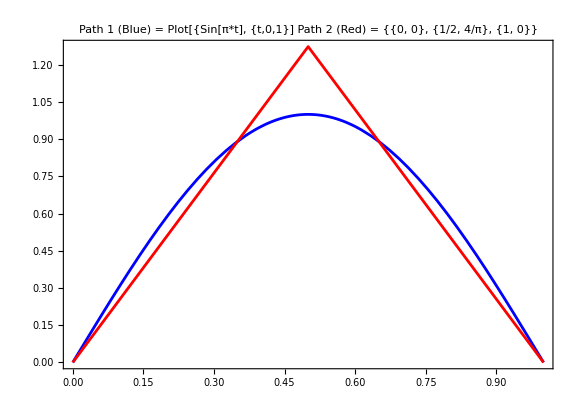

```mathematica
Show[Plot[Sin[π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t], {t,0,1}]
Path 2 (Red) = {{0, 0}, {1/2, 4/π}, {1, 0}}"],16]],
ListLinePlot[sinpit2sa,
PlotStyle->{ Red}]]
```

#### Sin[π t^2]

```mathematica
sinp3core=getcore6[sigsins1f2,3];
```

```mathematica
sinp3core
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])}}

```mathematica
solsts2p[Flatten[sinp3core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{1,(6/π-√2 FresnelS[√2])/(√2 FresnelS[√2]),(2 FresnelS[√2]^2)/(6/π-√2 FresnelS[√2]),-(2 FresnelS[√2]^2)/(-6/π+2 √2 FresnelS[√2])},{1,ComplexInfinity,0,0}}

```mathematica
{sinpitsq2sa,sinpitsq2sb}=solsts2pts[Flatten[sinp3core]]
```

Power::infy: Infinite expression 1/0 encountered.

{{{0,0},{(6/π-√2 FresnelS[√2])/(√2 FresnelS[√2]),√2 FresnelS[√2]},{1,0}},{{0,0},{ComplexInfinity,(3 (2-FresnelC[2]))/(4 √2 FresnelS[√2])},{1,0}}}

```mathematica
N[flengthpathpts[sinpitsq2sa]]
```

2.36247

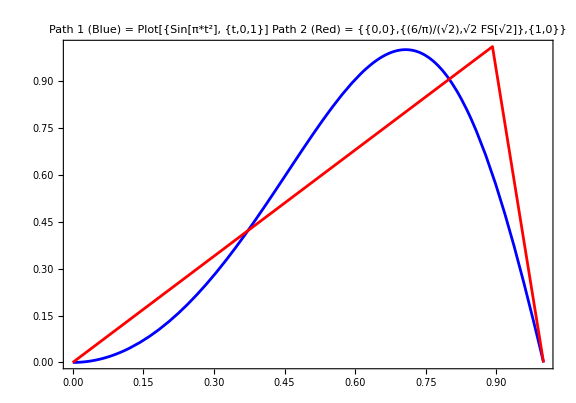

```mathematica
Show[Plot[Sin[π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2], {t,0,1}]
Path 2 (Red) = {{0,0},{(6/π)/(√2),√2 FS[√2]},{1,0}}"],16]],
ListLinePlot[sinpitsq2sa,
PlotStyle->{ Red}]]
```

#### Sin[π t^2]+1-t

```mathematica
Timing[sigsins2p1=signat[{{t,Sin[π (t)^2]+1-t}},{0,1},4][[1]]]
```

{55.9089,{{1},{1,-1},{{1/2,-1/2-FresnelS[√2]/(√2)},{-1/2+FresnelS[√2]/(√2),1/2}},{{{1/6,-(6+π)/(6 π)},{-1/6+2/π-FresnelS[√2]/(√2),5/12-1/π-FresnelC[2]/8+FresnelS[√2]/(√2)}},{{-1/6-1/π+FresnelS[√2]/(√2),-1/3+2/π+FresnelC[2]/4-FresnelS[√2]/(√2)},{5/12-1/π-FresnelC[2]/8,-1/6}}},{{{{1/24,-(6+π+3 √2 FresnelC[√2])/(24 π)},{-(6+π-9 √2 FresnelC[√2])/(24 π),(3+π-(3 FresnelC[√2])/(√2))/(6 π)}},{{-(-30+π+9 √2 FresnelC[√2]+6 √2 π FresnelS[√2])/(24 π),-(6-3 √2 FresnelC[√2]+1/4 π (5-6 FresnelS[√2] (√2+FresnelS[√2])))/(6 π)},{-1/π+1/24 (7-3 FresnelC[2]+6 √2 FresnelS[√2]-6 FresnelS[√2]^2),1/144 (-24+18 FresnelC[2]-(18 (-6+√2 FresnelC[√2]))/π-45 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{-(18+π-3 √2 FresnelC[√2]-6 √2 π FresnelS[√2])/(24 π),1/π+1/24 (1-6 √2 FresnelS[√2]-6 FresnelS[√2]^2)},{1/(24 π)(24-12 √2 FresnelC[√2]+π (-5+6 FresnelC[2]-6 √2 FresnelS[√2]+6 FresnelS[√2]^2)),1/(48 π)(-60+18 √2 FresnelC[√2]+π (4-12 FresnelC[2]+21 √2 FresnelS[√2]-√6 FresnelS[√6]))}},{{(-12+4 π-3 π FresnelC[2]+6 √2 FresnelC[√2])/(24 π),1/24 (2+3 FresnelC[2]+(6-9 √2 FresnelC[√2])/π-(9 FresnelS[√2])/(√2)+√(3/2) FresnelS[√6])},{1/144 (-24+(18 (2+√2 FresnelC[√2]))/π+9 √2 FresnelS[√2]-√6 FresnelS[√6]),1/24}}}}}}

```mathematica
Timing[sigs1t=signat[{{t,1-t}},{0,1},4][[1]]]
```

{0.004577,{{1},{1,-1},{{1/2,-1/2},{-1/2,1/2}},{{{1/6,-1/6},{-1/6,1/6}},{{-1/6,1/6},{1/6,-1/6}}},{{{{1/24,-1/24},{-1/24,1/24}},{{-1/24,1/24},{1/24,-1/24}}},{{{-1/24,1/24},{1/24,-1/24}},{{1/24,-1/24},{-1/24,1/24}}}}}}

```mathematica
sinp7core=getcore6[sigsins2p1,3]
```

{{1,-1},{-1/2-FresnelS[√2]/(√2)},{-(6+π)/(6 π),5/12-1/π-FresnelC[2]/8+FresnelS[√2]/(√2)}}

```mathematica
p1mtcore=getcore6[sigs1t,3]
```

{{1,-1},{-1/2},{-1/6,1/6}}

```mathematica
sinp3core
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])}}

```mathematica
Grid[{Expand[sinp3core],Expand[p1mtcore],Expand[sinp3core+p1mtcore],Expand[sinp7core]},Frame->All]
```

{1,0} | {-FresnelS[√2]/(√2)} | {-1/π,1/4-FresnelC[2]/8}
{1,-1} | {-1/2} | {-1/6,1/6}
{2,-1} | {-1/2-FresnelS[√2]/(√2)} | {-1/6-1/π,5/12-FresnelC[2]/8}
{1,-1} | {-1/2-FresnelS[√2]/(√2)} | {-1/6-1/π,5/12-1/π-FresnelC[2]/8+FresnelS[√2]/(√2)}

```mathematica
Timing[sigpola=signat[{{t,α t^a}},{0,1},3][[1]]]
```

{34.5935,{{1},{1,ConditionalExpression[α, Re[a]>0]},{{1/2,ConditionalExpression[(a α)/(1+a), Re[a]>-1]},{ConditionalExpression[α/(1+a), Re[a]>0],ConditionalExpression[α^2/2, Re[a]>0]}},{{{1/6,ConditionalExpression[(a α)/(2 (2+a)), Re[a]>-2]},{ConditionalExpression[(a α)/(2+3 a+a^2), Re[a]>-1],ConditionalExpression[(a^2 α^2)/((1+a) (1+2 a)), Re[a]>-1/2]}},{{ConditionalExpression[α/(2+3 a+a^2), Re[a]>0],ConditionalExpression[(a α^2)/(1+3 a+2 a^2), Re[a]>0]},{ConditionalExpression[α^2/(2+4 a), Re[a]>0],ConditionalExpression[α^3/6, Re[a]>0]}}}}}

```mathematica
getcore6[Refine[sigpola,a>0],3]
```

{{1,α},{(a α)/(1+a)},{(a α)/(2 (2+a)),(a^2 α^2)/((1+a) (1+2 a))}}

```mathematica
Timing[sigpolb=signat[{{t,β t^b}},{0,1},3][[1]]]
```

{35.3585,{{1},{1,ConditionalExpression[β, Re[b]>0]},{{1/2,ConditionalExpression[(b β)/(1+b), Re[b]>-1]},{ConditionalExpression[β/(1+b), Re[b]>0],ConditionalExpression[β^2/2, Re[b]>0]}},{{{1/6,ConditionalExpression[(b β)/(2 (2+b)), Re[b]>-2]},{ConditionalExpression[(b β)/(2+3 b+b^2), Re[b]>-1],ConditionalExpression[(b^2 β^2)/((1+b) (1+2 b)), Re[b]>-1/2]}},{{ConditionalExpression[β/(2+3 b+b^2), Re[b]>0],ConditionalExpression[(b β^2)/(1+3 b+2 b^2), Re[b]>0]},{ConditionalExpression[β^2/(2+4 b), Re[b]>0],ConditionalExpression[β^3/6, Re[b]>0]}}}}}

```mathematica
getcore6[Refine[sigpolb,b>0],3]
```

{{1,β},{(b β)/(1+b)},{(b β)/(2 (2+b)),(b^2 β^2)/((1+b) (1+2 b))}}

```mathematica
Timing[sigpolab=signat[{{t,α t^a+β t^b}},{0,1},3][[1]]]
```

{133.086,{{1},{1,ConditionalExpression[α+β, Re[a]>0&&Re[b]>0]},{{1/2,ConditionalExpression[(a α)/(1+a)+(b β)/(1+b), Re[a]>-1&&Re[b]>-1]},{ConditionalExpression[α/(1+a)+β/(1+b), Re[a]>0&&Re[b]>0],ConditionalExpression[1/2 (α+β)^2, Re[a]>0&&Re[b]>0]}},{{{1/6,ConditionalExpression[1/2 ((a α)/(2+a)+(b β)/(2+b)), Re[a]>-2&&Re[b]>-2]},{ConditionalExpression[(a α)/(2+3 a+a^2)+(b β)/(2+3 b+b^2), Re[a]>-1&&Re[b]>-1],ConditionalExpression[(a^2 α^2)/(1+3 a+2 a^2)+(a b (2+a+b) α β)/((1+a) (1+b) (1+a+b))+(b^2 β^2)/(1+3 b+2 b^2), Re[a]>-1/2&&Re[b]>-1/2]}},{{ConditionalExpression[α/(2+3 a+a^2)+β/(2+3 b+b^2), Re[a]>0&&Re[b]>0],ConditionalExpression[a α (α/(1+3 a+2 a^2)+β/((1+b) (1+a+b)))+b β (α/((1+a) (1+a+b))+β/(1+3 b+2 b^2)), Re[a]>0&&Re[b]>0]},{ConditionalExpression[1/2 (α^2/(1+2 a)+(2 α β)/(1+a+b)+β^2/(1+2 b)), Re[a]>0&&Re[b]>0],ConditionalExpression[1/6 (α+β)^3, Re[a]>0&&Re[b]>0]}}}}}

```mathematica
getcore6[Refine[sigpolab,a>0&&b>0],3]
```

{{1,α+β},{(a α)/(1+a)+(b β)/(1+b)},{1/2 ((a α)/(2+a)+(b β)/(2+b)),(a^2 α^2)/(1+3 a+2 a^2)+(a b (2+a+b) α β)/((1+a) (1+b) (1+a+b))+(b^2 β^2)/(1+3 b+2 b^2)}}

```mathematica
Grid[{
getcore6[Refine[sigpola,a>0],3],
getcore6[Refine[sigpolb,b>0],3],
Expand[getcore6[Refine[sigpola,a>0],3]+getcore6[Refine[sigpolb,b>0],3]],
Expand[getcore6[Refine[sigpolab,a>0&&b>0],3]]},Frame->All]
```

{1,α} | {(a α)/(1+a)} | {(a α)/(2 (2+a)),(a^2 α^2)/((1+a) (1+2 a))}
{1,β} | {(b β)/(1+b)} | {(b β)/(2 (2+b)),(b^2 β^2)/((1+b) (1+2 b))}
{2,α+β} | {(a α)/(1+a)+(b β)/(1+b)} | {(a α)/(2 (2+a))+(b β)/(2 (2+b)),(a^2 α^2)/((1+a) (1+2 a))+(b^2 β^2)/((1+b) (1+2 b))}
{1,α+β} | {(a α)/(1+a)+(b β)/(1+b)} | {(a α)/(2 (2+a))+(b β)/(2 (2+b)),(a^2 α^2)/(1+3 a+2 a^2)+(2 a b α β)/((1+a) (1+b) (1+a+b))+(a^2 b α β)/((1+a) (1+b) (1+a+b))+(a b^2 α β)/((1+a) (1+b) (1+a+b))+(b^2 β^2)/(1+3 b+2 b^2)}

```mathematica
FullSimplify[(2 a b α β)/((1+a) (1+b) (1+a+b))+(a^2 b α β)/((1+a) (1+b) (1+a+b))+(a b^2 α β)/((1+a) (1+b) (1+a+b))]
```

(a b (2+a+b) α β)/((1+a) (1+b) (1+a+b))

```mathematica
Grid[{
getcore6[sigpola,3],
getcore6[sigpolb,3],
Expand[getcore6[sigpola,3]+getcore6[sigpolb,3]],
Expand[getcore6[sigpolab,3]]},Frame->All]
```

{1,ConditionalExpression[α, Re[a]>0]} | {ConditionalExpression[(a α)/(1+a), Re[a]>-1]} | {ConditionalExpression[(a α)/(2 (2+a)), Re[a]>-2],ConditionalExpression[(a^2 α^2)/((1+a) (1+2 a)), Re[a]>-1/2]}
{1,ConditionalExpression[β, Re[b]>0]} | {ConditionalExpression[(b β)/(1+b), Re[b]>-1]} | {ConditionalExpression[(b β)/(2 (2+b)), Re[b]>-2],ConditionalExpression[(b^2 β^2)/((1+b) (1+2 b)), Re[b]>-1/2]}
{2,ConditionalExpression[α+β, Re[a]>0&&Re[b]>0]} | {ConditionalExpression[(a α)/(1+a)+(b β)/(1+b), Re[a]>-1&&Re[b]>-1]} | {ConditionalExpression[(a α)/(2 (2+a))+(b β)/(2 (2+b)), Re[a]>-2&&Re[b]>-2],ConditionalExpression[(a^2 α^2)/((1+a) (1+2 a))+(b^2 β^2)/((1+b) (1+2 b)), Re[a]>-1/2&&Re[b]>-1/2]}
{1,ConditionalExpression[α+β, Re[a]>0&&Re[b]>0]} | {ConditionalExpression[(a α)/(1+a)+(b β)/(1+b), Re[a]>-1&&Re[b]>-1]} | {ConditionalExpression[(a α)/(2 (2+a))+(b β)/(2 (2+b)), Re[a]>-2&&Re[b]>-2],ConditionalExpression[(a^2 α^2)/(1+3 a+2 a^2)+(2 a b α β)/((1+a) (1+b) (1+a+b))+(a^2 b α β)/((1+a) (1+b) (1+a+b))+(a b^2 α β)/((1+a) (1+b) (1+a+b))+(b^2 β^2)/(1+3 b+2 b^2), Re[a]>-1/2&&Re[b]>-1/2]}

```mathematica
FullSimplify[solsts2p[Flatten[sinp7core]]]
```

{{1,-1+(3 √2)/(π FresnelS[√2]),(6-π FresnelS[√2] (√2+2 FresnelS[√2]))/(-6+√2 π FresnelS[√2]),(3-π FresnelS[√2] (√2+FresnelS[√2]))/(-3+√2 π FresnelS[√2])},{1,(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]),-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2)),-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]+8 FresnelS[√2] (-√2+FresnelS[√2])))}}

```mathematica
{sinpitsqp1mt2sa,sinpitsqp1mt2sb}=FullSimplify[solsts2pts[Flatten[sinp7core],{0,1}]]
```

{{{0,1},{-1+(3 √2)/(π FresnelS[√2]),2+(√2 (-3+π FresnelS[√2]^2))/(π FresnelS[√2])},{1,0}},{{0,1},{(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]),(-24+π (6-3 FresnelC[2]+8 √2 FresnelS[√2]))/(4 √2 π FresnelS[√2])},{1,0}}}

```mathematica
N[{sinpitsqp1mt2sa,sinpitsqp1mt2sb}]
```

{{{0.,1.},{0.891494,1.11821},{1.,0.}},{{0.,1.},{0.778296,1.23141},{1.,0.}}}

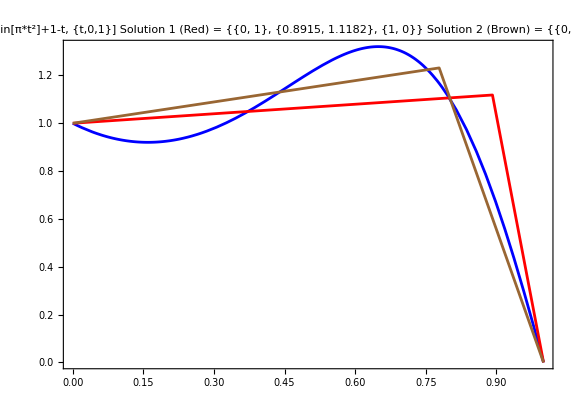

```mathematica
Show[Plot[Sin[π t^2]+1-t,{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2]+1-t, {t,0,1}]
Solution 1 (Red) = {{0, 1}, {0.8915, 1.1182}, {1, 0}}
Solution 2 (Brown) = {{0, 1}, {0.7783, 1.2314}, {1, 0}}"],16]],
ListLinePlot[{sinpitsqp1mt2sa,sinpitsqp1mt2sb},
PlotStyle->{ Red,Brown}]]
```

```mathematica
D[Sin[π*t^2]+1-t,{t,2}]
```

2 π Cos[π t^2]-4 π^2 t^2 Sin[π t^2]

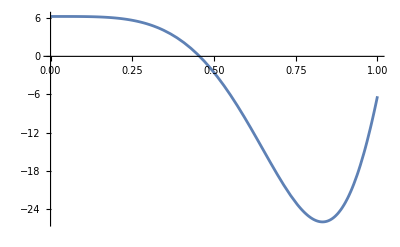

```mathematica
Plot[2 π Cos[π t^2]-4 π^2 t^2 Sin[π t^2],{t,0,1}]
```

```mathematica
NMinimize[{2 π Cos[π t^2]-4 π^2 t^2 Sin[π t^2],0<=t<=1},t]
```

{-26.0624,{t→0.831989}}

```mathematica
FindRoot[(Sin[π t^2]+1-t)-(1+((6-π FresnelS[√2] (√2+2 FresnelS[√2]))/(-6+√2 π FresnelS[√2]))t),{t,0.9},WorkingPrecision->10]
```

{t→0.7996158802}

```mathematica
FindRoot[(Sin[π t^2]+1-t)-(1+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2)))((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]))+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]+8 FresnelS[√2] (-√2+FresnelS[√2]))))(t-((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2])))),{t,0.85},WorkingPrecision->10]
```

{t→0.8025343779}

```mathematica
FindRoot[(1+((6-π FresnelS[√2] (√2+2 FresnelS[√2]))/(-6+√2 π FresnelS[√2]))t)-(1+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2)))((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2]))+(-1+(8 π FresnelS[√2]^2)/(24+π (-6+3 FresnelC[2]+8 FresnelS[√2] (-√2+FresnelS[√2]))))(t-((24+π (-6+3 FresnelC[2]-4 √2 FresnelS[√2]+8 FresnelS[√2]^2))/(4 √2 π FresnelS[√2])))),{t,0.85},WorkingPrecision->10]
```

FindRoot::bddir: The search direction {-3.416419792×10^-17} is not a descent direction for the merit function. The step will be taken without the line search.

{t→0.8008406871}

#### Two segments (Chen)

```mathematica
getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]
```

{{t_1+t_2,t_1 β_1+t_2 β_2},{1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2},{1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2,1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2}}

```mathematica
FullSimplify[solsts2p[Flatten[getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]]]]
```

{{t_1+t_2,t_1,β_1,β_2},{t_1+t_2,t_1,β_1,β_2}}

```mathematica
FullSimplify[solsts2pts[Flatten[getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]]]]
```

{{{0,0},{t_1,t_1 β_1},{t_1+t_2,t_1 β_1+t_2 β_2}},{{0,0},{t_1,t_1 β_1},{t_1+t_2,t_1 β_1+t_2 β_2}}}

```mathematica
eqschen2=MapThread[Equal,{Flatten[getcore6[sigchen[signat[{{t,Subscript[α, 1]+Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],signat[{{t,Subscript[α, 2]+Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],4],3]],{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2]}}]
```

{t_1+t_2==z_1,t_1 β_1+t_2 β_2==z_2,1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2==z_(1,2),1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2==z_(1,1,2),1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2==z_(1,2,2)}

### 3 lines

#### Definitions

```mathematica
chen3z4=chainchen[
{signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],
signat[{{t,Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],
signat[{{t,Subscript[β, 3] t}},{0,Subscript[t, 3]},4][[1]]},
4];
```

```mathematica
chen3z4core=getcore6[chen3z4,4];
```

```mathematica
Grid[Expand[chen3z4core],Frame->All]
```

t_1+t_2+t_3 | t_1 β_1+t_2 β_2+t_3 β_3 | 
1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2+t_1 t_3 β_3+t_2 t_3 β_3+1/2 t_3^2 β_3 |  | 
1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2+1/2 t_1^2 t_3 β_3+t_1 t_2 t_3 β_3+1/2 t_2^2 t_3 β_3+1/2 t_1 t_3^2 β_3+1/2 t_2 t_3^2 β_3+1/6 t_3^3 β_3 | 1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2+1/2 t_1^2 t_3 β_1 β_3+t_1 t_2 t_3 β_2 β_3+1/2 t_2^2 t_3 β_2 β_3+1/2 t_1 t_3^2 β_3^2+1/2 t_2 t_3^2 β_3^2+1/6 t_3^3 β_3^2 | 
1/24 t_1^4 β_1+1/6 t_1^3 t_2 β_2+1/4 t_1^2 t_2^2 β_2+1/6 t_1 t_2^3 β_2+1/24 t_2^4 β_2+1/6 t_1^3 t_3 β_3+1/2 t_1^2 t_2 t_3 β_3+1/2 t_1 t_2^2 t_3 β_3+1/6 t_2^3 t_3 β_3+1/4 t_1^2 t_3^2 β_3+1/2 t_1 t_2 t_3^2 β_3+1/4 t_2^2 t_3^2 β_3+1/6 t_1 t_3^3 β_3+1/6 t_2 t_3^3 β_3+1/24 t_3^4 β_3 | 1/24 t_1^4 β_1^2+1/6 t_1^3 t_2 β_1 β_2+1/4 t_1^2 t_2^2 β_2^2+1/6 t_1 t_2^3 β_2^2+1/24 t_2^4 β_2^2+1/6 t_1^3 t_3 β_1 β_3+1/2 t_1^2 t_2 t_3 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2 β_3+1/6 t_2^3 t_3 β_2 β_3+1/4 t_1^2 t_3^2 β_3^2+1/2 t_1 t_2 t_3^2 β_3^2+1/4 t_2^2 t_3^2 β_3^2+1/6 t_1 t_3^3 β_3^2+1/6 t_2 t_3^3 β_3^2+1/24 t_3^4 β_3^2 | 1/24 t_1^4 β_1^3+1/6 t_1^3 t_2 β_1^2 β_2+1/4 t_1^2 t_2^2 β_1 β_2^2+1/6 t_1 t_2^3 β_2^3+1/24 t_2^4 β_2^3+1/6 t_1^3 t_3 β_1^2 β_3+1/2 t_1^2 t_2 t_3 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2^2 β_3+1/6 t_2^3 t_3 β_2^2 β_3+1/4 t_1^2 t_3^2 β_1 β_3^2+1/2 t_1 t_2 t_3^2 β_2 β_3^2+1/4 t_2^2 t_3^2 β_2 β_3^2+1/6 t_1 t_3^3 β_3^3+1/6 t_2 t_3^3 β_3^3+1/24 t_3^4 β_3^3

```mathematica
rulesnosubs3={Subscript[β, 1]->β1,Subscript[β, 2]->β2,Subscript[β, 3]->β3,Subscript[t, 1]->t1,Subscript[t, 2]->t2,Subscript[t, 3]->t3};
```

```mathematica
rulestosubs3={β1->Subscript[β, 1],β2->Subscript[β, 2],β3->Subscript[β, 3],t1->Subscript[t, 1],t2->Subscript[t, 2],t3->Subscript[t, 3]};
```

```mathematica
rulessubs3x={β1->x[1],β2->x[3],β3->x[5],t1->x[0],t2->x[2],t3->x[4]};
```

```mathematica
fsortsum[polyn_,rulesno_,rulesto_]:=Module[{expoly,key,dict,sorteddict},
expoly=Expand[polyn]//.rulesno;
key=Map[Apply[List,#]&,Map[Apply[List,#]&,Apply[List,expoly]],{2}];
dict=Transpose[{key,Apply[List,expoly]}];
sorteddict=SortBy[dict,First[First[#]]&];
Last[Transpose[sorteddict]]//.rulesto
];
```

```mathematica
fsortsumx[polyn_,rulesno_,rulesto_]:=Module[{expoly,key,keyex,sortedkeyex},
expoly=Expand[polyn]//.rulesno;
key=Map[Apply[List,#]&,Map[Apply[List,#]&,Apply[List,expoly]],{2}];
keyex = Map[If[ListQ[#],Apply[ConstantArray,#],#]&,key,{2}]//.rulesto ;
sortedkeyex=SortBy[Map[Flatten,keyex],First];
sortedkeyex//.rulesto 
];
```

```mathematica
fsortsumx[chen3z4core[[2,1]],rulesnosubs3,rulessubs3x]
```

{{1/2,x[0],x[0],x[1]},{1/2,x[2],x[2],x[3]},{1/2,x[4],x[4],x[5]},{x[0],x[2],x[3]},{x[0],x[4],x[5]},{x[2],x[4],x[5]}}

```mathematica
fsortsumx[chen3z4core[[3,1]],rulesnosubs3,rulessubs3x]
```

{{1/6,x[0],x[0],x[0],x[1]},{1/6,x[2],x[2],x[2],x[3]},{1/6,x[4],x[4],x[4],x[5]},{1/2,x[0],x[0],x[2],x[3]},{1/2,x[0],x[0],x[4],x[5]},{1/2,x[0],x[2],x[2],x[3]},{1/2,x[0],x[4],x[4],x[5]},{1/2,x[2],x[2],x[4],x[5]},{1/2,x[2],x[4],x[4],x[5]},{x[0],x[2],x[4],x[5]}}

```mathematica
fsortsumx[chen3z4core[[3,2]],rulesnosubs3,rulessubs3x]
```

{{1/6,x[0],x[0],x[0],x[1],x[1]},{1/6,x[2],x[2],x[2],x[3],x[3]},{1/6,x[4],x[4],x[4],x[5],x[5]},{1/2,x[0],x[0],x[2],x[1],x[3]},{1/2,x[0],x[0],x[4],x[1],x[5]},{1/2,x[0],x[2],x[2],x[3],x[3]},{1/2,x[0],x[4],x[4],x[5],x[5]},{1/2,x[2],x[2],x[4],x[3],x[5]},{1/2,x[2],x[4],x[4],x[5],x[5]},{x[0],x[2],x[4],x[3],x[5]}}

```mathematica
fsortsumx[chen3z4core[[4,1]],rulesnosubs3,rulessubs3x]
```

{{1/24,x[0],x[0],x[0],x[0],x[1]},{1/24,x[2],x[2],x[2],x[2],x[3]},{1/24,x[4],x[4],x[4],x[4],x[5]},{1/6,x[0],x[0],x[0],x[2],x[3]},{1/6,x[0],x[0],x[0],x[4],x[5]},{1/6,x[0],x[2],x[2],x[2],x[3]},{1/6,x[0],x[4],x[4],x[4],x[5]},{1/6,x[2],x[2],x[2],x[4],x[5]},{1/6,x[2],x[4],x[4],x[4],x[5]},{1/4,x[0],x[0],x[2],x[2],x[3]},{1/4,x[0],x[0],x[4],x[4],x[5]},{1/4,x[2],x[2],x[4],x[4],x[5]},{1/2,x[0],x[0],x[2],x[4],x[5]},{1/2,x[0],x[2],x[2],x[4],x[5]},{1/2,x[0],x[2],x[4],x[4],x[5]}}

```mathematica
fsortsumx[chen3z4core[[4,2]],rulesnosubs3,rulessubs3x]
```

{{1/24,x[0],x[0],x[0],x[0],x[1],x[1]},{1/24,x[2],x[2],x[2],x[2],x[3],x[3]},{1/24,x[4],x[4],x[4],x[4],x[5],x[5]},{1/6,x[0],x[0],x[0],x[2],x[1],x[3]},{1/6,x[0],x[0],x[0],x[4],x[1],x[5]},{1/6,x[0],x[2],x[2],x[2],x[3],x[3]},{1/6,x[0],x[4],x[4],x[4],x[5],x[5]},{1/6,x[2],x[2],x[2],x[4],x[3],x[5]},{1/6,x[2],x[4],x[4],x[4],x[5],x[5]},{1/4,x[0],x[0],x[2],x[2],x[3],x[3]},{1/4,x[0],x[0],x[4],x[4],x[5],x[5]},{1/4,x[2],x[2],x[4],x[4],x[5],x[5]},{1/2,x[0],x[0],x[2],x[4],x[3],x[5]},{1/2,x[0],x[2],x[2],x[4],x[3],x[5]},{1/2,x[0],x[2],x[4],x[4],x[5],x[5]}}

```mathematica
fsortsumx[chen3z4core[[4,3]],rulesnosubs3,rulessubs3x]
```

{{1/24,x[0],x[0],x[0],x[0],x[1],x[1],x[1]},{1/24,x[2],x[2],x[2],x[2],x[3],x[3],x[3]},{1/24,x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/6,x[0],x[0],x[0],x[2],x[1],x[1],x[3]},{1/6,x[0],x[0],x[0],x[4],x[1],x[1],x[5]},{1/6,x[0],x[2],x[2],x[2],x[3],x[3],x[3]},{1/6,x[0],x[4],x[4],x[4],x[5],x[5],x[5]},{1/6,x[2],x[2],x[2],x[4],x[3],x[3],x[5]},{1/6,x[2],x[4],x[4],x[4],x[5],x[5],x[5]},{1/4,x[0],x[0],x[2],x[2],x[1],x[3],x[3]},{1/4,x[0],x[0],x[4],x[4],x[1],x[5],x[5]},{1/4,x[2],x[2],x[4],x[4],x[3],x[5],x[5]},{1/2,x[0],x[0],x[2],x[4],x[1],x[3],x[5]},{1/2,x[0],x[2],x[2],x[4],x[3],x[3],x[5]},{1/2,x[0],x[2],x[4],x[4],x[3],x[5],x[5]}}

```mathematica
fsortsum[chen3z4core[[2,1]],rulesnosubs3,rulestosubs3]
```

{1/2 t_1^2 β_1,1/2 t_2^2 β_2,1/2 t_3^2 β_3,t_1 t_2 β_2,t_1 t_3 β_3,t_2 t_3 β_3}

```mathematica
Map[(#/{Subscript[t, 1],Subscript[t, 2],Subscript[t, 3]})&,{{1/2 Subscript[t, 1]^2 Subscript[β, 1],1/2 Subscript[t, 2]^2 Subscript[β, 2],1/2 Subscript[t, 3]^2 Subscript[β, 3]},{Subscript[t, 1] Subscript[t, 3] Subscript[β, 3],Subscript[t, 1] Subscript[t, 2] Subscript[β, 2],Subscript[t, 2] Subscript[t, 3] Subscript[β, 3]}}]
```

{{(t_1 β_1)/2,(t_2 β_2)/2,(t_3 β_3)/2},{t_3 β_3,t_1 β_2,t_2 β_3}}

```mathematica
Map[(#/{Subscript[β, 1] Subscript[t, 1],Subscript[β, 2] Subscript[t, 2],Subscript[β, 3] Subscript[t, 3]})&,{{1/2 Subscript[t, 1]^2 Subscript[β, 1],1/2 Subscript[t, 2]^2 Subscript[β, 2],1/2 Subscript[t, 3]^2 Subscript[β, 3]},{Subscript[t, 1] Subscript[t, 3] Subscript[β, 3],Subscript[t, 1] Subscript[t, 2] Subscript[β, 2],Subscript[t, 2] Subscript[t, 3] Subscript[β, 3]}}]
```

{{t_1/2,t_2/2,t_3/2},{(t_3 β_3)/β_1,t_1,t_2}}

```mathematica
fsortsum[chen3z4core[[3,1]],rulesnosubs3,rulestosubs3]
```

{1/6 t_1^3 β_1,1/6 t_2^3 β_2,1/6 t_3^3 β_3,1/2 t_1 t_2^2 β_2,1/2 t_1 t_3^2 β_3,1/2 t_2 t_3^2 β_3,1/2 t_1^2 t_2 β_2,1/2 t_1^2 t_3 β_3,1/2 t_2^2 t_3 β_3,t_1 t_2 t_3 β_3}

```mathematica
FullSimplify[{{1/6 Subscript[t, 1]^3 Subscript[β, 1],1/6 Subscript[t, 2]^3 Subscript[β, 2],1/6 Subscript[t, 3]^3 Subscript[β, 3]}/{1/2 Subscript[t, 1]^2 Subscript[β, 1],1/2 Subscript[t, 2]^2 Subscript[β, 2],1/2 Subscript[t, 3]^2 Subscript[β, 3]},
{1/2 Subscript[t, 1] Subscript[t, 2]^2 Subscript[β, 2]+1/2 Subscript[t, 1]^2 Subscript[t, 2] Subscript[β, 2],1/2 Subscript[t, 1] Subscript[t, 3]^2 Subscript[β, 3]+1/2 Subscript[t, 1]^2 Subscript[t, 3] Subscript[β, 3],1/2 Subscript[t, 2] Subscript[t, 3]^2 Subscript[β, 3]+1/2 Subscript[t, 2]^2 Subscript[t, 3] Subscript[β, 3]}/{Subscript[t, 1] Subscript[t, 2] Subscript[β, 2],Subscript[t, 1] Subscript[t, 3] Subscript[β, 3],Subscript[t, 2] Subscript[t, 3] Subscript[β, 3]},
(Subscript[t, 1] Subscript[t, 2] Subscript[t, 3] Subscript[β, 3])/(Subscript[t, 2] Subscript[t, 3] Subscript[β, 3])}]
```

{{t_1/3,t_2/3,t_3/3},{1/2 (t_1+t_2),1/2 (t_1+t_3),1/2 (t_2+t_3)},t_1}

```mathematica
fsortsum[chen3z4core[[3,2]],rulesnosubs3,rulestosubs3]
```

{1/6 t_1^3 β_1^2,1/6 t_2^3 β_2^2,1/6 t_3^3 β_3^2,1/2 t_1 t_2^2 β_2^2,1/2 t_1 t_3^2 β_3^2,1/2 t_2 t_3^2 β_3^2,1/2 t_1^2 t_2 β_1 β_2,1/2 t_1^2 t_3 β_1 β_3,1/2 t_2^2 t_3 β_2 β_3,t_1 t_2 t_3 β_2 β_3}

```mathematica
fsortsum[chen3z4core[[4,1]],rulesnosubs3,rulestosubs3]
```

{1/24 t_1^4 β_1,1/24 t_2^4 β_2,1/24 t_3^4 β_3,1/6 t_1 t_2^3 β_2,1/6 t_1 t_3^3 β_3,1/6 t_2 t_3^3 β_3,1/6 t_1^3 t_2 β_2,1/6 t_1^3 t_3 β_3,1/6 t_2^3 t_3 β_3,1/4 t_1^2 t_2^2 β_2,1/4 t_1^2 t_3^2 β_3,1/4 t_2^2 t_3^2 β_3,1/2 t_1 t_2 t_3^2 β_3,1/2 t_1 t_2^2 t_3 β_3,1/2 t_1^2 t_2 t_3 β_3}

```mathematica
fsortsum[chen3z4core[[4,2]],rulesnosubs3,rulestosubs3]
```

{1/24 t_1^4 β_1^2,1/24 t_2^4 β_2^2,1/24 t_3^4 β_3^2,1/6 t_1 t_2^3 β_2^2,1/6 t_1 t_3^3 β_3^2,1/6 t_2 t_3^3 β_3^2,1/6 t_1^3 t_2 β_1 β_2,1/6 t_1^3 t_3 β_1 β_3,1/6 t_2^3 t_3 β_2 β_3,1/4 t_1^2 t_2^2 β_2^2,1/4 t_1^2 t_3^2 β_3^2,1/4 t_2^2 t_3^2 β_3^2,1/2 t_1 t_2 t_3^2 β_3^2,1/2 t_1 t_2^2 t_3 β_2 β_3,1/2 t_1^2 t_2 t_3 β_2 β_3}

```mathematica
fsortsum[chen3z4core[[4,3]],rulesnosubs3,rulestosubs3]
```

{1/24 t_1^4 β_1^3,1/24 t_2^4 β_2^3,1/24 t_3^4 β_3^3,1/6 t_1 t_2^3 β_2^3,1/6 t_1 t_3^3 β_3^3,1/6 t_2 t_3^3 β_3^3,1/6 t_1^3 t_2 β_1^2 β_2,1/6 t_1^3 t_3 β_1^2 β_3,1/6 t_2^3 t_3 β_2^2 β_3,1/4 t_1^2 t_2^2 β_1 β_2^2,1/4 t_1^2 t_3^2 β_1 β_3^2,1/4 t_2^2 t_3^2 β_2 β_3^2,1/2 t_1 t_2 t_3^2 β_2 β_3^2,1/2 t_1 t_2^2 t_3 β_2^2 β_3,1/2 t_1^2 t_2 t_3 β_1 β_2 β_3}

```mathematica
fsortsum[chen3z4core[[1,2]],rulesnosubs3,rulestosubs3]/fsortsum[chen3z4core[[1,1]],rulesnosubs3,rulestosubs3]
```

First::normal: Nonatomic expression expected at position 1 in First[t1].

First::normal: Nonatomic expression expected at position 1 in First[t2].

First::normal: Nonatomic expression expected at position 1 in First[t3].

General::stop: Further output of First::normal will be suppressed during this calculation.

{β_1,β_2,β_3}

```mathematica
fsortsum[chen3z4core[[3,2]],rulesnosubs3,rulestosubs3]/fsortsum[chen3z4core[[3,1]],rulesnosubs3,rulestosubs3]
```

{β_1,β_2,β_3,β_2,β_3,β_3,β_1,β_1,β_2,β_2}

```mathematica
fsortsum[chen3z4core[[4,2]],rulesnosubs3,rulestosubs3]/fsortsum[chen3z4core[[4,1]],rulesnosubs3,rulestosubs3]
```

{β_1,β_2,β_3,β_2,β_3,β_3,β_1,β_1,β_2,β_2,β_3,β_3,β_3,β_2,β_2}

```mathematica
fsortsum[chen3z4core[[4,3]],rulesnosubs3,rulestosubs3]/fsortsum[chen3z4core[[4,2]],rulesnosubs3,rulestosubs3]
```

{β_1,β_2,β_3,β_2,β_3,β_3,β_1,β_1,β_2,β_1,β_1,β_2,β_2,β_2,β_1}

```mathematica
vars3linechen={Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[t, 1],Subscript[t, 2],Subscript[t, 3]};
```

```mathematica
eqs3linechen234=MapThread[Equal,{
Expand[Flatten[chen3z4core]],
{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2]}}];
```

```mathematica
Grid[Transpose[{eqs3linechen234}],Frame->All,Alignment->Left]
```

t_1+t_2+t_3==z_1
t_1 β_1+t_2 β_2+t_3 β_3==z_2
1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2+t_1 t_3 β_3+t_2 t_3 β_3+1/2 t_3^2 β_3==z_(1,2)
1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2+1/2 t_1^2 t_3 β_3+t_1 t_2 t_3 β_3+1/2 t_2^2 t_3 β_3+1/2 t_1 t_3^2 β_3+1/2 t_2 t_3^2 β_3+1/6 t_3^3 β_3==z_(1,1,2)
1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2+1/2 t_1^2 t_3 β_1 β_3+t_1 t_2 t_3 β_2 β_3+1/2 t_2^2 t_3 β_2 β_3+1/2 t_1 t_3^2 β_3^2+1/2 t_2 t_3^2 β_3^2+1/6 t_3^3 β_3^2==z_(1,2,2)
1/24 t_1^4 β_1+1/6 t_1^3 t_2 β_2+1/4 t_1^2 t_2^2 β_2+1/6 t_1 t_2^3 β_2+1/24 t_2^4 β_2+1/6 t_1^3 t_3 β_3+1/2 t_1^2 t_2 t_3 β_3+1/2 t_1 t_2^2 t_3 β_3+1/6 t_2^3 t_3 β_3+1/4 t_1^2 t_3^2 β_3+1/2 t_1 t_2 t_3^2 β_3+1/4 t_2^2 t_3^2 β_3+1/6 t_1 t_3^3 β_3+1/6 t_2 t_3^3 β_3+1/24 t_3^4 β_3==z_(1,1,1,2)
1/24 t_1^4 β_1^2+1/6 t_1^3 t_2 β_1 β_2+1/4 t_1^2 t_2^2 β_2^2+1/6 t_1 t_2^3 β_2^2+1/24 t_2^4 β_2^2+1/6 t_1^3 t_3 β_1 β_3+1/2 t_1^2 t_2 t_3 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2 β_3+1/6 t_2^3 t_3 β_2 β_3+1/4 t_1^2 t_3^2 β_3^2+1/2 t_1 t_2 t_3^2 β_3^2+1/4 t_2^2 t_3^2 β_3^2+1/6 t_1 t_3^3 β_3^2+1/6 t_2 t_3^3 β_3^2+1/24 t_3^4 β_3^2==z_(1,1,2,2)
1/24 t_1^4 β_1^3+1/6 t_1^3 t_2 β_1^2 β_2+1/4 t_1^2 t_2^2 β_1 β_2^2+1/6 t_1 t_2^3 β_2^3+1/24 t_2^4 β_2^3+1/6 t_1^3 t_3 β_1^2 β_3+1/2 t_1^2 t_2 t_3 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2^2 β_3+1/6 t_2^3 t_3 β_2^2 β_3+1/4 t_1^2 t_3^2 β_1 β_3^2+1/2 t_1 t_2 t_3^2 β_2 β_3^2+1/4 t_2^2 t_3^2 β_2 β_3^2+1/6 t_1 t_3^3 β_3^3+1/6 t_2 t_3^3 β_3^3+1/24 t_3^4 β_3^3==z_(1,2,2,2)

```mathematica
cores4={Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2]};
```

```mathematica
solve3lines[eqsleft_,cores_,vars_,delpos_:{},bounds_:{},precis_:Automatic]:=Module[{eqs},
eqs=MapThread[Equal,{eqsleft,cores}];
NSolve[Join[Delete[eqs,delpos],bounds],vars,Reals,WorkingPrecision->precis]];
```

```mathematica
minim3linesfw[eqsleft_,cores_,weights_]:=Module[{eqs},
eqs=Flatten[MapThread[(#1-#2)^2&,{eqsleft,cores}]];
Dot[weights,eqs]];
```

```mathematica
minim3lines[eqsleft_,cores_,weights_,vars_,bounds_:{},method_:Automatic]:=Module[{eqs,minimf},
eqs=Flatten[MapThread[(#1-#2)^2&,{eqsleft,cores}]];
minimf=Dot[weights,eqs];
NMinimize[Join[{minimf},bounds],vars,Method->method]];
```

```mathematica
weights3seg={50,50,30,10,10,3,3,3};
```

```mathematica
bounds3seg={Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0};
```

```mathematica
fpw3[sollist_,t_]:=Module[{β1,β2,β3,t1,t2,t3},
{β1,β2,β3,t1,t2,t3}=sollist;
Piecewise[{{β1 t, 0≤t≤t1}, {β1 t1+β2(t-t1), t1<t≤(t1+t2)}, {β1 t1+β2 t2+β3(t-(t1+t2)), (t1+t2)<t≤(t1+t2+t3)}}]];
```

#### Sin[π t]

```mathematica
sigsins1fcore=getcore6[sigsins1f,4]
```

{{1,0},{-2/π},{-1/π,1/4},{-(-4+π^2)/(2 π^3),1/8,-2/(9 π)}}

```mathematica
Timing[minim4sint=minim3lines[Flatten[chen3z4core],Flatten[sigsins1fcore],weights3seg,vars3linechen,bounds3seg]]
```

{1.16685,{6.53651×10^-7,{β_1→2.95772,β_2→-0.0344035,β_3→-2.96822,t_1→0.315255,t_2→0.374953,t_3→0.309793}}}

```mathematica
ptsminim4sint=flistbetat[Last[minim4sint]]
```

{{0,0},{0.315255,0.932434},{0.690208,0.919534},{1.,-3.00937×10^-7}}

```mathematica
sol4sin1ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→3.39259,β_2→0.92707,β_3→-2.77485,t_1→0.20166,t_2→0.413595,t_3→0.38474},{β_1→2.77485,β_2→-0.92707,β_3→-3.39259,t_1→0.38474,t_2→0.413595,t_3→0.20166}}

```mathematica
sol4sin1ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→3.277,β_2→0.918,β_3→-2.8572,t_1→0.20877,t_2→0.41758,t_3→0.37365},{β_1→2.878,β_2→-0.916,β_3→-3.2506,t_1→0.371,t_2→0.41853,t_3→0.21047}}

```mathematica
sol4sin1ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→2.97825,β_2→0.04578,β_3→-2.9547,t_1→0.30772,t_2→0.37627,t_3→0.316}}

```mathematica
sol4sin1ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→2.915,β_2→-0.223,β_3→-2.9801,t_1→0.33267,t_2→0.36954,t_3→0.29779}}

```mathematica
sol4sin1ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→3.0137,β_2→0.3755,β_3→-2.9005,t_1→0.28308,t_2→0.37433,t_3→0.34259},{β_1→2.9005,β_2→-0.3755,β_3→-3.0137,t_1→0.34259,t_2→0.37433,t_3→0.28308}}

```mathematica
sol4sin1ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→2.92534,β_2→-0.174,β_3→-2.97651,t_1→0.32837,t_2→0.3706,t_3→0.3011}}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{sol4sin1ex46,sol4sin1ex47,sol4sin1ex48,sol4sin1ex56,sol4sin1ex57,sol4sin1ex58}]]
```

β_1→3.39259 | β_2→0.92707 | β_3→-2.77485 | t_1→0.20166 | t_2→0.413595 | t_3→0.38474
β_1→2.77485 | β_2→-0.92707 | β_3→-3.39259 | t_1→0.38474 | t_2→0.413595 | t_3→0.20166
β_1→3.277 | β_2→0.918 | β_3→-2.8572 | t_1→0.20877 | t_2→0.41758 | t_3→0.37365
β_1→2.878 | β_2→-0.916 | β_3→-3.2506 | t_1→0.371 | t_2→0.41853 | t_3→0.21047
β_1→2.97825 | β_2→0.04578 | β_3→-2.9547 | t_1→0.30772 | t_2→0.37627 | t_3→0.316
β_1→2.915 | β_2→-0.223 | β_3→-2.9801 | t_1→0.33267 | t_2→0.36954 | t_3→0.29779
β_1→3.0137 | β_2→0.3755 | β_3→-2.9005 | t_1→0.28308 | t_2→0.37433 | t_3→0.34259
β_1→2.9005 | β_2→-0.3755 | β_3→-3.0137 | t_1→0.34259 | t_2→0.37433 | t_3→0.28308
β_1→2.92534 | β_2→-0.174 | β_3→-2.97651 | t_1→0.32837 | t_2→0.3706 | t_3→0.3011

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistbetat,{sol4sin1ex46,sol4sin1ex47,sol4sin1ex48,sol4sin1ex56,sol4sin1ex57,sol4sin1ex58},{2}]]]
```

{0,0} | {0.20166,0.68417} | {0.61526,1.0676} | {1.,0.}
{0,0} | {0.38474,1.0676} | {0.79834,0.68417} | {1.,0.}
{0,0} | {0.20877,0.6842} | {0.62635,1.068} | {1.,0.}
{0,0} | {0.371,1.068} | {0.78953,0.684} | {1.,0.}
{0,0} | {0.30772,0.91647} | {0.684,0.9337} | {1.,0.}
{0,0} | {0.33267,0.9698} | {0.70221,0.8874} | {1.,0.}
{0,0} | {0.28308,0.85312} | {0.65741,0.9937} | {1.,0.}
{0,0} | {0.34259,0.99368} | {0.71692,0.8531} | {1.,0.}
{0,0} | {0.32837,0.96058} | {0.6989,0.89609} | {1.,0.}

```mathematica
TableForm[Map[flengthpathpts[flistbetat[#]]&,{sol4sin1ex46,sol4sin1ex47,sol4sin1ex48,sol4sin1ex56,sol4sin1ex57,sol4sin1ex58},{2}]]
```

2.4121 | 2.412
2.41 | 2.41
2.329 | 
2.34 | 
2.35 | 2.35
2.337 |

```mathematica
ptssol4sint=Flatten[Map[flistbetat,{sol4sin1ex46,sol4sin1ex47,sol4sin1ex48,sol4sin1ex56,sol4sin1ex57,sol4sin1ex58},{2}],1]
```

{{{0,0},{0.20166,0.68417},{0.61526,1.0676},{1.,0.}},{{0,0},{0.38474,1.0676},{0.79834,0.68417},{1.,0.}},{{0,0},{0.20877,0.6842},{0.62635,1.068},{1.,0.}},{{0,0},{0.371,1.068},{0.78953,0.684},{1.,0.}},{{0,0},{0.30772,0.91647},{0.684,0.9337},{1.,0.}},{{0,0},{0.33267,0.9698},{0.70221,0.8874},{1.,0.}},{{0,0},{0.28308,0.85312},{0.65741,0.9937},{1.,0.}},{{0,0},{0.34259,0.99368},{0.71692,0.8531},{1.,0.}},{{0,0},{0.32837,0.96058},{0.6989,0.89609},{1.,0.}}}

```mathematica
Length[ptssol4sint]
```

9

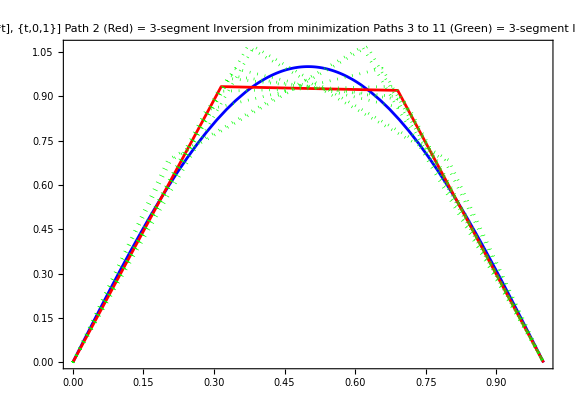

```mathematica
Show[Plot[Sin[π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t], {t,0,1}]
Path 2 (Red) = 3-segment Inversion from minimization
Paths 3 to 11 (Green) = 3-segment Inversions from dropping equations"
],16]],
ListLinePlot[Prepend[ptssol4sint,ptsminim4sint],
PlotStyle->Prepend[ConstantArray[{Dotted,Green},Length[ptssol4sint]],{Red}]]]
```

#### Sin[2 π t]

```mathematica
sigsins2fcore=getcore6[sigsins2f,4]
```

{{1,0},{0},{1/(2 π),1/4},{1/(4 π),1/8,0}}

```mathematica
Timing[minim4sin2t=minim3lines[Flatten[chen3z4core],Flatten[sigsins2fcore],weights3seg,vars3linechen,bounds3seg]]
```

{0.896067,{8.55556×10^-21,{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.220303,t_2→0.559394,t_3→0.220303}}}

```mathematica
ptsminim4sin2t=flistbetat[Last[minim4sin2t]]
```

{{0,0},{0.220303,1.22474},{0.779697,-1.22474},{1.,-1.89848×10^-13}}

```mathematica
sol4sin2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 t_1)/30458+(20993 t_2)/30458-(27178 t_3)/45687-(71297 β_1)/91374-(173881 β_2)/182748+(11342 β_3)/15229 == 1.

{{β_1→-77.68,β_2→2.5292,β_3→-77.68,t_1→0.0158,t_2→0.96847,t_3→0.0158},{β_1→58.204,β_2→-2.5571,β_3→58.204,t_1→0.021,t_2→0.95792,t_3→0.021}}

```mathematica
sol4sin2ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}}

```mathematica
sol4sin2ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}}

```mathematica
sol4sin2ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}}

```mathematica
sol4sin2ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(19857 t_1)/30458+(20993 t_2)/30458-(27178 t_3)/45687-(71297 β_1)/91374-(173881 β_2)/182748+(11342 β_3)/15229 == 1.

{{β_1→44.353,β_2→-2.0428,β_3→44.353,t_1→0.022,t_2→0.95597,t_3→0.022}}

```mathematica
sol4sin2ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→5.55936,β_2→-4.37883,β_3→5.55936,t_1→0.2203,t_2→0.55939,t_3→0.2203}}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{sol4sin2ex46,sol4sin2ex47,sol4sin2ex48,sol4sin2ex56,sol4sin2ex57,sol4sin2ex58}]]
```

β_1→-77.68 | β_2→2.5292 | β_3→-77.68 | t_1→0.0158 | t_2→0.96847 | t_3→0.0158
β_1→58.204 | β_2→-2.5571 | β_3→58.204 | t_1→0.021 | t_2→0.95792 | t_3→0.021
β_1→5.55936 | β_2→-4.37883 | β_3→5.55936 | t_1→0.2203 | t_2→0.55939 | t_3→0.2203
β_1→5.55936 | β_2→-4.37883 | β_3→5.55936 | t_1→0.2203 | t_2→0.55939 | t_3→0.2203
β_1→5.55936 | β_2→-4.37883 | β_3→5.55936 | t_1→0.2203 | t_2→0.55939 | t_3→0.2203
β_1→44.353 | β_2→-2.0428 | β_3→44.353 | t_1→0.022 | t_2→0.95597 | t_3→0.022
β_1→5.55936 | β_2→-4.37883 | β_3→5.55936 | t_1→0.2203 | t_2→0.55939 | t_3→0.2203

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistbetat,{sol4sin2ex46,sol4sin2ex47,sol4sin2ex48,sol4sin2ex56,sol4sin2ex57,sol4sin2ex58},{2}]]]
```

{0,0} | {0.0158,-1.22} | {0.9842,1.22} | {1.,0.}
{0,0} | {0.021,1.22} | {0.979,-1.22} | {1.,0.}
{0,0} | {0.2203,1.2247} | {0.7797,-1.2247} | {1.,0.}
{0,0} | {0.2203,1.2247} | {0.7797,-1.2247} | {1.,0.}
{0,0} | {0.2203,1.2247} | {0.7797,-1.2247} | {1.,0.}
{0,0} | {0.022,0.976} | {0.97799,-0.977} | {1.,0.}
{0,0} | {0.2203,1.2247} | {0.7797,-1.2247} | {1.,0.}

```mathematica
TableForm[Map[flengthpathpts[flistbetat[#]]&,{sol4sin2ex46,sol4sin2ex47,sol4sin2ex48,sol4sin2ex56,sol4sin2ex57,sol4sin2ex58},{2}]]
```

5.08 | 5.08
5.0014 | 
5.0014 | 
5.0014 | 
4.13 | 
5.0014 |

```mathematica
ptssol4sin2t=flistbetat[sol4sin2ex48[[1]]]
```

{{0,0},{0.2203,1.2247},{0.7797,-1.2247},{1.,0.}}

```mathematica
ptsminim4sin2t
```

{{0,0},{0.220303,1.22474},{0.779697,-1.22474},{1.,-1.89848×10^-13}}

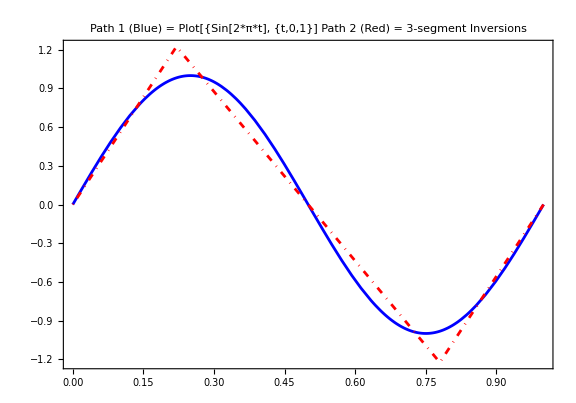

```mathematica
Show[Plot[Sin[2π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[2*π*t], {t,0,1}]
Path 2 (Red) = 3-segment Inversions"],16]],
ListLinePlot[ptssol4sin2t,
PlotStyle->{ {DotDashed,Red}}]]
```

#### Sin[π t^2]

```mathematica
sigsins1f2fcore=getcore6[sigsins1f2,4]
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])},{-(2+√2 FresnelC[√2])/(8 π),1/8,1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}

```mathematica
Timing[minim4sintsq1=minim3lines[Flatten[chen3z4core],Flatten[sigsins1f2fcore],weights3seg,vars3linechen,bounds3seg,"NelderMead"]]
```

{2.13879,{1.7789×10^-6,{β_1→-23.0262,β_2→1.56463,β_3→-5.32836,t_1→0.00520939,t_2→0.78639,t_3→0.208406}}}

```mathematica
Timing[minim4sintsq2=minim3lines[Flatten[chen3z4core],Flatten[sigsins1f2fcore],weights3seg,vars3linechen,bounds3seg,"DifferentialEvolution"]]
```

{6.81803,{2.62452×10^-6,{β_1→-3.94164,β_2→1.57513,β_3→-5.33111,t_1→0.024283,t_2→0.767045,t_3→0.208677}}}

```mathematica
Timing[minim4sintsq3=minim3lines[Flatten[chen3z4core],Flatten[sigsins1f2fcore],weights3seg,vars3linechen,bounds3seg,"SimulatedAnnealing"]]
```

{3.84902,{1.81094×10^-6,{β_1→-19.6281,β_2→1.56509,β_3→-5.32847,t_1→0.00605645,t_2→0.785531,t_3→0.208418}}}

```mathematica
ptsminim4sintsq=flistbetat[Last[minim4sintsq1]]
```

{{0,0},{0.00520939,-0.119953},{0.791599,1.11046},{1.,3.56537×10^-7}}

```mathematica
sol4sin1f2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→1.287,β_2→-20.277,β_3→1.6104,t_1→0.86332,t_2→0.0608,t_3→0.075878},{β_1→-25.852,β_2→1.58331,β_3→-5.12783,t_1→0.0047267,t_2→0.778674,t_3→0.2166}}

```mathematica
sol4sin1f2ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→-32.57,β_2→1.564,β_3→-5.3466,t_1→0.0037518,t_2→0.78851,t_3→0.20774}}

```mathematica
sol4sin1f2ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{}

```mathematica
sol4sin1f2ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{}

```mathematica
sol4sin1f2ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→-10.055,β_2→1.566,β_3→-5.3478,t_1→0.011166,t_2→0.78108,t_3→0.20776}}

```mathematica
sol4sin1f2ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{sol4sin1f2ex46,sol4sin1f2ex47,sol4sin1f2ex48,sol4sin1f2ex56,sol4sin1f2ex57,sol4sin1f2ex58}]]
```

β_1→1.287 | β_2→-20.277 | β_3→1.6104 | t_1→0.86332 | t_2→0.0608 | t_3→0.075878
β_1→-25.852 | β_2→1.58331 | β_3→-5.12783 | t_1→0.0047267 | t_2→0.778674 | t_3→0.2166
β_1→-32.57 | β_2→1.564 | β_3→-5.3466 | t_1→0.0037518 | t_2→0.78851 | t_3→0.20774


β_1→-10.055 | β_2→1.566 | β_3→-5.3478 | t_1→0.011166 | t_2→0.78108 | t_3→0.20776

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistbetat,{sol4sin1f2ex46,sol4sin1f2ex47(*,sol4sin1f2ex48,sol4sin1f2ex56*),sol4sin1f2ex57(*,sol4sin1f2ex58*)},{2}]]]
```

{0,0} | {0.86332,1.111} | {0.92412,-0.122} | {1.,0.}
{0,0} | {0.0047267,-0.1222} | {0.7834,1.1107} | {1.,0.}
{0,0} | {0.0037518,-0.1222} | {0.79226,1.111} | {1.,0.}
{0,0} | {0.011166,-0.11227} | {0.79224,1.111} | {1.,0.}

```mathematica
TableForm[Map[flengthpathpts[flistbetat[#]]&,{sol4sin1f2ex46,sol4sin1f2ex47(*,sol4sin1f2ex48,sol4sin1f2ex56*),sol4sin1f2ex57(*,sol4sin1f2ex58*)},{2}]]
```

2.78 | 2.7121
2.716 | 
2.695 |

```mathematica
ptssol4sintsq=Map[flistbetat,Join[sol4sin1f2ex46,sol4sin1f2ex47,(*sol4sin1f2ex48,sol4sin1f2ex56,*)sol4sin1f2ex57(*,sol4sin1f2ex58*)]]
```

{{{0,0},{0.86332,1.111},{0.92412,-0.122},{1.,0.}},{{0,0},{0.0047267,-0.1222},{0.7834,1.1107},{1.,0.}},{{0,0},{0.0037518,-0.1222},{0.79226,1.111},{1.,0.}},{{0,0},{0.011166,-0.11227},{0.79224,1.111},{1.,0.}}}

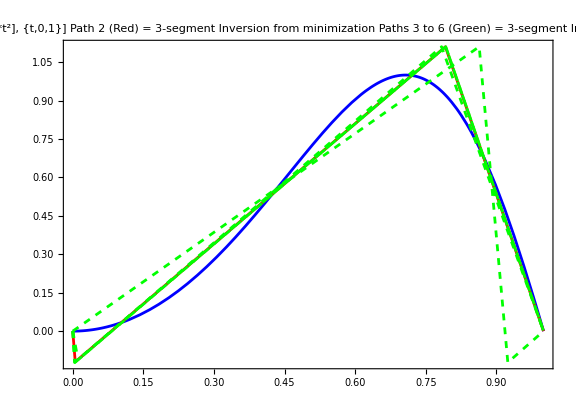

```mathematica
Show[Plot[Sin[π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2], {t,0,1}]
Path 2 (Red) = 3-segment Inversion from minimization
Paths 3 to 6 (Green) = 3-segment Inversions from dropping equations"],16]],
ListLinePlot[Prepend[ptssol4sintsq,ptsminim4sintsq],
PlotStyle->Prepend[ConstantArray[{Dashed,Green},Length[ptssol4sintsq]],{Red}]]]
```

#### Sin[2 π t^2]

```mathematica
sigsins2f2fcore=getcore6[sigsins2f2,4]
```

{{1,0},{-FresnelS[2]/2},{0,1/16 (4-√2 FresnelC[2 √2])},{-(-2+FresnelC[2])/(16 π),1/8,1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}

```mathematica
Timing[minim4sin2tsq1=minim3lines[Flatten[chen3z4core],Flatten[sigsins2f2fcore],weights3seg,vars3linechen,bounds3seg,"NelderMead"]]
```

{3.99886,{0.428694,{β_1→-5.07299,β_2→67.3617,β_3→-0.363397,t_1→0.,t_2→0.00535701,t_3→0.993037}}}

```mathematica
Timing[minim4sin2tsq2=minim3lines[Flatten[chen3z4core],Flatten[sigsins2f2fcore],weights3seg,vars3linechen,bounds3seg,"DifferentialEvolution"]]
```

{5.64897,{0.000129848,{β_1→1.78643,β_2→-13.6315,β_3→5.11406,t_1→0.600152,t_2→0.166281,t_3→0.233584}}}

```mathematica
Timing[minim4sin2tsq3=minim3lines[Flatten[chen3z4core],Flatten[sigsins2f2fcore],weights3seg,vars3linechen,bounds3seg,"SimulatedAnnealing"]]
```

{5.65222,{0.000119186,{β_1→1.78795,β_2→-14.9756,β_3→4.81735,t_1→0.603198,t_2→0.151071,t_3→0.245761}}}

```mathematica
ptsminim4sin2tsq=flistbetat[Last[minim4sin2tsq3]]
```

{{0,0},{0.603198,1.07849},{0.754269,-1.1839},{1.00003,0.0000150733}}

```mathematica
sol4sin2f2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{}

```mathematica
sol4sin2f2ex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→2.0024,β_2→-10.209,β_3→4.9044,t_1→0.55124,t_2→0.21867,t_3→0.23009}}

```mathematica
sol4sin2f2ex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→1.7897,β_2→-9.98152,β_3→6.74742,t_1→0.58653,t_2→0.2295,t_3→0.18395}}

```mathematica
sol4sin2f2ex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→1.8399,β_2→-23.925,β_3→3.9917,t_1→0.61178,t_2→0.095831,t_3→0.29239}}

```mathematica
sol4sin2f2ex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{}

```mathematica
sol4sin2f2ex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins2f2fcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→1.54076,β_2→-7.28173,β_3→18.2845,t_1→0.6106,t_2→0.31529,t_3→0.074109}}

```mathematica
ptssol4sin2tsq=Map[flistbetat,Join[sol4sin2f2ex46,sol4sin2f2ex47,sol4sin2f2ex48,sol4sin2f2ex56,sol4sin2f2ex57,sol4sin2f2ex58]]
```

{{{0,0},{0.55124,1.1038},{0.76991,-1.128},{1.,0.}},{{0,0},{0.58653,1.0497},{0.81605,-1.241},{1.,0.}},{{0,0},{0.61178,1.1256},{0.70761,-1.167},{1.,0.}},{{0,0},{0.6106,0.94079},{0.92589,-1.355},{1.,0.}}}

```mathematica
Map[flengthpathpts[flistbetat[#]]&,Join[sol4sin2f2ex46,sol4sin2f2ex47,sol4sin2f2ex48,sol4sin2f2ex56,sol4sin2f2ex57,sol4sin2f2ex58]]
```

{4.628,4.76,4.779,4.796}

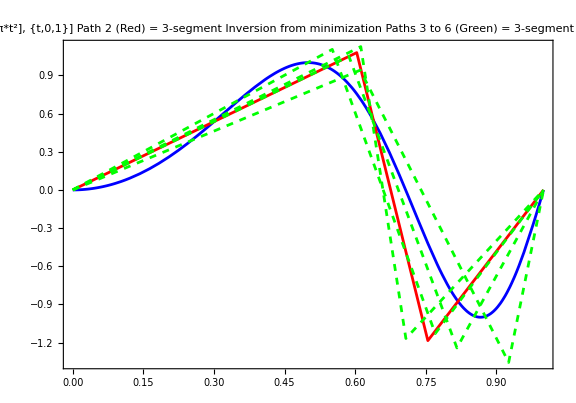

```mathematica
Show[Plot[Sin[2π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[2*π*t^2], {t,0,1}]
Path 2 (Red) = 3-segment Inversion from minimization
Paths 3 to 6 (Green) = 3-segment Inversions from dropping equations"],16]],
ListLinePlot[Prepend[ptssol4sin2tsq,ptsminim4sin2tsq],
PlotStyle->Prepend[ConstantArray[{Dashed,Green},Length[ptssol4sin2tsq]],{Red}]]]
```

#### 3 segments

```mathematica
sig3seg=chainchen[
{signat[{{t,2 t}},{0,3},4][[1]],
signat[{{t,-4 t}},{0,1},4][[1]],
signat[{{t,3 t}},{0,2},4][[1]]},
4];
```

```mathematica
sig3segcore=getcore6[sig3seg,4]
```

{{6,8},{25},{181/3,188/3},{1291/12,757/6,349/3}}

```mathematica
Timing[sol3segex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sig3segcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]]
```

{0.033063,{{β_1→2.,β_2→-4.,β_3→3.,t_1→3.,t_2→1.,t_3→2.}}}

```mathematica
Timing[sol3segex47=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sig3segcore],vars3linechen,
{{4},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]]
```

{0.043371,{{β_1→2.,β_2→-4.,β_3→3.,t_1→3.,t_2→1.,t_3→2.}}}

```mathematica
Timing[sol3segex48=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sig3segcore],vars3linechen,
{{4},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]]
```

{0.039217,{{β_1→2.,β_2→-4.,β_3→3.,t_1→3.,t_2→1.,t_3→2.}}}

```mathematica
Timing[sol3segex56=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sig3segcore],vars3linechen,
{{5},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]]
```

{0.041323,{{β_1→2.,β_2→-4.,β_3→3.,t_1→3.,t_2→1.,t_3→2.}}}

```mathematica
Timing[sol3segex57=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sig3segcore],vars3linechen,
{{5},{7}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]]
```

{0.038304,{{β_1→2.,β_2→-4.,β_3→3.,t_1→3.,t_2→1.,t_3→2.}}}

```mathematica
Timing[sol3segex58=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sig3segcore],vars3linechen,
{{5},{8}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]]
```

{0.030187,{{β_1→2.,β_2→-4.,β_3→3.,t_1→3.,t_2→1.,t_3→2.}}}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{sol3segex46,sol3segex47,sol3segex48,sol3segex56,sol3segex57,sol3segex58}]]
```

β_1→2. | β_2→-4. | β_3→3. | t_1→3. | t_2→1. | t_3→2.
β_1→2. | β_2→-4. | β_3→3. | t_1→3. | t_2→1. | t_3→2.
β_1→2. | β_2→-4. | β_3→3. | t_1→3. | t_2→1. | t_3→2.
β_1→2. | β_2→-4. | β_3→3. | t_1→3. | t_2→1. | t_3→2.
β_1→2. | β_2→-4. | β_3→3. | t_1→3. | t_2→1. | t_3→2.
β_1→2. | β_2→-4. | β_3→3. | t_1→3. | t_2→1. | t_3→2.

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistbetat,{sol3segex46,sol3segex47,sol3segex48,sol3segex56,sol3segex57,sol3segex58},{2}]]]
```

{0,0} | {3.,6.} | {4.,2.} | {6.,8.}
{0,0} | {3.,6.} | {4.,2.} | {6.,8.}
{0,0} | {3.,6.} | {4.,2.} | {6.,8.}
{0,0} | {3.,6.} | {4.,2.} | {6.,8.}
{0,0} | {3.,6.} | {4.,2.} | {6.,8.}
{0,0} | {3.,6.} | {4.,2.} | {6.,8.}

### 4+ lines

#### Definitions

```mathematica
chen4z4=chainchen[
{signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},4][[1]],
signat[{{t,Subscript[β, 2] t}},{0,Subscript[t, 2]},4][[1]],
signat[{{t,Subscript[β, 3] t}},{0,Subscript[t, 3]},4][[1]],
signat[{{t,Subscript[β, 4] t}},{0,Subscript[t, 4]},4][[1]]},
4];
```

```mathematica
chen4z4core=getcore6[chen4z4,4];
```

```mathematica
chen4z5=chainchen[
{signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},5][[1]],
signat[{{t,Subscript[β, 2] t}},{0,Subscript[t, 2]},5][[1]],
signat[{{t,Subscript[β, 3] t}},{0,Subscript[t, 3]},5][[1]],
signat[{{t,Subscript[β, 4] t}},{0,Subscript[t, 4]},5][[1]]},
5];
```

```mathematica
chen4z5core=getcore6[chen4z5,5];
```

```mathematica
chen5z5=chainchen[
{signat[{{t,Subscript[β, 1] t}},{0,Subscript[t, 1]},5][[1]],
signat[{{t,Subscript[β, 2] t}},{0,Subscript[t, 2]},5][[1]],
signat[{{t,Subscript[β, 3] t}},{0,Subscript[t, 3]},5][[1]],
signat[{{t,Subscript[β, 4] t}},{0,Subscript[t, 4]},5][[1]],
signat[{{t,Subscript[β, 5] t}},{0,Subscript[t, 5]},5][[1]]},
5];
```

```mathematica
chen5z5core=getcore6[chen5z5,5];
```

```mathematica
vars4linechen={Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[β, 4],Subscript[t, 1],Subscript[t, 2],Subscript[t, 3],Subscript[t, 4]};
```

```mathematica
vars5linechen={Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[β, 4],Subscript[β, 5],Subscript[t, 1],Subscript[t, 2],Subscript[t, 3],Subscript[t, 4],Subscript[t, 5]};
```

```mathematica
eqs4linechen234=MapThread[Equal,{
Expand[Flatten[chen4z4core]],
{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2]}}];
```

```mathematica
Grid[Map[{#}&,eqs4linechen234],Alignment->Left,Frame->All]
```

t_1+t_2+t_3+t_4==z_1
t_1 β_1+t_2 β_2+t_3 β_3+t_4 β_4==z_2
1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2+t_1 t_3 β_3+t_2 t_3 β_3+1/2 t_3^2 β_3+t_1 t_4 β_4+t_2 t_4 β_4+t_3 t_4 β_4+1/2 t_4^2 β_4==z_(1,2)
1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2+1/2 t_1^2 t_3 β_3+t_1 t_2 t_3 β_3+1/2 t_2^2 t_3 β_3+1/2 t_1 t_3^2 β_3+1/2 t_2 t_3^2 β_3+1/6 t_3^3 β_3+1/2 t_1^2 t_4 β_4+t_1 t_2 t_4 β_4+1/2 t_2^2 t_4 β_4+t_1 t_3 t_4 β_4+t_2 t_3 t_4 β_4+1/2 t_3^2 t_4 β_4+1/2 t_1 t_4^2 β_4+1/2 t_2 t_4^2 β_4+1/2 t_3 t_4^2 β_4+1/6 t_4^3 β_4==z_(1,1,2)
1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2+1/2 t_1^2 t_3 β_1 β_3+t_1 t_2 t_3 β_2 β_3+1/2 t_2^2 t_3 β_2 β_3+1/2 t_1 t_3^2 β_3^2+1/2 t_2 t_3^2 β_3^2+1/6 t_3^3 β_3^2+1/2 t_1^2 t_4 β_1 β_4+t_1 t_2 t_4 β_2 β_4+1/2 t_2^2 t_4 β_2 β_4+t_1 t_3 t_4 β_3 β_4+t_2 t_3 t_4 β_3 β_4+1/2 t_3^2 t_4 β_3 β_4+1/2 t_1 t_4^2 β_4^2+1/2 t_2 t_4^2 β_4^2+1/2 t_3 t_4^2 β_4^2+1/6 t_4^3 β_4^2==z_(1,2,2)
1/24 t_1^4 β_1+1/6 t_1^3 t_2 β_2+1/4 t_1^2 t_2^2 β_2+1/6 t_1 t_2^3 β_2+1/24 t_2^4 β_2+1/6 t_1^3 t_3 β_3+1/2 t_1^2 t_2 t_3 β_3+1/2 t_1 t_2^2 t_3 β_3+1/6 t_2^3 t_3 β_3+1/4 t_1^2 t_3^2 β_3+1/2 t_1 t_2 t_3^2 β_3+1/4 t_2^2 t_3^2 β_3+1/6 t_1 t_3^3 β_3+1/6 t_2 t_3^3 β_3+1/24 t_3^4 β_3+1/6 t_1^3 t_4 β_4+1/2 t_1^2 t_2 t_4 β_4+1/2 t_1 t_2^2 t_4 β_4+1/6 t_2^3 t_4 β_4+1/2 t_1^2 t_3 t_4 β_4+t_1 t_2 t_3 t_4 β_4+1/2 t_2^2 t_3 t_4 β_4+1/2 t_1 t_3^2 t_4 β_4+1/2 t_2 t_3^2 t_4 β_4+1/6 t_3^3 t_4 β_4+1/4 t_1^2 t_4^2 β_4+1/2 t_1 t_2 t_4^2 β_4+1/4 t_2^2 t_4^2 β_4+1/2 t_1 t_3 t_4^2 β_4+1/2 t_2 t_3 t_4^2 β_4+1/4 t_3^2 t_4^2 β_4+1/6 t_1 t_4^3 β_4+1/6 t_2 t_4^3 β_4+1/6 t_3 t_4^3 β_4+1/24 t_4^4 β_4==z_(1,1,1,2)
1/24 t_1^4 β_1^2+1/6 t_1^3 t_2 β_1 β_2+1/4 t_1^2 t_2^2 β_2^2+1/6 t_1 t_2^3 β_2^2+1/24 t_2^4 β_2^2+1/6 t_1^3 t_3 β_1 β_3+1/2 t_1^2 t_2 t_3 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2 β_3+1/6 t_2^3 t_3 β_2 β_3+1/4 t_1^2 t_3^2 β_3^2+1/2 t_1 t_2 t_3^2 β_3^2+1/4 t_2^2 t_3^2 β_3^2+1/6 t_1 t_3^3 β_3^2+1/6 t_2 t_3^3 β_3^2+1/24 t_3^4 β_3^2+1/6 t_1^3 t_4 β_1 β_4+1/2 t_1^2 t_2 t_4 β_2 β_4+1/2 t_1 t_2^2 t_4 β_2 β_4+1/6 t_2^3 t_4 β_2 β_4+1/2 t_1^2 t_3 t_4 β_3 β_4+t_1 t_2 t_3 t_4 β_3 β_4+1/2 t_2^2 t_3 t_4 β_3 β_4+1/2 t_1 t_3^2 t_4 β_3 β_4+1/2 t_2 t_3^2 t_4 β_3 β_4+1/6 t_3^3 t_4 β_3 β_4+1/4 t_1^2 t_4^2 β_4^2+1/2 t_1 t_2 t_4^2 β_4^2+1/4 t_2^2 t_4^2 β_4^2+1/2 t_1 t_3 t_4^2 β_4^2+1/2 t_2 t_3 t_4^2 β_4^2+1/4 t_3^2 t_4^2 β_4^2+1/6 t_1 t_4^3 β_4^2+1/6 t_2 t_4^3 β_4^2+1/6 t_3 t_4^3 β_4^2+1/24 t_4^4 β_4^2==z_(1,1,2,2)
1/24 t_1^4 β_1^3+1/6 t_1^3 t_2 β_1^2 β_2+1/4 t_1^2 t_2^2 β_1 β_2^2+1/6 t_1 t_2^3 β_2^3+1/24 t_2^4 β_2^3+1/6 t_1^3 t_3 β_1^2 β_3+1/2 t_1^2 t_2 t_3 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2^2 β_3+1/6 t_2^3 t_3 β_2^2 β_3+1/4 t_1^2 t_3^2 β_1 β_3^2+1/2 t_1 t_2 t_3^2 β_2 β_3^2+1/4 t_2^2 t_3^2 β_2 β_3^2+1/6 t_1 t_3^3 β_3^3+1/6 t_2 t_3^3 β_3^3+1/24 t_3^4 β_3^3+1/6 t_1^3 t_4 β_1^2 β_4+1/2 t_1^2 t_2 t_4 β_1 β_2 β_4+1/2 t_1 t_2^2 t_4 β_2^2 β_4+1/6 t_2^3 t_4 β_2^2 β_4+1/2 t_1^2 t_3 t_4 β_1 β_3 β_4+t_1 t_2 t_3 t_4 β_2 β_3 β_4+1/2 t_2^2 t_3 t_4 β_2 β_3 β_4+1/2 t_1 t_3^2 t_4 β_3^2 β_4+1/2 t_2 t_3^2 t_4 β_3^2 β_4+1/6 t_3^3 t_4 β_3^2 β_4+1/4 t_1^2 t_4^2 β_1 β_4^2+1/2 t_1 t_2 t_4^2 β_2 β_4^2+1/4 t_2^2 t_4^2 β_2 β_4^2+1/2 t_1 t_3 t_4^2 β_3 β_4^2+1/2 t_2 t_3 t_4^2 β_3 β_4^2+1/4 t_3^2 t_4^2 β_3 β_4^2+1/6 t_1 t_4^3 β_4^3+1/6 t_2 t_4^3 β_4^3+1/6 t_3 t_4^3 β_4^3+1/24 t_4^4 β_4^3==z_(1,2,2,2)

```mathematica
eqs4linechen2345=MapThread[Equal,{
Expand[Flatten[chen4z5core]],
{Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2],Subscript[z, 1,1,1,1,2],Subscript[z, 1,1,1,2,2],Subscript[z, 1,1,2,1,2],Subscript[z, 1,1,2,2,2],Subscript[z, 1,2,1,2,2],Subscript[z, 1,2,2,2,2]}}];
```

```mathematica
Grid[Map[{#}&,eqs4linechen2345],Alignment->Left,Frame->All]
```

t_1+t_2+t_3+t_4==z_1
t_1 β_1+t_2 β_2+t_3 β_3+t_4 β_4==z_2
1/2 t_1^2 β_1+t_1 t_2 β_2+1/2 t_2^2 β_2+t_1 t_3 β_3+t_2 t_3 β_3+1/2 t_3^2 β_3+t_1 t_4 β_4+t_2 t_4 β_4+t_3 t_4 β_4+1/2 t_4^2 β_4==z_(1,2)
1/6 t_1^3 β_1+1/2 t_1^2 t_2 β_2+1/2 t_1 t_2^2 β_2+1/6 t_2^3 β_2+1/2 t_1^2 t_3 β_3+t_1 t_2 t_3 β_3+1/2 t_2^2 t_3 β_3+1/2 t_1 t_3^2 β_3+1/2 t_2 t_3^2 β_3+1/6 t_3^3 β_3+1/2 t_1^2 t_4 β_4+t_1 t_2 t_4 β_4+1/2 t_2^2 t_4 β_4+t_1 t_3 t_4 β_4+t_2 t_3 t_4 β_4+1/2 t_3^2 t_4 β_4+1/2 t_1 t_4^2 β_4+1/2 t_2 t_4^2 β_4+1/2 t_3 t_4^2 β_4+1/6 t_4^3 β_4==z_(1,1,2)
1/6 t_1^3 β_1^2+1/2 t_1^2 t_2 β_1 β_2+1/2 t_1 t_2^2 β_2^2+1/6 t_2^3 β_2^2+1/2 t_1^2 t_3 β_1 β_3+t_1 t_2 t_3 β_2 β_3+1/2 t_2^2 t_3 β_2 β_3+1/2 t_1 t_3^2 β_3^2+1/2 t_2 t_3^2 β_3^2+1/6 t_3^3 β_3^2+1/2 t_1^2 t_4 β_1 β_4+t_1 t_2 t_4 β_2 β_4+1/2 t_2^2 t_4 β_2 β_4+t_1 t_3 t_4 β_3 β_4+t_2 t_3 t_4 β_3 β_4+1/2 t_3^2 t_4 β_3 β_4+1/2 t_1 t_4^2 β_4^2+1/2 t_2 t_4^2 β_4^2+1/2 t_3 t_4^2 β_4^2+1/6 t_4^3 β_4^2==z_(1,2,2)
1/24 t_1^4 β_1+1/6 t_1^3 t_2 β_2+1/4 t_1^2 t_2^2 β_2+1/6 t_1 t_2^3 β_2+1/24 t_2^4 β_2+1/6 t_1^3 t_3 β_3+1/2 t_1^2 t_2 t_3 β_3+1/2 t_1 t_2^2 t_3 β_3+1/6 t_2^3 t_3 β_3+1/4 t_1^2 t_3^2 β_3+1/2 t_1 t_2 t_3^2 β_3+1/4 t_2^2 t_3^2 β_3+1/6 t_1 t_3^3 β_3+1/6 t_2 t_3^3 β_3+1/24 t_3^4 β_3+1/6 t_1^3 t_4 β_4+1/2 t_1^2 t_2 t_4 β_4+1/2 t_1 t_2^2 t_4 β_4+1/6 t_2^3 t_4 β_4+1/2 t_1^2 t_3 t_4 β_4+t_1 t_2 t_3 t_4 β_4+1/2 t_2^2 t_3 t_4 β_4+1/2 t_1 t_3^2 t_4 β_4+1/2 t_2 t_3^2 t_4 β_4+1/6 t_3^3 t_4 β_4+1/4 t_1^2 t_4^2 β_4+1/2 t_1 t_2 t_4^2 β_4+1/4 t_2^2 t_4^2 β_4+1/2 t_1 t_3 t_4^2 β_4+1/2 t_2 t_3 t_4^2 β_4+1/4 t_3^2 t_4^2 β_4+1/6 t_1 t_4^3 β_4+1/6 t_2 t_4^3 β_4+1/6 t_3 t_4^3 β_4+1/24 t_4^4 β_4==z_(1,1,1,2)
1/24 t_1^4 β_1^2+1/6 t_1^3 t_2 β_1 β_2+1/4 t_1^2 t_2^2 β_2^2+1/6 t_1 t_2^3 β_2^2+1/24 t_2^4 β_2^2+1/6 t_1^3 t_3 β_1 β_3+1/2 t_1^2 t_2 t_3 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2 β_3+1/6 t_2^3 t_3 β_2 β_3+1/4 t_1^2 t_3^2 β_3^2+1/2 t_1 t_2 t_3^2 β_3^2+1/4 t_2^2 t_3^2 β_3^2+1/6 t_1 t_3^3 β_3^2+1/6 t_2 t_3^3 β_3^2+1/24 t_3^4 β_3^2+1/6 t_1^3 t_4 β_1 β_4+1/2 t_1^2 t_2 t_4 β_2 β_4+1/2 t_1 t_2^2 t_4 β_2 β_4+1/6 t_2^3 t_4 β_2 β_4+1/2 t_1^2 t_3 t_4 β_3 β_4+t_1 t_2 t_3 t_4 β_3 β_4+1/2 t_2^2 t_3 t_4 β_3 β_4+1/2 t_1 t_3^2 t_4 β_3 β_4+1/2 t_2 t_3^2 t_4 β_3 β_4+1/6 t_3^3 t_4 β_3 β_4+1/4 t_1^2 t_4^2 β_4^2+1/2 t_1 t_2 t_4^2 β_4^2+1/4 t_2^2 t_4^2 β_4^2+1/2 t_1 t_3 t_4^2 β_4^2+1/2 t_2 t_3 t_4^2 β_4^2+1/4 t_3^2 t_4^2 β_4^2+1/6 t_1 t_4^3 β_4^2+1/6 t_2 t_4^3 β_4^2+1/6 t_3 t_4^3 β_4^2+1/24 t_4^4 β_4^2==z_(1,1,2,2)
1/24 t_1^4 β_1^3+1/6 t_1^3 t_2 β_1^2 β_2+1/4 t_1^2 t_2^2 β_1 β_2^2+1/6 t_1 t_2^3 β_2^3+1/24 t_2^4 β_2^3+1/6 t_1^3 t_3 β_1^2 β_3+1/2 t_1^2 t_2 t_3 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 β_2^2 β_3+1/6 t_2^3 t_3 β_2^2 β_3+1/4 t_1^2 t_3^2 β_1 β_3^2+1/2 t_1 t_2 t_3^2 β_2 β_3^2+1/4 t_2^2 t_3^2 β_2 β_3^2+1/6 t_1 t_3^3 β_3^3+1/6 t_2 t_3^3 β_3^3+1/24 t_3^4 β_3^3+1/6 t_1^3 t_4 β_1^2 β_4+1/2 t_1^2 t_2 t_4 β_1 β_2 β_4+1/2 t_1 t_2^2 t_4 β_2^2 β_4+1/6 t_2^3 t_4 β_2^2 β_4+1/2 t_1^2 t_3 t_4 β_1 β_3 β_4+t_1 t_2 t_3 t_4 β_2 β_3 β_4+1/2 t_2^2 t_3 t_4 β_2 β_3 β_4+1/2 t_1 t_3^2 t_4 β_3^2 β_4+1/2 t_2 t_3^2 t_4 β_3^2 β_4+1/6 t_3^3 t_4 β_3^2 β_4+1/4 t_1^2 t_4^2 β_1 β_4^2+1/2 t_1 t_2 t_4^2 β_2 β_4^2+1/4 t_2^2 t_4^2 β_2 β_4^2+1/2 t_1 t_3 t_4^2 β_3 β_4^2+1/2 t_2 t_3 t_4^2 β_3 β_4^2+1/4 t_3^2 t_4^2 β_3 β_4^2+1/6 t_1 t_4^3 β_4^3+1/6 t_2 t_4^3 β_4^3+1/6 t_3 t_4^3 β_4^3+1/24 t_4^4 β_4^3==z_(1,2,2,2)
1/120 t_1^5 β_1+1/24 t_1^4 t_2 β_2+1/12 t_1^3 t_2^2 β_2+1/12 t_1^2 t_2^3 β_2+1/24 t_1 t_2^4 β_2+1/120 t_2^5 β_2+1/24 t_1^4 t_3 β_3+1/6 t_1^3 t_2 t_3 β_3+1/4 t_1^2 t_2^2 t_3 β_3+1/6 t_1 t_2^3 t_3 β_3+1/24 t_2^4 t_3 β_3+1/12 t_1^3 t_3^2 β_3+1/4 t_1^2 t_2 t_3^2 β_3+1/4 t_1 t_2^2 t_3^2 β_3+1/12 t_2^3 t_3^2 β_3+1/12 t_1^2 t_3^3 β_3+1/6 t_1 t_2 t_3^3 β_3+1/12 t_2^2 t_3^3 β_3+1/24 t_1 t_3^4 β_3+1/24 t_2 t_3^4 β_3+1/120 t_3^5 β_3+1/24 t_1^4 t_4 β_4+1/6 t_1^3 t_2 t_4 β_4+1/4 t_1^2 t_2^2 t_4 β_4+1/6 t_1 t_2^3 t_4 β_4+1/24 t_2^4 t_4 β_4+1/6 t_1^3 t_3 t_4 β_4+1/2 t_1^2 t_2 t_3 t_4 β_4+1/2 t_1 t_2^2 t_3 t_4 β_4+1/6 t_2^3 t_3 t_4 β_4+1/4 t_1^2 t_3^2 t_4 β_4+1/2 t_1 t_2 t_3^2 t_4 β_4+1/4 t_2^2 t_3^2 t_4 β_4+1/6 t_1 t_3^3 t_4 β_4+1/6 t_2 t_3^3 t_4 β_4+1/24 t_3^4 t_4 β_4+1/12 t_1^3 t_4^2 β_4+1/4 t_1^2 t_2 t_4^2 β_4+1/4 t_1 t_2^2 t_4^2 β_4+1/12 t_2^3 t_4^2 β_4+1/4 t_1^2 t_3 t_4^2 β_4+1/2 t_1 t_2 t_3 t_4^2 β_4+1/4 t_2^2 t_3 t_4^2 β_4+1/4 t_1 t_3^2 t_4^2 β_4+1/4 t_2 t_3^2 t_4^2 β_4+1/12 t_3^3 t_4^2 β_4+1/12 t_1^2 t_4^3 β_4+1/6 t_1 t_2 t_4^3 β_4+1/12 t_2^2 t_4^3 β_4+1/6 t_1 t_3 t_4^3 β_4+1/6 t_2 t_3 t_4^3 β_4+1/12 t_3^2 t_4^3 β_4+1/24 t_1 t_4^4 β_4+1/24 t_2 t_4^4 β_4+1/24 t_3 t_4^4 β_4+1/120 t_4^5 β_4==z_(1,1,1,1,2)
1/120 t_1^5 β_1^2+1/24 t_1^4 t_2 β_1 β_2+1/12 t_1^3 t_2^2 β_2^2+1/12 t_1^2 t_2^3 β_2^2+1/24 t_1 t_2^4 β_2^2+1/120 t_2^5 β_2^2+1/24 t_1^4 t_3 β_1 β_3+1/6 t_1^3 t_2 t_3 β_2 β_3+1/4 t_1^2 t_2^2 t_3 β_2 β_3+1/6 t_1 t_2^3 t_3 β_2 β_3+1/24 t_2^4 t_3 β_2 β_3+1/12 t_1^3 t_3^2 β_3^2+1/4 t_1^2 t_2 t_3^2 β_3^2+1/4 t_1 t_2^2 t_3^2 β_3^2+1/12 t_2^3 t_3^2 β_3^2+1/12 t_1^2 t_3^3 β_3^2+1/6 t_1 t_2 t_3^3 β_3^2+1/12 t_2^2 t_3^3 β_3^2+1/24 t_1 t_3^4 β_3^2+1/24 t_2 t_3^4 β_3^2+1/120 t_3^5 β_3^2+1/24 t_1^4 t_4 β_1 β_4+1/6 t_1^3 t_2 t_4 β_2 β_4+1/4 t_1^2 t_2^2 t_4 β_2 β_4+1/6 t_1 t_2^3 t_4 β_2 β_4+1/24 t_2^4 t_4 β_2 β_4+1/6 t_1^3 t_3 t_4 β_3 β_4+1/2 t_1^2 t_2 t_3 t_4 β_3 β_4+1/2 t_1 t_2^2 t_3 t_4 β_3 β_4+1/6 t_2^3 t_3 t_4 β_3 β_4+1/4 t_1^2 t_3^2 t_4 β_3 β_4+1/2 t_1 t_2 t_3^2 t_4 β_3 β_4+1/4 t_2^2 t_3^2 t_4 β_3 β_4+1/6 t_1 t_3^3 t_4 β_3 β_4+1/6 t_2 t_3^3 t_4 β_3 β_4+1/24 t_3^4 t_4 β_3 β_4+1/12 t_1^3 t_4^2 β_4^2+1/4 t_1^2 t_2 t_4^2 β_4^2+1/4 t_1 t_2^2 t_4^2 β_4^2+1/12 t_2^3 t_4^2 β_4^2+1/4 t_1^2 t_3 t_4^2 β_4^2+1/2 t_1 t_2 t_3 t_4^2 β_4^2+1/4 t_2^2 t_3 t_4^2 β_4^2+1/4 t_1 t_3^2 t_4^2 β_4^2+1/4 t_2 t_3^2 t_4^2 β_4^2+1/12 t_3^3 t_4^2 β_4^2+1/12 t_1^2 t_4^3 β_4^2+1/6 t_1 t_2 t_4^3 β_4^2+1/12 t_2^2 t_4^3 β_4^2+1/6 t_1 t_3 t_4^3 β_4^2+1/6 t_2 t_3 t_4^3 β_4^2+1/12 t_3^2 t_4^3 β_4^2+1/24 t_1 t_4^4 β_4^2+1/24 t_2 t_4^4 β_4^2+1/24 t_3 t_4^4 β_4^2+1/120 t_4^5 β_4^2==z_(1,1,1,2,2)
1/120 t_1^5 β_1^2+1/24 t_1^4 t_2 β_1 β_2+1/12 t_1^3 t_2^2 β_1 β_2+1/12 t_1^2 t_2^3 β_2^2+1/24 t_1 t_2^4 β_2^2+1/120 t_2^5 β_2^2+1/24 t_1^4 t_3 β_1 β_3+1/6 t_1^3 t_2 t_3 β_1 β_3+1/12 t_1^3 t_3^2 β_1 β_3+1/4 t_1^2 t_2^2 t_3 β_2 β_3+1/6 t_1 t_2^3 t_3 β_2 β_3+1/24 t_2^4 t_3 β_2 β_3+1/4 t_1^2 t_2 t_3^2 β_2 β_3+1/4 t_1 t_2^2 t_3^2 β_2 β_3+1/12 t_2^3 t_3^2 β_2 β_3+1/12 t_1^2 t_3^3 β_3^2+1/6 t_1 t_2 t_3^3 β_3^2+1/12 t_2^2 t_3^3 β_3^2+1/24 t_1 t_3^4 β_3^2+1/24 t_2 t_3^4 β_3^2+1/120 t_3^5 β_3^2+1/24 t_1^4 t_4 β_1 β_4+1/6 t_1^3 t_2 t_4 β_1 β_4+1/6 t_1^3 t_3 t_4 β_1 β_4+1/12 t_1^3 t_4^2 β_1 β_4+1/4 t_1^2 t_2^2 t_4 β_2 β_4+1/6 t_1 t_2^3 t_4 β_2 β_4+1/24 t_2^4 t_4 β_2 β_4+1/2 t_1^2 t_2 t_3 t_4 β_2 β_4+1/2 t_1 t_2^2 t_3 t_4 β_2 β_4+1/6 t_2^3 t_3 t_4 β_2 β_4+1/4 t_1^2 t_2 t_4^2 β_2 β_4+1/4 t_1 t_2^2 t_4^2 β_2 β_4+1/12 t_2^3 t_4^2 β_2 β_4+1/4 t_1^2 t_3^2 t_4 β_3 β_4+1/2 t_1 t_2 t_3^2 t_4 β_3 β_4+1/4 t_2^2 t_3^2 t_4 β_3 β_4+1/6 t_1 t_3^3 t_4 β_3 β_4+1/6 t_2 t_3^3 t_4 β_3 β_4+1/24 t_3^4 t_4 β_3 β_4+1/4 t_1^2 t_3 t_4^2 β_3 β_4+1/2 t_1 t_2 t_3 t_4^2 β_3 β_4+1/4 t_2^2 t_3 t_4^2 β_3 β_4+1/4 t_1 t_3^2 t_4^2 β_3 β_4+1/4 t_2 t_3^2 t_4^2 β_3 β_4+1/12 t_3^3 t_4^2 β_3 β_4+1/12 t_1^2 t_4^3 β_4^2+1/6 t_1 t_2 t_4^3 β_4^2+1/12 t_2^2 t_4^3 β_4^2+1/6 t_1 t_3 t_4^3 β_4^2+1/6 t_2 t_3 t_4^3 β_4^2+1/12 t_3^2 t_4^3 β_4^2+1/24 t_1 t_4^4 β_4^2+1/24 t_2 t_4^4 β_4^2+1/24 t_3 t_4^4 β_4^2+1/120 t_4^5 β_4^2==z_(1,1,2,1,2)
1/120 t_1^5 β_1^3+1/24 t_1^4 t_2 β_1^2 β_2+1/12 t_1^3 t_2^2 β_1 β_2^2+1/12 t_1^2 t_2^3 β_2^3+1/24 t_1 t_2^4 β_2^3+1/120 t_2^5 β_2^3+1/24 t_1^4 t_3 β_1^2 β_3+1/6 t_1^3 t_2 t_3 β_1 β_2 β_3+1/4 t_1^2 t_2^2 t_3 β_2^2 β_3+1/6 t_1 t_2^3 t_3 β_2^2 β_3+1/24 t_2^4 t_3 β_2^2 β_3+1/12 t_1^3 t_3^2 β_1 β_3^2+1/4 t_1^2 t_2 t_3^2 β_2 β_3^2+1/4 t_1 t_2^2 t_3^2 β_2 β_3^2+1/12 t_2^3 t_3^2 β_2 β_3^2+1/12 t_1^2 t_3^3 β_3^3+1/6 t_1 t_2 t_3^3 β_3^3+1/12 t_2^2 t_3^3 β_3^3+1/24 t_1 t_3^4 β_3^3+1/24 t_2 t_3^4 β_3^3+1/120 t_3^5 β_3^3+1/24 t_1^4 t_4 β_1^2 β_4+1/6 t_1^3 t_2 t_4 β_1 β_2 β_4+1/4 t_1^2 t_2^2 t_4 β_2^2 β_4+1/6 t_1 t_2^3 t_4 β_2^2 β_4+1/24 t_2^4 t_4 β_2^2 β_4+1/6 t_1^3 t_3 t_4 β_1 β_3 β_4+1/2 t_1^2 t_2 t_3 t_4 β_2 β_3 β_4+1/2 t_1 t_2^2 t_3 t_4 β_2 β_3 β_4+1/6 t_2^3 t_3 t_4 β_2 β_3 β_4+1/4 t_1^2 t_3^2 t_4 β_3^2 β_4+1/2 t_1 t_2 t_3^2 t_4 β_3^2 β_4+1/4 t_2^2 t_3^2 t_4 β_3^2 β_4+1/6 t_1 t_3^3 t_4 β_3^2 β_4+1/6 t_2 t_3^3 t_4 β_3^2 β_4+1/24 t_3^4 t_4 β_3^2 β_4+1/12 t_1^3 t_4^2 β_1 β_4^2+1/4 t_1^2 t_2 t_4^2 β_2 β_4^2+1/4 t_1 t_2^2 t_4^2 β_2 β_4^2+1/12 t_2^3 t_4^2 β_2 β_4^2+1/4 t_1^2 t_3 t_4^2 β_3 β_4^2+1/2 t_1 t_2 t_3 t_4^2 β_3 β_4^2+1/4 t_2^2 t_3 t_4^2 β_3 β_4^2+1/4 t_1 t_3^2 t_4^2 β_3 β_4^2+1/4 t_2 t_3^2 t_4^2 β_3 β_4^2+1/12 t_3^3 t_4^2 β_3 β_4^2+1/12 t_1^2 t_4^3 β_4^3+1/6 t_1 t_2 t_4^3 β_4^3+1/12 t_2^2 t_4^3 β_4^3+1/6 t_1 t_3 t_4^3 β_4^3+1/6 t_2 t_3 t_4^3 β_4^3+1/12 t_3^2 t_4^3 β_4^3+1/24 t_1 t_4^4 β_4^3+1/24 t_2 t_4^4 β_4^3+1/24 t_3 t_4^4 β_4^3+1/120 t_4^5 β_4^3==z_(1,1,2,2,2)
1/120 t_1^5 β_1^3+1/24 t_1^4 t_2 β_1^2 β_2+1/12 t_1^3 t_2^2 β_1 β_2^2+1/12 t_1^2 t_2^3 β_1 β_2^2+1/24 t_1 t_2^4 β_2^3+1/120 t_2^5 β_2^3+1/24 t_1^4 t_3 β_1^2 β_3+1/6 t_1^3 t_2 t_3 β_1 β_2 β_3+1/4 t_1^2 t_2^2 t_3 β_1 β_2 β_3+1/6 t_1 t_2^3 t_3 β_2^2 β_3+1/24 t_2^4 t_3 β_2^2 β_3+1/12 t_1^3 t_3^2 β_1 β_3^2+1/4 t_1^2 t_2 t_3^2 β_1 β_3^2+1/12 t_1^2 t_3^3 β_1 β_3^2+1/4 t_1 t_2^2 t_3^2 β_2 β_3^2+1/12 t_2^3 t_3^2 β_2 β_3^2+1/6 t_1 t_2 t_3^3 β_2 β_3^2+1/12 t_2^2 t_3^3 β_2 β_3^2+1/24 t_1 t_3^4 β_3^3+1/24 t_2 t_3^4 β_3^3+1/120 t_3^5 β_3^3+1/24 t_1^4 t_4 β_1^2 β_4+1/6 t_1^3 t_2 t_4 β_1 β_2 β_4+1/4 t_1^2 t_2^2 t_4 β_1 β_2 β_4+1/6 t_1 t_2^3 t_4 β_2^2 β_4+1/24 t_2^4 t_4 β_2^2 β_4+1/6 t_1^3 t_3 t_4 β_1 β_3 β_4+1/2 t_1^2 t_2 t_3 t_4 β_1 β_3 β_4+1/4 t_1^2 t_3^2 t_4 β_1 β_3 β_4+1/2 t_1 t_2^2 t_3 t_4 β_2 β_3 β_4+1/6 t_2^3 t_3 t_4 β_2 β_3 β_4+1/2 t_1 t_2 t_3^2 t_4 β_2 β_3 β_4+1/4 t_2^2 t_3^2 t_4 β_2 β_3 β_4+1/6 t_1 t_3^3 t_4 β_3^2 β_4+1/6 t_2 t_3^3 t_4 β_3^2 β_4+1/24 t_3^4 t_4 β_3^2 β_4+1/12 t_1^3 t_4^2 β_1 β_4^2+1/4 t_1^2 t_2 t_4^2 β_1 β_4^2+1/4 t_1^2 t_3 t_4^2 β_1 β_4^2+1/12 t_1^2 t_4^3 β_1 β_4^2+1/4 t_1 t_2^2 t_4^2 β_2 β_4^2+1/12 t_2^3 t_4^2 β_2 β_4^2+1/2 t_1 t_2 t_3 t_4^2 β_2 β_4^2+1/4 t_2^2 t_3 t_4^2 β_2 β_4^2+1/6 t_1 t_2 t_4^3 β_2 β_4^2+1/12 t_2^2 t_4^3 β_2 β_4^2+1/4 t_1 t_3^2 t_4^2 β_3 β_4^2+1/4 t_2 t_3^2 t_4^2 β_3 β_4^2+1/12 t_3^3 t_4^2 β_3 β_4^2+1/6 t_1 t_3 t_4^3 β_3 β_4^2+1/6 t_2 t_3 t_4^3 β_3 β_4^2+1/12 t_3^2 t_4^3 β_3 β_4^2+1/24 t_1 t_4^4 β_4^3+1/24 t_2 t_4^4 β_4^3+1/24 t_3 t_4^4 β_4^3+1/120 t_4^5 β_4^3==z_(1,2,1,2,2)
1/120 t_1^5 β_1^4+1/24 t_1^4 t_2 β_1^3 β_2+1/12 t_1^3 t_2^2 β_1^2 β_2^2+1/12 t_1^2 t_2^3 β_1 β_2^3+1/24 t_1 t_2^4 β_2^4+1/120 t_2^5 β_2^4+1/24 t_1^4 t_3 β_1^3 β_3+1/6 t_1^3 t_2 t_3 β_1^2 β_2 β_3+1/4 t_1^2 t_2^2 t_3 β_1 β_2^2 β_3+1/6 t_1 t_2^3 t_3 β_2^3 β_3+1/24 t_2^4 t_3 β_2^3 β_3+1/12 t_1^3 t_3^2 β_1^2 β_3^2+1/4 t_1^2 t_2 t_3^2 β_1 β_2 β_3^2+1/4 t_1 t_2^2 t_3^2 β_2^2 β_3^2+1/12 t_2^3 t_3^2 β_2^2 β_3^2+1/12 t_1^2 t_3^3 β_1 β_3^3+1/6 t_1 t_2 t_3^3 β_2 β_3^3+1/12 t_2^2 t_3^3 β_2 β_3^3+1/24 t_1 t_3^4 β_3^4+1/24 t_2 t_3^4 β_3^4+1/120 t_3^5 β_3^4+1/24 t_1^4 t_4 β_1^3 β_4+1/6 t_1^3 t_2 t_4 β_1^2 β_2 β_4+1/4 t_1^2 t_2^2 t_4 β_1 β_2^2 β_4+1/6 t_1 t_2^3 t_4 β_2^3 β_4+1/24 t_2^4 t_4 β_2^3 β_4+1/6 t_1^3 t_3 t_4 β_1^2 β_3 β_4+1/2 t_1^2 t_2 t_3 t_4 β_1 β_2 β_3 β_4+1/2 t_1 t_2^2 t_3 t_4 β_2^2 β_3 β_4+1/6 t_2^3 t_3 t_4 β_2^2 β_3 β_4+1/4 t_1^2 t_3^2 t_4 β_1 β_3^2 β_4+1/2 t_1 t_2 t_3^2 t_4 β_2 β_3^2 β_4+1/4 t_2^2 t_3^2 t_4 β_2 β_3^2 β_4+1/6 t_1 t_3^3 t_4 β_3^3 β_4+1/6 t_2 t_3^3 t_4 β_3^3 β_4+1/24 t_3^4 t_4 β_3^3 β_4+1/12 t_1^3 t_4^2 β_1^2 β_4^2+1/4 t_1^2 t_2 t_4^2 β_1 β_2 β_4^2+1/4 t_1 t_2^2 t_4^2 β_2^2 β_4^2+1/12 t_2^3 t_4^2 β_2^2 β_4^2+1/4 t_1^2 t_3 t_4^2 β_1 β_3 β_4^2+1/2 t_1 t_2 t_3 t_4^2 β_2 β_3 β_4^2+1/4 t_2^2 t_3 t_4^2 β_2 β_3 β_4^2+1/4 t_1 t_3^2 t_4^2 β_3^2 β_4^2+1/4 t_2 t_3^2 t_4^2 β_3^2 β_4^2+1/12 t_3^3 t_4^2 β_3^2 β_4^2+1/12 t_1^2 t_4^3 β_1 β_4^3+1/6 t_1 t_2 t_4^3 β_2 β_4^3+1/12 t_2^2 t_4^3 β_2 β_4^3+1/6 t_1 t_3 t_4^3 β_3 β_4^3+1/6 t_2 t_3 t_4^3 β_3 β_4^3+1/12 t_3^2 t_4^3 β_3 β_4^3+1/24 t_1 t_4^4 β_4^4+1/24 t_2 t_4^4 β_4^4+1/24 t_3 t_4^4 β_4^4+1/120 t_4^5 β_4^4==z_(1,2,2,2,2)

```mathematica
rulesnosubs4={Subscript[β, 1]->β1,Subscript[β, 2]->β2,Subscript[β, 3]->β3,Subscript[β, 4]->β4,Subscript[t, 1]->t1,Subscript[t, 2]->t2,Subscript[t, 3]->t3,Subscript[t, 4]->t4};
```

```mathematica
rulestosubs4={β1->Subscript[β, 1],β2->Subscript[β, 2],β3->Subscript[β, 3],β4->Subscript[β, 4],t1->Subscript[t, 1],t2->Subscript[t, 2],t3->Subscript[t, 3],t4->Subscript[t, 4]};
```

```mathematica
rulessubs4x={β1->x[1],β2->x[3],β3->x[5],β4->x[7],t1->x[0],t2->x[2],t3->x[4],t4->x[6]};
```

```mathematica
f4l4=Map[Apply[Plus,#]&,Transpose[{
Expand[Flatten[chen4z4core]],
-{z1,z2,z12,z112,z122,z1112,z1122,z1222}}]]//.rulesnosubs4;
```

```mathematica
f4l4
```

{t1+t2+t3+t4-z1,-z2+t1 β1+t2 β2+t3 β3+t4 β4,-z12+(t1^2 β1)/2+t1 t2 β2+(t2^2 β2)/2+t1 t3 β3+t2 t3 β3+(t3^2 β3)/2+t1 t4 β4+t2 t4 β4+t3 t4 β4+(t4^2 β4)/2,-z112+(t1^3 β1)/6+1/2 t1^2 t2 β2+1/2 t1 t2^2 β2+(t2^3 β2)/6+1/2 t1^2 t3 β3+t1 t2 t3 β3+1/2 t2^2 t3 β3+1/2 t1 t3^2 β3+1/2 t2 t3^2 β3+(t3^3 β3)/6+1/2 t1^2 t4 β4+t1 t2 t4 β4+1/2 t2^2 t4 β4+t1 t3 t4 β4+t2 t3 t4 β4+1/2 t3^2 t4 β4+1/2 t1 t4^2 β4+1/2 t2 t4^2 β4+1/2 t3 t4^2 β4+(t4^3 β4)/6,-z122+(t1^3 β1^2)/6+1/2 t1^2 t2 β1 β2+1/2 t1 t2^2 β2^2+(t2^3 β2^2)/6+1/2 t1^2 t3 β1 β3+t1 t2 t3 β2 β3+1/2 t2^2 t3 β2 β3+1/2 t1 t3^2 β3^2+1/2 t2 t3^2 β3^2+(t3^3 β3^2)/6+1/2 t1^2 t4 β1 β4+t1 t2 t4 β2 β4+1/2 t2^2 t4 β2 β4+t1 t3 t4 β3 β4+t2 t3 t4 β3 β4+1/2 t3^2 t4 β3 β4+1/2 t1 t4^2 β4^2+1/2 t2 t4^2 β4^2+1/2 t3 t4^2 β4^2+(t4^3 β4^2)/6,-z1112+(t1^4 β1)/24+1/6 t1^3 t2 β2+1/4 t1^2 t2^2 β2+1/6 t1 t2^3 β2+(t2^4 β2)/24+1/6 t1^3 t3 β3+1/2 t1^2 t2 t3 β3+1/2 t1 t2^2 t3 β3+1/6 t2^3 t3 β3+1/4 t1^2 t3^2 β3+1/2 t1 t2 t3^2 β3+1/4 t2^2 t3^2 β3+1/6 t1 t3^3 β3+1/6 t2 t3^3 β3+(t3^4 β3)/24+1/6 t1^3 t4 β4+1/2 t1^2 t2 t4 β4+1/2 t1 t2^2 t4 β4+1/6 t2^3 t4 β4+1/2 t1^2 t3 t4 β4+t1 t2 t3 t4 β4+1/2 t2^2 t3 t4 β4+1/2 t1 t3^2 t4 β4+1/2 t2 t3^2 t4 β4+1/6 t3^3 t4 β4+1/4 t1^2 t4^2 β4+1/2 t1 t2 t4^2 β4+1/4 t2^2 t4^2 β4+1/2 t1 t3 t4^2 β4+1/2 t2 t3 t4^2 β4+1/4 t3^2 t4^2 β4+1/6 t1 t4^3 β4+1/6 t2 t4^3 β4+1/6 t3 t4^3 β4+(t4^4 β4)/24,-z1122+(t1^4 β1^2)/24+1/6 t1^3 t2 β1 β2+1/4 t1^2 t2^2 β2^2+1/6 t1 t2^3 β2^2+(t2^4 β2^2)/24+1/6 t1^3 t3 β1 β3+1/2 t1^2 t2 t3 β2 β3+1/2 t1 t2^2 t3 β2 β3+1/6 t2^3 t3 β2 β3+1/4 t1^2 t3^2 β3^2+1/2 t1 t2 t3^2 β3^2+1/4 t2^2 t3^2 β3^2+1/6 t1 t3^3 β3^2+1/6 t2 t3^3 β3^2+(t3^4 β3^2)/24+1/6 t1^3 t4 β1 β4+1/2 t1^2 t2 t4 β2 β4+1/2 t1 t2^2 t4 β2 β4+1/6 t2^3 t4 β2 β4+1/2 t1^2 t3 t4 β3 β4+t1 t2 t3 t4 β3 β4+1/2 t2^2 t3 t4 β3 β4+1/2 t1 t3^2 t4 β3 β4+1/2 t2 t3^2 t4 β3 β4+1/6 t3^3 t4 β3 β4+1/4 t1^2 t4^2 β4^2+1/2 t1 t2 t4^2 β4^2+1/4 t2^2 t4^2 β4^2+1/2 t1 t3 t4^2 β4^2+1/2 t2 t3 t4^2 β4^2+1/4 t3^2 t4^2 β4^2+1/6 t1 t4^3 β4^2+1/6 t2 t4^3 β4^2+1/6 t3 t4^3 β4^2+(t4^4 β4^2)/24,-z1222+(t1^4 β1^3)/24+1/6 t1^3 t2 β1^2 β2+1/4 t1^2 t2^2 β1 β2^2+1/6 t1 t2^3 β2^3+(t2^4 β2^3)/24+1/6 t1^3 t3 β1^2 β3+1/2 t1^2 t2 t3 β1 β2 β3+1/2 t1 t2^2 t3 β2^2 β3+1/6 t2^3 t3 β2^2 β3+1/4 t1^2 t3^2 β1 β3^2+1/2 t1 t2 t3^2 β2 β3^2+1/4 t2^2 t3^2 β2 β3^2+1/6 t1 t3^3 β3^3+1/6 t2 t3^3 β3^3+(t3^4 β3^3)/24+1/6 t1^3 t4 β1^2 β4+1/2 t1^2 t2 t4 β1 β2 β4+1/2 t1 t2^2 t4 β2^2 β4+1/6 t2^3 t4 β2^2 β4+1/2 t1^2 t3 t4 β1 β3 β4+t1 t2 t3 t4 β2 β3 β4+1/2 t2^2 t3 t4 β2 β3 β4+1/2 t1 t3^2 t4 β3^2 β4+1/2 t2 t3^2 t4 β3^2 β4+1/6 t3^3 t4 β3^2 β4+1/4 t1^2 t4^2 β1 β4^2+1/2 t1 t2 t4^2 β2 β4^2+1/4 t2^2 t4^2 β2 β4^2+1/2 t1 t3 t4^2 β3 β4^2+1/2 t2 t3 t4^2 β3 β4^2+1/4 t3^2 t4^2 β3 β4^2+1/6 t1 t4^3 β4^3+1/6 t2 t4^3 β4^3+1/6 t3 t4^3 β4^3+(t4^4 β4^3)/24}

```mathematica
f4l5=Map[Apply[Plus,#]&,Transpose[{
Expand[Flatten[chen4z5core]],
-{z1,z2,z12,z112,z122,z1112,z1122,z1222,z11112,z11122,z11212,z11222,z12122,z12222}}]]//.rulesnosubs4;
```

```mathematica
f4l5
```

{t1+t2+t3+t4-z1,-z2+t1 β1+t2 β2+t3 β3+t4 β4,-z12+(t1^2 β1)/2+t1 t2 β2+(t2^2 β2)/2+t1 t3 β3+t2 t3 β3+(t3^2 β3)/2+t1 t4 β4+t2 t4 β4+t3 t4 β4+(t4^2 β4)/2,-z112+(t1^3 β1)/6+1/2 t1^2 t2 β2+1/2 t1 t2^2 β2+(t2^3 β2)/6+1/2 t1^2 t3 β3+t1 t2 t3 β3+1/2 t2^2 t3 β3+1/2 t1 t3^2 β3+1/2 t2 t3^2 β3+(t3^3 β3)/6+1/2 t1^2 t4 β4+t1 t2 t4 β4+1/2 t2^2 t4 β4+t1 t3 t4 β4+t2 t3 t4 β4+1/2 t3^2 t4 β4+1/2 t1 t4^2 β4+1/2 t2 t4^2 β4+1/2 t3 t4^2 β4+(t4^3 β4)/6,-z122+(t1^3 β1^2)/6+1/2 t1^2 t2 β1 β2+1/2 t1 t2^2 β2^2+(t2^3 β2^2)/6+1/2 t1^2 t3 β1 β3+t1 t2 t3 β2 β3+1/2 t2^2 t3 β2 β3+1/2 t1 t3^2 β3^2+1/2 t2 t3^2 β3^2+(t3^3 β3^2)/6+1/2 t1^2 t4 β1 β4+t1 t2 t4 β2 β4+1/2 t2^2 t4 β2 β4+t1 t3 t4 β3 β4+t2 t3 t4 β3 β4+1/2 t3^2 t4 β3 β4+1/2 t1 t4^2 β4^2+1/2 t2 t4^2 β4^2+1/2 t3 t4^2 β4^2+(t4^3 β4^2)/6,-z1112+(t1^4 β1)/24+1/6 t1^3 t2 β2+1/4 t1^2 t2^2 β2+1/6 t1 t2^3 β2+(t2^4 β2)/24+1/6 t1^3 t3 β3+1/2 t1^2 t2 t3 β3+1/2 t1 t2^2 t3 β3+1/6 t2^3 t3 β3+1/4 t1^2 t3^2 β3+1/2 t1 t2 t3^2 β3+1/4 t2^2 t3^2 β3+1/6 t1 t3^3 β3+1/6 t2 t3^3 β3+(t3^4 β3)/24+1/6 t1^3 t4 β4+1/2 t1^2 t2 t4 β4+1/2 t1 t2^2 t4 β4+1/6 t2^3 t4 β4+1/2 t1^2 t3 t4 β4+t1 t2 t3 t4 β4+1/2 t2^2 t3 t4 β4+1/2 t1 t3^2 t4 β4+1/2 t2 t3^2 t4 β4+1/6 t3^3 t4 β4+1/4 t1^2 t4^2 β4+1/2 t1 t2 t4^2 β4+1/4 t2^2 t4^2 β4+1/2 t1 t3 t4^2 β4+1/2 t2 t3 t4^2 β4+1/4 t3^2 t4^2 β4+1/6 t1 t4^3 β4+1/6 t2 t4^3 β4+1/6 t3 t4^3 β4+(t4^4 β4)/24,-z1122+(t1^4 β1^2)/24+1/6 t1^3 t2 β1 β2+1/4 t1^2 t2^2 β2^2+1/6 t1 t2^3 β2^2+(t2^4 β2^2)/24+1/6 t1^3 t3 β1 β3+1/2 t1^2 t2 t3 β2 β3+1/2 t1 t2^2 t3 β2 β3+1/6 t2^3 t3 β2 β3+1/4 t1^2 t3^2 β3^2+1/2 t1 t2 t3^2 β3^2+1/4 t2^2 t3^2 β3^2+1/6 t1 t3^3 β3^2+1/6 t2 t3^3 β3^2+(t3^4 β3^2)/24+1/6 t1^3 t4 β1 β4+1/2 t1^2 t2 t4 β2 β4+1/2 t1 t2^2 t4 β2 β4+1/6 t2^3 t4 β2 β4+1/2 t1^2 t3 t4 β3 β4+t1 t2 t3 t4 β3 β4+1/2 t2^2 t3 t4 β3 β4+1/2 t1 t3^2 t4 β3 β4+1/2 t2 t3^2 t4 β3 β4+1/6 t3^3 t4 β3 β4+1/4 t1^2 t4^2 β4^2+1/2 t1 t2 t4^2 β4^2+1/4 t2^2 t4^2 β4^2+1/2 t1 t3 t4^2 β4^2+1/2 t2 t3 t4^2 β4^2+1/4 t3^2 t4^2 β4^2+1/6 t1 t4^3 β4^2+1/6 t2 t4^3 β4^2+1/6 t3 t4^3 β4^2+(t4^4 β4^2)/24,-z1222+(t1^4 β1^3)/24+1/6 t1^3 t2 β1^2 β2+1/4 t1^2 t2^2 β1 β2^2+1/6 t1 t2^3 β2^3+(t2^4 β2^3)/24+1/6 t1^3 t3 β1^2 β3+1/2 t1^2 t2 t3 β1 β2 β3+1/2 t1 t2^2 t3 β2^2 β3+1/6 t2^3 t3 β2^2 β3+1/4 t1^2 t3^2 β1 β3^2+1/2 t1 t2 t3^2 β2 β3^2+1/4 t2^2 t3^2 β2 β3^2+1/6 t1 t3^3 β3^3+1/6 t2 t3^3 β3^3+(t3^4 β3^3)/24+1/6 t1^3 t4 β1^2 β4+1/2 t1^2 t2 t4 β1 β2 β4+1/2 t1 t2^2 t4 β2^2 β4+1/6 t2^3 t4 β2^2 β4+1/2 t1^2 t3 t4 β1 β3 β4+t1 t2 t3 t4 β2 β3 β4+1/2 t2^2 t3 t4 β2 β3 β4+1/2 t1 t3^2 t4 β3^2 β4+1/2 t2 t3^2 t4 β3^2 β4+1/6 t3^3 t4 β3^2 β4+1/4 t1^2 t4^2 β1 β4^2+1/2 t1 t2 t4^2 β2 β4^2+1/4 t2^2 t4^2 β2 β4^2+1/2 t1 t3 t4^2 β3 β4^2+1/2 t2 t3 t4^2 β3 β4^2+1/4 t3^2 t4^2 β3 β4^2+1/6 t1 t4^3 β4^3+1/6 t2 t4^3 β4^3+1/6 t3 t4^3 β4^3+(t4^4 β4^3)/24,-z11112+(t1^5 β1)/120+1/24 t1^4 t2 β2+1/12 t1^3 t2^2 β2+1/12 t1^2 t2^3 β2+1/24 t1 t2^4 β2+(t2^5 β2)/120+1/24 t1^4 t3 β3+1/6 t1^3 t2 t3 β3+1/4 t1^2 t2^2 t3 β3+1/6 t1 t2^3 t3 β3+1/24 t2^4 t3 β3+1/12 t1^3 t3^2 β3+1/4 t1^2 t2 t3^2 β3+1/4 t1 t2^2 t3^2 β3+1/12 t2^3 t3^2 β3+1/12 t1^2 t3^3 β3+1/6 t1 t2 t3^3 β3+1/12 t2^2 t3^3 β3+1/24 t1 t3^4 β3+1/24 t2 t3^4 β3+(t3^5 β3)/120+1/24 t1^4 t4 β4+1/6 t1^3 t2 t4 β4+1/4 t1^2 t2^2 t4 β4+1/6 t1 t2^3 t4 β4+1/24 t2^4 t4 β4+1/6 t1^3 t3 t4 β4+1/2 t1^2 t2 t3 t4 β4+1/2 t1 t2^2 t3 t4 β4+1/6 t2^3 t3 t4 β4+1/4 t1^2 t3^2 t4 β4+1/2 t1 t2 t3^2 t4 β4+1/4 t2^2 t3^2 t4 β4+1/6 t1 t3^3 t4 β4+1/6 t2 t3^3 t4 β4+1/24 t3^4 t4 β4+1/12 t1^3 t4^2 β4+1/4 t1^2 t2 t4^2 β4+1/4 t1 t2^2 t4^2 β4+1/12 t2^3 t4^2 β4+1/4 t1^2 t3 t4^2 β4+1/2 t1 t2 t3 t4^2 β4+1/4 t2^2 t3 t4^2 β4+1/4 t1 t3^2 t4^2 β4+1/4 t2 t3^2 t4^2 β4+1/12 t3^3 t4^2 β4+1/12 t1^2 t4^3 β4+1/6 t1 t2 t4^3 β4+1/12 t2^2 t4^3 β4+1/6 t1 t3 t4^3 β4+1/6 t2 t3 t4^3 β4+1/12 t3^2 t4^3 β4+1/24 t1 t4^4 β4+1/24 t2 t4^4 β4+1/24 t3 t4^4 β4+(t4^5 β4)/120,-z11122+(t1^5 β1^2)/120+1/24 t1^4 t2 β1 β2+1/12 t1^3 t2^2 β2^2+1/12 t1^2 t2^3 β2^2+1/24 t1 t2^4 β2^2+(t2^5 β2^2)/120+1/24 t1^4 t3 β1 β3+1/6 t1^3 t2 t3 β2 β3+1/4 t1^2 t2^2 t3 β2 β3+1/6 t1 t2^3 t3 β2 β3+1/24 t2^4 t3 β2 β3+1/12 t1^3 t3^2 β3^2+1/4 t1^2 t2 t3^2 β3^2+1/4 t1 t2^2 t3^2 β3^2+1/12 t2^3 t3^2 β3^2+1/12 t1^2 t3^3 β3^2+1/6 t1 t2 t3^3 β3^2+1/12 t2^2 t3^3 β3^2+1/24 t1 t3^4 β3^2+1/24 t2 t3^4 β3^2+(t3^5 β3^2)/120+1/24 t1^4 t4 β1 β4+1/6 t1^3 t2 t4 β2 β4+1/4 t1^2 t2^2 t4 β2 β4+1/6 t1 t2^3 t4 β2 β4+1/24 t2^4 t4 β2 β4+1/6 t1^3 t3 t4 β3 β4+1/2 t1^2 t2 t3 t4 β3 β4+1/2 t1 t2^2 t3 t4 β3 β4+1/6 t2^3 t3 t4 β3 β4+1/4 t1^2 t3^2 t4 β3 β4+1/2 t1 t2 t3^2 t4 β3 β4+1/4 t2^2 t3^2 t4 β3 β4+1/6 t1 t3^3 t4 β3 β4+1/6 t2 t3^3 t4 β3 β4+1/24 t3^4 t4 β3 β4+1/12 t1^3 t4^2 β4^2+1/4 t1^2 t2 t4^2 β4^2+1/4 t1 t2^2 t4^2 β4^2+1/12 t2^3 t4^2 β4^2+1/4 t1^2 t3 t4^2 β4^2+1/2 t1 t2 t3 t4^2 β4^2+1/4 t2^2 t3 t4^2 β4^2+1/4 t1 t3^2 t4^2 β4^2+1/4 t2 t3^2 t4^2 β4^2+1/12 t3^3 t4^2 β4^2+1/12 t1^2 t4^3 β4^2+1/6 t1 t2 t4^3 β4^2+1/12 t2^2 t4^3 β4^2+1/6 t1 t3 t4^3 β4^2+1/6 t2 t3 t4^3 β4^2+1/12 t3^2 t4^3 β4^2+1/24 t1 t4^4 β4^2+1/24 t2 t4^4 β4^2+1/24 t3 t4^4 β4^2+(t4^5 β4^2)/120,-z11212+(t1^5 β1^2)/120+1/24 t1^4 t2 β1 β2+1/12 t1^3 t2^2 β1 β2+1/12 t1^2 t2^3 β2^2+1/24 t1 t2^4 β2^2+(t2^5 β2^2)/120+1/24 t1^4 t3 β1 β3+1/6 t1^3 t2 t3 β1 β3+1/12 t1^3 t3^2 β1 β3+1/4 t1^2 t2^2 t3 β2 β3+1/6 t1 t2^3 t3 β2 β3+1/24 t2^4 t3 β2 β3+1/4 t1^2 t2 t3^2 β2 β3+1/4 t1 t2^2 t3^2 β2 β3+1/12 t2^3 t3^2 β2 β3+1/12 t1^2 t3^3 β3^2+1/6 t1 t2 t3^3 β3^2+1/12 t2^2 t3^3 β3^2+1/24 t1 t3^4 β3^2+1/24 t2 t3^4 β3^2+(t3^5 β3^2)/120+1/24 t1^4 t4 β1 β4+1/6 t1^3 t2 t4 β1 β4+1/6 t1^3 t3 t4 β1 β4+1/12 t1^3 t4^2 β1 β4+1/4 t1^2 t2^2 t4 β2 β4+1/6 t1 t2^3 t4 β2 β4+1/24 t2^4 t4 β2 β4+1/2 t1^2 t2 t3 t4 β2 β4+1/2 t1 t2^2 t3 t4 β2 β4+1/6 t2^3 t3 t4 β2 β4+1/4 t1^2 t2 t4^2 β2 β4+1/4 t1 t2^2 t4^2 β2 β4+1/12 t2^3 t4^2 β2 β4+1/4 t1^2 t3^2 t4 β3 β4+1/2 t1 t2 t3^2 t4 β3 β4+1/4 t2^2 t3^2 t4 β3 β4+1/6 t1 t3^3 t4 β3 β4+1/6 t2 t3^3 t4 β3 β4+1/24 t3^4 t4 β3 β4+1/4 t1^2 t3 t4^2 β3 β4+1/2 t1 t2 t3 t4^2 β3 β4+1/4 t2^2 t3 t4^2 β3 β4+1/4 t1 t3^2 t4^2 β3 β4+1/4 t2 t3^2 t4^2 β3 β4+1/12 t3^3 t4^2 β3 β4+1/12 t1^2 t4^3 β4^2+1/6 t1 t2 t4^3 β4^2+1/12 t2^2 t4^3 β4^2+1/6 t1 t3 t4^3 β4^2+1/6 t2 t3 t4^3 β4^2+1/12 t3^2 t4^3 β4^2+1/24 t1 t4^4 β4^2+1/24 t2 t4^4 β4^2+1/24 t3 t4^4 β4^2+(t4^5 β4^2)/120,-z11222+(t1^5 β1^3)/120+1/24 t1^4 t2 β1^2 β2+1/12 t1^3 t2^2 β1 β2^2+1/12 t1^2 t2^3 β2^3+1/24 t1 t2^4 β2^3+(t2^5 β2^3)/120+1/24 t1^4 t3 β1^2 β3+1/6 t1^3 t2 t3 β1 β2 β3+1/4 t1^2 t2^2 t3 β2^2 β3+1/6 t1 t2^3 t3 β2^2 β3+1/24 t2^4 t3 β2^2 β3+1/12 t1^3 t3^2 β1 β3^2+1/4 t1^2 t2 t3^2 β2 β3^2+1/4 t1 t2^2 t3^2 β2 β3^2+1/12 t2^3 t3^2 β2 β3^2+1/12 t1^2 t3^3 β3^3+1/6 t1 t2 t3^3 β3^3+1/12 t2^2 t3^3 β3^3+1/24 t1 t3^4 β3^3+1/24 t2 t3^4 β3^3+(t3^5 β3^3)/120+1/24 t1^4 t4 β1^2 β4+1/6 t1^3 t2 t4 β1 β2 β4+1/4 t1^2 t2^2 t4 β2^2 β4+1/6 t1 t2^3 t4 β2^2 β4+1/24 t2^4 t4 β2^2 β4+1/6 t1^3 t3 t4 β1 β3 β4+1/2 t1^2 t2 t3 t4 β2 β3 β4+1/2 t1 t2^2 t3 t4 β2 β3 β4+1/6 t2^3 t3 t4 β2 β3 β4+1/4 t1^2 t3^2 t4 β3^2 β4+1/2 t1 t2 t3^2 t4 β3^2 β4+1/4 t2^2 t3^2 t4 β3^2 β4+1/6 t1 t3^3 t4 β3^2 β4+1/6 t2 t3^3 t4 β3^2 β4+1/24 t3^4 t4 β3^2 β4+1/12 t1^3 t4^2 β1 β4^2+1/4 t1^2 t2 t4^2 β2 β4^2+1/4 t1 t2^2 t4^2 β2 β4^2+1/12 t2^3 t4^2 β2 β4^2+1/4 t1^2 t3 t4^2 β3 β4^2+1/2 t1 t2 t3 t4^2 β3 β4^2+1/4 t2^2 t3 t4^2 β3 β4^2+1/4 t1 t3^2 t4^2 β3 β4^2+1/4 t2 t3^2 t4^2 β3 β4^2+1/12 t3^3 t4^2 β3 β4^2+1/12 t1^2 t4^3 β4^3+1/6 t1 t2 t4^3 β4^3+1/12 t2^2 t4^3 β4^3+1/6 t1 t3 t4^3 β4^3+1/6 t2 t3 t4^3 β4^3+1/12 t3^2 t4^3 β4^3+1/24 t1 t4^4 β4^3+1/24 t2 t4^4 β4^3+1/24 t3 t4^4 β4^3+(t4^5 β4^3)/120,-z12122+(t1^5 β1^3)/120+1/24 t1^4 t2 β1^2 β2+1/12 t1^3 t2^2 β1 β2^2+1/12 t1^2 t2^3 β1 β2^2+1/24 t1 t2^4 β2^3+(t2^5 β2^3)/120+1/24 t1^4 t3 β1^2 β3+1/6 t1^3 t2 t3 β1 β2 β3+1/4 t1^2 t2^2 t3 β1 β2 β3+1/6 t1 t2^3 t3 β2^2 β3+1/24 t2^4 t3 β2^2 β3+1/12 t1^3 t3^2 β1 β3^2+1/4 t1^2 t2 t3^2 β1 β3^2+1/12 t1^2 t3^3 β1 β3^2+1/4 t1 t2^2 t3^2 β2 β3^2+1/12 t2^3 t3^2 β2 β3^2+1/6 t1 t2 t3^3 β2 β3^2+1/12 t2^2 t3^3 β2 β3^2+1/24 t1 t3^4 β3^3+1/24 t2 t3^4 β3^3+(t3^5 β3^3)/120+1/24 t1^4 t4 β1^2 β4+1/6 t1^3 t2 t4 β1 β2 β4+1/4 t1^2 t2^2 t4 β1 β2 β4+1/6 t1 t2^3 t4 β2^2 β4+1/24 t2^4 t4 β2^2 β4+1/6 t1^3 t3 t4 β1 β3 β4+1/2 t1^2 t2 t3 t4 β1 β3 β4+1/4 t1^2 t3^2 t4 β1 β3 β4+1/2 t1 t2^2 t3 t4 β2 β3 β4+1/6 t2^3 t3 t4 β2 β3 β4+1/2 t1 t2 t3^2 t4 β2 β3 β4+1/4 t2^2 t3^2 t4 β2 β3 β4+1/6 t1 t3^3 t4 β3^2 β4+1/6 t2 t3^3 t4 β3^2 β4+1/24 t3^4 t4 β3^2 β4+1/12 t1^3 t4^2 β1 β4^2+1/4 t1^2 t2 t4^2 β1 β4^2+1/4 t1^2 t3 t4^2 β1 β4^2+1/12 t1^2 t4^3 β1 β4^2+1/4 t1 t2^2 t4^2 β2 β4^2+1/12 t2^3 t4^2 β2 β4^2+1/2 t1 t2 t3 t4^2 β2 β4^2+1/4 t2^2 t3 t4^2 β2 β4^2+1/6 t1 t2 t4^3 β2 β4^2+1/12 t2^2 t4^3 β2 β4^2+1/4 t1 t3^2 t4^2 β3 β4^2+1/4 t2 t3^2 t4^2 β3 β4^2+1/12 t3^3 t4^2 β3 β4^2+1/6 t1 t3 t4^3 β3 β4^2+1/6 t2 t3 t4^3 β3 β4^2+1/12 t3^2 t4^3 β3 β4^2+1/24 t1 t4^4 β4^3+1/24 t2 t4^4 β4^3+1/24 t3 t4^4 β4^3+(t4^5 β4^3)/120,-z12222+(t1^5 β1^4)/120+1/24 t1^4 t2 β1^3 β2+1/12 t1^3 t2^2 β1^2 β2^2+1/12 t1^2 t2^3 β1 β2^3+1/24 t1 t2^4 β2^4+(t2^5 β2^4)/120+1/24 t1^4 t3 β1^3 β3+1/6 t1^3 t2 t3 β1^2 β2 β3+1/4 t1^2 t2^2 t3 β1 β2^2 β3+1/6 t1 t2^3 t3 β2^3 β3+1/24 t2^4 t3 β2^3 β3+1/12 t1^3 t3^2 β1^2 β3^2+1/4 t1^2 t2 t3^2 β1 β2 β3^2+1/4 t1 t2^2 t3^2 β2^2 β3^2+1/12 t2^3 t3^2 β2^2 β3^2+1/12 t1^2 t3^3 β1 β3^3+1/6 t1 t2 t3^3 β2 β3^3+1/12 t2^2 t3^3 β2 β3^3+1/24 t1 t3^4 β3^4+1/24 t2 t3^4 β3^4+(t3^5 β3^4)/120+1/24 t1^4 t4 β1^3 β4+1/6 t1^3 t2 t4 β1^2 β2 β4+1/4 t1^2 t2^2 t4 β1 β2^2 β4+1/6 t1 t2^3 t4 β2^3 β4+1/24 t2^4 t4 β2^3 β4+1/6 t1^3 t3 t4 β1^2 β3 β4+1/2 t1^2 t2 t3 t4 β1 β2 β3 β4+1/2 t1 t2^2 t3 t4 β2^2 β3 β4+1/6 t2^3 t3 t4 β2^2 β3 β4+1/4 t1^2 t3^2 t4 β1 β3^2 β4+1/2 t1 t2 t3^2 t4 β2 β3^2 β4+1/4 t2^2 t3^2 t4 β2 β3^2 β4+1/6 t1 t3^3 t4 β3^3 β4+1/6 t2 t3^3 t4 β3^3 β4+1/24 t3^4 t4 β3^3 β4+1/12 t1^3 t4^2 β1^2 β4^2+1/4 t1^2 t2 t4^2 β1 β2 β4^2+1/4 t1 t2^2 t4^2 β2^2 β4^2+1/12 t2^3 t4^2 β2^2 β4^2+1/4 t1^2 t3 t4^2 β1 β3 β4^2+1/2 t1 t2 t3 t4^2 β2 β3 β4^2+1/4 t2^2 t3 t4^2 β2 β3 β4^2+1/4 t1 t3^2 t4^2 β3^2 β4^2+1/4 t2 t3^2 t4^2 β3^2 β4^2+1/12 t3^3 t4^2 β3^2 β4^2+1/12 t1^2 t4^3 β1 β4^3+1/6 t1 t2 t4^3 β2 β4^3+1/12 t2^2 t4^3 β2 β4^3+1/6 t1 t3 t4^3 β3 β4^3+1/6 t2 t3 t4^3 β3 β4^3+1/12 t3^2 t4^3 β3 β4^3+1/24 t1 t4^4 β4^4+1/24 t2 t4^4 β4^4+1/24 t3 t4^4 β4^4+(t4^5 β4^4)/120}

```mathematica
Dimensions[f4l5]
```

{14}

```mathematica
Clear[fun4l4]
```

```mathematica
fun4l4[t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_,
z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_]:=Evaluate[f4l4];
```

```mathematica
Clear[fun4l5]
```

```mathematica
fun4l5[t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_,
z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_,
z11112_,z11122_,z11212_,z11222_,z12122_,z12222_]:=Evaluate[f4l5];
```

```mathematica
fun4l5[t1,β1,t2,β2,t3,β3,t4,β4,
z1,z2,z12,z112,z122,z1112,z1122,z1222,
z11112,z11122,z11212,z11222,z12122,z12222];
```

```mathematica
Dsf4l4=Map[D[f4l4,#]&,{t1,β1,t2,β2,t3,β3,t4,β4}];
```

```mathematica
Dsf4l5=Map[D[f4l5,#]&,{t1,β1,t2,β2,t3,β3,t4,β4}];
```

```mathematica
Dimensions[Dsf4l5]
```

{8,14}

```mathematica
Dimensions[Dot[Dsf4l5,f4l5]]
```

{8}

```mathematica
Map[Total,Map[2f4l4 D[f4l4,#]&,{t1,β1,t2,β2,t3,β3,t4,β4}]]
```

```mathematica
Map[Total,Map[2f4l5 D[f4l5,#]&,{t1,β1,t2,β2,t3,β3,t4,β4}]]
```

```mathematica
grad4l4=2Dot[Dsf4l4,f4l4];
```

```mathematica
grad4l5=2Dot[Dsf4l5,f4l5];
```

```mathematica
Clear[gradfun4l4]
```

```mathematica
gradfun4l4[t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_,
z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_]:=Evaluate[grad4l4];
```

```mathematica
gradfun4l4[t1,β1,t2,β2,t3,β3,t4,β4,
z1,z2,z12,z112,z122,z1112,z1122,z1222];
```

```mathematica
Clear[gradfun4l5]
```

```mathematica
gradfun4l5[t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_,
z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_,
z11112_,z11122_,z11212_,z11222_,z12122_,z12222_]:=Evaluate[grad4l5];
```

```mathematica
gradfun4l5[t1,β1,t2,β2,t3,β3,t4,β4,
z1,z2,z12,z112,z122,z1112,z1122,z1222,
z11112,z11122,z11212,z11222,z12122,z12222];
```

```mathematica
fun4l4[1,1,1,0,1,-1,1,1,
4,1,1,1,1,1,1,1]
```

{0,0,1/2,13/6,-1/2,29/8,1/24,-7/8}

```mathematica
fun4l5[1,1,1,0,1,-1,1,1,
4,1,1,1,1,1,1,1,
1,1,1,1,1,1]
```

{0,0,1/2,13/6,-1/2,29/8,1/24,-7/8,451/120,21/40,-99/40,-89/120,-169/120,-39/40}

```mathematica
gradfun4l4[1,1,1,0,1,-1,1,1,
4,1,1,1,1,1,1,1]//N
```

{29.7083,0.979167,26.1111,10.309,6.55556,34.875,113.889,81.1667}

```mathematica
gradfun4l5[1,1,1,0,1,-1,1,1,
4,1,1,1,1,1,1,1,
1,1,1,1,1,1]//N
```

{69.6917,-0.490139,69.6181,4.23208,58.0771,34.656,205.815,138.095}

```mathematica
Clear[update4l4]
```

```mathematica
update4l4[{{t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_},α_},
{z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_}]:=Module[
{old,new,δ},
old={t1,β1,t2,β2,t3,β3,t4,β4};
new={t1,β1,t2,β2,t3,β3,t4,β4}-
α gradfun4l4[t1,β1,t2,β2,t3,β3,t4,β4,z1,z2,z12,z112,z122,z1112,z1122,z1222];
δ=EuclideanDistance[old,new];
N[{new,Min[α,δ/2]}]
];
```

```mathematica
Clear[update4l5]
```

```mathematica
update4l5[{{t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_},α_},
{z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_,
z11112_,z11122_,z11212_,z11222_,z12122_,z12222_}]:=Module[
{old,new,δ},
old={t1,β1,t2,β2,t3,β3,t4,β4};
new={t1,β1,t2,β2,t3,β3,t4,β4}-
α gradfun4l5[t1,β1,t2,β2,t3,β3,t4,β4,
z1,z2,z12,z112,z122,z1112,z1122,z1222,
z11112,z11122,z11212,z11222,z12122,z12222];
δ=EuclideanDistance[old,new];
N[{new,Min[α,δ/2]}]
];
```

```mathematica
Grid[Take[NestList[update4l4[#,
{4,1,1,1,1,1,1,1}]&,
{{1,1,1,0,1,-1,1,1},1*10^-4},2000],-10],Frame->All]
```

{1.32478,1.22378,1.00373,0.240662,0.870283,-1.02822,0.672717,0.810501} | 3.23369×10^-6
{1.32479,1.22378,1.00373,0.240664,0.870284,-1.02822,0.672716,0.810501} | 3.11879×10^-6
{1.32479,1.22378,1.00373,0.240667,0.870285,-1.02822,0.672715,0.8105} | 3.00791×10^-6
{1.3248,1.22378,1.00373,0.240669,0.870285,-1.02822,0.672714,0.8105} | 2.90091×10^-6
{1.3248,1.22378,1.00373,0.240672,0.870286,-1.02822,0.672713,0.810499} | 2.79766×10^-6
{1.32481,1.22378,1.00374,0.240674,0.870286,-1.02822,0.672713,0.810499} | 2.69803×10^-6
{1.32481,1.22379,1.00374,0.240676,0.870287,-1.02822,0.672712,0.810498} | 2.6019×10^-6
{1.32482,1.22379,1.00374,0.240678,0.870287,-1.02822,0.672711,0.810498} | 2.50915×10^-6
{1.32482,1.22379,1.00374,0.24068,0.870288,-1.02822,0.67271,0.810497} | 2.41966×10^-6
{1.32482,1.22379,1.00374,0.240682,0.870288,-1.02822,0.67271,0.810497} | 2.33333×10^-6

```mathematica
Grid[Take[NestList[update4l4[#,
{4,1,1,1,1,1,1,1}]&,
{{1,1,1,0,1,-1,1,1},1*10^-3},200],-10],Frame->All]
```

{1.32072,1.22299,1.00076,0.238328,0.868037,-1.02719,0.674607,0.807937} | 0.000973857
{1.32224,1.22357,1.00119,0.239108,0.868218,-1.0274,0.674332,0.807768} | 0.00095298
{1.32372,1.22413,1.0016,0.239866,0.868397,-1.0276,0.674068,0.807605} | 0.000926617
{1.32516,1.22467,1.00201,0.240599,0.868574,-1.0278,0.673814,0.807449} | 0.000895329
{1.32654,1.22518,1.00239,0.241302,0.868747,-1.02799,0.673572,0.807301} | 0.000859775
{1.32786,1.22567,1.00277,0.241972,0.868915,-1.02818,0.673343,0.807161} | 0.000820691
{1.32911,1.22613,1.00312,0.242609,0.869078,-1.02836,0.673127,0.807029} | 0.000778846
{1.33029,1.22656,1.00345,0.243209,0.869234,-1.02853,0.672925,0.806906} | 0.000735023
{1.3314,1.22696,1.00376,0.243773,0.869383,-1.02869,0.672736,0.806791} | 0.00068998
{1.33243,1.22733,1.00406,0.244299,0.869524,-1.02884,0.672561,0.806685} | 0.000644431

```mathematica
Grid[Take[NestList[update4l5[#,
{4,1,1,1,1,1,1,1,1,1,1,1,1,1}]&,
{{1,1,1,0,1,-1,1,1},1*10^-4},3000],-10],Frame->All]
```

{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 1.10793×10^-12
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 1.06598×10^-12
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 1.02563×10^-12
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 9.86819×10^-13
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 9.49429×10^-13
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 9.13485×10^-13
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 8.78907×10^-13
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 8.45632×10^-13
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 8.13644×10^-13
{1.40653,1.19525,1.02643,0.383265,0.626686,-0.828657,0.555508,0.637699} | 7.82811×10^-13

```mathematica
Grid[Take[NestList[update4l5[#,
{4,1,1,1,1,1,1,1,1,1,1,1,1,1}]&,
{{1,1,1,0,1,-1,1,1},1*10^-3},300],-10],Frame->All]
```

{1.42267,1.19354,1.03194,0.388456,0.628837,-0.830316,0.56013,0.620331} | 0.0000424199
{1.42272,1.19354,1.03197,0.388476,0.628859,-0.830317,0.560123,0.620306} | 0.0000374838
{1.42277,1.19353,1.032,0.388493,0.628879,-0.830317,0.560117,0.620284} | 0.0000331116
{1.42281,1.19352,1.03203,0.388508,0.628896,-0.830318,0.560111,0.620265} | 0.0000292412
{1.42285,1.19351,1.03205,0.388522,0.628912,-0.830318,0.560106,0.620248} | 0.0000258169
{1.42288,1.19351,1.03207,0.388534,0.628925,-0.830318,0.560102,0.620232} | 0.0000227886
{1.42291,1.1935,1.03209,0.388544,0.628937,-0.830319,0.560099,0.620219} | 0.0000201117
{1.42294,1.1935,1.0321,0.388553,0.628948,-0.830319,0.560095,0.620207} | 0.0000177463
{1.42296,1.1935,1.03212,0.388562,0.628957,-0.830319,0.560092,0.620197} | 0.0000156567
{1.42298,1.19349,1.03213,0.388569,0.628965,-0.830319,0.56009,0.620188} | 0.0000138113

```mathematica
errfun4l5[t1_,β1_,t2_,β2_,t3_,β3_,t4_,β4_,
z1_,z2_,z12_,z112_,z122_,z1112_,z1122_,z1222_,
z11112_,z11122_,z11212_,z11222_,z12122_,z12222_]:=
Total[Map[(#^2)&,Evaluate[fun4l5[t1,β1,t2,β2,t3,β3,t4,β4,
z1,z2,z12,z112,z122,z1112,z1122,z1222,
z11112,z11122,z11212,z11222,z12122,z12222]]]];
```

```mathematica
Timing[Minimize[errfun4l5[t1,β1,t2,β2,t3,β3,t4,β4,z1,z2,z12,z112,z122,z1112,z1122,z1222,z11112,z11122,z11212,z11222,z12122,z12222],
{t1,β1,t2,β2,t3,β3,t4,β4}]]
```

$Aborted

```mathematica
fsortsumx[chen4z5core[[2,1]],rulesnosubs4,rulessubs4x]
```

{{1/2,x[0],x[0],x[1]},{1/2,x[2],x[2],x[3]},{1/2,x[4],x[4],x[5]},{1/2,x[6],x[6],x[7]},{x[0],x[2],x[3]},{x[0],x[4],x[5]},{x[0],x[6],x[7]},{x[2],x[4],x[5]},{x[2],x[6],x[7]},{x[4],x[6],x[7]}}

```mathematica
fsortsumx[chen4z5core[[3,1]],rulesnosubs4,rulessubs4x]
```

{{1/6,x[0],x[0],x[0],x[1]},{1/6,x[2],x[2],x[2],x[3]},{1/6,x[4],x[4],x[4],x[5]},{1/6,x[6],x[6],x[6],x[7]},{1/2,x[0],x[0],x[2],x[3]},{1/2,x[0],x[0],x[4],x[5]},{1/2,x[0],x[0],x[6],x[7]},{1/2,x[0],x[2],x[2],x[3]},{1/2,x[0],x[4],x[4],x[5]},{1/2,x[0],x[6],x[6],x[7]},{1/2,x[2],x[2],x[4],x[5]},{1/2,x[2],x[2],x[6],x[7]},{1/2,x[2],x[4],x[4],x[5]},{1/2,x[2],x[6],x[6],x[7]},{1/2,x[4],x[4],x[6],x[7]},{1/2,x[4],x[6],x[6],x[7]},{x[0],x[2],x[4],x[5]},{x[0],x[2],x[6],x[7]},{x[0],x[4],x[6],x[7]},{x[2],x[4],x[6],x[7]}}

```mathematica
fsortsumx[chen4z5core[[3,2]],rulesnosubs4,rulessubs4x]
```

{{1/6,x[0],x[0],x[0],x[1],x[1]},{1/6,x[2],x[2],x[2],x[3],x[3]},{1/6,x[4],x[4],x[4],x[5],x[5]},{1/6,x[6],x[6],x[6],x[7],x[7]},{1/2,x[0],x[0],x[2],x[1],x[3]},{1/2,x[0],x[0],x[4],x[1],x[5]},{1/2,x[0],x[0],x[6],x[1],x[7]},{1/2,x[0],x[2],x[2],x[3],x[3]},{1/2,x[0],x[4],x[4],x[5],x[5]},{1/2,x[0],x[6],x[6],x[7],x[7]},{1/2,x[2],x[2],x[4],x[3],x[5]},{1/2,x[2],x[2],x[6],x[3],x[7]},{1/2,x[2],x[4],x[4],x[5],x[5]},{1/2,x[2],x[6],x[6],x[7],x[7]},{1/2,x[4],x[4],x[6],x[5],x[7]},{1/2,x[4],x[6],x[6],x[7],x[7]},{x[0],x[2],x[4],x[3],x[5]},{x[0],x[2],x[6],x[3],x[7]},{x[0],x[4],x[6],x[5],x[7]},{x[2],x[4],x[6],x[5],x[7]}}

```mathematica
fsortsumx[chen4z5core[[4,1]],rulesnosubs4,rulessubs4x]
```

{{1/24,x[0],x[0],x[0],x[0],x[1]},{1/24,x[2],x[2],x[2],x[2],x[3]},{1/24,x[4],x[4],x[4],x[4],x[5]},{1/24,x[6],x[6],x[6],x[6],x[7]},{1/6,x[0],x[0],x[0],x[2],x[3]},{1/6,x[0],x[0],x[0],x[4],x[5]},{1/6,x[0],x[0],x[0],x[6],x[7]},{1/6,x[0],x[2],x[2],x[2],x[3]},{1/6,x[0],x[4],x[4],x[4],x[5]},{1/6,x[0],x[6],x[6],x[6],x[7]},{1/6,x[2],x[2],x[2],x[4],x[5]},{1/6,x[2],x[2],x[2],x[6],x[7]},{1/6,x[2],x[4],x[4],x[4],x[5]},{1/6,x[2],x[6],x[6],x[6],x[7]},{1/6,x[4],x[4],x[4],x[6],x[7]},{1/6,x[4],x[6],x[6],x[6],x[7]},{1/4,x[0],x[0],x[2],x[2],x[3]},{1/4,x[0],x[0],x[4],x[4],x[5]},{1/4,x[0],x[0],x[6],x[6],x[7]},{1/4,x[2],x[2],x[4],x[4],x[5]},{1/4,x[2],x[2],x[6],x[6],x[7]},{1/4,x[4],x[4],x[6],x[6],x[7]},{1/2,x[0],x[0],x[2],x[4],x[5]},{1/2,x[0],x[0],x[2],x[6],x[7]},{1/2,x[0],x[0],x[4],x[6],x[7]},{1/2,x[0],x[2],x[2],x[4],x[5]},{1/2,x[0],x[2],x[2],x[6],x[7]},{1/2,x[0],x[2],x[4],x[4],x[5]},{1/2,x[0],x[2],x[6],x[6],x[7]},{1/2,x[0],x[4],x[4],x[6],x[7]},{1/2,x[0],x[4],x[6],x[6],x[7]},{1/2,x[2],x[2],x[4],x[6],x[7]},{1/2,x[2],x[4],x[4],x[6],x[7]},{1/2,x[2],x[4],x[6],x[6],x[7]},{x[0],x[2],x[4],x[6],x[7]}}

```mathematica
fsortsumx[chen4z5core[[4,2]],rulesnosubs4,rulessubs4x]
```

{{1/24,x[0],x[0],x[0],x[0],x[1],x[1]},{1/24,x[2],x[2],x[2],x[2],x[3],x[3]},{1/24,x[4],x[4],x[4],x[4],x[5],x[5]},{1/24,x[6],x[6],x[6],x[6],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[1],x[3]},{1/6,x[0],x[0],x[0],x[4],x[1],x[5]},{1/6,x[0],x[0],x[0],x[6],x[1],x[7]},{1/6,x[0],x[2],x[2],x[2],x[3],x[3]},{1/6,x[0],x[4],x[4],x[4],x[5],x[5]},{1/6,x[0],x[6],x[6],x[6],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[3],x[5]},{1/6,x[2],x[2],x[2],x[6],x[3],x[7]},{1/6,x[2],x[4],x[4],x[4],x[5],x[5]},{1/6,x[2],x[6],x[6],x[6],x[7],x[7]},{1/6,x[4],x[4],x[4],x[6],x[5],x[7]},{1/6,x[4],x[6],x[6],x[6],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[3],x[3]},{1/4,x[0],x[0],x[4],x[4],x[5],x[5]},{1/4,x[0],x[0],x[6],x[6],x[7],x[7]},{1/4,x[2],x[2],x[4],x[4],x[5],x[5]},{1/4,x[2],x[2],x[6],x[6],x[7],x[7]},{1/4,x[4],x[4],x[6],x[6],x[7],x[7]},{1/2,x[0],x[0],x[2],x[4],x[3],x[5]},{1/2,x[0],x[0],x[2],x[6],x[3],x[7]},{1/2,x[0],x[0],x[4],x[6],x[5],x[7]},{1/2,x[0],x[2],x[2],x[4],x[3],x[5]},{1/2,x[0],x[2],x[2],x[6],x[3],x[7]},{1/2,x[0],x[2],x[4],x[4],x[5],x[5]},{1/2,x[0],x[2],x[6],x[6],x[7],x[7]},{1/2,x[0],x[4],x[4],x[6],x[5],x[7]},{1/2,x[0],x[4],x[6],x[6],x[7],x[7]},{1/2,x[2],x[2],x[4],x[6],x[5],x[7]},{1/2,x[2],x[4],x[4],x[6],x[5],x[7]},{1/2,x[2],x[4],x[6],x[6],x[7],x[7]},{x[0],x[2],x[4],x[6],x[5],x[7]}}

```mathematica
fsortsumx[chen4z5core[[4,3]],rulesnosubs4,rulessubs4x]
```

{{1/24,x[0],x[0],x[0],x[0],x[1],x[1],x[1]},{1/24,x[2],x[2],x[2],x[2],x[3],x[3],x[3]},{1/24,x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/24,x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[1],x[1],x[3]},{1/6,x[0],x[0],x[0],x[4],x[1],x[1],x[5]},{1/6,x[0],x[0],x[0],x[6],x[1],x[1],x[7]},{1/6,x[0],x[2],x[2],x[2],x[3],x[3],x[3]},{1/6,x[0],x[4],x[4],x[4],x[5],x[5],x[5]},{1/6,x[0],x[6],x[6],x[6],x[7],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[3],x[3],x[5]},{1/6,x[2],x[2],x[2],x[6],x[3],x[3],x[7]},{1/6,x[2],x[4],x[4],x[4],x[5],x[5],x[5]},{1/6,x[2],x[6],x[6],x[6],x[7],x[7],x[7]},{1/6,x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/6,x[4],x[6],x[6],x[6],x[7],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[1],x[3],x[3]},{1/4,x[0],x[0],x[4],x[4],x[1],x[5],x[5]},{1/4,x[0],x[0],x[6],x[6],x[1],x[7],x[7]},{1/4,x[2],x[2],x[4],x[4],x[3],x[5],x[5]},{1/4,x[2],x[2],x[6],x[6],x[3],x[7],x[7]},{1/4,x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/2,x[0],x[0],x[2],x[4],x[1],x[3],x[5]},{1/2,x[0],x[0],x[2],x[6],x[1],x[3],x[7]},{1/2,x[0],x[0],x[4],x[6],x[1],x[5],x[7]},{1/2,x[0],x[2],x[2],x[4],x[3],x[3],x[5]},{1/2,x[0],x[2],x[2],x[6],x[3],x[3],x[7]},{1/2,x[0],x[2],x[4],x[4],x[3],x[5],x[5]},{1/2,x[0],x[2],x[6],x[6],x[3],x[7],x[7]},{1/2,x[0],x[4],x[4],x[6],x[5],x[5],x[7]},{1/2,x[0],x[4],x[6],x[6],x[5],x[7],x[7]},{1/2,x[2],x[2],x[4],x[6],x[3],x[5],x[7]},{1/2,x[2],x[4],x[4],x[6],x[5],x[5],x[7]},{1/2,x[2],x[4],x[6],x[6],x[5],x[7],x[7]},{x[0],x[2],x[4],x[6],x[3],x[5],x[7]}}

```mathematica
fsortsumx[chen4z5core[[5,1]],rulesnosubs4,rulessubs4x]
```

{{1/120,x[0],x[0],x[0],x[0],x[0],x[1]},{1/120,x[2],x[2],x[2],x[2],x[2],x[3]},{1/120,x[4],x[4],x[4],x[4],x[4],x[5]},{1/120,x[6],x[6],x[6],x[6],x[6],x[7]},{1/24,x[0],x[0],x[0],x[0],x[2],x[3]},{1/24,x[0],x[0],x[0],x[0],x[4],x[5]},{1/24,x[0],x[0],x[0],x[0],x[6],x[7]},{1/24,x[0],x[2],x[2],x[2],x[2],x[3]},{1/24,x[0],x[4],x[4],x[4],x[4],x[5]},{1/24,x[0],x[6],x[6],x[6],x[6],x[7]},{1/24,x[2],x[2],x[2],x[2],x[4],x[5]},{1/24,x[2],x[2],x[2],x[2],x[6],x[7]},{1/24,x[2],x[4],x[4],x[4],x[4],x[5]},{1/24,x[2],x[6],x[6],x[6],x[6],x[7]},{1/24,x[4],x[4],x[4],x[4],x[6],x[7]},{1/24,x[4],x[6],x[6],x[6],x[6],x[7]},{1/12,x[0],x[0],x[0],x[2],x[2],x[3]},{1/12,x[0],x[0],x[0],x[4],x[4],x[5]},{1/12,x[0],x[0],x[0],x[6],x[6],x[7]},{1/12,x[0],x[0],x[2],x[2],x[2],x[3]},{1/12,x[0],x[0],x[4],x[4],x[4],x[5]},{1/12,x[0],x[0],x[6],x[6],x[6],x[7]},{1/12,x[2],x[2],x[2],x[4],x[4],x[5]},{1/12,x[2],x[2],x[2],x[6],x[6],x[7]},{1/12,x[2],x[2],x[4],x[4],x[4],x[5]},{1/12,x[2],x[2],x[6],x[6],x[6],x[7]},{1/12,x[4],x[4],x[4],x[6],x[6],x[7]},{1/12,x[4],x[4],x[6],x[6],x[6],x[7]},{1/6,x[0],x[0],x[0],x[2],x[4],x[5]},{1/6,x[0],x[0],x[0],x[2],x[6],x[7]},{1/6,x[0],x[0],x[0],x[4],x[6],x[7]},{1/6,x[0],x[2],x[2],x[2],x[4],x[5]},{1/6,x[0],x[2],x[2],x[2],x[6],x[7]},{1/6,x[0],x[2],x[4],x[4],x[4],x[5]},{1/6,x[0],x[2],x[6],x[6],x[6],x[7]},{1/6,x[0],x[4],x[4],x[4],x[6],x[7]},{1/6,x[0],x[4],x[6],x[6],x[6],x[7]},{1/6,x[2],x[2],x[2],x[4],x[6],x[7]},{1/6,x[2],x[4],x[4],x[4],x[6],x[7]},{1/6,x[2],x[4],x[6],x[6],x[6],x[7]},{1/4,x[0],x[0],x[2],x[2],x[4],x[5]},{1/4,x[0],x[0],x[2],x[2],x[6],x[7]},{1/4,x[0],x[0],x[2],x[4],x[4],x[5]},{1/4,x[0],x[0],x[2],x[6],x[6],x[7]},{1/4,x[0],x[0],x[4],x[4],x[6],x[7]},{1/4,x[0],x[0],x[4],x[6],x[6],x[7]},{1/4,x[0],x[2],x[2],x[4],x[4],x[5]},{1/4,x[0],x[2],x[2],x[6],x[6],x[7]},{1/4,x[0],x[4],x[4],x[6],x[6],x[7]},{1/4,x[2],x[2],x[4],x[4],x[6],x[7]},{1/4,x[2],x[2],x[4],x[6],x[6],x[7]},{1/4,x[2],x[4],x[4],x[6],x[6],x[7]},{1/2,x[0],x[0],x[2],x[4],x[6],x[7]},{1/2,x[0],x[2],x[2],x[4],x[6],x[7]},{1/2,x[0],x[2],x[4],x[4],x[6],x[7]},{1/2,x[0],x[2],x[4],x[6],x[6],x[7]}}

```mathematica
fsortsumx[chen4z5core[[5,2]],rulesnosubs4,rulessubs4x]
```

{{1/120,x[0],x[0],x[0],x[0],x[0],x[1],x[1]},{1/120,x[2],x[2],x[2],x[2],x[2],x[3],x[3]},{1/120,x[4],x[4],x[4],x[4],x[4],x[5],x[5]},{1/120,x[6],x[6],x[6],x[6],x[6],x[7],x[7]},{1/24,x[0],x[0],x[0],x[0],x[2],x[1],x[3]},{1/24,x[0],x[0],x[0],x[0],x[4],x[1],x[5]},{1/24,x[0],x[0],x[0],x[0],x[6],x[1],x[7]},{1/24,x[0],x[2],x[2],x[2],x[2],x[3],x[3]},{1/24,x[0],x[4],x[4],x[4],x[4],x[5],x[5]},{1/24,x[0],x[6],x[6],x[6],x[6],x[7],x[7]},{1/24,x[2],x[2],x[2],x[2],x[4],x[3],x[5]},{1/24,x[2],x[2],x[2],x[2],x[6],x[3],x[7]},{1/24,x[2],x[4],x[4],x[4],x[4],x[5],x[5]},{1/24,x[2],x[6],x[6],x[6],x[6],x[7],x[7]},{1/24,x[4],x[4],x[4],x[4],x[6],x[5],x[7]},{1/24,x[4],x[6],x[6],x[6],x[6],x[7],x[7]},{1/12,x[0],x[0],x[0],x[2],x[2],x[3],x[3]},{1/12,x[0],x[0],x[0],x[4],x[4],x[5],x[5]},{1/12,x[0],x[0],x[0],x[6],x[6],x[7],x[7]},{1/12,x[0],x[0],x[2],x[2],x[2],x[3],x[3]},{1/12,x[0],x[0],x[4],x[4],x[4],x[5],x[5]},{1/12,x[0],x[0],x[6],x[6],x[6],x[7],x[7]},{1/12,x[2],x[2],x[2],x[4],x[4],x[5],x[5]},{1/12,x[2],x[2],x[2],x[6],x[6],x[7],x[7]},{1/12,x[2],x[2],x[4],x[4],x[4],x[5],x[5]},{1/12,x[2],x[2],x[6],x[6],x[6],x[7],x[7]},{1/12,x[4],x[4],x[4],x[6],x[6],x[7],x[7]},{1/12,x[4],x[4],x[6],x[6],x[6],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[4],x[3],x[5]},{1/6,x[0],x[0],x[0],x[2],x[6],x[3],x[7]},{1/6,x[0],x[0],x[0],x[4],x[6],x[5],x[7]},{1/6,x[0],x[2],x[2],x[2],x[4],x[3],x[5]},{1/6,x[0],x[2],x[2],x[2],x[6],x[3],x[7]},{1/6,x[0],x[2],x[4],x[4],x[4],x[5],x[5]},{1/6,x[0],x[2],x[6],x[6],x[6],x[7],x[7]},{1/6,x[0],x[4],x[4],x[4],x[6],x[5],x[7]},{1/6,x[0],x[4],x[6],x[6],x[6],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[6],x[5],x[7]},{1/6,x[2],x[4],x[4],x[4],x[6],x[5],x[7]},{1/6,x[2],x[4],x[6],x[6],x[6],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[4],x[3],x[5]},{1/4,x[0],x[0],x[2],x[2],x[6],x[3],x[7]},{1/4,x[0],x[0],x[2],x[4],x[4],x[5],x[5]},{1/4,x[0],x[0],x[2],x[6],x[6],x[7],x[7]},{1/4,x[0],x[0],x[4],x[4],x[6],x[5],x[7]},{1/4,x[0],x[0],x[4],x[6],x[6],x[7],x[7]},{1/4,x[0],x[2],x[2],x[4],x[4],x[5],x[5]},{1/4,x[0],x[2],x[2],x[6],x[6],x[7],x[7]},{1/4,x[0],x[4],x[4],x[6],x[6],x[7],x[7]},{1/4,x[2],x[2],x[4],x[4],x[6],x[5],x[7]},{1/4,x[2],x[2],x[4],x[6],x[6],x[7],x[7]},{1/4,x[2],x[4],x[4],x[6],x[6],x[7],x[7]},{1/2,x[0],x[0],x[2],x[4],x[6],x[5],x[7]},{1/2,x[0],x[2],x[2],x[4],x[6],x[5],x[7]},{1/2,x[0],x[2],x[4],x[4],x[6],x[5],x[7]},{1/2,x[0],x[2],x[4],x[6],x[6],x[7],x[7]}}

```mathematica
MapThread[{First[#1],SameQ[#1,#2]}&,{
fsortsumx[chen4z5core[[5,2]],rulesnosubs4,rulessubs4x],
fsortsumx[chen4z5core[[5,3]],rulesnosubs4,rulessubs4x]}]
```

{{1/120,True},{1/120,True},{1/120,True},{1/120,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/12,False},{1/12,False},{1/12,False},{1/12,True},{1/12,True},{1/12,True},{1/12,False},{1/12,False},{1/12,True},{1/12,True},{1/12,False},{1/12,True},{1/6,False},{1/6,False},{1/6,False},{1/6,True},{1/6,True},{1/6,True},{1/6,True},{1/6,True},{1/6,True},{1/6,False},{1/6,True},{1/6,True},{1/4,True},{1/4,True},{1/4,False},{1/4,False},{1/4,True},{1/4,False},{1/4,False},{1/4,False},{1/4,False},{1/4,True},{1/4,False},{1/4,False},{1/2,False},{1/2,False},{1/2,True},{1/2,False}}

```mathematica
fsortsumx[chen4z5core[[5,3]],rulesnosubs4,rulessubs4x]
```

{{1/120,x[0],x[0],x[0],x[0],x[0],x[1],x[1]},{1/120,x[2],x[2],x[2],x[2],x[2],x[3],x[3]},{1/120,x[4],x[4],x[4],x[4],x[4],x[5],x[5]},{1/120,x[6],x[6],x[6],x[6],x[6],x[7],x[7]},{1/24,x[0],x[0],x[0],x[0],x[2],x[1],x[3]},{1/24,x[0],x[0],x[0],x[0],x[4],x[1],x[5]},{1/24,x[0],x[0],x[0],x[0],x[6],x[1],x[7]},{1/24,x[0],x[2],x[2],x[2],x[2],x[3],x[3]},{1/24,x[0],x[4],x[4],x[4],x[4],x[5],x[5]},{1/24,x[0],x[6],x[6],x[6],x[6],x[7],x[7]},{1/24,x[2],x[2],x[2],x[2],x[4],x[3],x[5]},{1/24,x[2],x[2],x[2],x[2],x[6],x[3],x[7]},{1/24,x[2],x[4],x[4],x[4],x[4],x[5],x[5]},{1/24,x[2],x[6],x[6],x[6],x[6],x[7],x[7]},{1/24,x[4],x[4],x[4],x[4],x[6],x[5],x[7]},{1/24,x[4],x[6],x[6],x[6],x[6],x[7],x[7]},{1/12,x[0],x[0],x[0],x[2],x[2],x[1],x[3]},{1/12,x[0],x[0],x[0],x[4],x[4],x[1],x[5]},{1/12,x[0],x[0],x[0],x[6],x[6],x[1],x[7]},{1/12,x[0],x[0],x[2],x[2],x[2],x[3],x[3]},{1/12,x[0],x[0],x[4],x[4],x[4],x[5],x[5]},{1/12,x[0],x[0],x[6],x[6],x[6],x[7],x[7]},{1/12,x[2],x[2],x[2],x[4],x[4],x[3],x[5]},{1/12,x[2],x[2],x[2],x[6],x[6],x[3],x[7]},{1/12,x[2],x[2],x[4],x[4],x[4],x[5],x[5]},{1/12,x[2],x[2],x[6],x[6],x[6],x[7],x[7]},{1/12,x[4],x[4],x[4],x[6],x[6],x[5],x[7]},{1/12,x[4],x[4],x[6],x[6],x[6],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[4],x[1],x[5]},{1/6,x[0],x[0],x[0],x[2],x[6],x[1],x[7]},{1/6,x[0],x[0],x[0],x[4],x[6],x[1],x[7]},{1/6,x[0],x[2],x[2],x[2],x[4],x[3],x[5]},{1/6,x[0],x[2],x[2],x[2],x[6],x[3],x[7]},{1/6,x[0],x[2],x[4],x[4],x[4],x[5],x[5]},{1/6,x[0],x[2],x[6],x[6],x[6],x[7],x[7]},{1/6,x[0],x[4],x[4],x[4],x[6],x[5],x[7]},{1/6,x[0],x[4],x[6],x[6],x[6],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[6],x[3],x[7]},{1/6,x[2],x[4],x[4],x[4],x[6],x[5],x[7]},{1/6,x[2],x[4],x[6],x[6],x[6],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[4],x[3],x[5]},{1/4,x[0],x[0],x[2],x[2],x[6],x[3],x[7]},{1/4,x[0],x[0],x[2],x[4],x[4],x[3],x[5]},{1/4,x[0],x[0],x[2],x[6],x[6],x[3],x[7]},{1/4,x[0],x[0],x[4],x[4],x[6],x[5],x[7]},{1/4,x[0],x[0],x[4],x[6],x[6],x[5],x[7]},{1/4,x[0],x[2],x[2],x[4],x[4],x[3],x[5]},{1/4,x[0],x[2],x[2],x[6],x[6],x[3],x[7]},{1/4,x[0],x[4],x[4],x[6],x[6],x[5],x[7]},{1/4,x[2],x[2],x[4],x[4],x[6],x[5],x[7]},{1/4,x[2],x[2],x[4],x[6],x[6],x[5],x[7]},{1/4,x[2],x[4],x[4],x[6],x[6],x[5],x[7]},{1/2,x[0],x[0],x[2],x[4],x[6],x[3],x[7]},{1/2,x[0],x[2],x[2],x[4],x[6],x[3],x[7]},{1/2,x[0],x[2],x[4],x[4],x[6],x[5],x[7]},{1/2,x[0],x[2],x[4],x[6],x[6],x[5],x[7]}}

```mathematica
fsortsumx[chen4z5core[[5,4]],rulesnosubs4,rulessubs4x]
```

{{1/120,x[0],x[0],x[0],x[0],x[0],x[1],x[1],x[1]},{1/120,x[2],x[2],x[2],x[2],x[2],x[3],x[3],x[3]},{1/120,x[4],x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/120,x[6],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/24,x[0],x[0],x[0],x[0],x[2],x[1],x[1],x[3]},{1/24,x[0],x[0],x[0],x[0],x[4],x[1],x[1],x[5]},{1/24,x[0],x[0],x[0],x[0],x[6],x[1],x[1],x[7]},{1/24,x[0],x[2],x[2],x[2],x[2],x[3],x[3],x[3]},{1/24,x[0],x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/24,x[0],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/24,x[2],x[2],x[2],x[2],x[4],x[3],x[3],x[5]},{1/24,x[2],x[2],x[2],x[2],x[6],x[3],x[3],x[7]},{1/24,x[2],x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/24,x[2],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/24,x[4],x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/24,x[4],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/12,x[0],x[0],x[0],x[2],x[2],x[1],x[3],x[3]},{1/12,x[0],x[0],x[0],x[4],x[4],x[1],x[5],x[5]},{1/12,x[0],x[0],x[0],x[6],x[6],x[1],x[7],x[7]},{1/12,x[0],x[0],x[2],x[2],x[2],x[3],x[3],x[3]},{1/12,x[0],x[0],x[4],x[4],x[4],x[5],x[5],x[5]},{1/12,x[0],x[0],x[6],x[6],x[6],x[7],x[7],x[7]},{1/12,x[2],x[2],x[2],x[4],x[4],x[3],x[5],x[5]},{1/12,x[2],x[2],x[2],x[6],x[6],x[3],x[7],x[7]},{1/12,x[2],x[2],x[4],x[4],x[4],x[5],x[5],x[5]},{1/12,x[2],x[2],x[6],x[6],x[6],x[7],x[7],x[7]},{1/12,x[4],x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/12,x[4],x[4],x[6],x[6],x[6],x[7],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[4],x[1],x[3],x[5]},{1/6,x[0],x[0],x[0],x[2],x[6],x[1],x[3],x[7]},{1/6,x[0],x[0],x[0],x[4],x[6],x[1],x[5],x[7]},{1/6,x[0],x[2],x[2],x[2],x[4],x[3],x[3],x[5]},{1/6,x[0],x[2],x[2],x[2],x[6],x[3],x[3],x[7]},{1/6,x[0],x[2],x[4],x[4],x[4],x[5],x[5],x[5]},{1/6,x[0],x[2],x[6],x[6],x[6],x[7],x[7],x[7]},{1/6,x[0],x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/6,x[0],x[4],x[6],x[6],x[6],x[7],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[6],x[3],x[5],x[7]},{1/6,x[2],x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/6,x[2],x[4],x[6],x[6],x[6],x[7],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[4],x[3],x[3],x[5]},{1/4,x[0],x[0],x[2],x[2],x[6],x[3],x[3],x[7]},{1/4,x[0],x[0],x[2],x[4],x[4],x[3],x[5],x[5]},{1/4,x[0],x[0],x[2],x[6],x[6],x[3],x[7],x[7]},{1/4,x[0],x[0],x[4],x[4],x[6],x[5],x[5],x[7]},{1/4,x[0],x[0],x[4],x[6],x[6],x[5],x[7],x[7]},{1/4,x[0],x[2],x[2],x[4],x[4],x[3],x[5],x[5]},{1/4,x[0],x[2],x[2],x[6],x[6],x[3],x[7],x[7]},{1/4,x[0],x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/4,x[2],x[2],x[4],x[4],x[6],x[5],x[5],x[7]},{1/4,x[2],x[2],x[4],x[6],x[6],x[5],x[7],x[7]},{1/4,x[2],x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/2,x[0],x[0],x[2],x[4],x[6],x[3],x[5],x[7]},{1/2,x[0],x[2],x[2],x[4],x[6],x[3],x[5],x[7]},{1/2,x[0],x[2],x[4],x[4],x[6],x[5],x[5],x[7]},{1/2,x[0],x[2],x[4],x[6],x[6],x[5],x[7],x[7]}}

```mathematica
MapThread[{First[#1],SameQ[#1,#2]}&,{
fsortsumx[chen4z5core[[5,4]],rulesnosubs4,rulessubs4x],
fsortsumx[chen4z5core[[5,5]],rulesnosubs4,rulessubs4x]}]
```

{{1/120,True},{1/120,True},{1/120,True},{1/120,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/24,True},{1/12,True},{1/12,True},{1/12,True},{1/12,False},{1/12,False},{1/12,False},{1/12,True},{1/12,True},{1/12,False},{1/12,False},{1/12,True},{1/12,False},{1/6,True},{1/6,True},{1/6,True},{1/6,True},{1/6,True},{1/6,False},{1/6,False},{1/6,True},{1/6,False},{1/6,True},{1/6,True},{1/6,False},{1/4,False},{1/4,False},{1/4,False},{1/4,False},{1/4,False},{1/4,False},{1/4,True},{1/4,True},{1/4,True},{1/4,False},{1/4,False},{1/4,True},{1/2,False},{1/2,True},{1/2,False},{1/2,False}}

```mathematica
fsortsumx[chen4z5core[[5,5]],rulesnosubs4,rulessubs4x]
```

{{1/120,x[0],x[0],x[0],x[0],x[0],x[1],x[1],x[1]},{1/120,x[2],x[2],x[2],x[2],x[2],x[3],x[3],x[3]},{1/120,x[4],x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/120,x[6],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/24,x[0],x[0],x[0],x[0],x[2],x[1],x[1],x[3]},{1/24,x[0],x[0],x[0],x[0],x[4],x[1],x[1],x[5]},{1/24,x[0],x[0],x[0],x[0],x[6],x[1],x[1],x[7]},{1/24,x[0],x[2],x[2],x[2],x[2],x[3],x[3],x[3]},{1/24,x[0],x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/24,x[0],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/24,x[2],x[2],x[2],x[2],x[4],x[3],x[3],x[5]},{1/24,x[2],x[2],x[2],x[2],x[6],x[3],x[3],x[7]},{1/24,x[2],x[4],x[4],x[4],x[4],x[5],x[5],x[5]},{1/24,x[2],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/24,x[4],x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/24,x[4],x[6],x[6],x[6],x[6],x[7],x[7],x[7]},{1/12,x[0],x[0],x[0],x[2],x[2],x[1],x[3],x[3]},{1/12,x[0],x[0],x[0],x[4],x[4],x[1],x[5],x[5]},{1/12,x[0],x[0],x[0],x[6],x[6],x[1],x[7],x[7]},{1/12,x[0],x[0],x[2],x[2],x[2],x[1],x[3],x[3]},{1/12,x[0],x[0],x[4],x[4],x[4],x[1],x[5],x[5]},{1/12,x[0],x[0],x[6],x[6],x[6],x[1],x[7],x[7]},{1/12,x[2],x[2],x[2],x[4],x[4],x[3],x[5],x[5]},{1/12,x[2],x[2],x[2],x[6],x[6],x[3],x[7],x[7]},{1/12,x[2],x[2],x[4],x[4],x[4],x[3],x[5],x[5]},{1/12,x[2],x[2],x[6],x[6],x[6],x[3],x[7],x[7]},{1/12,x[4],x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/12,x[4],x[4],x[6],x[6],x[6],x[5],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[4],x[1],x[3],x[5]},{1/6,x[0],x[0],x[0],x[2],x[6],x[1],x[3],x[7]},{1/6,x[0],x[0],x[0],x[4],x[6],x[1],x[5],x[7]},{1/6,x[0],x[2],x[2],x[2],x[4],x[3],x[3],x[5]},{1/6,x[0],x[2],x[2],x[2],x[6],x[3],x[3],x[7]},{1/6,x[0],x[2],x[4],x[4],x[4],x[3],x[5],x[5]},{1/6,x[0],x[2],x[6],x[6],x[6],x[3],x[7],x[7]},{1/6,x[0],x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/6,x[0],x[4],x[6],x[6],x[6],x[5],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[6],x[3],x[5],x[7]},{1/6,x[2],x[4],x[4],x[4],x[6],x[5],x[5],x[7]},{1/6,x[2],x[4],x[6],x[6],x[6],x[5],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[4],x[1],x[3],x[5]},{1/4,x[0],x[0],x[2],x[2],x[6],x[1],x[3],x[7]},{1/4,x[0],x[0],x[2],x[4],x[4],x[1],x[5],x[5]},{1/4,x[0],x[0],x[2],x[6],x[6],x[1],x[7],x[7]},{1/4,x[0],x[0],x[4],x[4],x[6],x[1],x[5],x[7]},{1/4,x[0],x[0],x[4],x[6],x[6],x[1],x[7],x[7]},{1/4,x[0],x[2],x[2],x[4],x[4],x[3],x[5],x[5]},{1/4,x[0],x[2],x[2],x[6],x[6],x[3],x[7],x[7]},{1/4,x[0],x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/4,x[2],x[2],x[4],x[4],x[6],x[3],x[5],x[7]},{1/4,x[2],x[2],x[4],x[6],x[6],x[3],x[7],x[7]},{1/4,x[2],x[4],x[4],x[6],x[6],x[5],x[7],x[7]},{1/2,x[0],x[0],x[2],x[4],x[6],x[1],x[5],x[7]},{1/2,x[0],x[2],x[2],x[4],x[6],x[3],x[5],x[7]},{1/2,x[0],x[2],x[4],x[4],x[6],x[3],x[5],x[7]},{1/2,x[0],x[2],x[4],x[6],x[6],x[3],x[7],x[7]}}

```mathematica
fsortsumx[chen4z5core[[5,6]],rulesnosubs4,rulessubs4x]
```

{{1/120,x[0],x[0],x[0],x[0],x[0],x[1],x[1],x[1],x[1]},{1/120,x[2],x[2],x[2],x[2],x[2],x[3],x[3],x[3],x[3]},{1/120,x[4],x[4],x[4],x[4],x[4],x[5],x[5],x[5],x[5]},{1/120,x[6],x[6],x[6],x[6],x[6],x[7],x[7],x[7],x[7]},{1/24,x[0],x[0],x[0],x[0],x[2],x[1],x[1],x[1],x[3]},{1/24,x[0],x[0],x[0],x[0],x[4],x[1],x[1],x[1],x[5]},{1/24,x[0],x[0],x[0],x[0],x[6],x[1],x[1],x[1],x[7]},{1/24,x[0],x[2],x[2],x[2],x[2],x[3],x[3],x[3],x[3]},{1/24,x[0],x[4],x[4],x[4],x[4],x[5],x[5],x[5],x[5]},{1/24,x[0],x[6],x[6],x[6],x[6],x[7],x[7],x[7],x[7]},{1/24,x[2],x[2],x[2],x[2],x[4],x[3],x[3],x[3],x[5]},{1/24,x[2],x[2],x[2],x[2],x[6],x[3],x[3],x[3],x[7]},{1/24,x[2],x[4],x[4],x[4],x[4],x[5],x[5],x[5],x[5]},{1/24,x[2],x[6],x[6],x[6],x[6],x[7],x[7],x[7],x[7]},{1/24,x[4],x[4],x[4],x[4],x[6],x[5],x[5],x[5],x[7]},{1/24,x[4],x[6],x[6],x[6],x[6],x[7],x[7],x[7],x[7]},{1/12,x[0],x[0],x[0],x[2],x[2],x[1],x[1],x[3],x[3]},{1/12,x[0],x[0],x[0],x[4],x[4],x[1],x[1],x[5],x[5]},{1/12,x[0],x[0],x[0],x[6],x[6],x[1],x[1],x[7],x[7]},{1/12,x[0],x[0],x[2],x[2],x[2],x[1],x[3],x[3],x[3]},{1/12,x[0],x[0],x[4],x[4],x[4],x[1],x[5],x[5],x[5]},{1/12,x[0],x[0],x[6],x[6],x[6],x[1],x[7],x[7],x[7]},{1/12,x[2],x[2],x[2],x[4],x[4],x[3],x[3],x[5],x[5]},{1/12,x[2],x[2],x[2],x[6],x[6],x[3],x[3],x[7],x[7]},{1/12,x[2],x[2],x[4],x[4],x[4],x[3],x[5],x[5],x[5]},{1/12,x[2],x[2],x[6],x[6],x[6],x[3],x[7],x[7],x[7]},{1/12,x[4],x[4],x[4],x[6],x[6],x[5],x[5],x[7],x[7]},{1/12,x[4],x[4],x[6],x[6],x[6],x[5],x[7],x[7],x[7]},{1/6,x[0],x[0],x[0],x[2],x[4],x[1],x[1],x[3],x[5]},{1/6,x[0],x[0],x[0],x[2],x[6],x[1],x[1],x[3],x[7]},{1/6,x[0],x[0],x[0],x[4],x[6],x[1],x[1],x[5],x[7]},{1/6,x[0],x[2],x[2],x[2],x[4],x[3],x[3],x[3],x[5]},{1/6,x[0],x[2],x[2],x[2],x[6],x[3],x[3],x[3],x[7]},{1/6,x[0],x[2],x[4],x[4],x[4],x[3],x[5],x[5],x[5]},{1/6,x[0],x[2],x[6],x[6],x[6],x[3],x[7],x[7],x[7]},{1/6,x[0],x[4],x[4],x[4],x[6],x[5],x[5],x[5],x[7]},{1/6,x[0],x[4],x[6],x[6],x[6],x[5],x[7],x[7],x[7]},{1/6,x[2],x[2],x[2],x[4],x[6],x[3],x[3],x[5],x[7]},{1/6,x[2],x[4],x[4],x[4],x[6],x[5],x[5],x[5],x[7]},{1/6,x[2],x[4],x[6],x[6],x[6],x[5],x[7],x[7],x[7]},{1/4,x[0],x[0],x[2],x[2],x[4],x[1],x[3],x[3],x[5]},{1/4,x[0],x[0],x[2],x[2],x[6],x[1],x[3],x[3],x[7]},{1/4,x[0],x[0],x[2],x[4],x[4],x[1],x[3],x[5],x[5]},{1/4,x[0],x[0],x[2],x[6],x[6],x[1],x[3],x[7],x[7]},{1/4,x[0],x[0],x[4],x[4],x[6],x[1],x[5],x[5],x[7]},{1/4,x[0],x[0],x[4],x[6],x[6],x[1],x[5],x[7],x[7]},{1/4,x[0],x[2],x[2],x[4],x[4],x[3],x[3],x[5],x[5]},{1/4,x[0],x[2],x[2],x[6],x[6],x[3],x[3],x[7],x[7]},{1/4,x[0],x[4],x[4],x[6],x[6],x[5],x[5],x[7],x[7]},{1/4,x[2],x[2],x[4],x[4],x[6],x[3],x[5],x[5],x[7]},{1/4,x[2],x[2],x[4],x[6],x[6],x[3],x[5],x[7],x[7]},{1/4,x[2],x[4],x[4],x[6],x[6],x[5],x[5],x[7],x[7]},{1/2,x[0],x[0],x[2],x[4],x[6],x[1],x[3],x[5],x[7]},{1/2,x[0],x[2],x[2],x[4],x[6],x[3],x[3],x[5],x[7]},{1/2,x[0],x[2],x[4],x[4],x[6],x[3],x[5],x[5],x[7]},{1/2,x[0],x[2],x[4],x[6],x[6],x[3],x[5],x[7],x[7]}}

```mathematica
fsortsum[chen4z5core[[2,1]],rulesnosubs4,rulestosubs4]
```

{1/2 t_1^2 β_1,1/2 t_2^2 β_2,1/2 t_3^2 β_3,1/2 t_4^2 β_4,t_1 t_2 β_2,t_1 t_3 β_3,t_1 t_4 β_4,t_2 t_3 β_3,t_2 t_4 β_4,t_3 t_4 β_4}

```mathematica
fsortsum[chen4z5core[[3,1]],rulesnosubs4,rulestosubs4]
```

{1/6 t_1^3 β_1,1/6 t_2^3 β_2,1/6 t_3^3 β_3,1/6 t_4^3 β_4,1/2 t_1 t_2^2 β_2,1/2 t_1 t_3^2 β_3,1/2 t_1 t_4^2 β_4,1/2 t_2 t_3^2 β_3,1/2 t_2 t_4^2 β_4,1/2 t_3 t_4^2 β_4,1/2 t_1^2 t_2 β_2,1/2 t_1^2 t_3 β_3,1/2 t_1^2 t_4 β_4,1/2 t_2^2 t_3 β_3,1/2 t_2^2 t_4 β_4,1/2 t_3^2 t_4 β_4,t_1 t_2 t_3 β_3,t_1 t_2 t_4 β_4,t_1 t_3 t_4 β_4,t_2 t_3 t_4 β_4}

```mathematica
fsortsum[chen4z5core[[3,2]],rulesnosubs4,rulestosubs4]
```

{1/6 t_1^3 β_1^2,1/6 t_2^3 β_2^2,1/6 t_3^3 β_3^2,1/6 t_4^3 β_4^2,1/2 t_1 t_2^2 β_2^2,1/2 t_1 t_3^2 β_3^2,1/2 t_1 t_4^2 β_4^2,1/2 t_2 t_3^2 β_3^2,1/2 t_2 t_4^2 β_4^2,1/2 t_3 t_4^2 β_4^2,1/2 t_1^2 t_2 β_1 β_2,1/2 t_1^2 t_3 β_1 β_3,1/2 t_1^2 t_4 β_1 β_4,1/2 t_2^2 t_3 β_2 β_3,1/2 t_2^2 t_4 β_2 β_4,1/2 t_3^2 t_4 β_3 β_4,t_1 t_2 t_3 β_2 β_3,t_1 t_2 t_4 β_2 β_4,t_1 t_3 t_4 β_3 β_4,t_2 t_3 t_4 β_3 β_4}

```mathematica
fsortsum[chen4z5core[[3,2]],rulesnosubs4,rulestosubs4]/fsortsum[chen4z5core[[3,1]],rulesnosubs4,rulestosubs4]
```

{β_1,β_2,β_3,β_4,β_2,β_3,β_4,β_3,β_4,β_4,β_1,β_1,β_1,β_2,β_2,β_3,β_2,β_2,β_3,β_3}

```mathematica
fsortsum[chen4z5core[[4,1]],rulesnosubs4,rulestosubs4]
```

{1/24 t_1^4 β_1,1/24 t_2^4 β_2,1/24 t_3^4 β_3,1/24 t_4^4 β_4,1/6 t_1 t_2^3 β_2,1/6 t_1 t_3^3 β_3,1/6 t_1 t_4^3 β_4,1/6 t_2 t_3^3 β_3,1/6 t_2 t_4^3 β_4,1/6 t_3 t_4^3 β_4,1/6 t_1^3 t_2 β_2,1/6 t_1^3 t_3 β_3,1/6 t_1^3 t_4 β_4,1/6 t_2^3 t_3 β_3,1/6 t_2^3 t_4 β_4,1/6 t_3^3 t_4 β_4,1/4 t_1^2 t_2^2 β_2,1/4 t_1^2 t_3^2 β_3,1/4 t_1^2 t_4^2 β_4,1/4 t_2^2 t_3^2 β_3,1/4 t_2^2 t_4^2 β_4,1/4 t_3^2 t_4^2 β_4,1/2 t_1 t_2 t_3^2 β_3,1/2 t_1 t_2 t_4^2 β_4,1/2 t_1 t_3 t_4^2 β_4,1/2 t_1 t_2^2 t_3 β_3,1/2 t_1 t_2^2 t_4 β_4,1/2 t_1 t_3^2 t_4 β_4,1/2 t_2 t_3 t_4^2 β_4,1/2 t_2 t_3^2 t_4 β_4,1/2 t_1^2 t_2 t_3 β_3,1/2 t_1^2 t_2 t_4 β_4,1/2 t_1^2 t_3 t_4 β_4,1/2 t_2^2 t_3 t_4 β_4,t_1 t_2 t_3 t_4 β_4}

```mathematica
Apply[Plus,fsortsum[chen4z5core[[4,1]],rulesnosubs4,rulestosubs4]]//.rulessubs4x
```

1/24 x[0]^4 x[1]+1/6 x[0]^3 x[2] x[3]+1/4 x[0]^2 x[2]^2 x[3]+1/6 x[0] x[2]^3 x[3]+1/24 x[2]^4 x[3]+1/6 x[0]^3 x[4] x[5]+1/2 x[0]^2 x[2] x[4] x[5]+1/2 x[0] x[2]^2 x[4] x[5]+1/6 x[2]^3 x[4] x[5]+1/4 x[0]^2 x[4]^2 x[5]+1/2 x[0] x[2] x[4]^2 x[5]+1/4 x[2]^2 x[4]^2 x[5]+1/6 x[0] x[4]^3 x[5]+1/6 x[2] x[4]^3 x[5]+1/24 x[4]^4 x[5]+1/6 x[0]^3 x[6] x[7]+1/2 x[0]^2 x[2] x[6] x[7]+1/2 x[0] x[2]^2 x[6] x[7]+1/6 x[2]^3 x[6] x[7]+1/2 x[0]^2 x[4] x[6] x[7]+x[0] x[2] x[4] x[6] x[7]+1/2 x[2]^2 x[4] x[6] x[7]+1/2 x[0] x[4]^2 x[6] x[7]+1/2 x[2] x[4]^2 x[6] x[7]+1/6 x[4]^3 x[6] x[7]+1/4 x[0]^2 x[6]^2 x[7]+1/2 x[0] x[2] x[6]^2 x[7]+1/4 x[2]^2 x[6]^2 x[7]+1/2 x[0] x[4] x[6]^2 x[7]+1/2 x[2] x[4] x[6]^2 x[7]+1/4 x[4]^2 x[6]^2 x[7]+1/6 x[0] x[6]^3 x[7]+1/6 x[2] x[6]^3 x[7]+1/6 x[4] x[6]^3 x[7]+1/24 x[6]^4 x[7]

```mathematica
fsortsum[chen4z5core[[4,2]],rulesnosubs4,rulestosubs4]
```

{1/24 t_1^4 β_1^2,1/24 t_2^4 β_2^2,1/24 t_3^4 β_3^2,1/24 t_4^4 β_4^2,1/6 t_1 t_2^3 β_2^2,1/6 t_1 t_3^3 β_3^2,1/6 t_1 t_4^3 β_4^2,1/6 t_2 t_3^3 β_3^2,1/6 t_2 t_4^3 β_4^2,1/6 t_3 t_4^3 β_4^2,1/6 t_1^3 t_2 β_1 β_2,1/6 t_1^3 t_3 β_1 β_3,1/6 t_1^3 t_4 β_1 β_4,1/6 t_2^3 t_3 β_2 β_3,1/6 t_2^3 t_4 β_2 β_4,1/6 t_3^3 t_4 β_3 β_4,1/4 t_1^2 t_2^2 β_2^2,1/4 t_1^2 t_3^2 β_3^2,1/4 t_1^2 t_4^2 β_4^2,1/4 t_2^2 t_3^2 β_3^2,1/4 t_2^2 t_4^2 β_4^2,1/4 t_3^2 t_4^2 β_4^2,1/2 t_1 t_2 t_3^2 β_3^2,1/2 t_1 t_2 t_4^2 β_4^2,1/2 t_1 t_3 t_4^2 β_4^2,1/2 t_2 t_3 t_4^2 β_4^2,1/2 t_1 t_2^2 t_3 β_2 β_3,1/2 t_1 t_2^2 t_4 β_2 β_4,1/2 t_1 t_3^2 t_4 β_3 β_4,1/2 t_2 t_3^2 t_4 β_3 β_4,1/2 t_1^2 t_2 t_3 β_2 β_3,1/2 t_1^2 t_2 t_4 β_2 β_4,1/2 t_1^2 t_3 t_4 β_3 β_4,1/2 t_2^2 t_3 t_4 β_3 β_4,t_1 t_2 t_3 t_4 β_3 β_4}

```mathematica
fsortsum[chen4z5core[[4,2]],rulesnosubs4,rulestosubs4]/fsortsum[chen4z5core[[4,1]],rulesnosubs4,rulestosubs4]
```

{β_1,β_2,β_3,β_4,β_2,β_3,β_4,β_3,β_4,β_4,β_1,β_1,β_1,β_2,β_2,β_3,β_2,β_3,β_4,β_3,β_4,β_4,β_3,β_4,β_4,(t_4^2 β_4^2)/(t_1 t_2 β_3),(t_3 β_2 β_3)/(t_4 β_4),(t_2^2 β_2)/t_3^2,(t_1 t_3 β_3)/(t_2 t_4),β_3,β_2,β_2,β_3,β_3,β_3}

```mathematica
fsortsum[chen4z5core[[4,3]],rulesnosubs4,rulestosubs4]
```

{1/24 t_1^4 β_1^3,1/24 t_2^4 β_2^3,1/24 t_3^4 β_3^3,1/24 t_4^4 β_4^3,1/6 t_1 t_2^3 β_2^3,1/6 t_1 t_3^3 β_3^3,1/6 t_1 t_4^3 β_4^3,1/6 t_2 t_3^3 β_3^3,1/6 t_2 t_4^3 β_4^3,1/6 t_3 t_4^3 β_4^3,1/6 t_1^3 t_2 β_1^2 β_2,1/6 t_1^3 t_3 β_1^2 β_3,1/6 t_1^3 t_4 β_1^2 β_4,1/6 t_2^3 t_3 β_2^2 β_3,1/6 t_2^3 t_4 β_2^2 β_4,1/6 t_3^3 t_4 β_3^2 β_4,1/4 t_1^2 t_2^2 β_1 β_2^2,1/4 t_1^2 t_3^2 β_1 β_3^2,1/4 t_1^2 t_4^2 β_1 β_4^2,1/4 t_2^2 t_3^2 β_2 β_3^2,1/4 t_2^2 t_4^2 β_2 β_4^2,1/4 t_3^2 t_4^2 β_3 β_4^2,1/2 t_1 t_2 t_3^2 β_2 β_3^2,1/2 t_1 t_2 t_4^2 β_2 β_4^2,1/2 t_1 t_3 t_4^2 β_3 β_4^2,1/2 t_1 t_2^2 t_3 β_2^2 β_3,1/2 t_1 t_2^2 t_4 β_2^2 β_4,1/2 t_1 t_3^2 t_4 β_3^2 β_4,1/2 t_2 t_3 t_4^2 β_3 β_4^2,1/2 t_2 t_3^2 t_4 β_3^2 β_4,1/2 t_1^2 t_2 t_3 β_1 β_2 β_3,1/2 t_1^2 t_2 t_4 β_1 β_2 β_4,1/2 t_1^2 t_3 t_4 β_1 β_3 β_4,1/2 t_2^2 t_3 t_4 β_2 β_3 β_4,t_1 t_2 t_3 t_4 β_2 β_3 β_4}

```mathematica
cores5={Subscript[z, 1],Subscript[z, 2],Subscript[z, 1,2],Subscript[z, 1,1,2],Subscript[z, 1,2,2],Subscript[z, 1,1,1,2],Subscript[z, 1,1,2,2],Subscript[z, 1,2,2,2],Subscript[z, 1,1,1,1,2],Subscript[z, 1,1,1,2,2],Subscript[z, 1,1,2,1,2],Subscript[z, 1,1,2,2,2],Subscript[z, 1,2,1,2,2],Subscript[z, 1,2,2,2,2]};
```

```mathematica
weights4seg={50,50,30,10,10,3,3,3,1,1,1,1,1,1};
```

```mathematica
weights5seg={50,50,30,10,10,3,3,3,2,2,2,2,2,2};
```

```mathematica
bounds4seg={Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0};
```

```mathematica
bounds5seg=Map[{#>2 10^-2}&,{Subscript[t, 1],Subscript[t, 2],Subscript[t, 3],Subscript[t, 4],Subscript[t, 5]}]
```

{{t_1>1/50},{t_2>1/50},{t_3>1/50},{t_4>1/50},{t_5>1/50}}

```mathematica
fpw4[sollist_,t_]:=Module[{β1,β2,β3,β4,t1,t2,t3,t4},
{β1,β2,β3,β4,t1,t2,t3,t4}=sollist;
Piecewise[{{β1 t, 0≤t≤t1}, {β1 t1+β2(t-t1), t1<t≤(t1+t2)}, {β1 t1+β2 t2+β3(t-(t1+t2)), (t1+t2)<t≤(t1+t2+t3)}, {β1 t1+β2 t2+β3 t3+β4(t-(t1+t2+t3)), (t1+t2+t3)<t≤(t1+t2+t3+t4)}}]];
```

#### Sin[π t]

```mathematica
sigsins1fcore5=getcore6[sigsins1f,5]
```

{{1,0},{-2/π},{-1/π,1/4},{-(-4+π^2)/(2 π^3),1/8,-2/(9 π)},{1/π^3-1/(6 π),1/48 (2-3/π^2),-1/12+7/(8 π^2),-1/(9 π),1/(12 π),1/64}}

```mathematica
N[sigsins1fcore5]
```

{{1.,0.},{-0.63662},{-0.31831,0.25},{-0.0946519,0.125,-0.0707355},{-0.0208001,0.0353341,0.0053227,-0.0353678,0.0265258,0.015625}}

```mathematica
Timing[minim5sint=minim3lines[Flatten[chen5z5core],Flatten[sigsins1fcore5],weights5seg,vars5linechen,bounds5seg]]
```

{1.87703,{9.63609×10^-10,{β_1→3.06979,β_2→1.88015,β_3→-0.0407132,β_4→-1.97926,β_5→-3.08273,t_1→0.191778,t_2→0.212153,t_3→0.202126,t_4→0.213017,t_5→0.180927}}}

```mathematica
ptsminim5sint=flistbetat[Last[minim5sint]]
```

{{0,0},{0.191778,0.588718},{0.40393,0.987596},{0.606056,0.979367},{0.819073,0.557751},{1.,-8.085×10^-10}}

```mathematica
Map[Length,{Flatten[chen4z5core],Flatten[sigsins1fcore5],vars4linechen}]
```

{14,14,8}

```mathematica
Timing[sol5sintv1=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins1fcore5]],vars4linechen,
{{4},{8},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{2.07615,{{β_1→3.11582,β_2→1.81279,β_3→-1.12083,β_4→-3.0371,t_1→0.181169,t_2→0.278384,t_3→0.298629,t_4→0.241819}}}

```mathematica
Timing[sol5sintv2=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins1fcore5]],vars4linechen,
{{4},{8},{9},{11},{12},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{9.82092,{{β_1→3.60508,β_2→2.36948,β_3→-0.857273,β_4→-3.03053,t_1→0.0668985,t_2→0.345679,t_3→0.331275,t_4→0.256147}}}

```mathematica
Timing[sol5sintv3=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins1fcore5]],vars4linechen,
{{4},{7},{9},{11},{12},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{68.8778,{{β_1→3.04199,β_2→1.23912,β_3→-1.54844,β_4→-3.06612,t_1→0.235514,t_2→0.282522,t_3→0.270971,t_4→0.210993}}}

```mathematica
sol5sintv1pts=flistbetat[sol5sintv1[[1]]]
```

{{0,0},{0.181169,0.56449},{0.459553,1.06914},{0.758181,0.734428},{1.,-1.95399×10^-14}}

```mathematica
sol5sintv2pts=flistbetat[sol5sintv2[[1]]]
```

{{0,0},{0.0668985,0.241174},{0.412578,1.06025},{0.743853,0.77626},{1.,-5.55112×10^-15}}

```mathematica
sol5sintv3pts=flistbetat[sol5sintv3[[1]]]
```

{{0,0},{0.235514,0.716431},{0.518036,1.06651},{0.789007,0.646928},{1.,2.37468×10^-10}}

```mathematica
Map[flengthpathpts,{ptssol4sint,sol5sintv1pts,sol5sintv2pts,sol5sintv3pts}]
```

{2.41,2.39097,2.39309,2.38395}

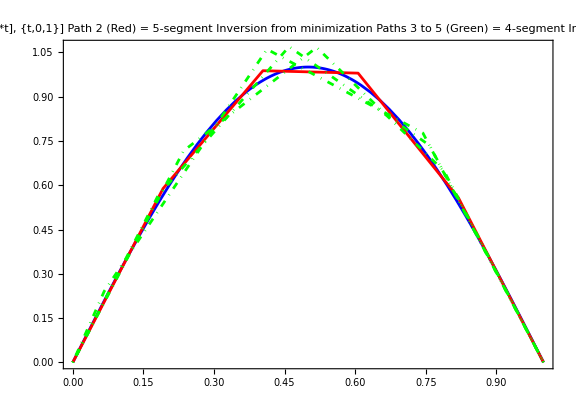

```mathematica
Show[Plot[Sin[π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t], {t,0,1}]
Path 2 (Red) = 5-segment Inversion from minimization
Paths 3 to 5 (Green) = 4-segment Inversions from dropping equations"],16]],
ListLinePlot[{ptsminim5sint,sol5sintv1pts,sol5sintv2pts,sol5sintv3pts},
PlotStyle->{ Red,{DotDashed,Green},{DotDashed,Green},{DotDashed,Green}}]]
```

#### Sin[2 π t]

```mathematica
sigsins2fcore5=getcore6[sigsins2f,5]
```

{{1,0},{0},{1/(2 π),1/4},{1/(4 π),1/8,0},{(-3+2 π^2)/(24 π^3),1/24-1/(64 π^2),-1/12+7/(32 π^2),1/(18 π),-7/(24 π),1/64}}

```mathematica
N[sigsins2fcore5]
```

{{1.,0.},{0.},{0.159155,0.25},{0.0795775,0.125,0.},{0.0224944,0.0400835,-0.0611693,0.0176839,-0.0928404,0.015625}}

```mathematica
Timing[minim5sin2t=minim3lines[Flatten[chen5z5core],Flatten[sigsins2fcore5],weights5seg,vars5linechen,bounds5seg]]
```

{1.13185,{1.2642×10^-8,{β_1→5.96998,β_2→0.72647,β_3→-5.60005,β_4→0.921517,β_5→6.00692,t_1→0.145817,t_2→0.175995,t_3→0.359052,t_4→0.1779,t_5→0.141236}}}

```mathematica
ptsminim5sin2t=flistbetat[Last[minim5sin2t]]
```

{{0,0},{0.145817,0.870524},{0.321812,0.998379},{0.680864,-1.01233},{0.858764,-0.848393},{1.,-5.01984×10^-9}}

```mathematica
Map[Length,{Flatten[chen4z5core],Flatten[sigsins2fcore5],vars4linechen}]
```

{14,14,8}

```mathematica
Timing[sol5sin2tv1=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins2fcore5]],vars4linechen,
{{4},{7},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{3.51478,{{β_1→3.98423,β_2→-5.45526,β_3→3.32231,β_4→9.41331,t_1→0.300536,t_2→0.433524,t_3→0.219306,t_4→0.0466333}}}

```mathematica
Timing[sol5sin2tv2=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins2fcore5]],vars4linechen,
{{5},{8},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{14.1422,{{β_1→5.3365,β_2→-4.82133,β_3→4.15396,β_4→14.3277,t_1→0.235701,t_2→0.50662,t_3→0.246436,t_4→0.0112425}}}

```mathematica
Timing[sol5sin2tv3=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins2fcore5]],vars4linechen,
{{5},{8},{9},{11},{12},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{1.81155,{{β_1→-4.97495,β_2→11.3264,β_3→-4.21019,β_4→5.51174,t_1→0.0312899,t_2→0.135379,t_3→0.614157,t_4→0.219173},{β_1→5.37841,β_2→-4.71942,β_3→3.41185,β_4→5.97736,t_1→0.232439,t_2→0.509509,t_3→0.151249,t_4→0.106803}}}

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sin2tv1[[1]],Flatten[sigsins2fcore5],weights5seg]
```

0.000488609

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sin2tv2[[1]],Flatten[sigsins2fcore5],weights5seg]
```

0.000323854

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sin2tv3[[1]],Flatten[sigsins2fcore5],weights5seg]
```

0.00279138

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sin2tv3[[2]],Flatten[sigsins2fcore5],weights5seg]
```

0.00018508

```mathematica
minim3linesfw[Flatten[chen5z5core]/.minim5sin2t[[2]],Flatten[sigsins2fcore5],weights5seg]
```

8.15203×10^-9

```mathematica
Map[flengthpathpts,Map[flistbetat,Join[sol5sin2tv1,sol5sin2tv2,sol5sin2tv3]]]
```

{4.84128,4.98868,5.58351,4.91457}

```mathematica
sol5sin2tpts=Map[flistbetat,Join[sol5sin2tv1,sol5sin2tv2,Rest[sol5sin2tv3]]]
```

{{{0,0},{0.300536,1.19741},{0.734061,-1.16758},{0.953367,-0.438974},{1.,-9.32587×10^-15}},{{0,0},{0.235701,1.25782},{0.742321,-1.18477},{0.988758,-0.161079},{1.,8.09824×10^-13}},{{0,0},{0.232439,1.25015},{0.741948,-1.15444},{0.893197,-0.638402},{1.,2.95208×10^-13}}}

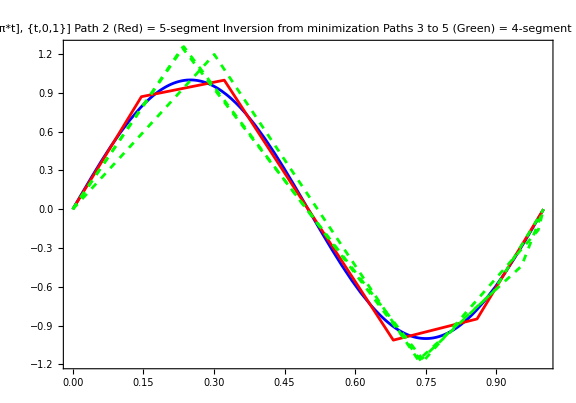

```mathematica
Show[Plot[Sin[2π t],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[2*π*t], {t,0,1}]
Path 2 (Red) = 5-segment Inversion from minimization
Paths 3 to 5 (Green) = 4-segment Inversions from dropping equations"],16]],
ListLinePlot[Prepend[sol5sin2tpts,ptsminim5sin2t],
PlotStyle->Prepend[ConstantArray[{Dashed,Green},Length[sol5sin2tpts]],{Red}]]]
```

```mathematica
NM
```

#### Sin[π t^2]

```mathematica
sigsins1f2fcore5=getcore6[sigsins1f2,5]
```

{{1,0},{-FresnelS[√2]/(√2)},{-1/π,1/8 (2-FresnelC[2])},{-(2+√2 FresnelC[√2])/(8 π),1/8,1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{-0.0265258,0.0433747,-0.0200633,-0.0353678,0.0546304,0.0114517}}

```mathematica
Timing[minim5sintsq=minim3lines[Flatten[chen5z5core],Flatten[sigsins1f2fcore5],weights5seg,vars5linechen,bounds5seg]]
```

{1.98938,{7.61478×10^-9,{β_1→0.34486,β_2→1.95755,β_3→-2.16561,β_4→1.28432,β_5→-5.90214,t_1→0.178769,t_2→0.518398,t_3→0.15151,t_4→0.0201492,t_5→0.131174}}}

```mathematica
ptsminim5sintsq=flistbetat[Last[minim5sintsq]]
```

{{0,0},{0.178769,0.0616503},{0.697167,1.07644},{0.848677,0.74833},{0.868826,0.774208},{1.,3.02267×10^-9}}

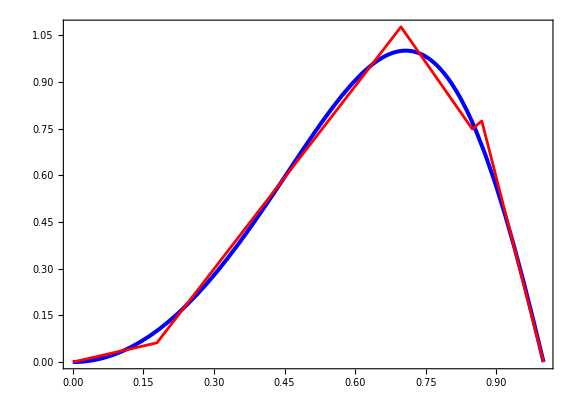

```mathematica
Show[Plot[Sin[π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{{Thickness[0.005],Blue}}],
ListLinePlot[ptsminim5sintsq,
PlotStyle->{Red}]]
```

```mathematica
N[sigsins1f2fcore5]
```

{{1.,0.},{-0.504855},{-0.31831,0.188968},{-0.109338,0.125,-0.0524083},{-0.0265258,0.0433747,-0.0200633,-0.0353678,0.0546304,0.0114517}}

```mathematica
Map[Length,{Flatten[chen4z5core],Flatten[sigsins1f2fcore5],vars4linechen}]
```

{14,14,8}

```mathematica
sol4sin1f2ex46=solve3lines[Expand[Flatten[chen3z4core]],Flatten[sigsins1f2fcore],vars3linechen,
{{4},{6}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0},6]
```

{{β_1→1.287,β_2→-20.277,β_3→1.6104,t_1→0.86332,t_2→0.0608,t_3→0.075878},{β_1→-25.852,β_2→1.58331,β_3→-5.12783,t_1→0.0047267,t_2→0.778674,t_3→0.2166}}

```mathematica
Timing[sol5sintsqv1=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins1f2fcore5]],vars4linechen,
{{5},{8},{10},{12},{13},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{1.60291,{{β_1→0.449724,β_2→2.35504,β_3→0.0721482,β_4→-5.64062,t_1→0.22885,t_2→0.343519,t_3→0.262602,t_4→0.165029},{β_1→0.367259,β_2→2.00438,β_3→-1.52412,β_4→-5.81245,t_1→0.187113,t_2→0.490988,t_3→0.190792,t_4→0.131107}}}

```mathematica
Timing[sol5sintsqv2=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins1f2fcore5]],vars4linechen,
{{4},{8},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{2.15306,{{β_1→0.399331,β_2→1.99503,β_3→-1.83445,β_4→-5.87827,t_1→0.19125,t_2→0.496784,t_3→0.189511,t_4→0.122455}}}

```mathematica
Timing[sol5sintsqv3=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins1f2fcore5]],vars4linechen,
{{4},{8},{9},{11},{12},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{9.89689,{{β_1→0.438152,β_2→2.03208,β_3→-1.74858,β_4→-5.88818,t_1→0.201811,t_2→0.480699,t_3→0.194269,t_4→0.123221},{β_1→0.773719,β_2→4.99381,β_3→-0.301467,β_4→-5.95474,t_1→0.396524,t_2→0.130916,t_3→0.327846,t_4→0.144714}}}

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sintsqv1[[1]],Flatten[sigsins1f2fcore5],weights5seg]
```

2.77941×10^-6

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sintsqv1[[2]],Flatten[sigsins1f2fcore5],weights5seg]
```

1.97431×10^-7

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sintsqv2[[1]],Flatten[sigsins1f2fcore5],weights5seg]
```

6.7827×10^-8

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sintsqv3[[1]],Flatten[sigsins1f2fcore5],weights5seg]
```

1.50063×10^-7

```mathematica
minim3linesfw[Flatten[chen4z5core]/.sol5sintsqv3[[2]],Flatten[sigsins1f2fcore5],weights5seg]
```

0.0000108425

```mathematica
minim3linesfw[Flatten[chen5z5core]/.minim5sintsq[[2]],Flatten[sigsins1f2fcore5],weights5seg]
```

8.8484×10^-8

```mathematica
Map[flengthpathpts,Map[flistbetat,Join[sol5sintsqv1,sol5sintsqv2,sol5sintsqv3]]]
```

{2.33851,2.42018,2.44069,2.43628,2.38432}

```mathematica
sol5sintsqpts=Map[flistbetat,Join[sol5sintsqv1,sol5sintsqv2,sol5sintsqv3]]
```

{{{0,0},{0.22885,0.102919},{0.572369,0.91192},{0.834971,0.930866},{1.,6.15064×10^-14}},{{0,0},{0.187113,0.0687191},{0.678101,1.05284},{0.868893,0.762052},{1.,1.28453×10^-13}},{{0,0},{0.19125,0.076372},{0.688034,1.06747},{0.877545,0.719825},{1.,5.81979×10^-13}},{{0,0},{0.201811,0.0884238},{0.682509,1.06524},{0.876779,0.725548},{1.,6.06137×10^-12}},{{0,0},{0.396524,0.306799},{0.52744,0.960567},{0.855286,0.861732},{1.,7.43172×10^-12}}}

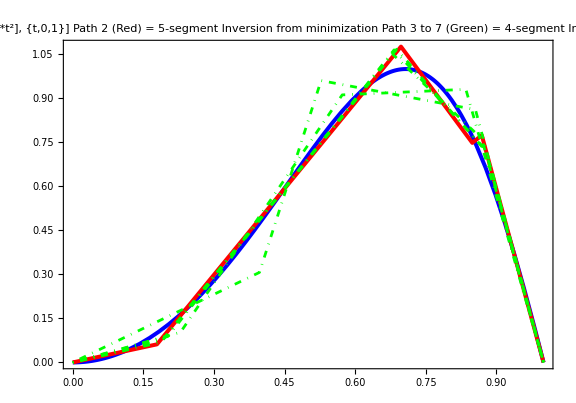

```mathematica
Show[Plot[Sin[π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{{Thickness[0.005],Blue}},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[π*t^2], {t,0,1}]
Path 2 (Red) = 5-segment Inversion from minimization
Path 3 to 7 (Green) = 4-segment Inversions from dropping equations"],16]],
ListLinePlot[Prepend[sol5sintsqpts,ptsminim5sintsq],
PlotStyle->Prepend[ConstantArray[{DotDashed,Green},Length[sol5sintsqpts]],{Thickness[0.005],Red}]]]
```

#### Sin[2 π t^2]

```mathematica
sigsins2f2fcore5=getcore6[sigsins2f2,5]
```

Part::partd: Part specification sigsins2f2⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification sigsins2f2⟦2,2⟧ is longer than depth of object.

{{sigsins2f2⟦2,1⟧,sigsins2f2⟦2,2⟧}}

```mathematica
N[{1,0,-FresnelS[2]/2,0,1/16 (4-√2 FresnelC[2 √2]),-(-2+FresnelC[2])/(16 π),1/8,1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3]),0.013262911924324612,0.04234888310071695,-0.07649142198712647,0.,-0.04480624557257676,0.012623408394187172}]
```

{1.,0.,-0.171708,0.,0.206193,0.0300752,0.125,-0.0165524,0.0132629,0.0423489,-0.0764914,0.,-0.0448062,0.0126234}

```mathematica
Timing[minim5sin2tsq=minim3lines[Flatten[chen5z5core],Flatten[sigsins2f2fcore5],weights5seg,vars5linechen,bounds5seg]]
```

{1.64598,{6.74761×10^-6,{β_1→0.550071,β_2→2.68134,β_3→2.65559,β_4→-6.74371,β_5→10.0326,t_1→0.124866,t_2→0.384831,t_3→0.0205384,t_4→0.349786,t_5→0.119985}}}

```mathematica
ptsminim5sin2tsq=flistbetat[Last[minim5sin2tsq]]
```

{{0,0},{0.124866,0.0686851},{0.509697,1.10055},{0.530235,1.15509},{0.880021,-1.20377},{1.00001,-1.04067×10^-8}}

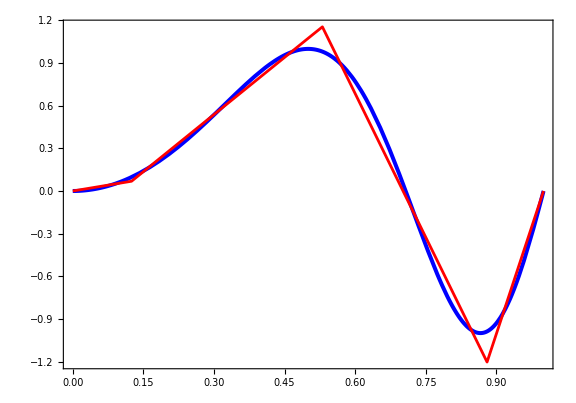

```mathematica
Show[Plot[Sin[2π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{{Thickness[0.005],Blue}}],
ListLinePlot[ptsminim5sin2tsq,
PlotStyle->{Red}]]
```

```mathematica
Grid[Take[NestList[update4l5[#,
{1.,0.,-0.17170783918184973,0.,0.20619299382339512,0.030075242890680726,0.125,-0.01655237814766992,0.013262911924324612,0.04234888310071695,-0.07649142198712647,0.,-0.04480624557257676,0.012623408394187172}]&,
{{0.5,1,0.75,1,1.0,1,1.25,1},1*10^-4},100],-10],Frame->All]
```

{0.0759003,0.986204,0.327974,0.937949,0.58622,0.831625,0.863246,0.623376} | 0.0001
{0.0747502,0.986182,0.326839,0.937823,0.585133,0.83128,0.862311,0.622544} | 0.0001
{0.073611,0.98616,0.325715,0.937699,0.584057,0.830939,0.861386,0.621719} | 0.0001
{0.0724824,0.986138,0.324601,0.937576,0.582991,0.830601,0.860469,0.620904} | 0.0001
{0.0713642,0.986117,0.323498,0.937454,0.581935,0.830267,0.859562,0.620097} | 0.0001
{0.0702561,0.986096,0.322405,0.937334,0.580889,0.829937,0.858664,0.619299} | 0.0001
{0.0691581,0.986075,0.321322,0.937214,0.579853,0.829609,0.857774,0.618509} | 0.0001
{0.0680699,0.986055,0.320248,0.937096,0.578826,0.829285,0.856893,0.617727} | 0.0001
{0.0669913,0.986036,0.319184,0.936979,0.577809,0.828965,0.85602,0.616953} | 0.0001
{0.0659221,0.986016,0.31813,0.936863,0.5768,0.828647,0.855155,0.616186} | 0.0001

```mathematica
N[sigsins2f2fcore5]
```

{{1.,0.},{-0.171708},{0.,0.206193},{0.0300752,0.125,-0.0165524},{0.0132629,0.0423489,-0.0764914,0.,-0.0448062,0.0126234}}

```mathematica
Map[Length,{Flatten[chen4z5core],Flatten[sigsins2f2fcore5],vars4linechen}]
```

{14,14,8}

```mathematica
Timing[sol5sin2tsqv1=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins2f2fcore5]],vars4linechen,
{{5},{8},{10},{12},{13},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{0.878158,{{β_1→0.606296,β_2→2.89647,β_3→-6.43566,β_4→10.8239,t_1→0.144742,t_2→0.375215,t_3→0.369099,t_4→0.110943}}}

```mathematica
Timing[sol5sin2tsqv2=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins2f2fcore5]],vars4linechen,
{{4},{8},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{2.16953,{{β_1→1.11801,β_2→2.97268,β_3→-6.76361,β_4→9.84354,t_1→0.205803,t_2→0.319673,t_3→0.352341,t_4→0.122183}}}

```mathematica
Timing[sol5sin2tsqv3=solve3lines[Expand[Flatten[chen4z5core]],N[Flatten[sigsins2f2fcore5]],vars4linechen,
{{4},{8},{9},{11},{12},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{9.68474,{{β_1→1.02936,β_2→2.93042,β_3→-6.69348,β_4→10.0722,t_1→0.190339,t_2→0.334655,t_3→0.355546,t_4→0.11946}}}

```mathematica
Map[flengthpathpts,Map[flistbetat,Join[sol5sin2tsqv1,sol5sin2tsqv2,sol5sin2tsqv3]]]
```

{4.92887,4.92922,4.92476}

```mathematica
sol5sin2tsqpts=Map[flistbetat,Join[sol5sin2tsqv1,sol5sin2tsqv2,sol5sin2tsqv3]]
```

{{{0,0},{0.144742,0.0877566},{0.519957,1.17456},{0.889057,-1.20084},{1.,-2.73115×10^-14}},{{0,0},{0.205803,0.230089},{0.525476,1.18038},{0.877817,-1.20272},{1.,4.93805×10^-12}},{{0,0},{0.190339,0.195927},{0.524994,1.17661},{0.88054,-1.20323},{1.,-1.85385×10^-12}}}

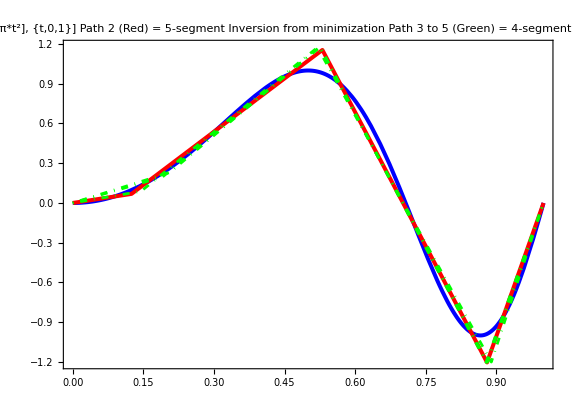

```mathematica
Show[Plot[Sin[2π t^2],{t,0,1},Frame->True,
PlotRange->All,AspectRatio->7/10,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{{Thickness[0.005],Blue}},
PlotLabel->Style[Framed[
"Path 1 (Blue) = Plot[{Sin[2*π*t^2], {t,0,1}]
Path 2 (Red) = 5-segment Inversion from minimization
Path 3 to 5 (Green) = 4-segment Inversions from dropping equations"],16]],
ListLinePlot[Prepend[sol5sin2tsqpts,ptsminim5sin2tsq],
PlotStyle->Prepend[ConstantArray[{DotDashed,Green},Length[sol5sin2tsqpts]],{Thickness[0.005],Red}]]]
```

#### 4 segments

```mathematica
sig4seg=chainchen[
{signat[{{t,2 t}},{0,3},5][[1]],
signat[{{t,-4 t}},{0,1},5][[1]],
signat[{{t,3 t}},{0,2},5][[1]],
signat[{{t,-2 t}},{0,4},5][[1]]},
5];
```

```mathematica
sig4segcore=getcore6[sig4seg,5]
```

{{10,0},{-39},{-201,292/3},{-2471/4,3109/6,-547/3},{-5561/4,7803/5,-2821/15,-14986/15,5128/5,276}}

```mathematica
Timing[sol4segexv1=solve3lines[Expand[Flatten[chen4z5core]],Flatten[sig4segcore],vars4linechen,
{{4},{8},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{1.94056,{{β_1→2.,β_2→-4.,β_3→3.,β_4→-2.,t_1→3.,t_2→0.999999,t_3→2.,t_4→4.}}}

```mathematica
Timing[sol4segexv2=solve3lines[Expand[Flatten[chen4z5core]],Flatten[sig4segcore],vars4linechen,
{{4},{7},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{11.37,{{β_1→2.,β_2→-4.,β_3→3.,β_4→-2.,t_1→3.,t_2→1.,t_3→2.,t_4→4.}}}

```mathematica
Timing[sol4segexv3=solve3lines[Expand[Flatten[chen4z5core]],Flatten[sig4segcore],vars4linechen,
{{5},{7},{9},{10},{11},{14}},{Subscript[t, 1]>0,Subscript[t, 2]>0,Subscript[t, 3]>0,Subscript[t, 4]>0},6]]
```

{53.1678,{{β_1→2.,β_2→-4.,β_3→3.,β_4→-2.,t_1→3.,t_2→1.,t_3→2.,t_4→4.}}}

## d=2, General

### Definitions

```mathematica
signat[{{Subscript[α, 1] t,Subscript[β, 1] t}},{0,Subscript[t, 1]},5][[1]]
```

{{1},{t_1 α_1,t_1 β_1},{{1/2 t_1^2 α_1^2,1/2 t_1^2 α_1 β_1},{1/2 t_1^2 α_1 β_1,1/2 t_1^2 β_1^2}},{{{1/6 t_1^3 α_1^3,1/6 t_1^3 α_1^2 β_1},{1/6 t_1^3 α_1^2 β_1,1/6 t_1^3 α_1 β_1^2}},{{1/6 t_1^3 α_1^2 β_1,1/6 t_1^3 α_1 β_1^2},{1/6 t_1^3 α_1 β_1^2,1/6 t_1^3 β_1^3}}},{{{{1/24 t_1^4 α_1^4,1/24 t_1^4 α_1^3 β_1},{1/24 t_1^4 α_1^3 β_1,1/24 t_1^4 α_1^2 β_1^2}},{{1/24 t_1^4 α_1^3 β_1,1/24 t_1^4 α_1^2 β_1^2},{1/24 t_1^4 α_1^2 β_1^2,1/24 t_1^4 α_1 β_1^3}}},{{{1/24 t_1^4 α_1^3 β_1,1/24 t_1^4 α_1^2 β_1^2},{1/24 t_1^4 α_1^2 β_1^2,1/24 t_1^4 α_1 β_1^3}},{{1/24 t_1^4 α_1^2 β_1^2,1/24 t_1^4 α_1 β_1^3},{1/24 t_1^4 α_1 β_1^3,1/24 t_1^4 β_1^4}}}},{{{{{1/120 t_1^5 α_1^5,1/120 t_1^5 α_1^4 β_1},{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2}},{{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2},{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3}}},{{{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2},{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3}},{{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3},{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4}}}},{{{{1/120 t_1^5 α_1^4 β_1,1/120 t_1^5 α_1^3 β_1^2},{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3}},{{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3},{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4}}},{{{1/120 t_1^5 α_1^3 β_1^2,1/120 t_1^5 α_1^2 β_1^3},{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4}},{{1/120 t_1^5 α_1^2 β_1^3,1/120 t_1^5 α_1 β_1^4},{1/120 t_1^5 α_1 β_1^4,1/120 t_1^5 β_1^5}}}}}}

```mathematica
signat[{{a t,b t}},{0,1},5][[1]]
```

{{1},{a,b},{{a^2/2,(a b)/2},{(a b)/2,b^2/2}},{{{a^3/6,(a^2 b)/6},{(a^2 b)/6,(a b^2)/6}},{{(a^2 b)/6,(a b^2)/6},{(a b^2)/6,b^3/6}}},{{{{a^4/24,(a^3 b)/24},{(a^3 b)/24,(a^2 b^2)/24}},{{(a^3 b)/24,(a^2 b^2)/24},{(a^2 b^2)/24,(a b^3)/24}}},{{{(a^3 b)/24,(a^2 b^2)/24},{(a^2 b^2)/24,(a b^3)/24}},{{(a^2 b^2)/24,(a b^3)/24},{(a b^3)/24,b^4/24}}}},{{{{{a^5/120,(a^4 b)/120},{(a^4 b)/120,(a^3 b^2)/120}},{{(a^4 b)/120,(a^3 b^2)/120},{(a^3 b^2)/120,(a^2 b^3)/120}}},{{{(a^4 b)/120,(a^3 b^2)/120},{(a^3 b^2)/120,(a^2 b^3)/120}},{{(a^3 b^2)/120,(a^2 b^3)/120},{(a^2 b^3)/120,(a b^4)/120}}}},{{{{(a^4 b)/120,(a^3 b^2)/120},{(a^3 b^2)/120,(a^2 b^3)/120}},{{(a^3 b^2)/120,(a^2 b^3)/120},{(a^2 b^3)/120,(a b^4)/120}}},{{{(a^3 b^2)/120,(a^2 b^3)/120},{(a^2 b^3)/120,(a b^4)/120}},{{(a^2 b^3)/120,(a b^4)/120},{(a b^4)/120,b^5/120}}}}}}

```mathematica
chen2d3z4=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},4][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},4][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},4][[1]]},
4];
```

```mathematica
chen2d3z4core=getcore6[chen2d3z4,4];
```

```mathematica
chen2d4z5=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},5][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},5][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},5][[1]],
signat[{{Subscript[a, 4] t,Subscript[b, 4] t}},{0,1},5][[1]]},
5];
```

```mathematica
chen2d4z5core=getcore6[chen2d4z5,5];
```

```mathematica
chen2d5z5=chainchen[
{signat[{{Subscript[a, 1] t,Subscript[b, 1] t}},{0,1},5][[1]],
signat[{{Subscript[a, 2] t,Subscript[b, 2] t}},{0,1},5][[1]],
signat[{{Subscript[a, 3] t,Subscript[b, 3] t}},{0,1},5][[1]],
signat[{{Subscript[a, 4] t,Subscript[b, 4] t}},{0,1},5][[1]],
signat[{{Subscript[a, 5] t,Subscript[b, 5] t}},{0,1},5][[1]]},
5];
```

```mathematica
chen2d5z5core=getcore6[chen2d5z5,5];
```

```mathematica
vars3line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]};
```

```mathematica
vars4line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]};
```

```mathematica
vars5line2dchen={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4],Subscript[b, 5]};
```

```mathematica
cores4
```

{z_1,z_2,z_(1,2),z_(1,1,2),z_(1,2,2),z_(1,1,1,2),z_(1,1,2,2),z_(1,2,2,2)}

```mathematica
cores5
```

{z_1,z_2,z_(1,2),z_(1,1,2),z_(1,2,2),z_(1,1,1,2),z_(1,1,2,2),z_(1,2,2,2),z_(1,1,1,1,2),z_(1,1,1,2,2),z_(1,1,2,1,2),z_(1,1,2,2,2),z_(1,2,1,2,2),z_(1,2,2,2,2)}

### Semicircle

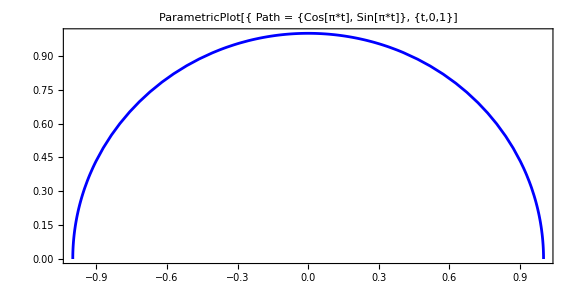

```mathematica
ParametricPlot[{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1/2,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path = {Cos[π*t], Sin[π*t]},
 {t,0,1}]"],16]]
```

```mathematica
Timing[sigsemicircle5=signat[{{Cos[π t],Sin[π t]}},{0,1},5][[1]]]
```

{115.222,{{1},{-2,0},{{2,π/2},{-π/2,0}},{{{-4/3,-π/2},{0,-2/3}},{{π/2,4/3},{-2/3,0}}},{{{{2/3,(5 π)/16},{π/16,2/3}},{{-π/16,-4/3+π^2/8},{4/3-π^2/8,π/16}}},{{{-(5 π)/16,-π^2/8},{-4/3+π^2/8,-(3 π)/16}},{{2/3,(3 π)/16},{-π/16,0}}}},{{{{{-4/15,-(7 π)/48},{-π/24,-2/5}},{{0,52/45-π^2/8},{-58/45+π^2/8,-π/16}}},{{{π/24,-16/15+π^2/8},{112/45-π^2/4,π/48}},{{-58/45+π^2/8,-π/48},{0,-2/45}}}},{{{{(7 π)/48,32/45},{-16/15+π^2/8,π/6}},{{52/45-π^2/8,0},{π/48,8/45}}},{{{-2/5,-π/6},{-π/48,-4/15}},{{π/16,8/45},{-2/45,0}}}}}}}

```mathematica
semicirclecore4=getcore6[sigsemicircle5,4]
```

{{-2,0},{π/2},{-π/2,-2/3},{(5 π)/16,2/3,π/16}}

```mathematica
semicirclecore5=getcore6[sigsemicircle5,5]
```

{{-2,0},{π/2},{-π/2,-2/3},{(5 π)/16,2/3,π/16},{-(7 π)/48,-2/5,52/45-π^2/8,-π/16,π/48,-2/45}}

#### 3 segments

```mathematica
Timing[solsemicircle3ex46=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{4},{6}},{},5]]
```

{0.018239,{{a_1→-0.483,a_2→-1.5737,a_3→0.0567,b_1→1.098,b_2→-0.5154,b_3→-0.5825},{a_1→0.0567,a_2→-1.5737,a_3→-0.483,b_1→0.5825,b_2→0.5154,b_3→-1.098}}}

```mathematica
Timing[solsemicircle3ex47=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{4},{7}},{},5]]
```

{0.01932,{{a_1→2.069,a_2→0.2068,a_3→-4.276,b_1→0.5825,b_2→0.5154,b_3→-1.098},{a_1→-0.3695,a_2→-1.627,a_3→-0.004,b_1→1.098,b_2→-0.5154,b_3→-0.5825},{a_1→0.02213,a_2→-1.604,a_3→-0.4179,b_1→0.5825,b_2→0.5154,b_3→-1.098},{a_1→3.131,a_2→-3.27,a_3→-1.861,b_1→1.098,b_2→-0.5154,b_3→-0.5825}}}

```mathematica
Timing[solsemicircle3ex48=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{4},{8}},{},5]]
```

{0.015636,{{a_1→-1.594,a_2→0.64,a_3→-1.046,b_1→2.378,b_2→-0.2281,b_3→-2.15},{a_1→-0.1662,a_2→-1.543,a_3→-0.29071,b_1→0.82626,b_2→0.11676,b_3→-0.94302}}}

```mathematica
Timing[solsemicircle3ex56=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{5},{6}},{},5]]
```

{0.02108,{{a_1→-5.017,a_2→9.798,a_3→-6.781,b_1→0.251,b_2→-1.691,b_3→1.439},{a_1→-18.,a_2→16.98,a_3→-0.981,b_1→27.78,b_2→-26.21,b_3→-1.573},{a_1→1.495,a_2→-2.117,a_3→-1.38,b_1→-4.731,b_2→6.472,b_3→-1.741},{a_1→-0.2864,a_2→-1.497,a_3→-0.216,b_1→0.9425,b_2→-0.09028,b_3→-0.8522}}}

```mathematica
Timing[solsemicircle3ex57=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{5},{7}},{},5]]
```

{0.020759,{{a_1→-1.458,a_2→1.549,a_3→-2.091,b_1→-6.366,b_2→11.1,b_3→-4.734},{a_1→-2.091,a_2→1.549,a_3→-1.458,b_1→4.734,b_2→-11.1,b_3→6.366}}}

```mathematica
Timing[solsemicircle3ex58=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[semicirclecore4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.015868,{{a_1→-1.114,a_2→4.504,a_3→-5.39,b_1→1.518,b_2→7.835,b_3→-9.353},{a_1→-0.3949,a_2→-1.431,a_3→-0.174,b_1→1.0503,b_2→-0.288,b_3→-0.762}}}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{solsemicircle3ex46,solsemicircle3ex47,solsemicircle3ex48,solsemicircle3ex56,solsemicircle3ex57,solsemicircle3ex58}]]
```

a_1→-0.483 | a_2→-1.5737 | a_3→0.0567 | b_1→1.098 | b_2→-0.5154 | b_3→-0.5825
a_1→0.0567 | a_2→-1.5737 | a_3→-0.483 | b_1→0.5825 | b_2→0.5154 | b_3→-1.098
a_1→2.069 | a_2→0.2068 | a_3→-4.276 | b_1→0.5825 | b_2→0.5154 | b_3→-1.098
a_1→-0.3695 | a_2→-1.627 | a_3→-0.004 | b_1→1.098 | b_2→-0.5154 | b_3→-0.5825
a_1→0.02213 | a_2→-1.604 | a_3→-0.4179 | b_1→0.5825 | b_2→0.5154 | b_3→-1.098
a_1→3.131 | a_2→-3.27 | a_3→-1.861 | b_1→1.098 | b_2→-0.5154 | b_3→-0.5825
a_1→-1.594 | a_2→0.64 | a_3→-1.046 | b_1→2.378 | b_2→-0.2281 | b_3→-2.15
a_1→-0.1662 | a_2→-1.543 | a_3→-0.29071 | b_1→0.82626 | b_2→0.11676 | b_3→-0.94302
a_1→-5.017 | a_2→9.798 | a_3→-6.781 | b_1→0.251 | b_2→-1.691 | b_3→1.439
a_1→-18. | a_2→16.98 | a_3→-0.981 | b_1→27.78 | b_2→-26.21 | b_3→-1.573
a_1→1.495 | a_2→-2.117 | a_3→-1.38 | b_1→-4.731 | b_2→6.472 | b_3→-1.741
a_1→-0.2864 | a_2→-1.497 | a_3→-0.216 | b_1→0.9425 | b_2→-0.09028 | b_3→-0.8522
a_1→-1.458 | a_2→1.549 | a_3→-2.091 | b_1→-6.366 | b_2→11.1 | b_3→-4.734
a_1→-2.091 | a_2→1.549 | a_3→-1.458 | b_1→4.734 | b_2→-11.1 | b_3→6.366
a_1→-1.114 | a_2→4.504 | a_3→-5.39 | b_1→1.518 | b_2→7.835 | b_3→-9.353
a_1→-0.3949 | a_2→-1.431 | a_3→-0.174 | b_1→1.0503 | b_2→-0.288 | b_3→-0.762

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistab[#,{1,0}]&,{solsemicircle3ex46,solsemicircle3ex47,solsemicircle3ex48,solsemicircle3ex56,solsemicircle3ex57,solsemicircle3ex58},{2}]]]
```

{1,0} | {0.517,1.098} | {-1.057,0.5825} | {-1.,0.}
{1,0} | {1.057,0.5825} | {-0.517,1.098} | {-1.,0.}
{1,0} | {3.069,0.5825} | {3.276,1.098} | {-1.,0.}
{1,0} | {0.6305,1.098} | {-0.9965,0.5825} | {-1.,0.}
{1,0} | {1.02213,0.5825} | {-0.5821,1.098} | {-1.,0.}
{1,0} | {4.131,1.098} | {0.861,0.5825} | {-1.,0.}
{1,0} | {-0.5944,2.378} | {0.046,2.15} | {-1.,0.}
{1,0} | {0.83376,0.82626} | {-0.7093,0.94302} | {-1.,0.}
{1,0} | {-4.017,0.251} | {5.781,-1.439} | {-1.,0.}
{1,0} | {-17.,27.78} | {-0.02,1.57} | {-1.,0.}
{1,0} | {2.495,-4.731} | {0.378,1.74} | {-1.,0.}
{1,0} | {0.71357,0.9425} | {-0.7839,0.8522} | {-1.,0.}
{1,0} | {-0.4584,-6.366} | {1.091,4.734} | {-1.,0.}
{1,0} | {-1.091,4.734} | {0.458,-6.366} | {-1.,0.}
{1,0} | {-0.114,1.518} | {4.39,9.353} | {-1.,0.}
{1,0} | {0.6051,1.0503} | {-0.8263,0.762} | {-1.,0.}

```mathematica
TableForm[Map[flengthpathpts[flistab[#,{1,0}]]&,{solsemicircle3ex46,solsemicircle3ex47,solsemicircle3ex48,solsemicircle3ex56,solsemicircle3ex57,solsemicircle3ex58},{2}]]
```

3.44 | 3.44 |  | 
7.12 | 3.4 | 3.44 | 8.578
5.93 | 3.38 |  | 
21.9 | 66.2 | 14. | 3.36
22.91 | 22.91 |  | 
21.72 | 3.36 |  |

```mathematica
TableForm[Map[(flengthpathpts[flistab[#,{1,0}]]<4)&,{solsemicircle3ex46,solsemicircle3ex47,solsemicircle3ex48,solsemicircle3ex56,solsemicircle3ex57,solsemicircle3ex58},{2}]]
```

True | True |  | 
False | True | True | False
False | True |  | 
False | False | False | True
False | False |  | 
False | True |  |

```mathematica
solsemicircle3pts=Flatten[Map[flistab[#,{1,0}]&,Pick[{solsemicircle3ex46,solsemicircle3ex47,solsemicircle3ex48,solsemicircle3ex56,solsemicircle3ex57,solsemicircle3ex58},
Map[(flengthpathpts[flistab[#,{1,0}]]<4)&,{solsemicircle3ex46,solsemicircle3ex47,solsemicircle3ex48,solsemicircle3ex56,solsemicircle3ex57,solsemicircle3ex58},{2}]],{2}],1]
```

{{{1,0},{0.517,1.098},{-1.057,0.5825},{-1.,0.}},{{1,0},{1.057,0.5825},{-0.517,1.098},{-1.,0.}},{{1,0},{0.6305,1.098},{-0.9965,0.5825},{-1.,0.}},{{1,0},{1.02213,0.5825},{-0.5821,1.098},{-1.,0.}},{{1,0},{0.83376,0.82626},{-0.7093,0.94302},{-1.,0.}},{{1,0},{0.71357,0.9425},{-0.7839,0.8522},{-1.,0.}},{{1,0},{0.6051,1.0503},{-0.8263,0.762},{-1.,0.}}}

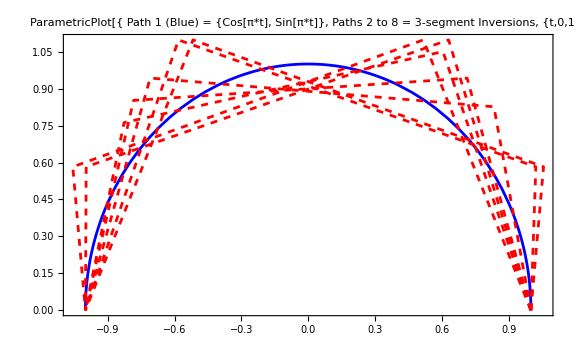

```mathematica
Show[ParametricPlot[
{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->3/5,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 (Blue) = {Cos[π*t], Sin[π*t]},
Paths 2 to 8 = 3-segment Inversions,
 {t,0,1}]"],16]],
ListLinePlot[solsemicircle3pts,
PlotStyle->{ {Dashed,Red}}]]
```

#### 4+ segments

```mathematica
Timing[minim5semicircle=minim3lines[Flatten[chen2d5z5core],Flatten[semicirclecore5],weights5seg,vars5line2dchen]]
```

{0.733392,{1.15123×10^-6,{a_1→-0.0492683,a_2→-0.567619,a_3→-0.739165,a_4→-0.57564,a_5→-0.0683083,b_1→0.42485,b_2→0.558006,b_3→-0.00264784,b_4→-0.504476,b_5→-0.475732}}}

```mathematica
ptsminim5semicircle=flistab[Last[minim5semicircle],{1,0}]
```

{{1,0},{0.950732,0.42485},{0.383113,0.982856},{-0.356052,0.980208},{-0.931692,0.475732},{-1.,-3.11648×10^-8}}

```mathematica
Timing[solsemicircle4v1=Select[solve3lines[Expand[Flatten[chen2d4z5core]],Flatten[semicirclecore5],vars4line2dchen,
{{4},{8},{9},{11},{13},{14}},{},5],(flengthpathpts[flistab[#,{1,0}]]<4)&]]
```

{0.518017,{{a_1→-0.026712,a_2→-0.81009,a_3→-1.0402,a_4→-0.12302,b_1→0.41934,b_2→0.68826,b_3→-0.47027,b_4→-0.63733}}}

```mathematica
Timing[solsemicircle4v2=Select[solve3lines[Expand[Flatten[chen2d4z5core]],Flatten[semicirclecore5],vars4line2dchen,
{{4},{7},{9},{11},{13},{14}},{},5],(flengthpathpts[flistab[#,{1,0}]]<4)&]]
```

{1.13281,{{a_1→-0.10656,a_2→-0.94373,a_3→-0.85763,a_4→-0.092083,b_1→0.60646,b_2→0.49082,b_3→-0.54128,b_4→-0.556}}}

```mathematica
Timing[solsemicircle4v3=Select[solve3lines[Expand[Flatten[chen2d4z5core]],Flatten[semicirclecore5],vars4line2dchen,
{{5},{8},{9},{11},{12},{14}},{},5],(flengthpathpts[flistab[#,{1,0}]]<4)&]]
```

{0.417931,{{a_1→-0.21437,a_2→-1.0178,a_3→-0.69453,a_4→-0.073264,b_1→0.7794,b_2→0.27278,b_3→-0.55794,b_4→-0.49425}}}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{solsemicircle4v1,solsemicircle4v2,solsemicircle4v3}]]
```

a_1→-0.026712 | a_2→-0.81009 | a_3→-1.0402 | a_4→-0.12302 | b_1→0.41934 | b_2→0.68826 | b_3→-0.47027 | b_4→-0.63733
a_1→-0.10656 | a_2→-0.94373 | a_3→-0.85763 | a_4→-0.092083 | b_1→0.60646 | b_2→0.49082 | b_3→-0.54128 | b_4→-0.556
a_1→-0.21437 | a_2→-1.0178 | a_3→-0.69453 | a_4→-0.073264 | b_1→0.7794 | b_2→0.27278 | b_3→-0.55794 | b_4→-0.49425

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistab[#,{1,0}]&,{solsemicircle4v1,solsemicircle4v2,solsemicircle4v3},{2}]]]
```

{1,0} | {0.973288,0.41934} | {0.1632,1.1076} | {-0.877,0.6373} | {-1.,0.}
{1,0} | {0.89344,0.60646} | {-0.0503,1.0973} | {-0.9079,0.556} | {-1.,0.}
{1,0} | {0.78563,0.7794} | {-0.2322,1.0522} | {-0.9267,0.4942} | {-1.,0.}

```mathematica
TableForm[Map[flengthpathpts[flistab[#,{1,0}]]&,{solsemicircle4v1,solsemicircle4v2,solsemicircle4v3},{2}]]
```

3.274
3.26
3.25

```mathematica
solsemicircle4pts=Map[flistab[#,{1,0}]&,Flatten[{solsemicircle4v1,solsemicircle4v2,solsemicircle4v3},1]]
```

{{{1,0},{0.973288,0.41934},{0.1632,1.1076},{-0.877,0.6373},{-1.,0.}},{{1,0},{0.89344,0.60646},{-0.0503,1.0973},{-0.9079,0.556},{-1.,0.}},{{1,0},{0.78563,0.7794},{-0.2322,1.0522},{-0.9267,0.4942},{-1.,0.}}}

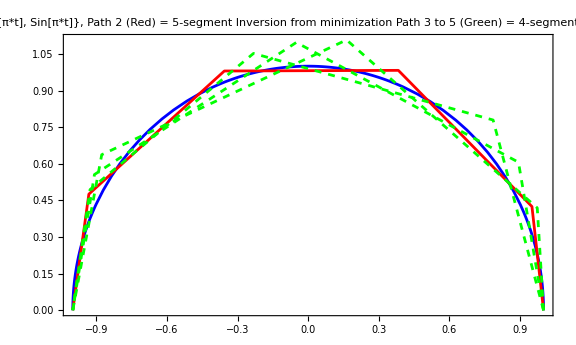

```mathematica
Show[ParametricPlot[
{Cos[π t],Sin[π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->3/5,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 (Blue) = {Cos[π*t], Sin[π*t]},
Path 2 (Red) = 5-segment Inversion from minimization
Path 3 to 5 (Green) = 4-segment Inversions from dropping equations,
 {t,0,1}]"],16]],
ListLinePlot[Prepend[solsemicircle4pts,ptsminim5semicircle],
PlotStyle->Prepend[ConstantArray[{Dashed,Green},Length[solsemicircle4pts]],{Red}]]]
```

### Digit 5

```mathematica
digit5=({{0, 0}, {20, -3}, {64, 13}, {79, 47}, {35, 54}, {37, 77}, {71, 96}, {100, 93}});
```

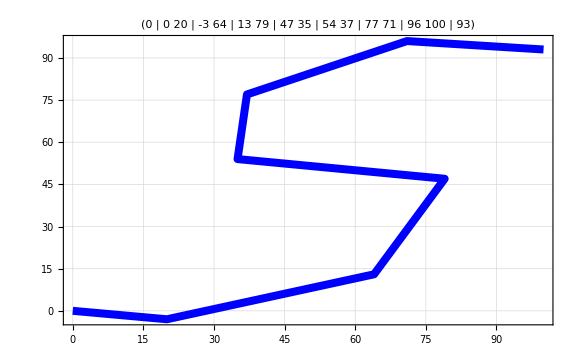

```mathematica
ListLinePlot[digit5,ImageSize->Large,GridLines->Automatic,Frame->True,
PlotLabel->digit5,PlotStyle->{Thickness[0.01],Blue}]
```

```mathematica
Differences[digit5]
```

{{20,-3},{44,16},{15,34},{-44,7},{2,23},{34,19},{29,-3}}

```mathematica
chendigit5l6=chainchen[Map[(signat[{#*t},{0,1},6][[1]])&,Differences[digit5]],6];
```

```mathematica
digit5core4=getcore6[chendigit5l6,4]
```

{{100,93},{10139/2},{440461/3,505767/2},{71967937/24,62070307/8,191264681/24}}

```mathematica
digit5core5=getcore6[chendigit5l6,5]
```

{{100,93},{10139/2},{440461/3,505767/2},{71967937/24,62070307/8,191264681/24},{715742579/15,670296411/4,-648755657/6,2440364507/10,-1063111129/30,1468494543/8}}

#### 3 segments

```mathematica
Timing[minim3digit5=minim3lines[Flatten[chen2d3z4core],Flatten[digit5core4],weights3seg,vars3line2dchen,{},"RandomSearch"]]
```

{5.20386,{2065.98,{a_1→77.0486,a_2→-43.9862,a_3→71.3084,b_1→13.9319,b_2→78.9769,b_3→2.71015}}}

```mathematica
ptsminim3digit5=flistab[Last[minim3digit5],{0,0}]
```

{{0,0},{77.0486,13.9319},{33.0624,92.9088},{104.371,95.619}}

```mathematica
{Length[Flatten[chen2d3z4core]],Length[Flatten[digit5core4]],Length[vars3line2dchen]}
```

{8,8,6}

```mathematica
Timing[soldigit5p3ex46=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[digit5core4],vars3line2dchen,
{{4},{6}},{},5]]
```

{0.015497,{{a_1→102.95,a_2→-114.,a_3→111.08,b_1→186.3,b_2→-252.3,b_3→159.},{a_1→72.482,a_2→-33.593,a_3→61.111,b_1→5.3681,b_2→87.987,b_3→-0.355}}}

```mathematica
Timing[soldigit5p3ex47=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[digit5core4],vars3line2dchen,
{{4},{7}},{},5]]
```

{0.01959,{{a_1→601.18,a_2→-1313.9,a_3→812.73,b_1→85.588,b_2→-73.372,b_3→80.785},{a_1→134.78,a_2→-166.73,a_3→131.95,b_1→203.33,b_2→-280.55,b_3→170.22},{a_1→-330.53,a_2→551.27,a_3→-120.74,b_1→116.02,b_2→-129.76,b_3→106.75},{a_1→76.402,a_2→-41.502,a_3→65.1,b_1→7.4325,b_2→83.562,b_3→2.0054}}}

```mathematica
Timing[soldigit5p3ex48=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[digit5core4],vars3line2dchen,
{{4},{8}},{},5]]
```

{0.020678,{{a_1→142.7,a_2→-165.,a_3→122.3,b_1→243.5,b_2→-302.3,b_3→151.8},{a_1→-164.,a_2→196.7,a_3→67.3,b_1→213.,b_2→-231.,b_3→111.1},{a_1→141.7,a_2→-428.1,a_3→386.4,b_1→77.94,b_2→45.5,b_3→-30.47},{a_1→74.91,a_2→-41.42,a_3→66.51,b_1→3.36,b_2→82.83,b_3→6.806}}}

```mathematica
Timing[soldigit5p3ex56=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[digit5core4],vars3line2dchen,
{{5},{6}},{},5]]
```

{0.021195,{{a_1→101.3,a_2→-367.1,a_3→365.9,b_1→94.,b_2→366.,b_3→-366.9},{a_1→-240.5,a_2→241.2,a_3→99.2,b_1→671.3,b_2→-675.,b_3→96.76},{a_1→127.5,a_2→-150.7,a_3→123.2,b_1→213.6,b_2→-284.9,b_3→164.3},{a_1→74.89,a_2→-39.37,a_3→64.48,b_1→6.13,b_2→83.34,b_3→3.532}}}

```mathematica
Timing[soldigit5p3ex57=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[digit5core4],vars3line2dchen,
{{5},{7}},{},5]]
```

{0.019831,{{a_1→95.18,a_2→-78.889,a_3→83.709,b_1→-50.51,b_2→361.55,b_3→-218.03},{a_1→71.648,a_2→-37.484,a_3→65.836,b_1→1.72,b_2→78.67,b_3→12.606}}}

```mathematica
Timing[soldigit5p3ex58=solve3lines[Expand[Flatten[chen2d3z4core]],Flatten[digit5core4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.015532,{{a_1→158.42,a_2→-177.01,a_3→118.59,b_1→281.99,b_2→-327.76,b_3→138.77},{a_1→74.233,a_2→-42.21,a_3→67.977,b_1→-0.3274,b_2→83.755,b_3→9.5723}}}

```mathematica
TableForm[Map[Grid[#,Frame->All]&,{soldigit5p3ex46,soldigit5p3ex47,soldigit5p3ex48,soldigit5p3ex56,soldigit5p3ex57,soldigit5p3ex58}]]
```

a_1→102.95 | a_2→-114. | a_3→111.08 | b_1→186.3 | b_2→-252.3 | b_3→159.
a_1→72.482 | a_2→-33.593 | a_3→61.111 | b_1→5.3681 | b_2→87.987 | b_3→-0.355
a_1→601.18 | a_2→-1313.9 | a_3→812.73 | b_1→85.588 | b_2→-73.372 | b_3→80.785
a_1→134.78 | a_2→-166.73 | a_3→131.95 | b_1→203.33 | b_2→-280.55 | b_3→170.22
a_1→-330.53 | a_2→551.27 | a_3→-120.74 | b_1→116.02 | b_2→-129.76 | b_3→106.75
a_1→76.402 | a_2→-41.502 | a_3→65.1 | b_1→7.4325 | b_2→83.562 | b_3→2.0054
a_1→142.7 | a_2→-165. | a_3→122.3 | b_1→243.5 | b_2→-302.3 | b_3→151.8
a_1→-164. | a_2→196.7 | a_3→67.3 | b_1→213. | b_2→-231. | b_3→111.1
a_1→141.7 | a_2→-428.1 | a_3→386.4 | b_1→77.94 | b_2→45.5 | b_3→-30.47
a_1→74.91 | a_2→-41.42 | a_3→66.51 | b_1→3.36 | b_2→82.83 | b_3→6.806
a_1→101.3 | a_2→-367.1 | a_3→365.9 | b_1→94. | b_2→366. | b_3→-366.9
a_1→-240.5 | a_2→241.2 | a_3→99.2 | b_1→671.3 | b_2→-675. | b_3→96.76
a_1→127.5 | a_2→-150.7 | a_3→123.2 | b_1→213.6 | b_2→-284.9 | b_3→164.3
a_1→74.89 | a_2→-39.37 | a_3→64.48 | b_1→6.13 | b_2→83.34 | b_3→3.532
a_1→95.18 | a_2→-78.889 | a_3→83.709 | b_1→-50.51 | b_2→361.55 | b_3→-218.03
a_1→71.648 | a_2→-37.484 | a_3→65.836 | b_1→1.72 | b_2→78.67 | b_3→12.606
a_1→158.42 | a_2→-177.01 | a_3→118.59 | b_1→281.99 | b_2→-327.76 | b_3→138.77
a_1→74.233 | a_2→-42.21 | a_3→67.977 | b_1→-0.3274 | b_2→83.755 | b_3→9.5723

```mathematica
TableForm[Map[Grid[#,Frame->All]&,Map[flistab[#,{0,0}]&,{soldigit5p3ex46,soldigit5p3ex47,soldigit5p3ex48,soldigit5p3ex56,soldigit5p3ex57,soldigit5p3ex58},{2}]]]
```

{0,0} | {102.95,186.3} | {-11.1,-66.} | {100.,93.}
{0,0} | {72.482,5.3681} | {38.89,93.355} | {100.,93.}
{0,0} | {601.18,85.588} | {-712.7,12.2} | {100.,93.}
{0,0} | {134.78,203.33} | {-31.95,-77.22} | {100.,93.}
{0,0} | {-330.53,116.02} | {220.7,-13.7} | {100.,93.}
{0,0} | {76.402,7.4325} | {34.9,90.995} | {100.,93.}
{0,0} | {142.7,243.5} | {-22.3,-58.8} | {100.,93.}
{0,0} | {-164.,213.} | {32.7,-18.1} | {100.,93.}
{0,0} | {141.7,77.94} | {-286.4,123.} | {100.,93.}
{0,0} | {74.91,3.36} | {33.49,86.19} | {100.,93.}
{0,0} | {101.3,94.} | {-265.9,459.9} | {100.,93.}
{0,0} | {-240.5,671.3} | {0.8,-3.8} | {100.,93.}
{0,0} | {127.5,213.6} | {-23.2,-71.3} | {100.,93.}
{0,0} | {74.89,6.13} | {35.5,89.47} | {100.,93.}
{0,0} | {95.18,-50.51} | {16.3,311.} | {100.,93.}
{0,0} | {71.648,1.72} | {34.16,80.39} | {100.,93.}
{0,0} | {158.42,281.99} | {-18.6,-45.8} | {100.,93.}
{0,0} | {74.233,-0.3274} | {32.02,83.43} | {100.,93.}

```mathematica
TableForm[Map[flengthpathpts[flistab[#,{0,0}]]&,{soldigit5p3ex46,soldigit5p3ex47,soldigit5p3ex48,soldigit5p3ex56,soldigit5p3ex57,soldigit5p3ex58},{2}]]
```

683.6 | 230. |  | 
2740. | 785.7 | 1078. | 235.
822. | 702. | 980. | 234.
1170. | 1570. | 776. | 232.
711.4 | 226. |  | 
878.5 | 237. |  |

```mathematica
TableForm[Map[(flengthpathpts[flistab[#,{1,0}]]<300)&,{soldigit5p3ex46,soldigit5p3ex47,soldigit5p3ex48,soldigit5p3ex56,soldigit5p3ex57,soldigit5p3ex58},{2}]]
```

False | True |  | 
False | False | False | True
False | False | False | True
False | False | False | True
False | True |  | 
False | True |  |

```mathematica
soldigit53pts=Flatten[Map[flistab[#,{0,0}]&,Pick[{soldigit5p3ex46,soldigit5p3ex47,soldigit5p3ex48,soldigit5p3ex56,soldigit5p3ex57,soldigit5p3ex58},
Map[(flengthpathpts[flistab[#,{0,0}]]<300)&,{soldigit5p3ex46,soldigit5p3ex47,soldigit5p3ex48,soldigit5p3ex56,soldigit5p3ex57,soldigit5p3ex58},{2}]],{2}],1]
```

{{{0,0},{72.482,5.3681},{38.89,93.355},{100.,93.}},{{0,0},{76.402,7.4325},{34.9,90.995},{100.,93.}},{{0,0},{74.91,3.36},{33.49,86.19},{100.,93.}},{{0,0},{74.89,6.13},{35.5,89.47},{100.,93.}},{{0,0},{71.648,1.72},{34.16,80.39},{100.,93.}},{{0,0},{74.233,-0.3274},{32.02,83.43},{100.,93.}}}

```mathematica
Length[soldigit53pts]
```

6

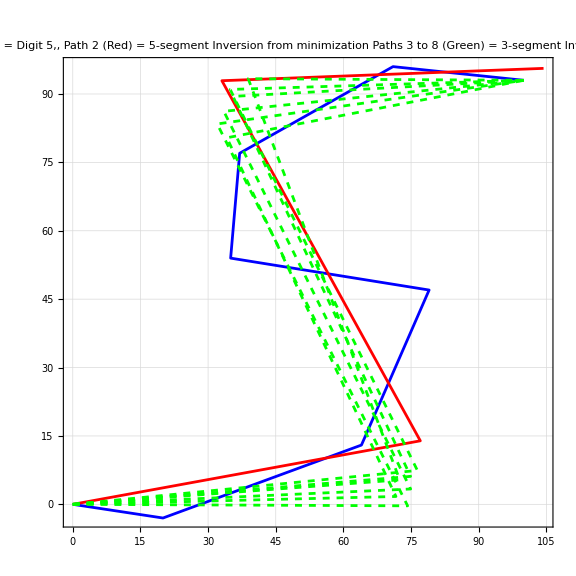

```mathematica
ListLinePlot[Prepend[Prepend[soldigit53pts,ptsminim3digit5],digit5],
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->Prepend[Prepend[ConstantArray[{Dashed,Green},Length[soldigit53pts]],{Red}],{Blue}],
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 (Blue) = Digit 5,,
Path 2 (Red) = 5-segment Inversion from minimization
Paths 3 to 8 (Green) = 3-segment Inversions from dropping equations]"],16]]
```

#### 4+ segments

```mathematica
Timing[minim5digit5=minim3lines[Flatten[chen2d5z5core],Flatten[digit5core5],weights5seg,vars5line2dchen,{},"RandomSearch"]]
```

{21.3667,{3.59493×10^8,{a_1→56.3803,a_2→24.1057,a_3→-53.9171,a_4→36.0969,a_5→48.8783,b_1→10.9248,b_2→33.0172,b_3→23.5984,b_4→30.8389,b_5→-1.55072}}}

```mathematica
ptsminim5digit5=flistab[Last[minim5digit5],{0,0}]
```

{{0,0},{56.3803,10.9248},{80.486,43.942},{26.569,67.5404},{62.6658,98.3793},{111.544,96.8285}}

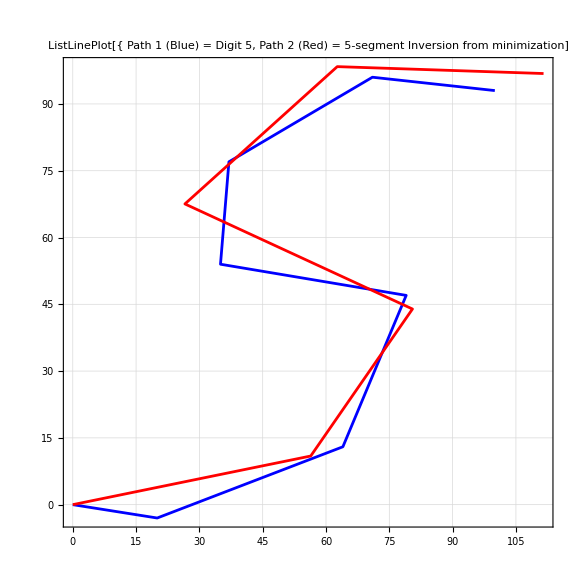

```mathematica
ListLinePlot[{digit5,ptsminim5digit5},
ImageSize->Large,GridLines->Automatic,Frame->True,
PlotRange->All,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{{Blue},{Red}},
PlotLabel->Style[Framed[
"ListLinePlot[{
Path 1 (Blue) = Digit 5,
Path 2 (Red) = 5-segment Inversion from minimization]"],16]]
```

### Circle

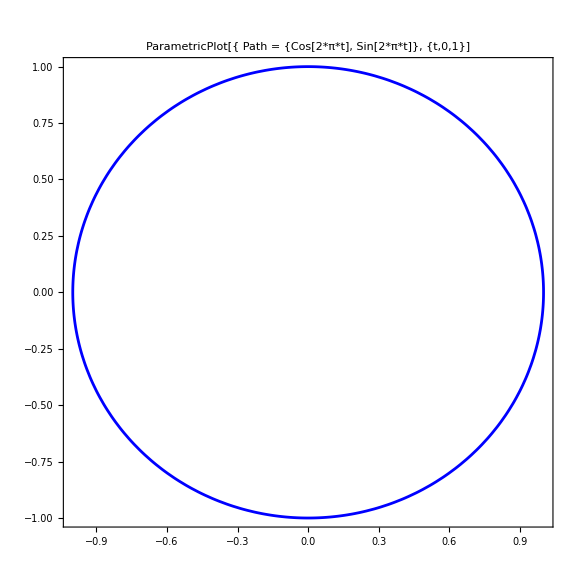

```mathematica
ParametricPlot[{Cos[2π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path = {Cos[2*π*t], Sin[2*π*t]},
 {t,0,1}]"],16]]
```

```mathematica
Timing[sigcircle5=signat[{{Cos[2π t],Sin[2π t]}},{0,1},5][[1]]]
```

{120.63,{{1},{0,0},{{0,π},{-π,0}},{{{0,-π},{2 π,0}},{{-π,0},{0,0}}},{{{{0,(5 π)/8},{-(15 π)/8,0}},{{(15 π)/8,π^2/2},{-π^2/2,π/8}}},{{{-(5 π)/8,-π^2/2},{π^2/2,-(3 π)/8}},{{0,(3 π)/8},{-π/8,0}}}},{{{{{0,-(7 π)/24},{(7 π)/6,0}},{{-(7 π)/4,-π^2/2},{π^2/2,-π/8}}},{{{(7 π)/6,π^2/2},{0,(17 π)/24}},{{-π^2/2,-(11 π)/8},{(11 π)/12,0}}}},{{{{-(7 π)/24,0},{-π^2/2,-π/3}},{{π^2/2,(4 π)/3},{-(11 π)/8,0}}},{{{0,-π/3},{(17 π)/24,0}},{{-π/8,0},{0,0}}}}}}}

```mathematica
Timing[sigcircle6=signat[{{Cos[2π t],Sin[2π t]}},{0,1},6][[1]]]
```

{450.893,{{1},{0,0},{{0,π},{-π,0}},{{{0,-π},{2 π,0}},{{-π,0},{0,0}}},{{{{0,(5 π)/8},{-(15 π)/8,0}},{{(15 π)/8,π^2/2},{-π^2/2,π/8}}},{{{-(5 π)/8,-π^2/2},{π^2/2,-(3 π)/8}},{{0,(3 π)/8},{-π/8,0}}}},{{{{{0,-(7 π)/24},{(7 π)/6,0}},{{-(7 π)/4,-π^2/2},{π^2/2,-π/8}}},{{{(7 π)/6,π^2/2},{0,(17 π)/24}},{{-π^2/2,-(11 π)/8},{(11 π)/12,0}}}},{{{{-(7 π)/24,0},{-π^2/2,-π/3}},{{π^2/2,(4 π)/3},{-(11 π)/8,0}}},{{{0,-π/3},{(17 π)/24,0}},{{-π/8,0},{0,0}}}}},{{{{{{0,(7 π)/64},{-(35 π)/64,0}},{{(35 π)/32,(5 π^2)/16},{-(5 π^2)/16,(7 π)/96}}},{{{-(35 π)/32,-(7 π^2)/16},{-π^2/16,-(21 π)/32}},{{π^2/2,(259 π)/192},{-(175 π)/192,0}}}},{{{{(35 π)/64,π^2/4},{π^2/8,(119 π)/192}},{{-π^2/16,-(7 π)/4+π^3/6},{(175 π)/96-π^3/6,π^2/16}}},{{{-(5 π^2)/16,(7 π)/16-π^3/6},{1/96 π (-175+16 π^2),-(3 π^2)/16}},{{(175 π)/192,π^2/4},{-π^2/8,π/192}}}}},{{{{{-(7 π)/64,-π^2/8},{π^2/4,-(35 π)/192}},{{-(7 π^2)/16,(35 π)/96-π^3/6},{1/48 π (-21+8 π^2),-π^2/16}}},{{{(5 π^2)/16,1/96 π (-35+16 π^2)},{(7 π)/4-π^3/6,(3 π^2)/16}},{{-(259 π)/192,-(3 π^2)/8},{π^2/4,-(5 π)/192}}}},{{{{0,(35 π)/192},{-(119 π)/192,0}},{{(21 π)/32,(3 π^2)/16},{-(3 π^2)/16,(5 π)/96}}},{{{-(7 π)/96,-π^2/16},{π^2/16,-(5 π)/96}},{{0,(5 π)/192},{-π/192,0}}}}}}}}

```mathematica
circlecore4={{sigtake[sigcircle5,{1}],sigtake[sigcircle5,{2}]},
{sigtake[sigcircle5,{1,2}]},
{sigtake[sigcircle5,{1,1,2}],sigtake[sigcircle5,{1,2,2}]},
{sigtake[sigcircle5,{1,1,1,2}],sigtake[sigcircle5,{1,1,2,2}],sigtake[sigcircle5,{1,2,2,2}]}}
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8}}

```mathematica
circlecore5={{sigtake[sigcircle5,{1}],sigtake[sigcircle5,{2}]},
{sigtake[sigcircle5,{1,2}]},
{sigtake[sigcircle5,{1,1,2}],sigtake[sigcircle5,{1,2,2}]},
{sigtake[sigcircle5,{1,1,1,2}],sigtake[sigcircle5,{1,1,2,2}],sigtake[sigcircle5,{1,2,2,2}]},
{sigtake[sigcircle5,{1,1,1,1,2}],sigtake[sigcircle5,{1,1,1,2,2}],sigtake[sigcircle5,{1,1,2,1,2}],sigtake[sigcircle5,{1,1,2,2,2}],sigtake[sigcircle5,{1,2,1,2,2}],sigtake[sigcircle5,{1,2,2,2,2}]}}
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
circlecore6={{sigtake[sigcircle6,{1}],sigtake[sigcircle6,{2}]},
{sigtake[sigcircle6,{1,2}]},
{sigtake[sigcircle6,{1,1,2}],sigtake[sigcircle6,{1,2,2}]},
{sigtake[sigcircle6,{1,1,1,2}],sigtake[sigcircle6,{1,1,2,2}],sigtake[sigcircle6,{1,2,2,2}]},
{sigtake[sigcircle6,{1,1,1,1,2}],sigtake[sigcircle6,{1,1,1,2,2}],sigtake[sigcircle6,{1,1,2,1,2}],sigtake[sigcircle6,{1,1,2,2,2}],sigtake[sigcircle6,{1,2,1,2,2}],sigtake[sigcircle6,{1,2,2,2,2}]},
{sigtake[sigcircle6,{1,1,1,1,1,2}],sigtake[sigcircle6,{1,1,1,1,2,2}],sigtake[sigcircle6,{1,1,1,2,1,2}],sigtake[sigcircle6,{1,1,1,2,2,2}],sigtake[sigcircle6,{1,1,2,1,2,2}],sigtake[sigcircle6,{1,1,2,2,1,2}],sigtake[sigcircle6,{1,1,2,2,2,2}],sigtake[sigcircle6,{1,2,1,2,2,2}],sigtake[sigcircle6,{1,2,2,2,2,2}]}}
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0},{(7 π)/64,0,(5 π^2)/16,(7 π)/96,-(21 π)/32,(259 π)/192,0,π^2/16,π/192}}

```mathematica
circlecore5
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
Timing[solcircle3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[circlecore4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.022727,{{a_1→-0.634,a_2→-1.732,a_3→2.366,b_1→2.2477,b_2→-3.7699,b_3→1.5222},{a_1→-2.366,a_2→1.732,a_3→0.634,b_1→1.522,b_2→-3.7699,b_3→2.2477}}}

```mathematica
Map[flengthpath,solcircle3]
```

{12.81,12.81}

```mathematica
Timing[solcircle3v2=solve3lines[Expand[Flatten[chen3z4core]],Flatten[circlecore4],vars3line2dchen,
{{5},{8}},{},5]]
```

{0.020837,{{a_1→-0.634,a_2→-1.732,a_3→2.366,b_1→2.2477,b_2→-3.7699,b_3→1.5222},{a_1→-2.366,a_2→1.732,a_3→0.634,b_1→1.522,b_2→-3.7699,b_3→2.2477}}}

```mathematica
Map[flengthpath,solcircle3v2]
```

{12.81,12.81}

```mathematica
Timing[solcircle3v3=solve3lines[Expand[Flatten[chen3z4core]],Flatten[circlecore4],vars3line2dchen,
{{4},{8}},{},5]]
```

{0.021226,{{a_1→-1.581,a_2→0,a_3→1.581,b_1→1.987,b_2→-3.974,b_3→1.987},{a_1→1.581,a_2→0,a_3→-1.581,b_1→-1.987,b_2→3.974,b_3→-1.987}}}

```mathematica
Map[flengthpath,solcircle3v3]
```

{12.33,12.33}

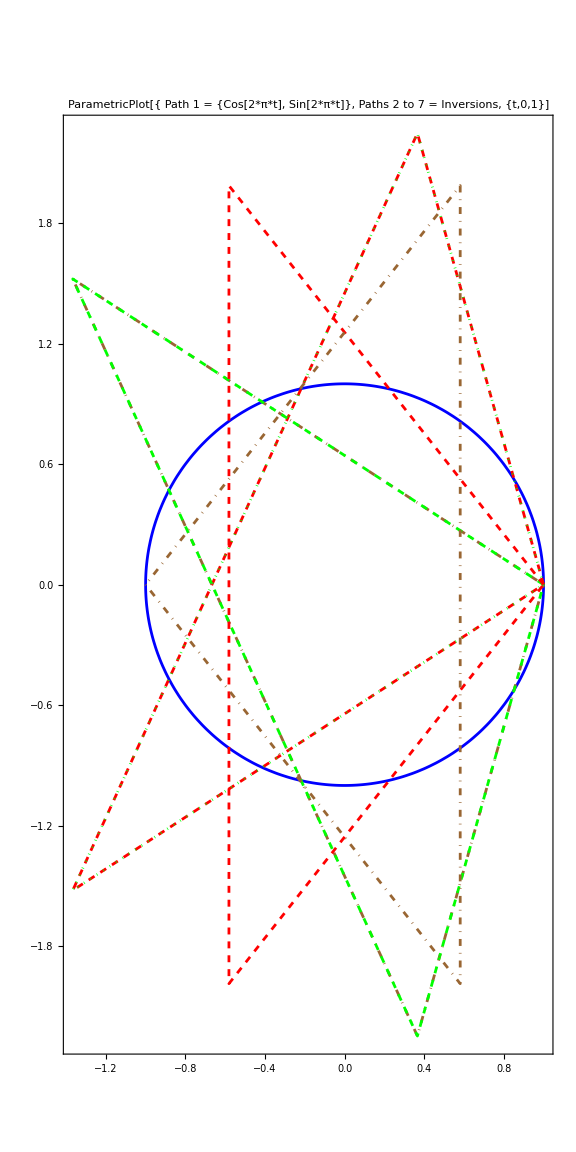

```mathematica
Show[ParametricPlot[
{Cos[2π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->2,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[2*π*t], Sin[2*π*t]},
Paths 2 to 7 = Inversions,
 {t,0,1}]"],16]],
ListLinePlot[{
flistpath[solcircle3[[1]],{1,0}],
flistpath[solcircle3[[2]],{1,0}],
flistpath[solcircle3v2[[1]],{1,0}],
flistpath[solcircle3v2[[2]],{1,0}],
flistpath[solcircle3v3[[1]],{1,0}],
flistpath[solcircle3v3[[2]],{-1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}, {Dashed,Green}}]]
```

```mathematica
{Length[Flatten[chen4z5core]],Length[Flatten[circlecore5]],Length[vars4line2dchen]}
```

{14,14,8}

```mathematica
circlecore5
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
{Length[Flatten[chen3z4core]],Length[Flatten[circlecore4]],Length[vars3line2dchen]}
```

{8,8,6}

```mathematica
{Length[Flatten[chen4z5core]],Length[Flatten[circlecore5]],Length[vars4line2dchen]}
```

{14,14,8}

```mathematica
{Length[Flatten[chen5z6core]],Length[Flatten[circlecore6]],Length[vars5line2dchen]}
```

{23,23,10}

```mathematica
eqs3lineschen2345=MapThread[Equal,{Expand[Flatten[chen3z5core]],Flatten[circlecore5]}];
```

```mathematica
eqs4lineschen2345=MapThread[Equal,{Expand[Flatten[chen4z5core]],Flatten[circlecore5]}];
```

```mathematica
Grid[Transpose[{eqs3lineschen2345}],Frame->All]
```

t_1 α_1+t_2 α_2+t_3 α_3==0
t_1 β_1+t_2 β_2+t_3 β_3==0
1/2 t_1^2 α_1 β_1+t_1 t_2 α_1 β_2+1/2 t_2^2 α_2 β_2+t_1 t_3 α_1 β_3+t_2 t_3 α_2 β_3+1/2 t_3^2 α_3 β_3==π
1/6 t_1^3 α_1^2 β_1+1/2 t_1^2 t_2 α_1^2 β_2+1/2 t_1 t_2^2 α_1 α_2 β_2+1/6 t_2^3 α_2^2 β_2+1/2 t_1^2 t_3 α_1^2 β_3+t_1 t_2 t_3 α_1 α_2 β_3+1/2 t_2^2 t_3 α_2^2 β_3+1/2 t_1 t_3^2 α_1 α_3 β_3+1/2 t_2 t_3^2 α_2 α_3 β_3+1/6 t_3^3 α_3^2 β_3==-π
1/6 t_1^3 α_1 β_1^2+1/2 t_1^2 t_2 α_1 β_1 β_2+1/2 t_1 t_2^2 α_1 β_2^2+1/6 t_2^3 α_2 β_2^2+1/2 t_1^2 t_3 α_1 β_1 β_3+t_1 t_2 t_3 α_1 β_2 β_3+1/2 t_2^2 t_3 α_2 β_2 β_3+1/2 t_1 t_3^2 α_1 β_3^2+1/2 t_2 t_3^2 α_2 β_3^2+1/6 t_3^3 α_3 β_3^2==0
1/24 t_1^4 α_1^3 β_1+1/6 t_1^3 t_2 α_1^3 β_2+1/4 t_1^2 t_2^2 α_1^2 α_2 β_2+1/6 t_1 t_2^3 α_1 α_2^2 β_2+1/24 t_2^4 α_2^3 β_2+1/6 t_1^3 t_3 α_1^3 β_3+1/2 t_1^2 t_2 t_3 α_1^2 α_2 β_3+1/2 t_1 t_2^2 t_3 α_1 α_2^2 β_3+1/6 t_2^3 t_3 α_2^3 β_3+1/4 t_1^2 t_3^2 α_1^2 α_3 β_3+1/2 t_1 t_2 t_3^2 α_1 α_2 α_3 β_3+1/4 t_2^2 t_3^2 α_2^2 α_3 β_3+1/6 t_1 t_3^3 α_1 α_3^2 β_3+1/6 t_2 t_3^3 α_2 α_3^2 β_3+1/24 t_3^4 α_3^3 β_3==(5 π)/8
1/24 t_1^4 α_1^2 β_1^2+1/6 t_1^3 t_2 α_1^2 β_1 β_2+1/4 t_1^2 t_2^2 α_1^2 β_2^2+1/6 t_1 t_2^3 α_1 α_2 β_2^2+1/24 t_2^4 α_2^2 β_2^2+1/6 t_1^3 t_3 α_1^2 β_1 β_3+1/2 t_1^2 t_2 t_3 α_1^2 β_2 β_3+1/2 t_1 t_2^2 t_3 α_1 α_2 β_2 β_3+1/6 t_2^3 t_3 α_2^2 β_2 β_3+1/4 t_1^2 t_3^2 α_1^2 β_3^2+1/2 t_1 t_2 t_3^2 α_1 α_2 β_3^2+1/4 t_2^2 t_3^2 α_2^2 β_3^2+1/6 t_1 t_3^3 α_1 α_3 β_3^2+1/6 t_2 t_3^3 α_2 α_3 β_3^2+1/24 t_3^4 α_3^2 β_3^2==0
1/24 t_1^4 α_1 β_1^3+1/6 t_1^3 t_2 α_1 β_1^2 β_2+1/4 t_1^2 t_2^2 α_1 β_1 β_2^2+1/6 t_1 t_2^3 α_1 β_2^3+1/24 t_2^4 α_2 β_2^3+1/6 t_1^3 t_3 α_1 β_1^2 β_3+1/2 t_1^2 t_2 t_3 α_1 β_1 β_2 β_3+1/2 t_1 t_2^2 t_3 α_1 β_2^2 β_3+1/6 t_2^3 t_3 α_2 β_2^2 β_3+1/4 t_1^2 t_3^2 α_1 β_1 β_3^2+1/2 t_1 t_2 t_3^2 α_1 β_2 β_3^2+1/4 t_2^2 t_3^2 α_2 β_2 β_3^2+1/6 t_1 t_3^3 α_1 β_3^3+1/6 t_2 t_3^3 α_2 β_3^3+1/24 t_3^4 α_3 β_3^3==π/8
1/120 t_1^5 α_1^4 β_1+1/24 t_1^4 t_2 α_1^4 β_2+1/12 t_1^3 t_2^2 α_1^3 α_2 β_2+1/12 t_1^2 t_2^3 α_1^2 α_2^2 β_2+1/24 t_1 t_2^4 α_1 α_2^3 β_2+1/120 t_2^5 α_2^4 β_2+1/24 t_1^4 t_3 α_1^4 β_3+1/6 t_1^3 t_2 t_3 α_1^3 α_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 α_2^2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2^3 β_3+1/24 t_2^4 t_3 α_2^4 β_3+1/12 t_1^3 t_3^2 α_1^3 α_3 β_3+1/4 t_1^2 t_2 t_3^2 α_1^2 α_2 α_3 β_3+1/4 t_1 t_2^2 t_3^2 α_1 α_2^2 α_3 β_3+1/12 t_2^3 t_3^2 α_2^3 α_3 β_3+1/12 t_1^2 t_3^3 α_1^2 α_3^2 β_3+1/6 t_1 t_2 t_3^3 α_1 α_2 α_3^2 β_3+1/12 t_2^2 t_3^3 α_2^2 α_3^2 β_3+1/24 t_1 t_3^4 α_1 α_3^3 β_3+1/24 t_2 t_3^4 α_2 α_3^3 β_3+1/120 t_3^5 α_3^4 β_3==-(7 π)/24
1/120 t_1^5 α_1^3 β_1^2+1/24 t_1^4 t_2 α_1^3 β_1 β_2+1/12 t_1^3 t_2^2 α_1^3 β_2^2+1/12 t_1^2 t_2^3 α_1^2 α_2 β_2^2+1/24 t_1 t_2^4 α_1 α_2^2 β_2^2+1/120 t_2^5 α_2^3 β_2^2+1/24 t_1^4 t_3 α_1^3 β_1 β_3+1/6 t_1^3 t_2 t_3 α_1^3 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 α_2 β_2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2^2 β_2 β_3+1/24 t_2^4 t_3 α_2^3 β_2 β_3+1/12 t_1^3 t_3^2 α_1^3 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1^2 α_2 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 α_2^2 β_3^2+1/12 t_2^3 t_3^2 α_2^3 β_3^2+1/12 t_1^2 t_3^3 α_1^2 α_3 β_3^2+1/6 t_1 t_2 t_3^3 α_1 α_2 α_3 β_3^2+1/12 t_2^2 t_3^3 α_2^2 α_3 β_3^2+1/24 t_1 t_3^4 α_1 α_3^2 β_3^2+1/24 t_2 t_3^4 α_2 α_3^2 β_3^2+1/120 t_3^5 α_3^3 β_3^2==0
1/120 t_1^5 α_1^3 β_1^2+1/24 t_1^4 t_2 α_1^3 β_1 β_2+1/12 t_1^3 t_2^2 α_1^2 α_2 β_1 β_2+1/12 t_1^2 t_2^3 α_1^2 α_2 β_2^2+1/24 t_1 t_2^4 α_1 α_2^2 β_2^2+1/120 t_2^5 α_2^3 β_2^2+1/24 t_1^4 t_3 α_1^3 β_1 β_3+1/6 t_1^3 t_2 t_3 α_1^2 α_2 β_1 β_3+1/12 t_1^3 t_3^2 α_1^2 α_3 β_1 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 α_2 β_2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2^2 β_2 β_3+1/24 t_2^4 t_3 α_2^3 β_2 β_3+1/4 t_1^2 t_2 t_3^2 α_1^2 α_3 β_2 β_3+1/4 t_1 t_2^2 t_3^2 α_1 α_2 α_3 β_2 β_3+1/12 t_2^3 t_3^2 α_2^2 α_3 β_2 β_3+1/12 t_1^2 t_3^3 α_1^2 α_3 β_3^2+1/6 t_1 t_2 t_3^3 α_1 α_2 α_3 β_3^2+1/12 t_2^2 t_3^3 α_2^2 α_3 β_3^2+1/24 t_1 t_3^4 α_1 α_3^2 β_3^2+1/24 t_2 t_3^4 α_2 α_3^2 β_3^2+1/120 t_3^5 α_3^3 β_3^2==-π^2/2
1/120 t_1^5 α_1^2 β_1^3+1/24 t_1^4 t_2 α_1^2 β_1^2 β_2+1/12 t_1^3 t_2^2 α_1^2 β_1 β_2^2+1/12 t_1^2 t_2^3 α_1^2 β_2^3+1/24 t_1 t_2^4 α_1 α_2 β_2^3+1/120 t_2^5 α_2^2 β_2^3+1/24 t_1^4 t_3 α_1^2 β_1^2 β_3+1/6 t_1^3 t_2 t_3 α_1^2 β_1 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1^2 β_2^2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2 β_2^2 β_3+1/24 t_2^4 t_3 α_2^2 β_2^2 β_3+1/12 t_1^3 t_3^2 α_1^2 β_1 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1^2 β_2 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 α_2 β_2 β_3^2+1/12 t_2^3 t_3^2 α_2^2 β_2 β_3^2+1/12 t_1^2 t_3^3 α_1^2 β_3^3+1/6 t_1 t_2 t_3^3 α_1 α_2 β_3^3+1/12 t_2^2 t_3^3 α_2^2 β_3^3+1/24 t_1 t_3^4 α_1 α_3 β_3^3+1/24 t_2 t_3^4 α_2 α_3 β_3^3+1/120 t_3^5 α_3^2 β_3^3==-π/8
1/120 t_1^5 α_1^2 β_1^3+1/24 t_1^4 t_2 α_1^2 β_1^2 β_2+1/12 t_1^3 t_2^2 α_1^2 β_1 β_2^2+1/12 t_1^2 t_2^3 α_1 α_2 β_1 β_2^2+1/24 t_1 t_2^4 α_1 α_2 β_2^3+1/120 t_2^5 α_2^2 β_2^3+1/24 t_1^4 t_3 α_1^2 β_1^2 β_3+1/6 t_1^3 t_2 t_3 α_1^2 β_1 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1 α_2 β_1 β_2 β_3+1/6 t_1 t_2^3 t_3 α_1 α_2 β_2^2 β_3+1/24 t_2^4 t_3 α_2^2 β_2^2 β_3+1/12 t_1^3 t_3^2 α_1^2 β_1 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1 α_2 β_1 β_3^2+1/12 t_1^2 t_3^3 α_1 α_3 β_1 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 α_2 β_2 β_3^2+1/12 t_2^3 t_3^2 α_2^2 β_2 β_3^2+1/6 t_1 t_2 t_3^3 α_1 α_3 β_2 β_3^2+1/12 t_2^2 t_3^3 α_2 α_3 β_2 β_3^2+1/24 t_1 t_3^4 α_1 α_3 β_3^3+1/24 t_2 t_3^4 α_2 α_3 β_3^3+1/120 t_3^5 α_3^2 β_3^3==(17 π)/24
1/120 t_1^5 α_1 β_1^4+1/24 t_1^4 t_2 α_1 β_1^3 β_2+1/12 t_1^3 t_2^2 α_1 β_1^2 β_2^2+1/12 t_1^2 t_2^3 α_1 β_1 β_2^3+1/24 t_1 t_2^4 α_1 β_2^4+1/120 t_2^5 α_2 β_2^4+1/24 t_1^4 t_3 α_1 β_1^3 β_3+1/6 t_1^3 t_2 t_3 α_1 β_1^2 β_2 β_3+1/4 t_1^2 t_2^2 t_3 α_1 β_1 β_2^2 β_3+1/6 t_1 t_2^3 t_3 α_1 β_2^3 β_3+1/24 t_2^4 t_3 α_2 β_2^3 β_3+1/12 t_1^3 t_3^2 α_1 β_1^2 β_3^2+1/4 t_1^2 t_2 t_3^2 α_1 β_1 β_2 β_3^2+1/4 t_1 t_2^2 t_3^2 α_1 β_2^2 β_3^2+1/12 t_2^3 t_3^2 α_2 β_2^2 β_3^2+1/12 t_1^2 t_3^3 α_1 β_1 β_3^3+1/6 t_1 t_2 t_3^3 α_1 β_2 β_3^3+1/12 t_2^2 t_3^3 α_2 β_2 β_3^3+1/24 t_1 t_3^4 α_1 β_3^4+1/24 t_2 t_3^4 α_2 β_3^4+1/120 t_3^5 α_3 β_3^4==0

```mathematica
Timing[solcircle4=Select[solve3lines[Expand[Flatten[chen4z5core]],Flatten[circlecore5],vars4line2dchen,
{{4},{8},{9},{12},{13},{14}},{},5],(flengthpath[#]<20)&]]
```

{0.129068,{{a_1→0.7196,a_2→-2.353,a_3→0.04134,a_4→1.592,b_1→-0.597,b_2→2.409,b_3→-3.691,b_4→1.879},{a_1→-1.419,a_2→-0.5167,a_3→4.538,a_4→-2.602,b_1→1.402,b_2→-2.443,b_3→1.362,b_4→-0.3199},{a_1→-0.634,a_2→-1.732,a_3→1.732,a_4→0.634,b_1→1.328,b_2→-1.328,b_3→-1.327,b_4→1.328}}}

```mathematica
Map[flengthpath,solcircle4]
```

{16.63,17.61,9.}

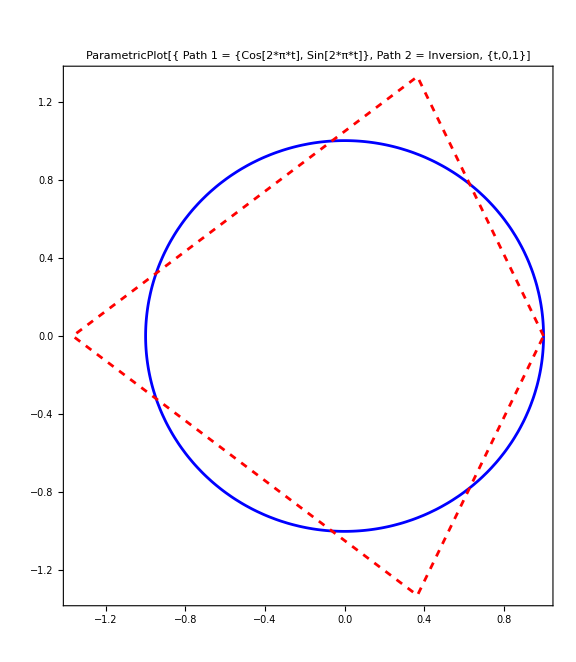

```mathematica
Show[ParametricPlot[
{Cos[2π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,AspectRatio->1.15,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue},
PlotLabel->Style[Framed[
"ParametricPlot[{
Path 1 = {Cos[2*π*t], Sin[2*π*t]},
Path 2 = Inversion,
 {t,0,1}]"],16]],
ListLinePlot[{(*
flistpath[solcircle4[[1]],{1,0}],
flistpath[solcircle4[[2]],{1,0}],*)
flistpath[solcircle4[[3]],{1,0}]},
PlotStyle->{ {Dashed,Red}, {DotDashed,Brown}, {Dotted,Green}}]]
```

```mathematica
{Length[Flatten[chen5z5core]],Length[Flatten[circlecore5]],Length[vars5line2dchen]}
```

{14,14,10}

```mathematica
circlecore5
```

{{0,0},{π},{-π,0},{(5 π)/8,0,π/8},{-(7 π)/24,0,-π^2/2,-π/8,(17 π)/24,0}}

```mathematica
eqs5lineschen2345=MapThread[Equal,{Expand[Flatten[chen5z5core]],Flatten[circlecore5]}];
```

```mathematica
Grid[Transpose[{eqs5lineschen2345}],Frame->All]
```

a_1+a_2+a_3+a_4+a_5==0
b_1+b_2+b_3+b_4+b_5==0
(a_1 b_1)/2+a_1 b_2+(a_2 b_2)/2+a_1 b_3+a_2 b_3+(a_3 b_3)/2+a_1 b_4+a_2 b_4+a_3 b_4+(a_4 b_4)/2+a_1 b_5+a_2 b_5+a_3 b_5+a_4 b_5+(a_5 b_5)/2==π
1/6 a_1^2 b_1+1/2 a_1^2 b_2+1/2 a_1 a_2 b_2+1/6 a_2^2 b_2+1/2 a_1^2 b_3+a_1 a_2 b_3+1/2 a_2^2 b_3+1/2 a_1 a_3 b_3+1/2 a_2 a_3 b_3+1/6 a_3^2 b_3+1/2 a_1^2 b_4+a_1 a_2 b_4+1/2 a_2^2 b_4+a_1 a_3 b_4+a_2 a_3 b_4+1/2 a_3^2 b_4+1/2 a_1 a_4 b_4+1/2 a_2 a_4 b_4+1/2 a_3 a_4 b_4+1/6 a_4^2 b_4+1/2 a_1^2 b_5+a_1 a_2 b_5+1/2 a_2^2 b_5+a_1 a_3 b_5+a_2 a_3 b_5+1/2 a_3^2 b_5+a_1 a_4 b_5+a_2 a_4 b_5+a_3 a_4 b_5+1/2 a_4^2 b_5+1/2 a_1 a_5 b_5+1/2 a_2 a_5 b_5+1/2 a_3 a_5 b_5+1/2 a_4 a_5 b_5+1/6 a_5^2 b_5==-π
1/6 a_1 b_1^2+1/2 a_1 b_1 b_2+1/2 a_1 b_2^2+1/6 a_2 b_2^2+1/2 a_1 b_1 b_3+a_1 b_2 b_3+1/2 a_2 b_2 b_3+1/2 a_1 b_3^2+1/2 a_2 b_3^2+1/6 a_3 b_3^2+1/2 a_1 b_1 b_4+a_1 b_2 b_4+1/2 a_2 b_2 b_4+a_1 b_3 b_4+a_2 b_3 b_4+1/2 a_3 b_3 b_4+1/2 a_1 b_4^2+1/2 a_2 b_4^2+1/2 a_3 b_4^2+1/6 a_4 b_4^2+1/2 a_1 b_1 b_5+a_1 b_2 b_5+1/2 a_2 b_2 b_5+a_1 b_3 b_5+a_2 b_3 b_5+1/2 a_3 b_3 b_5+a_1 b_4 b_5+a_2 b_4 b_5+a_3 b_4 b_5+1/2 a_4 b_4 b_5+1/2 a_1 b_5^2+1/2 a_2 b_5^2+1/2 a_3 b_5^2+1/2 a_4 b_5^2+1/6 a_5 b_5^2==0
1/24 a_1^3 b_1+1/6 a_1^3 b_2+1/4 a_1^2 a_2 b_2+1/6 a_1 a_2^2 b_2+1/24 a_2^3 b_2+1/6 a_1^3 b_3+1/2 a_1^2 a_2 b_3+1/2 a_1 a_2^2 b_3+1/6 a_2^3 b_3+1/4 a_1^2 a_3 b_3+1/2 a_1 a_2 a_3 b_3+1/4 a_2^2 a_3 b_3+1/6 a_1 a_3^2 b_3+1/6 a_2 a_3^2 b_3+1/24 a_3^3 b_3+1/6 a_1^3 b_4+1/2 a_1^2 a_2 b_4+1/2 a_1 a_2^2 b_4+1/6 a_2^3 b_4+1/2 a_1^2 a_3 b_4+a_1 a_2 a_3 b_4+1/2 a_2^2 a_3 b_4+1/2 a_1 a_3^2 b_4+1/2 a_2 a_3^2 b_4+1/6 a_3^3 b_4+1/4 a_1^2 a_4 b_4+1/2 a_1 a_2 a_4 b_4+1/4 a_2^2 a_4 b_4+1/2 a_1 a_3 a_4 b_4+1/2 a_2 a_3 a_4 b_4+1/4 a_3^2 a_4 b_4+1/6 a_1 a_4^2 b_4+1/6 a_2 a_4^2 b_4+1/6 a_3 a_4^2 b_4+1/24 a_4^3 b_4+1/6 a_1^3 b_5+1/2 a_1^2 a_2 b_5+1/2 a_1 a_2^2 b_5+1/6 a_2^3 b_5+1/2 a_1^2 a_3 b_5+a_1 a_2 a_3 b_5+1/2 a_2^2 a_3 b_5+1/2 a_1 a_3^2 b_5+1/2 a_2 a_3^2 b_5+1/6 a_3^3 b_5+1/2 a_1^2 a_4 b_5+a_1 a_2 a_4 b_5+1/2 a_2^2 a_4 b_5+a_1 a_3 a_4 b_5+a_2 a_3 a_4 b_5+1/2 a_3^2 a_4 b_5+1/2 a_1 a_4^2 b_5+1/2 a_2 a_4^2 b_5+1/2 a_3 a_4^2 b_5+1/6 a_4^3 b_5+1/4 a_1^2 a_5 b_5+1/2 a_1 a_2 a_5 b_5+1/4 a_2^2 a_5 b_5+1/2 a_1 a_3 a_5 b_5+1/2 a_2 a_3 a_5 b_5+1/4 a_3^2 a_5 b_5+1/2 a_1 a_4 a_5 b_5+1/2 a_2 a_4 a_5 b_5+1/2 a_3 a_4 a_5 b_5+1/4 a_4^2 a_5 b_5+1/6 a_1 a_5^2 b_5+1/6 a_2 a_5^2 b_5+1/6 a_3 a_5^2 b_5+1/6 a_4 a_5^2 b_5+1/24 a_5^3 b_5==(5 π)/8
1/24 a_1^2 b_1^2+1/6 a_1^2 b_1 b_2+1/4 a_1^2 b_2^2+1/6 a_1 a_2 b_2^2+1/24 a_2^2 b_2^2+1/6 a_1^2 b_1 b_3+1/2 a_1^2 b_2 b_3+1/2 a_1 a_2 b_2 b_3+1/6 a_2^2 b_2 b_3+1/4 a_1^2 b_3^2+1/2 a_1 a_2 b_3^2+1/4 a_2^2 b_3^2+1/6 a_1 a_3 b_3^2+1/6 a_2 a_3 b_3^2+1/24 a_3^2 b_3^2+1/6 a_1^2 b_1 b_4+1/2 a_1^2 b_2 b_4+1/2 a_1 a_2 b_2 b_4+1/6 a_2^2 b_2 b_4+1/2 a_1^2 b_3 b_4+a_1 a_2 b_3 b_4+1/2 a_2^2 b_3 b_4+1/2 a_1 a_3 b_3 b_4+1/2 a_2 a_3 b_3 b_4+1/6 a_3^2 b_3 b_4+1/4 a_1^2 b_4^2+1/2 a_1 a_2 b_4^2+1/4 a_2^2 b_4^2+1/2 a_1 a_3 b_4^2+1/2 a_2 a_3 b_4^2+1/4 a_3^2 b_4^2+1/6 a_1 a_4 b_4^2+1/6 a_2 a_4 b_4^2+1/6 a_3 a_4 b_4^2+1/24 a_4^2 b_4^2+1/6 a_1^2 b_1 b_5+1/2 a_1^2 b_2 b_5+1/2 a_1 a_2 b_2 b_5+1/6 a_2^2 b_2 b_5+1/2 a_1^2 b_3 b_5+a_1 a_2 b_3 b_5+1/2 a_2^2 b_3 b_5+1/2 a_1 a_3 b_3 b_5+1/2 a_2 a_3 b_3 b_5+1/6 a_3^2 b_3 b_5+1/2 a_1^2 b_4 b_5+a_1 a_2 b_4 b_5+1/2 a_2^2 b_4 b_5+a_1 a_3 b_4 b_5+a_2 a_3 b_4 b_5+1/2 a_3^2 b_4 b_5+1/2 a_1 a_4 b_4 b_5+1/2 a_2 a_4 b_4 b_5+1/2 a_3 a_4 b_4 b_5+1/6 a_4^2 b_4 b_5+1/4 a_1^2 b_5^2+1/2 a_1 a_2 b_5^2+1/4 a_2^2 b_5^2+1/2 a_1 a_3 b_5^2+1/2 a_2 a_3 b_5^2+1/4 a_3^2 b_5^2+1/2 a_1 a_4 b_5^2+1/2 a_2 a_4 b_5^2+1/2 a_3 a_4 b_5^2+1/4 a_4^2 b_5^2+1/6 a_1 a_5 b_5^2+1/6 a_2 a_5 b_5^2+1/6 a_3 a_5 b_5^2+1/6 a_4 a_5 b_5^2+1/24 a_5^2 b_5^2==0
1/24 a_1 b_1^3+1/6 a_1 b_1^2 b_2+1/4 a_1 b_1 b_2^2+1/6 a_1 b_2^3+1/24 a_2 b_2^3+1/6 a_1 b_1^2 b_3+1/2 a_1 b_1 b_2 b_3+1/2 a_1 b_2^2 b_3+1/6 a_2 b_2^2 b_3+1/4 a_1 b_1 b_3^2+1/2 a_1 b_2 b_3^2+1/4 a_2 b_2 b_3^2+1/6 a_1 b_3^3+1/6 a_2 b_3^3+1/24 a_3 b_3^3+1/6 a_1 b_1^2 b_4+1/2 a_1 b_1 b_2 b_4+1/2 a_1 b_2^2 b_4+1/6 a_2 b_2^2 b_4+1/2 a_1 b_1 b_3 b_4+a_1 b_2 b_3 b_4+1/2 a_2 b_2 b_3 b_4+1/2 a_1 b_3^2 b_4+1/2 a_2 b_3^2 b_4+1/6 a_3 b_3^2 b_4+1/4 a_1 b_1 b_4^2+1/2 a_1 b_2 b_4^2+1/4 a_2 b_2 b_4^2+1/2 a_1 b_3 b_4^2+1/2 a_2 b_3 b_4^2+1/4 a_3 b_3 b_4^2+1/6 a_1 b_4^3+1/6 a_2 b_4^3+1/6 a_3 b_4^3+1/24 a_4 b_4^3+1/6 a_1 b_1^2 b_5+1/2 a_1 b_1 b_2 b_5+1/2 a_1 b_2^2 b_5+1/6 a_2 b_2^2 b_5+1/2 a_1 b_1 b_3 b_5+a_1 b_2 b_3 b_5+1/2 a_2 b_2 b_3 b_5+1/2 a_1 b_3^2 b_5+1/2 a_2 b_3^2 b_5+1/6 a_3 b_3^2 b_5+1/2 a_1 b_1 b_4 b_5+a_1 b_2 b_4 b_5+1/2 a_2 b_2 b_4 b_5+a_1 b_3 b_4 b_5+a_2 b_3 b_4 b_5+1/2 a_3 b_3 b_4 b_5+1/2 a_1 b_4^2 b_5+1/2 a_2 b_4^2 b_5+1/2 a_3 b_4^2 b_5+1/6 a_4 b_4^2 b_5+1/4 a_1 b_1 b_5^2+1/2 a_1 b_2 b_5^2+1/4 a_2 b_2 b_5^2+1/2 a_1 b_3 b_5^2+1/2 a_2 b_3 b_5^2+1/4 a_3 b_3 b_5^2+1/2 a_1 b_4 b_5^2+1/2 a_2 b_4 b_5^2+1/2 a_3 b_4 b_5^2+1/4 a_4 b_4 b_5^2+1/6 a_1 b_5^3+1/6 a_2 b_5^3+1/6 a_3 b_5^3+1/6 a_4 b_5^3+1/24 a_5 b_5^3==π/8
1/120 a_1^4 b_1+1/24 a_1^4 b_2+1/12 a_1^3 a_2 b_2+1/12 a_1^2 a_2^2 b_2+1/24 a_1 a_2^3 b_2+1/120 a_2^4 b_2+1/24 a_1^4 b_3+1/6 a_1^3 a_2 b_3+1/4 a_1^2 a_2^2 b_3+1/6 a_1 a_2^3 b_3+1/24 a_2^4 b_3+1/12 a_1^3 a_3 b_3+1/4 a_1^2 a_2 a_3 b_3+1/4 a_1 a_2^2 a_3 b_3+1/12 a_2^3 a_3 b_3+1/12 a_1^2 a_3^2 b_3+1/6 a_1 a_2 a_3^2 b_3+1/12 a_2^2 a_3^2 b_3+1/24 a_1 a_3^3 b_3+1/24 a_2 a_3^3 b_3+1/120 a_3^4 b_3+1/24 a_1^4 b_4+1/6 a_1^3 a_2 b_4+1/4 a_1^2 a_2^2 b_4+1/6 a_1 a_2^3 b_4+1/24 a_2^4 b_4+1/6 a_1^3 a_3 b_4+1/2 a_1^2 a_2 a_3 b_4+1/2 a_1 a_2^2 a_3 b_4+1/6 a_2^3 a_3 b_4+1/4 a_1^2 a_3^2 b_4+1/2 a_1 a_2 a_3^2 b_4+1/4 a_2^2 a_3^2 b_4+1/6 a_1 a_3^3 b_4+1/6 a_2 a_3^3 b_4+1/24 a_3^4 b_4+1/12 a_1^3 a_4 b_4+1/4 a_1^2 a_2 a_4 b_4+1/4 a_1 a_2^2 a_4 b_4+1/12 a_2^3 a_4 b_4+1/4 a_1^2 a_3 a_4 b_4+1/2 a_1 a_2 a_3 a_4 b_4+1/4 a_2^2 a_3 a_4 b_4+1/4 a_1 a_3^2 a_4 b_4+1/4 a_2 a_3^2 a_4 b_4+1/12 a_3^3 a_4 b_4+1/12 a_1^2 a_4^2 b_4+1/6 a_1 a_2 a_4^2 b_4+1/12 a_2^2 a_4^2 b_4+1/6 a_1 a_3 a_4^2 b_4+1/6 a_2 a_3 a_4^2 b_4+1/12 a_3^2 a_4^2 b_4+1/24 a_1 a_4^3 b_4+1/24 a_2 a_4^3 b_4+1/24 a_3 a_4^3 b_4+1/120 a_4^4 b_4+1/24 a_1^4 b_5+1/6 a_1^3 a_2 b_5+1/4 a_1^2 a_2^2 b_5+1/6 a_1 a_2^3 b_5+1/24 a_2^4 b_5+1/6 a_1^3 a_3 b_5+1/2 a_1^2 a_2 a_3 b_5+1/2 a_1 a_2^2 a_3 b_5+1/6 a_2^3 a_3 b_5+1/4 a_1^2 a_3^2 b_5+1/2 a_1 a_2 a_3^2 b_5+1/4 a_2^2 a_3^2 b_5+1/6 a_1 a_3^3 b_5+1/6 a_2 a_3^3 b_5+1/24 a_3^4 b_5+1/6 a_1^3 a_4 b_5+1/2 a_1^2 a_2 a_4 b_5+1/2 a_1 a_2^2 a_4 b_5+1/6 a_2^3 a_4 b_5+1/2 a_1^2 a_3 a_4 b_5+a_1 a_2 a_3 a_4 b_5+1/2 a_2^2 a_3 a_4 b_5+1/2 a_1 a_3^2 a_4 b_5+1/2 a_2 a_3^2 a_4 b_5+1/6 a_3^3 a_4 b_5+1/4 a_1^2 a_4^2 b_5+1/2 a_1 a_2 a_4^2 b_5+1/4 a_2^2 a_4^2 b_5+1/2 a_1 a_3 a_4^2 b_5+1/2 a_2 a_3 a_4^2 b_5+1/4 a_3^2 a_4^2 b_5+1/6 a_1 a_4^3 b_5+1/6 a_2 a_4^3 b_5+1/6 a_3 a_4^3 b_5+1/24 a_4^4 b_5+1/12 a_1^3 a_5 b_5+1/4 a_1^2 a_2 a_5 b_5+1/4 a_1 a_2^2 a_5 b_5+1/12 a_2^3 a_5 b_5+1/4 a_1^2 a_3 a_5 b_5+1/2 a_1 a_2 a_3 a_5 b_5+1/4 a_2^2 a_3 a_5 b_5+1/4 a_1 a_3^2 a_5 b_5+1/4 a_2 a_3^2 a_5 b_5+1/12 a_3^3 a_5 b_5+1/4 a_1^2 a_4 a_5 b_5+1/2 a_1 a_2 a_4 a_5 b_5+1/4 a_2^2 a_4 a_5 b_5+1/2 a_1 a_3 a_4 a_5 b_5+1/2 a_2 a_3 a_4 a_5 b_5+1/4 a_3^2 a_4 a_5 b_5+1/4 a_1 a_4^2 a_5 b_5+1/4 a_2 a_4^2 a_5 b_5+1/4 a_3 a_4^2 a_5 b_5+1/12 a_4^3 a_5 b_5+1/12 a_1^2 a_5^2 b_5+1/6 a_1 a_2 a_5^2 b_5+1/12 a_2^2 a_5^2 b_5+1/6 a_1 a_3 a_5^2 b_5+1/6 a_2 a_3 a_5^2 b_5+1/12 a_3^2 a_5^2 b_5+1/6 a_1 a_4 a_5^2 b_5+1/6 a_2 a_4 a_5^2 b_5+1/6 a_3 a_4 a_5^2 b_5+1/12 a_4^2 a_5^2 b_5+1/24 a_1 a_5^3 b_5+1/24 a_2 a_5^3 b_5+1/24 a_3 a_5^3 b_5+1/24 a_4 a_5^3 b_5+1/120 a_5^4 b_5==-(7 π)/24
1/120 a_1^3 b_1^2+1/24 a_1^3 b_1 b_2+1/12 a_1^3 b_2^2+1/12 a_1^2 a_2 b_2^2+1/24 a_1 a_2^2 b_2^2+1/120 a_2^3 b_2^2+1/24 a_1^3 b_1 b_3+1/6 a_1^3 b_2 b_3+1/4 a_1^2 a_2 b_2 b_3+1/6 a_1 a_2^2 b_2 b_3+1/24 a_2^3 b_2 b_3+1/12 a_1^3 b_3^2+1/4 a_1^2 a_2 b_3^2+1/4 a_1 a_2^2 b_3^2+1/12 a_2^3 b_3^2+1/12 a_1^2 a_3 b_3^2+1/6 a_1 a_2 a_3 b_3^2+1/12 a_2^2 a_3 b_3^2+1/24 a_1 a_3^2 b_3^2+1/24 a_2 a_3^2 b_3^2+1/120 a_3^3 b_3^2+1/24 a_1^3 b_1 b_4+1/6 a_1^3 b_2 b_4+1/4 a_1^2 a_2 b_2 b_4+1/6 a_1 a_2^2 b_2 b_4+1/24 a_2^3 b_2 b_4+1/6 a_1^3 b_3 b_4+1/2 a_1^2 a_2 b_3 b_4+1/2 a_1 a_2^2 b_3 b_4+1/6 a_2^3 b_3 b_4+1/4 a_1^2 a_3 b_3 b_4+1/2 a_1 a_2 a_3 b_3 b_4+1/4 a_2^2 a_3 b_3 b_4+1/6 a_1 a_3^2 b_3 b_4+1/6 a_2 a_3^2 b_3 b_4+1/24 a_3^3 b_3 b_4+1/12 a_1^3 b_4^2+1/4 a_1^2 a_2 b_4^2+1/4 a_1 a_2^2 b_4^2+1/12 a_2^3 b_4^2+1/4 a_1^2 a_3 b_4^2+1/2 a_1 a_2 a_3 b_4^2+1/4 a_2^2 a_3 b_4^2+1/4 a_1 a_3^2 b_4^2+1/4 a_2 a_3^2 b_4^2+1/12 a_3^3 b_4^2+1/12 a_1^2 a_4 b_4^2+1/6 a_1 a_2 a_4 b_4^2+1/12 a_2^2 a_4 b_4^2+1/6 a_1 a_3 a_4 b_4^2+1/6 a_2 a_3 a_4 b_4^2+1/12 a_3^2 a_4 b_4^2+1/24 a_1 a_4^2 b_4^2+1/24 a_2 a_4^2 b_4^2+1/24 a_3 a_4^2 b_4^2+1/120 a_4^3 b_4^2+1/24 a_1^3 b_1 b_5+1/6 a_1^3 b_2 b_5+1/4 a_1^2 a_2 b_2 b_5+1/6 a_1 a_2^2 b_2 b_5+1/24 a_2^3 b_2 b_5+1/6 a_1^3 b_3 b_5+1/2 a_1^2 a_2 b_3 b_5+1/2 a_1 a_2^2 b_3 b_5+1/6 a_2^3 b_3 b_5+1/4 a_1^2 a_3 b_3 b_5+1/2 a_1 a_2 a_3 b_3 b_5+1/4 a_2^2 a_3 b_3 b_5+1/6 a_1 a_3^2 b_3 b_5+1/6 a_2 a_3^2 b_3 b_5+1/24 a_3^3 b_3 b_5+1/6 a_1^3 b_4 b_5+1/2 a_1^2 a_2 b_4 b_5+1/2 a_1 a_2^2 b_4 b_5+1/6 a_2^3 b_4 b_5+1/2 a_1^2 a_3 b_4 b_5+a_1 a_2 a_3 b_4 b_5+1/2 a_2^2 a_3 b_4 b_5+1/2 a_1 a_3^2 b_4 b_5+1/2 a_2 a_3^2 b_4 b_5+1/6 a_3^3 b_4 b_5+1/4 a_1^2 a_4 b_4 b_5+1/2 a_1 a_2 a_4 b_4 b_5+1/4 a_2^2 a_4 b_4 b_5+1/2 a_1 a_3 a_4 b_4 b_5+1/2 a_2 a_3 a_4 b_4 b_5+1/4 a_3^2 a_4 b_4 b_5+1/6 a_1 a_4^2 b_4 b_5+1/6 a_2 a_4^2 b_4 b_5+1/6 a_3 a_4^2 b_4 b_5+1/24 a_4^3 b_4 b_5+1/12 a_1^3 b_5^2+1/4 a_1^2 a_2 b_5^2+1/4 a_1 a_2^2 b_5^2+1/12 a_2^3 b_5^2+1/4 a_1^2 a_3 b_5^2+1/2 a_1 a_2 a_3 b_5^2+1/4 a_2^2 a_3 b_5^2+1/4 a_1 a_3^2 b_5^2+1/4 a_2 a_3^2 b_5^2+1/12 a_3^3 b_5^2+1/4 a_1^2 a_4 b_5^2+1/2 a_1 a_2 a_4 b_5^2+1/4 a_2^2 a_4 b_5^2+1/2 a_1 a_3 a_4 b_5^2+1/2 a_2 a_3 a_4 b_5^2+1/4 a_3^2 a_4 b_5^2+1/4 a_1 a_4^2 b_5^2+1/4 a_2 a_4^2 b_5^2+1/4 a_3 a_4^2 b_5^2+1/12 a_4^3 b_5^2+1/12 a_1^2 a_5 b_5^2+1/6 a_1 a_2 a_5 b_5^2+1/12 a_2^2 a_5 b_5^2+1/6 a_1 a_3 a_5 b_5^2+1/6 a_2 a_3 a_5 b_5^2+1/12 a_3^2 a_5 b_5^2+1/6 a_1 a_4 a_5 b_5^2+1/6 a_2 a_4 a_5 b_5^2+1/6 a_3 a_4 a_5 b_5^2+1/12 a_4^2 a_5 b_5^2+1/24 a_1 a_5^2 b_5^2+1/24 a_2 a_5^2 b_5^2+1/24 a_3 a_5^2 b_5^2+1/24 a_4 a_5^2 b_5^2+1/120 a_5^3 b_5^2==0
1/120 a_1^3 b_1^2+1/24 a_1^3 b_1 b_2+1/12 a_1^2 a_2 b_1 b_2+1/12 a_1^2 a_2 b_2^2+1/24 a_1 a_2^2 b_2^2+1/120 a_2^3 b_2^2+1/24 a_1^3 b_1 b_3+1/6 a_1^2 a_2 b_1 b_3+1/12 a_1^2 a_3 b_1 b_3+1/4 a_1^2 a_2 b_2 b_3+1/6 a_1 a_2^2 b_2 b_3+1/24 a_2^3 b_2 b_3+1/4 a_1^2 a_3 b_2 b_3+1/4 a_1 a_2 a_3 b_2 b_3+1/12 a_2^2 a_3 b_2 b_3+1/12 a_1^2 a_3 b_3^2+1/6 a_1 a_2 a_3 b_3^2+1/12 a_2^2 a_3 b_3^2+1/24 a_1 a_3^2 b_3^2+1/24 a_2 a_3^2 b_3^2+1/120 a_3^3 b_3^2+1/24 a_1^3 b_1 b_4+1/6 a_1^2 a_2 b_1 b_4+1/6 a_1^2 a_3 b_1 b_4+1/12 a_1^2 a_4 b_1 b_4+1/4 a_1^2 a_2 b_2 b_4+1/6 a_1 a_2^2 b_2 b_4+1/24 a_2^3 b_2 b_4+1/2 a_1^2 a_3 b_2 b_4+1/2 a_1 a_2 a_3 b_2 b_4+1/6 a_2^2 a_3 b_2 b_4+1/4 a_1^2 a_4 b_2 b_4+1/4 a_1 a_2 a_4 b_2 b_4+1/12 a_2^2 a_4 b_2 b_4+1/4 a_1^2 a_3 b_3 b_4+1/2 a_1 a_2 a_3 b_3 b_4+1/4 a_2^2 a_3 b_3 b_4+1/6 a_1 a_3^2 b_3 b_4+1/6 a_2 a_3^2 b_3 b_4+1/24 a_3^3 b_3 b_4+1/4 a_1^2 a_4 b_3 b_4+1/2 a_1 a_2 a_4 b_3 b_4+1/4 a_2^2 a_4 b_3 b_4+1/4 a_1 a_3 a_4 b_3 b_4+1/4 a_2 a_3 a_4 b_3 b_4+1/12 a_3^2 a_4 b_3 b_4+1/12 a_1^2 a_4 b_4^2+1/6 a_1 a_2 a_4 b_4^2+1/12 a_2^2 a_4 b_4^2+1/6 a_1 a_3 a_4 b_4^2+1/6 a_2 a_3 a_4 b_4^2+1/12 a_3^2 a_4 b_4^2+1/24 a_1 a_4^2 b_4^2+1/24 a_2 a_4^2 b_4^2+1/24 a_3 a_4^2 b_4^2+1/120 a_4^3 b_4^2+1/24 a_1^3 b_1 b_5+1/6 a_1^2 a_2 b_1 b_5+1/6 a_1^2 a_3 b_1 b_5+1/6 a_1^2 a_4 b_1 b_5+1/12 a_1^2 a_5 b_1 b_5+1/4 a_1^2 a_2 b_2 b_5+1/6 a_1 a_2^2 b_2 b_5+1/24 a_2^3 b_2 b_5+1/2 a_1^2 a_3 b_2 b_5+1/2 a_1 a_2 a_3 b_2 b_5+1/6 a_2^2 a_3 b_2 b_5+1/2 a_1^2 a_4 b_2 b_5+1/2 a_1 a_2 a_4 b_2 b_5+1/6 a_2^2 a_4 b_2 b_5+1/4 a_1^2 a_5 b_2 b_5+1/4 a_1 a_2 a_5 b_2 b_5+1/12 a_2^2 a_5 b_2 b_5+1/4 a_1^2 a_3 b_3 b_5+1/2 a_1 a_2 a_3 b_3 b_5+1/4 a_2^2 a_3 b_3 b_5+1/6 a_1 a_3^2 b_3 b_5+1/6 a_2 a_3^2 b_3 b_5+1/24 a_3^3 b_3 b_5+1/2 a_1^2 a_4 b_3 b_5+a_1 a_2 a_4 b_3 b_5+1/2 a_2^2 a_4 b_3 b_5+1/2 a_1 a_3 a_4 b_3 b_5+1/2 a_2 a_3 a_4 b_3 b_5+1/6 a_3^2 a_4 b_3 b_5+1/4 a_1^2 a_5 b_3 b_5+1/2 a_1 a_2 a_5 b_3 b_5+1/4 a_2^2 a_5 b_3 b_5+1/4 a_1 a_3 a_5 b_3 b_5+1/4 a_2 a_3 a_5 b_3 b_5+1/12 a_3^2 a_5 b_3 b_5+1/4 a_1^2 a_4 b_4 b_5+1/2 a_1 a_2 a_4 b_4 b_5+1/4 a_2^2 a_4 b_4 b_5+1/2 a_1 a_3 a_4 b_4 b_5+1/2 a_2 a_3 a_4 b_4 b_5+1/4 a_3^2 a_4 b_4 b_5+1/6 a_1 a_4^2 b_4 b_5+1/6 a_2 a_4^2 b_4 b_5+1/6 a_3 a_4^2 b_4 b_5+1/24 a_4^3 b_4 b_5+1/4 a_1^2 a_5 b_4 b_5+1/2 a_1 a_2 a_5 b_4 b_5+1/4 a_2^2 a_5 b_4 b_5+1/2 a_1 a_3 a_5 b_4 b_5+1/2 a_2 a_3 a_5 b_4 b_5+1/4 a_3^2 a_5 b_4 b_5+1/4 a_1 a_4 a_5 b_4 b_5+1/4 a_2 a_4 a_5 b_4 b_5+1/4 a_3 a_4 a_5 b_4 b_5+1/12 a_4^2 a_5 b_4 b_5+1/12 a_1^2 a_5 b_5^2+1/6 a_1 a_2 a_5 b_5^2+1/12 a_2^2 a_5 b_5^2+1/6 a_1 a_3 a_5 b_5^2+1/6 a_2 a_3 a_5 b_5^2+1/12 a_3^2 a_5 b_5^2+1/6 a_1 a_4 a_5 b_5^2+1/6 a_2 a_4 a_5 b_5^2+1/6 a_3 a_4 a_5 b_5^2+1/12 a_4^2 a_5 b_5^2+1/24 a_1 a_5^2 b_5^2+1/24 a_2 a_5^2 b_5^2+1/24 a_3 a_5^2 b_5^2+1/24 a_4 a_5^2 b_5^2+1/120 a_5^3 b_5^2==-π^2/2
1/120 a_1^2 b_1^3+1/24 a_1^2 b_1^2 b_2+1/12 a_1^2 b_1 b_2^2+1/12 a_1^2 b_2^3+1/24 a_1 a_2 b_2^3+1/120 a_2^2 b_2^3+1/24 a_1^2 b_1^2 b_3+1/6 a_1^2 b_1 b_2 b_3+1/4 a_1^2 b_2^2 b_3+1/6 a_1 a_2 b_2^2 b_3+1/24 a_2^2 b_2^2 b_3+1/12 a_1^2 b_1 b_3^2+1/4 a_1^2 b_2 b_3^2+1/4 a_1 a_2 b_2 b_3^2+1/12 a_2^2 b_2 b_3^2+1/12 a_1^2 b_3^3+1/6 a_1 a_2 b_3^3+1/12 a_2^2 b_3^3+1/24 a_1 a_3 b_3^3+1/24 a_2 a_3 b_3^3+1/120 a_3^2 b_3^3+1/24 a_1^2 b_1^2 b_4+1/6 a_1^2 b_1 b_2 b_4+1/4 a_1^2 b_2^2 b_4+1/6 a_1 a_2 b_2^2 b_4+1/24 a_2^2 b_2^2 b_4+1/6 a_1^2 b_1 b_3 b_4+1/2 a_1^2 b_2 b_3 b_4+1/2 a_1 a_2 b_2 b_3 b_4+1/6 a_2^2 b_2 b_3 b_4+1/4 a_1^2 b_3^2 b_4+1/2 a_1 a_2 b_3^2 b_4+1/4 a_2^2 b_3^2 b_4+1/6 a_1 a_3 b_3^2 b_4+1/6 a_2 a_3 b_3^2 b_4+1/24 a_3^2 b_3^2 b_4+1/12 a_1^2 b_1 b_4^2+1/4 a_1^2 b_2 b_4^2+1/4 a_1 a_2 b_2 b_4^2+1/12 a_2^2 b_2 b_4^2+1/4 a_1^2 b_3 b_4^2+1/2 a_1 a_2 b_3 b_4^2+1/4 a_2^2 b_3 b_4^2+1/4 a_1 a_3 b_3 b_4^2+1/4 a_2 a_3 b_3 b_4^2+1/12 a_3^2 b_3 b_4^2+1/12 a_1^2 b_4^3+1/6 a_1 a_2 b_4^3+1/12 a_2^2 b_4^3+1/6 a_1 a_3 b_4^3+1/6 a_2 a_3 b_4^3+1/12 a_3^2 b_4^3+1/24 a_1 a_4 b_4^3+1/24 a_2 a_4 b_4^3+1/24 a_3 a_4 b_4^3+1/120 a_4^2 b_4^3+1/24 a_1^2 b_1^2 b_5+1/6 a_1^2 b_1 b_2 b_5+1/4 a_1^2 b_2^2 b_5+1/6 a_1 a_2 b_2^2 b_5+1/24 a_2^2 b_2^2 b_5+1/6 a_1^2 b_1 b_3 b_5+1/2 a_1^2 b_2 b_3 b_5+1/2 a_1 a_2 b_2 b_3 b_5+1/6 a_2^2 b_2 b_3 b_5+1/4 a_1^2 b_3^2 b_5+1/2 a_1 a_2 b_3^2 b_5+1/4 a_2^2 b_3^2 b_5+1/6 a_1 a_3 b_3^2 b_5+1/6 a_2 a_3 b_3^2 b_5+1/24 a_3^2 b_3^2 b_5+1/6 a_1^2 b_1 b_4 b_5+1/2 a_1^2 b_2 b_4 b_5+1/2 a_1 a_2 b_2 b_4 b_5+1/6 a_2^2 b_2 b_4 b_5+1/2 a_1^2 b_3 b_4 b_5+a_1 a_2 b_3 b_4 b_5+1/2 a_2^2 b_3 b_4 b_5+1/2 a_1 a_3 b_3 b_4 b_5+1/2 a_2 a_3 b_3 b_4 b_5+1/6 a_3^2 b_3 b_4 b_5+1/4 a_1^2 b_4^2 b_5+1/2 a_1 a_2 b_4^2 b_5+1/4 a_2^2 b_4^2 b_5+1/2 a_1 a_3 b_4^2 b_5+1/2 a_2 a_3 b_4^2 b_5+1/4 a_3^2 b_4^2 b_5+1/6 a_1 a_4 b_4^2 b_5+1/6 a_2 a_4 b_4^2 b_5+1/6 a_3 a_4 b_4^2 b_5+1/24 a_4^2 b_4^2 b_5+1/12 a_1^2 b_1 b_5^2+1/4 a_1^2 b_2 b_5^2+1/4 a_1 a_2 b_2 b_5^2+1/12 a_2^2 b_2 b_5^2+1/4 a_1^2 b_3 b_5^2+1/2 a_1 a_2 b_3 b_5^2+1/4 a_2^2 b_3 b_5^2+1/4 a_1 a_3 b_3 b_5^2+1/4 a_2 a_3 b_3 b_5^2+1/12 a_3^2 b_3 b_5^2+1/4 a_1^2 b_4 b_5^2+1/2 a_1 a_2 b_4 b_5^2+1/4 a_2^2 b_4 b_5^2+1/2 a_1 a_3 b_4 b_5^2+1/2 a_2 a_3 b_4 b_5^2+1/4 a_3^2 b_4 b_5^2+1/4 a_1 a_4 b_4 b_5^2+1/4 a_2 a_4 b_4 b_5^2+1/4 a_3 a_4 b_4 b_5^2+1/12 a_4^2 b_4 b_5^2+1/12 a_1^2 b_5^3+1/6 a_1 a_2 b_5^3+1/12 a_2^2 b_5^3+1/6 a_1 a_3 b_5^3+1/6 a_2 a_3 b_5^3+1/12 a_3^2 b_5^3+1/6 a_1 a_4 b_5^3+1/6 a_2 a_4 b_5^3+1/6 a_3 a_4 b_5^3+1/12 a_4^2 b_5^3+1/24 a_1 a_5 b_5^3+1/24 a_2 a_5 b_5^3+1/24 a_3 a_5 b_5^3+1/24 a_4 a_5 b_5^3+1/120 a_5^2 b_5^3==-π/8
1/120 a_1^2 b_1^3+1/24 a_1^2 b_1^2 b_2+1/12 a_1^2 b_1 b_2^2+1/12 a_1 a_2 b_1 b_2^2+1/24 a_1 a_2 b_2^3+1/120 a_2^2 b_2^3+1/24 a_1^2 b_1^2 b_3+1/6 a_1^2 b_1 b_2 b_3+1/4 a_1 a_2 b_1 b_2 b_3+1/6 a_1 a_2 b_2^2 b_3+1/24 a_2^2 b_2^2 b_3+1/12 a_1^2 b_1 b_3^2+1/4 a_1 a_2 b_1 b_3^2+1/12 a_1 a_3 b_1 b_3^2+1/4 a_1 a_2 b_2 b_3^2+1/12 a_2^2 b_2 b_3^2+1/6 a_1 a_3 b_2 b_3^2+1/12 a_2 a_3 b_2 b_3^2+1/24 a_1 a_3 b_3^3+1/24 a_2 a_3 b_3^3+1/120 a_3^2 b_3^3+1/24 a_1^2 b_1^2 b_4+1/6 a_1^2 b_1 b_2 b_4+1/4 a_1 a_2 b_1 b_2 b_4+1/6 a_1 a_2 b_2^2 b_4+1/24 a_2^2 b_2^2 b_4+1/6 a_1^2 b_1 b_3 b_4+1/2 a_1 a_2 b_1 b_3 b_4+1/4 a_1 a_3 b_1 b_3 b_4+1/2 a_1 a_2 b_2 b_3 b_4+1/6 a_2^2 b_2 b_3 b_4+1/2 a_1 a_3 b_2 b_3 b_4+1/4 a_2 a_3 b_2 b_3 b_4+1/6 a_1 a_3 b_3^2 b_4+1/6 a_2 a_3 b_3^2 b_4+1/24 a_3^2 b_3^2 b_4+1/12 a_1^2 b_1 b_4^2+1/4 a_1 a_2 b_1 b_4^2+1/4 a_1 a_3 b_1 b_4^2+1/12 a_1 a_4 b_1 b_4^2+1/4 a_1 a_2 b_2 b_4^2+1/12 a_2^2 b_2 b_4^2+1/2 a_1 a_3 b_2 b_4^2+1/4 a_2 a_3 b_2 b_4^2+1/6 a_1 a_4 b_2 b_4^2+1/12 a_2 a_4 b_2 b_4^2+1/4 a_1 a_3 b_3 b_4^2+1/4 a_2 a_3 b_3 b_4^2+1/12 a_3^2 b_3 b_4^2+1/6 a_1 a_4 b_3 b_4^2+1/6 a_2 a_4 b_3 b_4^2+1/12 a_3 a_4 b_3 b_4^2+1/24 a_1 a_4 b_4^3+1/24 a_2 a_4 b_4^3+1/24 a_3 a_4 b_4^3+1/120 a_4^2 b_4^3+1/24 a_1^2 b_1^2 b_5+1/6 a_1^2 b_1 b_2 b_5+1/4 a_1 a_2 b_1 b_2 b_5+1/6 a_1 a_2 b_2^2 b_5+1/24 a_2^2 b_2^2 b_5+1/6 a_1^2 b_1 b_3 b_5+1/2 a_1 a_2 b_1 b_3 b_5+1/4 a_1 a_3 b_1 b_3 b_5+1/2 a_1 a_2 b_2 b_3 b_5+1/6 a_2^2 b_2 b_3 b_5+1/2 a_1 a_3 b_2 b_3 b_5+1/4 a_2 a_3 b_2 b_3 b_5+1/6 a_1 a_3 b_3^2 b_5+1/6 a_2 a_3 b_3^2 b_5+1/24 a_3^2 b_3^2 b_5+1/6 a_1^2 b_1 b_4 b_5+1/2 a_1 a_2 b_1 b_4 b_5+1/2 a_1 a_3 b_1 b_4 b_5+1/4 a_1 a_4 b_1 b_4 b_5+1/2 a_1 a_2 b_2 b_4 b_5+1/6 a_2^2 b_2 b_4 b_5+a_1 a_3 b_2 b_4 b_5+1/2 a_2 a_3 b_2 b_4 b_5+1/2 a_1 a_4 b_2 b_4 b_5+1/4 a_2 a_4 b_2 b_4 b_5+1/2 a_1 a_3 b_3 b_4 b_5+1/2 a_2 a_3 b_3 b_4 b_5+1/6 a_3^2 b_3 b_4 b_5+1/2 a_1 a_4 b_3 b_4 b_5+1/2 a_2 a_4 b_3 b_4 b_5+1/4 a_3 a_4 b_3 b_4 b_5+1/6 a_1 a_4 b_4^2 b_5+1/6 a_2 a_4 b_4^2 b_5+1/6 a_3 a_4 b_4^2 b_5+1/24 a_4^2 b_4^2 b_5+1/12 a_1^2 b_1 b_5^2+1/4 a_1 a_2 b_1 b_5^2+1/4 a_1 a_3 b_1 b_5^2+1/4 a_1 a_4 b_1 b_5^2+1/12 a_1 a_5 b_1 b_5^2+1/4 a_1 a_2 b_2 b_5^2+1/12 a_2^2 b_2 b_5^2+1/2 a_1 a_3 b_2 b_5^2+1/4 a_2 a_3 b_2 b_5^2+1/2 a_1 a_4 b_2 b_5^2+1/4 a_2 a_4 b_2 b_5^2+1/6 a_1 a_5 b_2 b_5^2+1/12 a_2 a_5 b_2 b_5^2+1/4 a_1 a_3 b_3 b_5^2+1/4 a_2 a_3 b_3 b_5^2+1/12 a_3^2 b_3 b_5^2+1/2 a_1 a_4 b_3 b_5^2+1/2 a_2 a_4 b_3 b_5^2+1/4 a_3 a_4 b_3 b_5^2+1/6 a_1 a_5 b_3 b_5^2+1/6 a_2 a_5 b_3 b_5^2+1/12 a_3 a_5 b_3 b_5^2+1/4 a_1 a_4 b_4 b_5^2+1/4 a_2 a_4 b_4 b_5^2+1/4 a_3 a_4 b_4 b_5^2+1/12 a_4^2 b_4 b_5^2+1/6 a_1 a_5 b_4 b_5^2+1/6 a_2 a_5 b_4 b_5^2+1/6 a_3 a_5 b_4 b_5^2+1/12 a_4 a_5 b_4 b_5^2+1/24 a_1 a_5 b_5^3+1/24 a_2 a_5 b_5^3+1/24 a_3 a_5 b_5^3+1/24 a_4 a_5 b_5^3+1/120 a_5^2 b_5^3==(17 π)/24
1/120 a_1 b_1^4+1/24 a_1 b_1^3 b_2+1/12 a_1 b_1^2 b_2^2+1/12 a_1 b_1 b_2^3+1/24 a_1 b_2^4+1/120 a_2 b_2^4+1/24 a_1 b_1^3 b_3+1/6 a_1 b_1^2 b_2 b_3+1/4 a_1 b_1 b_2^2 b_3+1/6 a_1 b_2^3 b_3+1/24 a_2 b_2^3 b_3+1/12 a_1 b_1^2 b_3^2+1/4 a_1 b_1 b_2 b_3^2+1/4 a_1 b_2^2 b_3^2+1/12 a_2 b_2^2 b_3^2+1/12 a_1 b_1 b_3^3+1/6 a_1 b_2 b_3^3+1/12 a_2 b_2 b_3^3+1/24 a_1 b_3^4+1/24 a_2 b_3^4+1/120 a_3 b_3^4+1/24 a_1 b_1^3 b_4+1/6 a_1 b_1^2 b_2 b_4+1/4 a_1 b_1 b_2^2 b_4+1/6 a_1 b_2^3 b_4+1/24 a_2 b_2^3 b_4+1/6 a_1 b_1^2 b_3 b_4+1/2 a_1 b_1 b_2 b_3 b_4+1/2 a_1 b_2^2 b_3 b_4+1/6 a_2 b_2^2 b_3 b_4+1/4 a_1 b_1 b_3^2 b_4+1/2 a_1 b_2 b_3^2 b_4+1/4 a_2 b_2 b_3^2 b_4+1/6 a_1 b_3^3 b_4+1/6 a_2 b_3^3 b_4+1/24 a_3 b_3^3 b_4+1/12 a_1 b_1^2 b_4^2+1/4 a_1 b_1 b_2 b_4^2+1/4 a_1 b_2^2 b_4^2+1/12 a_2 b_2^2 b_4^2+1/4 a_1 b_1 b_3 b_4^2+1/2 a_1 b_2 b_3 b_4^2+1/4 a_2 b_2 b_3 b_4^2+1/4 a_1 b_3^2 b_4^2+1/4 a_2 b_3^2 b_4^2+1/12 a_3 b_3^2 b_4^2+1/12 a_1 b_1 b_4^3+1/6 a_1 b_2 b_4^3+1/12 a_2 b_2 b_4^3+1/6 a_1 b_3 b_4^3+1/6 a_2 b_3 b_4^3+1/12 a_3 b_3 b_4^3+1/24 a_1 b_4^4+1/24 a_2 b_4^4+1/24 a_3 b_4^4+1/120 a_4 b_4^4+1/24 a_1 b_1^3 b_5+1/6 a_1 b_1^2 b_2 b_5+1/4 a_1 b_1 b_2^2 b_5+1/6 a_1 b_2^3 b_5+1/24 a_2 b_2^3 b_5+1/6 a_1 b_1^2 b_3 b_5+1/2 a_1 b_1 b_2 b_3 b_5+1/2 a_1 b_2^2 b_3 b_5+1/6 a_2 b_2^2 b_3 b_5+1/4 a_1 b_1 b_3^2 b_5+1/2 a_1 b_2 b_3^2 b_5+1/4 a_2 b_2 b_3^2 b_5+1/6 a_1 b_3^3 b_5+1/6 a_2 b_3^3 b_5+1/24 a_3 b_3^3 b_5+1/6 a_1 b_1^2 b_4 b_5+1/2 a_1 b_1 b_2 b_4 b_5+1/2 a_1 b_2^2 b_4 b_5+1/6 a_2 b_2^2 b_4 b_5+1/2 a_1 b_1 b_3 b_4 b_5+a_1 b_2 b_3 b_4 b_5+1/2 a_2 b_2 b_3 b_4 b_5+1/2 a_1 b_3^2 b_4 b_5+1/2 a_2 b_3^2 b_4 b_5+1/6 a_3 b_3^2 b_4 b_5+1/4 a_1 b_1 b_4^2 b_5+1/2 a_1 b_2 b_4^2 b_5+1/4 a_2 b_2 b_4^2 b_5+1/2 a_1 b_3 b_4^2 b_5+1/2 a_2 b_3 b_4^2 b_5+1/4 a_3 b_3 b_4^2 b_5+1/6 a_1 b_4^3 b_5+1/6 a_2 b_4^3 b_5+1/6 a_3 b_4^3 b_5+1/24 a_4 b_4^3 b_5+1/12 a_1 b_1^2 b_5^2+1/4 a_1 b_1 b_2 b_5^2+1/4 a_1 b_2^2 b_5^2+1/12 a_2 b_2^2 b_5^2+1/4 a_1 b_1 b_3 b_5^2+1/2 a_1 b_2 b_3 b_5^2+1/4 a_2 b_2 b_3 b_5^2+1/4 a_1 b_3^2 b_5^2+1/4 a_2 b_3^2 b_5^2+1/12 a_3 b_3^2 b_5^2+1/4 a_1 b_1 b_4 b_5^2+1/2 a_1 b_2 b_4 b_5^2+1/4 a_2 b_2 b_4 b_5^2+1/2 a_1 b_3 b_4 b_5^2+1/2 a_2 b_3 b_4 b_5^2+1/4 a_3 b_3 b_4 b_5^2+1/4 a_1 b_4^2 b_5^2+1/4 a_2 b_4^2 b_5^2+1/4 a_3 b_4^2 b_5^2+1/12 a_4 b_4^2 b_5^2+1/12 a_1 b_1 b_5^3+1/6 a_1 b_2 b_5^3+1/12 a_2 b_2 b_5^3+1/6 a_1 b_3 b_5^3+1/6 a_2 b_3 b_5^3+1/12 a_3 b_3 b_5^3+1/6 a_1 b_4 b_5^3+1/6 a_2 b_4 b_5^3+1/6 a_3 b_4 b_5^3+1/12 a_4 b_4 b_5^3+1/24 a_1 b_5^4+1/24 a_2 b_5^4+1/24 a_3 b_5^4+1/24 a_4 b_5^4+1/120 a_5 b_5^4==0

```mathematica
Timing[solcircle5=solve3lines[Expand[Flatten[chen5z5core]],Flatten[circlecore5],vars5line2dchen,
{{4},{8},{14},{13}},{},2]]
```

$Aborted

### Stuff

```mathematica
solve5lines[eqsleft_,cores_,vars_,delpos_:{},bounds_:{}]:=Module[{eqs},
eqs=MapThread[Equal,{eqsleft,cores}];
NSolve[Join[Delete[eqs,delpos],bounds],vars,Reals]];
```

```mathematica
fpw5[sollist_,t_]:=Module[{α1,α2,α3,α4,α5,β1,β2,β3,β4,β5,t1,t2,t3,t4,t5},
{α1,α2,α3,α4,α5,β1,β2,β3,β4,β5,t1,t2,t3,t4,t5}=sollist;
Piecewise[{{{α1 t,β1 t}, 0≤t≤t1}, {{α1 t1+α2(t-t1),β1 t1+β2(t-t1)}, t1<t≤(t1+t2)}, {{α1 t1+α2 t2+α3(t-(t1+t2)),β1 t1+β2 t2+β3(t-(t1+t2))}, (t1+t2)<t≤(t1+t2+t3)}, {{α1 t1+α2 t2+α3 t3+α4(t-(t1+t2+t3)),β1 t1+β2 t2+β3 t3+β4(t-(t1+t2+t3))}, (t1+t2+t3)<t≤(t1+t2+t3+t4)}, {{α1 t1+α2 t2+α3 t3+α4 t4+α5(t-(t1+t2+t3+t4)),β1 t1+β2 t2+β3 t3+β4 t4+β5(t-(t1+t2+t3+t4))}, (t1+t2+t3+t4)<t≤(t1+t2+t3+t4+t5)}}]];
```

```mathematica
fpw2d3[sollist_,t_]:=Module[{a1,a2,a3,b1,b2,b3},
{a1,a2,a3,b1,b2,b3}=sollist;
Piecewise[{{{a1,b1} 3t, 0≤t≤1/3}, {{a1,b1}+{a2,b2} 3(t-1/3), 1/3<t≤2/3}, {{a1,b1}+{a2,b2}+{a3,b3} 3(t-2/3), 2/3<t≤1}}]];
```

```mathematica
fpw2d4[sollist_,t_]:=Module[{a1,a2,a3,a4,b1,b2,b3,b4},
{a1,a2,a3,a4,b1,b2,b3,b4}=sollist;
Piecewise[{{{a1,b1} 4t, 0≤t≤1/4}, {{a1,b1}+{a2,b2} 4(t-1/4), 1/4<t≤2/4}, {{a1,b1}+{a2,b2}+{a3,b3} 4(t-2/4), 2/4<t≤3/4}, {{a1,b1}+{a2,b2}+{a3,b3}+{a4,b4} 4(t-3/4), 3/4<t≤1}}]];
```

```mathematica
fpw2d4[sollist_,t_]:=Module[{a1,a2,a3,a4,a5,b1,b2,b3,b4,b5},
{a1,a2,a3,a4,a5,b1,b2,b3,b4,b5}=sollist;
Piecewise[{{{a1,b1} 5t, 0≤t≤1/5}, {{a1,b1}+{a2,b2} 5(t-1/5), 1/5<t≤2/5}, {{a1,b1}+{a2,b2}+{a3,b3} 5(t-2/5), 2/5<t≤3/5}, {{a1,b1}+{a2,b2}+{a3,b3}+{a4,b4} 5(t-3/5), 3/5<t≤4/5}, {{a1,b1}+{a2,b2}+{a3,b3}+{a4,b4}+{a5,b5} 5(t-4/5), 4/5<t≤1}}]];
```